## Implementation Of Generalized Normal Ordering based on ' brute force' permutation of density matrices.

```mathematica
(*Remove annoyances.*)
Off[ReplaceRepeated];
Off[General];
Off[ReplaceRepeated::rrlim];
Off[Part::partw]
Off[Part::partd]
Off[StringJoin::string]
```

### Explanation.

The most ‘basic’ way to do GNO is by explicitly implementing the product formulas, although because a2a1!=a1a2, that’s remarkably tedious and error prone. Another way to reach the same result will be to derive the product formulas completely from the definitions as I do here. The steps to deriving the formula for the product of MK-normal operators is:
 
a) Recursively Define the MK - normal operators as grassman products of lower rank a operators and gamma (eqns. 35a-c of MK paper) that’s what I do below.

b) Applying the definitions from a), form the product of the MK normal operators and distribute the products, obtaining an expression in terms of ONLY density tensors and ordinary a-a products which obey the normal contraction rule. Apply the contraction rule to collapse a-a products

c) Apply the inverted definition of MK-normal operators to eliminate normal a’s, now every term may contain only tilde a’s, deltas and gammas. 

d) Insert cumulant decomposition of any gammas of order greater than one and simplify. Every term then contains only gammas, deltas, cumulants and lower tilde a’s. You’re done. 

e) (optional) Collapse delta-gamma expressions into eta’s

Antisymmetry enters in two places, the cumulant decomposition of gamma’s and the definition of MK normal operators. In both cases there is a convention MK take that Tr{rho_k} = N!/(N-k)! which also depends on their definition of which products of tensors are ‘nontrivially unique’. My expressions will try to match theirs which have the nice feature that every unique term appears once and has a factor of +/- 1 once the expressions are done. 

NOTE: The following symbols CANNOT be used as indices: 
{“p”,”q”,”P”,”Q”,”Δs”,”Δt”,”VTs”,”VTt”,γ,η,δ,”Sign”,a,”B”,”M”,”L”}

p and q are actually exceptions. They are reserved for external indices. 
B,M, and L are reserved for RI integral indices.

### Step 1, Automatic definition of an MK tilde - a operator

```mathematica
Clear[ta1]
(*Lower indices always odd letters and upper always even.*)
an[n_,first_:1]:=Join[{{a,n}},{Table[FromCharacterCode[97+i],{i,first,first+2n-1,2}]},{Table[FromCharacterCode[97+i],{i,first+1,2n+first,2}]}];
γn[n_,first_:1]:=Join[{{γ,n}},{Table[FromCharacterCode[97+i],{i,first,first+2n-1,2}]},{Table[FromCharacterCode[97+i],{i,first+1,2n+first,2}]}];
FormatAnOperator[aop_]:=Subsuperscript[aop[[1,1]],Apply[List,aop[[3]]],Apply[List,aop[[2]]]];
FormatATerm[aterm_]:=aterm[[1,2]]*Product[FormatAnOperator[aterm[[i]]],{i,2,Length[aterm]}];
RecognizableForm[terms_]:=Total[Map[FormatATerm,terms]]
ta1[ui_,li_]:=Join[{{{"Sign",1},{{a,1},ui,li}},{{"Sign",-1},{{γ,1},ui,li}}}]
```

```mathematica
an[1]
```

{{a,1},{b},{c}}

```mathematica
ta1[{b},{c}]
```

{{{Sign,1},{{a,1},{b},{c}}},{{Sign,-1},{{γ,1},{b},{c}}}}

```mathematica
(*In MK's mol. phys paper this is 122*)
ta2[uis_,lis_]:=Join[{{{"Sign",1},{{a,2},uis,lis}}},Grassmann[{{γ,1},Take[uis,{1}],Take[lis,{1}]},{{ta,1},Take[uis,{2}],Take[lis,{2}]},-4],{{{"Sign",-1},{{γ,2},uis,lis}}}]
Reduce1={any1___,{{"Sign",sign1_},any5___},any4___,{{"Sign",sign2_},any5___},any6___}->{any1,{{"Sign",sign1+sign2},any5},any4,any6};
Reduce2={any1___,{{"Sign",0},any5___},any4___}->{any1,any4};
Grassmann[o1_,o2_,sign_:(-1.0)]:=Module[{t1,u1,l1,t2,u2,l2,upper,lower,pupper,plower,OuterSign},(
t1=o1[[1]];
u1=o1[[2]];
l1=o1[[3]];
t2=o2[[1]];
u2=o2[[2]];
l2=o2[[3]];
upper=Join[u1,u2];
lower=Join[l1,l2];
OuterSign=Signature[upper]*Signature[lower];
pupper=Permutations[upper];
plower=Permutations[lower];
(*Generate all Terms which permute the upper and lower indices.*)
Return[
ReplaceRepeated[
Reap[
Do[
(
fac=OuterSign*Signature[pupper[[i]]]*Signature[plower[[j]]]*sign/(Length[pupper]*Length[plower]);
nu1=Take[pupper[[i]],{1,Length[u1]}];
nu2=Take[pupper[[i]],{1,Length[u2]}+Length[u1]];
nl1=Take[plower[[j]],{1,Length[l1]}];
nl2=Take[plower[[j]],{1,Length[l2]}+Length[l1]];
(*Pre-simplify the expressions by applying antisymmetry within each tensor to bring the indices into a sorted, canonical form. This is unworkable in the spin-adapted case. *)
su1=Sort[nu1];
sl1=Sort[nl1];
su2=Sort[nu2];
sl2=Sort[nl2];
sfac=fac*Signature[nu1]*Signature[nu2]*Signature[nl1]*Signature[nl2];(*Watch out for the signature of nl HACK*) 
Sow[{{"Sign",sfac},{t1,su1,sl1},{t2,su2,sl2}}];
)
,{i,1,Length[pupper]},{j,1,Length[plower]}]
][[2,1]],{Reduce1,Reduce2},MaxIterations->20]];
)];
```

```mathematica
an[2]
```

{{a,2},{b,d},{c,e}}

```mathematica
ta2[{"b","d"},{"c","e"}]
RecognizableForm[%]
```

{{{Sign,1},{{a,2},{b,d},{c,e}}},{{Sign,-1},{{γ,1},{b},{c}},{{ta,1},{d},{e}}},{{Sign,1},{{γ,1},{b},{e}},{{ta,1},{d},{c}}},{{Sign,1},{{γ,1},{d},{c}},{{ta,1},{b},{e}}},{{Sign,-1},{{γ,1},{d},{e}},{{ta,1},{b},{c}}},{{Sign,-1},{{γ,2},{b,d},{c,e}}}}

a_{c,e}^{b,d}-ta_{e}^{d} γ_{c}^{b}+ta_{e}^{b} γ_{c}^{d}+ta_{c}^{d} γ_{e}^{b}-ta_{c}^{b} γ_{e}^{d}-γ_{c,e}^{b,d}

This is MK' s correct 126 (Mol. Phys.), Signs correct, everything.

```mathematica
ta3[uis_,lis_]:=Join[{{{"Sign",1},{{a,3},uis,lis}}},
Grassmann[{{γ,1},Take[uis,{1}],Take[lis,{1}]},{{ta,2},Take[uis,{2,3}],Take[lis,{2,3}]},-9],
Grassmann[{{γ,2},Take[uis,{1,2}],Take[lis,{1,2}]},{{ta,1},Take[uis,{3}],Take[lis,{3}]},-9],
{{{"Sign",-1},{{γ,3},uis,lis}}}]
```

```mathematica
an[3]
```

{{a,3},{b,d,f},{c,e,g}}

```mathematica
ta3[{"b","d","f"},{"c","e","g"}];
RecognizableForm[%]
Length[%]
```

a_{c,e,g}^{b,d,f}-ta_{e,g}^{d,f} γ_{c}^{b}+ta_{e,g}^{b,f} γ_{c}^{d}-ta_{e,g}^{b,d} γ_{c}^{f}+ta_{c,g}^{d,f} γ_{e}^{b}-ta_{c,g}^{b,f} γ_{e}^{d}+ta_{c,g}^{b,d} γ_{e}^{f}-ta_{c,e}^{d,f} γ_{g}^{b}+ta_{c,e}^{b,f} γ_{g}^{d}-ta_{c,e}^{b,d} γ_{g}^{f}-ta_{g}^{f} γ_{c,e}^{b,d}+ta_{g}^{d} γ_{c,e}^{b,f}-ta_{g}^{b} γ_{c,e}^{d,f}+ta_{e}^{f} γ_{c,g}^{b,d}-ta_{e}^{d} γ_{c,g}^{b,f}+ta_{e}^{b} γ_{c,g}^{d,f}-ta_{c}^{f} γ_{e,g}^{b,d}+ta_{c}^{d} γ_{e,g}^{b,f}-ta_{c}^{b} γ_{e,g}^{d,f}-γ_{c,e,g}^{b,d,f}

20

This should be MK' s correct 127 from the Mol Phys paper. Check my signs by comparing with eq. 27 (JCP). Definition of the rank-4 tilde operator takes about a minute to compute. It’s neccesary to do double-double products (actually I think we also need the fifth to accurately do single-double-double products although the terms from a5 should all die in the expectation value.

```mathematica
ta4[uis_,lis_]:=Join[{{{"Sign",1},{{a,4},uis,lis}}},
Grassmann[{{γ,1},Take[uis,{1}],Take[lis,{1}]},{{ta,3},Take[uis,{2,4}],Take[lis,{2,4}]},-16],Grassmann[{{γ,2},Take[uis,Range[2]],Take[lis,Range[2]]},{{ta,2},Take[uis,{3,4}],Take[lis,{3,4}]},-36],
Grassmann[{{γ,3},Take[uis,{1,3}],Take[lis,{1,3}]},{{ta,1},Take[uis,{4}],Take[lis,{4}]},-16],
{{{"Sign",-1},{{γ,4},uis,lis}}}];
```

```mathematica
an[4]
```

{{a,4},{b,d,f,h},{c,e,g,i}}

```mathematica
tmp=ta4[{"b","d","f","h"},{"c","e","g","i"}];
Length[tmp]
RecognizableForm[tmp]
Length[RecognizableForm[tmp]]
```

1670

a_{c,e,g,i}^{b,d,f,h}-ta_{e,g,i}^{d,f,h} γ_{c}^{b}+ta_{e,g,i}^{b,f,h} γ_{c}^{d}-ta_{e,g,i}^{b,d,h} γ_{c}^{f}+ta_{e,g,i}^{b,d,f} γ_{c}^{h}+ta_{c,g,i}^{d,f,h} γ_{e}^{b}-ta_{c,g,i}^{b,f,h} γ_{e}^{d}+ta_{c,g,i}^{b,d,h} γ_{e}^{f}-ta_{c,g,i}^{b,d,f} γ_{e}^{h}-ta_{c,e,i}^{d,f,h} γ_{g}^{b}+ta_{c,e,i}^{b,f,h} γ_{g}^{d}-ta_{c,e,i}^{b,d,h} γ_{g}^{f}+ta_{c,e,i}^{b,d,f} γ_{g}^{h}+ta_{c,e,g}^{d,f,h} γ_{i}^{b}-ta_{c,e,g}^{b,f,h} γ_{i}^{d}+ta_{c,e,g}^{b,d,h} γ_{i}^{f}-ta_{c,e,g}^{b,d,f} γ_{i}^{h}-ta_{g,i}^{f,h} γ_{c,e}^{b,d}+ta_{g,i}^{d,h} γ_{c,e}^{b,f}-ta_{g,i}^{d,f} γ_{c,e}^{b,h}-ta_{g,i}^{b,h} γ_{c,e}^{d,f}+ta_{g,i}^{b,f} γ_{c,e}^{d,h}-ta_{g,i}^{b,d} γ_{c,e}^{f,h}+ta_{e,i}^{f,h} γ_{c,g}^{b,d}-ta_{e,i}^{d,h} γ_{c,g}^{b,f}+ta_{e,i}^{d,f} γ_{c,g}^{b,h}+ta_{e,i}^{b,h} γ_{c,g}^{d,f}-ta_{e,i}^{b,f} γ_{c,g}^{d,h}+ta_{e,i}^{b,d} γ_{c,g}^{f,h}-ta_{e,g}^{f,h} γ_{c,i}^{b,d}+ta_{e,g}^{d,h} γ_{c,i}^{b,f}-ta_{e,g}^{d,f} γ_{c,i}^{b,h}-ta_{e,g}^{b,h} γ_{c,i}^{d,f}+ta_{e,g}^{b,f} γ_{c,i}^{d,h}-ta_{e,g}^{b,d} γ_{c,i}^{f,h}-ta_{c,i}^{f,h} γ_{e,g}^{b,d}+ta_{c,i}^{d,h} γ_{e,g}^{b,f}-ta_{c,i}^{d,f} γ_{e,g}^{b,h}-ta_{c,i}^{b,h} γ_{e,g}^{d,f}+ta_{c,i}^{b,f} γ_{e,g}^{d,h}-ta_{c,i}^{b,d} γ_{e,g}^{f,h}+ta_{c,g}^{f,h} γ_{e,i}^{b,d}-ta_{c,g}^{d,h} γ_{e,i}^{b,f}+ta_{c,g}^{d,f} γ_{e,i}^{b,h}+ta_{c,g}^{b,h} γ_{e,i}^{d,f}-ta_{c,g}^{b,f} γ_{e,i}^{d,h}+ta_{c,g}^{b,d} γ_{e,i}^{f,h}-ta_{c,e}^{f,h} γ_{g,i}^{b,d}+ta_{c,e}^{d,h} γ_{g,i}^{b,f}-ta_{c,e}^{d,f} γ_{g,i}^{b,h}-ta_{c,e}^{b,h} γ_{g,i}^{d,f}+ta_{c,e}^{b,f} γ_{g,i}^{d,h}-ta_{c,e}^{b,d} γ_{g,i}^{f,h}-ta_{i}^{h} γ_{c,e,g}^{b,d,f}+ta_{i}^{f} γ_{c,e,g}^{b,d,h}-ta_{i}^{d} γ_{c,e,g}^{b,f,h}+ta_{i}^{b} γ_{c,e,g}^{d,f,h}+ta_{g}^{h} γ_{c,e,i}^{b,d,f}-ta_{g}^{f} γ_{c,e,i}^{b,d,h}+ta_{g}^{d} γ_{c,e,i}^{b,f,h}-ta_{g}^{b} γ_{c,e,i}^{d,f,h}-ta_{e}^{h} γ_{c,g,i}^{b,d,f}+ta_{e}^{f} γ_{c,g,i}^{b,d,h}-ta_{e}^{d} γ_{c,g,i}^{b,f,h}+ta_{e}^{b} γ_{c,g,i}^{d,f,h}+ta_{c}^{h} γ_{e,g,i}^{b,d,f}-ta_{c}^{f} γ_{e,g,i}^{b,d,h}+ta_{c}^{d} γ_{e,g,i}^{b,f,h}-ta_{c}^{b} γ_{e,g,i}^{d,f,h}-γ_{c,e,g,i}^{b,d,f,h}

70

This is MK’s expression (128) from the Mol. Phys paper with the correct number of terms. (factors must be checked but I believe them to be correct.) We need two additional things worked out in the next two sections. At Rank 5 the intermediate expression have an enormous size (14k terms), they overwhelm the kernel. (Diagrams Required)

It' s also useful to have versions of these which are completely free of any reference to the tilde operators so that the a - components of a - tilde can be completely normal ordered. Otherwise you can lose a degree of simplification in later steps, especially for high rank expressions. Also must be careful to only sort factors when they are scalars, and remember mathematica assumes multiplication is associative! I do this after defining multiplication...

### Expressions for Normal operators in terms of Mk - Normal Operators

These are basically the MK normal order definitions, but the signs are flipped. They are important because they are the only terms which MK give the signs for every contribution, explicitly, so they are an important check of the work so far. Note that the normal operators are at most LINEAR in the MK normal operators.

```mathematica
Na1[ui_,li_]:=Join[{{{"Sign",1},{{ta,1},ui,li}},{{"Sign",1},{{γ,1},ui,li}}}];
Na2[uis_,lis_]:=Join[{{{"Sign",1},{{ta,2},uis,lis}}},Grassmann[{{γ,1},Take[uis,{1}],Take[lis,{1}]},{{ta,1},Take[uis,{2}],Take[lis,{2}]},4],{{{"Sign",1},{{γ,2},uis,lis}}}]
Na3[uis_,lis_]:=Join[{{{"Sign",1},{{ta,3},uis,lis}}},
Grassmann[{{γ,1},Take[uis,{1}],Take[lis,{1}]},{{ta,2},Take[uis,{2,3}],Take[lis,{2,3}]},9],
Grassmann[{{γ,2},Take[uis,{1,2}],Take[lis,{1,2}]},{{ta,1},Take[uis,{3}],Take[lis,{3}]},9],
{{{"Sign",1},{{γ,3},uis,lis}}}]
Na4[uis_,lis_]:=Join[{{{"Sign",1},{{ta,4},uis,lis}}},
Grassmann[{{γ,1},Take[uis,{1}],Take[lis,{1}]},{{ta,3},Take[uis,{2,4}],Take[lis,{2,4}]},16],Grassmann[{{γ,2},Take[uis,{1,2}],Take[lis,{1,2}]},{{ta,2},Take[uis,{3,4}],Take[lis,{3,4}]},36],
Grassmann[{{γ,3},Take[uis,{1,3}],Take[lis,{1,3}]},{{ta,1},Take[uis,{4}],Take[lis,{4}]},16],
{{{"Sign",1},{{γ,4},uis,lis}}}];
```

```mathematica
an[1]
an[2]
an[3]
an[4]
```

{{a,1},{b},{c}}

{{a,2},{b,d},{c,e}}

{{a,3},{b,d,f},{c,e,g}}

{{a,4},{b,d,f,h},{c,e,g,i}}

```mathematica
RecognizableForm[Na1[{b},{c}]]
RecognizableForm[Na2[{"b","d"},{"c","e"}]]
RecognizableForm[Na3[{"b","d","f"},{"c","e","g"}]]
RecognizableForm[Na4[{"b","d","f","h"},{"c","e","g","i"}]]
```

ta_{c}^{b}+γ_{c}^{b}

ta_{c,e}^{b,d}+ta_{e}^{d} γ_{c}^{b}-ta_{e}^{b} γ_{c}^{d}-ta_{c}^{d} γ_{e}^{b}+ta_{c}^{b} γ_{e}^{d}+γ_{c,e}^{b,d}

ta_{c,e,g}^{b,d,f}+ta_{e,g}^{d,f} γ_{c}^{b}-ta_{e,g}^{b,f} γ_{c}^{d}+ta_{e,g}^{b,d} γ_{c}^{f}-ta_{c,g}^{d,f} γ_{e}^{b}+ta_{c,g}^{b,f} γ_{e}^{d}-ta_{c,g}^{b,d} γ_{e}^{f}+ta_{c,e}^{d,f} γ_{g}^{b}-ta_{c,e}^{b,f} γ_{g}^{d}+ta_{c,e}^{b,d} γ_{g}^{f}+ta_{g}^{f} γ_{c,e}^{b,d}-ta_{g}^{d} γ_{c,e}^{b,f}+ta_{g}^{b} γ_{c,e}^{d,f}-ta_{e}^{f} γ_{c,g}^{b,d}+ta_{e}^{d} γ_{c,g}^{b,f}-ta_{e}^{b} γ_{c,g}^{d,f}+ta_{c}^{f} γ_{e,g}^{b,d}-ta_{c}^{d} γ_{e,g}^{b,f}+ta_{c}^{b} γ_{e,g}^{d,f}+γ_{c,e,g}^{b,d,f}

ta_{c,e,g,i}^{b,d,f,h}+ta_{e,g,i}^{d,f,h} γ_{c}^{b}-ta_{e,g,i}^{b,f,h} γ_{c}^{d}+ta_{e,g,i}^{b,d,h} γ_{c}^{f}-ta_{e,g,i}^{b,d,f} γ_{c}^{h}-ta_{c,g,i}^{d,f,h} γ_{e}^{b}+ta_{c,g,i}^{b,f,h} γ_{e}^{d}-ta_{c,g,i}^{b,d,h} γ_{e}^{f}+ta_{c,g,i}^{b,d,f} γ_{e}^{h}+ta_{c,e,i}^{d,f,h} γ_{g}^{b}-ta_{c,e,i}^{b,f,h} γ_{g}^{d}+ta_{c,e,i}^{b,d,h} γ_{g}^{f}-ta_{c,e,i}^{b,d,f} γ_{g}^{h}-ta_{c,e,g}^{d,f,h} γ_{i}^{b}+ta_{c,e,g}^{b,f,h} γ_{i}^{d}-ta_{c,e,g}^{b,d,h} γ_{i}^{f}+ta_{c,e,g}^{b,d,f} γ_{i}^{h}+ta_{g,i}^{f,h} γ_{c,e}^{b,d}-ta_{g,i}^{d,h} γ_{c,e}^{b,f}+ta_{g,i}^{d,f} γ_{c,e}^{b,h}+ta_{g,i}^{b,h} γ_{c,e}^{d,f}-ta_{g,i}^{b,f} γ_{c,e}^{d,h}+ta_{g,i}^{b,d} γ_{c,e}^{f,h}-ta_{e,i}^{f,h} γ_{c,g}^{b,d}+ta_{e,i}^{d,h} γ_{c,g}^{b,f}-ta_{e,i}^{d,f} γ_{c,g}^{b,h}-ta_{e,i}^{b,h} γ_{c,g}^{d,f}+ta_{e,i}^{b,f} γ_{c,g}^{d,h}-ta_{e,i}^{b,d} γ_{c,g}^{f,h}+ta_{e,g}^{f,h} γ_{c,i}^{b,d}-ta_{e,g}^{d,h} γ_{c,i}^{b,f}+ta_{e,g}^{d,f} γ_{c,i}^{b,h}+ta_{e,g}^{b,h} γ_{c,i}^{d,f}-ta_{e,g}^{b,f} γ_{c,i}^{d,h}+ta_{e,g}^{b,d} γ_{c,i}^{f,h}+ta_{c,i}^{f,h} γ_{e,g}^{b,d}-ta_{c,i}^{d,h} γ_{e,g}^{b,f}+ta_{c,i}^{d,f} γ_{e,g}^{b,h}+ta_{c,i}^{b,h} γ_{e,g}^{d,f}-ta_{c,i}^{b,f} γ_{e,g}^{d,h}+ta_{c,i}^{b,d} γ_{e,g}^{f,h}-ta_{c,g}^{f,h} γ_{e,i}^{b,d}+ta_{c,g}^{d,h} γ_{e,i}^{b,f}-ta_{c,g}^{d,f} γ_{e,i}^{b,h}-ta_{c,g}^{b,h} γ_{e,i}^{d,f}+ta_{c,g}^{b,f} γ_{e,i}^{d,h}-ta_{c,g}^{b,d} γ_{e,i}^{f,h}+ta_{c,e}^{f,h} γ_{g,i}^{b,d}-ta_{c,e}^{d,h} γ_{g,i}^{b,f}+ta_{c,e}^{d,f} γ_{g,i}^{b,h}+ta_{c,e}^{b,h} γ_{g,i}^{d,f}-ta_{c,e}^{b,f} γ_{g,i}^{d,h}+ta_{c,e}^{b,d} γ_{g,i}^{f,h}+ta_{i}^{h} γ_{c,e,g}^{b,d,f}-ta_{i}^{f} γ_{c,e,g}^{b,d,h}+ta_{i}^{d} γ_{c,e,g}^{b,f,h}-ta_{i}^{b} γ_{c,e,g}^{d,f,h}-ta_{g}^{h} γ_{c,e,i}^{b,d,f}+ta_{g}^{f} γ_{c,e,i}^{b,d,h}-ta_{g}^{d} γ_{c,e,i}^{b,f,h}+ta_{g}^{b} γ_{c,e,i}^{d,f,h}+ta_{e}^{h} γ_{c,g,i}^{b,d,f}-ta_{e}^{f} γ_{c,g,i}^{b,d,h}+ta_{e}^{d} γ_{c,g,i}^{b,f,h}-ta_{e}^{b} γ_{c,g,i}^{d,f,h}-ta_{c}^{h} γ_{e,g,i}^{b,d,f}+ta_{c}^{f} γ_{e,g,i}^{b,d,h}-ta_{c}^{d} γ_{e,g,i}^{b,f,h}+ta_{c}^{b} γ_{e,g,i}^{d,f,h}+γ_{c,e,g,i}^{b,d,f,h}

The above is PRECISELY 27 b.

ta_(c e g)^(b d f)+ta_(e g)^(d f) γ_c^b-ta_(e g)^(b f) γ_c^d+ta_(e g)^(b d) γ_c^f-ta_(c g)^(d f) γ_e^b+ta_(c g)^(b f) γ_e^d-ta_(c g)^(b d) γ_e^f+ta_g^f γ_(c e)^(b d)-ta_g^d γ_(c e)^(b f)+ta_g^b γ_(c e)^(d f)+ta_(c e)^(d f) γ_g^b-ta_(c e)^(b f) γ_g^d+ta_(c e)^(b d) γ_g^f-ta_e^f γ_(c g)^(b d)+ta_e^d γ_(c g)^(b f)-ta_e^b γ_(c g)^(d f)+ta_c^f γ_(e g)^(b d)-ta_c^d γ_(e g)^(b f)+ta_c^b γ_(e g)^(d f)+γ_(c e g)^(b d f)

So let' s say step 1 is complete and we can now express the MK normal ordered operators in terms of the lower. We are now ready to attempt to derive Expressions for products of Normal ordered operators.

### Ordinary Normal ordering.

We need the generalized normal operator products (of ordinary normal products) these are MK expressions 9 a, 9 b from the JCP paper. These are derived directly from the anticommutation relation and can be easily written as a recursive replacement. We have to be at least a little bit careful about the usual BS with reversing the lower indices when you go between tensor notation and a genuine operator string. This convention is held so that there’s no weird sign when normal operators annihilate each other for odd numbers.

```mathematica
UnNormalForm[o_]:=Join[Map[{u,#}&,o[[2]]],Reverse[Map[{d,#}&,o[[3]]]]];
NormalForm[o_]:=Module[{t,UpperA,LowerA,sUpperA,sLowerA,ds},(
Reap[Do[
t=o[[i]];
UpperA=Map[Part[#,2]&,Select[t,#[[1]]==u&]];
LowerA=Reverse[Map[Part[#,2]&,Select[t,#[[1]]==d&]]];
ds=Map[{{δ,1},{#[[3]]},{#[[2]]}}&,Select[t,#[[1]]==δ&]];
(*Sort upper and lower indices to reduce like terms and recover unsigned expressions.*)
sUpperA=Sort[UpperA]; (*This is only legal because o is antisymmetric*)
sLowerA=Sort[LowerA];
If[Length[ds]>0,
Sow[Join[{{"Sign",t[[1,2]]*Signature[UpperA]*Signature[LowerA]}},ds,{{{a,Length[UpperA]},sUpperA,sLowerA}}]],
Sow[Join[{{"Sign",t[[1,2]]*Signature[UpperA]*Signature[LowerA]}},{{{a,Length[UpperA]},sUpperA,sLowerA}}]]
]
,{i,1,Length[o]}]][[2,1]]
)];
NormalProduct[a1_,a2_]:=Module[{RootExpression},(
RootExpression={Join[{{"Sign",1}},UnNormalForm[a1],UnNormalForm[a2]]};
Anticomz={any3___,{{"Sign",a_},any1___,{d,p_},{u,q_},any2___},any4___}->{any3,any4,{{"Sign",a},{δ,p,q},any1,any2},{{"Sign",-1*a},any1,{u,q},{d,p},any2}};
Return[NormalForm[RootExpression//.Anticomz]]
)];
```

```mathematica
RecognizableForm[NormalProduct[{{a, 1}, {"p"}, {"q"}}, {{a, 1}, {"r"}, {"s"}}]]
RecognizableForm[NormalProduct[{{a, 2}, {"p", "q"}, {"r", "s"}}, {{a, 2}, {"t", "u"}, {"v", "w"}}]]
```

a_{q,s}^{p,r}+a_{s}^{p} δ_{q}^{r}

a_{r,s,v,w}^{p,q,t,u}-a_{s,v,w}^{p,q,u} δ_{r}^{t}+a_{s,v,w}^{p,q,t} δ_{r}^{u}+a_{r,v,w}^{p,q,u} δ_{s}^{t}-a_{v,w}^{p,q} δ_{r}^{u} δ_{s}^{t}-a_{r,v,w}^{p,q,t} δ_{s}^{u}+a_{v,w}^{p,q} δ_{r}^{t} δ_{s}^{u}

These are presicely MK 9 a and 9 b  up to signed permutations of the indices. We need these contractions to perform the products of ordinary Normal Operators that occur in the products of the MK normal operators.

### Operator Mulitplication.

```mathematica
TermProduct[t1_,t2_]:=Module[{sign1,sign2},(
sign1=t1[[1,2]];
sign2=t2[[1,2]];
Return[Join[{{"Sign",sign1*sign2}},Drop[t1,1],Drop[t2,1]]]
)];
DistributeOperatorProduct[o1_,o2_]:=(
Return[
Reap[
Do[
Sow[TermProduct[o1[[i]],o2[[j]]]];
,{i,1,Length[o1]},{j,1,Length[o2]}]
][[2,1]]
]
);
TermMultiplyScalar[t1_,sc_]:=Module[{sign1},(
sign1=t1[[1,2]];
Return[Join[{{"Sign",sign1*sc}},Drop[t1,1]]]
)];
MultiplyScalar[o1_,sc_]:=(
Return[
Reap[
Do[
Sow[TermMultiplyScalar[o1[[i]],sc]];
,{i,1,Length[o1]}]
][[2,1]]
]
);
TermUnifyScalar[t1_]:=Module[{sign1},(
sign1=t1[[1,2]];
Return[Join[{{"Sign",Sign[sign1]}},Drop[t1,1]]]
)];
UnifyScalars[o1_]:=(
Return[
Reap[
Do[
Sow[TermUnifyScalar[o1[[i]]]];
,{i,1,Length[o1]}]
][[2,1]]
]
);
```

### NonRecursive definition of MK operators in terms of a operators.

If you want full simplification when you make the product of two MK operators and use the recursive definitions of MK operators It' s best to replace them all the way down to a-operators ... Otherwise the components of the normal operators in tilde operators get "stuck" (ie you would have to use the tilde-a => a +gamma relation again to simplify further otherwise retain tilde-tilde products in your final expression which are useless). You can also accidentally end up assuming that tilde and non - tilde operators commute too which they don’t. Tilde A’s are linearly determined by lower tilde A’s. However this does result in a geometric increase in the number of tilde factors...  

When working out an operator product these only need to be called once

```mathematica
TildeSubstitution[ui_,li_]:=If[Length[ui]==1,ta1[ui,li],If[Length[ui]==2,ta2[ui,li],If[Length[ui]==3,ta3[ui,li],If[Length[ui]==4,ta4[ui,li],Print["Error, Please implement the corresponding recursive decomposition of tilde-a"]]]]]
ASubstitution[ui_,li_]:=If[Length[ui]==1,Na1[ui,li],If[Length[ui]==2,Na2[ui,li],If[Length[ui]==3,Na3[ui,li],If[Length[ui]==4,Na4[ui,li],Print["Error, Please implement the corresponding recursive decomposition of a"]]]]]
AllTildesToNormals[InputTerms_]:=Module[{term,inputsign,As,NotAs,AaNrmP,OtherFacs,Prods,TildeRank},(
Return[
Reap[
Do[
term=InputTerms[[i]];
inputsign=term[[1]];
As=Select[Drop[term,1],#[[1,1]]==ta&];
NotAs=Complement[term,As];
If[Length[As]>1,Print["ERROR, Tilde operators are linear or less in lower rank tilde operators."],(
If[Length[As]==0,(Sow[term];Continue[];),(TildeRank=As[[1,2]];If[TildeRank>3,Print["Error! Please recurse out the tilde operators of rank 4"]])]
)];
AaNrmP=TildeSubstitution[As[[1,2]],As[[1,3]]];
Prods=DistributeOperatorProduct[{NotAs},AaNrmP];
Map[Sow,Prods];
,{i,1,Length[InputTerms]}]
][[2,1]]
]
)];
NRta1[uis_,lis_]:=ta1[uis,lis];
NRta2[uis_,lis_]:=AllTildesToNormals[ta2[uis,lis]];
NRta3[uis_,lis_]:=Module[{tmp},(
tmp= AllTildesToNormals[ta3[uis,lis]];
Return[AllTildesToNormals[tmp]];
)];
NRta4[uis_,lis_]:=Module[{tmp,tmp2},(
tmp= AllTildesToNormals[ta4[uis,lis]];
tmp2= AllTildesToNormals[tmp];
Return[AllTildesToNormals[tmp2]];
)];
NRTildeSubstitution[ui_,li_]:=If[Length[ui]==1,NRta1[ui,li],If[Length[ui]==2,NRta2[ui,li],If[Length[ui]==3,NRta3[ui,li],If[Length[ui]==4,NRta4[ui,li],Print["Error, Please implement the corresponding recursive decomposition of tilde-a"]]]]];
```

```mathematica
RecognizableForm[NRta3[{"b","d","f"},{"c","e","g"}]]
RecognizableForm[NRta4[{"b","d","f","h"},{"c","e","g","i"}]];
```

a_{c,e,g}^{b,d,f}-a_{e,g}^{d,f} γ_{c}^{b}+a_{e,g}^{b,f} γ_{c}^{d}-a_{e,g}^{b,d} γ_{c}^{f}+a_{c,g}^{d,f} γ_{e}^{b}-2 a_{g}^{f} γ_{c}^{d} γ_{e}^{b}+2 a_{g}^{d} γ_{c}^{f} γ_{e}^{b}-a_{c,g}^{b,f} γ_{e}^{d}+2 a_{g}^{f} γ_{c}^{b} γ_{e}^{d}-2 a_{g}^{b} γ_{c}^{f} γ_{e}^{d}+a_{c,g}^{b,d} γ_{e}^{f}-2 a_{g}^{d} γ_{c}^{b} γ_{e}^{f}+2 a_{g}^{b} γ_{c}^{d} γ_{e}^{f}-a_{c,e}^{d,f} γ_{g}^{b}+2 a_{e}^{f} γ_{c}^{d} γ_{g}^{b}-2 a_{e}^{d} γ_{c}^{f} γ_{g}^{b}-2 a_{c}^{f} γ_{e}^{d} γ_{g}^{b}+6 γ_{c}^{f} γ_{e}^{d} γ_{g}^{b}+2 a_{c}^{d} γ_{e}^{f} γ_{g}^{b}-6 γ_{c}^{d} γ_{e}^{f} γ_{g}^{b}+a_{c,e}^{b,f} γ_{g}^{d}-2 a_{e}^{f} γ_{c}^{b} γ_{g}^{d}+2 a_{e}^{b} γ_{c}^{f} γ_{g}^{d}+2 a_{c}^{f} γ_{e}^{b} γ_{g}^{d}-6 γ_{c}^{f} γ_{e}^{b} γ_{g}^{d}-2 a_{c}^{b} γ_{e}^{f} γ_{g}^{d}+6 γ_{c}^{b} γ_{e}^{f} γ_{g}^{d}-a_{c,e}^{b,d} γ_{g}^{f}+2 a_{e}^{d} γ_{c}^{b} γ_{g}^{f}-2 a_{e}^{b} γ_{c}^{d} γ_{g}^{f}-2 a_{c}^{d} γ_{e}^{b} γ_{g}^{f}+6 γ_{c}^{d} γ_{e}^{b} γ_{g}^{f}+2 a_{c}^{b} γ_{e}^{d} γ_{g}^{f}-6 γ_{c}^{b} γ_{e}^{d} γ_{g}^{f}-a_{g}^{f} γ_{c,e}^{b,d}+2 γ_{g}^{f} γ_{c,e}^{b,d}+a_{g}^{d} γ_{c,e}^{b,f}-2 γ_{g}^{d} γ_{c,e}^{b,f}-a_{g}^{b} γ_{c,e}^{d,f}+2 γ_{g}^{b} γ_{c,e}^{d,f}+a_{e}^{f} γ_{c,g}^{b,d}-2 γ_{e}^{f} γ_{c,g}^{b,d}-a_{e}^{d} γ_{c,g}^{b,f}+2 γ_{e}^{d} γ_{c,g}^{b,f}+a_{e}^{b} γ_{c,g}^{d,f}-2 γ_{e}^{b} γ_{c,g}^{d,f}-a_{c}^{f} γ_{e,g}^{b,d}+2 γ_{c}^{f} γ_{e,g}^{b,d}+a_{c}^{d} γ_{e,g}^{b,f}-2 γ_{c}^{d} γ_{e,g}^{b,f}-a_{c}^{b} γ_{e,g}^{d,f}+2 γ_{c}^{b} γ_{e,g}^{d,f}-γ_{c,e,g}^{b,d,f}

### One - One Products.

```mathematica
(*Also Ensures That scalar Tensors are brought into a Canonical Order*)
ContractVacuumNormalProducts[InputTerms_]:=Module[{term,inputsign,As,NotAs,AaNrmP,OtherFacs,Prods},(
Return[
Reap[
Do[
term=InputTerms[[i]];
inputsign=term[[1]];
As=Select[Drop[term,1],#[[1,1]]==a&];
NotAs=Complement[term,As];
If[Length[As]>2,Print["ERROR, IMPLEMENT RECURSIVE AA PRODUCT LOGIC if you want to do this."],(
If[Length[As]<2,(Sow[term];Continue[];)]
)];
AaNrmP=NormalProduct[As[[1]],As[[2]]];
(*This has presumably generated many new terms which must be again multiplied by whatever was left behind*)
Prods=DistributeOperatorProduct[{NotAs},AaNrmP];
Map[Sow,Prods];
,{i,1,Length[InputTerms]}]
][[2,1]]
]
)];
```

```mathematica
fac1=ta1[{b},{c}]
fac2=ta1[{d},{e}]
prod=DistributeOperatorProduct[fac1,fac2]
nrmprod=ContractVacuumNormalProducts[prod]
RecognizableForm[nrmprod]
Clear[fac1,fac2,prod,nrmprod]
```

{{{Sign,1},{{a,1},{b},{c}}},{{Sign,-1},{{γ,1},{b},{c}}}}

{{{Sign,1},{{a,1},{d},{e}}},{{Sign,-1},{{γ,1},{d},{e}}}}

{{{Sign,1},{{a,1},{b},{c}},{{a,1},{d},{e}}},{{Sign,-1},{{a,1},{b},{c}},{{γ,1},{d},{e}}},{{Sign,-1},{{γ,1},{b},{c}},{{a,1},{d},{e}}},{{Sign,1},{{γ,1},{b},{c}},{{γ,1},{d},{e}}}}

{{{Sign,1},{{δ,1},{d},{c}},{{a,1},{b},{e}}},{{Sign,1},{{a,2},{b,d},{c,e}}},{{Sign,-1},{{a,1},{b},{c}},{{γ,1},{d},{e}}},{{Sign,-1},{{γ,1},{b},{c}},{{a,1},{d},{e}}},{{Sign,1},{{γ,1},{b},{c}},{{γ,1},{d},{e}}}}

a_{c,e}^{b,d}-a_{e}^{d} γ_{c}^{b}-a_{c}^{b} γ_{e}^{d}+γ_{c}^{b} γ_{e}^{d}+a_{e}^{b} δ_{c}^{d}

The above is the first line of MK-JCP 37. 
We' ll leave this here and take a diversion to calculate the a' s and gammas now after checking the 2-2 product looks right.

```mathematica
an[2]
an[2,5]
```

{{a,2},{b,d},{c,e}}

{{a,2},{f,h},{g,i}}

```mathematica
fac1=ta2[{"b","d"},{"c","e"}]
fac2=ta2[{"f","h"},{"g","i"}]
prod=DistributeOperatorProduct[fac1,fac2];
nrmprod=ContractVacuumNormalProducts[prod];
RecognizableForm[nrmprod]
Clear[fac1,fac2,prod,nrmprod]
```

{{{Sign,1},{{a,2},{b,d},{c,e}}},{{Sign,-1},{{γ,1},{b},{c}},{{ta,1},{d},{e}}},{{Sign,1},{{γ,1},{b},{e}},{{ta,1},{d},{c}}},{{Sign,1},{{γ,1},{d},{c}},{{ta,1},{b},{e}}},{{Sign,-1},{{γ,1},{d},{e}},{{ta,1},{b},{c}}},{{Sign,-1},{{γ,2},{b,d},{c,e}}}}

{{{Sign,1},{{a,2},{f,h},{g,i}}},{{Sign,-1},{{γ,1},{f},{g}},{{ta,1},{h},{i}}},{{Sign,1},{{γ,1},{f},{i}},{{ta,1},{h},{g}}},{{Sign,1},{{γ,1},{h},{g}},{{ta,1},{f},{i}}},{{Sign,-1},{{γ,1},{h},{i}},{{ta,1},{f},{g}}},{{Sign,-1},{{γ,2},{f,h},{g,i}}}}

a_{c,e,g,i}^{b,d,f,h}-a_{g,i}^{f,h} ta_{e}^{d} γ_{c}^{b}+a_{g,i}^{f,h} ta_{e}^{b} γ_{c}^{d}+a_{g,i}^{f,h} ta_{c}^{d} γ_{e}^{b}-a_{g,i}^{f,h} ta_{c}^{b} γ_{e}^{d}-a_{c,e}^{b,d} ta_{i}^{h} γ_{g}^{f}+ta_{e}^{d} ta_{i}^{h} γ_{c}^{b} γ_{g}^{f}-ta_{e}^{b} ta_{i}^{h} γ_{c}^{d} γ_{g}^{f}-ta_{c}^{d} ta_{i}^{h} γ_{e}^{b} γ_{g}^{f}+ta_{c}^{b} ta_{i}^{h} γ_{e}^{d} γ_{g}^{f}+a_{c,e}^{b,d} ta_{i}^{f} γ_{g}^{h}-ta_{e}^{d} ta_{i}^{f} γ_{c}^{b} γ_{g}^{h}+ta_{e}^{b} ta_{i}^{f} γ_{c}^{d} γ_{g}^{h}+ta_{c}^{d} ta_{i}^{f} γ_{e}^{b} γ_{g}^{h}-ta_{c}^{b} ta_{i}^{f} γ_{e}^{d} γ_{g}^{h}+a_{c,e}^{b,d} ta_{g}^{h} γ_{i}^{f}-ta_{e}^{d} ta_{g}^{h} γ_{c}^{b} γ_{i}^{f}+ta_{e}^{b} ta_{g}^{h} γ_{c}^{d} γ_{i}^{f}+ta_{c}^{d} ta_{g}^{h} γ_{e}^{b} γ_{i}^{f}-ta_{c}^{b} ta_{g}^{h} γ_{e}^{d} γ_{i}^{f}-a_{c,e}^{b,d} ta_{g}^{f} γ_{i}^{h}+ta_{e}^{d} ta_{g}^{f} γ_{c}^{b} γ_{i}^{h}-ta_{e}^{b} ta_{g}^{f} γ_{c}^{d} γ_{i}^{h}-ta_{c}^{d} ta_{g}^{f} γ_{e}^{b} γ_{i}^{h}+ta_{c}^{b} ta_{g}^{f} γ_{e}^{d} γ_{i}^{h}-a_{g,i}^{f,h} γ_{c,e}^{b,d}+ta_{i}^{h} γ_{g}^{f} γ_{c,e}^{b,d}-ta_{i}^{f} γ_{g}^{h} γ_{c,e}^{b,d}-ta_{g}^{h} γ_{i}^{f} γ_{c,e}^{b,d}+ta_{g}^{f} γ_{i}^{h} γ_{c,e}^{b,d}-a_{c,e}^{b,d} γ_{g,i}^{f,h}+ta_{e}^{d} γ_{c}^{b} γ_{g,i}^{f,h}-ta_{e}^{b} γ_{c}^{d} γ_{g,i}^{f,h}-ta_{c}^{d} γ_{e}^{b} γ_{g,i}^{f,h}+ta_{c}^{b} γ_{e}^{d} γ_{g,i}^{f,h}+γ_{c,e}^{b,d} γ_{g,i}^{f,h}-a_{e,g,i}^{b,d,h} δ_{c}^{f}+a_{e,g,i}^{b,d,f} δ_{c}^{h}+a_{c,g,i}^{b,d,h} δ_{e}^{f}-a_{g,i}^{b,d} δ_{c}^{h} δ_{e}^{f}-a_{c,g,i}^{b,d,f} δ_{e}^{h}+a_{g,i}^{b,d} δ_{c}^{f} δ_{e}^{h}

Next Contracted a' s must be replaced with the equivalent tilde a expression determined by the inversion worked out in the previous section. The density matrices also need to be replaced by their cumulant decomposition.

### Cumulant Decomposition of Gamma up to rank 4.

This Requires Products of Grassman Products which are a whole new clusterfuck. I’ll do them up to four for now. 
NOTE: These routines assume the arguement tensors have normal antisymmetry. If you ran them on delta tensors for example the results would be gibberish.

```mathematica
Grassmann3[o1_,o2_,o3_,sign_:(-1.0)]:=Module[{t1,u1,l1,t2,u2,l2,t3,u3,l3,upper,lower,pupper,plower,OuterSign},(
t1=o1[[1]];
u1=o1[[2]];
l1=o1[[3]];
t2=o2[[1]];
u2=o2[[2]];
l2=o2[[3]];
t3=o3[[1]];
u3=o3[[2]];
l3=o3[[3]];
upper=Join[u1,u2,u3];
lower=Join[l1,l2,l3];
OuterSign=Signature[upper]*Signature[lower];
pupper=Permutations[upper];
plower=Permutations[lower];
(*Generate all Terms which permute the upper and lower indices.*)
Return[
ReplaceRepeated[
Reap[
Do[
(
fac=OuterSign*Signature[pupper[[i]]]*Signature[plower[[j]]]*sign/(Length[pupper]*Length[plower]);
nu1=Take[pupper[[i]],{1,Length[u1]}];
nu2=Take[pupper[[i]],{1,Length[u2]}+Length[u1]];
nu3=Take[pupper[[i]],{1,Length[u3]}+Length[u2]+Length[u1]];
nl1=Take[plower[[j]],{1,Length[l1]}];
nl2=Take[plower[[j]],{1,Length[l2]}+Length[l1]];
nl3=Take[plower[[j]],{1,Length[l3]}+Length[l2]+Length[l1]];
(*Pre-simplify the expressions by applying antisymmetry within each tensor to bring the indices into a sorted, canonical form. This is unworkable in the spin-adapted case.*)
su1=Sort[nu1];
sl1=Sort[nl1];
su2=Sort[nu2];
sl2=Sort[nl2];
su3=Sort[nu3];
sl3=Sort[nl3];
sfac=fac*Signature[nu1]*Signature[nl1]*Signature[nu2]*Signature[nl2]*Signature[nu3]*Signature[nl3];
Sow[{{"Sign",sfac},{t1,su1,sl1},{t2,su2,sl2},{t3,su3,sl3}}];
)
,{i,1,Length[pupper]},{j,1,Length[plower]}]
][[2,1]],{Reduce1,Reduce2},MaxIterations->20]];
)];
Grassmann4[o1_,o2_,o3_,o4_,sign_:(-1.0)]:=Module[{t1,u1,l1,t2,u2,l2,t3,u3,l3,t4,u4,l4,upper,lower,pupper,plower,OuterSign},(
t1=o1[[1]];
u1=o1[[2]];
l1=o1[[3]];
t2=o2[[1]];
u2=o2[[2]];
l2=o2[[3]];
t3=o3[[1]];
u3=o3[[2]];
l3=o3[[3]];
t4=o4[[1]];
u4=o4[[2]];
l4=o4[[3]];
upper=Join[u1,u2,u3,u4];
lower=Join[l1,l2,l3,l4];
OuterSign=Signature[upper]*Signature[lower];
pupper=Permutations[upper];
plower=Permutations[lower];
(*Generate all Terms which permute the upper and lower indices.*)
Return[
ReplaceRepeated[
Reap[
Do[
(
fac=OuterSign*Signature[pupper[[i]]]*Signature[plower[[j]]]*sign/(Length[pupper]*Length[plower]);
nu1=Take[pupper[[i]],{1,Length[u1]}];
nu2=Take[pupper[[i]],{1,Length[u2]}+Length[u1]];
nu3=Take[pupper[[i]],{1,Length[u3]}+Length[u2]+Length[u1]];
nu4=Take[pupper[[i]],{1,Length[u4]}+Length[u3]+Length[u2]+Length[u1]];
nl1=Take[plower[[j]],{1,Length[l1]}];
nl2=Take[plower[[j]],{1,Length[l2]}+Length[l1]];
nl3=Take[plower[[j]],{1,Length[l3]}+Length[l2]+Length[l1]];
nl4=Take[plower[[j]],{1,Length[l4]}+Length[l3]+Length[l2]+Length[l1]];
(*Pre-simplify the expressions by applying antisymmetry within each tensor to bring the indices into a sorted, canonical form. This is unworkable in the spin-adapted case.*)
su1=Sort[nu1];
sl1=Sort[nl1];
su2=Sort[nu2];
sl2=Sort[nl2];
su3=Sort[nu3];
sl3=Sort[nl3];
su4=Sort[nu4];
sl4=Sort[nl4];
sfac=fac*Signature[nu1]*Signature[nl1]*Signature[nu2]*Signature[nl2]*Signature[nu3]*Signature[nl3]*Signature[nu4]*Signature[nl4];
Sow[{{"Sign",sfac},{t1,su1,sl1},{t2,su2,sl2},{t3,su3,sl3},{t4,su4,sl4}}];
)
,{i,1,Length[pupper]},{j,1,Length[plower]}]
][[2,1]],{Reduce1,Reduce2},MaxIterations->20]];
)];
```

```mathematica
Gd1[ui_,li_]:=Join[{{{"Sign",1},{{γ,1},ui,li}}}];
Gd2[uis_,lis_]:=Join[{{{"Sign",1},{{λ,2},uis,lis}}},Grassmann[{{γ,1},Take[uis,{1}],Take[lis,{1}]},{{γ,1},Take[uis,{2}],Take[lis,{2}]},2]]
Gd3[uis_,lis_]:=Join[{{{"Sign",1},{{λ,3},uis,lis}}},
Grassmann[{{γ,1},Take[uis,{1}],Take[lis,{1}]},{{λ,2},Take[uis,{2,3}],Take[lis,{2,3}]},9],
Grassmann3[{{γ,1},Take[uis,{1}],Take[lis,{1}]},{{γ,1},Take[uis,{2}],Take[lis,{2}]},{{γ,1},Take[uis,{3}],Take[lis,{3}]},6]]
Gd4[uis_,lis_]:=Join[{{{"Sign",1},{{λ,4},uis,lis}}},
Grassmann[{{γ,1},Take[uis,{1}],Take[lis,{1}]},{{λ,3},Take[uis,{2,4}],Take[lis,{2,4}]},16],Grassmann[{{λ,2},Take[uis,Range[2]],Take[lis,Range[2]]},{{λ,2},Take[uis,{3,4}],Take[lis,{3,4}]},18],
Grassmann3[{{γ,1},Take[uis,{1}],Take[lis,{1}]},{{γ,1},Take[uis,{2}],Take[lis,{2}]},{{λ,2},Take[uis,{3,4}],Take[lis,{3,4}]},72],
Grassmann4[{{γ,1},Take[uis,{1}],Take[lis,{1}]},{{γ,1},Take[uis,{2}],Take[lis,{2}]},{{γ,1},Take[uis,{3}],Take[lis,{3}]},{{γ,1},Take[uis,{4}],Take[lis,{4}]},24]];
```

```mathematica
decompgamma1=Gd1[{b},{c}];
decompgamma2=Gd2[{"b","d"},{"c","e"}];
decompgamma3=Gd3[{"b","d","f"},{"c","e","g"}];
decompgamma4=Gd4[{"b","d","f","h"},{"c","e","g","i"}];

RecognizableForm[decompgamma1]
RecognizableForm[decompgamma2]
RecognizableForm[decompgamma3]
RecognizableForm[decompgamma4]
Length[RecognizableForm[decompgamma1]]
Length[RecognizableForm[decompgamma2]]
Length[RecognizableForm[decompgamma3]]
Length[RecognizableForm[decompgamma4]]
```

γ_{c}^{b}

-γ_{c}^{d} γ_{e}^{b}+γ_{c}^{b} γ_{e}^{d}+λ_{c,e}^{b,d}

-γ_{c}^{f} γ_{e}^{d} γ_{g}^{b}+γ_{c}^{d} γ_{e}^{f} γ_{g}^{b}+γ_{c}^{f} γ_{e}^{b} γ_{g}^{d}-γ_{c}^{b} γ_{e}^{f} γ_{g}^{d}-γ_{c}^{d} γ_{e}^{b} γ_{g}^{f}+γ_{c}^{b} γ_{e}^{d} γ_{g}^{f}+γ_{g}^{f} λ_{c,e}^{b,d}-γ_{g}^{d} λ_{c,e}^{b,f}+γ_{g}^{b} λ_{c,e}^{d,f}-γ_{e}^{f} λ_{c,g}^{b,d}+γ_{e}^{d} λ_{c,g}^{b,f}-γ_{e}^{b} λ_{c,g}^{d,f}+γ_{c}^{f} λ_{e,g}^{b,d}-γ_{c}^{d} λ_{e,g}^{b,f}+γ_{c}^{b} λ_{e,g}^{d,f}+λ_{c,e,g}^{b,d,f}

γ_{c}^{h} γ_{e}^{f} γ_{g}^{d} γ_{i}^{b}-γ_{c}^{f} γ_{e}^{h} γ_{g}^{d} γ_{i}^{b}-γ_{c}^{h} γ_{e}^{d} γ_{g}^{f} γ_{i}^{b}+γ_{c}^{d} γ_{e}^{h} γ_{g}^{f} γ_{i}^{b}+γ_{c}^{f} γ_{e}^{d} γ_{g}^{h} γ_{i}^{b}-γ_{c}^{d} γ_{e}^{f} γ_{g}^{h} γ_{i}^{b}-γ_{c}^{h} γ_{e}^{f} γ_{g}^{b} γ_{i}^{d}+γ_{c}^{f} γ_{e}^{h} γ_{g}^{b} γ_{i}^{d}+γ_{c}^{h} γ_{e}^{b} γ_{g}^{f} γ_{i}^{d}-γ_{c}^{b} γ_{e}^{h} γ_{g}^{f} γ_{i}^{d}-γ_{c}^{f} γ_{e}^{b} γ_{g}^{h} γ_{i}^{d}+γ_{c}^{b} γ_{e}^{f} γ_{g}^{h} γ_{i}^{d}+γ_{c}^{h} γ_{e}^{d} γ_{g}^{b} γ_{i}^{f}-γ_{c}^{d} γ_{e}^{h} γ_{g}^{b} γ_{i}^{f}-γ_{c}^{h} γ_{e}^{b} γ_{g}^{d} γ_{i}^{f}+γ_{c}^{b} γ_{e}^{h} γ_{g}^{d} γ_{i}^{f}+γ_{c}^{d} γ_{e}^{b} γ_{g}^{h} γ_{i}^{f}-γ_{c}^{b} γ_{e}^{d} γ_{g}^{h} γ_{i}^{f}-γ_{c}^{f} γ_{e}^{d} γ_{g}^{b} γ_{i}^{h}+γ_{c}^{d} γ_{e}^{f} γ_{g}^{b} γ_{i}^{h}+γ_{c}^{f} γ_{e}^{b} γ_{g}^{d} γ_{i}^{h}-γ_{c}^{b} γ_{e}^{f} γ_{g}^{d} γ_{i}^{h}-γ_{c}^{d} γ_{e}^{b} γ_{g}^{f} γ_{i}^{h}+γ_{c}^{b} γ_{e}^{d} γ_{g}^{f} γ_{i}^{h}-γ_{g}^{h} γ_{i}^{f} λ_{c,e}^{b,d}+γ_{g}^{f} γ_{i}^{h} λ_{c,e}^{b,d}+γ_{g}^{h} γ_{i}^{d} λ_{c,e}^{b,f}-γ_{g}^{d} γ_{i}^{h} λ_{c,e}^{b,f}-γ_{g}^{f} γ_{i}^{d} λ_{c,e}^{b,h}+γ_{g}^{d} γ_{i}^{f} λ_{c,e}^{b,h}-γ_{g}^{h} γ_{i}^{b} λ_{c,e}^{d,f}+γ_{g}^{b} γ_{i}^{h} λ_{c,e}^{d,f}+γ_{g}^{f} γ_{i}^{b} λ_{c,e}^{d,h}-γ_{g}^{b} γ_{i}^{f} λ_{c,e}^{d,h}-γ_{g}^{d} γ_{i}^{b} λ_{c,e}^{f,h}+γ_{g}^{b} γ_{i}^{d} λ_{c,e}^{f,h}+γ_{e}^{h} γ_{i}^{f} λ_{c,g}^{b,d}-γ_{e}^{f} γ_{i}^{h} λ_{c,g}^{b,d}-γ_{e}^{h} γ_{i}^{d} λ_{c,g}^{b,f}+γ_{e}^{d} γ_{i}^{h} λ_{c,g}^{b,f}+γ_{e}^{f} γ_{i}^{d} λ_{c,g}^{b,h}-γ_{e}^{d} γ_{i}^{f} λ_{c,g}^{b,h}+γ_{e}^{h} γ_{i}^{b} λ_{c,g}^{d,f}-γ_{e}^{b} γ_{i}^{h} λ_{c,g}^{d,f}-γ_{e}^{f} γ_{i}^{b} λ_{c,g}^{d,h}+γ_{e}^{b} γ_{i}^{f} λ_{c,g}^{d,h}+γ_{e}^{d} γ_{i}^{b} λ_{c,g}^{f,h}-γ_{e}^{b} γ_{i}^{d} λ_{c,g}^{f,h}-γ_{e}^{h} γ_{g}^{f} λ_{c,i}^{b,d}+γ_{e}^{f} γ_{g}^{h} λ_{c,i}^{b,d}+γ_{e}^{h} γ_{g}^{d} λ_{c,i}^{b,f}-γ_{e}^{d} γ_{g}^{h} λ_{c,i}^{b,f}-γ_{e}^{f} γ_{g}^{d} λ_{c,i}^{b,h}+γ_{e}^{d} γ_{g}^{f} λ_{c,i}^{b,h}-γ_{e}^{h} γ_{g}^{b} λ_{c,i}^{d,f}+γ_{e}^{b} γ_{g}^{h} λ_{c,i}^{d,f}+γ_{e}^{f} γ_{g}^{b} λ_{c,i}^{d,h}-γ_{e}^{b} γ_{g}^{f} λ_{c,i}^{d,h}-γ_{e}^{d} γ_{g}^{b} λ_{c,i}^{f,h}+γ_{e}^{b} γ_{g}^{d} λ_{c,i}^{f,h}-γ_{c}^{h} γ_{i}^{f} λ_{e,g}^{b,d}+γ_{c}^{f} γ_{i}^{h} λ_{e,g}^{b,d}+λ_{c,i}^{f,h} λ_{e,g}^{b,d}+γ_{c}^{h} γ_{i}^{d} λ_{e,g}^{b,f}-γ_{c}^{d} γ_{i}^{h} λ_{e,g}^{b,f}-λ_{c,i}^{d,h} λ_{e,g}^{b,f}-γ_{c}^{f} γ_{i}^{d} λ_{e,g}^{b,h}+γ_{c}^{d} γ_{i}^{f} λ_{e,g}^{b,h}+λ_{c,i}^{d,f} λ_{e,g}^{b,h}-γ_{c}^{h} γ_{i}^{b} λ_{e,g}^{d,f}+γ_{c}^{b} γ_{i}^{h} λ_{e,g}^{d,f}+λ_{c,i}^{b,h} λ_{e,g}^{d,f}+γ_{c}^{f} γ_{i}^{b} λ_{e,g}^{d,h}-γ_{c}^{b} γ_{i}^{f} λ_{e,g}^{d,h}-λ_{c,i}^{b,f} λ_{e,g}^{d,h}-γ_{c}^{d} γ_{i}^{b} λ_{e,g}^{f,h}+γ_{c}^{b} γ_{i}^{d} λ_{e,g}^{f,h}+λ_{c,i}^{b,d} λ_{e,g}^{f,h}+γ_{c}^{h} γ_{g}^{f} λ_{e,i}^{b,d}-γ_{c}^{f} γ_{g}^{h} λ_{e,i}^{b,d}-λ_{c,g}^{f,h} λ_{e,i}^{b,d}-γ_{c}^{h} γ_{g}^{d} λ_{e,i}^{b,f}+γ_{c}^{d} γ_{g}^{h} λ_{e,i}^{b,f}+λ_{c,g}^{d,h} λ_{e,i}^{b,f}+γ_{c}^{f} γ_{g}^{d} λ_{e,i}^{b,h}-γ_{c}^{d} γ_{g}^{f} λ_{e,i}^{b,h}-λ_{c,g}^{d,f} λ_{e,i}^{b,h}+γ_{c}^{h} γ_{g}^{b} λ_{e,i}^{d,f}-γ_{c}^{b} γ_{g}^{h} λ_{e,i}^{d,f}-λ_{c,g}^{b,h} λ_{e,i}^{d,f}-γ_{c}^{f} γ_{g}^{b} λ_{e,i}^{d,h}+γ_{c}^{b} γ_{g}^{f} λ_{e,i}^{d,h}+λ_{c,g}^{b,f} λ_{e,i}^{d,h}+γ_{c}^{d} γ_{g}^{b} λ_{e,i}^{f,h}-γ_{c}^{b} γ_{g}^{d} λ_{e,i}^{f,h}-λ_{c,g}^{b,d} λ_{e,i}^{f,h}-γ_{c}^{h} γ_{e}^{f} λ_{g,i}^{b,d}+γ_{c}^{f} γ_{e}^{h} λ_{g,i}^{b,d}+λ_{c,e}^{f,h} λ_{g,i}^{b,d}+γ_{c}^{h} γ_{e}^{d} λ_{g,i}^{b,f}-γ_{c}^{d} γ_{e}^{h} λ_{g,i}^{b,f}-λ_{c,e}^{d,h} λ_{g,i}^{b,f}-γ_{c}^{f} γ_{e}^{d} λ_{g,i}^{b,h}+γ_{c}^{d} γ_{e}^{f} λ_{g,i}^{b,h}+λ_{c,e}^{d,f} λ_{g,i}^{b,h}-γ_{c}^{h} γ_{e}^{b} λ_{g,i}^{d,f}+γ_{c}^{b} γ_{e}^{h} λ_{g,i}^{d,f}+λ_{c,e}^{b,h} λ_{g,i}^{d,f}+γ_{c}^{f} γ_{e}^{b} λ_{g,i}^{d,h}-γ_{c}^{b} γ_{e}^{f} λ_{g,i}^{d,h}-λ_{c,e}^{b,f} λ_{g,i}^{d,h}-γ_{c}^{d} γ_{e}^{b} λ_{g,i}^{f,h}+γ_{c}^{b} γ_{e}^{d} λ_{g,i}^{f,h}+λ_{c,e}^{b,d} λ_{g,i}^{f,h}+γ_{i}^{h} λ_{c,e,g}^{b,d,f}-γ_{i}^{f} λ_{c,e,g}^{b,d,h}+γ_{i}^{d} λ_{c,e,g}^{b,f,h}-γ_{i}^{b} λ_{c,e,g}^{d,f,h}-γ_{g}^{h} λ_{c,e,i}^{b,d,f}+γ_{g}^{f} λ_{c,e,i}^{b,d,h}-γ_{g}^{d} λ_{c,e,i}^{b,f,h}+γ_{g}^{b} λ_{c,e,i}^{d,f,h}+γ_{e}^{h} λ_{c,g,i}^{b,d,f}-γ_{e}^{f} λ_{c,g,i}^{b,d,h}+γ_{e}^{d} λ_{c,g,i}^{b,f,h}-γ_{e}^{b} λ_{c,g,i}^{d,f,h}-γ_{c}^{h} λ_{e,g,i}^{b,d,f}+γ_{c}^{f} λ_{e,g,i}^{b,d,h}-γ_{c}^{d} λ_{e,g,i}^{b,f,h}+γ_{c}^{b} λ_{e,g,i}^{d,f,h}+λ_{c,e,g,i}^{b,d,f,h}

3

3

16

131

```mathematica
1+4+6+3+1+12+6+24+12+6+24+12+3+8+3+6
```

131

That’s exactly the same number of terms for γ4 counted by MK. We are now ready to complete the normal ordering. :)

### Finally Finishing The Product Rule (Testing both 1-1 and 1-2 products)

```mathematica
InversionOfVacNormal[ui_,li_]:=If[Length[ui]==1,Na1[ui,li],If[Length[ui]==2,Na2[ui,li],If[Length[ui]==3,Na3[ui,li],If[Length[ui]==4,Na4[ui,li],Print["Error, Please implement the corresponding decomposition of a"]]]]]
InvertAwayVacNormalOperators[InputTerms_]:=Module[{term,inputsign,As,NotAs,AaNrmP,OtherFacs,Prods},(
Return[
Reap[
Do[
term=InputTerms[[i]];
inputsign=term[[1]];
As=Select[Drop[term,1],#[[1,1]]==a&];
NotAs=Complement[term,As];
If[Length[As]>1,Print["ERROR,Vaccum normal products should already be contracted away."],(
If[Length[As]==0,(Sow[term];Continue[];)]
)];
AaNrmP=InversionOfVacNormal[As[[1,2]],As[[1,3]]];
(*This has presumably generated many new terms which must be again multiplied by whatever was left behind*)
Prods=DistributeOperatorProduct[{NotAs},AaNrmP];
Map[Sow,Prods];
,{i,1,Length[InputTerms]}]
][[2,1]]
]
)];
InversionOfGamma[ui_,li_]:=If[Length[ui]==1,Gd1[ui,li],If[Length[ui]==2,Gd2[ui,li],If[Length[ui]==3,Gd3[ui,li],If[Length[ui]==4,Gd4[ui,li],Print["Error, Please implement the corresponding decomposition of γ"]]]]];
InvertAwayGammas[InputTerms_]:=Module[{term,inputsign,As,NotAs,AaNrmP,AaNrmP2,AaNrmP3,OtherFacs,Prods,Prods2,Prods3},(
Return[
Reap[
Do[
term=InputTerms[[i]];
inputsign=term[[1]];
As=Select[Drop[term,1],(#[[1,1]]===γ && #[[1,2]]>1)&];
NotAs=Complement[term,As];
If[Length[As]==0,(Sow[term];Continue[];)];
If[Length[As]==1,
(
AaNrmP=InversionOfGamma[As[[1,2]],As[[1,3]]];
Prods=DistributeOperatorProduct[{NotAs},AaNrmP];
Map[Sow,Prods];
),If[Length[As]==2,(
AaNrmP=InversionOfGamma[As[[1,2]],As[[1,3]]];
AaNrmP2=InversionOfGamma[As[[2,2]],As[[2,3]]];
Prods=DistributeOperatorProduct[{NotAs},AaNrmP];
Prods2=DistributeOperatorProduct[Prods,AaNrmP2];
Map[Sow,Prods2];
),(
If[Length[As]==3,(
AaNrmP=InversionOfGamma[As[[1,2]],As[[1,3]]];
AaNrmP2=InversionOfGamma[As[[2,2]],As[[2,3]]];
AaNrmP3=InversionOfGamma[As[[3,2]],As[[3,3]]];
Prods=DistributeOperatorProduct[{NotAs},AaNrmP];
Prods2=DistributeOperatorProduct[Prods,AaNrmP2];
Prods3=DistributeOperatorProduct[Prods2,AaNrmP3];
Map[Sow,Prods3];
),(
Print["ERROR-Implement decomposition of cubic gammas."];
)];
)];];
,{i,1,Length[InputTerms]}]
][[2,1]]
]
)];
DeltaToEta={any1___,{{"Sign",a_},any5___,{{δ,1},p___},any8___},any4___}->{any1,{{"Sign",a},any5,{{η,1},p},any8},{{"Sign",a},any5,{{γ,1},p},any8},any4};
EtaToDelta={any1___,{{"Sign",a_},any5___,{{η,1},p___},any8___},any4___}->{any1,{{"Sign",a},any5,{{δ,1},p},any8},{{"Sign",-1*a},any5,{{γ,1},p},any8},any4};
```

```mathematica
fac1=ta1[{b},{c}];
fac2=ta1[{d},{e}];
prod=DistributeOperatorProduct[fac1,fac2];
nrmprod=ContractVacuumNormalProducts[prod];
RecognizableForm[nrmprod]
novac=InvertAwayVacNormalOperators[nrmprod];
RecognizableForm[novac]
noGAM=InvertAwayGammas[novac];
RecognizableForm[noGAM]
DeltaToEta={any1___,{{"Sign",a_},any5___,{{δ,1},p___},any8___},any4___}->{any1,{{"Sign",a},any5,{{η,1},p},any8},{{"Sign",a},any5,{{γ,1},p},any8},any4};
RecognizableForm[Sort[noGAM]//.{DeltaToEta,Reduce1,Reduce2}]
Clear[fac1,fac2,prod,nrmprod]
```

a_{c,e}^{b,d}-a_{e}^{d} γ_{c}^{b}-a_{c}^{b} γ_{e}^{d}+γ_{c}^{b} γ_{e}^{d}+a_{e}^{b} δ_{c}^{d}

ta_{c,e}^{b,d}-ta_{e}^{b} γ_{c}^{d}-ta_{c}^{d} γ_{e}^{b}-γ_{c}^{b} γ_{e}^{d}+γ_{c,e}^{b,d}+ta_{e}^{b} δ_{c}^{d}+γ_{e}^{b} δ_{c}^{d}

ta_{c,e}^{b,d}-ta_{e}^{b} γ_{c}^{d}-ta_{c}^{d} γ_{e}^{b}-γ_{c}^{d} γ_{e}^{b}+ta_{e}^{b} δ_{c}^{d}+γ_{e}^{b} δ_{c}^{d}+λ_{c,e}^{b,d}

ta_{c,e}^{b,d}-ta_{c}^{d} γ_{e}^{b}+ta_{e}^{b} η_{c}^{d}+γ_{e}^{b} η_{c}^{d}+λ_{c,e}^{b,d}

This is exactly MK' s Expression 144 from the Mol. Phys. Paper. 
Which is also Eq. 39 of the JCP paper. We will also check the 1-2 product which should match 42a):

```mathematica
fac1=NRta1[{"b"},{"c"}];
fac2=NRta2[{"d","f"},{"e","g"}];
prod=DistributeOperatorProduct[fac1,fac2];
RecognizableForm[prod];
nrmprod=ContractVacuumNormalProducts[prod];
novac=InvertAwayVacNormalOperators[nrmprod];
RecognizableForm[nrmprod];
RecognizableForm[novac];
noGAM=(Map[Sort,InvertAwayGammas[novac]]//.{Reduce1,Reduce2});
Sort[noGAM]//.{DeltaToEta,Reduce1,Reduce2};
RecognizableForm[noGAM];
onetwoproduct=RecognizableForm[Sort[noGAM]//.{DeltaToEta,Reduce1,Reduce2}]
Length[onetwoproduct]
```

ta_{c,e,g}^{b,d,f}-ta_{c,g}^{d,f} γ_{e}^{b}+ta_{c,e}^{d,f} γ_{g}^{b}+ta_{e,g}^{b,f} η_{c}^{d}+ta_{g}^{f} γ_{e}^{b} η_{c}^{d}-ta_{e}^{f} γ_{g}^{b} η_{c}^{d}-ta_{e,g}^{b,d} η_{c}^{f}-ta_{g}^{d} γ_{e}^{b} η_{c}^{f}+ta_{e}^{d} γ_{g}^{b} η_{c}^{f}+ta_{g}^{f} λ_{c,e}^{b,d}-ta_{g}^{d} λ_{c,e}^{b,f}+ta_{g}^{b} λ_{c,e}^{d,f}+γ_{g}^{b} λ_{c,e}^{d,f}-ta_{e}^{f} λ_{c,g}^{b,d}+ta_{e}^{d} λ_{c,g}^{b,f}-ta_{e}^{b} λ_{c,g}^{d,f}-γ_{e}^{b} λ_{c,g}^{d,f}+ta_{c}^{f} λ_{e,g}^{b,d}-η_{c}^{f} λ_{e,g}^{b,d}-ta_{c}^{d} λ_{e,g}^{b,f}+η_{c}^{d} λ_{e,g}^{b,f}+λ_{c,e,g}^{b,d,f}

22

This is directly comparable with MK' s 42 a (JCP). Although you could check me.

### Associative Simplification by Mapping into and out of ordinary expressions

Reduction using ReplaceRepeated isn’t really fast enough, and rather than reinvent the wheel; I’d like to just use Mathematica’s commutative associative simplification to clean up the expressions since it’s remarkably fast and luckily the bare tensors are commutative and associative. :) So all we really have to do is put an expression into mathematica’s expression fom and take it back out. Just have to watch out for the treatment of multiple indices. Mathematica assumes they commute which they do not (unless you put in commas and have them as a list.)

```mathematica
ListFac[AFac_]:=(
If[Depth[AFac]==3,
{{AFac[[1]],Length[AFac[[2]]]},Apply[List,AFac[[3]]],Apply[List,AFac[[2]]]},
{{AFac[[1]],1},{Apply[List,AFac[[3]]]},{Apply[List,AFac[[2]]]}}]
);
ListFacMap[x_]:=(Reap[Do[(Sow[ListFac[x[[ite]]]]),{ite,1,Length[x]}]][[2,1]]);
ListTerm[Term_]:=Module[{inp,inp2},(
(*Print[Term,Depth[Term],Length[Term]];*)
If[(Length[Term]==3 &&(Depth[Term]==3)),
(
(*Print["33:",Term,NumberQ[Term[[1]]]];*)
If[NumberQ[Term[[1]]],
((*Print["Number:",Term];*)
Return[{{"Sign",Term[[1]]},ListFac[Term[[2]]],ListFac[Term[[3]]]}]),
(
(*Print["NotNumber"];*)
If[Length[Term[[1]]]==0,( 
(*Print["Yup:",Term];*)
Return[{{"Sign",1},ListFac[Term]}]
),(
(*Print["Nope:",Term];*)
Return[{{"Sign",1},ListFac[Term[[1]]],ListFac[Term[[2]]],ListFac[Term[[3]]]}]
)]
)];
),
(
If[NumberQ[Term[[1]]],
(inp=Drop[Term,1];
If[Length[inp[[1]]]>1,
(Return[Join[{{"Sign",Term[[1]]}},ListFacMap[inp]]]),
 If[Length[inp[[1]]]==0,
(
Return[Join[{{"Sign",Term[[1]]}},ListFacMap[inp]]];
),
(
Print["Cannot Parse Term : ",Term];
Return[{"ERROR",Term}];
)
];
];
),
( 
If[Length[Term[[1]]]==0 ||Length[Term[[1]]]==3,
(
Return[Join[{{"Sign",1}},ListFacMap[Term]]];
),
(
If[Length[Term[[1]]]>1,
(
 Return[Join[{{"Sign",1}},ListFacMap[Term]]];
),Print["Cannot Parse Term : ",Term];]
)
];
)
];)];
)];
ListForm[Terms_]:=Module[{tmp,tmp2},(
If[Depth[Terms]==4,Return[ListTerm[Terms]]];
tmp=Apply[List,Terms,{0,Infinity}];
(*All Null Terms must be kicked out. *)
tmp2=tmp//.{a___,{Null,h___},b___}->{a,b};
Return[If[Depth[tmp] ==5 || Count[Flatten[tmp2,Infinity],-1]>1,
Map[ListTerm,tmp2],
If[Depth[tmp2]==4,Map[ListTerm,tmp2],(
Print["Unable to Parse Expression back into List...",tmp2,Depth[tmp2]];
{"Error",tmp2}
)
]
]];
)];
AssociativeSimplify[Terms_,Cons_:300]:=Module[{exps},(
exps=Expand[Simplify[RecognizableForm[Terms],TimeConstraint->Cons]];
Return[ListForm[exps]];
)];
```

### Evaluation Of 1-particle Triple Commutator

If Fac1 or Fac2 contain Tilde Normal operators they need to be exchanged for a operators.

```mathematica
AllStepsOfProductRule[fac1_,fac2_]:=Module[{prod,nrmprod,novac,noGAM,avfac1,avfac2},(
avfac1=AllTildesToNormals[fac1];
avfac2=AllTildesToNormals[fac2];
prod=DistributeOperatorProduct[avfac1,avfac2]//.{Reduce1,Reduce2};
nrmprod=AssociativeSimplify[ContractVacuumNormalProducts[prod]//.ProdDeltas];
novac=AssociativeSimplify[InvertAwayVacNormalOperators[nrmprod]];
noGAM=AssociativeSimplify[Map[Sort,InvertAwayGammas[novac]]];
Return[If[SubstituteDeltas=!=False,
noGAM//.DeltaToEta,noGAM]];
)];
ProdDeltas={any1___,{{"Sign",a_},any5___,{{δ,1},{p_},{q_}},any8___,{{δ,1},{r_},{s_}},any9___},any4___}->{any1,{{"Sign",a},any5,{{δ,2},{p,r},{q,s}},any8,any9},any4};
NoCumulants={any1___,{{"Sign",a_},any5___,{{λ,r_},p___},any8___},any4___}->{any1,any4};
NormalVaccuumRule={any1___,{{"Sign",a_},any5___,{{ta,r_},p___},any8___},any4___}->{any1,any4};
```

```mathematica
fac1=NRta1[{"p"},{"q"}];
fac2=NRta1[{"r"},{"s"}];
fac3=NRta1[{"t"},{"u"}];
```

```mathematica
SubstituteDeltas=True; 
rv1v2=AllStepsOfProductRule[AllStepsOfProductRule[fac1,fac2],fac3]; (*1*)
v1rv2=AllStepsOfProductRule[AllStepsOfProductRule[fac2,fac1],fac3]; (*-1*)
v2v1r=AllStepsOfProductRule[fac3,AllStepsOfProductRule[fac2,fac1]];(*1*)
v2rv1=AllStepsOfProductRule[fac3,AllStepsOfProductRule[fac1,fac2]];(*-1*)
RecognizableForm[rv1v2]
RecognizableForm[v1rv2]
RecognizableForm[v2v1r]
RecognizableForm[v2rv1]
```

ta_{q,s,u}^{p,r,t}-ta_{s}^{r} ta_{u}^{t} γ_{q}^{p}+ta_{s,u}^{r,t} γ_{q}^{p}+ta_{s}^{p} ta_{u}^{t} γ_{q}^{r}-ta_{s,u}^{p,t} γ_{q}^{r}+ta_{q}^{r} ta_{u}^{t} γ_{s}^{p}-2 ta_{q,u}^{r,t} γ_{s}^{p}-ta_{q}^{p} ta_{u}^{t} γ_{s}^{r}+ta_{q,u}^{p,t} γ_{s}^{r}+ta_{q,s}^{r,t} γ_{u}^{p}+ta_{s}^{t} γ_{q}^{r} γ_{u}^{p}-ta_{q}^{t} γ_{s}^{r} γ_{u}^{p}-ta_{q,s}^{p,t} γ_{u}^{r}-ta_{s}^{t} γ_{q}^{p} γ_{u}^{r}+2 ta_{q}^{t} γ_{s}^{p} γ_{u}^{r}+ta_{s,u}^{p,t} η_{q}^{r}+ta_{u}^{t} γ_{s}^{p} η_{q}^{r}-ta_{s}^{t} γ_{u}^{p} η_{q}^{r}-ta_{s,u}^{p,r} η_{q}^{t}-2 ta_{u}^{r} γ_{s}^{p} η_{q}^{t}+ta_{u}^{p} γ_{s}^{r} η_{q}^{t}+ta_{s}^{r} γ_{u}^{p} η_{q}^{t}+γ_{s}^{r} γ_{u}^{p} η_{q}^{t}-ta_{s}^{p} γ_{u}^{r} η_{q}^{t}-2 γ_{s}^{p} γ_{u}^{r} η_{q}^{t}+ta_{q,u}^{p,r} η_{s}^{t}+ta_{u}^{r} γ_{q}^{p} η_{s}^{t}-ta_{u}^{p} γ_{q}^{r} η_{s}^{t}-ta_{q}^{r} γ_{u}^{p} η_{s}^{t}-γ_{q}^{r} γ_{u}^{p} η_{s}^{t}+ta_{q}^{p} γ_{u}^{r} η_{s}^{t}+γ_{q}^{p} γ_{u}^{r} η_{s}^{t}+ta_{u}^{p} η_{q}^{r} η_{s}^{t}+γ_{u}^{p} η_{q}^{r} η_{s}^{t}+ta_{u}^{t} λ_{q,s}^{p,r}-ta_{u}^{r} λ_{q,s}^{p,t}-γ_{u}^{r} λ_{q,s}^{p,t}+ta_{u}^{p} λ_{q,s}^{r,t}+γ_{u}^{p} λ_{q,s}^{r,t}-ta_{s}^{t} λ_{q,u}^{p,r}+η_{s}^{t} λ_{q,u}^{p,r}+ta_{s}^{r} λ_{q,u}^{p,t}+γ_{s}^{r} λ_{q,u}^{p,t}-ta_{s}^{p} λ_{q,u}^{r,t}-2 γ_{s}^{p} λ_{q,u}^{r,t}+ta_{q}^{t} λ_{s,u}^{p,r}-η_{q}^{t} λ_{s,u}^{p,r}-ta_{q}^{r} λ_{s,u}^{p,t}-γ_{q}^{r} λ_{s,u}^{p,t}+η_{q}^{r} λ_{s,u}^{p,t}+ta_{q}^{p} λ_{s,u}^{r,t}+γ_{q}^{p} λ_{s,u}^{r,t}+λ_{q,s,u}^{p,r,t}

ta_{q,s,u}^{p,r,t}-ta_{s}^{r} ta_{u}^{t} γ_{q}^{p}+ta_{s,u}^{r,t} γ_{q}^{p}+ta_{s}^{p} ta_{u}^{t} γ_{q}^{r}-2 ta_{s,u}^{p,t} γ_{q}^{r}+ta_{q}^{r} ta_{u}^{t} γ_{s}^{p}-ta_{q,u}^{r,t} γ_{s}^{p}-ta_{q}^{p} ta_{u}^{t} γ_{s}^{r}+ta_{q,u}^{p,t} γ_{s}^{r}+ta_{q,s}^{r,t} γ_{u}^{p}+2 ta_{s}^{t} γ_{q}^{r} γ_{u}^{p}-ta_{q}^{t} γ_{s}^{r} γ_{u}^{p}-ta_{q,s}^{p,t} γ_{u}^{r}-ta_{s}^{t} γ_{q}^{p} γ_{u}^{r}+ta_{q}^{t} γ_{s}^{p} γ_{u}^{r}-ta_{s,u}^{p,r} η_{q}^{t}-ta_{u}^{r} γ_{s}^{p} η_{q}^{t}+ta_{u}^{p} γ_{s}^{r} η_{q}^{t}+ta_{s}^{r} γ_{u}^{p} η_{q}^{t}+γ_{s}^{r} γ_{u}^{p} η_{q}^{t}-ta_{s}^{p} γ_{u}^{r} η_{q}^{t}-γ_{s}^{p} γ_{u}^{r} η_{q}^{t}+ta_{q,u}^{r,t} η_{s}^{p}+ta_{u}^{t} γ_{q}^{r} η_{s}^{p}-ta_{q}^{t} γ_{u}^{r} η_{s}^{p}+ta_{u}^{r} η_{q}^{t} η_{s}^{p}+γ_{u}^{r} η_{q}^{t} η_{s}^{p}+ta_{q,u}^{p,r} η_{s}^{t}+ta_{u}^{r} γ_{q}^{p} η_{s}^{t}-2 ta_{u}^{p} γ_{q}^{r} η_{s}^{t}-ta_{q}^{r} γ_{u}^{p} η_{s}^{t}-2 γ_{q}^{r} γ_{u}^{p} η_{s}^{t}+ta_{q}^{p} γ_{u}^{r} η_{s}^{t}+γ_{q}^{p} γ_{u}^{r} η_{s}^{t}+ta_{u}^{t} λ_{q,s}^{p,r}-ta_{u}^{r} λ_{q,s}^{p,t}-γ_{u}^{r} λ_{q,s}^{p,t}+ta_{u}^{p} λ_{q,s}^{r,t}+γ_{u}^{p} λ_{q,s}^{r,t}-ta_{s}^{t} λ_{q,u}^{p,r}+η_{s}^{t} λ_{q,u}^{p,r}+ta_{s}^{r} λ_{q,u}^{p,t}+γ_{s}^{r} λ_{q,u}^{p,t}-ta_{s}^{p} λ_{q,u}^{r,t}-γ_{s}^{p} λ_{q,u}^{r,t}+η_{s}^{p} λ_{q,u}^{r,t}+ta_{q}^{t} λ_{s,u}^{p,r}-η_{q}^{t} λ_{s,u}^{p,r}-ta_{q}^{r} λ_{s,u}^{p,t}-2 γ_{q}^{r} λ_{s,u}^{p,t}+ta_{q}^{p} λ_{s,u}^{r,t}+γ_{q}^{p} λ_{s,u}^{r,t}+λ_{q,s,u}^{p,r,t}

ta_{q,s,u}^{p,r,t}-ta_{s}^{r} ta_{u}^{t} γ_{q}^{p}+ta_{s,u}^{r,t} γ_{q}^{p}+ta_{s}^{p} ta_{u}^{t} γ_{q}^{r}-2 ta_{s,u}^{p,t} γ_{q}^{r}+ta_{s,u}^{p,r} γ_{q}^{t}+ta_{q}^{r} ta_{u}^{t} γ_{s}^{p}-ta_{q,u}^{r,t} γ_{s}^{p}+ta_{u}^{r} γ_{q}^{t} γ_{s}^{p}-ta_{q}^{p} ta_{u}^{t} γ_{s}^{r}+ta_{q,u}^{p,t} γ_{s}^{r}-ta_{u}^{p} γ_{q}^{t} γ_{s}^{r}-ta_{q,u}^{p,r} γ_{s}^{t}-ta_{u}^{r} γ_{q}^{p} γ_{s}^{t}+2 ta_{u}^{p} γ_{q}^{r} γ_{s}^{t}+ta_{q,u}^{r,t} η_{s}^{p}+ta_{u}^{t} γ_{q}^{r} η_{s}^{p}-ta_{u}^{r} γ_{q}^{t} η_{s}^{p}-ta_{q,s}^{r,t} η_{u}^{p}-2 ta_{s}^{t} γ_{q}^{r} η_{u}^{p}+ta_{s}^{r} γ_{q}^{t} η_{u}^{p}+ta_{q}^{t} γ_{s}^{r} η_{u}^{p}+γ_{q}^{t} γ_{s}^{r} η_{u}^{p}-ta_{q}^{r} γ_{s}^{t} η_{u}^{p}-2 γ_{q}^{r} γ_{s}^{t} η_{u}^{p}+ta_{q,s}^{p,t} η_{u}^{r}+ta_{s}^{t} γ_{q}^{p} η_{u}^{r}-ta_{s}^{p} γ_{q}^{t} η_{u}^{r}-ta_{q}^{t} γ_{s}^{p} η_{u}^{r}-γ_{q}^{t} γ_{s}^{p} η_{u}^{r}+ta_{q}^{p} γ_{s}^{t} η_{u}^{r}+γ_{q}^{p} γ_{s}^{t} η_{u}^{r}+ta_{q}^{t} η_{s}^{p} η_{u}^{r}+γ_{q}^{t} η_{s}^{p} η_{u}^{r}+ta_{u}^{t} λ_{q,s}^{p,r}-ta_{u}^{r} λ_{q,s}^{p,t}+η_{u}^{r} λ_{q,s}^{p,t}+ta_{u}^{p} λ_{q,s}^{r,t}-η_{u}^{p} λ_{q,s}^{r,t}-ta_{s}^{t} λ_{q,u}^{p,r}-γ_{s}^{t} λ_{q,u}^{p,r}+ta_{s}^{r} λ_{q,u}^{p,t}+γ_{s}^{r} λ_{q,u}^{p,t}-ta_{s}^{p} λ_{q,u}^{r,t}-γ_{s}^{p} λ_{q,u}^{r,t}+η_{s}^{p} λ_{q,u}^{r,t}+ta_{q}^{t} λ_{s,u}^{p,r}+γ_{q}^{t} λ_{s,u}^{p,r}-ta_{q}^{r} λ_{s,u}^{p,t}-2 γ_{q}^{r} λ_{s,u}^{p,t}+ta_{q}^{p} λ_{s,u}^{r,t}+γ_{q}^{p} λ_{s,u}^{r,t}+λ_{q,s,u}^{p,r,t}

ta_{q,s,u}^{p,r,t}-ta_{s}^{r} ta_{u}^{t} γ_{q}^{p}+ta_{s,u}^{r,t} γ_{q}^{p}+ta_{s}^{p} ta_{u}^{t} γ_{q}^{r}-ta_{s,u}^{p,t} γ_{q}^{r}+ta_{s,u}^{p,r} γ_{q}^{t}+ta_{q}^{r} ta_{u}^{t} γ_{s}^{p}-2 ta_{q,u}^{r,t} γ_{s}^{p}+2 ta_{u}^{r} γ_{q}^{t} γ_{s}^{p}-ta_{q}^{p} ta_{u}^{t} γ_{s}^{r}+ta_{q,u}^{p,t} γ_{s}^{r}-ta_{u}^{p} γ_{q}^{t} γ_{s}^{r}-ta_{q,u}^{p,r} γ_{s}^{t}-ta_{u}^{r} γ_{q}^{p} γ_{s}^{t}+ta_{u}^{p} γ_{q}^{r} γ_{s}^{t}+ta_{s,u}^{p,t} η_{q}^{r}+ta_{u}^{t} γ_{s}^{p} η_{q}^{r}-ta_{u}^{p} γ_{s}^{t} η_{q}^{r}-ta_{q,s}^{r,t} η_{u}^{p}-ta_{s}^{t} γ_{q}^{r} η_{u}^{p}+ta_{s}^{r} γ_{q}^{t} η_{u}^{p}+ta_{q}^{t} γ_{s}^{r} η_{u}^{p}+γ_{q}^{t} γ_{s}^{r} η_{u}^{p}-ta_{q}^{r} γ_{s}^{t} η_{u}^{p}-γ_{q}^{r} γ_{s}^{t} η_{u}^{p}+ta_{s}^{t} η_{q}^{r} η_{u}^{p}+γ_{s}^{t} η_{q}^{r} η_{u}^{p}+ta_{q,s}^{p,t} η_{u}^{r}+ta_{s}^{t} γ_{q}^{p} η_{u}^{r}-ta_{s}^{p} γ_{q}^{t} η_{u}^{r}-2 ta_{q}^{t} γ_{s}^{p} η_{u}^{r}-2 γ_{q}^{t} γ_{s}^{p} η_{u}^{r}+ta_{q}^{p} γ_{s}^{t} η_{u}^{r}+γ_{q}^{p} γ_{s}^{t} η_{u}^{r}+ta_{u}^{t} λ_{q,s}^{p,r}-ta_{u}^{r} λ_{q,s}^{p,t}+η_{u}^{r} λ_{q,s}^{p,t}+ta_{u}^{p} λ_{q,s}^{r,t}-η_{u}^{p} λ_{q,s}^{r,t}-ta_{s}^{t} λ_{q,u}^{p,r}-γ_{s}^{t} λ_{q,u}^{p,r}+ta_{s}^{r} λ_{q,u}^{p,t}+γ_{s}^{r} λ_{q,u}^{p,t}-ta_{s}^{p} λ_{q,u}^{r,t}-2 γ_{s}^{p} λ_{q,u}^{r,t}+ta_{q}^{t} λ_{s,u}^{p,r}+γ_{q}^{t} λ_{s,u}^{p,r}-ta_{q}^{r} λ_{s,u}^{p,t}-γ_{q}^{r} λ_{s,u}^{p,t}+η_{q}^{r} λ_{s,u}^{p,t}+ta_{q}^{p} λ_{s,u}^{r,t}+γ_{q}^{p} λ_{s,u}^{r,t}+λ_{q,s,u}^{p,r,t}

```mathematica
All111Terms=Join[rv1v2,v2v1r,MultiplyScalar[v1rv2,-1],MultiplyScalar[v2rv1,-1]];
RecognizableForm[(tripcomm=AssociativeSimplify[All111Terms//.{NoCumulants,NormalVaccuumRule}])]
RecognizableForm[(tripcomm=AssociativeSimplify[All111Terms//.{NoCumulants,NormalVaccuumRule}])]//FullSimplify
```

-γ_{s}^{p} γ_{u}^{r} η_{q}^{t}-γ_{u}^{r} η_{q}^{t} η_{s}^{p}+γ_{q}^{r} γ_{u}^{p} η_{s}^{t}+γ_{u}^{p} η_{q}^{r} η_{s}^{t}-γ_{q}^{r} γ_{s}^{t} η_{u}^{p}-γ_{s}^{t} η_{q}^{r} η_{u}^{p}+γ_{q}^{t} γ_{s}^{p} η_{u}^{r}+γ_{q}^{t} η_{s}^{p} η_{u}^{r}

(γ_{q}^{r}+η_{q}^{r}) (γ_{u}^{p} η_{s}^{t}-γ_{s}^{t} η_{u}^{p})-(γ_{s}^{p}+η_{s}^{p}) (γ_{u}^{r} η_{q}^{t}-γ_{q}^{t} η_{u}^{r})

Hm ... Derive the Blocking Factor Type Of expression to compare with the two particle case.

```mathematica
TCLSimp=ListForm[Expand[(Subscript[δ, {"q"}]^{"r"}) (Subscript[γ, {"u"}]^{"p"} Subscript[η, {"s"}]^{"t"}-Subscript[γ, {"s"}]^{"t"} Subscript[η, {"u"}]^{"p"})-(Subscript[δ, {"s"}]^{"p"}) (Subscript[γ, {"u"}]^{"r"} Subscript[η, {"q"}]^{"t"}-Subscript[γ, {"q"}]^{"t"} Subscript[η, {"u"}]^{"r"})]]
```

{{{Sign,-1},{{γ,1},{r},{u}},{{δ,1},{p},{s}},{{η,1},{t},{q}}},{{Sign,1},{{γ,1},{p},{u}},{{δ,1},{r},{q}},{{η,1},{t},{s}}},{{Sign,-1},{{γ,1},{t},{s}},{{δ,1},{r},{q}},{{η,1},{p},{u}}},{{Sign,1},{{γ,1},{t},{q}},{{δ,1},{p},{s}},{{η,1},{r},{u}}}}

```mathematica
STwo[p_, q_, r_, s_] := {{{"Sign", 1}, {{δ, 1}, {p}, {r}}, {{δ, 1}, {q}, {s}}}, {{"Sign", 1}, {{δ, 1}, {p}, {s}}, {{δ, 1}, {q}, {r}}}, {{"Sign", -1}, {{δ, 1}, {p}, {r}}, {{δ, 1}, {q}, {s}}, {{δ, 1}, {p}, {s}}, {{δ, 1}, {q}, {r}}}};
RecognizableForm[TCLSimp2=MultiplyTermsByTensor[MultiplyTermsByTensor[TCLSimp,{{{"VTs",2},{"r"},{"s"}}}],{{{"VTt",2},{"t"},{"u"}}}]]
RecognizableForm[TCLSimp3=Map[CollapseMultiDeltas,Map[CollapseDeltas,DistributeOperatorProduct[TCLSimp2,STwo["r","s","t","u"]]]]]
RecognizableForm[TCLSimp4=Map[CollapseMultiDeltas,Map[CollapseDeltas,Map[DiagonalGamma1,TCLSimp3]]]]
```

Total::tllen: Lists of unequal length in … cannot be added.

Total[MultiplyTermsByTensor[{{Sign {VTs,2}_{{{{VTs,2},{r},{s}}},3}^{{{{VTs,2},{r},{s}}},2},{VTs,2}_{{{{VTs,2},{r},{s}}},3}^{{{{VTs,2},{r},{s}}},2}},{{γ {VTs,2}_{{{{VTs,2},{r},{s}}},3}^{{{{VTs,2},{r},{s}}},2},{VTs,2}_{{{{VTs,2},{r},{s}}},3}^{{{{VTs,2},{r},{s}}},2}},{p {VTs,2}_{{{{VTs,2},{r},{s}}},3}^{{{{VTs,2},{r},{s}}},2}},{u {VTs,2}_{{{{VTs,2},{r},{s}}},3}^{{{{VTs,2},{r},{s}}},2}}},{{δ {VTs,2}_{{{{VTs,2},{r},{s}}},3}^{{{{VTs,2},{r},{s}}},2},{VTs,2}_{{{{VTs,2},{r},{s}}},3}^{{{{VTs,2},{r},{s}}},2}},{r {VTs,2}_{{{{VTs,2},{r},{s}}},3}^{{{{VTs,2},{r},{s}}},2}},{q {VTs,2}_{{{{VTs,2},{r},{s}}},3}^{{{{VTs,2},{r},{s}}},2}}},{{η {VTs,2}_{{{{VTs,2},{r},{s}}},3}^{{{{VTs,2},{r},{s}}},2},{VTs,2}_{{{{VTs,2},{r},{s}}},3}^{{{{VTs,2},{r},{s}}},2}},{t {VTs,2}_{{{{VTs,2},{r},{s}}},3}^{{{{VTs,2},{r},{s}}},2}},{s {VTs,2}_{{{{VTs,2},{r},{s}}},3}^{{{{VTs,2},{r},{s}}},2}}}},{t}]]

Join::heads: Heads List and MultiplyTermsByTensor at positions 1 and 2 are expected to be the same.

General::stop: Further output of Join :: heads will be suppressed during this calculation.

CollapseMultiDeltas[CollapseDeltas[Join[{{Sign,{{-Sign,-1},{{-γ,-1},{-p},{-u}},{{-δ,-1},{-r},{-q}},{{-η,-1},{-t},{-s}}}}},MultiplyTermsByTensor[{{{VTs,2},{r},{s}}}],{{{δ,1},{r},{t}},{{δ,1},{s},{u}},{{δ,1},{r},{u}},{{δ,1},{s},{t}}}]]]⟦1,2⟧+CollapseMultiDeltas[CollapseDeltas[Join[{{Sign,{{Sign,1},{{γ,1},{p},{u}},{{δ,1},{r},{q}},{{η,1},{t},{s}}}}},MultiplyTermsByTensor[{{{VTs,2},{r},{s}}}],{{{δ,1},{r},{t}},{{δ,1},{s},{u}}}]]]⟦1,2⟧+CollapseMultiDeltas[CollapseDeltas[Join[{{Sign,{{Sign,1},{{γ,1},{p},{u}},{{δ,1},{r},{q}},{{η,1},{t},{s}}}}},MultiplyTermsByTensor[{{{VTs,2},{r},{s}}}],{{{δ,1},{r},{u}},{{δ,1},{s},{t}}}]]]⟦1,2⟧+CollapseMultiDeltas[CollapseDeltas[{{Sign,{t}},{{δ,1},{r},{t}},{{δ,1},{s},{u}}}]]⟦1,2⟧+CollapseMultiDeltas[CollapseDeltas[{{Sign,{t}},{{δ,1},{r},{u}},{{δ,1},{s},{t}}}]]⟦1,2⟧+CollapseMultiDeltas[CollapseDeltas[{{Sign,{-t}},{{δ,1},{r},{t}},{{δ,1},{s},{u}},{{δ,1},{r},{u}},{{δ,1},{s},{t}}}]]⟦1,2⟧

CollapseMultiDeltas[CollapseDeltas[DiagonalGamma1[CollapseMultiDeltas[CollapseDeltas[Join[{{Sign,{{-Sign,-1},{{-γ,-1},{-p},{-u}},{{-δ,-1},{-r},{-q}},{{-η,-1},{-t},{-s}}}}},MultiplyTermsByTensor[{{{VTs,2},{r},{s}}}],{{{δ,1},{r},{t}},{{δ,1},{s},{u}},{{δ,1},{r},{u}},{{δ,1},{s},{t}}}]]]]]]⟦1,2⟧+CollapseMultiDeltas[CollapseDeltas[DiagonalGamma1[CollapseMultiDeltas[CollapseDeltas[Join[{{Sign,{{Sign,1},{{γ,1},{p},{u}},{{δ,1},{r},{q}},{{η,1},{t},{s}}}}},MultiplyTermsByTensor[{{{VTs,2},{r},{s}}}],{{{δ,1},{r},{t}},{{δ,1},{s},{u}}}]]]]]]⟦1,2⟧+CollapseMultiDeltas[CollapseDeltas[DiagonalGamma1[CollapseMultiDeltas[CollapseDeltas[Join[{{Sign,{{Sign,1},{{γ,1},{p},{u}},{{δ,1},{r},{q}},{{η,1},{t},{s}}}}},MultiplyTermsByTensor[{{{VTs,2},{r},{s}}}],{{{δ,1},{r},{u}},{{δ,1},{s},{t}}}]]]]]]⟦1,2⟧+CollapseMultiDeltas[CollapseDeltas[DiagonalGamma1[CollapseMultiDeltas[CollapseDeltas[{{Sign,{t}},{{δ,1},{r},{t}},{{δ,1},{s},{u}}}]]]]]⟦1,2⟧+CollapseMultiDeltas[CollapseDeltas[DiagonalGamma1[CollapseMultiDeltas[CollapseDeltas[{{Sign,{t}},{{δ,1},{r},{u}},{{δ,1},{s},{t}}}]]]]]⟦1,2⟧+CollapseMultiDeltas[CollapseDeltas[DiagonalGamma1[CollapseMultiDeltas[CollapseDeltas[{{Sign,{-t}},{{δ,1},{r},{t}},{{δ,1},{s},{u}},{{δ,1},{r},{u}},{{δ,1},{s},{t}}}]]]]]⟦1,2⟧

### Accelerated Versions To treat more than 4 Particles

Unfortunately the 5 - particle operators are not computable with what we have so far. We need to apply simplification during the derivation to go to the 5-particle elements which can introduce errors... We need to be careful. Here are versions of Grassman which instead use associative simplification,which appears to be much much faster.

```mathematica
Clear[Grassmann3,Grassmann4];
Grassmann3[o1_,o2_,o3_,sign_:(-1.0)]:=Module[{t1,u1,l1,t2,u2,l2,t3,u3,l3,upper,lower,pupper,plower,UnReduced,OuterSign},(
t1=o1[[1]];
u1=o1[[2]];
l1=o1[[3]];
t2=o2[[1]];
u2=o2[[2]];
l2=o2[[3]];
t3=o3[[1]];
u3=o3[[2]];
l3=o3[[3]];
upper=Join[u1,u2,u3];
lower=Join[l1,l2,l3];
OuterSign=Signature[upper]*Signature[lower];
pupper=Permutations[upper];
plower=Permutations[lower];
(*Generate all Terms which permute the upper and lower indices.*)
UnReduced=Reap[
Do[
(
fac=OuterSign*Signature[pupper[[i]]]*Signature[plower[[j]]]*sign/(Length[pupper]*Length[plower]);
nu1=Take[pupper[[i]],{1,Length[u1]}];
nu2=Take[pupper[[i]],{1,Length[u2]}+Length[u1]];
nu3=Take[pupper[[i]],{1,Length[u3]}+Length[u2]+Length[u1]];
nl1=Take[plower[[j]],{1,Length[l1]}];
nl2=Take[plower[[j]],{1,Length[l2]}+Length[l1]];
nl3=Take[plower[[j]],{1,Length[l3]}+Length[l2]+Length[l1]];
(*Pre-simplify the expressions by applying antisymmetry within each tensor to bring the indices into a sorted, canonical form. This is unworkable in the spin-adapted case.*)
su1=Sort[nu1];
sl1=Sort[nl1];
su2=Sort[nu2];
sl2=Sort[nl2];
su3=Sort[nu3];
sl3=Sort[nl3];
sfac=fac*Signature[nu1]*Signature[nl1]*Signature[nu2]*Signature[nl2]*Signature[nu3]*Signature[nl3];
Sow[{{"Sign",sfac},{t1,su1,sl1},{t2,su2,sl2},{t3,su3,sl3}}];
)
,{i,1,Length[pupper]},{j,1,Length[plower]}]
][[2,1]];
Return[AssociativeSimplify[UnReduced]]
)];
Grassmann4[o1_,o2_,o3_,o4_,sign_:(-1.0)]:=Module[{t1,u1,l1,t2,u2,l2,t3,u3,l3,t4,u4,l4,upper,lower,pupper,plower,UnReduced,OuterSign},(
t1=o1[[1]];
u1=o1[[2]];
l1=o1[[3]];
t2=o2[[1]];
u2=o2[[2]];
l2=o2[[3]];
t3=o3[[1]];
u3=o3[[2]];
l3=o3[[3]];
t4=o4[[1]];
u4=o4[[2]];
l4=o4[[3]];
upper=Join[u1,u2,u3,u4];
lower=Join[l1,l2,l3,l4];
OuterSign=Signature[upper]*Signature[lower];
pupper=Permutations[upper];
plower=Permutations[lower];
(*Print["Computed ",Length[pupper]*Length[plower]," Permutations..."];*)
(*Generate all Terms which permute the upper and lower indices.*)
UnReduced=Reap[
Do[
(
fac=OuterSign*Signature[pupper[[i]]]*Signature[plower[[j]]]*sign/(Length[pupper]*Length[plower]);
nu1=Take[pupper[[i]],{1,Length[u1]}];
nu2=Take[pupper[[i]],{1,Length[u2]}+Length[u1]];
nu3=Take[pupper[[i]],{1,Length[u3]}+Length[u2]+Length[u1]];
nu4=Take[pupper[[i]],{1,Length[u4]}+Length[u3]+Length[u2]+Length[u1]];
nl1=Take[plower[[j]],{1,Length[l1]}];
nl2=Take[plower[[j]],{1,Length[l2]}+Length[l1]];
nl3=Take[plower[[j]],{1,Length[l3]}+Length[l2]+Length[l1]];
nl4=Take[plower[[j]],{1,Length[l4]}+Length[l3]+Length[l2]+Length[l1]];
(*Pre-simplify the expressions by applying antisymmetry within each tensor to bring the indices into a sorted, canonical form. This is unworkable in the spin-adapted case.*)
su1=Sort[nu1];
sl1=Sort[nl1];
su2=Sort[nu2];
sl2=Sort[nl2];
su3=Sort[nu3];
sl3=Sort[nl3];
su4=Sort[nu4];
sl4=Sort[nl4];
sfac=fac*Signature[nu1]*Signature[nl1]*Signature[nu2]*Signature[nl2]*Signature[nu3]*Signature[nl3]*Signature[nu4]*Signature[nl4];
Sow[{{"Sign",sfac},{t1,su1,sl1},{t2,su2,sl2},{t3,su3,sl3},{t4,su4,sl4}}];
)
,{i,1,Length[pupper]},{j,1,Length[plower]}]
][[2,1]];
(*Print["Generated ",Length[UnReduced]," ReducibleTerms"];*)
Return[AssociativeSimplify[UnReduced,10]]
)];
Grassmann5[o1_,o2_,o3_,o4_,o5_,sign_:(-1.0)]:=Module[{t1,u1,l1,t2,u2,l2,t3,u3,l3,t4,u4,l4,t5,u5,l5,upper,lower,pupper,plower,UnReduced,OuterSign},(
t1=o1[[1]];
u1=o1[[2]];
l1=o1[[3]];
t2=o2[[1]];
u2=o2[[2]];
l2=o2[[3]];
t3=o3[[1]];
u3=o3[[2]];
l3=o3[[3]];
t4=o4[[1]];
u4=o4[[2]];
l4=o4[[3]];
t5=o5[[1]];
u5=o5[[2]];
l5=o5[[3]];
OuterSign=Signature[upper]*Signature[lower];
(*Only use the sorting logic if any of the arguments have rank > 1 ie: don't.*)
UseSortLogic=(Length[u1]>1)||(Length[u2]>1)||(Length[u3]>1)||(Length[u4]>1)||(Length[u5]>1);
Print["Use Sort Logic?:",UseSortLogic]; 
upper=Join[u1,u2,u3,u4,u5];
lower=Join[l1,l2,l3,l4,l5];
pupper=Permutations[upper];
plower=Permutations[lower];
(*Print["Computed ",Length[pupper]*Length[plower]," Permutations..."];*)
(*Generate all Terms which permute the upper and lower indices.*)
UnReduced=Reap[
Do[
(
fac=OuterSign*Signature[pupper[[i]]]*Signature[plower[[j]]]*sign/(Length[pupper]*Length[plower]);
nu1=Take[pupper[[i]],{1,Length[u1]}];
nu2=Take[pupper[[i]],{1,Length[u2]}+Length[u1]];
nu3=Take[pupper[[i]],{1,Length[u3]}+Length[u2]+Length[u1]];
nu4=Take[pupper[[i]],{1,Length[u4]}+Length[u3]+Length[u2]+Length[u1]];
nu5=Take[pupper[[i]],{1,Length[u5]}+Length[u4]+Length[u3]+Length[u2]+Length[u1]];
nl1=Take[plower[[j]],{1,Length[l1]}];
nl2=Take[plower[[j]],{1,Length[l2]}+Length[l1]];
nl3=Take[plower[[j]],{1,Length[l3]}+Length[l2]+Length[l1]];
nl4=Take[plower[[j]],{1,Length[l4]}+Length[l3]+Length[l2]+Length[l1]];
nl5=Take[plower[[j]],{1,Length[l5]}+Length[l4]+Length[l3]+Length[l2]+Length[l1]];
If[UseSortLogic,
(*Pre-simplify the expressions by applying antisymmetry within each tensor to bring the indices into a sorted, canonical form. This is unworkable in the spin-adapted case.*)
su1=Sort[nu1];
sl1=Sort[nl1];
su2=Sort[nu2];
sl2=Sort[nl2];
su3=Sort[nu3];
sl3=Sort[nl3];
su4=Sort[nu4];
sl4=Sort[nl4];
su4=Sort[nu5];
sl4=Sort[nl5];
sfac=fac*Signature[nu1]*Signature[nl1]*Signature[nu2]*Signature[nl2]*Signature[nu3]*Signature[nl3]*Signature[nu4]*Signature[nl4]*Signature[nu5]*Signature[nl5];
Sow[{{"Sign",sfac},{t1,su1,sl1},{t2,su2,sl2},{t3,su3,sl3},{t4,su4,sl4},{t5,su5,sl5}}];
,
Sow[{{"Sign",fac},{t1,nu1,nl1},{t2,nu2,nl2},{t3,nu3,nl3},{t4,nu4,nl4},{t5,nu5,nl5}}];]
)
,{i,1,Length[pupper]},{j,1,Length[plower]}]
][[2,1]];
(*Print["Generated ",Length[UnReduced]," ReducibleTerms"];*)
Return[AssociativeSimplify[UnReduced]]
(*Return[ReplaceRepeated[UnReduced,{Reduce1,Reduce2},MaxIterations->20]]; SOOO MUCH SLOWER*)
)];
```

```mathematica
ta5[uis_,lis_]:=Join[{{{"Sign",1},{{a,5},uis,lis}}},
AssociativeSimplify[Grassmann[{{γ,1},Take[uis,{1}],Take[lis,{1}]},{{ta,4},Take[uis,{2,5}],Take[lis,{2,5}]},-25]],
AssociativeSimplify[Grassmann[{{γ,2},Take[uis,Range[2]],Take[lis,Range[2]]},{{ta,3},Take[uis,{3,5}],Take[lis,{3,5}]},-100]],
AssociativeSimplify[Grassmann[{{γ,3},Take[uis,{1,3}],Take[lis,{1,3}]},{{ta,2},Take[uis,{4,5}],Take[lis,{4,5}]},-100]],
AssociativeSimplify[Grassmann[{{γ,4},Take[uis,{1,4}],Take[lis,{1,4}]},{{ta,1},Take[uis,{5}],Take[lis,{5}]},-25]],
{{{"Sign",-1},{{γ,5},uis,lis}}}];
Na5[uis_,lis_]:=Join[{{{"Sign",1},{{ta,5},uis,lis}}},
AssociativeSimplify[Grassmann[{{γ,1},Take[uis,{1}],Take[lis,{1}]},{{ta,4},Take[uis,{2,5}],Take[lis,{2,5}]},25]],
AssociativeSimplify[Grassmann[{{γ,2},Take[uis,Range[2]],Take[lis,Range[2]]},{{ta,3},Take[uis,{3,5}],Take[lis,{3,5}]},100]],
AssociativeSimplify[Grassmann[{{γ,3},Take[uis,{1,3}],Take[lis,{1,3}]},{{ta,2},Take[uis,{4,5}],Take[lis,{4,5}]},100]],
AssociativeSimplify[Grassmann[{{γ,4},Take[uis,{1,4}],Take[lis,{1,4}]},{{ta,1},Take[uis,{5}],Take[lis,{5}]},25]],
{{{"Sign",1},{{γ,5},uis,lis}}}];
NRta5[uis_,lis_]:=Module[{tmp,tmp2,tmp3},(
tmp= AssociativeSimplify[AllTildesToNormals[ta5[uis,lis]]];
tmp2=AssociativeSimplify[AllTildesToNormals[tmp]];
tmp3=AssociativeSimplify[AllTildesToNormals[tmp2]];
Return[AllTildesToNormals[tmp3]];
)];
Gd5[uis_,lis_]:=Join[{{{"Sign",1},{{λ,5},uis,lis}}},
Grassmann[{{γ,1},Take[uis,{1}],Take[lis,{1}]},{{λ,4},Take[uis,{2,5}],Take[lis,{2,5}]},25],
Grassmann[{{λ,2},Take[uis,{1,2}],Take[lis,{1,2}]},{{λ,3},Take[uis,{3,5}],Take[lis,{3,5}]},100],
Grassmann3[{{γ,1},Take[uis,{1}],Take[lis,{1}]},{{γ,1},Take[uis,{2}],Take[lis,{2}]},{{λ,3},Take[uis,{3,5}],Take[lis,{3,5}]},200],
Grassmann4[{{γ,1},Take[uis,{1}],Take[lis,{1}]},{{γ,1},Take[uis,{2}],Take[lis,{2}]},{{γ,1},Take[uis,{3}],Take[lis,{3}]},{{λ,2},Take[uis,{4,5}],Take[lis,{4,5}]},600],
Grassmann5[{{γ,1},Take[uis,{1}],Take[lis,{1}]},{{γ,1},Take[uis,{2}],Take[lis,{2}]},{{γ,1},Take[uis,{3}],Take[lis,{3}]},{{γ,1},Take[uis,{4}],Take[lis,{4}]},{{γ,1},Take[uis,{5}],Take[lis,{5}]},120]
];
```

```mathematica
RecognizableForm[Gd3[{"b","d","f"},{"c","e","g"}]]
```

-γ_{c}^{f} γ_{e}^{d} γ_{g}^{b}+γ_{c}^{d} γ_{e}^{f} γ_{g}^{b}+γ_{c}^{f} γ_{e}^{b} γ_{g}^{d}-γ_{c}^{b} γ_{e}^{f} γ_{g}^{d}-γ_{c}^{d} γ_{e}^{b} γ_{g}^{f}+γ_{c}^{b} γ_{e}^{d} γ_{g}^{f}+γ_{g}^{f} λ_{c,e}^{b,d}-γ_{g}^{d} λ_{c,e}^{b,f}+γ_{g}^{b} λ_{c,e}^{d,f}-γ_{e}^{f} λ_{c,g}^{b,d}+γ_{e}^{d} λ_{c,g}^{b,f}-γ_{e}^{b} λ_{c,g}^{d,f}+γ_{c}^{f} λ_{e,g}^{b,d}-γ_{c}^{d} λ_{e,g}^{b,f}+γ_{c}^{b} λ_{e,g}^{d,f}+λ_{c,e,g}^{b,d,f}

```mathematica
uis={"b","d","f","h","j"};
lis={"c","e","g","i","k"};
Timing[RecognizableForm[Grassmann[{{γ,1},Take[uis,{1}],Take[lis,{1}]},{{λ,4},Take[uis,{2,5}],Take[lis,{2,5}]},-25]]][[1]]
Timing[RecognizableForm[Grassmann[{{λ,2},Take[uis,{1,2}],Take[lis,{1,2}]},{{λ,3},Take[uis,{3,5}],Take[lis,{3,5}]},-100]]][[1]]
Timing[RecognizableForm[Grassmann3[{{γ,1},Take[uis,{1}],Take[lis,{1}]},{{γ,1},Take[uis,{2}],Take[lis,{2}]},{{λ,3},Take[uis,{3,5}],Take[lis,{3,5}]},-200]]][[1]]
```

0.593608

0.698552

10.7918

This Takes 10 minutes on my desktop. I chucked a timelimit in the associative simplify in Grassmann4 to let this end.

```mathematica
Timing[RecognizableForm[Grassmann4[{{γ,1},Take[uis,{1}],Take[lis,{1}]},{{γ,1},Take[uis,{2}],Take[lis,{2}]},{{γ,1},Take[uis,{3}],Take[lis,{3}]},{{λ,2},Take[uis,{4,5}],Take[lis,{4,5}]},-600]]][[1]]
```

Simplify::time: Time spent on a transformation exceeded 10. seconds, and the transformation was aborted. Increasing the value of TimeConstraint option may improve the result of simplification.

11.3899

We still need The gamma1^5 grassman product (actually that' s most important.) Somehow this goes in just 1.1 seconds on my desktop I have no idea why it’s so much faster.

```mathematica
Timing[RecognizableForm[Grassmann5[{{γ,1},Take[uis,{1}],Take[lis,{1}]},{{γ,1},Take[uis,{2}],Take[lis,{2}]},{{γ,1},Take[uis,{3}],Take[lis,{3}]},{{γ,1},Take[uis,{4}],Take[lis,{4}]},{{γ,1},Take[uis,{5}],Take[lis,{5}]},-120]]][[1]]
```

Signature::normal: Nonatomic expression expected at position 1 in Signature[upper$678235].

Signature::normal: Nonatomic expression expected at position 1 in Signature[lower$678235].

Use Sort Logic?:False

1.10473

So Gd5 should take about 20 seconds ...

```mathematica
Timing[RecognizableForm[Gd5[{"b","d","f","h","j"},{"c","e","g","i","k"}]]][[1]]
```

Simplify::time: Time spent on a transformation exceeded 10. seconds, and the transformation was aborted. Increasing the value of TimeConstraint option may improve the result of simplification.

Signature::normal: Nonatomic expression expected at position 1 in Signature[upper$680068].

Signature::normal: Nonatomic expression expected at position 1 in Signature[lower$680068].

Use Sort Logic?:False

18.807

```mathematica
RecognizableForm[Gd5[{"b","d","f","h","j"},{"c","e","g","i","k"}]//.{NoCumulants,NormalVaccuumRule}]
```

Simplify::time: Time spent on a transformation exceeded 10. seconds, and the transformation was aborted. Increasing the value of TimeConstraint option may improve the result of simplification.

Signature::normal: Nonatomic expression expected at position 1 in Signature[upper$681901].

Signature::normal: Nonatomic expression expected at position 1 in Signature[lower$681901].

Use Sort Logic?:False

γ_{c}^{j} γ_{e}^{h} γ_{g}^{f} γ_{i}^{d} γ_{k}^{b}-γ_{c}^{h} γ_{e}^{j} γ_{g}^{f} γ_{i}^{d} γ_{k}^{b}-γ_{c}^{j} γ_{e}^{f} γ_{g}^{h} γ_{i}^{d} γ_{k}^{b}+γ_{c}^{f} γ_{e}^{j} γ_{g}^{h} γ_{i}^{d} γ_{k}^{b}+γ_{c}^{h} γ_{e}^{f} γ_{g}^{j} γ_{i}^{d} γ_{k}^{b}-γ_{c}^{f} γ_{e}^{h} γ_{g}^{j} γ_{i}^{d} γ_{k}^{b}-γ_{c}^{j} γ_{e}^{h} γ_{g}^{d} γ_{i}^{f} γ_{k}^{b}+γ_{c}^{h} γ_{e}^{j} γ_{g}^{d} γ_{i}^{f} γ_{k}^{b}+γ_{c}^{j} γ_{e}^{d} γ_{g}^{h} γ_{i}^{f} γ_{k}^{b}-γ_{c}^{d} γ_{e}^{j} γ_{g}^{h} γ_{i}^{f} γ_{k}^{b}-γ_{c}^{h} γ_{e}^{d} γ_{g}^{j} γ_{i}^{f} γ_{k}^{b}+γ_{c}^{d} γ_{e}^{h} γ_{g}^{j} γ_{i}^{f} γ_{k}^{b}+γ_{c}^{j} γ_{e}^{f} γ_{g}^{d} γ_{i}^{h} γ_{k}^{b}-γ_{c}^{f} γ_{e}^{j} γ_{g}^{d} γ_{i}^{h} γ_{k}^{b}-γ_{c}^{j} γ_{e}^{d} γ_{g}^{f} γ_{i}^{h} γ_{k}^{b}+γ_{c}^{d} γ_{e}^{j} γ_{g}^{f} γ_{i}^{h} γ_{k}^{b}+γ_{c}^{f} γ_{e}^{d} γ_{g}^{j} γ_{i}^{h} γ_{k}^{b}-γ_{c}^{d} γ_{e}^{f} γ_{g}^{j} γ_{i}^{h} γ_{k}^{b}-γ_{c}^{h} γ_{e}^{f} γ_{g}^{d} γ_{i}^{j} γ_{k}^{b}+γ_{c}^{f} γ_{e}^{h} γ_{g}^{d} γ_{i}^{j} γ_{k}^{b}+γ_{c}^{h} γ_{e}^{d} γ_{g}^{f} γ_{i}^{j} γ_{k}^{b}-γ_{c}^{d} γ_{e}^{h} γ_{g}^{f} γ_{i}^{j} γ_{k}^{b}-γ_{c}^{f} γ_{e}^{d} γ_{g}^{h} γ_{i}^{j} γ_{k}^{b}+γ_{c}^{d} γ_{e}^{f} γ_{g}^{h} γ_{i}^{j} γ_{k}^{b}-γ_{c}^{j} γ_{e}^{h} γ_{g}^{f} γ_{i}^{b} γ_{k}^{d}+γ_{c}^{h} γ_{e}^{j} γ_{g}^{f} γ_{i}^{b} γ_{k}^{d}+γ_{c}^{j} γ_{e}^{f} γ_{g}^{h} γ_{i}^{b} γ_{k}^{d}-γ_{c}^{f} γ_{e}^{j} γ_{g}^{h} γ_{i}^{b} γ_{k}^{d}-γ_{c}^{h} γ_{e}^{f} γ_{g}^{j} γ_{i}^{b} γ_{k}^{d}+γ_{c}^{f} γ_{e}^{h} γ_{g}^{j} γ_{i}^{b} γ_{k}^{d}+γ_{c}^{j} γ_{e}^{h} γ_{g}^{b} γ_{i}^{f} γ_{k}^{d}-γ_{c}^{h} γ_{e}^{j} γ_{g}^{b} γ_{i}^{f} γ_{k}^{d}-γ_{c}^{j} γ_{e}^{b} γ_{g}^{h} γ_{i}^{f} γ_{k}^{d}+γ_{c}^{b} γ_{e}^{j} γ_{g}^{h} γ_{i}^{f} γ_{k}^{d}+γ_{c}^{h} γ_{e}^{b} γ_{g}^{j} γ_{i}^{f} γ_{k}^{d}-γ_{c}^{b} γ_{e}^{h} γ_{g}^{j} γ_{i}^{f} γ_{k}^{d}-γ_{c}^{j} γ_{e}^{f} γ_{g}^{b} γ_{i}^{h} γ_{k}^{d}+γ_{c}^{f} γ_{e}^{j} γ_{g}^{b} γ_{i}^{h} γ_{k}^{d}+γ_{c}^{j} γ_{e}^{b} γ_{g}^{f} γ_{i}^{h} γ_{k}^{d}-γ_{c}^{b} γ_{e}^{j} γ_{g}^{f} γ_{i}^{h} γ_{k}^{d}-γ_{c}^{f} γ_{e}^{b} γ_{g}^{j} γ_{i}^{h} γ_{k}^{d}+γ_{c}^{b} γ_{e}^{f} γ_{g}^{j} γ_{i}^{h} γ_{k}^{d}+γ_{c}^{h} γ_{e}^{f} γ_{g}^{b} γ_{i}^{j} γ_{k}^{d}-γ_{c}^{f} γ_{e}^{h} γ_{g}^{b} γ_{i}^{j} γ_{k}^{d}-γ_{c}^{h} γ_{e}^{b} γ_{g}^{f} γ_{i}^{j} γ_{k}^{d}+γ_{c}^{b} γ_{e}^{h} γ_{g}^{f} γ_{i}^{j} γ_{k}^{d}+γ_{c}^{f} γ_{e}^{b} γ_{g}^{h} γ_{i}^{j} γ_{k}^{d}-γ_{c}^{b} γ_{e}^{f} γ_{g}^{h} γ_{i}^{j} γ_{k}^{d}+γ_{c}^{j} γ_{e}^{h} γ_{g}^{d} γ_{i}^{b} γ_{k}^{f}-γ_{c}^{h} γ_{e}^{j} γ_{g}^{d} γ_{i}^{b} γ_{k}^{f}-γ_{c}^{j} γ_{e}^{d} γ_{g}^{h} γ_{i}^{b} γ_{k}^{f}+γ_{c}^{d} γ_{e}^{j} γ_{g}^{h} γ_{i}^{b} γ_{k}^{f}+γ_{c}^{h} γ_{e}^{d} γ_{g}^{j} γ_{i}^{b} γ_{k}^{f}-γ_{c}^{d} γ_{e}^{h} γ_{g}^{j} γ_{i}^{b} γ_{k}^{f}-γ_{c}^{j} γ_{e}^{h} γ_{g}^{b} γ_{i}^{d} γ_{k}^{f}+γ_{c}^{h} γ_{e}^{j} γ_{g}^{b} γ_{i}^{d} γ_{k}^{f}+γ_{c}^{j} γ_{e}^{b} γ_{g}^{h} γ_{i}^{d} γ_{k}^{f}-γ_{c}^{b} γ_{e}^{j} γ_{g}^{h} γ_{i}^{d} γ_{k}^{f}-γ_{c}^{h} γ_{e}^{b} γ_{g}^{j} γ_{i}^{d} γ_{k}^{f}+γ_{c}^{b} γ_{e}^{h} γ_{g}^{j} γ_{i}^{d} γ_{k}^{f}+γ_{c}^{j} γ_{e}^{d} γ_{g}^{b} γ_{i}^{h} γ_{k}^{f}-γ_{c}^{d} γ_{e}^{j} γ_{g}^{b} γ_{i}^{h} γ_{k}^{f}-γ_{c}^{j} γ_{e}^{b} γ_{g}^{d} γ_{i}^{h} γ_{k}^{f}+γ_{c}^{b} γ_{e}^{j} γ_{g}^{d} γ_{i}^{h} γ_{k}^{f}+γ_{c}^{d} γ_{e}^{b} γ_{g}^{j} γ_{i}^{h} γ_{k}^{f}-γ_{c}^{b} γ_{e}^{d} γ_{g}^{j} γ_{i}^{h} γ_{k}^{f}-γ_{c}^{h} γ_{e}^{d} γ_{g}^{b} γ_{i}^{j} γ_{k}^{f}+γ_{c}^{d} γ_{e}^{h} γ_{g}^{b} γ_{i}^{j} γ_{k}^{f}+γ_{c}^{h} γ_{e}^{b} γ_{g}^{d} γ_{i}^{j} γ_{k}^{f}-γ_{c}^{b} γ_{e}^{h} γ_{g}^{d} γ_{i}^{j} γ_{k}^{f}-γ_{c}^{d} γ_{e}^{b} γ_{g}^{h} γ_{i}^{j} γ_{k}^{f}+γ_{c}^{b} γ_{e}^{d} γ_{g}^{h} γ_{i}^{j} γ_{k}^{f}-γ_{c}^{j} γ_{e}^{f} γ_{g}^{d} γ_{i}^{b} γ_{k}^{h}+γ_{c}^{f} γ_{e}^{j} γ_{g}^{d} γ_{i}^{b} γ_{k}^{h}+γ_{c}^{j} γ_{e}^{d} γ_{g}^{f} γ_{i}^{b} γ_{k}^{h}-γ_{c}^{d} γ_{e}^{j} γ_{g}^{f} γ_{i}^{b} γ_{k}^{h}-γ_{c}^{f} γ_{e}^{d} γ_{g}^{j} γ_{i}^{b} γ_{k}^{h}+γ_{c}^{d} γ_{e}^{f} γ_{g}^{j} γ_{i}^{b} γ_{k}^{h}+γ_{c}^{j} γ_{e}^{f} γ_{g}^{b} γ_{i}^{d} γ_{k}^{h}-γ_{c}^{f} γ_{e}^{j} γ_{g}^{b} γ_{i}^{d} γ_{k}^{h}-γ_{c}^{j} γ_{e}^{b} γ_{g}^{f} γ_{i}^{d} γ_{k}^{h}+γ_{c}^{b} γ_{e}^{j} γ_{g}^{f} γ_{i}^{d} γ_{k}^{h}+γ_{c}^{f} γ_{e}^{b} γ_{g}^{j} γ_{i}^{d} γ_{k}^{h}-γ_{c}^{b} γ_{e}^{f} γ_{g}^{j} γ_{i}^{d} γ_{k}^{h}-γ_{c}^{j} γ_{e}^{d} γ_{g}^{b} γ_{i}^{f} γ_{k}^{h}+γ_{c}^{d} γ_{e}^{j} γ_{g}^{b} γ_{i}^{f} γ_{k}^{h}+γ_{c}^{j} γ_{e}^{b} γ_{g}^{d} γ_{i}^{f} γ_{k}^{h}-γ_{c}^{b} γ_{e}^{j} γ_{g}^{d} γ_{i}^{f} γ_{k}^{h}-γ_{c}^{d} γ_{e}^{b} γ_{g}^{j} γ_{i}^{f} γ_{k}^{h}+γ_{c}^{b} γ_{e}^{d} γ_{g}^{j} γ_{i}^{f} γ_{k}^{h}+γ_{c}^{f} γ_{e}^{d} γ_{g}^{b} γ_{i}^{j} γ_{k}^{h}-γ_{c}^{d} γ_{e}^{f} γ_{g}^{b} γ_{i}^{j} γ_{k}^{h}-γ_{c}^{f} γ_{e}^{b} γ_{g}^{d} γ_{i}^{j} γ_{k}^{h}+γ_{c}^{b} γ_{e}^{f} γ_{g}^{d} γ_{i}^{j} γ_{k}^{h}+γ_{c}^{d} γ_{e}^{b} γ_{g}^{f} γ_{i}^{j} γ_{k}^{h}-γ_{c}^{b} γ_{e}^{d} γ_{g}^{f} γ_{i}^{j} γ_{k}^{h}+γ_{c}^{h} γ_{e}^{f} γ_{g}^{d} γ_{i}^{b} γ_{k}^{j}-γ_{c}^{f} γ_{e}^{h} γ_{g}^{d} γ_{i}^{b} γ_{k}^{j}-γ_{c}^{h} γ_{e}^{d} γ_{g}^{f} γ_{i}^{b} γ_{k}^{j}+γ_{c}^{d} γ_{e}^{h} γ_{g}^{f} γ_{i}^{b} γ_{k}^{j}+γ_{c}^{f} γ_{e}^{d} γ_{g}^{h} γ_{i}^{b} γ_{k}^{j}-γ_{c}^{d} γ_{e}^{f} γ_{g}^{h} γ_{i}^{b} γ_{k}^{j}-γ_{c}^{h} γ_{e}^{f} γ_{g}^{b} γ_{i}^{d} γ_{k}^{j}+γ_{c}^{f} γ_{e}^{h} γ_{g}^{b} γ_{i}^{d} γ_{k}^{j}+γ_{c}^{h} γ_{e}^{b} γ_{g}^{f} γ_{i}^{d} γ_{k}^{j}-γ_{c}^{b} γ_{e}^{h} γ_{g}^{f} γ_{i}^{d} γ_{k}^{j}-γ_{c}^{f} γ_{e}^{b} γ_{g}^{h} γ_{i}^{d} γ_{k}^{j}+γ_{c}^{b} γ_{e}^{f} γ_{g}^{h} γ_{i}^{d} γ_{k}^{j}+γ_{c}^{h} γ_{e}^{d} γ_{g}^{b} γ_{i}^{f} γ_{k}^{j}-γ_{c}^{d} γ_{e}^{h} γ_{g}^{b} γ_{i}^{f} γ_{k}^{j}-γ_{c}^{h} γ_{e}^{b} γ_{g}^{d} γ_{i}^{f} γ_{k}^{j}+γ_{c}^{b} γ_{e}^{h} γ_{g}^{d} γ_{i}^{f} γ_{k}^{j}+γ_{c}^{d} γ_{e}^{b} γ_{g}^{h} γ_{i}^{f} γ_{k}^{j}-γ_{c}^{b} γ_{e}^{d} γ_{g}^{h} γ_{i}^{f} γ_{k}^{j}-γ_{c}^{f} γ_{e}^{d} γ_{g}^{b} γ_{i}^{h} γ_{k}^{j}+γ_{c}^{d} γ_{e}^{f} γ_{g}^{b} γ_{i}^{h} γ_{k}^{j}+γ_{c}^{f} γ_{e}^{b} γ_{g}^{d} γ_{i}^{h} γ_{k}^{j}-γ_{c}^{b} γ_{e}^{f} γ_{g}^{d} γ_{i}^{h} γ_{k}^{j}-γ_{c}^{d} γ_{e}^{b} γ_{g}^{f} γ_{i}^{h} γ_{k}^{j}+γ_{c}^{b} γ_{e}^{d} γ_{g}^{f} γ_{i}^{h} γ_{k}^{j}

Which it indeed does ... Finally we are ready to complete the decomposition of a5!.

```mathematica
Clear[InversionOfVacNormal,InversionOfGamma,InvertAwayGammasNoCum, InvertAwayVacNormalOperatorsNoCum];
InversionOfVacNormal[ui_,li_]:=If[Length[ui]==1,Na1[ui,li],If[Length[ui]==2,Na2[ui,li],If[Length[ui]==3,Na3[ui,li],If[Length[ui]==4,Na4[ui,li],If[Length[ui]==5,Na5[ui,li],Throw["Error, Please implement the corresponding decomposition of a"]]]]]];
InvertAwayVacNormalOperatorsNoCum[InputTerms_]:=Module[{term,inputsign,As,NotAs,AaNrmP,OtherFacs,Prods},(
Return[
Reap[
Do[
term=InputTerms[[i]];
inputsign=term[[1]];
As=Select[Drop[term,1],#[[1,1]]==a&];
NotAs=Complement[term,As];
If[Length[As]>1,Print["ERROR,Vaccum normal products should already be contracted away."],(
If[Length[As]==0,(Sow[term];Continue[];)]
)];
If[(Err=Catch[(AaNrmP=InversionOfVacNormal[As[[1,2]],As[[1,3]]]);])=!=Null,Print["Threw Exception:",Err,term,As[[1,2]],As[[1,3]]]];
(*This has presumably generated many new terms which must be again multiplied by whatever was left behind*)
Prods=DistributeOperatorProduct[{NotAs},AaNrmP]//.{NoCumulants};
Map[Sow,Prods];
,{i,1,Length[InputTerms]}]
][[2,1]]
]
)];
InversionOfGamma[ui_,li_,IgnoreCumulantsOfRankMoreThan_:4]:=If[Length[ui]==1,Gd1[ui,li],If[Length[ui]==2,Gd2[ui,li],If[Length[ui]==3,Gd3[ui,li],If[Length[ui]==4,Gd4[ui,li],If[Length[ui]==5,Gd5[ui,li],Print["Error, Please implement the corresponding decomposition of γ"]]]]]];
InvertAwayGammasNoCum[InputTerms_]:=Module[{term,inputsign,As,NotAs,AaNrmP,AaNrmP2,AaNrmP3,AaNrmP4,AaNrmP5,OtherFacs,Prods,Prods2,Prods3,Prods4},(
Return[
Reap[
Do[
term=InputTerms[[i]];
inputsign=term[[1]];
As=Select[Drop[term,1],(#[[1,1]]===γ && #[[1,2]]>1)&];
NotAs=Complement[term,As];
If[Length[As]==0,(Sow[term];Continue[];)];
If[Length[As]==1,
(
AaNrmP=InversionOfGamma[As[[1,2]],As[[1,3]]]//.{NoCumulants};
Prods=DistributeOperatorProduct[{NotAs},AaNrmP];
Map[Sow,Prods];
),If[Length[As]==2,(
AaNrmP=InversionOfGamma[As[[1,2]],As[[1,3]]]//.{NoCumulants};
AaNrmP2=InversionOfGamma[As[[2,2]],As[[2,3]]]//.{NoCumulants};
Prods=DistributeOperatorProduct[{NotAs},AaNrmP];
Prods2=DistributeOperatorProduct[Prods,AaNrmP2];
Map[Sow,Prods2];
),(
If[Length[As]==3,(
Print["How did you end up with cubic gamma's >2 in a less than 6-part theory?"];
AaNrmP=InversionOfGamma[As[[1,2]],As[[1,3]]]//.{NoCumulants};
AaNrmP2=InversionOfGamma[As[[2,2]],As[[2,3]]]//.{NoCumulants};
AaNrmP3=InversionOfGamma[As[[3,2]],As[[3,3]]]//.{NoCumulants};
Prods=DistributeOperatorProduct[{NotAs},AaNrmP];
Prods2=DistributeOperatorProduct[Prods,AaNrmP2];
Prods3=DistributeOperatorProduct[Prods2,AaNrmP3];
Map[Sow,Prods3];
),(
If[Length[As]==4,(
(*Actually these types of terms shouldn't even occur.*)
Print["How did you end up with quartic gamma's >2 in a less than 6-part theory?"];
AaNrmP=InversionOfGamma[As[[1,2]],As[[1,3]]]//.{NoCumulants};
AaNrmP2=InversionOfGamma[As[[2,2]],As[[2,3]]]//.{NoCumulants};
AaNrmP3=InversionOfGamma[As[[3,2]],As[[3,3]]]//.{NoCumulants};
AaNrmP4=InversionOfGamma[As[[4,2]],As[[4,3]]]//.{NoCumulants};
Prods=DistributeOperatorProduct[{NotAs},AaNrmP];
Prods2=DistributeOperatorProduct[Prods,AaNrmP2];
Prods3=DistributeOperatorProduct[Prods2,AaNrmP3];
Prods4=DistributeOperatorProduct[Prods3,AaNrmP4];
Map[Sow,Prods4];
),(
Print["ERROR-Implement decomposition of pent-tic gamma >1s."];
)];
)];
)];];
,{i,1,Length[InputTerms]}]
][[2,1]]
]
)];
```

### LatexForm

```mathematica
LatexFormatAnOperator[aop_]:=StringReplace[StringJoin[ToString[aop[[1,1]]],"_",ToString[aop[[3]]],"^",ToString[aop[[2]]]],{"ta"->"a","γ"->"\\gamma","δ"->"\\delta","λ"->"\\lambda",","->""}];
LatexFormatATerm[aterm_]:=aterm[[1,2]]*Product[LatexFormatAnOperator[aterm[[i]]],{i,2,Length[aterm]}];
LatexRecognizableForm[terms_]:=Total[Map[LatexFormatATerm,terms]]
```

### Commutator of 1-2 particle operators required for Correlated dynamics Theory (Yay it’s zero unless the cumulant is nonzero!)

```mathematica
SubstituteDeltas=False; 
fac1=NRta1[{"p"},{"q"}];
fac2=NRta2[{"r","t"},{"s","u"}];
Timing[temp1=AllStepsOfProductRule[fac1,fac2];]
```

{0.144346,Null}

```mathematica
Timing[temp2=AllStepsOfProductRule[fac2,fac1];]
```

{0.124487,Null}

```mathematica
L1Terms=Join[temp1,MultiplyScalar[temp2,-1]];
RecognizableForm[L1Terms]
```

ta_{s,u}^{p,t} δ_{q}^{r}+ta_{u}^{t} γ_{s}^{p} δ_{q}^{r}-ta_{s}^{t} γ_{u}^{p} δ_{q}^{r}-ta_{s,u}^{p,r} δ_{q}^{t}-ta_{u}^{r} γ_{s}^{p} δ_{q}^{t}+ta_{s}^{r} γ_{u}^{p} δ_{q}^{t}-ta_{q,u}^{r,t} δ_{s}^{p}-ta_{u}^{t} γ_{q}^{r} δ_{s}^{p}+ta_{u}^{r} γ_{q}^{t} δ_{s}^{p}+ta_{q,s}^{r,t} δ_{u}^{p}+ta_{s}^{t} γ_{q}^{r} δ_{u}^{p}-ta_{s}^{r} γ_{q}^{t} δ_{u}^{p}+δ_{u}^{p} λ_{q,s}^{r,t}-δ_{s}^{p} λ_{q,u}^{r,t}-δ_{q}^{t} λ_{s,u}^{p,r}+δ_{q}^{r} λ_{s,u}^{p,t}

```mathematica
LatexRecognizableForm[L1Terms]
```

a_{s u}^{p t} \delta_{q}^{r}-a_{s u}^{p r} \delta_{q}^{t}-a_{q u}^{r t} \delta_{s}^{p}+a_{q s}^{r t} \delta_{u}^{p}-a_{u}^{t} \delta_{s}^{p} \gamma_{q}^{r}+a_{s}^{t} \delta_{u}^{p} \gamma_{q}^{r}+a_{u}^{r} \delta_{s}^{p} \gamma_{q}^{t}-a_{s}^{r} \delta_{u}^{p} \gamma_{q}^{t}+a_{u}^{t} \delta_{q}^{r} \gamma_{s}^{p}-a_{u}^{r} \delta_{q}^{t} \gamma_{s}^{p}-a_{s}^{t} \delta_{q}^{r} \gamma_{u}^{p}+a_{s}^{r} \delta_{q}^{t} \gamma_{u}^{p}+\delta_{u}^{p} \lambda_{q s}^{r t}-\delta_{s}^{p} \lambda_{q u}^{r t}-\delta_{q}^{t} \lambda_{s u}^{p r}+\delta_{q}^{r} \lambda_{s u}^{p t}

```mathematica
SimplifiedL1Terms=RecognizableForm[L1Terms//.{NoCumulants,NormalVaccuumRule}]//FullSimplify
RecognizableForm[temp1//.{NoCumulants,NormalVaccuumRule}]//FullSimplify
```

0

0

```mathematica
Length[SimplifiedL1Terms]
```

0

### Triple Commutator of 1-2-2 particle operators required for Correlated dynamics Theory with Projectors.

```mathematica
QSpaceProjector={any1___,{{"Sign",a_},any5___,{{ta,1},p___},any8___},any4___}->{any1,any4};
PSpaceProjector={any1___,{{"Sign",a_},any5___,{{ta,en_/;en>1},p___},any8___},any4___}->{any1,any4};
```

```mathematica
SubstituteDeltas=True; 
Clear[r1,v1,v2]
r1=NRta1[{"p"},{"q"}];
v1=NRta2[{"r","s"},{"t","u"}];
v2=NRta2[{"v","w"},{"x","y"}];
Timing[r1v1=AllStepsOfProductRule[r1,v1];]
Timing[v1r1=AllStepsOfProductRule[v1,r1];]
```

{0.219701,Null}

{0.175648,Null}

```mathematica
RecognizableForm[com11=r1v1//.{QSpaceProjector,NoCumulants}];
RecognizableForm[com12=v1r1//.{QSpaceProjector,NoCumulants}];
RecognizableForm[com1=AssociativeSimplify[Join[com11,MultiplyScalar[com12,-1]]]]
```

ta_{t,u}^{p,s} γ_{q}^{r}-ta_{t,u}^{p,r} γ_{q}^{s}-ta_{q,u}^{r,s} γ_{t}^{p}+ta_{q,t}^{r,s} γ_{u}^{p}+ta_{t,u}^{p,s} η_{q}^{r}-ta_{t,u}^{p,r} η_{q}^{s}-ta_{q,u}^{r,s} η_{t}^{p}+ta_{q,t}^{r,s} η_{u}^{p}

#### Everything Together

```mathematica
(*After we invert the vacuum normals, perform P-Space Projection, and apply cumulant=0 whenever possible. Also take expectation value after p-projection.*)
AllStepsOfCommutatorPProjector[fac1_,fac2_]:=(Join[AllStepsOfProductRulePProjector[fac1,fac2],MultiplyScalar[AllStepsOfProductRulePProjector[fac2,fac1],-1]])
AllStepsOfProductRulePProjector[fac1_,fac2_]:=Module[{prod,dist,nrmprod,novac,noGAM,avfac1,avfac2},(
avfac1=AllTildesToNormals[fac1];
avfac2=AllTildesToNormals[fac2];
If[Length[avfac1]*Length[avfac2]>200,Print["Untilded the Expression and will get ",Length[avfac1]*Length[avfac2]]];
dist=DistributeOperatorProduct[avfac1,avfac2];
If[Length[dist]>1300,Print["Distributed the products to obtain ", Length[dist]]];
prod=ReplaceRepeated[dist,{Reduce1,Reduce2},MaxIterations->2];(*NOT ASSOCIATIVE we still have to rely on slow ReplaceRepeated*)
If[Length[prod]>130,Print["Reduced the Dist to obtain ", Length[prod]]];
nrmprod=ContractVacuumNormalProducts[prod];
(*nrmprod=AssociativeSimplify[ReplaceRepeated[,ProdDeltas,MaxIterations->4]];*)
If[Length[nrmprod]>10,Print["Contracted Vaccuum Normals to obtain ", Length[nrmprod]]];
noNRM=InvertAwayVacNormalOperatorsNoCum[nrmprod]//.{NormalVaccuumRule,NoCumulants};
If[Length[noNRM]>10,Print["Inverted Vaccuum Normals to obtain ", Length[noNRM]]];
novac=AssociativeSimplify[noNRM];(*This takes a while.*)
If[Length[novac]>10,Print["Simplified Vac Normals obtain ", Length[novac]]];
noGAM=AssociativeSimplify[Map[Sort,InvertAwayGammasNoCum[novac]]];
If[Length[noGAM]>10,Print["Inverted Gammas to obtain ", Length[noGAM]]];
Return[If[SubstituteDeltas=!=False,
noGAM//.DeltaToEta,noGAM]];
)];
```

This whole computation takes about 20 mins.

```mathematica
com21=AllStepsOfProductRulePProjector[com1,v2]//.{NoCumulants,NormalVaccuumRule};
com22=AllStepsOfProductRulePProjector[v2,com1]//.{NoCumulants,NormalVaccuumRule};
com2=Join[com21,MultiplyScalar[com22,-1]];
RecognizableForm[com2]
```

Untilded the Expression and will get 480

Reduced the Dist to obtain 480

Contracted Vaccuum Normals to obtain 592

Inverted Vaccuum Normals to obtain 272

Simplified Vac Normals obtain 176

Inverted Gammas to obtain 128

Untilded the Expression and will get 480

Reduced the Dist to obtain 480

Contracted Vaccuum Normals to obtain 592

Inverted Vaccuum Normals to obtain 272

Simplified Vac Normals obtain 176

Inverted Gammas to obtain 128

γ_{u}^{p} γ_{x}^{s} γ_{y}^{r} η_{q}^{w} η_{t}^{v}-γ_{u}^{p} γ_{x}^{r} γ_{y}^{s} η_{q}^{w} η_{t}^{v}-γ_{u}^{p} γ_{x}^{s} γ_{y}^{r} η_{q}^{v} η_{t}^{w}+γ_{u}^{p} γ_{x}^{r} γ_{y}^{s} η_{q}^{v} η_{t}^{w}+γ_{x}^{s} γ_{y}^{r} η_{q}^{w} η_{t}^{v} η_{u}^{p}-γ_{x}^{r} γ_{y}^{s} η_{q}^{w} η_{t}^{v} η_{u}^{p}-γ_{x}^{s} γ_{y}^{r} η_{q}^{v} η_{t}^{w} η_{u}^{p}+γ_{x}^{r} γ_{y}^{s} η_{q}^{v} η_{t}^{w} η_{u}^{p}-γ_{t}^{p} γ_{x}^{s} γ_{y}^{r} η_{q}^{w} η_{u}^{v}+γ_{t}^{p} γ_{x}^{r} γ_{y}^{s} η_{q}^{w} η_{u}^{v}-γ_{x}^{s} γ_{y}^{r} η_{q}^{w} η_{t}^{p} η_{u}^{v}+γ_{x}^{r} γ_{y}^{s} η_{q}^{w} η_{t}^{p} η_{u}^{v}-γ_{q}^{s} γ_{x}^{r} γ_{y}^{p} η_{t}^{w} η_{u}^{v}+γ_{q}^{r} γ_{x}^{s} γ_{y}^{p} η_{t}^{w} η_{u}^{v}+γ_{q}^{s} γ_{x}^{p} γ_{y}^{r} η_{t}^{w} η_{u}^{v}-γ_{q}^{r} γ_{x}^{p} γ_{y}^{s} η_{t}^{w} η_{u}^{v}+γ_{x}^{s} γ_{y}^{p} η_{q}^{r} η_{t}^{w} η_{u}^{v}-γ_{x}^{p} γ_{y}^{s} η_{q}^{r} η_{t}^{w} η_{u}^{v}-γ_{x}^{r} γ_{y}^{p} η_{q}^{s} η_{t}^{w} η_{u}^{v}+γ_{x}^{p} γ_{y}^{r} η_{q}^{s} η_{t}^{w} η_{u}^{v}+γ_{t}^{p} γ_{x}^{s} γ_{y}^{r} η_{q}^{v} η_{u}^{w}-γ_{t}^{p} γ_{x}^{r} γ_{y}^{s} η_{q}^{v} η_{u}^{w}+γ_{x}^{s} γ_{y}^{r} η_{q}^{v} η_{t}^{p} η_{u}^{w}-γ_{x}^{r} γ_{y}^{s} η_{q}^{v} η_{t}^{p} η_{u}^{w}+γ_{q}^{s} γ_{x}^{r} γ_{y}^{p} η_{t}^{v} η_{u}^{w}-γ_{q}^{r} γ_{x}^{s} γ_{y}^{p} η_{t}^{v} η_{u}^{w}-γ_{q}^{s} γ_{x}^{p} γ_{y}^{r} η_{t}^{v} η_{u}^{w}+γ_{q}^{r} γ_{x}^{p} γ_{y}^{s} η_{t}^{v} η_{u}^{w}-γ_{x}^{s} γ_{y}^{p} η_{q}^{r} η_{t}^{v} η_{u}^{w}+γ_{x}^{p} γ_{y}^{s} η_{q}^{r} η_{t}^{v} η_{u}^{w}+γ_{x}^{r} γ_{y}^{p} η_{q}^{s} η_{t}^{v} η_{u}^{w}-γ_{x}^{p} γ_{y}^{r} η_{q}^{s} η_{t}^{v} η_{u}^{w}+γ_{q}^{s} γ_{t}^{w} γ_{u}^{v} η_{x}^{r} η_{y}^{p}-γ_{q}^{s} γ_{t}^{v} γ_{u}^{w} η_{x}^{r} η_{y}^{p}+γ_{t}^{w} γ_{u}^{v} η_{q}^{s} η_{x}^{r} η_{y}^{p}-γ_{t}^{v} γ_{u}^{w} η_{q}^{s} η_{x}^{r} η_{y}^{p}-γ_{q}^{r} γ_{t}^{w} γ_{u}^{v} η_{x}^{s} η_{y}^{p}+γ_{q}^{r} γ_{t}^{v} γ_{u}^{w} η_{x}^{s} η_{y}^{p}-γ_{t}^{w} γ_{u}^{v} η_{q}^{r} η_{x}^{s} η_{y}^{p}+γ_{t}^{v} γ_{u}^{w} η_{q}^{r} η_{x}^{s} η_{y}^{p}-γ_{q}^{s} γ_{t}^{w} γ_{u}^{v} η_{x}^{p} η_{y}^{r}+γ_{q}^{s} γ_{t}^{v} γ_{u}^{w} η_{x}^{p} η_{y}^{r}-γ_{t}^{w} γ_{u}^{v} η_{q}^{s} η_{x}^{p} η_{y}^{r}+γ_{t}^{v} γ_{u}^{w} η_{q}^{s} η_{x}^{p} η_{y}^{r}-γ_{q}^{w} γ_{t}^{v} γ_{u}^{p} η_{x}^{s} η_{y}^{r}+γ_{q}^{v} γ_{t}^{w} γ_{u}^{p} η_{x}^{s} η_{y}^{r}+γ_{q}^{w} γ_{t}^{p} γ_{u}^{v} η_{x}^{s} η_{y}^{r}-γ_{q}^{v} γ_{t}^{p} γ_{u}^{w} η_{x}^{s} η_{y}^{r}+γ_{q}^{w} γ_{u}^{v} η_{t}^{p} η_{x}^{s} η_{y}^{r}-γ_{q}^{v} γ_{u}^{w} η_{t}^{p} η_{x}^{s} η_{y}^{r}-γ_{q}^{w} γ_{t}^{v} η_{u}^{p} η_{x}^{s} η_{y}^{r}+γ_{q}^{v} γ_{t}^{w} η_{u}^{p} η_{x}^{s} η_{y}^{r}+γ_{q}^{r} γ_{t}^{w} γ_{u}^{v} η_{x}^{p} η_{y}^{s}-γ_{q}^{r} γ_{t}^{v} γ_{u}^{w} η_{x}^{p} η_{y}^{s}+γ_{t}^{w} γ_{u}^{v} η_{q}^{r} η_{x}^{p} η_{y}^{s}-γ_{t}^{v} γ_{u}^{w} η_{q}^{r} η_{x}^{p} η_{y}^{s}+γ_{q}^{w} γ_{t}^{v} γ_{u}^{p} η_{x}^{r} η_{y}^{s}-γ_{q}^{v} γ_{t}^{w} γ_{u}^{p} η_{x}^{r} η_{y}^{s}-γ_{q}^{w} γ_{t}^{p} γ_{u}^{v} η_{x}^{r} η_{y}^{s}+γ_{q}^{v} γ_{t}^{p} γ_{u}^{w} η_{x}^{r} η_{y}^{s}-γ_{q}^{w} γ_{u}^{v} η_{t}^{p} η_{x}^{r} η_{y}^{s}+γ_{q}^{v} γ_{u}^{w} η_{t}^{p} η_{x}^{r} η_{y}^{s}+γ_{q}^{w} γ_{t}^{v} η_{u}^{p} η_{x}^{r} η_{y}^{s}-γ_{q}^{v} γ_{t}^{w} η_{u}^{p} η_{x}^{r} η_{y}^{s}

Check the Hermiticity of Com2.

```mathematica
RecognizableForm[com2-(com2/.{"p"->"q","q"->"p"})]
```

0

### Multiplication by Integral Tensors

This uses the results from the previous section ...

```mathematica
IntegralTensor[Nm_,ui_,li_]:=Join[{{{Nm,Length[li]},li,ui}}];
IntegralTensor[Nm_,ui_,li_]:=Join[{{{Nm,Length[li]},li,ui}}];
MultiplyTermsByTensor[Trms_,Tns_]:=Map[Join[#,Tns]&,Trms];
```

```mathematica
v1=NRta2[{"r","s"},{"t","u"}];
v2=NRta2[{"v","w"},{"x","y"}];
```

```mathematica
WithV1andV2=MultiplyTermsByTensor[MultiplyTermsByTensor[com2,{{{"VTs",2},{"t","u"},{"r","s"}}}],{{{"VTt",2},{"x","y"},{"v","w"}}}];
```

```mathematica
RecognizableForm[WithV1andV2]
```

VTs_{c,d}^{e,f} VTs_{r,s}^{t,u} VTt_{v,w}^{x,y} ta_{f,q}^{c,d} γ_{e}^{p}-VTs_{c,d}^{e,f} VTs_{r,s}^{t,u} VTt_{v,w}^{x,y} ta_{e,q}^{c,d} γ_{f}^{p}-VTs_{c,d}^{e,f} VTs_{r,s}^{t,u} VTt_{v,w}^{x,y} ta_{e,f}^{d,p} γ_{q}^{c}+VTs_{c,d}^{e,f} VTs_{r,s}^{t,u} VTt_{v,w}^{x,y} ta_{e,f}^{c,p} γ_{q}^{d}+VTs_{c,d}^{e,f} VTs_{r,s}^{t,u} VTt_{v,w}^{x,y} ta_{f,q}^{c,d} η_{e}^{p}-VTs_{c,d}^{e,f} VTs_{r,s}^{t,u} VTt_{v,w}^{x,y} ta_{f}^{d} γ_{q}^{c} η_{e}^{p}+VTs_{c,d}^{e,f} VTs_{r,s}^{t,u} VTt_{v,w}^{x,y} ta_{f}^{c} γ_{q}^{d} η_{e}^{p}-VTs_{c,d}^{e,f} VTs_{r,s}^{t,u} VTt_{v,w}^{x,y} ta_{e,q}^{c,d} η_{f}^{p}+VTs_{c,d}^{e,f} VTs_{r,s}^{t,u} VTt_{v,w}^{x,y} ta_{e}^{d} γ_{q}^{c} η_{f}^{p}-VTs_{c,d}^{e,f} VTs_{r,s}^{t,u} VTt_{v,w}^{x,y} ta_{e}^{c} γ_{q}^{d} η_{f}^{p}-VTs_{c,d}^{e,f} VTs_{r,s}^{t,u} VTt_{v,w}^{x,y} ta_{e,f}^{d,p} η_{q}^{c}+VTs_{c,d}^{e,f} VTs_{r,s}^{t,u} VTt_{v,w}^{x,y} ta_{f}^{d} γ_{e}^{p} η_{q}^{c}-VTs_{c,d}^{e,f} VTs_{r,s}^{t,u} VTt_{v,w}^{x,y} ta_{e}^{d} γ_{f}^{p} η_{q}^{c}+VTs_{c,d}^{e,f} VTs_{r,s}^{t,u} VTt_{v,w}^{x,y} ta_{e,f}^{c,p} η_{q}^{d}-VTs_{c,d}^{e,f} VTs_{r,s}^{t,u} VTt_{v,w}^{x,y} ta_{f}^{c} γ_{e}^{p} η_{q}^{d}+VTs_{c,d}^{e,f} VTs_{r,s}^{t,u} VTt_{v,w}^{x,y} ta_{e}^{c} γ_{f}^{p} η_{q}^{d}+VTs_{c,d}^{e,f} VTs_{r,s}^{t,u} VTt_{v,w}^{x,y} γ_{q}^{d} λ_{e,f}^{c,p}+VTs_{c,d}^{e,f} VTs_{r,s}^{t,u} VTt_{v,w}^{x,y} η_{q}^{d} λ_{e,f}^{c,p}-VTs_{c,d}^{e,f} VTs_{r,s}^{t,u} VTt_{v,w}^{x,y} γ_{q}^{c} λ_{e,f}^{d,p}-VTs_{c,d}^{e,f} VTs_{r,s}^{t,u} VTt_{v,w}^{x,y} η_{q}^{c} λ_{e,f}^{d,p}-VTs_{c,d}^{e,f} VTs_{r,s}^{t,u} VTt_{v,w}^{x,y} γ_{f}^{p} λ_{e,q}^{c,d}-VTs_{c,d}^{e,f} VTs_{r,s}^{t,u} VTt_{v,w}^{x,y} η_{f}^{p} λ_{e,q}^{c,d}+VTs_{c,d}^{e,f} VTs_{r,s}^{t,u} VTt_{v,w}^{x,y} γ_{e}^{p} λ_{f,q}^{c,d}+VTs_{c,d}^{e,f} VTs_{r,s}^{t,u} VTt_{v,w}^{x,y} η_{e}^{p} λ_{f,q}^{c,d}

Please note MK's equation 52, we can use non-symmetrized integrals, and avoid a factor of two more terms. For the remainder of the notebook now assume V_rs^pq = <pq|rs> = {{"VTs",2},{"p","q"},{"r","s"}})
This means multiplying by 1/16

### Implementation and application of 2-index-Delta Reduction.

One way to reduce the number of terms that must be computed would be to assume a diagonal representation of the density (especially since the equations are cubic in the density).

```mathematica
ADeltaForFactor[afactor_]:={{δ,1},afactor[[2]],afactor[[3]]}
DiagonalDeltas[aterm_]:=Reap[Map[If[#[[1]]==={γ,1} || #[[1]]==={η,1},Sow[ADeltaForFactor[#]],]&,aterm]][[2,1]];
DiagonalGamma1[aterm_]:=Join[aterm,DiagonalDeltas[aterm]];
DeltaCombine1 = {{"Sign", a_}, any5___, {{δ, 1}, {p_}, {q_}}, any8___, {{δ, 1}, {r_}, {q_}}, any9___} -> {{"Sign", a}, any5, {{δ, X}, {p, q, r}, {p, q, r}}, any8, any9};
DeltaCombine2 = {{"Sign", a_}, any5___, {{δ, X_ /; X =!= 1}, {p___, q_, r___}, {x___}}, any8___, {{δ, X2_ /; X2 =!= 1}, {p2___, q_, r2___}, {x2___}}, any9___} -> {{"Sign", a}, any5, {{δ, X}, {p, q, r, p2, r2}, {p, q, r, p2, r2}}, any8, any9};
DeltaCombine3 = {{"Sign", a_}, any5___, {{δ, X_ /; X =!= 1}, {p___, q_, r___, q_, s___}, {x___}}, any8___} -> {{"Sign", a}, any5, {{δ, X}, {p, q, r, s}, {p, q, r, s}}, any8};
DeltaCombine4 = {{"Sign", a_}, any5___, {{δ, 1}, {p_}, {q_}}, any8___, {{δ, X_ /; X =!= 1}, {p2___, q_, r2___}, {q2___}}, any9___} -> {{"Sign", a}, any5, {{δ, X}, {p, q, p2, r2}, {p, q, p2, r2}}, any8, any9};
DeltaCombine5 = {{"Sign", a_}, any5___, {{δ, 1}, {p_}, {q_}}, any8___, {{δ, X_ /; X =!= 1}, {p2___, p_, r2___}, {q2___}}, any9___} -> {{"Sign", a}, any5, {{δ, X}, {p, q, p2, r2}, {p, q, p2, r2}}, any8, any9};
DeltaCombine6 = {{"Sign", a_}, any5___, {{δ, X_ /; X =!= 1}, p2___}, any8___, {{δ, 1}, p___}, any9___} -> {{"Sign", a}, any5, {{δ, 1}, p}, {{δ, X}, p2}, any8, any9};
DeltaCombine7 = {{"Sign", a_}, any5___, {{δ, 1}, {p_}, {q_}}, any8___, {{δ, 1}, {q_}, {r_}}, any9___} -> {{"Sign", a}, any5, {{δ, X}, {p, q, r}, {p, q, r}}, any8, any9};
DeltaCombine8 = {{"Sign", a_}, any5___, {{δ, 1}, {q_},{p_}}, any8___, {{δ, 1}, {q_}, {r_}}, any9___} -> {{"Sign", a}, any5, {{δ, X}, {p, q, r}, {p, q, r}}, any8, any9};
DeltaCombine9 = {{"Sign", a_}, any5___, {{δ, 1}, {q_},{p_}}, any8___, {{δ, 1}, {r_}, {q_}}, any9___} -> {{"Sign", a}, any5, {{δ, X}, {p, q, r}, {p, q, r}}, any8, any9};
DeltaCombine10 = {{"Sign", a_}, any5___, {{δ, 1}, {q_},{p_}}, any8___, {{δ, 1}, {p_}, {q_}}, any9___} -> {{"Sign", a}, any5,{{δ, 1}, {q},{p}}, any8, any9};
DeltaCombine11 = {{"Sign", a_}, any5___, {{δ, 1}, {q_},{p_}}, any8___, {{δ, 1}, {q_}, {p_}}, any9___} -> {{"Sign", a}, any5,{{δ, 1}, {q},{p}}, any8, any9};
CombineDeltas = {DeltaCombine1, DeltaCombine2, DeltaCombine3, DeltaCombine4, DeltaCombine5, DeltaCombine6, DeltaCombine7, DeltaCombine8, DeltaCombine9, DeltaCombine10, DeltaCombine11};
NoTrivialDeltas = {{"Sign", a_}, any5___, {{δ, 1}, {q_},{q_}}, any9___} -> {{"Sign", a}, any5, any9};
(*Assumes every non-delta tensor is antisymmetric.*)
SortTensorIndices[aTensor_]:=(
Return[{aTensor[[1]],Sort[aTensor[[2]]],Sort[aTensor[[3]]]}]
);
SortTensorSigns[aTensor_]:=(
Return[If[aTensor[[1,1]]==="VTs"|| aTensor[[1,1]]==="VTt"||aTensor[[1,1]]===a,
Signature[aTensor[[2]]]*Signature[aTensor[[3]]],1]]
);
IndexReorder[aTerm_]:=
(
SortableTens=Select[aTerm[[2;;]],(#[[1,1]]==="VTs" ||#[[1,1]]==="VTt"||#[[1,1]]==="Δs"||#[[1,1]]==="Δt"||#[[1,1]]===a)&];
UnSortable=Complement[aTerm[[2;;]],SortableTens];(*Ignore sign factor*)
SortSignature=aTerm[[1,2]];
NewTensors=Map[SortTensorIndices,SortableTens];
NewTensorFactors=Map[SortTensorSigns,SortableTens];
SortSignature=SortSignature*Apply[Times,NewTensorFactors];
Return[Sort[Join[{{"Sign",SortSignature}},UnSortable,NewTensors]]]
);
DeltaRule[Amd_,Di_]:=(
Return[{Amd[[2,1]]->Di,Amd[[3,1]]->Di}]
)
(*MultiDeltas always have the same in the top and bottom.*)
MultiDeltaRule[Amd_,Di_]:=(
Map[(#->Di)&,Amd[[2]]]
)
CollapseDeltas[aTerm_]:=
(
tmp=aTerm//.CombineDeltas;
DeltasNow=Select[tmp,#[[1]]=={δ,1}&];
ExternalDeltas=Select[DeltasNow,MemberQ[Flatten[#],"p"|"pp"] || MemberQ[Flatten[#],"q"|"qq"]&];
ExternalpDelta=Select[ExternalDeltas,MemberQ[Flatten[#],"p"] &];
ExternalqDelta=Select[Complement[ExternalDeltas,ExternalpDelta],MemberQ[Flatten[#],"q"] &];
(*EpRule=If["p"===ExternalpDelta[[1,2,1]],ExternalpDelta[[1,3,1]]->ExternalpDelta[[1,2,1]],ExternalpDelta[[1,2,1]]->ExternalpDelta[[1,3,1]]];
EqRule=If["q"===ExternalqDelta[[1,2,1]],ExternalqDelta[[1,3,1]]->ExternalqDelta[[1,2,1]],ExternalqDelta[[1,2,1]]->ExternalqDelta[[1,3,1]]];*)
EpRule=If[Length[ExternalpDelta]>0,DeltaRule[ExternalpDelta[[1]],"p"],{}];
EqRule=If[Length[ExternalqDelta]>0,DeltaRule[ExternalqDelta[[1]],"q"],{}];
ExternalppDelta=Select[ExternalDeltas,MemberQ[Flatten[#],"pp"] &];
ExternalqqDelta=Select[ExternalDeltas,MemberQ[Flatten[#],"qq"] &];
EppRule=If[Length[ExternalppDelta]>0,DeltaRule[ExternalppDelta[[1]],"pp"],{}];
EqqRule=If[Length[ExternalqqDelta]>0,DeltaRule[ExternalqqDelta[[1]],"qq"],{}];
InternalDeltas=Complement[DeltasNow,ExternalDeltas];
(*Always go with the lower index.*)
tmp2=tmp//.Join[EpRule,EqRule];
tmp2=tmp2//.EppRule;
tmp2=tmp2//.EqqRule;
Do[(
(*Always reduce to the lexicographically senior letter so terms end up with common dummies.*)
tmp2 =tmp2/.(If[OrderedQ[{InternalDeltas[[i,2,1]],InternalDeltas[[i,3,1]]}],
InternalDeltas[[i,2,1]]->InternalDeltas[[i,3,1]],InternalDeltas[[i,3,1]]->InternalDeltas[[i,2,1]]]);
),{i,1,Length[InternalDeltas]}];
Return[IndexReorder[tmp2//.NoTrivialDeltas]]
);
SlowComplement[l1_,l2_]:=(
tmp={};
Do[If[Count[l2,l1[[trm]]]==0 &&Count[tmp,l1[[trm]]]==0 ,tmp=Append[tmp,l1[[trm]]]]
,{trm,1,Length[l1]}];
Return[tmp];
);
FreeIndicesOfATerm[aterm_]:=SlowComplement[Select[Reverse[Flatten[aterm]],Not[NumberQ[#]]&],{"p","q","P","Q","pp","qq","PP","QQ","Δs","Δt","Vs","Vt","VTs","VTt",γ,η,δ,λ,"λ","Sign",a,"B","M","L"}];
FreeIndicesOfATermOld[aterm_]:=Complement[Select[Reverse[Flatten[aterm]],Not[NumberQ[#]]&],{"p","q","P","Q","Δs","Δt","Vs","Vt","VTs","VTt",γ,η,δ,λ,"Sign",a,"B","M","L"}];
ConjugateATerm[BTerm_]:=(
ATerm=BTerm/.{"p"->"q","q"->"p"};
Reap[Do[(
If[i==1,(Sow[{ATerm[[1,1]],-1*ATerm[[1,2]]}]),If[i≤7,(
Sow[{ATerm[[i,1]],ATerm[[i,3]],ATerm[[i,2]]}];
),Sow[ATerm[[i]]]]];
),{i,1,Length[ATerm]}]][[2,1]]
)
TensorValue[tns_]:=(
If[tns[[1]]==="Sign",1,
If[tns[[1,1]]==="VTs",2,
If[tns[[1,1]]==="VTt",3,
If[Count[Flatten[tns],"p"]>0,4,
If[Count[Flatten[tns],"q"]>0,4,5]
]
]
]
]
)
VPSymInReduction = True; 
RelabelTerm[aterm_]:=(
Return[If[VPSymInReduction,RelabelTermWithPSymm[aterm],RelabelTermNoPSymm[aterm]]]
)
(* There's an issue with secular8, that if integrals have repeated indices, they should be put into a canonical order *)
RelabelTermWithPSymm[aterm_]:=(
DestInds={"r","s","t","u","v","w","x","y","z"};
sterm=SortBy[aterm,TensorValue];
SourceInds=FreeIndicesOfATerm[sterm];
IndMap=Table[SourceInds[[ii]]->DestInds[[ii]],{ii,1,Length[SourceInds]}];
Return[IndexReorder[sterm/.Join[IndMap,{"P"->"p","Q"->"q"}]]]
)
RelabelTermNoPSymm[aterm_]:=(
DestInds={"r","s","t","u","v","w","x","y","z"};
sterm=SortBy[aterm,TensorValue];
SourceInds=FreeIndicesOfATerm[sterm];
IndMap=Table[SourceInds[[ii]]->DestInds[[ii]],{ii,1,Length[SourceInds]}];
Return[sterm/.Join[IndMap,{"P"->"p","Q"->"q"}]]
)
RelabelTermOld[aterm_]:=(
DestInds={"r","s","t","u","v","w","x","y","z"};
SourceInds=FreeIndicesOfATermOld[aterm];
IndMap=Table[SourceInds[[ii]]->DestInds[[ii]],{ii,1,Length[SourceInds]}];
Return[aterm/.IndMap]
)
Secular8=ListForm[Subscript[δ, r]^u Subscript[δ, s]^t Subscript[δ, v]^q Subscript[δ, w]^p+Subscript[δ, r]^t Subscript[δ, s]^u Subscript[δ, v]^q Subscript[δ, w]^p-Subscript[δ, r s t u]^(r s t u) Subscript[δ, v]^q Subscript[δ, w]^p+Subscript[δ, r]^u Subscript[δ, s]^q Subscript[δ, v]^t Subscript[δ, w]^p+Subscript[δ, r]^q Subscript[δ, s]^u Subscript[δ, v]^t Subscript[δ, w]^p+Subscript[δ, r]^t Subscript[δ, s]^q Subscript[δ, v]^u Subscript[δ, w]^p+Subscript[δ, r]^q Subscript[δ, s]^t Subscript[δ, v]^u Subscript[δ, w]^p-Subscript[δ, s]^q Subscript[δ, r t u v]^(r t u v) Subscript[δ, w]^p-Subscript[δ, r]^q Subscript[δ, s t u v]^(s t u v) Subscript[δ, w]^p+Subscript[δ, r]^u Subscript[δ, s]^t Subscript[δ, v]^p Subscript[δ, w]^q+Subscript[δ, r]^t Subscript[δ, s]^u Subscript[δ, v]^p Subscript[δ, w]^q-Subscript[δ, r s t u]^(r s t u) Subscript[δ, v]^p Subscript[δ, w]^q+Subscript[δ, r]^u Subscript[δ, s]^p Subscript[δ, v]^t Subscript[δ, w]^q+Subscript[δ, r]^p Subscript[δ, s]^u Subscript[δ, v]^t Subscript[δ, w]^q+Subscript[δ, r]^t Subscript[δ, s]^p Subscript[δ, v]^u Subscript[δ, w]^q+Subscript[δ, r]^p Subscript[δ, s]^t Subscript[δ, v]^u Subscript[δ, w]^q-Subscript[δ, s]^p Subscript[δ, r t u v]^(r t u v) Subscript[δ, w]^q-Subscript[δ, r]^p Subscript[δ, s t u v]^(s t u v) Subscript[δ, w]^q+Subscript[δ, r]^u Subscript[δ, s]^q Subscript[δ, v]^p Subscript[δ, w]^t+Subscript[δ, r]^q Subscript[δ, s]^u Subscript[δ, v]^p Subscript[δ, w]^t+Subscript[δ, r]^u Subscript[δ, s]^p Subscript[δ, v]^q Subscript[δ, w]^t+Subscript[δ, r]^p Subscript[δ, s]^u Subscript[δ, v]^q Subscript[δ, w]^t+Subscript[δ, r]^q Subscript[δ, s]^p Subscript[δ, v]^u Subscript[δ, w]^t+Subscript[δ, r]^p Subscript[δ, s]^q Subscript[δ, v]^u Subscript[δ, w]^t-Subscript[δ, p q r s]^(p q r s) Subscript[δ, v]^u Subscript[δ, w]^t-Subscript[δ, s]^u Subscript[δ, p q r v]^(p q r v) Subscript[δ, w]^t-Subscript[δ, r]^u Subscript[δ, p q s v]^(p q s v) Subscript[δ, w]^t+Subscript[δ, r]^t Subscript[δ, s]^q Subscript[δ, v]^p Subscript[δ, w]^u+Subscript[δ, r]^q Subscript[δ, s]^t Subscript[δ, v]^p Subscript[δ, w]^u+Subscript[δ, r]^t Subscript[δ, s]^p Subscript[δ, v]^q Subscript[δ, w]^u+Subscript[δ, r]^p Subscript[δ, s]^t Subscript[δ, v]^q Subscript[δ, w]^u+Subscript[δ, r]^q Subscript[δ, s]^p Subscript[δ, v]^t Subscript[δ, w]^u+Subscript[δ, r]^p Subscript[δ, s]^q Subscript[δ, v]^t Subscript[δ, w]^u-Subscript[δ, p q r s]^(p q r s) Subscript[δ, v]^t Subscript[δ, w]^u-Subscript[δ, s]^t Subscript[δ, p q r v]^(p q r v) Subscript[δ, w]^u-Subscript[δ, r]^t Subscript[δ, p q s v]^(p q s v) Subscript[δ, w]^u-Subscript[δ, q r s u]^(q r s u) Subscript[δ, t v]^(t v) Subscript[δ, p w]^(p w)-Subscript[δ, s u]^(s u) Subscript[δ, q r t v]^(q r t v) Subscript[δ, p w]^(p w)-Subscript[δ, r u]^(r u) Subscript[δ, q s t v]^(q s t v) Subscript[δ, p w]^(p w)-Subscript[δ, q r s t]^(q r s t) Subscript[δ, u v]^(u v) Subscript[δ, p w]^(p w)-Subscript[δ, s t]^(s t) Subscript[δ, q r u v]^(q r u v) Subscript[δ, p w]^(p w)-Subscript[δ, r t]^(r t) Subscript[δ, q s u v]^(q s u v) Subscript[δ, p w]^(p w)+4 Subscript[δ, q r s t u v]^(q r s t u v) Subscript[δ, p w]^(p w)-Subscript[δ, p r s u]^(p r s u) Subscript[δ, t v]^(t v) Subscript[δ, q w]^(q w)-Subscript[δ, s u]^(s u) Subscript[δ, p r t v]^(p r t v) Subscript[δ, q w]^(q w)-Subscript[δ, r u]^(r u) Subscript[δ, p s t v]^(p s t v) Subscript[δ, q w]^(q w)-Subscript[δ, p r s t]^(p r s t) Subscript[δ, u v]^(u v) Subscript[δ, q w]^(q w)-Subscript[δ, s t]^(s t) Subscript[δ, p r u v]^(p r u v) Subscript[δ, q w]^(q w)-Subscript[δ, r t]^(r t) Subscript[δ, p s u v]^(p s u v) Subscript[δ, q w]^(q w)+4 Subscript[δ, p r s t u v]^(p r s t u v) Subscript[δ, q w]^(q w)-Subscript[δ, s]^u Subscript[δ, v]^t Subscript[δ, p q r w]^(p q r w)-Subscript[δ, s]^t Subscript[δ, v]^u Subscript[δ, p q r w]^(p q r w)+Subscript[δ, s t u v]^(s t u v) Subscript[δ, p q r w]^(p q r w)-Subscript[δ, r]^u Subscript[δ, v]^t Subscript[δ, p q s w]^(p q s w)-Subscript[δ, r]^t Subscript[δ, v]^u Subscript[δ, p q s w]^(p q s w)+Subscript[δ, r t u v]^(r t u v) Subscript[δ, p q s w]^(p q s w)-Subscript[δ, q r s u]^(q r s u) Subscript[δ, p v]^(p v) Subscript[δ, t w]^(t w)-Subscript[δ, p r s u]^(p r s u) Subscript[δ, q v]^(q v) Subscript[δ, t w]^(t w)-Subscript[δ, q s]^(q s) Subscript[δ, p r u v]^(p r u v) Subscript[δ, t w]^(t w)-Subscript[δ, p s]^(p s) Subscript[δ, q r u v]^(q r u v) Subscript[δ, t w]^(t w)-Subscript[δ, q r]^(q r) Subscript[δ, p s u v]^(p s u v) Subscript[δ, t w]^(t w)-Subscript[δ, p r]^(p r) Subscript[δ, q s u v]^(q s u v) Subscript[δ, t w]^(t w)+4 Subscript[δ, p q r s u v]^(p q r s u v) Subscript[δ, t w]^(t w)-Subscript[δ, s u]^(s u) Subscript[δ, q v]^(q v) Subscript[δ, p r t w]^(p r t w)-Subscript[δ, q s]^(q s) Subscript[δ, u v]^(u v) Subscript[δ, p r t w]^(p r t w)+Subscript[δ, q s u v]^(q s u v) Subscript[δ, p r t w]^(p r t w)-Subscript[δ, s u]^(s u) Subscript[δ, p v]^(p v) Subscript[δ, q r t w]^(q r t w)-Subscript[δ, p s]^(p s) Subscript[δ, u v]^(u v) Subscript[δ, q r t w]^(q r t w)+Subscript[δ, p s u v]^(p s u v) Subscript[δ, q r t w]^(q r t w)-Subscript[δ, r u]^(r u) Subscript[δ, q v]^(q v) Subscript[δ, p s t w]^(p s t w)-Subscript[δ, q r]^(q r) Subscript[δ, u v]^(u v) Subscript[δ, p s t w]^(p s t w)+Subscript[δ, q r u v]^(q r u v) Subscript[δ, p s t w]^(p s t w)-Subscript[δ, r u]^(r u) Subscript[δ, p v]^(p v) Subscript[δ, q s t w]^(q s t w)-Subscript[δ, p r]^(p r) Subscript[δ, u v]^(u v) Subscript[δ, q s t w]^(q s t w)+Subscript[δ, p r u v]^(p r u v) Subscript[δ, q s t w]^(q s t w)+4 Subscript[δ, u v]^(u v) Subscript[δ, p q r s t w]^(p q r s t w)-Subscript[δ, q r s t]^(q r s t) Subscript[δ, p v]^(p v) Subscript[δ, u w]^(u w)-Subscript[δ, p r s t]^(p r s t) Subscript[δ, q v]^(q v) Subscript[δ, u w]^(u w)-Subscript[δ, q s]^(q s) Subscript[δ, p r t v]^(p r t v) Subscript[δ, u w]^(u w)-Subscript[δ, p s]^(p s) Subscript[δ, q r t v]^(q r t v) Subscript[δ, u w]^(u w)-Subscript[δ, q r]^(q r) Subscript[δ, p s t v]^(p s t v) Subscript[δ, u w]^(u w)-Subscript[δ, p r]^(p r) Subscript[δ, q s t v]^(q s t v) Subscript[δ, u w]^(u w)+4 Subscript[δ, p q r s t v]^(p q r s t v) Subscript[δ, u w]^(u w)-Subscript[δ, s t]^(s t) Subscript[δ, q v]^(q v) Subscript[δ, p r u w]^(p r u w)-Subscript[δ, q s]^(q s) Subscript[δ, t v]^(t v) Subscript[δ, p r u w]^(p r u w)+Subscript[δ, q s t v]^(q s t v) Subscript[δ, p r u w]^(p r u w)-Subscript[δ, s t]^(s t) Subscript[δ, p v]^(p v) Subscript[δ, q r u w]^(q r u w)-Subscript[δ, p s]^(p s) Subscript[δ, t v]^(t v) Subscript[δ, q r u w]^(q r u w)+Subscript[δ, p s t v]^(p s t v) Subscript[δ, q r u w]^(q r u w)-Subscript[δ, r t]^(r t) Subscript[δ, q v]^(q v) Subscript[δ, p s u w]^(p s u w)-Subscript[δ, q r]^(q r) Subscript[δ, t v]^(t v) Subscript[δ, p s u w]^(p s u w)+Subscript[δ, q r t v]^(q r t v) Subscript[δ, p s u w]^(p s u w)-Subscript[δ, r t]^(r t) Subscript[δ, p v]^(p v) Subscript[δ, q s u w]^(q s u w)-Subscript[δ, p r]^(p r) Subscript[δ, t v]^(t v) Subscript[δ, q s u w]^(q s u w)+Subscript[δ, p r t v]^(p r t v) Subscript[δ, q s u w]^(q s u w)+4 Subscript[δ, t v]^(t v) Subscript[δ, p q r s u w]^(p q r s u w)-Subscript[δ, s]^q Subscript[δ, v]^p Subscript[δ, r t u w]^(r t u w)-Subscript[δ, s]^p Subscript[δ, v]^q Subscript[δ, r t u w]^(r t u w)+Subscript[δ, p q s v]^(p q s v) Subscript[δ, r t u w]^(r t u w)-Subscript[δ, r]^q Subscript[δ, v]^p Subscript[δ, s t u w]^(s t u w)-Subscript[δ, r]^p Subscript[δ, v]^q Subscript[δ, s t u w]^(s t u w)+Subscript[δ, p q r v]^(p q r v) Subscript[δ, s t u w]^(s t u w)+4 Subscript[δ, q v]^(q v) Subscript[δ, p r s t u w]^(p r s t u w)+4 Subscript[δ, p v]^(p v) Subscript[δ, q r s t u w]^(q r s t u w)-Subscript[δ, r]^u Subscript[δ, s]^t Subscript[δ, p q v w]^(p q v w)-Subscript[δ, r]^t Subscript[δ, s]^u Subscript[δ, p q v w]^(p q v w)+Subscript[δ, r s t u]^(r s t u) Subscript[δ, p q v w]^(p q v w)-Subscript[δ, q s]^(q s) Subscript[δ, r u]^(r u) Subscript[δ, p t v w]^(p t v w)-Subscript[δ, q r]^(q r) Subscript[δ, s u]^(s u) Subscript[δ, p t v w]^(p t v w)+Subscript[δ, q r s u]^(q r s u) Subscript[δ, p t v w]^(p t v w)-Subscript[δ, p s]^(p s) Subscript[δ, r u]^(r u) Subscript[δ, q t v w]^(q t v w)-Subscript[δ, p r]^(p r) Subscript[δ, s u]^(s u) Subscript[δ, q t v w]^(q t v w)+Subscript[δ, p r s u]^(p r s u) Subscript[δ, q t v w]^(q t v w)+4 Subscript[δ, s u]^(s u) Subscript[δ, p q r t v w]^(p q r t v w)+4 Subscript[δ, r u]^(r u) Subscript[δ, p q s t v w]^(p q s t v w)-Subscript[δ, q s]^(q s) Subscript[δ, r t]^(r t) Subscript[δ, p u v w]^(p u v w)-Subscript[δ, q r]^(q r) Subscript[δ, s t]^(s t) Subscript[δ, p u v w]^(p u v w)+Subscript[δ, q r s t]^(q r s t) Subscript[δ, p u v w]^(p u v w)-Subscript[δ, p s]^(p s) Subscript[δ, r t]^(r t) Subscript[δ, q u v w]^(q u v w)-Subscript[δ, p r]^(p r) Subscript[δ, s t]^(s t) Subscript[δ, q u v w]^(q u v w)+Subscript[δ, p r s t]^(p r s t) Subscript[δ, q u v w]^(q u v w)+4 Subscript[δ, s t]^(s t) Subscript[δ, p q r u v w]^(p q r u v w)+4 Subscript[δ, r t]^(r t) Subscript[δ, p q s u v w]^(p q s u v w)-Subscript[δ, r]^q Subscript[δ, s]^p Subscript[δ, t u v w]^(t u v w)-Subscript[δ, r]^p Subscript[δ, s]^q Subscript[δ, t u v w]^(t u v w)+Subscript[δ, p q r s]^(p q r s) Subscript[δ, t u v w]^(t u v w)+4 Subscript[δ, q s]^(q s) Subscript[δ, p r t u v w]^(p r t u v w)+4 Subscript[δ, p s]^(p s) Subscript[δ, q r t u v w]^(q r t u v w)+4 Subscript[δ, q r]^(q r) Subscript[δ, p s t u v w]^(p s t u v w)+4 Subscript[δ, p r]^(p r) Subscript[δ, q s t u v w]^(q s t u v w)-33 Subscript[δ, p q r s t u v w]^(p q r s t u v w)];
CollapseMultiDeltas[aTerm_]:=
(
DeltasNow=Select[aTerm,#[[1,1]]===δ&];
NoDeltasNow=Complement[aTerm,DeltasNow];
ExternalDeltas=Select[DeltasNow,MemberQ[Flatten[#],"p"|"pp"] || MemberQ[Flatten[#],"q"|"qq"]&];
ExternalpDelta=Select[ExternalDeltas,MemberQ[Flatten[#],"p"] &];
ExternalqDelta=Select[Complement[ExternalDeltas,ExternalpDelta],MemberQ[Flatten[#],"q"] &];
ExternalppDelta=Select[ExternalDeltas,MemberQ[Flatten[#],"pp"] &];
ExternalqqDelta=Select[ExternalDeltas,MemberQ[Flatten[#],"qq"] &];
EpRule=If[Length[ExternalpDelta]>0,MultiDeltaRule[ExternalpDelta[[1]],"p"],{}];
EqRule=If[Length[ExternalqDelta]>0,MultiDeltaRule[ExternalqDelta[[1]],"q"],{}];
EppRule=If[Length[ExternalppDelta]>0,MultiDeltaRule[ExternalppDelta[[1]],"pp"],{}];
EqqRule=If[Length[ExternalqqDelta]>0,MultiDeltaRule[ExternalqqDelta[[1]],"qq"],{}];
(*Print[EpRule,EqRule];*)
InternalDeltas=Complement[DeltasNow,ExternalDeltas];
tmp2=NoDeltasNow/.Join[EpRule,EqRule,EppRule,EqqRule];
(*Print[EpRule,EqRule,InternalDeltas];*)
Do[(
tmp2 =tmp2/.MultiDeltaRule[InternalDeltas[[i]],Sort[InternalDeltas[[i,2]]][[1]]];
),{i,1,Length[InternalDeltas]}];
(*Delete any zero terms.*)
TsNow=Select[tmp2,#[[1]]==={"VTs",2}&][[1]];
TtNow=Select[tmp2,#[[1]]==={"VTt",2}&][[1]];
Tmp3=If[MatchQ[TsNow,{{y_,2},___,{x_,x_},___}] || MatchQ[TtNow,{{y_,2},___,{x_,x_},___}],{{"Sign",0},TsNow},tmp2];
Return[IndexReorder[RelabelTerm[Tmp3]]]
);
NoZeros=({any1___,{{"Sign",0},any3___},any2___}->{any1,any2});
SecularizeATerm[ATerm_]:=(
dslu=Select[ATerm,#[[1,1]]==="VTs"&][[1,3]];
dsld=Select[ATerm,#[[1,1]]==="VTs"&][[1,2]];
dtlu=Select[ATerm,#[[1,1]]==="VTt"&][[1,3]];
dtld=Select[ATerm,#[[1,1]]==="VTt"&][[1,2]];
ThisSecularizer=Secular8/.{p->dslu[[1]],q->dslu[[2]],r->dsld[[1]],s->dsld[[2]],t->dtlu[[1]],u->dtlu[[2]],v->dtld[[1]],w->dtld[[2]]};
Return[AssociativeSimplify[Map[RelabelTerm,Map[CollapseMultiDeltas,Map[CollapseDeltas,DistributeOperatorProduct[{ATerm},ThisSecularizer]]]]]]
)
```

Reduce deltas for everything. Choose a common labeling to reduce terms which are actually equal but have different dummy indices. p and q are special, they cannot be remapped. Apparently all the three delta terms are zero ... (You can go ahead and compute them.)

```mathematica
TCLNoDelta1s=AssociativeSimplify[Map[CollapseDeltas,WithV1andV2]];
RecognizableForm[%]
Length[TCLNoDelta1s]
```

VTs_{c,d}^{e,f} VTs_{r,s}^{t,u} VTt_{v,w}^{x,y} ta_{f,q}^{c,d} γ_{e}^{p}-VTs_{c,d}^{e,f} VTs_{r,s}^{t,u} VTt_{v,w}^{x,y} ta_{e,q}^{c,d} γ_{f}^{p}-VTs_{c,d}^{e,f} VTs_{r,s}^{t,u} VTt_{v,w}^{x,y} ta_{e,f}^{d,p} γ_{q}^{c}+VTs_{c,d}^{e,f} VTs_{r,s}^{t,u} VTt_{v,w}^{x,y} ta_{e,f}^{c,p} γ_{q}^{d}+VTs_{c,d}^{e,f} VTs_{r,s}^{t,u} VTt_{v,w}^{x,y} ta_{f,q}^{c,d} η_{e}^{p}-VTs_{c,d}^{e,f} VTs_{r,s}^{t,u} VTt_{v,w}^{x,y} ta_{f}^{d} γ_{q}^{c} η_{e}^{p}+VTs_{c,d}^{e,f} VTs_{r,s}^{t,u} VTt_{v,w}^{x,y} ta_{f}^{c} γ_{q}^{d} η_{e}^{p}-VTs_{c,d}^{e,f} VTs_{r,s}^{t,u} VTt_{v,w}^{x,y} ta_{e,q}^{c,d} η_{f}^{p}+VTs_{c,d}^{e,f} VTs_{r,s}^{t,u} VTt_{v,w}^{x,y} ta_{e}^{d} γ_{q}^{c} η_{f}^{p}-VTs_{c,d}^{e,f} VTs_{r,s}^{t,u} VTt_{v,w}^{x,y} ta_{e}^{c} γ_{q}^{d} η_{f}^{p}-VTs_{c,d}^{e,f} VTs_{r,s}^{t,u} VTt_{v,w}^{x,y} ta_{e,f}^{d,p} η_{q}^{c}+VTs_{c,d}^{e,f} VTs_{r,s}^{t,u} VTt_{v,w}^{x,y} ta_{f}^{d} γ_{e}^{p} η_{q}^{c}-VTs_{c,d}^{e,f} VTs_{r,s}^{t,u} VTt_{v,w}^{x,y} ta_{e}^{d} γ_{f}^{p} η_{q}^{c}+VTs_{c,d}^{e,f} VTs_{r,s}^{t,u} VTt_{v,w}^{x,y} ta_{e,f}^{c,p} η_{q}^{d}-VTs_{c,d}^{e,f} VTs_{r,s}^{t,u} VTt_{v,w}^{x,y} ta_{f}^{c} γ_{e}^{p} η_{q}^{d}+VTs_{c,d}^{e,f} VTs_{r,s}^{t,u} VTt_{v,w}^{x,y} ta_{e}^{c} γ_{f}^{p} η_{q}^{d}+VTs_{c,d}^{e,f} VTs_{r,s}^{t,u} VTt_{v,w}^{x,y} γ_{q}^{d} λ_{e,f}^{c,p}+VTs_{c,d}^{e,f} VTs_{r,s}^{t,u} VTt_{v,w}^{x,y} η_{q}^{d} λ_{e,f}^{c,p}-VTs_{c,d}^{e,f} VTs_{r,s}^{t,u} VTt_{v,w}^{x,y} γ_{q}^{c} λ_{e,f}^{d,p}-VTs_{c,d}^{e,f} VTs_{r,s}^{t,u} VTt_{v,w}^{x,y} η_{q}^{c} λ_{e,f}^{d,p}-VTs_{c,d}^{e,f} VTs_{r,s}^{t,u} VTt_{v,w}^{x,y} γ_{f}^{p} λ_{e,q}^{c,d}-VTs_{c,d}^{e,f} VTs_{r,s}^{t,u} VTt_{v,w}^{x,y} η_{f}^{p} λ_{e,q}^{c,d}+VTs_{c,d}^{e,f} VTs_{r,s}^{t,u} VTt_{v,w}^{x,y} γ_{e}^{p} λ_{f,q}^{c,d}+VTs_{c,d}^{e,f} VTs_{r,s}^{t,u} VTt_{v,w}^{x,y} η_{e}^{p} λ_{f,q}^{c,d}

24

```mathematica
RecognizableForm[FinalTCL2=AssociativeSimplify[MultiplyScalar[Map[RelabelTerm,TCLNoDelta1s],-1/16]]]
```

Unable to Parse Expression back into List...{{-1/8,{v,{t,s},{u,p}},{VTs,{r,u},{s,t}},{VTs,{{{r,s,t,u,v,w,x,y,z},10},{{r,s,t,u,v,w,x,y,z},11}},{{{r,s,t,u,v,w,x,y,z},12},{{r,s,t,u,v,w,x,y,z},13}}},{VTt,{w,x},{y,z}},{γ,{q},{r}}},{1/8,{v,{s,q},{u,t}},{VTs,{t,u},{r,s}},{VTs,{{{r,s,t,u,v,w,x,y,z},10},{{r,s,t,u,v,w,x,y,z},11}},{{{r,s,t,u,v,w,x,y,z},12},{{r,s,t,u,v,w,x,y,z},13}}},{VTt,{w,x},{y,z}},{γ,{r},{p}}},{-1/8,{v,{t,s},{u,p}},{VTs,{r,u},{s,t}},{VTs,{{{r,s,t,u,v,w,x,y,z},10},{{r,s,t,u,v,w,x,y,z},11}},{{{r,s,t,u,v,w,x,y,z},12},{{r,s,t,u,v,w,x,y,z},13}}},{VTt,{w,x},{y,z}},{η,{q},{r}}},{-1/4,{t,{r},{s}},{VTs,{s,u},{r,v}},{VTs,{{{r,s,t,u,v,w,x,y,z},10},{{r,s,t,u,v,w,x,y,z},11}},{{{r,s,t,u,v,w,x,y,z},12},{{r,s,t,u,v,w,x,y,z},13}}},{VTt,{w,x},{y,z}},{γ,{v},{p}},{η,{q},{u}}},{1/8,{v,{s,q},{u,t}},{VTs,{t,u},{r,s}},{VTs,{{{r,s,t,u,v,w,x,y,z},10},{{r,s,t,u,v,w,x,y,z},11}},{{{r,s,t,u,v,w,x,y,z},12},{{r,s,t,u,v,w,x,y,z},13}}},{VTt,{w,x},{y,z}},{η,{r},{p}}},{1/4,{t,{r},{s}},{VTs,{s,v},{r,u}},{VTs,{{{r,s,t,u,v,w,x,y,z},10},{{r,s,t,u,v,w,x,y,z},11}},{{{r,s,t,u,v,w,x,y,z},12},{{r,s,t,u,v,w,x,y,z},13}}},{VTt,{w,x},{y,z}},{γ,{q},{v}},{η,{u},{p}}},{-1/8,{VTs,{s,t},{r,u}},{VTs,{z,{{r,s,t,u,v,w,x,y,z},10}},{{{r,s,t,u,v,w,x,y,z},11},{{r,s,t,u,v,w,x,y,z},12}}},{VTt,{v,w},{x,y}},{γ,{u},{p}},{λ,{r,q},{t,s}}},{-1/8,{VTs,{s,t},{r,u}},{VTs,{z,{{r,s,t,u,v,w,x,y,z},10}},{{{r,s,t,u,v,w,x,y,z},11},{{r,s,t,u,v,w,x,y,z},12}}},{VTt,{v,w},{x,y}},{η,{u},{p}},{λ,{r,q},{t,s}}},{1/8,{VTs,{t,u},{r,s}},{VTs,{z,{{r,s,t,u,v,w,x,y,z},10}},{{{r,s,t,u,v,w,x,y,z},11},{{r,s,t,u,v,w,x,y,z},12}}},{VTt,{v,w},{x,y}},{γ,{q},{u}},{λ,{s,r},{t,p}}},{1/8,{VTs,{t,u},{r,s}},{VTs,{z,{{r,s,t,u,v,w,x,y,z},10}},{{{r,s,t,u,v,w,x,y,z},11},{{r,s,t,u,v,w,x,y,z},12}}},{VTt,{v,w},{x,y}},{η,{q},{u}},{λ,{s,r},{t,p}}}}7

{Error⟦1,2⟧+v ({-1/8,{v,{t,s},{u,p}},{VTs,{r,u},{s,t}},{VTs,{{{r,s,t,u,v,w,x,y,z},10},{{r,s,t,u,v,w,x,y,z},11}},{{{r,s,t,u,v,w,x,y,z},12},{{r,s,t,u,v,w,x,y,z},13}}},{VTt,{w,x},{y,z}},{η,{q},{r}}}⟦1,1⟧)_{VTs,{r,u},{s,t}}^{v,{t,s},{u,p}} ({-1/8,{VTs,{s,t},{r,u}},{VTs,{z,{{r,s,t,u,v,w,x,y,z},10}},{{{r,s,t,u,v,w,x,y,z},11},{{r,s,t,u,v,w,x,y,z},12}}},{VTt,{v,w},{x,y}},{γ,{u},{p}},{λ,{r,q},{t,s}}}⟦1,1⟧)_{VTs,{z,{{r,s,t,u,v,w,x,y,z},10}},{{{r,s,t,u,v,w,x,y,z},11},{{r,s,t,u,v,w,x,y,z},12}}}^{VTs,{s,t},{r,u}} ({-1/8,{VTs,{s,t},{r,u}},{VTs,{z,{{r,s,t,u,v,w,x,y,z},10}},{{{r,s,t,u,v,w,x,y,z},11},{{r,s,t,u,v,w,x,y,z},12}}},{VTt,{v,w},{x,y}},{η,{u},{p}},{λ,{r,q},{t,s}}}⟦1,1⟧)_{VTs,{z,{{r,s,t,u,v,w,x,y,z},10}},{{{r,s,t,u,v,w,x,y,z},11},{{r,s,t,u,v,w,x,y,z},12}}}^{VTs,{s,t},{r,u}} ({1/8,{v,{s,q},{u,t}},{VTs,{t,u},{r,s}},{VTs,{{{r,s,t,u,v,w,x,y,z},10},{{r,s,t,u,v,w,x,y,z},11}},{{{r,s,t,u,v,w,x,y,z},12},{{r,s,t,u,v,w,x,y,z},13}}},{VTt,{w,x},{y,z}},{γ,{r},{p}}}⟦1,1⟧)_{VTs,{t,u},{r,s}}^{v,{s,q},{u,t}} ({1/8,{v,{s,q},{u,t}},{VTs,{t,u},{r,s}},{VTs,{{{r,s,t,u,v,w,x,y,z},10},{{r,s,t,u,v,w,x,y,z},11}},{{{r,s,t,u,v,w,x,y,z},12},{{r,s,t,u,v,w,x,y,z},13}}},{VTt,{w,x},{y,z}},{η,{r},{p}}}⟦1,1⟧)_{VTs,{t,u},{r,s}}^{v,{s,q},{u,t}} ({1/8,{VTs,{t,u},{r,s}},{VTs,{z,{{r,s,t,u,v,w,x,y,z},10}},{{{r,s,t,u,v,w,x,y,z},11},{{r,s,t,u,v,w,x,y,z},12}}},{VTt,{v,w},{x,y}},{γ,{q},{u}},{λ,{s,r},{t,p}}}⟦1,1⟧)_{VTs,{z,{{r,s,t,u,v,w,x,y,z},10}},{{{r,s,t,u,v,w,x,y,z},11},{{r,s,t,u,v,w,x,y,z},12}}}^{VTs,{t,u},{r,s}} ({1/8,{VTs,{t,u},{r,s}},{VTs,{z,{{r,s,t,u,v,w,x,y,z},10}},{{{r,s,t,u,v,w,x,y,z},11},{{r,s,t,u,v,w,x,y,z},12}}},{VTt,{v,w},{x,y}},{η,{q},{u}},{λ,{s,r},{t,p}}}⟦1,1⟧)_{VTs,{z,{{r,s,t,u,v,w,x,y,z},10}},{{{r,s,t,u,v,w,x,y,z},11},{{r,s,t,u,v,w,x,y,z},12}}}^{VTs,{t,u},{r,s}} ({-1/4,{t,{r},{s}},{VTs,{s,u},{r,v}},{VTs,{{{r,s,t,u,v,w,x,y,z},10},{{r,s,t,u,v,w,x,y,z},11}},{{{r,s,t,u,v,w,x,y,z},12},{{r,s,t,u,v,w,x,y,z},13}}},{VTt,{w,x},{y,z}},{γ,{v},{p}},{η,{q},{u}}}⟦1,1⟧)_{VTs,{s,u},{r,v}}^{t,{r},{s}} ({1/4,{t,{r},{s}},{VTs,{s,v},{r,u}},{VTs,{{{r,s,t,u,v,w,x,y,z},10},{{r,s,t,u,v,w,x,y,z},11}},{{{r,s,t,u,v,w,x,y,z},12},{{r,s,t,u,v,w,x,y,z},13}}},{VTt,{w,x},{y,z}},{γ,{q},{v}},{η,{u},{p}}}⟦1,1⟧)_{VTs,{s,v},{r,u}}^{t,{r},{s}},{Error⟦1,2⟧+t ({-1/8,{v,{t,s},{u,p}},{VTs,{r,u},{s,t}},{VTs,{{{r,s,t,u,v,w,x,y,z},10},{{r,s,t,u,v,w,x,y,z},11}},{{{r,s,t,u,v,w,x,y,z},12},{{r,s,t,u,v,w,x,y,z},13}}},{VTt,{w,x},{y,z}},{η,{q},{r}}}⟦1,1⟧)_{VTs,{r,u},{s,t}}^{v,{t,s},{u,p}} ({-1/8,{VTs,{s,t},{r,u}},{VTs,{z,{{r,s,t,u,v,w,x,y,z},10}},{{{r,s,t,u,v,w,x,y,z},11},{{r,s,t,u,v,w,x,y,z},12}}},{VTt,{v,w},{x,y}},{γ,{u},{p}},{λ,{r,q},{t,s}}}⟦1,1⟧)_{VTs,{z,{{r,s,t,u,v,w,x,y,z},10}},{{{r,s,t,u,v,w,x,y,z},11},{{r,s,t,u,v,w,x,y,z},12}}}^{VTs,{s,t},{r,u}} ({-1/8,{VTs,{s,t},{r,u}},{VTs,{z,{{r,s,t,u,v,w,x,y,z},10}},{{{r,s,t,u,v,w,x,y,z},11},{{r,s,t,u,v,w,x,y,z},12}}},{VTt,{v,w},{x,y}},{η,{u},{p}},{λ,{r,q},{t,s}}}⟦1,1⟧)_{VTs,{z,{{r,s,t,u,v,w,x,y,z},10}},{{{r,s,t,u,v,w,x,y,z},11},{{r,s,t,u,v,w,x,y,z},12}}}^{VTs,{s,t},{r,u}} ({1/8,{v,{s,q},{u,t}},{VTs,{t,u},{r,s}},{VTs,{{{r,s,t,u,v,w,x,y,z},10},{{r,s,t,u,v,w,x,y,z},11}},{{{r,s,t,u,v,w,x,y,z},12},{{r,s,t,u,v,w,x,y,z},13}}},{VTt,{w,x},{y,z}},{γ,{r},{p}}}⟦1,1⟧)_{VTs,{t,u},{r,s}}^{v,{s,q},{u,t}} ({1/8,{v,{s,q},{u,t}},{VTs,{t,u},{r,s}},{VTs,{{{r,s,t,u,v,w,x,y,z},10},{{r,s,t,u,v,w,x,y,z},11}},{{{r,s,t,u,v,w,x,y,z},12},{{r,s,t,u,v,w,x,y,z},13}}},{VTt,{w,x},{y,z}},{η,{r},{p}}}⟦1,1⟧)_{VTs,{t,u},{r,s}}^{v,{s,q},{u,t}} ({1/8,{VTs,{t,u},{r,s}},{VTs,{z,{{r,s,t,u,v,w,x,y,z},10}},{{{r,s,t,u,v,w,x,y,z},11},{{r,s,t,u,v,w,x,y,z},12}}},{VTt,{v,w},{x,y}},{γ,{q},{u}},{λ,{s,r},{t,p}}}⟦1,1⟧)_{VTs,{z,{{r,s,t,u,v,w,x,y,z},10}},{{{r,s,t,u,v,w,x,y,z},11},{{r,s,t,u,v,w,x,y,z},12}}}^{VTs,{t,u},{r,s}} ({1/8,{VTs,{t,u},{r,s}},{VTs,{z,{{r,s,t,u,v,w,x,y,z},10}},{{{r,s,t,u,v,w,x,y,z},11},{{r,s,t,u,v,w,x,y,z},12}}},{VTt,{v,w},{x,y}},{η,{q},{u}},{λ,{s,r},{t,p}}}⟦1,1⟧)_{VTs,{z,{{r,s,t,u,v,w,x,y,z},10}},{{{r,s,t,u,v,w,x,y,z},11},{{r,s,t,u,v,w,x,y,z},12}}}^{VTs,{t,u},{r,s}} ({-1/4,{t,{r},{s}},{VTs,{s,u},{r,v}},{VTs,{{{r,s,t,u,v,w,x,y,z},10},{{r,s,t,u,v,w,x,y,z},11}},{{{r,s,t,u,v,w,x,y,z},12},{{r,s,t,u,v,w,x,y,z},13}}},{VTt,{w,x},{y,z}},{γ,{v},{p}},{η,{q},{u}}}⟦1,1⟧)_{VTs,{s,u},{r,v}}^{t,{r},{s}} ({1/4,{t,{r},{s}},{VTs,{s,v},{r,u}},{VTs,{{{r,s,t,u,v,w,x,y,z},10},{{r,s,t,u,v,w,x,y,z},11}},{{{r,s,t,u,v,w,x,y,z},12},{{r,s,t,u,v,w,x,y,z},13}}},{VTt,{w,x},{y,z}},{γ,{q},{v}},{η,{u},{p}}}⟦1,1⟧)_{VTs,{s,v},{r,u}}^{t,{r},{s}},Error⟦1,2⟧+s ({-1/8,{v,{t,s},{u,p}},{VTs,{r,u},{s,t}},{VTs,{{{r,s,t,u,v,w,x,y,z},10},{{r,s,t,u,v,w,x,y,z},11}},{{{r,s,t,u,v,w,x,y,z},12},{{r,s,t,u,v,w,x,y,z},13}}},{VTt,{w,x},{y,z}},{η,{q},{r}}}⟦1,1⟧)_{VTs,{r,u},{s,t}}^{v,{t,s},{u,p}} ({-1/8,{VTs,{s,t},{r,u}},{VTs,{z,{{r,s,t,u,v,w,x,y,z},10}},{{{r,s,t,u,v,w,x,y,z},11},{{r,s,t,u,v,w,x,y,z},12}}},{VTt,{v,w},{x,y}},{γ,{u},{p}},{λ,{r,q},{t,s}}}⟦1,1⟧)_{VTs,{z,{{r,s,t,u,v,w,x,y,z},10}},{{{r,s,t,u,v,w,x,y,z},11},{{r,s,t,u,v,w,x,y,z},12}}}^{VTs,{s,t},{r,u}} ({-1/8,{VTs,{s,t},{r,u}},{VTs,{z,{{r,s,t,u,v,w,x,y,z},10}},{{{r,s,t,u,v,w,x,y,z},11},{{r,s,t,u,v,w,x,y,z},12}}},{VTt,{v,w},{x,y}},{η,{u},{p}},{λ,{r,q},{t,s}}}⟦1,1⟧)_{VTs,{z,{{r,s,t,u,v,w,x,y,z},10}},{{{r,s,t,u,v,w,x,y,z},11},{{r,s,t,u,v,w,x,y,z},12}}}^{VTs,{s,t},{r,u}} ({1/8,{v,{s,q},{u,t}},{VTs,{t,u},{r,s}},{VTs,{{{r,s,t,u,v,w,x,y,z},10},{{r,s,t,u,v,w,x,y,z},11}},{{{r,s,t,u,v,w,x,y,z},12},{{r,s,t,u,v,w,x,y,z},13}}},{VTt,{w,x},{y,z}},{γ,{r},{p}}}⟦1,1⟧)_{VTs,{t,u},{r,s}}^{v,{s,q},{u,t}} ({1/8,{v,{s,q},{u,t}},{VTs,{t,u},{r,s}},{VTs,{{{r,s,t,u,v,w,x,y,z},10},{{r,s,t,u,v,w,x,y,z},11}},{{{r,s,t,u,v,w,x,y,z},12},{{r,s,t,u,v,w,x,y,z},13}}},{VTt,{w,x},{y,z}},{η,{r},{p}}}⟦1,1⟧)_{VTs,{t,u},{r,s}}^{v,{s,q},{u,t}} ({1/8,{VTs,{t,u},{r,s}},{VTs,{z,{{r,s,t,u,v,w,x,y,z},10}},{{{r,s,t,u,v,w,x,y,z},11},{{r,s,t,u,v,w,x,y,z},12}}},{VTt,{v,w},{x,y}},{γ,{q},{u}},{λ,{s,r},{t,p}}}⟦1,1⟧)_{VTs,{z,{{r,s,t,u,v,w,x,y,z},10}},{{{r,s,t,u,v,w,x,y,z},11},{{r,s,t,u,v,w,x,y,z},12}}}^{VTs,{t,u},{r,s}} ({1/8,{VTs,{t,u},{r,s}},{VTs,{z,{{r,s,t,u,v,w,x,y,z},10}},{{{r,s,t,u,v,w,x,y,z},11},{{r,s,t,u,v,w,x,y,z},12}}},{VTt,{v,w},{x,y}},{η,{q},{u}},{λ,{s,r},{t,p}}}⟦1,1⟧)_{VTs,{z,{{r,s,t,u,v,w,x,y,z},10}},{{{r,s,t,u,v,w,x,y,z},11},{{r,s,t,u,v,w,x,y,z},12}}}^{VTs,{t,u},{r,s}} ({-1/4,{t,{r},{s}},{VTs,{s,u},{r,v}},{VTs,{{{r,s,t,u,v,w,x,y,z},10},{{r,s,t,u,v,w,x,y,z},11}},{{{r,s,t,u,v,w,x,y,z},12},{{r,s,t,u,v,w,x,y,z},13}}},{VTt,{w,x},{y,z}},{γ,{v},{p}},{η,{q},{u}}}⟦1,1⟧)_{VTs,{s,u},{r,v}}^{t,{r},{s}} ({1/4,{t,{r},{s}},{VTs,{s,v},{r,u}},{VTs,{{{r,s,t,u,v,w,x,y,z},10},{{r,s,t,u,v,w,x,y,z},11}},{{{r,s,t,u,v,w,x,y,z},12},{{r,s,t,u,v,w,x,y,z},13}}},{VTt,{w,x},{y,z}},{γ,{q},{v}},{η,{u},{p}}}⟦1,1⟧)_{VTs,{s,v},{r,u}}^{t,{r},{s}}},{Error⟦1,2⟧+u ({-1/8,{v,{t,s},{u,p}},{VTs,{r,u},{s,t}},{VTs,{{{r,s,t,u,v,w,x,y,z},10},{{r,s,t,u,v,w,x,y,z},11}},{{{r,s,t,u,v,w,x,y,z},12},{{r,s,t,u,v,w,x,y,z},13}}},{VTt,{w,x},{y,z}},{η,{q},{r}}}⟦1,1⟧)_{VTs,{r,u},{s,t}}^{v,{t,s},{u,p}} ({-1/8,{VTs,{s,t},{r,u}},{VTs,{z,{{r,s,t,u,v,w,x,y,z},10}},{{{r,s,t,u,v,w,x,y,z},11},{{r,s,t,u,v,w,x,y,z},12}}},{VTt,{v,w},{x,y}},{γ,{u},{p}},{λ,{r,q},{t,s}}}⟦1,1⟧)_{VTs,{z,{{r,s,t,u,v,w,x,y,z},10}},{{{r,s,t,u,v,w,x,y,z},11},{{r,s,t,u,v,w,x,y,z},12}}}^{VTs,{s,t},{r,u}} ({-1/8,{VTs,{s,t},{r,u}},{VTs,{z,{{r,s,t,u,v,w,x,y,z},10}},{{{r,s,t,u,v,w,x,y,z},11},{{r,s,t,u,v,w,x,y,z},12}}},{VTt,{v,w},{x,y}},{η,{u},{p}},{λ,{r,q},{t,s}}}⟦1,1⟧)_{VTs,{z,{{r,s,t,u,v,w,x,y,z},10}},{{{r,s,t,u,v,w,x,y,z},11},{{r,s,t,u,v,w,x,y,z},12}}}^{VTs,{s,t},{r,u}} ({1/8,{v,{s,q},{u,t}},{VTs,{t,u},{r,s}},{VTs,{{{r,s,t,u,v,w,x,y,z},10},{{r,s,t,u,v,w,x,y,z},11}},{{{r,s,t,u,v,w,x,y,z},12},{{r,s,t,u,v,w,x,y,z},13}}},{VTt,{w,x},{y,z}},{γ,{r},{p}}}⟦1,1⟧)_{VTs,{t,u},{r,s}}^{v,{s,q},{u,t}} ({1/8,{v,{s,q},{u,t}},{VTs,{t,u},{r,s}},{VTs,{{{r,s,t,u,v,w,x,y,z},10},{{r,s,t,u,v,w,x,y,z},11}},{{{r,s,t,u,v,w,x,y,z},12},{{r,s,t,u,v,w,x,y,z},13}}},{VTt,{w,x},{y,z}},{η,{r},{p}}}⟦1,1⟧)_{VTs,{t,u},{r,s}}^{v,{s,q},{u,t}} ({1/8,{VTs,{t,u},{r,s}},{VTs,{z,{{r,s,t,u,v,w,x,y,z},10}},{{{r,s,t,u,v,w,x,y,z},11},{{r,s,t,u,v,w,x,y,z},12}}},{VTt,{v,w},{x,y}},{γ,{q},{u}},{λ,{s,r},{t,p}}}⟦1,1⟧)_{VTs,{z,{{r,s,t,u,v,w,x,y,z},10}},{{{r,s,t,u,v,w,x,y,z},11},{{r,s,t,u,v,w,x,y,z},12}}}^{VTs,{t,u},{r,s}} ({1/8,{VTs,{t,u},{r,s}},{VTs,{z,{{r,s,t,u,v,w,x,y,z},10}},{{{r,s,t,u,v,w,x,y,z},11},{{r,s,t,u,v,w,x,y,z},12}}},{VTt,{v,w},{x,y}},{η,{q},{u}},{λ,{s,r},{t,p}}}⟦1,1⟧)_{VTs,{z,{{r,s,t,u,v,w,x,y,z},10}},{{{r,s,t,u,v,w,x,y,z},11},{{r,s,t,u,v,w,x,y,z},12}}}^{VTs,{t,u},{r,s}} ({-1/4,{t,{r},{s}},{VTs,{s,u},{r,v}},{VTs,{{{r,s,t,u,v,w,x,y,z},10},{{r,s,t,u,v,w,x,y,z},11}},{{{r,s,t,u,v,w,x,y,z},12},{{r,s,t,u,v,w,x,y,z},13}}},{VTt,{w,x},{y,z}},{γ,{v},{p}},{η,{q},{u}}}⟦1,1⟧)_{VTs,{s,u},{r,v}}^{t,{r},{s}} ({1/4,{t,{r},{s}},{VTs,{s,v},{r,u}},{VTs,{{{r,s,t,u,v,w,x,y,z},10},{{r,s,t,u,v,w,x,y,z},11}},{{{r,s,t,u,v,w,x,y,z},12},{{r,s,t,u,v,w,x,y,z},13}}},{VTt,{w,x},{y,z}},{γ,{q},{v}},{η,{u},{p}}}⟦1,1⟧)_{VTs,{s,v},{r,u}}^{t,{r},{s}},Error⟦1,2⟧+p ({-1/8,{v,{t,s},{u,p}},{VTs,{r,u},{s,t}},{VTs,{{{r,s,t,u,v,w,x,y,z},10},{{r,s,t,u,v,w,x,y,z},11}},{{{r,s,t,u,v,w,x,y,z},12},{{r,s,t,u,v,w,x,y,z},13}}},{VTt,{w,x},{y,z}},{η,{q},{r}}}⟦1,1⟧)_{VTs,{r,u},{s,t}}^{v,{t,s},{u,p}} ({-1/8,{VTs,{s,t},{r,u}},{VTs,{z,{{r,s,t,u,v,w,x,y,z},10}},{{{r,s,t,u,v,w,x,y,z},11},{{r,s,t,u,v,w,x,y,z},12}}},{VTt,{v,w},{x,y}},{γ,{u},{p}},{λ,{r,q},{t,s}}}⟦1,1⟧)_{VTs,{z,{{r,s,t,u,v,w,x,y,z},10}},{{{r,s,t,u,v,w,x,y,z},11},{{r,s,t,u,v,w,x,y,z},12}}}^{VTs,{s,t},{r,u}} ({-1/8,{VTs,{s,t},{r,u}},{VTs,{z,{{r,s,t,u,v,w,x,y,z},10}},{{{r,s,t,u,v,w,x,y,z},11},{{r,s,t,u,v,w,x,y,z},12}}},{VTt,{v,w},{x,y}},{η,{u},{p}},{λ,{r,q},{t,s}}}⟦1,1⟧)_{VTs,{z,{{r,s,t,u,v,w,x,y,z},10}},{{{r,s,t,u,v,w,x,y,z},11},{{r,s,t,u,v,w,x,y,z},12}}}^{VTs,{s,t},{r,u}} ({1/8,{v,{s,q},{u,t}},{VTs,{t,u},{r,s}},{VTs,{{{r,s,t,u,v,w,x,y,z},10},{{r,s,t,u,v,w,x,y,z},11}},{{{r,s,t,u,v,w,x,y,z},12},{{r,s,t,u,v,w,x,y,z},13}}},{VTt,{w,x},{y,z}},{γ,{r},{p}}}⟦1,1⟧)_{VTs,{t,u},{r,s}}^{v,{s,q},{u,t}} ({1/8,{v,{s,q},{u,t}},{VTs,{t,u},{r,s}},{VTs,{{{r,s,t,u,v,w,x,y,z},10},{{r,s,t,u,v,w,x,y,z},11}},{{{r,s,t,u,v,w,x,y,z},12},{{r,s,t,u,v,w,x,y,z},13}}},{VTt,{w,x},{y,z}},{η,{r},{p}}}⟦1,1⟧)_{VTs,{t,u},{r,s}}^{v,{s,q},{u,t}} ({1/8,{VTs,{t,u},{r,s}},{VTs,{z,{{r,s,t,u,v,w,x,y,z},10}},{{{r,s,t,u,v,w,x,y,z},11},{{r,s,t,u,v,w,x,y,z},12}}},{VTt,{v,w},{x,y}},{γ,{q},{u}},{λ,{s,r},{t,p}}}⟦1,1⟧)_{VTs,{z,{{r,s,t,u,v,w,x,y,z},10}},{{{r,s,t,u,v,w,x,y,z},11},{{r,s,t,u,v,w,x,y,z},12}}}^{VTs,{t,u},{r,s}} ({1/8,{VTs,{t,u},{r,s}},{VTs,{z,{{r,s,t,u,v,w,x,y,z},10}},{{{r,s,t,u,v,w,x,y,z},11},{{r,s,t,u,v,w,x,y,z},12}}},{VTt,{v,w},{x,y}},{η,{q},{u}},{λ,{s,r},{t,p}}}⟦1,1⟧)_{VTs,{z,{{r,s,t,u,v,w,x,y,z},10}},{{{r,s,t,u,v,w,x,y,z},11},{{r,s,t,u,v,w,x,y,z},12}}}^{VTs,{t,u},{r,s}} ({-1/4,{t,{r},{s}},{VTs,{s,u},{r,v}},{VTs,{{{r,s,t,u,v,w,x,y,z},10},{{r,s,t,u,v,w,x,y,z},11}},{{{r,s,t,u,v,w,x,y,z},12},{{r,s,t,u,v,w,x,y,z},13}}},{VTt,{w,x},{y,z}},{γ,{v},{p}},{η,{q},{u}}}⟦1,1⟧)_{VTs,{s,u},{r,v}}^{t,{r},{s}} ({1/4,{t,{r},{s}},{VTs,{s,v},{r,u}},{VTs,{{{r,s,t,u,v,w,x,y,z},10},{{r,s,t,u,v,w,x,y,z},11}},{{{r,s,t,u,v,w,x,y,z},12},{{r,s,t,u,v,w,x,y,z},13}}},{VTt,{w,x},{y,z}},{γ,{q},{v}},{η,{u},{p}}}⟦1,1⟧)_{VTs,{s,v},{r,u}}^{t,{r},{s}}}}

Three gamma terms and three eta terms. The gamma ps and eta ps terms can combine etc.

```mathematica
ThreeGam=ListForm[2 Subscript["VTs", {"u","w"}]^{"r","y"} Subscript["VTt", {"s","x"}]^{"t","v"} Subscript[γ, {"t"}]^{"u"} Subscript[γ, {"v"}]^{"w"} Subscript[γ, {"y"}]^{"p"} Subscript[η, {"q"}]^{"x"} Subscript[η, {"r"}]^{"s"}-2 Subscript["VTs", {"w","x"}]^{"r","t"} Subscript["VTt", {"s","u"}]^{"v","y"} Subscript[γ, {"q"}]^{"x"} Subscript[γ, {"v"}]^{"w"} Subscript[γ, {"y"}]^{"p"} Subscript[η, {"r"}]^{"s"} Subscript[η, {"t"}]^{"u"}-2 Subscript["VTs", {"s","u"}]^{"v","y"} Subscript["VTt", {"w","x"}]^{"r","t"} Subscript[γ, {"q"}]^{"x"} Subscript[γ, {"v"}]^{"w"} Subscript[γ, {"y"}]^{"p"} Subscript[η, {"r"}]^{"s"} Subscript[η, {"t"}]^{"u"}+2 Subscript["VTs", {"s","y"}]^{"t","v"} Subscript["VTt", {"u","w"}]^{"r","x"} Subscript[γ, {"q"}]^{"y"} Subscript[γ, {"t"}]^{"u"} Subscript[γ, {"v"}]^{"w"} Subscript[η, {"r"}]^{"s"} Subscript[η, {"x"}]^{"p"}];
ThreeEta=ListForm[-2 Subscript["VTs", {"w","x"}]^{"r","t"} Subscript["VTt", {"s","u"}]^{"v","y"} Subscript[γ, {"v"}]^{"w"} Subscript[γ, {"y"}]^{"p"} Subscript[η, {"q"}]^{"x"} Subscript[η, {"r"}]^{"s"} Subscript[η, {"t"}]^{"u"}-2 Subscript["VTs", {"s","u"}]^{"v","x"} Subscript["VTt", {"w","y"}]^{"r","t"} Subscript[γ, {"q"}]^{"y"} Subscript[γ, {"v"}]^{"w"} Subscript[η, {"r"}]^{"s"} Subscript[η, {"t"}]^{"u"} Subscript[η, {"x"}]^{"p"}+2 Subscript["VTs", {"u","w"}]^{"r","y"} Subscript["VTt", {"s","x"}]^{"t","v"} Subscript[γ, {"t"}]^{"u"} Subscript[γ, {"v"}]^{"w"} Subscript[η, {"q"}]^{"x"} Subscript[η, {"r"}]^{"s"} Subscript[η, {"y"}]^{"p"}+2 Subscript["VTs", {"s","x"}]^{"t","v"} Subscript["VTt", {"u","w"}]^{"r","y"} Subscript[γ, {"t"}]^{"u"} Subscript[γ, {"v"}]^{"w"} Subscript[η, {"q"}]^{"x"} Subscript[η, {"r"}]^{"s"} Subscript[η, {"y"}]^{"p"}];
```

```mathematica
The combinations are (1,3), (3,2),(2,1),(4,4)
```

```mathematica
2 Subscript["VTs", {"u","w"}]^{"r","y"} Subscript["VTt", {"s","x"}]^{"t","v"} Subscript[γ, {"t"}]^{"u"} Subscript[γ, {"v"}]^{"w"} Subscript[γ, {"y"}]^{"p"} Subscript[η, {"q"}]^{"x"} Subscript[η, {"r"}]^{"s"}+2 Subscript["VTs", {"u","w"}]^{"r","y"} Subscript["VTt", {"s","x"}]^{"t","v"} Subscript[γ, {"t"}]^{"u"} Subscript[γ, {"v"}]^{"w"} Subscript[η, {"q"}]^{"x"} Subscript[η, {"r"}]^{"s"} Subscript[η, {"y"}]^{"p"}
```

2 VTs_{u,w}^{r,y} VTt_{s,x}^{t,v} γ_{t}^{u} γ_{v}^{w} γ_{y}^{p} η_{q}^{x} η_{r}^{s}+2 VTs_{u,w}^{r,y} VTt_{s,x}^{t,v} γ_{t}^{u} γ_{v}^{w} η_{q}^{x} η_{r}^{s} η_{y}^{p}

```mathematica
-2 Subscript["VTs", {"s","u"}]^{"v","y"} Subscript["VTt", {"w","x"}]^{"r","t"} Subscript[γ, {"q"}]^{"x"} Subscript[γ, {"v"}]^{"w"} Subscript[γ, {"y"}]^{"p"} Subscript[η, {"r"}]^{"s"} Subscript[η, {"t"}]^{"u"}-2 Subscript["VTs", {"s","u"}]^{"v","x"} Subscript["VTt", {"w","y"}]^{"r","t"} Subscript[γ, {"q"}]^{"y"} Subscript[γ, {"v"}]^{"w"} Subscript[η, {"r"}]^{"s"} Subscript[η, {"t"}]^{"u"} Subscript[η, {"x"}]^{"p"}
```

-2 VTs_{s,u}^{v,y} VTt_{w,x}^{r,t} γ_{q}^{x} γ_{v}^{w} γ_{y}^{p} η_{r}^{s} η_{t}^{u}-2 VTs_{s,u}^{v,x} VTt_{w,y}^{r,t} γ_{q}^{y} γ_{v}^{w} η_{r}^{s} η_{t}^{u} η_{x}^{p}

```mathematica
-2 Subscript["VTs", {"w","x"}]^{"r","t"} Subscript["VTt", {"s","u"}]^{"v","y"} Subscript[γ, {"q"}]^{"x"} Subscript[γ, {"v"}]^{"w"} Subscript[γ, {"y"}]^{"p"} Subscript[η, {"r"}]^{"s"} Subscript[η, {"t"}]^{"u"}-2 Subscript["VTs", {"w","x"}]^{"r","t"} Subscript["VTt", {"s","u"}]^{"v","y"} Subscript[γ, {"v"}]^{"w"} Subscript[γ, {"y"}]^{"p"} Subscript[η, {"q"}]^{"x"} Subscript[η, {"r"}]^{"s"} Subscript[η, {"t"}]^{"u"}
```

-2 VTs_{w,x}^{r,t} VTt_{s,u}^{v,y} γ_{q}^{x} γ_{v}^{w} γ_{y}^{p} η_{r}^{s} η_{t}^{u}-2 VTs_{w,x}^{r,t} VTt_{s,u}^{v,y} γ_{v}^{w} γ_{y}^{p} η_{q}^{x} η_{r}^{s} η_{t}^{u}

```mathematica
+2 Subscript["VTs", {"s","y"}]^{"t","v"} Subscript["VTt", {"u","w"}]^{"r","x"} Subscript[γ, {"q"}]^{"y"} Subscript[γ, {"t"}]^{"u"} Subscript[γ, {"v"}]^{"w"} Subscript[η, {"r"}]^{"s"} Subscript[η, {"x"}]^{"p"}+2 Subscript["VTs", {"s","x"}]^{"t","v"} Subscript["VTt", {"u","w"}]^{"r","y"} Subscript[γ, {"t"}]^{"u"} Subscript[γ, {"v"}]^{"w"} Subscript[η, {"q"}]^{"x"} Subscript[η, {"r"}]^{"s"} Subscript[η, {"y"}]^{"p"}
```

2 VTs_{s,y}^{t,v} VTt_{u,w}^{r,x} γ_{q}^{y} γ_{t}^{u} γ_{v}^{w} η_{r}^{s} η_{x}^{p}+2 VTs_{s,x}^{t,v} VTt_{u,w}^{r,y} γ_{t}^{u} γ_{v}^{w} η_{q}^{x} η_{r}^{s} η_{y}^{p}

```mathematica
FromCode=MultiplyScalar[ListForm[2 Subscript["VTs", {"u","w"}]^{"r","y"} Subscript["VTt", {"s","x"}]^{"t","v"} Subscript[γ, {"t"}]^{"u"} Subscript[γ, {"v"}]^{"w"} Subscript[δ, {"y"}]^{"p"} Subscript[η, {"q"}]^{"x"} Subscript[η, {"r"}]^{"s"}-2 Subscript["VTs", {"s","u"}]^{"v","y"} Subscript["VTt", {"w","x"}]^{"r","t"} Subscript[γ, {"q"}]^{"x"} Subscript[γ, {"v"}]^{"w"} Subscript[δ, {"y"}]^{"p"} Subscript[η, {"r"}]^{"s"} Subscript[η, {"t"}]^{"u"}-2 Subscript["VTs", {"w","x"}]^{"r","t"} Subscript["VTt", {"s","u"}]^{"v","y"} Subscript[δ, {"q"}]^{"x"} Subscript[γ, {"v"}]^{"w"} Subscript[γ, {"y"}]^{"p"} Subscript[η, {"r"}]^{"s"} Subscript[η, {"t"}]^{"u"}+2 Subscript["VTs", {"s","y"}]^{"t","v"} Subscript["VTt", {"u","w"}]^{"r","x"} Subscript[δ, {"q"}]^{"y"} Subscript[γ, {"t"}]^{"u"} Subscript[γ, {"v"}]^{"w"} Subscript[η, {"r"}]^{"s"} Subscript[η, {"x"}]^{"p"}],1/4]
```

{{{Sign,1/2},{{VTs,2},{r,y},{u,w}},{{VTt,2},{t,v},{s,x}},{{γ,1},{u},{t}},{{γ,1},{w},{v}},{{δ,1},{p},{y}},{{η,1},{x},{q}},{{η,1},{s},{r}}},{{Sign,-1/2},{{VTs,2},{r,t},{w,x}},{{VTt,2},{v,y},{s,u}},{{γ,1},{w},{v}},{{γ,1},{p},{y}},{{δ,1},{x},{q}},{{η,1},{s},{r}},{{η,1},{u},{t}}},{{Sign,-1/2},{{VTs,2},{v,y},{s,u}},{{VTt,2},{r,t},{w,x}},{{γ,1},{x},{q}},{{γ,1},{w},{v}},{{δ,1},{p},{y}},{{η,1},{s},{r}},{{η,1},{u},{t}}},{{Sign,1/2},{{VTs,2},{t,v},{s,y}},{{VTt,2},{r,x},{u,w}},{{γ,1},{u},{t}},{{γ,1},{w},{v}},{{δ,1},{y},{q}},{{η,1},{s},{r}},{{η,1},{p},{x}}}}

```mathematica
RecognizableForm[tmp123=AssociativeSimplify[Map[CollapseDeltas,FromCode//.EtaToDelta]]]
Length[tmp123]
```

1/2 VTs_{s,u}^{p,v} VTt_{w,x}^{s,u} γ_{q}^{x} γ_{v}^{w}-1/2 VTs_{s,u}^{p,v} VTt_{w,x}^{r,u} γ_{q}^{x} γ_{r}^{s} γ_{v}^{w}+1/2 VTs_{u,w}^{p,s} VTt_{q,s}^{t,v} γ_{t}^{u} γ_{v}^{w}+1/2 VTs_{q,s}^{t,v} VTt_{u,w}^{p,s} γ_{t}^{u} γ_{v}^{w}+1/2 VTs_{u,w}^{p,s} VTt_{s,x}^{t,v} γ_{q}^{x} γ_{t}^{u} γ_{v}^{w}-1/2 VTs_{s,u}^{p,v} VTt_{w,x}^{s,t} γ_{q}^{x} γ_{t}^{u} γ_{v}^{w}-1/2 VTs_{u,w}^{p,r} VTt_{q,s}^{t,v} γ_{r}^{s} γ_{t}^{u} γ_{v}^{w}-1/2 VTs_{q,s}^{t,v} VTt_{u,w}^{p,r} γ_{r}^{s} γ_{t}^{u} γ_{v}^{w}-1/2 VTs_{u,w}^{p,r} VTt_{s,x}^{t,v} γ_{q}^{x} γ_{r}^{s} γ_{t}^{u} γ_{v}^{w}+1/2 VTs_{s,u}^{p,v} VTt_{w,x}^{r,t} γ_{q}^{x} γ_{r}^{s} γ_{t}^{u} γ_{v}^{w}+1/2 VTs_{q,s}^{t,v} VTt_{u,w}^{s,x} γ_{t}^{u} γ_{v}^{w} γ_{x}^{p}-1/2 VTs_{q,s}^{t,v} VTt_{u,w}^{r,x} γ_{r}^{s} γ_{t}^{u} γ_{v}^{w} γ_{x}^{p}+1/2 VTs_{q,w}^{s,u} VTt_{s,u}^{v,y} γ_{v}^{w} γ_{y}^{p}-1/2 VTs_{q,w}^{r,u} VTt_{s,u}^{v,y} γ_{r}^{s} γ_{v}^{w} γ_{y}^{p}-1/2 VTs_{q,w}^{s,t} VTt_{s,u}^{v,y} γ_{t}^{u} γ_{v}^{w} γ_{y}^{p}+1/2 VTs_{q,w}^{r,t} VTt_{s,u}^{v,y} γ_{r}^{s} γ_{t}^{u} γ_{v}^{w} γ_{y}^{p}

16

```mathematica
RecognizableForm[FromCode]
RecognizableForm[FromCodeND=Map[CollapseDeltas,FromCode]]
LatexRecognizableForm[FromCode]
LatexRecognizableForm[FromCodeND]
```

1/2 VTs_{u,w}^{r,y} VTt_{s,x}^{t,v} γ_{t}^{u} γ_{v}^{w} δ_{y}^{p} η_{q}^{x} η_{r}^{s}-1/2 VTs_{w,x}^{r,t} VTt_{s,u}^{v,y} γ_{v}^{w} γ_{y}^{p} δ_{q}^{x} η_{r}^{s} η_{t}^{u}-1/2 VTs_{s,u}^{v,y} VTt_{w,x}^{r,t} γ_{q}^{x} γ_{v}^{w} δ_{y}^{p} η_{r}^{s} η_{t}^{u}+1/2 VTs_{s,y}^{t,v} VTt_{u,w}^{r,x} γ_{t}^{u} γ_{v}^{w} δ_{q}^{y} η_{r}^{s} η_{x}^{p}

-1/2 VTs_{u,w}^{p,r} VTt_{s,x}^{t,v} γ_{t}^{u} γ_{v}^{w} η_{q}^{x} η_{r}^{s}+1/2 VTs_{s,u}^{p,v} VTt_{w,x}^{r,t} γ_{q}^{x} γ_{v}^{w} η_{r}^{s} η_{t}^{u}+1/2 VTs_{q,w}^{r,t} VTt_{s,u}^{v,y} γ_{v}^{w} γ_{y}^{p} η_{r}^{s} η_{t}^{u}-1/2 VTs_{q,s}^{t,v} VTt_{u,w}^{r,x} γ_{t}^{u} γ_{v}^{w} η_{r}^{s} η_{x}^{p}

1/2 \delta_{y}^{p} \gamma_{t}^{u} \gamma_{v}^{w} VTs_{u w}^{r y} VTt_{s x}^{t v} η_{q}^{x} η_{r}^{s}-1/2 \delta_{q}^{x} \gamma_{v}^{w} \gamma_{y}^{p} VTs_{w x}^{r t} VTt_{s u}^{v y} η_{r}^{s} η_{t}^{u}-1/2 \delta_{y}^{p} \gamma_{q}^{x} \gamma_{v}^{w} VTs_{s u}^{v y} VTt_{w x}^{r t} η_{r}^{s} η_{t}^{u}+1/2 \delta_{q}^{y} \gamma_{t}^{u} \gamma_{v}^{w} VTs_{s y}^{t v} VTt_{u w}^{r x} η_{r}^{s} η_{x}^{p}

-1/2 \gamma_{t}^{u} \gamma_{v}^{w} VTs_{u w}^{p r} VTt_{s x}^{t v} η_{q}^{x} η_{r}^{s}+1/2 \gamma_{v}^{w} \gamma_{y}^{p} VTs_{q w}^{r t} VTt_{s u}^{v y} η_{r}^{s} η_{t}^{u}+1/2 \gamma_{q}^{x} \gamma_{v}^{w} VTs_{s u}^{p v} VTt_{w x}^{r t} η_{r}^{s} η_{t}^{u}-1/2 \gamma_{t}^{u} \gamma_{v}^{w} VTs_{q s}^{t v} VTt_{u w}^{r x} η_{r}^{s} η_{x}^{p}

### Secular With Diagonal.

```mathematica
RecognizableForm[FromCodeND]
RecognizableForm[Map[CollapseMultiDeltas,Map[CollapseDeltas,FromCodeND//.EtaToDelta]]]
```

-1/2 VTs_{u,w}^{p,r} VTt_{s,x}^{t,v} γ_{t}^{u} γ_{v}^{w} η_{q}^{x} η_{r}^{s}+1/2 VTs_{s,u}^{p,v} VTt_{w,x}^{r,t} γ_{q}^{x} γ_{v}^{w} η_{r}^{s} η_{t}^{u}+1/2 VTs_{q,w}^{r,t} VTt_{s,u}^{v,y} γ_{v}^{w} γ_{y}^{p} η_{r}^{s} η_{t}^{u}-1/2 VTs_{q,s}^{t,v} VTt_{u,w}^{r,x} γ_{t}^{u} γ_{v}^{w} η_{r}^{s} η_{x}^{p}

1/2 VTs_{u,v}^{p,r} VTt_{s,t}^{u,v} γ_{q}^{t} γ_{r}^{s}+1/2 VTs_{q,s}^{u,v} VTt_{u,v}^{r,t} γ_{r}^{s} γ_{t}^{p}+1/2 VTs_{s,u}^{p,v} VTt_{q,v}^{r,t} γ_{r}^{s} γ_{t}^{u}+1/2 VTs_{q,v}^{r,t} VTt_{s,u}^{p,v} γ_{r}^{s} γ_{t}^{u}-VTs_{u,w}^{p,r} VTt_{s,v}^{t,w} γ_{q}^{v} γ_{r}^{s} γ_{t}^{u}-1/2 VTs_{s,u}^{p,w} VTt_{v,w}^{r,t} γ_{q}^{v} γ_{r}^{s} γ_{t}^{u}-1/2 VTs_{q,w}^{r,t} VTt_{s,u}^{v,w} γ_{r}^{s} γ_{t}^{u} γ_{v}^{p}-VTs_{q,s}^{t,w} VTt_{u,w}^{r,v} γ_{r}^{s} γ_{t}^{u} γ_{v}^{p}-1/2 VTs_{s,u}^{p,v} VTt_{q,w}^{r,t} γ_{r}^{s} γ_{t}^{u} γ_{v}^{w}-1/2 VTs_{q,w}^{r,t} VTt_{s,u}^{p,v} γ_{r}^{s} γ_{t}^{u} γ_{v}^{w}+1/2 VTs_{u,w}^{p,r} VTt_{s,x}^{t,v} γ_{q}^{x} γ_{r}^{s} γ_{t}^{u} γ_{v}^{w}-1/2 VTs_{s,u}^{p,v} VTt_{w,x}^{r,t} γ_{q}^{x} γ_{r}^{s} γ_{t}^{u} γ_{v}^{w}-1/2 VTs_{q,w}^{r,t} VTt_{s,u}^{v,x} γ_{r}^{s} γ_{t}^{u} γ_{v}^{w} γ_{x}^{p}+1/2 VTs_{q,s}^{t,v} VTt_{u,w}^{r,x} γ_{r}^{s} γ_{t}^{u} γ_{v}^{w} γ_{x}^{p}

```mathematica
STwo[p_, q_, r_, s_] := {{{"Sign", 1}, {{δ, 1}, {p}, {r}}, {{δ, 1}, {q}, {s}}}, {{"Sign", 1}, {{δ, 1}, {p}, {s}}, {{δ, 1}, {q}, {r}}}, {{"Sign", -1}, {{δ, 1}, {p}, {r}}, {{δ, 1}, {q}, {s}}, {{δ, 1}, {p}, {s}}, {{δ, 1}, {q}, {r}}}};
SymSecATerm[ATerm_]:=(
DistributeOperatorProduct[DistributeOperatorProduct[{ATerm},STwo[ATerm[[2,2,1]],ATerm[[2,2,2]],ATerm[[3,3,1]],ATerm[[3,3,2]]]],STwo[ATerm[[3,2,1]],ATerm[[3,2,2]],ATerm[[2,3,1]],ATerm[[2,3,2]]]]
);
SymSecATerm2[ATerm_]:=(
DistributeOperatorProduct[DistributeOperatorProduct[{ATerm},STwo[ATerm[[2,2,1]],ATerm[[2,2,2]],ATerm[[3,3,1]],ATerm[[3,3,2]]]],STwo[ATerm[[3,2,1]],ATerm[[3,2,2]],ATerm[[2,3,1]],ATerm[[2,3,2]]]]
);
```

```mathematica
FromCodeND[[1]]
```

{{Sign,-1/2},{{VTs,2},{p,r},{u,w}},{{VTt,2},{t,v},{s,x}},{{γ,1},{u},{t}},{{γ,1},{w},{v}},{{η,1},{s},{r}},{{η,1},{x},{q}}}

```mathematica
RecognizableForm[STwo[a,b,c,d]]
RecognizableForm[FromCodeND[[1;;1]]]
RecognizableForm[SymSecATerm[FromCodeND[[1]]]]
RecognizableForm[SymSecATerm2[FromCodeND[[1]]]]
```

δ_{c}^{b} δ_{d}^{a}+δ_{c}^{a} δ_{d}^{b}-δ_{c}^{a} δ_{c}^{b} δ_{d}^{a} δ_{d}^{b}

-1/2 VTs_{u,w}^{p,r} VTt_{s,x}^{t,v} γ_{t}^{u} γ_{v}^{w} η_{q}^{x} η_{r}^{s}

-1/2 VTs_{u,w}^{p,r} VTt_{s,x}^{t,v} γ_{t}^{u} γ_{v}^{w} δ_{s}^{r} δ_{u}^{v} δ_{w}^{t} δ_{x}^{p} η_{q}^{x} η_{r}^{s}-1/2 VTs_{u,w}^{p,r} VTt_{s,x}^{t,v} γ_{t}^{u} γ_{v}^{w} δ_{s}^{r} δ_{u}^{t} δ_{w}^{v} δ_{x}^{p} η_{q}^{x} η_{r}^{s}+1/2 VTs_{u,w}^{p,r} VTt_{s,x}^{t,v} γ_{t}^{u} γ_{v}^{w} δ_{s}^{r} δ_{u}^{t} δ_{u}^{v} δ_{w}^{t} δ_{w}^{v} δ_{x}^{p} η_{q}^{x} η_{r}^{s}-1/2 VTs_{u,w}^{p,r} VTt_{s,x}^{t,v} γ_{t}^{u} γ_{v}^{w} δ_{s}^{p} δ_{u}^{v} δ_{w}^{t} δ_{x}^{r} η_{q}^{x} η_{r}^{s}-1/2 VTs_{u,w}^{p,r} VTt_{s,x}^{t,v} γ_{t}^{u} γ_{v}^{w} δ_{s}^{p} δ_{u}^{t} δ_{w}^{v} δ_{x}^{r} η_{q}^{x} η_{r}^{s}+1/2 VTs_{u,w}^{p,r} VTt_{s,x}^{t,v} γ_{t}^{u} γ_{v}^{w} δ_{s}^{p} δ_{u}^{t} δ_{u}^{v} δ_{w}^{t} δ_{w}^{v} δ_{x}^{r} η_{q}^{x} η_{r}^{s}+1/2 VTs_{u,w}^{p,r} VTt_{s,x}^{t,v} γ_{t}^{u} γ_{v}^{w} δ_{s}^{p} δ_{s}^{r} δ_{u}^{v} δ_{w}^{t} δ_{x}^{p} δ_{x}^{r} η_{q}^{x} η_{r}^{s}+1/2 VTs_{u,w}^{p,r} VTt_{s,x}^{t,v} γ_{t}^{u} γ_{v}^{w} δ_{s}^{p} δ_{s}^{r} δ_{u}^{t} δ_{w}^{v} δ_{x}^{p} δ_{x}^{r} η_{q}^{x} η_{r}^{s}-1/2 VTs_{u,w}^{p,r} VTt_{s,x}^{t,v} γ_{t}^{u} γ_{v}^{w} δ_{s}^{p} δ_{s}^{r} δ_{u}^{t} δ_{u}^{v} δ_{w}^{t} δ_{w}^{v} δ_{x}^{p} δ_{x}^{r} η_{q}^{x} η_{r}^{s}

-1/2 VTs_{u,w}^{p,r} VTt_{s,x}^{t,v} γ_{t}^{u} γ_{v}^{w} δ_{s}^{r} δ_{u}^{v} δ_{w}^{t} δ_{x}^{p} η_{q}^{x} η_{r}^{s}-1/2 VTs_{u,w}^{p,r} VTt_{s,x}^{t,v} γ_{t}^{u} γ_{v}^{w} δ_{s}^{r} δ_{u}^{t} δ_{w}^{v} δ_{x}^{p} η_{q}^{x} η_{r}^{s}+1/2 VTs_{u,w}^{p,r} VTt_{s,x}^{t,v} γ_{t}^{u} γ_{v}^{w} δ_{s}^{r} δ_{u}^{t} δ_{u}^{v} δ_{w}^{t} δ_{w}^{v} δ_{x}^{p} η_{q}^{x} η_{r}^{s}-1/2 VTs_{u,w}^{p,r} VTt_{s,x}^{t,v} γ_{t}^{u} γ_{v}^{w} δ_{s}^{p} δ_{u}^{v} δ_{w}^{t} δ_{x}^{r} η_{q}^{x} η_{r}^{s}-1/2 VTs_{u,w}^{p,r} VTt_{s,x}^{t,v} γ_{t}^{u} γ_{v}^{w} δ_{s}^{p} δ_{u}^{t} δ_{w}^{v} δ_{x}^{r} η_{q}^{x} η_{r}^{s}+1/2 VTs_{u,w}^{p,r} VTt_{s,x}^{t,v} γ_{t}^{u} γ_{v}^{w} δ_{s}^{p} δ_{u}^{t} δ_{u}^{v} δ_{w}^{t} δ_{w}^{v} δ_{x}^{r} η_{q}^{x} η_{r}^{s}+1/2 VTs_{u,w}^{p,r} VTt_{s,x}^{t,v} γ_{t}^{u} γ_{v}^{w} δ_{s}^{p} δ_{s}^{r} δ_{u}^{v} δ_{w}^{t} δ_{x}^{p} δ_{x}^{r} η_{q}^{x} η_{r}^{s}+1/2 VTs_{u,w}^{p,r} VTt_{s,x}^{t,v} γ_{t}^{u} γ_{v}^{w} δ_{s}^{p} δ_{s}^{r} δ_{u}^{t} δ_{w}^{v} δ_{x}^{p} δ_{x}^{r} η_{q}^{x} η_{r}^{s}-1/2 VTs_{u,w}^{p,r} VTt_{s,x}^{t,v} γ_{t}^{u} γ_{v}^{w} δ_{s}^{p} δ_{s}^{r} δ_{u}^{t} δ_{u}^{v} δ_{w}^{t} δ_{w}^{v} δ_{x}^{p} δ_{x}^{r} η_{q}^{x} η_{r}^{s}

```mathematica
RecognizableForm[SecFromCodeND=AssociativeSimplify[Map[CollapseMultiDeltas,Map[CollapseDeltas,Flatten[Map[SymSecATerm,FromCodeND],1]]]]]
```

-1/2 VTs_{s,t}^{p,r} VTt_{p,r}^{s,t} γ_{s}^{t} γ_{t}^{s} η_{q}^{p} η_{r}^{r}-1/2 VTs_{q,r}^{s,t} VTt_{s,t}^{q,r} γ_{s}^{t} γ_{t}^{s} η_{q}^{p} η_{r}^{r}+1/2 VTs_{s,t}^{p,r} VTt_{p,r}^{s,t} γ_{s}^{s} γ_{t}^{t} η_{q}^{p} η_{r}^{r}+1/2 VTs_{q,r}^{s,t} VTt_{s,t}^{q,r} γ_{s}^{s} γ_{t}^{t} η_{q}^{p} η_{r}^{r}-1/2 VTs_{r,s}^{p,t} VTt_{p,t}^{r,s} γ_{q}^{t} γ_{t}^{p} η_{r}^{s} η_{s}^{r}-1/2 VTs_{q,t}^{r,s} VTt_{r,s}^{q,t} γ_{q}^{t} γ_{t}^{p} η_{r}^{s} η_{s}^{r}+1/2 VTs_{r,s}^{p,t} VTt_{p,t}^{r,s} γ_{q}^{p} γ_{t}^{t} η_{r}^{s} η_{s}^{r}+1/2 VTs_{q,t}^{r,s} VTt_{r,s}^{q,t} γ_{q}^{p} γ_{t}^{t} η_{r}^{s} η_{s}^{r}+1/2 VTs_{r,s}^{p,t} VTt_{p,t}^{r,s} γ_{q}^{t} γ_{t}^{p} η_{r}^{r} η_{s}^{s}+1/2 VTs_{q,t}^{r,s} VTt_{r,s}^{q,t} γ_{q}^{t} γ_{t}^{p} η_{r}^{r} η_{s}^{s}-1/2 VTs_{r,s}^{p,t} VTt_{p,t}^{r,s} γ_{q}^{p} γ_{t}^{t} η_{r}^{r} η_{s}^{s}-1/2 VTs_{q,t}^{r,s} VTt_{r,s}^{q,t} γ_{q}^{p} γ_{t}^{t} η_{r}^{r} η_{s}^{s}+1/2 VTs_{r,s}^{p,t} VTt_{p,t}^{r,s} γ_{r}^{s} γ_{s}^{r} η_{q}^{t} η_{t}^{p}+1/2 VTs_{q,t}^{r,s} VTt_{r,s}^{q,t} γ_{r}^{s} γ_{s}^{r} η_{q}^{t} η_{t}^{p}-1/2 VTs_{r,s}^{p,t} VTt_{p,t}^{r,s} γ_{r}^{r} γ_{s}^{s} η_{q}^{t} η_{t}^{p}-1/2 VTs_{q,t}^{r,s} VTt_{r,s}^{q,t} γ_{r}^{r} γ_{s}^{s} η_{q}^{t} η_{t}^{p}

```mathematica
RecognizableForm[Sec8FromCodeND=AssociativeSimplify[Map[CollapseMultiDeltas,Map[CollapseDeltas,Flatten[Map[SecularizeATerm,FromCodeND],1]]]]]
```

-VTs_{p,r}^{p,r} VTt_{p,r}^{p,r} γ_{q}^{r} γ_{r}^{p} η_{p}^{r} η_{r}^{p}+VTs_{p,r}^{p,r} VTt_{p,r}^{p,r} γ_{q}^{p} γ_{r}^{r} η_{p}^{r} η_{r}^{p}+VTs_{p,r}^{p,s} VTt_{p,s}^{p,r} γ_{q}^{s} γ_{s}^{p} η_{p}^{r} η_{r}^{p}+VTs_{p,r}^{p,r} VTt_{p,r}^{p,r} γ_{p}^{r} γ_{r}^{p} η_{q}^{r} η_{r}^{p}+VTs_{q,r}^{q,r} VTt_{q,r}^{q,r} γ_{q}^{r} γ_{r}^{q} η_{q}^{r} η_{r}^{p}-VTs_{p,r}^{p,r} VTt_{p,r}^{p,r} γ_{p}^{p} γ_{r}^{r} η_{q}^{r} η_{r}^{p}-VTs_{q,r}^{q,r} VTt_{q,r}^{q,r} γ_{q}^{q} γ_{r}^{r} η_{q}^{r} η_{r}^{p}-VTs_{p,s}^{p,r} VTt_{p,r}^{p,s} γ_{p}^{s} γ_{s}^{p} η_{q}^{r} η_{r}^{p}-VTs_{q,r}^{q,s} VTt_{q,s}^{q,r} γ_{q}^{s} γ_{s}^{q} η_{q}^{r} η_{r}^{p}-VTs_{r,s}^{p,r} VTt_{p,r}^{r,s} γ_{r}^{s} γ_{s}^{r} η_{q}^{r} η_{r}^{p}-VTs_{q,r}^{r,s} VTt_{r,s}^{q,r} γ_{r}^{s} γ_{s}^{r} η_{q}^{r} η_{r}^{p}-VTs_{q,r}^{q,r} VTt_{q,r}^{q,r} γ_{q}^{r} γ_{r}^{p} η_{q}^{r} η_{r}^{q}+VTs_{q,r}^{q,r} VTt_{q,r}^{q,r} γ_{q}^{p} γ_{r}^{r} η_{q}^{r} η_{r}^{q}+VTs_{q,s}^{q,r} VTt_{q,r}^{q,s} γ_{q}^{s} γ_{s}^{p} η_{q}^{r} η_{r}^{q}+VTs_{p,r}^{p,r} VTt_{p,r}^{p,r} γ_{q}^{r} γ_{r}^{p} η_{p}^{p} η_{r}^{r}-VTs_{p,r}^{p,r} VTt_{p,r}^{p,r} γ_{q}^{p} γ_{r}^{r} η_{p}^{p} η_{r}^{r}-VTs_{p,r}^{p,s} VTt_{p,s}^{p,r} γ_{q}^{s} γ_{s}^{p} η_{p}^{p} η_{r}^{r}+VTs_{p,r}^{p,s} VTt_{p,s}^{p,r} γ_{q}^{p} γ_{s}^{s} η_{p}^{p} η_{r}^{r}-VTs_{p,r}^{p,r} VTt_{p,r}^{p,r} γ_{p}^{r} γ_{r}^{p} η_{q}^{p} η_{r}^{r}-VTs_{q,r}^{q,r} VTt_{q,r}^{q,r} γ_{q}^{r} γ_{r}^{q} η_{q}^{p} η_{r}^{r}+VTs_{p,r}^{p,r} VTt_{p,r}^{p,r} γ_{p}^{p} γ_{r}^{r} η_{q}^{p} η_{r}^{r}+VTs_{q,r}^{q,r} VTt_{q,r}^{q,r} γ_{q}^{q} γ_{r}^{r} η_{q}^{p} η_{r}^{r}+VTs_{p,s}^{p,r} VTt_{p,r}^{p,s} γ_{p}^{s} γ_{s}^{p} η_{q}^{p} η_{r}^{r}+VTs_{q,r}^{q,s} VTt_{q,s}^{q,r} γ_{q}^{s} γ_{s}^{q} η_{q}^{p} η_{r}^{r}+VTs_{r,s}^{p,r} VTt_{p,r}^{r,s} γ_{r}^{s} γ_{s}^{r} η_{q}^{p} η_{r}^{r}+VTs_{q,r}^{r,s} VTt_{r,s}^{q,r} γ_{r}^{s} γ_{s}^{r} η_{q}^{p} η_{r}^{r}-VTs_{p,s}^{p,r} VTt_{p,r}^{p,s} γ_{p}^{p} γ_{s}^{s} η_{q}^{p} η_{r}^{r}-VTs_{q,r}^{q,s} VTt_{q,s}^{q,r} γ_{q}^{q} γ_{s}^{s} η_{q}^{p} η_{r}^{r}-VTs_{r,s}^{p,r} VTt_{p,r}^{r,s} γ_{r}^{r} γ_{s}^{s} η_{q}^{p} η_{r}^{r}-VTs_{q,r}^{r,s} VTt_{r,s}^{q,r} γ_{r}^{r} γ_{s}^{s} η_{q}^{p} η_{r}^{r}-1/2 VTs_{s,t}^{p,r} VTt_{p,r}^{s,t} γ_{s}^{t} γ_{t}^{s} η_{q}^{p} η_{r}^{r}-1/2 VTs_{q,r}^{s,t} VTt_{s,t}^{q,r} γ_{s}^{t} γ_{t}^{s} η_{q}^{p} η_{r}^{r}+1/2 VTs_{s,t}^{p,r} VTt_{p,r}^{s,t} γ_{s}^{s} γ_{t}^{t} η_{q}^{p} η_{r}^{r}+1/2 VTs_{q,r}^{s,t} VTt_{s,t}^{q,r} γ_{s}^{s} γ_{t}^{t} η_{q}^{p} η_{r}^{r}+VTs_{q,r}^{q,r} VTt_{q,r}^{q,r} γ_{q}^{r} γ_{r}^{p} η_{q}^{q} η_{r}^{r}-VTs_{q,r}^{q,r} VTt_{q,r}^{q,r} γ_{q}^{p} γ_{r}^{r} η_{q}^{q} η_{r}^{r}-VTs_{q,s}^{q,r} VTt_{q,r}^{q,s} γ_{q}^{s} γ_{s}^{p} η_{q}^{q} η_{r}^{r}+VTs_{q,s}^{q,r} VTt_{q,r}^{q,s} γ_{q}^{p} γ_{s}^{s} η_{q}^{q} η_{r}^{r}-VTs_{p,r}^{p,r} VTt_{r,s}^{r,s} γ_{r}^{r} γ_{s}^{p} η_{q}^{s} η_{r}^{r}+VTs_{q,r}^{q,r} VTt_{r,s}^{r,s} γ_{r}^{r} γ_{s}^{p} η_{q}^{s} η_{r}^{r}+VTs_{p,r}^{p,r} VTt_{r,s}^{r,s} γ_{r}^{p} γ_{s}^{r} η_{q}^{s} η_{r}^{r}-VTs_{q,r}^{q,r} VTt_{r,s}^{r,s} γ_{r}^{p} γ_{s}^{r} η_{q}^{s} η_{r}^{r}+VTs_{p,t}^{p,r} VTt_{r,s}^{s,t} γ_{s}^{t} γ_{t}^{p} η_{q}^{s} η_{r}^{r}-VTs_{q,t}^{q,r} VTt_{r,s}^{s,t} γ_{s}^{t} γ_{t}^{p} η_{q}^{s} η_{r}^{r}+VTs_{p,s}^{p,r} VTt_{r,t}^{s,t} γ_{s}^{s} γ_{t}^{p} η_{q}^{t} η_{r}^{r}-VTs_{q,s}^{q,r} VTt_{r,t}^{s,t} γ_{s}^{s} γ_{t}^{p} η_{q}^{t} η_{r}^{r}-VTs_{p,s}^{p,s} VTt_{p,r}^{p,r} γ_{q}^{r} γ_{s}^{p} η_{p}^{p} η_{r}^{s}+VTs_{p,s}^{p,s} VTt_{p,r}^{p,r} γ_{q}^{p} γ_{s}^{r} η_{p}^{p} η_{r}^{s}+VTs_{p,r}^{p,r} VTt_{p,s}^{p,s} γ_{p}^{r} γ_{s}^{p} η_{q}^{p} η_{r}^{s}+VTs_{q,s}^{q,s} VTt_{q,r}^{q,r} γ_{q}^{r} γ_{s}^{q} η_{q}^{p} η_{r}^{s}-VTs_{p,r}^{p,r} VTt_{p,s}^{p,s} γ_{p}^{p} γ_{s}^{r} η_{q}^{p} η_{r}^{s}-VTs_{q,s}^{q,s} VTt_{q,r}^{q,r} γ_{q}^{q} γ_{s}^{r} η_{q}^{p} η_{r}^{s}-VTs_{r,t}^{p,r} VTt_{p,s}^{s,t} γ_{s}^{t} γ_{t}^{r} η_{q}^{p} η_{r}^{s}-VTs_{q,s}^{s,t} VTt_{r,t}^{q,r} γ_{s}^{t} γ_{t}^{r} η_{q}^{p} η_{r}^{s}+VTs_{r,t}^{p,r} VTt_{p,s}^{s,t} γ_{s}^{r} γ_{t}^{t} η_{q}^{p} η_{r}^{s}+VTs_{q,s}^{s,t} VTt_{r,t}^{q,r} γ_{s}^{r} γ_{t}^{t} η_{q}^{p} η_{r}^{s}-VTs_{q,r}^{q,r} VTt_{q,s}^{q,s} γ_{q}^{r} γ_{s}^{p} η_{q}^{q} η_{r}^{s}+VTs_{q,r}^{q,r} VTt_{q,s}^{q,s} γ_{q}^{p} γ_{s}^{r} η_{q}^{q} η_{r}^{s}+VTs_{p,r}^{p,r} VTt_{r,s}^{r,s} γ_{r}^{r} γ_{s}^{p} η_{q}^{r} η_{r}^{s}-VTs_{q,r}^{q,r} VTt_{r,s}^{r,s} γ_{r}^{r} γ_{s}^{p} η_{q}^{r} η_{r}^{s}-VTs_{p,r}^{p,r} VTt_{r,s}^{r,s} γ_{r}^{p} γ_{s}^{r} η_{q}^{r} η_{r}^{s}+VTs_{q,r}^{q,r} VTt_{r,s}^{r,s} γ_{r}^{p} γ_{s}^{r} η_{q}^{r} η_{r}^{s}-VTs_{p,t}^{p,r} VTt_{r,s}^{s,t} γ_{s}^{t} γ_{t}^{p} η_{q}^{r} η_{r}^{s}+VTs_{q,t}^{q,r} VTt_{r,s}^{s,t} γ_{s}^{t} γ_{t}^{p} η_{q}^{r} η_{r}^{s}+VTs_{p,t}^{p,r} VTt_{r,s}^{s,t} γ_{s}^{p} γ_{t}^{t} η_{q}^{r} η_{r}^{s}-VTs_{q,t}^{q,r} VTt_{r,s}^{s,t} γ_{s}^{p} γ_{t}^{t} η_{q}^{r} η_{r}^{s}+VTs_{p,r}^{p,r} VTt_{s,t}^{s,t} γ_{s}^{r} γ_{t}^{p} η_{q}^{t} η_{r}^{s}-VTs_{q,r}^{q,r} VTt_{s,t}^{s,t} γ_{s}^{r} γ_{t}^{p} η_{q}^{t} η_{r}^{s}-VTs_{p,r}^{p,r} VTt_{s,t}^{s,t} γ_{s}^{p} γ_{t}^{r} η_{q}^{t} η_{r}^{s}+VTs_{q,r}^{q,r} VTt_{s,t}^{s,t} γ_{s}^{p} γ_{t}^{r} η_{q}^{t} η_{r}^{s}+VTs_{p,r}^{p,r} VTt_{p,s}^{p,s} γ_{q}^{s} γ_{r}^{p} η_{p}^{r} η_{s}^{p}-VTs_{p,r}^{p,r} VTt_{p,s}^{p,s} γ_{q}^{p} γ_{r}^{s} η_{p}^{r} η_{s}^{p}-VTs_{p,s}^{p,r} VTt_{p,r}^{p,s} γ_{q}^{p} γ_{r}^{r} η_{p}^{s} η_{s}^{p}-VTs_{p,s}^{p,s} VTt_{p,r}^{p,r} γ_{p}^{s} γ_{r}^{p} η_{q}^{r} η_{s}^{p}-VTs_{q,r}^{q,r} VTt_{q,s}^{q,s} γ_{q}^{s} γ_{r}^{q} η_{q}^{r} η_{s}^{p}+VTs_{p,s}^{p,s} VTt_{p,r}^{p,r} γ_{p}^{p} γ_{r}^{s} η_{q}^{r} η_{s}^{p}+VTs_{q,r}^{q,r} VTt_{q,s}^{q,s} γ_{q}^{q} γ_{r}^{s} η_{q}^{r} η_{s}^{p}-1/2 VTs_{s,t}^{p,s} VTt_{p,r}^{r,t} γ_{r}^{s} γ_{t}^{t} η_{q}^{r} η_{s}^{p}-VTs_{q,r}^{r,t} VTt_{s,t}^{q,s} γ_{r}^{s} γ_{t}^{t} η_{q}^{r} η_{s}^{p}+VTs_{p,r}^{p,s} VTt_{p,s}^{p,r} γ_{p}^{p} γ_{r}^{r} η_{q}^{s} η_{s}^{p}+VTs_{q,s}^{q,r} VTt_{q,r}^{q,s} γ_{q}^{q} γ_{r}^{r} η_{q}^{s} η_{s}^{p}+VTs_{r,s}^{p,s} VTt_{p,s}^{r,s} γ_{r}^{r} γ_{s}^{s} η_{q}^{s} η_{s}^{p}+VTs_{q,s}^{r,s} VTt_{r,s}^{q,s} γ_{r}^{r} γ_{s}^{s} η_{q}^{s} η_{s}^{p}+VTs_{r,s}^{p,s} VTt_{p,t}^{r,t} γ_{r}^{s} γ_{t}^{r} η_{q}^{t} η_{s}^{p}+VTs_{q,t}^{r,t} VTt_{r,s}^{q,s} γ_{r}^{s} γ_{t}^{r} η_{q}^{t} η_{s}^{p}+VTs_{p,r}^{p,r} VTt_{r,s}^{r,s} γ_{q}^{s} γ_{r}^{r} η_{r}^{r} η_{s}^{p}-VTs_{q,r}^{q,r} VTt_{r,s}^{r,s} γ_{q}^{s} γ_{r}^{r} η_{r}^{r} η_{s}^{p}-VTs_{p,r}^{p,r} VTt_{r,s}^{r,s} γ_{q}^{r} γ_{r}^{s} η_{r}^{r} η_{s}^{p}+VTs_{q,r}^{q,r} VTt_{r,s}^{r,s} γ_{q}^{r} γ_{r}^{s} η_{r}^{r} η_{s}^{p}+VTs_{p,s}^{p,s} VTt_{r,s}^{r,s} γ_{q}^{s} γ_{s}^{r} η_{r}^{s} η_{s}^{p}-VTs_{q,s}^{q,s} VTt_{r,s}^{r,s} γ_{q}^{s} γ_{s}^{r} η_{r}^{s} η_{s}^{p}-VTs_{p,s}^{p,s} VTt_{r,s}^{r,s} γ_{q}^{r} γ_{s}^{s} η_{r}^{s} η_{s}^{p}+VTs_{q,s}^{q,s} VTt_{r,s}^{r,s} γ_{q}^{r} γ_{s}^{s} η_{r}^{s} η_{s}^{p}-VTs_{p,s}^{p,t} VTt_{r,t}^{r,s} γ_{q}^{t} γ_{t}^{r} η_{r}^{s} η_{s}^{p}+VTs_{q,s}^{q,t} VTt_{r,t}^{r,s} γ_{q}^{t} γ_{t}^{r} η_{r}^{s} η_{s}^{p}+VTs_{p,s}^{p,t} VTt_{r,t}^{r,s} γ_{q}^{r} γ_{t}^{t} η_{r}^{s} η_{s}^{p}-VTs_{q,s}^{q,t} VTt_{r,t}^{r,s} γ_{q}^{r} γ_{t}^{t} η_{r}^{s} η_{s}^{p}+VTs_{q,s}^{q,s} VTt_{q,r}^{q,r} γ_{q}^{s} γ_{r}^{p} η_{q}^{r} η_{s}^{q}-VTs_{q,s}^{q,s} VTt_{q,r}^{q,r} γ_{q}^{p} γ_{r}^{s} η_{q}^{r} η_{s}^{q}-VTs_{q,r}^{q,s} VTt_{q,s}^{q,r} γ_{q}^{p} γ_{r}^{r} η_{q}^{s} η_{s}^{q}+1/2 VTs_{r,s}^{p,r} VTt_{p,r}^{r,s} γ_{q}^{r} γ_{r}^{p} η_{r}^{s} η_{s}^{r}+1/2 VTs_{q,r}^{r,s} VTt_{r,s}^{q,r} γ_{q}^{r} γ_{r}^{p} η_{r}^{s} η_{s}^{r}-1/2 VTs_{r,s}^{p,r} VTt_{p,r}^{r,s} γ_{q}^{p} γ_{r}^{r} η_{r}^{s} η_{s}^{r}-1/2 VTs_{q,r}^{r,s} VTt_{r,s}^{q,r} γ_{q}^{p} γ_{r}^{r} η_{r}^{s} η_{s}^{r}+1/2 VTs_{r,s}^{p,s} VTt_{p,s}^{r,s} γ_{q}^{s} γ_{s}^{p} η_{r}^{s} η_{s}^{r}+1/2 VTs_{q,s}^{r,s} VTt_{r,s}^{q,s} γ_{q}^{s} γ_{s}^{p} η_{r}^{s} η_{s}^{r}-1/2 VTs_{r,s}^{p,s} VTt_{p,s}^{r,s} γ_{q}^{p} γ_{s}^{s} η_{r}^{s} η_{s}^{r}-1/2 VTs_{q,s}^{r,s} VTt_{r,s}^{q,s} γ_{q}^{p} γ_{s}^{s} η_{r}^{s} η_{s}^{r}-1/2 VTs_{r,s}^{p,t} VTt_{p,t}^{r,s} γ_{q}^{t} γ_{t}^{p} η_{r}^{s} η_{s}^{r}-1/2 VTs_{q,t}^{r,s} VTt_{r,s}^{q,t} γ_{q}^{t} γ_{t}^{p} η_{r}^{s} η_{s}^{r}+1/2 VTs_{r,s}^{p,t} VTt_{p,t}^{r,s} γ_{q}^{p} γ_{t}^{t} η_{r}^{s} η_{s}^{r}+1/2 VTs_{q,t}^{r,s} VTt_{r,s}^{q,t} γ_{q}^{p} γ_{t}^{t} η_{r}^{s} η_{s}^{r}-1/2 VTs_{r,s}^{p,r} VTt_{p,r}^{r,s} γ_{q}^{r} γ_{r}^{p} η_{r}^{r} η_{s}^{s}-1/2 VTs_{q,r}^{r,s} VTt_{r,s}^{q,r} γ_{q}^{r} γ_{r}^{p} η_{r}^{r} η_{s}^{s}+1/2 VTs_{r,s}^{p,r} VTt_{p,r}^{r,s} γ_{q}^{p} γ_{r}^{r} η_{r}^{r} η_{s}^{s}+1/2 VTs_{q,r}^{r,s} VTt_{r,s}^{q,r} γ_{q}^{p} γ_{r}^{r} η_{r}^{r} η_{s}^{s}-1/2 VTs_{r,s}^{p,s} VTt_{p,s}^{r,s} γ_{q}^{s} γ_{s}^{p} η_{r}^{r} η_{s}^{s}-1/2 VTs_{q,s}^{r,s} VTt_{r,s}^{q,s} γ_{q}^{s} γ_{s}^{p} η_{r}^{r} η_{s}^{s}+1/2 VTs_{r,s}^{p,s} VTt_{p,s}^{r,s} γ_{q}^{p} γ_{s}^{s} η_{r}^{r} η_{s}^{s}+1/2 VTs_{q,s}^{r,s} VTt_{r,s}^{q,s} γ_{q}^{p} γ_{s}^{s} η_{r}^{r} η_{s}^{s}+1/2 VTs_{r,s}^{p,t} VTt_{p,t}^{r,s} γ_{q}^{t} γ_{t}^{p} η_{r}^{r} η_{s}^{s}+1/2 VTs_{q,t}^{r,s} VTt_{r,s}^{q,t} γ_{q}^{t} γ_{t}^{p} η_{r}^{r} η_{s}^{s}-1/2 VTs_{r,s}^{p,t} VTt_{p,t}^{r,s} γ_{q}^{p} γ_{t}^{t} η_{r}^{r} η_{s}^{s}-1/2 VTs_{q,t}^{r,s} VTt_{r,s}^{q,t} γ_{q}^{p} γ_{t}^{t} η_{r}^{r} η_{s}^{s}-1/2 VTs_{r,t}^{p,t} VTt_{p,s}^{r,s} γ_{r}^{r} γ_{s}^{t} η_{q}^{s} η_{t}^{p}+1/2 VTs_{r,s}^{p,t} VTt_{p,t}^{r,s} γ_{r}^{s} γ_{s}^{r} η_{q}^{t} η_{t}^{p}+1/2 VTs_{q,t}^{r,s} VTt_{r,s}^{q,t} γ_{r}^{s} γ_{s}^{r} η_{q}^{t} η_{t}^{p}-1/2 VTs_{r,s}^{p,t} VTt_{p,t}^{r,s} γ_{r}^{r} γ_{s}^{s} η_{q}^{t} η_{t}^{p}-1/2 VTs_{q,t}^{r,s} VTt_{r,s}^{q,t} γ_{r}^{r} γ_{s}^{s} η_{q}^{t} η_{t}^{p}-VTs_{p,r}^{p,s} VTt_{s,t}^{r,t} γ_{q}^{t} γ_{s}^{s} η_{r}^{r} η_{t}^{p}+VTs_{q,r}^{q,s} VTt_{s,t}^{r,t} γ_{q}^{t} γ_{s}^{s} η_{r}^{r} η_{t}^{p}+VTs_{p,r}^{p,s} VTt_{s,t}^{r,t} γ_{q}^{s} γ_{s}^{t} η_{r}^{r} η_{t}^{p}-VTs_{q,r}^{q,s} VTt_{s,t}^{r,t} γ_{q}^{s} γ_{s}^{t} η_{r}^{r} η_{t}^{p}-VTs_{p,s}^{p,s} VTt_{r,t}^{r,t} γ_{q}^{t} γ_{s}^{r} η_{r}^{s} η_{t}^{p}+VTs_{q,s}^{q,s} VTt_{r,t}^{r,t} γ_{q}^{t} γ_{s}^{r} η_{r}^{s} η_{t}^{p}+VTs_{p,s}^{p,s} VTt_{r,t}^{r,t} γ_{q}^{r} γ_{s}^{t} η_{r}^{s} η_{t}^{p}-VTs_{q,s}^{q,s} VTt_{r,t}^{r,t} γ_{q}^{r} γ_{s}^{t} η_{r}^{s} η_{t}^{p}-VTs_{r,s}^{p,s} VTt_{p,t}^{r,t} γ_{q}^{t} γ_{s}^{p} η_{r}^{s} η_{t}^{r}-VTs_{q,t}^{r,t} VTt_{r,s}^{q,s} γ_{q}^{t} γ_{s}^{p} η_{r}^{s} η_{t}^{r}+VTs_{r,s}^{p,s} VTt_{p,t}^{r,t} γ_{q}^{p} γ_{s}^{t} η_{r}^{s} η_{t}^{r}+VTs_{q,t}^{r,t} VTt_{r,s}^{q,s} γ_{q}^{p} γ_{s}^{t} η_{r}^{s} η_{t}^{r}+VTs_{s,t}^{p,s} VTt_{p,r}^{r,t} γ_{q}^{r} γ_{s}^{p} η_{r}^{s} η_{t}^{t}+VTs_{q,r}^{r,t} VTt_{s,t}^{q,s} γ_{q}^{r} γ_{s}^{p} η_{r}^{s} η_{t}^{t}-VTs_{s,t}^{p,s} VTt_{p,r}^{r,t} γ_{q}^{p} γ_{s}^{r} η_{r}^{s} η_{t}^{t}-VTs_{q,r}^{r,t} VTt_{s,t}^{q,s} γ_{q}^{p} γ_{s}^{r} η_{r}^{s} η_{t}^{t}

Check that' s still got the same diagonal EOM

```mathematica
RecognizableForm[Map[CollapseMultiDeltas,Map[CollapseDeltas,Map[DiagonalGamma1,SecFromCodeND]]]]
```

1/2 VTs_{s,t}^{p,r} VTt_{p,r}^{s,t} γ_{s}^{s} γ_{t}^{t} η_{p}^{p} η_{r}^{r}+1/2 VTs_{p,r}^{s,t} VTt_{s,t}^{p,r} γ_{s}^{s} γ_{t}^{t} η_{p}^{p} η_{r}^{r}-1/2 VTs_{r,s}^{p,t} VTt_{p,t}^{r,s} γ_{p}^{p} γ_{t}^{t} η_{r}^{r} η_{s}^{s}-1/2 VTs_{p,t}^{r,s} VTt_{r,s}^{p,t} γ_{p}^{p} γ_{t}^{t} η_{r}^{r} η_{s}^{s}

#### Simple Code for all these contractions

```mathematica
IntString[Atens_]:=(
samespin=UpperCaseQ[Atens[[2,1]]]&&UpperCaseQ[Atens[[2,2]]];
Return[If[Atens[[1,1]]=="VTs",
If[samespin,"Vi_ss["<>TlS[Atens[[2,1]]]<>"*n3+"<>TlS[Atens[[2,2]]]<>"*n2+"<>TlS[Atens[[3,1]]]<>"*n+"<>TlS[Atens[[3,2]]]<>"]*","Vi["<>TlS[Atens[[2,1]]]<>"*n3+"<>TlS[Atens[[2,2]]]<>"*n2+"<>TlS[Atens[[3,1]]]<>"*n+"<>TlS[Atens[[3,2]]]<>"]*"]<>"G0["<>TlS[Atens[[2,1]]]<>"*n3+"<>TlS[Atens[[2,2]]]<>"*n2+"<>TlS[Atens[[3,1]]]<>"*n+"<>TlS[Atens[[3,2]]]<>"]*"
,If[samespin,"Vi_ss["<>TlS[Atens[[2,1]]]<>"*n3+"<>TlS[Atens[[2,2]]]<>"*n2+"<>TlS[Atens[[3,1]]]<>"*n+"<>TlS[Atens[[3,2]]]<>"]*","Vi["<>TlS[Atens[[2,1]]]<>"*n3+"<>TlS[Atens[[2,2]]]<>"*n2+"<>TlS[Atens[[3,1]]]<>"*n+"<>TlS[Atens[[3,2]]]<>"]*"]
]]
);
NoZerosDenoms=({any1___,{{"Sign",g_},{{"VTs",2},{h_,i_},{h_,i_}}, any3___},any2___}->{any1,any2});
RhoString[Atens_]:=(
If[Atens[[2,1]]===Atens[[3,1]],
Return["rho("<>TlS[Atens[[2,1]]]<>")*"],
Return["Rho("<>TlS[Atens[[2,1]]]<>","<>TlS[Atens[[3,1]]]<>")*"]]
);
EtaString[Atens_]:=(
If[Atens[[2,1]]===Atens[[3,1]],
Return["eta("<>TlS[Atens[[2,1]]]<>")*"],
Return["Eta("<>TlS[Atens[[2,1]]]<>","<>TlS[Atens[[3,1]]]<>")*"]]
);
CodeTerm[ATerm_]:=(
ResultStr="Out(p"<>If[Count[Flatten[ATerm],"Q"|"q"]>0,",q) += ",",p) += "];
ResultStr=ResultStr<>ToString[N[ATerm[[1,2]]]]<>"*";
Do[(
If[ATerm[[it,1,1]]==="VTs"||ATerm[[it,1,1]]==="VTt",
	ResultStr=ResultStr<>IntString[ATerm[[it]]];
,
	If[ATerm[[it,1,1]]===γ,ResultStr=ResultStr<>RhoString[ATerm[[it]]],ResultStr=ResultStr<>EtaString[ATerm[[it]]]];
]
),{it,2,Length[ATerm]}];
ResultStr=ResultStr<>";";
Return[ResultStr]
);
CodeTermHasQ[ATerm_]:=(
(*Find the Rho tensor which contains Q.*)
qtns=Select[ATerm,((#[[1,1]]===γ||#[[1,1]]===η)&&TlS[#[[3,1]]]==="q")&];
If[qtns==={},qtns={,{"q"}},qtns=qtns[[1]];];
If[qtns[[1,1]]===η,OutSuff="e",OutSuff="r"];
ResultStr="Out"<>OutSuff<>"(p,"<>TlS[qtns[[2,1]]]<>") += ";
ResultStr=ResultStr<>ToString[N[ATerm[[1,2]]]]<>"*";
Do[(
If[ATerm[[it]]===qtns,Continue[]];
If[ATerm[[it,1,1]]==="VTs"||ATerm[[it,1,1]]==="VTt",
	ResultStr=ResultStr<>IntString[ATerm[[it]]];
,
	If[ATerm[[it,1,1]]===γ,ResultStr=ResultStr<>RhoString[ATerm[[it]]],ResultStr=ResultStr<>EtaString[ATerm[[it]]]]
]
),{it,2,Length[ATerm]}];
ResultStr=ResultStr<>";";
Return[ResultStr]
)
CodeTermHasP[ATerm_]:=(
(*Find the Rho tensor which contains P.*)
qtns=Select[ATerm,((#[[1,1]]===γ||#[[1,1]]===η)&&TlS[#[[2,1]]]==="p")&];
If[qtns==={},qtns={,{"p"}},qtns=qtns[[1]]];
If[qtns[[1,1]]===η,OutSuff="e",OutSuff="r"];
ResultStr="Out"<>OutSuff<>"2("<>TlS[qtns[[3,1]]]<>",q) += ";
ResultStr=ResultStr<>ToString[N[ATerm[[1,2]]]]<>"*";
Do[(
If[ATerm[[it]]===qtns,Continue[]];
If[ATerm[[it,1,1]]==="VTs"||ATerm[[it,1,1]]==="VTt",
	ResultStr=ResultStr<>IntString[ATerm[[it]]];
,
	If[ATerm[[it,1,1]]===γ,ResultStr=ResultStr<>RhoString[ATerm[[it]]],ResultStr=ResultStr<>EtaString[ATerm[[it]]]]
]
),{it,2,Length[ATerm]}];
ResultStr=ResultStr<>";";
Return[ResultStr]
)
```

```mathematica
Length[spinsec8=SpinLabelTerms[SecFromCodeND//.NoZerosDenoms]]
RecognizableForm[spinsec8]
```

24

VTs_{S,t}^{P,r} VTt_{P,r}^{S,t} γ_{S}^{S} γ_{t}^{t} η_{Q}^{P} η_{r}^{r}+VTs_{Q,r}^{S,t} VTt_{S,t}^{Q,r} γ_{S}^{S} γ_{t}^{t} η_{Q}^{P} η_{r}^{r}+VTs_{T,s}^{P,r} VTt_{P,r}^{T,s} γ_{s}^{s} γ_{T}^{T} η_{Q}^{P} η_{r}^{r}+VTs_{Q,r}^{T,s} VTt_{T,s}^{Q,r} γ_{s}^{s} γ_{T}^{T} η_{Q}^{P} η_{r}^{r}-VTs_{S,T}^{P,R} VTt_{P,R}^{S,T} γ_{S}^{T} γ_{T}^{S} η_{Q}^{P} η_{R}^{R}-VTs_{Q,R}^{S,T} VTt_{S,T}^{Q,R} γ_{S}^{T} γ_{T}^{S} η_{Q}^{P} η_{R}^{R}+VTs_{S,T}^{P,R} VTt_{P,R}^{S,T} γ_{S}^{S} γ_{T}^{T} η_{Q}^{P} η_{R}^{R}+VTs_{Q,R}^{S,T} VTt_{S,T}^{Q,R} γ_{S}^{S} γ_{T}^{T} η_{Q}^{P} η_{R}^{R}-VTs_{R,s}^{P,t} VTt_{P,t}^{R,s} γ_{Q}^{P} γ_{t}^{t} η_{R}^{R} η_{s}^{s}-VTs_{Q,t}^{R,s} VTt_{R,s}^{Q,t} γ_{Q}^{P} γ_{t}^{t} η_{R}^{R} η_{s}^{s}-VTs_{R,S}^{P,T} VTt_{P,T}^{R,S} γ_{Q}^{T} γ_{T}^{P} η_{R}^{S} η_{S}^{R}-VTs_{Q,T}^{R,S} VTt_{R,S}^{Q,T} γ_{Q}^{T} γ_{T}^{P} η_{R}^{S} η_{S}^{R}+VTs_{R,S}^{P,T} VTt_{P,T}^{R,S} γ_{Q}^{P} γ_{T}^{T} η_{R}^{S} η_{S}^{R}+VTs_{Q,T}^{R,S} VTt_{R,S}^{Q,T} γ_{Q}^{P} γ_{T}^{T} η_{R}^{S} η_{S}^{R}-VTs_{S,r}^{P,t} VTt_{P,t}^{S,r} γ_{Q}^{P} γ_{t}^{t} η_{r}^{r} η_{S}^{S}-VTs_{Q,t}^{S,r} VTt_{S,r}^{Q,t} γ_{Q}^{P} γ_{t}^{t} η_{r}^{r} η_{S}^{S}+VTs_{R,S}^{P,T} VTt_{P,T}^{R,S} γ_{Q}^{T} γ_{T}^{P} η_{R}^{R} η_{S}^{S}+VTs_{Q,T}^{R,S} VTt_{R,S}^{Q,T} γ_{Q}^{T} γ_{T}^{P} η_{R}^{R} η_{S}^{S}-VTs_{R,S}^{P,T} VTt_{P,T}^{R,S} γ_{Q}^{P} γ_{T}^{T} η_{R}^{R} η_{S}^{S}-VTs_{Q,T}^{R,S} VTt_{R,S}^{Q,T} γ_{Q}^{P} γ_{T}^{T} η_{R}^{R} η_{S}^{S}+VTs_{R,S}^{P,T} VTt_{P,T}^{R,S} γ_{R}^{S} γ_{S}^{R} η_{Q}^{T} η_{T}^{P}+VTs_{Q,T}^{R,S} VTt_{R,S}^{Q,T} γ_{R}^{S} γ_{S}^{R} η_{Q}^{T} η_{T}^{P}-VTs_{R,S}^{P,T} VTt_{P,T}^{R,S} γ_{R}^{R} γ_{S}^{S} η_{Q}^{T} η_{T}^{P}-VTs_{Q,T}^{R,S} VTt_{R,S}^{Q,T} γ_{R}^{R} γ_{S}^{S} η_{Q}^{T} η_{T}^{P}

```mathematica
CodeTerm[spinsec8[[1]]]
```

Out(p,q) += -1.*Vi_ss[p*n3+r*n2+s*n+t]*G0[p*n3+r*n2+s*n+t]*Vi_ss[s*n3+t*n2+p*n+r]*Rho(t,s)*Rho(s,t)*Eta(p,q)*eta(r)*;

```mathematica
HasQ=Select[spinsec8,Count[Flatten[#],"q"|"Q"]>0&];
HasQT=Select[HasQ,Count[Flatten[#],"t"|"T"]>0&];

HasQNoT=Complement[HasQ,HasQT];
HasNoQ=Complement[spinsec8,HasQ];
HasTNoQ=Select[HasNoQ,Count[Flatten[#],"t"|"T"]>0&];
HasNoTNoQ=Complement[HasNoQ,HasTNoQ];
HasQTandPinVs=Select[HasQT,Count[Flatten[#[[2]]],"p"|"P"]>0&];
HasQTandQinVs=Select[HasQT,Count[Flatten[#[[2]]],"q"|"Q"]>0&];
```

```mathematica
Length[HasQ]
Length[HasNoQ]
```

1

0

```mathematica
Length[HasQT]
Length[HasQNoT]
Length[HasTNoQ]
```

1

0

0

```mathematica
Length[spinsec8]
Length[HasQTandPinVs]+Length[HasQTandQinVs]+Length[HasQNoT]+Length[HasTNoQ]+Length[HasNoTNoQ]
```

1

2

```mathematica
HasQTandQinVs[[1]]
```

{{{Sign,-1/2},{{VTs,2},{p,r},{s,t}},{{VTt,2},{s,t},{p,r}},{{γ,1},{t},{s}},{{γ,1},{s},{t}},{{η,1},{p},{q}},{{η,1},{r},{r}}},{{Sign,-1/2},{{VTs,2},{s,t},{q,r}},{{VTt,2},{q,r},{s,t}},{{γ,1},{t},{s}},{{γ,1},{s},{t}},{{η,1},{p},{q}},{{η,1},{r},{r}}},{{Sign,1/2},{{VTs,2},{p,r},{s,t}},{{VTt,2},{s,t},{p,r}},{{γ,1},{s},{s}},{{γ,1},{t},{t}},{{η,1},{p},{q}},{{η,1},{r},{r}}},{{Sign,1/2},{{VTs,2},{s,t},{q,r}},{{VTt,2},{q,r},{s,t}},{{γ,1},{s},{s}},{{γ,1},{t},{t}},{{η,1},{p},{q}},{{η,1},{r},{r}}},{{Sign,-1/2},{{VTs,2},{p,t},{r,s}},{{VTt,2},{r,s},{p,t}},{{γ,1},{t},{q}},{{γ,1},{p},{t}},{{η,1},{s},{r}},{{η,1},{r},{s}}},{{Sign,-1/2},{{VTs,2},{r,s},{q,t}},{{VTt,2},{q,t},{r,s}},{{γ,1},{t},{q}},{{γ,1},{p},{t}},{{η,1},{s},{r}},{{η,1},{r},{s}}},{{Sign,1/2},{{VTs,2},{p,t},{r,s}},{{VTt,2},{r,s},{p,t}},{{γ,1},{p},{q}},{{γ,1},{t},{t}},{{η,1},{s},{r}},{{η,1},{r},{s}}},{{Sign,1/2},{{VTs,2},{r,s},{q,t}},{{VTt,2},{q,t},{r,s}},{{γ,1},{p},{q}},{{γ,1},{t},{t}},{{η,1},{s},{r}},{{η,1},{r},{s}}},{{Sign,1/2},{{VTs,2},{p,t},{r,s}},{{VTt,2},{r,s},{p,t}},{{γ,1},{t},{q}},{{γ,1},{p},{t}},{{η,1},{r},{r}},{{η,1},{s},{s}}},{{Sign,1/2},{{VTs,2},{r,s},{q,t}},{{VTt,2},{q,t},{r,s}},{{γ,1},{t},{q}},{{γ,1},{p},{t}},{{η,1},{r},{r}},{{η,1},{s},{s}}},{{Sign,-1/2},{{VTs,2},{p,t},{r,s}},{{VTt,2},{r,s},{p,t}},{{γ,1},{p},{q}},{{γ,1},{t},{t}},{{η,1},{r},{r}},{{η,1},{s},{s}}},{{Sign,-1/2},{{VTs,2},{r,s},{q,t}},{{VTt,2},{q,t},{r,s}},{{γ,1},{p},{q}},{{γ,1},{t},{t}},{{η,1},{r},{r}},{{η,1},{s},{s}}},{{Sign,1/2},{{VTs,2},{p,t},{r,s}},{{VTt,2},{r,s},{p,t}},{{γ,1},{s},{r}},{{γ,1},{r},{s}},{{η,1},{t},{q}},{{η,1},{p},{t}}},{{Sign,1/2},{{VTs,2},{r,s},{q,t}},{{VTt,2},{q,t},{r,s}},{{γ,1},{s},{r}},{{γ,1},{r},{s}},{{η,1},{t},{q}},{{η,1},{p},{t}}},{{Sign,-1/2},{{VTs,2},{p,t},{r,s}},{{VTt,2},{r,s},{p,t}},{{γ,1},{r},{r}},{{γ,1},{s},{s}},{{η,1},{t},{q}},{{η,1},{p},{t}}},{{Sign,-1/2},{{VTs,2},{r,s},{q,t}},{{VTt,2},{q,t},{r,s}},{{γ,1},{r},{r}},{{γ,1},{s},{s}},{{η,1},{t},{q}},{{η,1},{p},{t}}}}

```mathematica
Map[CodeTermHasQ,HasQTandPinVs]//MatrixForm
Map[CodeTermHasP,HasQTandQinVs]//MatrixForm
Map[CodeTerm,HasQNoT]//MatrixForm
Map[CodeTerm,HasTNoQ]//MatrixForm
Map[CodeTerm,HasNoTNoQ]//MatrixForm
```

SpinLabelTerms[Outr(p,<>TlS[q]<>) += {{VTs, 2.}, {p, r}, {s, t}}*Eta(<>TlS[{VTs,2}]<>,<>TlS[{VTt,2}]<>)*Eta(<>TlS[{VTs,2}]<>,<>TlS[{VTt,2}]<>)*Eta(<>TlS[{VTs,2}]<>,<>TlS[{VTt,2}]<>)*Eta(<>TlS[{VTs,2}]<>,<>TlS[{VTt,2}]<>)*Eta(<>TlS[{VTs,2}]<>,<>TlS[{VTt,2}]<>)*Eta(<>TlS[{VTs,2}]<>,<>TlS[{VTt,2}]<>)*Eta(<>TlS[{VTs,2}]<>,<>TlS[{VTt,2}]<>)*Eta(<>TlS[{VTs,2}]<>,<>TlS[{VTt,2}]<>)*Eta(<>TlS[{VTs,2}]<>,<>TlS[{VTt,2}]<>)*Eta(<>TlS[{VTs,2}]<>,<>TlS[{VTt,2}]<>)*Eta(<>TlS[{VTs,2}]<>,<>TlS[{VTt,2}]<>)*Eta(<>TlS[{VTs,2}]<>,<>TlS[{VTt,2}]<>)*Eta(<>TlS[{VTs,2}]<>,<>TlS[{VTt,2}]<>)*Eta(<>TlS[{VTs,2}]<>,<>TlS[{VTt,2}]<>)*Eta(<>TlS[{VTs,2}]<>,<>TlS[{VTt,2}]<>)*;]

SpinLabelTerms[Outr2(<>TlS[{Null,{p}}⟦3,1⟧]<>,q) += {{VTs, 2.}, {p, r}, {s, t}}*Eta(<>TlS[{VTs,2}]<>,<>TlS[{VTt,2}]<>)*Eta(<>TlS[{VTs,2}]<>,<>TlS[{VTt,2}]<>)*Eta(<>TlS[{VTs,2}]<>,<>TlS[{VTt,2}]<>)*Eta(<>TlS[{VTs,2}]<>,<>TlS[{VTt,2}]<>)*Eta(<>TlS[{VTs,2}]<>,<>TlS[{VTt,2}]<>)*Eta(<>TlS[{VTs,2}]<>,<>TlS[{VTt,2}]<>)*Eta(<>TlS[{VTs,2}]<>,<>TlS[{VTt,2}]<>)*Eta(<>TlS[{VTs,2}]<>,<>TlS[{VTt,2}]<>)*Eta(<>TlS[{VTs,2}]<>,<>TlS[{VTt,2}]<>)*Eta(<>TlS[{VTs,2}]<>,<>TlS[{VTt,2}]<>)*Eta(<>TlS[{VTs,2}]<>,<>TlS[{VTt,2}]<>)*Eta(<>TlS[{VTs,2}]<>,<>TlS[{VTt,2}]<>)*Eta(<>TlS[{VTs,2}]<>,<>TlS[{VTt,2}]<>)*Eta(<>TlS[{VTs,2}]<>,<>TlS[{VTt,2}]<>)*Eta(<>TlS[{VTs,2}]<>,<>TlS[{VTt,2}]<>)*;]

SpinLabelTerms[]

SpinLabelTerms[]

SpinLabelTerms[]

#### Secular8 Version.

```mathematica
(*IntString[Atens_]:=(
samespin=UpperCaseQ[Atens[[2,1]]]&&UpperCaseQ[Atens[[2,2]]];
Return[If[Atens[[1,1]]=="VTs",
If[samespin,"Vi_ss["<>TlS[Atens[[2,1]]]<>"*n3+"<>TlS[Atens[[2,2]]]<>"*n2+"<>TlS[Atens[[3,1]]]<>"*n+"<>TlS[Atens[[3,2]]]<>"]*","Vi["<>TlS[Atens[[2,1]]]<>"*n3+"<>TlS[Atens[[2,2]]]<>"*n2+"<>TlS[Atens[[3,1]]]<>"*n+"<>TlS[Atens[[3,2]]]<>"]*"]<>"G0["<>TlS[Atens[[2,1]]]<>"*n3+"<>TlS[Atens[[2,2]]]<>"*n2+"<>TlS[Atens[[3,1]]]<>"*n+"<>TlS[Atens[[3,2]]]<>"]*"
,If[samespin,"Vi_ss["<>TlS[Atens[[2,1]]]<>"*n3+"<>TlS[Atens[[2,2]]]<>"*n2+"<>TlS[Atens[[3,1]]]<>"*n+"<>TlS[Atens[[3,2]]]<>"]*","Vi["<>TlS[Atens[[2,1]]]<>"*n3+"<>TlS[Atens[[2,2]]]<>"*n2+"<>TlS[Atens[[3,1]]]<>"*n+"<>TlS[Atens[[3,2]]]<>"]*"]
]]
);
*)

IntString[Atens_]:=(
samespin=UpperCaseQ[Atens[[2,1]]]&&UpperCaseQ[Atens[[2,2]]];
Return[If[Atens[[1,1]]=="VTs",
If[samespin,"Vis_ss["<>TlS[Atens[[2,1]]]<>"*n3+"<>TlS[Atens[[2,2]]]<>"*n2+"<>TlS[Atens[[3,1]]]<>"*n+"<>TlS[Atens[[3,2]]]<>"]*","Vis["<>TlS[Atens[[2,1]]]<>"*n3+"<>TlS[Atens[[2,2]]]<>"*n2+"<>TlS[Atens[[3,1]]]<>"*n+"<>TlS[Atens[[3,2]]]<>"]*"]
,If[samespin,"Vi_ss["<>TlS[Atens[[2,1]]]<>"*n3+"<>TlS[Atens[[2,2]]]<>"*n2+"<>TlS[Atens[[3,1]]]<>"*n+"<>TlS[Atens[[3,2]]]<>"]*","Vi["<>TlS[Atens[[2,1]]]<>"*n3+"<>TlS[Atens[[2,2]]]<>"*n2+"<>TlS[Atens[[3,1]]]<>"*n+"<>TlS[Atens[[3,2]]]<>"]*"]
]]
);


NoZerosDenoms=({any1___,{{"Sign",g_},{{"VTs",2},{h_,i_},{h_,i_}}, any3___},any2___}->{any1,any2});
RhoString[Atens_]:=(
If[Atens[[2,1]]===Atens[[3,1]],
Return["rho("<>TlS[Atens[[2,1]]]<>")*"],
Return["Rho("<>TlS[Atens[[2,1]]]<>","<>TlS[Atens[[3,1]]]<>")*"]]
);
EtaString[Atens_]:=(
If[Atens[[2,1]]===Atens[[3,1]],
Return["eta("<>TlS[Atens[[2,1]]]<>")*"],
Return["Eta("<>TlS[Atens[[2,1]]]<>","<>TlS[Atens[[3,1]]]<>")*"]]
);
CodeTerm[ATerm_]:=(
ResultStr="Out(p"<>If[Count[Flatten[ATerm],"Q"|"q"]>0,",q) += ",",p) += "];
ResultStr=ResultStr<>ToString[N[ATerm[[1,2]]]]<>"*";
Do[(
If[ATerm[[it,1,1]]==="VTs"||ATerm[[it,1,1]]==="VTt",
	ResultStr=ResultStr<>IntString[ATerm[[it]]];
,
	If[ATerm[[it,1,1]]===γ,ResultStr=ResultStr<>RhoString[ATerm[[it]]],ResultStr=ResultStr<>EtaString[ATerm[[it]]]];
]
),{it,2,Length[ATerm]}];
ResultStr=ResultStr<>";";
Return[ResultStr]
);
CodeTermHasQ[ATerm_]:=(
(*Find the Rho tensor which contains Q.*)
qtns=Select[ATerm,((#[[1,1]]===γ||#[[1,1]]===η)&&TlS[#[[3,1]]]==="q")&];
If[qtns==={},qtns={,{"q"}},qtns=qtns[[1]];];
If[qtns[[1,1]]===η,OutSuff="e",OutSuff="r"];
ResultStr="Out"<>OutSuff<>"(p,"<>TlS[qtns[[2,1]]]<>") += ";
ResultStr=ResultStr<>ToString[N[ATerm[[1,2]]]]<>"*";
Do[(
If[ATerm[[it]]===qtns,Continue[]];
If[ATerm[[it,1,1]]==="VTs"||ATerm[[it,1,1]]==="VTt",
	ResultStr=ResultStr<>IntString[ATerm[[it]]];
,
	If[ATerm[[it,1,1]]===γ,ResultStr=ResultStr<>RhoString[ATerm[[it]]],ResultStr=ResultStr<>EtaString[ATerm[[it]]]]
]
),{it,2,Length[ATerm]}];
ResultStr=ResultStr<>";";
Return[ResultStr]
)
CodeTermHasP[ATerm_]:=(
(*Find the Rho tensor which contains P.*)
qtns=Select[ATerm,((#[[1,1]]===γ||#[[1,1]]===η)&&TlS[#[[2,1]]]==="p")&];
If[qtns==={},qtns={,{"p"}},qtns=qtns[[1]]];
If[qtns[[1,1]]===η,OutSuff="e",OutSuff="r"];
ResultStr="Out"<>OutSuff<>"2("<>TlS[qtns[[3,1]]]<>",q) += ";
ResultStr=ResultStr<>ToString[N[ATerm[[1,2]]]]<>"*";
Do[(
If[ATerm[[it]]===qtns,Continue[]];
If[ATerm[[it,1,1]]==="VTs"||ATerm[[it,1,1]]==="VTt",
	ResultStr=ResultStr<>IntString[ATerm[[it]]];
,
	If[ATerm[[it,1,1]]===γ,ResultStr=ResultStr<>RhoString[ATerm[[it]]],ResultStr=ResultStr<>EtaString[ATerm[[it]]]]
]
),{it,2,Length[ATerm]}];
ResultStr=ResultStr<>";";
Return[ResultStr]
)
```

```mathematica
Length[spinsec8=SpinLabelTerms[Sec8FromCodeND//.NoZerosDenoms]]
RecognizableForm[spinsec8]
```

1

{{VTs (Sign_{{VTt,2},{p,r},{p,s}}^{{VTs,2},{p,s},{p,r}})^3 (Sign_{{VTt,2},{p,s},{p,r}}^{{VTs,2},{p,r},{p,s}})^4 (Sign_{{VTt,2},{q,r},{q,s}}^{{VTs,2},{q,s},{q,r}})^4 (Sign_{{VTt,2},{q,r},{r,s}}^{{VTs,2},{r,s},{q,r}})^7 (Sign_{{VTt,2},{q,r},{r,t}}^{{VTs,2},{s,t},{q,s}})^2 (Sign_{{VTt,2},{q,r},{s,t}}^{{VTs,2},{s,t},{q,r}})^2 (Sign_{{VTt,2},{q,s},{q,r}}^{{VTs,2},{q,r},{q,s}})^4 (Sign_{{VTt,2},{q,s},{r,s}}^{{VTs,2},{r,s},{q,s}})^5 (Sign_{{VTt,2},{q,s},{r,s}}^{{VTs,2},{r,t},{q,t}})^3 (Sign_{{VTt,2},{q,s},{s,t}}^{{VTs,2},{r,t},{q,r}})^3 (Sign_{{VTt,2},{q,t},{r,s}}^{{VTs,2},{r,s},{q,t}})^6 (Sign_{{VTt,2},{r,s},{p,r}}^{{VTs,2},{p,r},{r,s}})^7 (Sign_{{VTt,2},{r,s},{p,s}}^{{VTs,2},{p,s},{r,s}})^5 Sign_{{VTt,2},{r,s},{p,s}}^{{VTs,2},{p,t},{r,t}} (Sign_{{VTt,2},{r,s},{p,t}}^{{VTs,2},{p,t},{r,s}})^6 (Sign_{{VTt,2},{r,s},{r,t}}^{{VTs,2},{p,t},{p,s}})^2 (Sign_{{VTt,2},{r,s},{r,t}}^{{VTs,2},{q,t},{q,s}})^2 (Sign_{{VTt,2},{r,t},{p,r}}^{{VTs,2},{p,s},{s,t}})^3 (Sign_{{VTt,2},{r,t},{p,t}}^{{VTs,2},{p,s},{r,s}})^3 (Sign_{{VTt,2},{r,t},{s,t}}^{{VTs,2},{p,s},{p,r}})^2 (Sign_{{VTt,2},{r,t},{s,t}}^{{VTs,2},{q,s},{q,r}})^2 (Sign_{{VTt,2},{s,t},{p,r}}^{{VTs,2},{p,r},{s,t}})^2 (Sign_{{VTt,2},{s,t},{p,s}}^{{VTs,2},{p,r},{r,t}})^2 (Sign_{{VTt,2},{s,t},{r,s}}^{{VTs,2},{p,r},{p,t}})^3 (Sign_{{VTt,2},{s,t},{r,s}}^{{VTs,2},{q,r},{q,t}})^3 Sign_{{VTt,2},{s,t},{r,t}}^{{VTs,2},{p,r},{p,s}} Sign_{{VTt,2},{s,t},{r,t}}^{{VTs,2},{q,r},{q,s}},2 (Sign_{{VTt,2},{p,r},{p,s}}^{{VTs,2},{p,s},{p,r}})^3 (Sign_{{VTt,2},{p,s},{p,r}}^{{VTs,2},{p,r},{p,s}})^4 (Sign_{{VTt,2},{q,r},{q,s}}^{{VTs,2},{q,s},{q,r}})^4 (Sign_{{VTt,2},{q,r},{r,s}}^{{VTs,2},{r,s},{q,r}})^7 (Sign_{{VTt,2},{q,r},{r,t}}^{{VTs,2},{s,t},{q,s}})^2 (Sign_{{VTt,2},{q,r},{s,t}}^{{VTs,2},{s,t},{q,r}})^2 (Sign_{{VTt,2},{q,s},{q,r}}^{{VTs,2},{q,r},{q,s}})^4 (Sign_{{VTt,2},{q,s},{r,s}}^{{VTs,2},{r,s},{q,s}})^5 (Sign_{{VTt,2},{q,s},{r,s}}^{{VTs,2},{r,t},{q,t}})^3 (Sign_{{VTt,2},{q,s},{s,t}}^{{VTs,2},{r,t},{q,r}})^3 (Sign_{{VTt,2},{q,t},{r,s}}^{{VTs,2},{r,s},{q,t}})^6 (Sign_{{VTt,2},{r,s},{p,r}}^{{VTs,2},{p,r},{r,s}})^7 (Sign_{{VTt,2},{r,s},{p,s}}^{{VTs,2},{p,s},{r,s}})^5 Sign_{{VTt,2},{r,s},{p,s}}^{{VTs,2},{p,t},{r,t}} (Sign_{{VTt,2},{r,s},{p,t}}^{{VTs,2},{p,t},{r,s}})^6 (Sign_{{VTt,2},{r,s},{r,t}}^{{VTs,2},{p,t},{p,s}})^2 (Sign_{{VTt,2},{r,s},{r,t}}^{{VTs,2},{q,t},{q,s}})^2 (Sign_{{VTt,2},{r,t},{p,r}}^{{VTs,2},{p,s},{s,t}})^3 (Sign_{{VTt,2},{r,t},{p,t}}^{{VTs,2},{p,s},{r,s}})^3 (Sign_{{VTt,2},{r,t},{s,t}}^{{VTs,2},{p,s},{p,r}})^2 (Sign_{{VTt,2},{r,t},{s,t}}^{{VTs,2},{q,s},{q,r}})^2 (Sign_{{VTt,2},{s,t},{p,r}}^{{VTs,2},{p,r},{s,t}})^2 (Sign_{{VTt,2},{s,t},{p,s}}^{{VTs,2},{p,r},{r,t}})^2 (Sign_{{VTt,2},{s,t},{r,s}}^{{VTs,2},{p,r},{p,t}})^3 (Sign_{{VTt,2},{s,t},{r,s}}^{{VTs,2},{q,r},{q,t}})^3 Sign_{{VTt,2},{s,t},{r,t}}^{{VTs,2},{p,r},{p,s}} Sign_{{VTt,2},{s,t},{r,t}}^{{VTs,2},{q,r},{q,s}}},{p (Sign_{{VTt,2},{p,r},{p,s}}^{{VTs,2},{p,s},{p,r}})^3 (Sign_{{VTt,2},{p,s},{p,r}}^{{VTs,2},{p,r},{p,s}})^4 (Sign_{{VTt,2},{q,r},{q,s}}^{{VTs,2},{q,s},{q,r}})^4 (Sign_{{VTt,2},{q,r},{r,s}}^{{VTs,2},{r,s},{q,r}})^7 (Sign_{{VTt,2},{q,r},{r,t}}^{{VTs,2},{s,t},{q,s}})^2 (Sign_{{VTt,2},{q,r},{s,t}}^{{VTs,2},{s,t},{q,r}})^2 (Sign_{{VTt,2},{q,s},{q,r}}^{{VTs,2},{q,r},{q,s}})^4 (Sign_{{VTt,2},{q,s},{r,s}}^{{VTs,2},{r,s},{q,s}})^5 (Sign_{{VTt,2},{q,s},{r,s}}^{{VTs,2},{r,t},{q,t}})^3 (Sign_{{VTt,2},{q,s},{s,t}}^{{VTs,2},{r,t},{q,r}})^3 (Sign_{{VTt,2},{q,t},{r,s}}^{{VTs,2},{r,s},{q,t}})^6 (Sign_{{VTt,2},{r,s},{p,r}}^{{VTs,2},{p,r},{r,s}})^7 (Sign_{{VTt,2},{r,s},{p,s}}^{{VTs,2},{p,s},{r,s}})^5 Sign_{{VTt,2},{r,s},{p,s}}^{{VTs,2},{p,t},{r,t}} (Sign_{{VTt,2},{r,s},{p,t}}^{{VTs,2},{p,t},{r,s}})^6 (Sign_{{VTt,2},{r,s},{r,t}}^{{VTs,2},{p,t},{p,s}})^2 (Sign_{{VTt,2},{r,s},{r,t}}^{{VTs,2},{q,t},{q,s}})^2 (Sign_{{VTt,2},{r,t},{p,r}}^{{VTs,2},{p,s},{s,t}})^3 (Sign_{{VTt,2},{r,t},{p,t}}^{{VTs,2},{p,s},{r,s}})^3 (Sign_{{VTt,2},{r,t},{s,t}}^{{VTs,2},{p,s},{p,r}})^2 (Sign_{{VTt,2},{r,t},{s,t}}^{{VTs,2},{q,s},{q,r}})^2 (Sign_{{VTt,2},{s,t},{p,r}}^{{VTs,2},{p,r},{s,t}})^2 (Sign_{{VTt,2},{s,t},{p,s}}^{{VTs,2},{p,r},{r,t}})^2 (Sign_{{VTt,2},{s,t},{r,s}}^{{VTs,2},{p,r},{p,t}})^3 (Sign_{{VTt,2},{s,t},{r,s}}^{{VTs,2},{q,r},{q,t}})^3 Sign_{{VTt,2},{s,t},{r,t}}^{{VTs,2},{p,r},{p,s}} Sign_{{VTt,2},{s,t},{r,t}}^{{VTs,2},{q,r},{q,s}},s (Sign_{{VTt,2},{p,r},{p,s}}^{{VTs,2},{p,s},{p,r}})^3 (Sign_{{VTt,2},{p,s},{p,r}}^{{VTs,2},{p,r},{p,s}})^4 (Sign_{{VTt,2},{q,r},{q,s}}^{{VTs,2},{q,s},{q,r}})^4 (Sign_{{VTt,2},{q,r},{r,s}}^{{VTs,2},{r,s},{q,r}})^7 (Sign_{{VTt,2},{q,r},{r,t}}^{{VTs,2},{s,t},{q,s}})^2 (Sign_{{VTt,2},{q,r},{s,t}}^{{VTs,2},{s,t},{q,r}})^2 (Sign_{{VTt,2},{q,s},{q,r}}^{{VTs,2},{q,r},{q,s}})^4 (Sign_{{VTt,2},{q,s},{r,s}}^{{VTs,2},{r,s},{q,s}})^5 (Sign_{{VTt,2},{q,s},{r,s}}^{{VTs,2},{r,t},{q,t}})^3 (Sign_{{VTt,2},{q,s},{s,t}}^{{VTs,2},{r,t},{q,r}})^3 (Sign_{{VTt,2},{q,t},{r,s}}^{{VTs,2},{r,s},{q,t}})^6 (Sign_{{VTt,2},{r,s},{p,r}}^{{VTs,2},{p,r},{r,s}})^7 (Sign_{{VTt,2},{r,s},{p,s}}^{{VTs,2},{p,s},{r,s}})^5 Sign_{{VTt,2},{r,s},{p,s}}^{{VTs,2},{p,t},{r,t}} (Sign_{{VTt,2},{r,s},{p,t}}^{{VTs,2},{p,t},{r,s}})^6 (Sign_{{VTt,2},{r,s},{r,t}}^{{VTs,2},{p,t},{p,s}})^2 (Sign_{{VTt,2},{r,s},{r,t}}^{{VTs,2},{q,t},{q,s}})^2 (Sign_{{VTt,2},{r,t},{p,r}}^{{VTs,2},{p,s},{s,t}})^3 (Sign_{{VTt,2},{r,t},{p,t}}^{{VTs,2},{p,s},{r,s}})^3 (Sign_{{VTt,2},{r,t},{s,t}}^{{VTs,2},{p,s},{p,r}})^2 (Sign_{{VTt,2},{r,t},{s,t}}^{{VTs,2},{q,s},{q,r}})^2 (Sign_{{VTt,2},{s,t},{p,r}}^{{VTs,2},{p,r},{s,t}})^2 (Sign_{{VTt,2},{s,t},{p,s}}^{{VTs,2},{p,r},{r,t}})^2 (Sign_{{VTt,2},{s,t},{r,s}}^{{VTs,2},{p,r},{p,t}})^3 (Sign_{{VTt,2},{s,t},{r,s}}^{{VTs,2},{q,r},{q,t}})^3 Sign_{{VTt,2},{s,t},{r,t}}^{{VTs,2},{p,r},{p,s}} Sign_{{VTt,2},{s,t},{r,t}}^{{VTs,2},{q,r},{q,s}}},{p (Sign_{{VTt,2},{p,r},{p,s}}^{{VTs,2},{p,s},{p,r}})^3 (Sign_{{VTt,2},{p,s},{p,r}}^{{VTs,2},{p,r},{p,s}})^4 (Sign_{{VTt,2},{q,r},{q,s}}^{{VTs,2},{q,s},{q,r}})^4 (Sign_{{VTt,2},{q,r},{r,s}}^{{VTs,2},{r,s},{q,r}})^7 (Sign_{{VTt,2},{q,r},{r,t}}^{{VTs,2},{s,t},{q,s}})^2 (Sign_{{VTt,2},{q,r},{s,t}}^{{VTs,2},{s,t},{q,r}})^2 (Sign_{{VTt,2},{q,s},{q,r}}^{{VTs,2},{q,r},{q,s}})^4 (Sign_{{VTt,2},{q,s},{r,s}}^{{VTs,2},{r,s},{q,s}})^5 (Sign_{{VTt,2},{q,s},{r,s}}^{{VTs,2},{r,t},{q,t}})^3 (Sign_{{VTt,2},{q,s},{s,t}}^{{VTs,2},{r,t},{q,r}})^3 (Sign_{{VTt,2},{q,t},{r,s}}^{{VTs,2},{r,s},{q,t}})^6 (Sign_{{VTt,2},{r,s},{p,r}}^{{VTs,2},{p,r},{r,s}})^7 (Sign_{{VTt,2},{r,s},{p,s}}^{{VTs,2},{p,s},{r,s}})^5 Sign_{{VTt,2},{r,s},{p,s}}^{{VTs,2},{p,t},{r,t}} (Sign_{{VTt,2},{r,s},{p,t}}^{{VTs,2},{p,t},{r,s}})^6 (Sign_{{VTt,2},{r,s},{r,t}}^{{VTs,2},{p,t},{p,s}})^2 (Sign_{{VTt,2},{r,s},{r,t}}^{{VTs,2},{q,t},{q,s}})^2 (Sign_{{VTt,2},{r,t},{p,r}}^{{VTs,2},{p,s},{s,t}})^3 (Sign_{{VTt,2},{r,t},{p,t}}^{{VTs,2},{p,s},{r,s}})^3 (Sign_{{VTt,2},{r,t},{s,t}}^{{VTs,2},{p,s},{p,r}})^2 (Sign_{{VTt,2},{r,t},{s,t}}^{{VTs,2},{q,s},{q,r}})^2 (Sign_{{VTt,2},{s,t},{p,r}}^{{VTs,2},{p,r},{s,t}})^2 (Sign_{{VTt,2},{s,t},{p,s}}^{{VTs,2},{p,r},{r,t}})^2 (Sign_{{VTt,2},{s,t},{r,s}}^{{VTs,2},{p,r},{p,t}})^3 (Sign_{{VTt,2},{s,t},{r,s}}^{{VTs,2},{q,r},{q,t}})^3 Sign_{{VTt,2},{s,t},{r,t}}^{{VTs,2},{p,r},{p,s}} Sign_{{VTt,2},{s,t},{r,t}}^{{VTs,2},{q,r},{q,s}},r (Sign_{{VTt,2},{p,r},{p,s}}^{{VTs,2},{p,s},{p,r}})^3 (Sign_{{VTt,2},{p,s},{p,r}}^{{VTs,2},{p,r},{p,s}})^4 (Sign_{{VTt,2},{q,r},{q,s}}^{{VTs,2},{q,s},{q,r}})^4 (Sign_{{VTt,2},{q,r},{r,s}}^{{VTs,2},{r,s},{q,r}})^7 (Sign_{{VTt,2},{q,r},{r,t}}^{{VTs,2},{s,t},{q,s}})^2 (Sign_{{VTt,2},{q,r},{s,t}}^{{VTs,2},{s,t},{q,r}})^2 (Sign_{{VTt,2},{q,s},{q,r}}^{{VTs,2},{q,r},{q,s}})^4 (Sign_{{VTt,2},{q,s},{r,s}}^{{VTs,2},{r,s},{q,s}})^5 (Sign_{{VTt,2},{q,s},{r,s}}^{{VTs,2},{r,t},{q,t}})^3 (Sign_{{VTt,2},{q,s},{s,t}}^{{VTs,2},{r,t},{q,r}})^3 (Sign_{{VTt,2},{q,t},{r,s}}^{{VTs,2},{r,s},{q,t}})^6 (Sign_{{VTt,2},{r,s},{p,r}}^{{VTs,2},{p,r},{r,s}})^7 (Sign_{{VTt,2},{r,s},{p,s}}^{{VTs,2},{p,s},{r,s}})^5 Sign_{{VTt,2},{r,s},{p,s}}^{{VTs,2},{p,t},{r,t}} (Sign_{{VTt,2},{r,s},{p,t}}^{{VTs,2},{p,t},{r,s}})^6 (Sign_{{VTt,2},{r,s},{r,t}}^{{VTs,2},{p,t},{p,s}})^2 (Sign_{{VTt,2},{r,s},{r,t}}^{{VTs,2},{q,t},{q,s}})^2 (Sign_{{VTt,2},{r,t},{p,r}}^{{VTs,2},{p,s},{s,t}})^3 (Sign_{{VTt,2},{r,t},{p,t}}^{{VTs,2},{p,s},{r,s}})^3 (Sign_{{VTt,2},{r,t},{s,t}}^{{VTs,2},{p,s},{p,r}})^2 (Sign_{{VTt,2},{r,t},{s,t}}^{{VTs,2},{q,s},{q,r}})^2 (Sign_{{VTt,2},{s,t},{p,r}}^{{VTs,2},{p,r},{s,t}})^2 (Sign_{{VTt,2},{s,t},{p,s}}^{{VTs,2},{p,r},{r,t}})^2 (Sign_{{VTt,2},{s,t},{r,s}}^{{VTs,2},{p,r},{p,t}})^3 (Sign_{{VTt,2},{s,t},{r,s}}^{{VTs,2},{q,r},{q,t}})^3 Sign_{{VTt,2},{s,t},{r,t}}^{{VTs,2},{p,r},{p,s}} Sign_{{VTt,2},{s,t},{r,t}}^{{VTs,2},{q,r},{q,s}}}}

```mathematica
CodeTerm[spinsec8[[1]]]
```

Out(p,q) += {{VTs, 2.}, {p, s}, {p, r}}*Eta(<>TlS[{VTs,2}]<>,<>TlS[{VTt,2}]<>)*Eta(<>TlS[{VTs,2}]<>,<>TlS[{VTt,2}]<>)*Eta(<>TlS[{VTs,2}]<>,<>TlS[{VTt,2}]<>)*Eta(<>TlS[{VTs,2}]<>,<>TlS[{VTt,2}]<>)*Eta(<>TlS[{VTs,2}]<>,<>TlS[{VTt,2}]<>)*Eta(<>TlS[{VTs,2}]<>,<>TlS[{VTt,2}]<>)*Eta(<>TlS[{VTs,2}]<>,<>TlS[{VTt,2}]<>)*Eta(<>TlS[{VTs,2}]<>,<>TlS[{VTt,2}]<>)*Eta(<>TlS[{VTs,2}]<>,<>TlS[{VTt,2}]<>)*Eta(<>TlS[{VTs,2}]<>,<>TlS[{VTt,2}]<>)*Eta(<>TlS[{VTs,2}]<>,<>TlS[{VTt,2}]<>)*Eta(<>TlS[{VTs,2}]<>,<>TlS[{VTt,2}]<>)*Eta(<>TlS[{VTs,2}]<>,<>TlS[{VTt,2}]<>)*Eta(<>TlS[{VTs,2}]<>,<>TlS[{VTt,2}]<>)*Eta(<>TlS[{VTs,2}]<>,<>TlS[{VTt,2}]<>)*Eta(<>TlS[{VTs,2}]<>,<>TlS[{VTt,2}]<>)*Eta(<>TlS[{VTs,2}]<>,<>TlS[{VTt,2}]<>)*Eta(<>TlS[{VTs,2}]<>,<>TlS[{VTt,2}]<>)*Eta(<>TlS[{VTs,2}]<>,<>TlS[{VTt,2}]<>)*Eta(<>TlS[{VTs,2}]<>,<>TlS[{VTt,2}]<>)*Eta(<>TlS[{VTs,2}]<>,<>TlS[{VTt,2}]<>)*Eta(<>TlS[{VTs,2}]<>,<>TlS[{VTt,2}]<>)*Eta(<>TlS[{VTs,2}]<>,<>TlS[{VTt,2}]<>)*Eta(<>TlS[{VTs,2}]<>,<>TlS[{VTt,2}]<>)*Eta(<>TlS[{VTs,2}]<>,<>TlS[{VTt,2}]<>)*Eta(<>TlS[{VTs,2}]<>,<>TlS[{VTt,2}]<>)*Eta(<>TlS[{VTs,2}]<>,<>TlS[{VTt,2}]<>)*Eta(<>TlS[{VTs,2}]<>,<>TlS[{VTt,2}]<>)*Eta(<>TlS[{VTs,2}]<>,<>TlS[{VTt,2}]<>)*Eta(<>TlS[{VTs,2}]<>,<>TlS[{VTt,2}]<>)*Eta(<>TlS[{VTs,2}]<>,<>TlS[{VTt,2}]<>)*Eta(<>TlS[{VTs,2}]<>,<>TlS[{VTt,2}]<>)*Eta(<>TlS[{VTs,2}]<>,<>TlS[{VTt,2}]<>)*Eta(<>TlS[{VTs,2}]<>,<>TlS[{VTt,2}]<>)*Eta(<>TlS[{VTs,2}]<>,<>TlS[{VTt,2}]<>)*Eta(<>TlS[{VTs,2}]<>,<>TlS[{VTt,2}]<>)*Eta(<>TlS[{VTs,2}]<>,<>TlS[{VTt,2}]<>)*Eta(<>TlS[{VTs,2}]<>,<>TlS[{VTt,2}]<>)*Eta(<>TlS[{VTs,2}]<>,<>TlS[{VTt,2}]<>)*Eta(<>TlS[{VTs,2}]<>,<>TlS[{VTt,2}]<>)*Eta(<>TlS[{VTs,2}]<>,<>TlS[{VTt,2}]<>)*Eta(<>TlS[{VTs,2}]<>,<>TlS[{VTt,2}]<>)*Eta(<>TlS[{VTs,2}]<>,<>TlS[{VTt,2}]<>)*Eta(<>TlS[{VTs,2}]<>,<>TlS[{VTt,2}]<>)*Eta(<>TlS[{VTs,2}]<>,<>TlS[{VTt,2}]<>)*Eta(<>TlS[{VTs,2}]<>,<>TlS[{VTt,2}]<>)*Eta(<>TlS[{VTs,2}]<>,<>TlS[{VTt,2}]<>)*Eta(<>TlS[{VTs,2}]<>,<>TlS[{VTt,2}]<>)*Eta(<>TlS[{VTs,2}]<>,<>TlS[{VTt,2}]<>)*Eta(<>TlS[{VTs,2}]<>,<>TlS[{VTt,2}]<>)*Eta(<>TlS[{VTs,2}]<>,<>TlS[{VTt,2}]<>)*Eta(<>TlS[{VTs,2}]<>,<>TlS[{VTt,2}]<>)*Eta(<>TlS[{VTs,2}]<>,<>TlS[{VTt,2}]<>)*Eta(<>TlS[{VTs,2}]<>,<>TlS[{VTt,2}]<>)*Eta(<>TlS[{VTs,2}]<>,<>TlS[{VTt,2}]<>)*Eta(<>TlS[{VTs,2}]<>,<>TlS[{VTt,2}]<>)*Eta(<>TlS[{VTs,2}]<>,<>TlS[{VTt,2}]<>)*Eta(<>TlS[{VTs,2}]<>,<>TlS[{VTt,2}]<>)*Eta(<>TlS[{VTs,2}]<>,<>TlS[{VTt,2}]<>)*Eta(<>TlS[{VTs,2}]<>,<>TlS[{VTt,2}]<>)*Eta(<>TlS[{VTs,2}]<>,<>TlS[{VTt,2}]<>)*Eta(<>TlS[{VTs,2}]<>,<>TlS[{VTt,2}]<>)*Eta(<>TlS[{VTs,2}]<>,<>TlS[{VTt,2}]<>)*Eta(<>TlS[{VTs,2}]<>,<>TlS[{VTt,2}]<>)*Eta(<>TlS[{VTs,2}]<>,<>TlS[{VTt,2}]<>)*Eta(<>TlS[{VTs,2}]<>,<>TlS[{VTt,2}]<>)*Eta(<>TlS[{VTs,2}]<>,<>TlS[{VTt,2}]<>)*Eta(<>TlS[{VTs,2}]<>,<>TlS[{VTt,2}]<>)*Eta(<>TlS[{VTs,2}]<>,<>TlS[{VTt,2}]<>)*Eta(<>TlS[{VTs,2}]<>,<>TlS[{VTt,2}]<>)*Eta(<>TlS[{VTs,2}]<>,<>TlS[{VTt,2}]<>)*Eta(<>TlS[{VTs,2}]<>,<>TlS[{VTt,2}]<>)*Eta(<>TlS[{VTs,2}]<>,<>TlS[{VTt,2}]<>)*Eta(<>TlS[{VTs,2}]<>,<>TlS[{VTt,2}]<>)*Eta(<>TlS[{VTs,2}]<>,<>TlS[{VTt,2}]<>)*Eta(<>TlS[{VTs,2}]<>,<>TlS[{VTt,2}]<>)*Eta(<>TlS[{VTs,2}]<>,<>TlS[{VTt,2}]<>)*Eta(<>TlS[{VTs,2}]<>,<>TlS[{VTt,2}]<>)*Eta(<>TlS[{VTs,2}]<>,<>TlS[{VTt,2}]<>)*Eta(<>TlS[{VTs,2}]<>,<>TlS[{VTt,2}]<>)*Eta(<>TlS[{VTs,2}]<>,<>TlS[{VTt,2}]<>)*Eta(<>TlS[{VTs,2}]<>,<>TlS[{VTt,2}]<>)*Eta(<>TlS[{VTs,2}]<>,<>TlS[{VTt,2}]<>)*Eta(<>TlS[{VTs,2}]<>,<>TlS[{VTt,2}]<>)*Eta(<>TlS[{VTs,2}]<>,<>TlS[{VTt,2}]<>)*Eta(<>TlS[{VTs,2}]<>,<>TlS[{VTt,2}]<>)*Eta(<>TlS[{VTs,2}]<>,<>TlS[{VTt,2}]<>)*Eta(<>TlS[{VTs,2}]<>,<>TlS[{VTt,2}]<>)*;

```mathematica
HasQ=Select[spinsec8,Count[Flatten[#],"q"|"Q"]>0&];
HasQT=Select[HasQ,Count[Flatten[#],"t"|"T"]>0&];

HasQNoT=Complement[HasQ,HasQT];
HasNoQ=Complement[spinsec8,HasQ];
HasTNoQ=Select[HasNoQ,Count[Flatten[#],"t"|"T"]>0&];
HasNoTNoQ=Complement[HasNoQ,HasTNoQ];
HasQTandPinVs=Select[HasQT,Count[Flatten[#[[2]]],"p"|"P"]>0&];
HasQTandQinVs=Select[HasQT,Count[Flatten[#[[2]]],"q"|"Q"]>0&];
```

```mathematica
Length[HasQ]
Length[HasNoQ]
```

1

0

```mathematica
Length[HasQT]
Length[HasQNoT]
Length[HasTNoQ]
```

1

0

0

```mathematica
Length[spinsec8]
Length[HasQTandPinVs]+Length[HasQTandQinVs]+Length[HasQNoT]+Length[HasTNoQ]+Length[HasNoTNoQ]
```

1

2

```mathematica
HasQTandQinVs[[1]]
```

{{{Sign,1},{{VTs,2},{p,s},{p,r}},{{VTt,2},{p,r},{p,s}},{{γ,1},{s},{q}},{{γ,1},{p},{s}},{{η,1},{r},{p}},{{η,1},{p},{r}}},{{Sign,-1},{{VTs,2},{p,r},{p,s}},{{VTt,2},{p,s},{p,r}},{{γ,1},{s},{p}},{{γ,1},{p},{s}},{{η,1},{r},{q}},{{η,1},{p},{r}}},{{Sign,-1},{{VTs,2},{q,s},{q,r}},{{VTt,2},{q,r},{q,s}},{{γ,1},{s},{q}},{{γ,1},{q},{s}},{{η,1},{r},{q}},{{η,1},{p},{r}}},{{Sign,-1},{{VTs,2},{p,r},{r,s}},{{VTt,2},{r,s},{p,r}},{{γ,1},{s},{r}},{{γ,1},{r},{s}},{{η,1},{r},{q}},{{η,1},{p},{r}}},{{Sign,-1},{{VTs,2},{r,s},{q,r}},{{VTt,2},{q,r},{r,s}},{{γ,1},{s},{r}},{{γ,1},{r},{s}},{{η,1},{r},{q}},{{η,1},{p},{r}}},{{Sign,1},{{VTs,2},{q,r},{q,s}},{{VTt,2},{q,s},{q,r}},{{γ,1},{s},{q}},{{γ,1},{p},{s}},{{η,1},{r},{q}},{{η,1},{q},{r}}},{{Sign,-1},{{VTs,2},{p,s},{p,r}},{{VTt,2},{p,r},{p,s}},{{γ,1},{s},{q}},{{γ,1},{p},{s}},{{η,1},{p},{p}},{{η,1},{r},{r}}},{{Sign,1},{{VTs,2},{p,s},{p,r}},{{VTt,2},{p,r},{p,s}},{{γ,1},{p},{q}},{{γ,1},{s},{s}},{{η,1},{p},{p}},{{η,1},{r},{r}}},{{Sign,1},{{VTs,2},{p,r},{p,s}},{{VTt,2},{p,s},{p,r}},{{γ,1},{s},{p}},{{γ,1},{p},{s}},{{η,1},{p},{q}},{{η,1},{r},{r}}},{{Sign,1},{{VTs,2},{q,s},{q,r}},{{VTt,2},{q,r},{q,s}},{{γ,1},{s},{q}},{{γ,1},{q},{s}},{{η,1},{p},{q}},{{η,1},{r},{r}}},{{Sign,1},{{VTs,2},{p,r},{r,s}},{{VTt,2},{r,s},{p,r}},{{γ,1},{s},{r}},{{γ,1},{r},{s}},{{η,1},{p},{q}},{{η,1},{r},{r}}},{{Sign,1},{{VTs,2},{r,s},{q,r}},{{VTt,2},{q,r},{r,s}},{{γ,1},{s},{r}},{{γ,1},{r},{s}},{{η,1},{p},{q}},{{η,1},{r},{r}}},{{Sign,-1},{{VTs,2},{p,r},{p,s}},{{VTt,2},{p,s},{p,r}},{{γ,1},{p},{p}},{{γ,1},{s},{s}},{{η,1},{p},{q}},{{η,1},{r},{r}}},{{Sign,-1},{{VTs,2},{q,s},{q,r}},{{VTt,2},{q,r},{q,s}},{{γ,1},{q},{q}},{{γ,1},{s},{s}},{{η,1},{p},{q}},{{η,1},{r},{r}}},{{Sign,-1},{{VTs,2},{p,r},{r,s}},{{VTt,2},{r,s},{p,r}},{{γ,1},{r},{r}},{{γ,1},{s},{s}},{{η,1},{p},{q}},{{η,1},{r},{r}}},{{Sign,-1},{{VTs,2},{r,s},{q,r}},{{VTt,2},{q,r},{r,s}},{{γ,1},{r},{r}},{{γ,1},{s},{s}},{{η,1},{p},{q}},{{η,1},{r},{r}}},{{Sign,-1/2},{{VTs,2},{p,r},{s,t}},{{VTt,2},{s,t},{p,r}},{{γ,1},{t},{s}},{{γ,1},{s},{t}},{{η,1},{p},{q}},{{η,1},{r},{r}}},{{Sign,-1/2},{{VTs,2},{s,t},{q,r}},{{VTt,2},{q,r},{s,t}},{{γ,1},{t},{s}},{{γ,1},{s},{t}},{{η,1},{p},{q}},{{η,1},{r},{r}}},{{Sign,1/2},{{VTs,2},{p,r},{s,t}},{{VTt,2},{s,t},{p,r}},{{γ,1},{s},{s}},{{γ,1},{t},{t}},{{η,1},{p},{q}},{{η,1},{r},{r}}},{{Sign,1/2},{{VTs,2},{s,t},{q,r}},{{VTt,2},{q,r},{s,t}},{{γ,1},{s},{s}},{{γ,1},{t},{t}},{{η,1},{p},{q}},{{η,1},{r},{r}}},{{Sign,-1},{{VTs,2},{q,r},{q,s}},{{VTt,2},{q,s},{q,r}},{{γ,1},{s},{q}},{{γ,1},{p},{s}},{{η,1},{q},{q}},{{η,1},{r},{r}}},{{Sign,1},{{VTs,2},{q,r},{q,s}},{{VTt,2},{q,s},{q,r}},{{γ,1},{p},{q}},{{γ,1},{s},{s}},{{η,1},{q},{q}},{{η,1},{r},{r}}},{{Sign,1},{{VTs,2},{p,r},{p,t}},{{VTt,2},{s,t},{r,s}},{{γ,1},{t},{s}},{{γ,1},{p},{t}},{{η,1},{s},{q}},{{η,1},{r},{r}}},{{Sign,-1},{{VTs,2},{q,r},{q,t}},{{VTt,2},{s,t},{r,s}},{{γ,1},{t},{s}},{{γ,1},{p},{t}},{{η,1},{s},{q}},{{η,1},{r},{r}}},{{Sign,1},{{VTs,2},{p,r},{p,s}},{{VTt,2},{s,t},{r,t}},{{γ,1},{s},{s}},{{γ,1},{p},{t}},{{η,1},{t},{q}},{{η,1},{r},{r}}},{{Sign,-1},{{VTs,2},{q,r},{q,s}},{{VTt,2},{s,t},{r,t}},{{γ,1},{s},{s}},{{γ,1},{p},{t}},{{η,1},{t},{q}},{{η,1},{r},{r}}},{{Sign,-1},{{VTs,2},{p,r},{r,t}},{{VTt,2},{s,t},{p,s}},{{γ,1},{t},{s}},{{γ,1},{r},{t}},{{η,1},{p},{q}},{{η,1},{s},{r}}},{{Sign,-1},{{VTs,2},{s,t},{q,s}},{{VTt,2},{q,r},{r,t}},{{γ,1},{t},{s}},{{γ,1},{r},{t}},{{η,1},{p},{q}},{{η,1},{s},{r}}},{{Sign,1},{{VTs,2},{p,r},{r,t}},{{VTt,2},{s,t},{p,s}},{{γ,1},{r},{s}},{{γ,1},{t},{t}},{{η,1},{p},{q}},{{η,1},{s},{r}}},{{Sign,1},{{VTs,2},{s,t},{q,s}},{{VTt,2},{q,r},{r,t}},{{γ,1},{r},{s}},{{γ,1},{t},{t}},{{η,1},{p},{q}},{{η,1},{s},{r}}},{{Sign,-1},{{VTs,2},{p,r},{p,t}},{{VTt,2},{s,t},{r,s}},{{γ,1},{t},{s}},{{γ,1},{p},{t}},{{η,1},{r},{q}},{{η,1},{s},{r}}},{{Sign,1},{{VTs,2},{q,r},{q,t}},{{VTt,2},{s,t},{r,s}},{{γ,1},{t},{s}},{{γ,1},{p},{t}},{{η,1},{r},{q}},{{η,1},{s},{r}}},{{Sign,1},{{VTs,2},{p,r},{p,t}},{{VTt,2},{s,t},{r,s}},{{γ,1},{p},{s}},{{γ,1},{t},{t}},{{η,1},{r},{q}},{{η,1},{s},{r}}},{{Sign,-1},{{VTs,2},{q,r},{q,t}},{{VTt,2},{s,t},{r,s}},{{γ,1},{p},{s}},{{γ,1},{t},{t}},{{η,1},{r},{q}},{{η,1},{s},{r}}},{{Sign,-1},{{VTs,2},{p,r},{p,s}},{{VTt,2},{p,s},{p,r}},{{γ,1},{p},{q}},{{γ,1},{r},{r}},{{η,1},{s},{p}},{{η,1},{p},{s}}},{{Sign,-1/2},{{VTs,2},{p,s},{s,t}},{{VTt,2},{r,t},{p,r}},{{γ,1},{s},{r}},{{γ,1},{t},{t}},{{η,1},{r},{q}},{{η,1},{p},{s}}},{{Sign,-1},{{VTs,2},{r,t},{q,r}},{{VTt,2},{q,s},{s,t}},{{γ,1},{s},{r}},{{γ,1},{t},{t}},{{η,1},{r},{q}},{{η,1},{p},{s}}},{{Sign,1},{{VTs,2},{p,s},{p,r}},{{VTt,2},{p,r},{p,s}},{{γ,1},{p},{p}},{{γ,1},{r},{r}},{{η,1},{s},{q}},{{η,1},{p},{s}}},{{Sign,1},{{VTs,2},{q,r},{q,s}},{{VTt,2},{q,s},{q,r}},{{γ,1},{q},{q}},{{γ,1},{r},{r}},{{η,1},{s},{q}},{{η,1},{p},{s}}},{{Sign,1},{{VTs,2},{p,s},{r,s}},{{VTt,2},{r,s},{p,s}},{{γ,1},{r},{r}},{{γ,1},{s},{s}},{{η,1},{s},{q}},{{η,1},{p},{s}}},{{Sign,1},{{VTs,2},{r,s},{q,s}},{{VTt,2},{q,s},{r,s}},{{γ,1},{r},{r}},{{γ,1},{s},{s}},{{η,1},{s},{q}},{{η,1},{p},{s}}},{{Sign,1},{{VTs,2},{p,s},{r,s}},{{VTt,2},{r,t},{p,t}},{{γ,1},{s},{r}},{{γ,1},{r},{t}},{{η,1},{t},{q}},{{η,1},{p},{s}}},{{Sign,1},{{VTs,2},{r,t},{q,t}},{{VTt,2},{q,s},{r,s}},{{γ,1},{s},{r}},{{γ,1},{r},{t}},{{η,1},{t},{q}},{{η,1},{p},{s}}},{{Sign,-1},{{VTs,2},{p,t},{p,s}},{{VTt,2},{r,s},{r,t}},{{γ,1},{t},{q}},{{γ,1},{r},{t}},{{η,1},{s},{r}},{{η,1},{p},{s}}},{{Sign,1},{{VTs,2},{q,t},{q,s}},{{VTt,2},{r,s},{r,t}},{{γ,1},{t},{q}},{{γ,1},{r},{t}},{{η,1},{s},{r}},{{η,1},{p},{s}}},{{Sign,1},{{VTs,2},{p,t},{p,s}},{{VTt,2},{r,s},{r,t}},{{γ,1},{r},{q}},{{γ,1},{t},{t}},{{η,1},{s},{r}},{{η,1},{p},{s}}},{{Sign,-1},{{VTs,2},{q,t},{q,s}},{{VTt,2},{r,s},{r,t}},{{γ,1},{r},{q}},{{γ,1},{t},{t}},{{η,1},{s},{r}},{{η,1},{p},{s}}},{{Sign,-1},{{VTs,2},{q,s},{q,r}},{{VTt,2},{q,r},{q,s}},{{γ,1},{p},{q}},{{γ,1},{r},{r}},{{η,1},{s},{q}},{{η,1},{q},{s}}},{{Sign,1/2},{{VTs,2},{p,r},{r,s}},{{VTt,2},{r,s},{p,r}},{{γ,1},{r},{q}},{{γ,1},{p},{r}},{{η,1},{s},{r}},{{η,1},{r},{s}}},{{Sign,1/2},{{VTs,2},{r,s},{q,r}},{{VTt,2},{q,r},{r,s}},{{γ,1},{r},{q}},{{γ,1},{p},{r}},{{η,1},{s},{r}},{{η,1},{r},{s}}},{{Sign,-1/2},{{VTs,2},{p,r},{r,s}},{{VTt,2},{r,s},{p,r}},{{γ,1},{p},{q}},{{γ,1},{r},{r}},{{η,1},{s},{r}},{{η,1},{r},{s}}},{{Sign,-1/2},{{VTs,2},{r,s},{q,r}},{{VTt,2},{q,r},{r,s}},{{γ,1},{p},{q}},{{γ,1},{r},{r}},{{η,1},{s},{r}},{{η,1},{r},{s}}},{{Sign,1/2},{{VTs,2},{p,s},{r,s}},{{VTt,2},{r,s},{p,s}},{{γ,1},{s},{q}},{{γ,1},{p},{s}},{{η,1},{s},{r}},{{η,1},{r},{s}}},{{Sign,1/2},{{VTs,2},{r,s},{q,s}},{{VTt,2},{q,s},{r,s}},{{γ,1},{s},{q}},{{γ,1},{p},{s}},{{η,1},{s},{r}},{{η,1},{r},{s}}},{{Sign,-1/2},{{VTs,2},{p,s},{r,s}},{{VTt,2},{r,s},{p,s}},{{γ,1},{p},{q}},{{γ,1},{s},{s}},{{η,1},{s},{r}},{{η,1},{r},{s}}},{{Sign,-1/2},{{VTs,2},{r,s},{q,s}},{{VTt,2},{q,s},{r,s}},{{γ,1},{p},{q}},{{γ,1},{s},{s}},{{η,1},{s},{r}},{{η,1},{r},{s}}},{{Sign,-1/2},{{VTs,2},{p,t},{r,s}},{{VTt,2},{r,s},{p,t}},{{γ,1},{t},{q}},{{γ,1},{p},{t}},{{η,1},{s},{r}},{{η,1},{r},{s}}},{{Sign,-1/2},{{VTs,2},{r,s},{q,t}},{{VTt,2},{q,t},{r,s}},{{γ,1},{t},{q}},{{γ,1},{p},{t}},{{η,1},{s},{r}},{{η,1},{r},{s}}},{{Sign,1/2},{{VTs,2},{p,t},{r,s}},{{VTt,2},{r,s},{p,t}},{{γ,1},{p},{q}},{{γ,1},{t},{t}},{{η,1},{s},{r}},{{η,1},{r},{s}}},{{Sign,1/2},{{VTs,2},{r,s},{q,t}},{{VTt,2},{q,t},{r,s}},{{γ,1},{p},{q}},{{γ,1},{t},{t}},{{η,1},{s},{r}},{{η,1},{r},{s}}},{{Sign,-1/2},{{VTs,2},{p,r},{r,s}},{{VTt,2},{r,s},{p,r}},{{γ,1},{r},{q}},{{γ,1},{p},{r}},{{η,1},{r},{r}},{{η,1},{s},{s}}},{{Sign,-1/2},{{VTs,2},{r,s},{q,r}},{{VTt,2},{q,r},{r,s}},{{γ,1},{r},{q}},{{γ,1},{p},{r}},{{η,1},{r},{r}},{{η,1},{s},{s}}},{{Sign,1/2},{{VTs,2},{p,r},{r,s}},{{VTt,2},{r,s},{p,r}},{{γ,1},{p},{q}},{{γ,1},{r},{r}},{{η,1},{r},{r}},{{η,1},{s},{s}}},{{Sign,1/2},{{VTs,2},{r,s},{q,r}},{{VTt,2},{q,r},{r,s}},{{γ,1},{p},{q}},{{γ,1},{r},{r}},{{η,1},{r},{r}},{{η,1},{s},{s}}},{{Sign,-1/2},{{VTs,2},{p,s},{r,s}},{{VTt,2},{r,s},{p,s}},{{γ,1},{s},{q}},{{γ,1},{p},{s}},{{η,1},{r},{r}},{{η,1},{s},{s}}},{{Sign,-1/2},{{VTs,2},{r,s},{q,s}},{{VTt,2},{q,s},{r,s}},{{γ,1},{s},{q}},{{γ,1},{p},{s}},{{η,1},{r},{r}},{{η,1},{s},{s}}},{{Sign,1/2},{{VTs,2},{p,s},{r,s}},{{VTt,2},{r,s},{p,s}},{{γ,1},{p},{q}},{{γ,1},{s},{s}},{{η,1},{r},{r}},{{η,1},{s},{s}}},{{Sign,1/2},{{VTs,2},{r,s},{q,s}},{{VTt,2},{q,s},{r,s}},{{γ,1},{p},{q}},{{γ,1},{s},{s}},{{η,1},{r},{r}},{{η,1},{s},{s}}},{{Sign,1/2},{{VTs,2},{p,t},{r,s}},{{VTt,2},{r,s},{p,t}},{{γ,1},{t},{q}},{{γ,1},{p},{t}},{{η,1},{r},{r}},{{η,1},{s},{s}}},{{Sign,1/2},{{VTs,2},{r,s},{q,t}},{{VTt,2},{q,t},{r,s}},{{γ,1},{t},{q}},{{γ,1},{p},{t}},{{η,1},{r},{r}},{{η,1},{s},{s}}},{{Sign,-1/2},{{VTs,2},{p,t},{r,s}},{{VTt,2},{r,s},{p,t}},{{γ,1},{p},{q}},{{γ,1},{t},{t}},{{η,1},{r},{r}},{{η,1},{s},{s}}},{{Sign,-1/2},{{VTs,2},{r,s},{q,t}},{{VTt,2},{q,t},{r,s}},{{γ,1},{p},{q}},{{γ,1},{t},{t}},{{η,1},{r},{r}},{{η,1},{s},{s}}},{{Sign,-1/2},{{VTs,2},{p,t},{r,t}},{{VTt,2},{r,s},{p,s}},{{γ,1},{r},{r}},{{γ,1},{t},{s}},{{η,1},{s},{q}},{{η,1},{p},{t}}},{{Sign,1/2},{{VTs,2},{p,t},{r,s}},{{VTt,2},{r,s},{p,t}},{{γ,1},{s},{r}},{{γ,1},{r},{s}},{{η,1},{t},{q}},{{η,1},{p},{t}}},{{Sign,1/2},{{VTs,2},{r,s},{q,t}},{{VTt,2},{q,t},{r,s}},{{γ,1},{s},{r}},{{γ,1},{r},{s}},{{η,1},{t},{q}},{{η,1},{p},{t}}},{{Sign,-1/2},{{VTs,2},{p,t},{r,s}},{{VTt,2},{r,s},{p,t}},{{γ,1},{r},{r}},{{γ,1},{s},{s}},{{η,1},{t},{q}},{{η,1},{p},{t}}},{{Sign,-1/2},{{VTs,2},{r,s},{q,t}},{{VTt,2},{q,t},{r,s}},{{γ,1},{r},{r}},{{γ,1},{s},{s}},{{η,1},{t},{q}},{{η,1},{p},{t}}},{{Sign,-1},{{VTs,2},{p,s},{p,r}},{{VTt,2},{r,t},{s,t}},{{γ,1},{t},{q}},{{γ,1},{s},{s}},{{η,1},{r},{r}},{{η,1},{p},{t}}},{{Sign,1},{{VTs,2},{q,s},{q,r}},{{VTt,2},{r,t},{s,t}},{{γ,1},{t},{q}},{{γ,1},{s},{s}},{{η,1},{r},{r}},{{η,1},{p},{t}}},{{Sign,1},{{VTs,2},{p,s},{p,r}},{{VTt,2},{r,t},{s,t}},{{γ,1},{s},{q}},{{γ,1},{t},{s}},{{η,1},{r},{r}},{{η,1},{p},{t}}},{{Sign,-1},{{VTs,2},{q,s},{q,r}},{{VTt,2},{r,t},{s,t}},{{γ,1},{s},{q}},{{γ,1},{t},{s}},{{η,1},{r},{r}},{{η,1},{p},{t}}},{{Sign,-1},{{VTs,2},{p,s},{r,s}},{{VTt,2},{r,t},{p,t}},{{γ,1},{t},{q}},{{γ,1},{p},{s}},{{η,1},{s},{r}},{{η,1},{r},{t}}},{{Sign,-1},{{VTs,2},{r,t},{q,t}},{{VTt,2},{q,s},{r,s}},{{γ,1},{t},{q}},{{γ,1},{p},{s}},{{η,1},{s},{r}},{{η,1},{r},{t}}},{{Sign,1},{{VTs,2},{p,s},{r,s}},{{VTt,2},{r,t},{p,t}},{{γ,1},{p},{q}},{{γ,1},{t},{s}},{{η,1},{s},{r}},{{η,1},{r},{t}}},{{Sign,1},{{VTs,2},{r,t},{q,t}},{{VTt,2},{q,s},{r,s}},{{γ,1},{p},{q}},{{γ,1},{t},{s}},{{η,1},{s},{r}},{{η,1},{r},{t}}},{{Sign,1},{{VTs,2},{p,s},{s,t}},{{VTt,2},{r,t},{p,r}},{{γ,1},{r},{q}},{{γ,1},{p},{s}},{{η,1},{s},{r}},{{η,1},{t},{t}}},{{Sign,1},{{VTs,2},{r,t},{q,r}},{{VTt,2},{q,s},{s,t}},{{γ,1},{r},{q}},{{γ,1},{p},{s}},{{η,1},{s},{r}},{{η,1},{t},{t}}},{{Sign,-1},{{VTs,2},{p,s},{s,t}},{{VTt,2},{r,t},{p,r}},{{γ,1},{p},{q}},{{γ,1},{r},{s}},{{η,1},{s},{r}},{{η,1},{t},{t}}},{{Sign,-1},{{VTs,2},{r,t},{q,r}},{{VTt,2},{q,s},{s,t}},{{γ,1},{p},{q}},{{γ,1},{r},{s}},{{η,1},{s},{r}},{{η,1},{t},{t}}}}

```mathematica
Map[CodeTermHasQ,HasQTandPinVs]//MatrixForm
Map[CodeTermHasP,HasQTandQinVs]//MatrixForm
Map[CodeTerm,HasQNoT]//MatrixForm
Map[CodeTerm,HasTNoQ]//MatrixForm
Map[CodeTerm,HasNoTNoQ]//MatrixForm
```

SpinLabelTerms[Outr(p,<>TlS[q]<>) += {{VTs, 2.}, {p, s}, {p, r}}*Eta(<>TlS[{VTs,2}]<>,<>TlS[{VTt,2}]<>)*Eta(<>TlS[{VTs,2}]<>,<>TlS[{VTt,2}]<>)*Eta(<>TlS[{VTs,2}]<>,<>TlS[{VTt,2}]<>)*Eta(<>TlS[{VTs,2}]<>,<>TlS[{VTt,2}]<>)*Eta(<>TlS[{VTs,2}]<>,<>TlS[{VTt,2}]<>)*Eta(<>TlS[{VTs,2}]<>,<>TlS[{VTt,2}]<>)*Eta(<>TlS[{VTs,2}]<>,<>TlS[{VTt,2}]<>)*Eta(<>TlS[{VTs,2}]<>,<>TlS[{VTt,2}]<>)*Eta(<>TlS[{VTs,2}]<>,<>TlS[{VTt,2}]<>)*Eta(<>TlS[{VTs,2}]<>,<>TlS[{VTt,2}]<>)*Eta(<>TlS[{VTs,2}]<>,<>TlS[{VTt,2}]<>)*Eta(<>TlS[{VTs,2}]<>,<>TlS[{VTt,2}]<>)*Eta(<>TlS[{VTs,2}]<>,<>TlS[{VTt,2}]<>)*Eta(<>TlS[{VTs,2}]<>,<>TlS[{VTt,2}]<>)*Eta(<>TlS[{VTs,2}]<>,<>TlS[{VTt,2}]<>)*Eta(<>TlS[{VTs,2}]<>,<>TlS[{VTt,2}]<>)*Eta(<>TlS[{VTs,2}]<>,<>TlS[{VTt,2}]<>)*Eta(<>TlS[{VTs,2}]<>,<>TlS[{VTt,2}]<>)*Eta(<>TlS[{VTs,2}]<>,<>TlS[{VTt,2}]<>)*Eta(<>TlS[{VTs,2}]<>,<>TlS[{VTt,2}]<>)*Eta(<>TlS[{VTs,2}]<>,<>TlS[{VTt,2}]<>)*Eta(<>TlS[{VTs,2}]<>,<>TlS[{VTt,2}]<>)*Eta(<>TlS[{VTs,2}]<>,<>TlS[{VTt,2}]<>)*Eta(<>TlS[{VTs,2}]<>,<>TlS[{VTt,2}]<>)*Eta(<>TlS[{VTs,2}]<>,<>TlS[{VTt,2}]<>)*Eta(<>TlS[{VTs,2}]<>,<>TlS[{VTt,2}]<>)*Eta(<>TlS[{VTs,2}]<>,<>TlS[{VTt,2}]<>)*Eta(<>TlS[{VTs,2}]<>,<>TlS[{VTt,2}]<>)*Eta(<>TlS[{VTs,2}]<>,<>TlS[{VTt,2}]<>)*Eta(<>TlS[{VTs,2}]<>,<>TlS[{VTt,2}]<>)*Eta(<>TlS[{VTs,2}]<>,<>TlS[{VTt,2}]<>)*Eta(<>TlS[{VTs,2}]<>,<>TlS[{VTt,2}]<>)*Eta(<>TlS[{VTs,2}]<>,<>TlS[{VTt,2}]<>)*Eta(<>TlS[{VTs,2}]<>,<>TlS[{VTt,2}]<>)*Eta(<>TlS[{VTs,2}]<>,<>TlS[{VTt,2}]<>)*Eta(<>TlS[{VTs,2}]<>,<>TlS[{VTt,2}]<>)*Eta(<>TlS[{VTs,2}]<>,<>TlS[{VTt,2}]<>)*Eta(<>TlS[{VTs,2}]<>,<>TlS[{VTt,2}]<>)*Eta(<>TlS[{VTs,2}]<>,<>TlS[{VTt,2}]<>)*Eta(<>TlS[{VTs,2}]<>,<>TlS[{VTt,2}]<>)*Eta(<>TlS[{VTs,2}]<>,<>TlS[{VTt,2}]<>)*Eta(<>TlS[{VTs,2}]<>,<>TlS[{VTt,2}]<>)*Eta(<>TlS[{VTs,2}]<>,<>TlS[{VTt,2}]<>)*Eta(<>TlS[{VTs,2}]<>,<>TlS[{VTt,2}]<>)*Eta(<>TlS[{VTs,2}]<>,<>TlS[{VTt,2}]<>)*Eta(<>TlS[{VTs,2}]<>,<>TlS[{VTt,2}]<>)*Eta(<>TlS[{VTs,2}]<>,<>TlS[{VTt,2}]<>)*Eta(<>TlS[{VTs,2}]<>,<>TlS[{VTt,2}]<>)*Eta(<>TlS[{VTs,2}]<>,<>TlS[{VTt,2}]<>)*Eta(<>TlS[{VTs,2}]<>,<>TlS[{VTt,2}]<>)*Eta(<>TlS[{VTs,2}]<>,<>TlS[{VTt,2}]<>)*Eta(<>TlS[{VTs,2}]<>,<>TlS[{VTt,2}]<>)*Eta(<>TlS[{VTs,2}]<>,<>TlS[{VTt,2}]<>)*Eta(<>TlS[{VTs,2}]<>,<>TlS[{VTt,2}]<>)*Eta(<>TlS[{VTs,2}]<>,<>TlS[{VTt,2}]<>)*Eta(<>TlS[{VTs,2}]<>,<>TlS[{VTt,2}]<>)*Eta(<>TlS[{VTs,2}]<>,<>TlS[{VTt,2}]<>)*Eta(<>TlS[{VTs,2}]<>,<>TlS[{VTt,2}]<>)*Eta(<>TlS[{VTs,2}]<>,<>TlS[{VTt,2}]<>)*Eta(<>TlS[{VTs,2}]<>,<>TlS[{VTt,2}]<>)*Eta(<>TlS[{VTs,2}]<>,<>TlS[{VTt,2}]<>)*Eta(<>TlS[{VTs,2}]<>,<>TlS[{VTt,2}]<>)*Eta(<>TlS[{VTs,2}]<>,<>TlS[{VTt,2}]<>)*Eta(<>TlS[{VTs,2}]<>,<>TlS[{VTt,2}]<>)*Eta(<>TlS[{VTs,2}]<>,<>TlS[{VTt,2}]<>)*Eta(<>TlS[{VTs,2}]<>,<>TlS[{VTt,2}]<>)*Eta(<>TlS[{VTs,2}]<>,<>TlS[{VTt,2}]<>)*Eta(<>TlS[{VTs,2}]<>,<>TlS[{VTt,2}]<>)*Eta(<>TlS[{VTs,2}]<>,<>TlS[{VTt,2}]<>)*Eta(<>TlS[{VTs,2}]<>,<>TlS[{VTt,2}]<>)*Eta(<>TlS[{VTs,2}]<>,<>TlS[{VTt,2}]<>)*Eta(<>TlS[{VTs,2}]<>,<>TlS[{VTt,2}]<>)*Eta(<>TlS[{VTs,2}]<>,<>TlS[{VTt,2}]<>)*Eta(<>TlS[{VTs,2}]<>,<>TlS[{VTt,2}]<>)*Eta(<>TlS[{VTs,2}]<>,<>TlS[{VTt,2}]<>)*Eta(<>TlS[{VTs,2}]<>,<>TlS[{VTt,2}]<>)*Eta(<>TlS[{VTs,2}]<>,<>TlS[{VTt,2}]<>)*Eta(<>TlS[{VTs,2}]<>,<>TlS[{VTt,2}]<>)*Eta(<>TlS[{VTs,2}]<>,<>TlS[{VTt,2}]<>)*Eta(<>TlS[{VTs,2}]<>,<>TlS[{VTt,2}]<>)*Eta(<>TlS[{VTs,2}]<>,<>TlS[{VTt,2}]<>)*Eta(<>TlS[{VTs,2}]<>,<>TlS[{VTt,2}]<>)*Eta(<>TlS[{VTs,2}]<>,<>TlS[{VTt,2}]<>)*Eta(<>TlS[{VTs,2}]<>,<>TlS[{VTt,2}]<>)*Eta(<>TlS[{VTs,2}]<>,<>TlS[{VTt,2}]<>)*Eta(<>TlS[{VTs,2}]<>,<>TlS[{VTt,2}]<>)*Eta(<>TlS[{VTs,2}]<>,<>TlS[{VTt,2}]<>)*Eta(<>TlS[{VTs,2}]<>,<>TlS[{VTt,2}]<>)*;]

SpinLabelTerms[Outr2(<>TlS[{Null,{p}}⟦3,1⟧]<>,q) += {{VTs, 2.}, {p, s}, {p, r}}*Eta(<>TlS[{VTs,2}]<>,<>TlS[{VTt,2}]<>)*Eta(<>TlS[{VTs,2}]<>,<>TlS[{VTt,2}]<>)*Eta(<>TlS[{VTs,2}]<>,<>TlS[{VTt,2}]<>)*Eta(<>TlS[{VTs,2}]<>,<>TlS[{VTt,2}]<>)*Eta(<>TlS[{VTs,2}]<>,<>TlS[{VTt,2}]<>)*Eta(<>TlS[{VTs,2}]<>,<>TlS[{VTt,2}]<>)*Eta(<>TlS[{VTs,2}]<>,<>TlS[{VTt,2}]<>)*Eta(<>TlS[{VTs,2}]<>,<>TlS[{VTt,2}]<>)*Eta(<>TlS[{VTs,2}]<>,<>TlS[{VTt,2}]<>)*Eta(<>TlS[{VTs,2}]<>,<>TlS[{VTt,2}]<>)*Eta(<>TlS[{VTs,2}]<>,<>TlS[{VTt,2}]<>)*Eta(<>TlS[{VTs,2}]<>,<>TlS[{VTt,2}]<>)*Eta(<>TlS[{VTs,2}]<>,<>TlS[{VTt,2}]<>)*Eta(<>TlS[{VTs,2}]<>,<>TlS[{VTt,2}]<>)*Eta(<>TlS[{VTs,2}]<>,<>TlS[{VTt,2}]<>)*Eta(<>TlS[{VTs,2}]<>,<>TlS[{VTt,2}]<>)*Eta(<>TlS[{VTs,2}]<>,<>TlS[{VTt,2}]<>)*Eta(<>TlS[{VTs,2}]<>,<>TlS[{VTt,2}]<>)*Eta(<>TlS[{VTs,2}]<>,<>TlS[{VTt,2}]<>)*Eta(<>TlS[{VTs,2}]<>,<>TlS[{VTt,2}]<>)*Eta(<>TlS[{VTs,2}]<>,<>TlS[{VTt,2}]<>)*Eta(<>TlS[{VTs,2}]<>,<>TlS[{VTt,2}]<>)*Eta(<>TlS[{VTs,2}]<>,<>TlS[{VTt,2}]<>)*Eta(<>TlS[{VTs,2}]<>,<>TlS[{VTt,2}]<>)*Eta(<>TlS[{VTs,2}]<>,<>TlS[{VTt,2}]<>)*Eta(<>TlS[{VTs,2}]<>,<>TlS[{VTt,2}]<>)*Eta(<>TlS[{VTs,2}]<>,<>TlS[{VTt,2}]<>)*Eta(<>TlS[{VTs,2}]<>,<>TlS[{VTt,2}]<>)*Eta(<>TlS[{VTs,2}]<>,<>TlS[{VTt,2}]<>)*Eta(<>TlS[{VTs,2}]<>,<>TlS[{VTt,2}]<>)*Eta(<>TlS[{VTs,2}]<>,<>TlS[{VTt,2}]<>)*Eta(<>TlS[{VTs,2}]<>,<>TlS[{VTt,2}]<>)*Eta(<>TlS[{VTs,2}]<>,<>TlS[{VTt,2}]<>)*Eta(<>TlS[{VTs,2}]<>,<>TlS[{VTt,2}]<>)*Eta(<>TlS[{VTs,2}]<>,<>TlS[{VTt,2}]<>)*Eta(<>TlS[{VTs,2}]<>,<>TlS[{VTt,2}]<>)*Eta(<>TlS[{VTs,2}]<>,<>TlS[{VTt,2}]<>)*Eta(<>TlS[{VTs,2}]<>,<>TlS[{VTt,2}]<>)*Eta(<>TlS[{VTs,2}]<>,<>TlS[{VTt,2}]<>)*Eta(<>TlS[{VTs,2}]<>,<>TlS[{VTt,2}]<>)*Eta(<>TlS[{VTs,2}]<>,<>TlS[{VTt,2}]<>)*Eta(<>TlS[{VTs,2}]<>,<>TlS[{VTt,2}]<>)*Eta(<>TlS[{VTs,2}]<>,<>TlS[{VTt,2}]<>)*Eta(<>TlS[{VTs,2}]<>,<>TlS[{VTt,2}]<>)*Eta(<>TlS[{VTs,2}]<>,<>TlS[{VTt,2}]<>)*Eta(<>TlS[{VTs,2}]<>,<>TlS[{VTt,2}]<>)*Eta(<>TlS[{VTs,2}]<>,<>TlS[{VTt,2}]<>)*Eta(<>TlS[{VTs,2}]<>,<>TlS[{VTt,2}]<>)*Eta(<>TlS[{VTs,2}]<>,<>TlS[{VTt,2}]<>)*Eta(<>TlS[{VTs,2}]<>,<>TlS[{VTt,2}]<>)*Eta(<>TlS[{VTs,2}]<>,<>TlS[{VTt,2}]<>)*Eta(<>TlS[{VTs,2}]<>,<>TlS[{VTt,2}]<>)*Eta(<>TlS[{VTs,2}]<>,<>TlS[{VTt,2}]<>)*Eta(<>TlS[{VTs,2}]<>,<>TlS[{VTt,2}]<>)*Eta(<>TlS[{VTs,2}]<>,<>TlS[{VTt,2}]<>)*Eta(<>TlS[{VTs,2}]<>,<>TlS[{VTt,2}]<>)*Eta(<>TlS[{VTs,2}]<>,<>TlS[{VTt,2}]<>)*Eta(<>TlS[{VTs,2}]<>,<>TlS[{VTt,2}]<>)*Eta(<>TlS[{VTs,2}]<>,<>TlS[{VTt,2}]<>)*Eta(<>TlS[{VTs,2}]<>,<>TlS[{VTt,2}]<>)*Eta(<>TlS[{VTs,2}]<>,<>TlS[{VTt,2}]<>)*Eta(<>TlS[{VTs,2}]<>,<>TlS[{VTt,2}]<>)*Eta(<>TlS[{VTs,2}]<>,<>TlS[{VTt,2}]<>)*Eta(<>TlS[{VTs,2}]<>,<>TlS[{VTt,2}]<>)*Eta(<>TlS[{VTs,2}]<>,<>TlS[{VTt,2}]<>)*Eta(<>TlS[{VTs,2}]<>,<>TlS[{VTt,2}]<>)*Eta(<>TlS[{VTs,2}]<>,<>TlS[{VTt,2}]<>)*Eta(<>TlS[{VTs,2}]<>,<>TlS[{VTt,2}]<>)*Eta(<>TlS[{VTs,2}]<>,<>TlS[{VTt,2}]<>)*Eta(<>TlS[{VTs,2}]<>,<>TlS[{VTt,2}]<>)*Eta(<>TlS[{VTs,2}]<>,<>TlS[{VTt,2}]<>)*Eta(<>TlS[{VTs,2}]<>,<>TlS[{VTt,2}]<>)*Eta(<>TlS[{VTs,2}]<>,<>TlS[{VTt,2}]<>)*Eta(<>TlS[{VTs,2}]<>,<>TlS[{VTt,2}]<>)*Eta(<>TlS[{VTs,2}]<>,<>TlS[{VTt,2}]<>)*Eta(<>TlS[{VTs,2}]<>,<>TlS[{VTt,2}]<>)*Eta(<>TlS[{VTs,2}]<>,<>TlS[{VTt,2}]<>)*Eta(<>TlS[{VTs,2}]<>,<>TlS[{VTt,2}]<>)*Eta(<>TlS[{VTs,2}]<>,<>TlS[{VTt,2}]<>)*Eta(<>TlS[{VTs,2}]<>,<>TlS[{VTt,2}]<>)*Eta(<>TlS[{VTs,2}]<>,<>TlS[{VTt,2}]<>)*Eta(<>TlS[{VTs,2}]<>,<>TlS[{VTt,2}]<>)*Eta(<>TlS[{VTs,2}]<>,<>TlS[{VTt,2}]<>)*Eta(<>TlS[{VTs,2}]<>,<>TlS[{VTt,2}]<>)*Eta(<>TlS[{VTs,2}]<>,<>TlS[{VTt,2}]<>)*Eta(<>TlS[{VTs,2}]<>,<>TlS[{VTt,2}]<>)*Eta(<>TlS[{VTs,2}]<>,<>TlS[{VTt,2}]<>)*Eta(<>TlS[{VTs,2}]<>,<>TlS[{VTt,2}]<>)*;]

SpinLabelTerms[]

SpinLabelTerms[]

SpinLabelTerms[]

### SecularTwo Secular approximation Used for off diagonal.

```mathematica
RecognizableForm[FromCodeND[[2;;2]]]
```

1/2 VTs_{q,w}^{r,t} VTt_{s,u}^{v,y} γ_{v}^{w} γ_{y}^{p} η_{r}^{s} η_{t}^{u}

```mathematica
STwo[p_, q_, r_, s_] := {{{"Sign", 1}, {{δ, 1}, {p}, {r}}, {{δ, 1}, {q}, {s}}}, {{"Sign", 1}, {{δ, 1}, {p}, {s}}, {{δ, 1}, {q}, {r}}}, {{"Sign", -1}, {{δ, 1}, {p}, {r}}, {{δ, 1}, {q}, {s}}, {{δ, 1}, {p}, {s}}, {{δ, 1}, {q}, {r}}}};
SymSecATerm[ATerm_]:=(
DistributeOperatorProduct[DistributeOperatorProduct[{ATerm},STwo[ATerm[[2,2,1]],ATerm[[3,2,1]],ATerm[[2,3,1]],ATerm[[3,3,1]]]],STwo[ATerm[[2,2,2]],ATerm[[3,2,2]],ATerm[[2,3,2]],ATerm[[3,3,2]]]]
)
SymSecATermTwo[ATerm_]:=(
DistributeOperatorProduct[DistributeOperatorProduct[{ATerm},STwo[ATerm[[2,2,1]],ATerm[[3,2,1]],ATerm[[2,3,1]],ATerm[[3,3,1]]]],STwo[ATerm[[2,2,2]],ATerm[[3,2,2]],ATerm[[2,3,2]],ATerm[[3,3,2]]]]
)
```

```mathematica
RecognizableForm[symsectcl2=Map[CollapseMultiDeltas,Map[CollapseDeltas,SymSecATerm[FromCodeND[[2]]]]]]
```

1/2 VTs_{q,r}^{q,r} VTt_{q,r}^{q,r} γ_{q}^{r} γ_{r}^{p} η_{q}^{q} η_{r}^{r}-1/2 VTs_{q,s}^{q,r} VTt_{q,r}^{q,s} γ_{q}^{s} γ_{s}^{p} η_{q}^{q} η_{r}^{r}-1/2 VTs_{q,r}^{q,r} VTt_{r,s}^{r,s} γ_{r}^{p} γ_{s}^{r} η_{q}^{s} η_{r}^{r}-1/2 VTs_{q,t}^{q,r} VTt_{r,s}^{s,t} γ_{s}^{t} γ_{t}^{p} η_{q}^{s} η_{r}^{r}-1/2 VTs_{q,r}^{q,r} VTt_{q,s}^{q,s} γ_{q}^{r} γ_{s}^{p} η_{q}^{q} η_{r}^{s}+1/2 VTs_{q,r}^{q,r} VTt_{s,t}^{s,t} γ_{s}^{p} γ_{t}^{r} η_{q}^{t} η_{r}^{s}-1/2 VTs_{q,r}^{r,s} VTt_{r,s}^{q,r} γ_{q}^{r} γ_{r}^{p} η_{r}^{r} η_{s}^{s}+1/2 VTs_{q,t}^{r,s} VTt_{r,s}^{q,t} γ_{q}^{t} γ_{t}^{p} η_{r}^{r} η_{s}^{s}+1/2 VTs_{q,r}^{r,t} VTt_{s,t}^{q,s} γ_{q}^{r} γ_{s}^{p} η_{r}^{s} η_{t}^{t}

```mathematica
RecognizableForm[AssociativeSimplify[SpinLabelTerms[symsectcl2]]]
```

Unable to Parse Expression back into List...{{{VTs,{Sign,{{VTt,2},{q,r},{q,r}},{{VTs,2},{q,r},{q,r}}},{Sign,{{VTt,2},{q,r},{r,s}},{{VTs,2},{r,s},{q,r}}},{Sign,{{VTt,2},{q,s},{q,r}},{{VTs,2},{q,r},{q,s}}},{Sign,{{VTt,2},{q,s},{q,s}},{{VTs,2},{q,r},{q,r}}},{Sign,{{VTt,2},{q,s},{s,t}},{{VTs,2},{r,t},{q,r}}},{Sign,{{VTt,2},{q,t},{r,s}},{{VTs,2},{r,s},{q,t}}},{Sign,{{VTt,2},{r,s},{r,s}},{{VTs,2},{q,r},{q,r}}},{Sign,{{VTt,2},{s,t},{r,s}},{{VTs,2},{q,r},{q,t}}}},{2,{Sign,{{VTt,2},{q,r},{q,r}},{{VTs,2},{q,r},{q,r}}},{Sign,{{VTt,2},{q,r},{r,s}},{{VTs,2},{r,s},{q,r}}},{Sign,{{VTt,2},{q,s},{q,r}},{{VTs,2},{q,r},{q,s}}},{Sign,{{VTt,2},{q,s},{q,s}},{{VTs,2},{q,r},{q,r}}},{Sign,{{VTt,2},{q,s},{s,t}},{{VTs,2},{r,t},{q,r}}},{Sign,{{VTt,2},{q,t},{r,s}},{{VTs,2},{r,s},{q,t}}},{Sign,{{VTt,2},{r,s},{r,s}},{{VTs,2},{q,r},{q,r}}},{Sign,{{VTt,2},{s,t},{r,s}},{{VTs,2},{q,r},{q,t}}}}},{{q,{Sign,{{VTt,2},{q,r},{q,r}},{{VTs,2},{q,r},{q,r}}},{Sign,{{VTt,2},{q,r},{r,s}},{{VTs,2},{r,s},{q,r}}},{Sign,{{VTt,2},{q,s},{q,r}},{{VTs,2},{q,r},{q,s}}},{Sign,{{VTt,2},{q,s},{q,s}},{{VTs,2},{q,r},{q,r}}},{Sign,{{VTt,2},{q,s},{s,t}},{{VTs,2},{r,t},{q,r}}},{Sign,{{VTt,2},{q,t},{r,s}},{{VTs,2},{r,s},{q,t}}},{Sign,{{VTt,2},{r,s},{r,s}},{{VTs,2},{q,r},{q,r}}},{Sign,{{VTt,2},{s,t},{r,s}},{{VTs,2},{q,r},{q,t}}}},{r,{Sign,{{VTt,2},{q,r},{q,r}},{{VTs,2},{q,r},{q,r}}},{Sign,{{VTt,2},{q,r},{r,s}},{{VTs,2},{r,s},{q,r}}},{Sign,{{VTt,2},{q,s},{q,r}},{{VTs,2},{q,r},{q,s}}},{Sign,{{VTt,2},{q,s},{q,s}},{{VTs,2},{q,r},{q,r}}},{Sign,{{VTt,2},{q,s},{s,t}},{{VTs,2},{r,t},{q,r}}},{Sign,{{VTt,2},{q,t},{r,s}},{{VTs,2},{r,s},{q,t}}},{Sign,{{VTt,2},{r,s},{r,s}},{{VTs,2},{q,r},{q,r}}},{Sign,{{VTt,2},{s,t},{r,s}},{{VTs,2},{q,r},{q,t}}}}},{{q,{Sign,{{VTt,2},{q,r},{q,r}},{{VTs,2},{q,r},{q,r}}},{Sign,{{VTt,2},{q,r},{r,s}},{{VTs,2},{r,s},{q,r}}},{Sign,{{VTt,2},{q,s},{q,r}},{{VTs,2},{q,r},{q,s}}},{Sign,{{VTt,2},{q,s},{q,s}},{{VTs,2},{q,r},{q,r}}},{Sign,{{VTt,2},{q,s},{s,t}},{{VTs,2},{r,t},{q,r}}},{Sign,{{VTt,2},{q,t},{r,s}},{{VTs,2},{r,s},{q,t}}},{Sign,{{VTt,2},{r,s},{r,s}},{{VTs,2},{q,r},{q,r}}},{Sign,{{VTt,2},{s,t},{r,s}},{{VTs,2},{q,r},{q,t}}}},{r,{Sign,{{VTt,2},{q,r},{q,r}},{{VTs,2},{q,r},{q,r}}},{Sign,{{VTt,2},{q,r},{r,s}},{{VTs,2},{r,s},{q,r}}},{Sign,{{VTt,2},{q,s},{q,r}},{{VTs,2},{q,r},{q,s}}},{Sign,{{VTt,2},{q,s},{q,s}},{{VTs,2},{q,r},{q,r}}},{Sign,{{VTt,2},{q,s},{s,t}},{{VTs,2},{r,t},{q,r}}},{Sign,{{VTt,2},{q,t},{r,s}},{{VTs,2},{r,s},{q,t}}},{Sign,{{VTt,2},{r,s},{r,s}},{{VTs,2},{q,r},{q,r}}},{Sign,{{VTt,2},{s,t},{r,s}},{{VTs,2},{q,r},{q,t}}}}}}7

{Error⟦1,2⟧+2 (q_{{{1},{1}},3}^{r,7,{Sign,{1},{1}}})^2,7,{Error⟦1,2⟧+Sign (q_{{1},3}^{r,7,{1}})^2,{1},{{Error⟦1,2⟧+VTs (q_{1}^{1})^2,Error⟦1,2⟧+2 (q_1^1)^2},{1,1},{Error⟦1,2⟧+q (1)^2,Error⟦1,2⟧+t 1}}}}
 |  |  |  |

### The diagonal/secular approximation I like best.

```mathematica
RecognizableForm[dCC=Map[RelabelTerm,ListForm[-1/2 Subscript["VTs", {"u","v"}]^{"p","r"} Subscript["VTt", {"r","x"}]^{"u","v"} Subscript[γ, {"u"}]^{"u"} Subscript[γ, {"v"}]^{"v"} Subscript[η, {"q"}]^{"x"} Subscript[η, {"r"}]^{"r"}+1/2 Subscript["VTs", {"r","t"}]^{"p","v"} Subscript["VTt", {"v","x"}]^{"r","t"} Subscript[γ, {"q"}]^{"x"} Subscript[γ, {"v"}]^{"v"} Subscript[η, {"r"}]^{"r"} Subscript[η, {"t"}]^{"t"}+1/2 Subscript["VTs", {"q","v"}]^{"r","t"} Subscript["VTt", {"r","t"}]^{"v","y"} Subscript[γ, {"v"}]^{"v"} Subscript[γ, {"y"}]^{"p"} Subscript[η, {"r"}]^{"r"} Subscript[η, {"t"}]^{"t"}-1/2 Subscript["VTs", {"q","r"}]^{"t","v"} Subscript["VTt", {"t","v"}]^{"r","x"} Subscript[γ, {"t"}]^{"t"} Subscript[γ, {"v"}]^{"v"} Subscript[η, {"r"}]^{"r"} Subscript[η, {"x"}]^{"p"}]]]
Map[NumIndicesInTerm,FromCodeND]
Map[NumIndicesInTerm,dCC]
```

-1/2 VTs_{s,t}^{p,r} VTt_{r,u}^{s,t} γ_{s}^{s} γ_{t}^{t} η_{q}^{u} η_{r}^{r}+1/2 VTs_{r,s}^{p,t} VTt_{t,u}^{r,s} γ_{q}^{u} γ_{t}^{t} η_{r}^{r} η_{s}^{s}+1/2 VTs_{q,t}^{r,s} VTt_{r,s}^{t,u} γ_{t}^{t} γ_{u}^{p} η_{r}^{r} η_{s}^{s}-1/2 VTs_{q,r}^{s,t} VTt_{s,t}^{r,u} γ_{s}^{s} γ_{t}^{t} η_{r}^{r} η_{u}^{p}

{NumIndicesInTerm[{{Sign,-1/2},{{VTs,2},{p,r},{u,w}},{{VTt,2},{t,v},{s,x}},{{γ,1},{u},{t}},{{γ,1},{w},{v}},{{η,1},{s},{r}},{{η,1},{x},{q}}}],NumIndicesInTerm[{{Sign,1/2},{{VTs,2},{r,t},{q,w}},{{VTt,2},{v,y},{s,u}},{{γ,1},{p},{y}},{{γ,1},{w},{v}},{{η,1},{s},{r}},{{η,1},{u},{t}}}],NumIndicesInTerm[{{Sign,1/2},{{VTs,2},{p,v},{s,u}},{{VTt,2},{r,t},{w,x}},{{γ,1},{w},{v}},{{γ,1},{x},{q}},{{η,1},{s},{r}},{{η,1},{u},{t}}}],NumIndicesInTerm[{{Sign,-1/2},{{VTs,2},{t,v},{q,s}},{{VTt,2},{r,x},{u,w}},{{γ,1},{u},{t}},{{γ,1},{w},{v}},{{η,1},{p},{x}},{{η,1},{s},{r}}}]}

{NumIndicesInTerm[{{Sign,-1/2},{{VTs,2},{p,r},{s,t}},{{VTt,2},{s,t},{r,u}},{{γ,1},{s},{s}},{{γ,1},{t},{t}},{{η,1},{r},{r}},{{η,1},{u},{q}}}],NumIndicesInTerm[{{Sign,1/2},{{VTs,2},{p,t},{r,s}},{{VTt,2},{r,s},{t,u}},{{γ,1},{t},{t}},{{γ,1},{u},{q}},{{η,1},{r},{r}},{{η,1},{s},{s}}}],NumIndicesInTerm[{{Sign,1/2},{{VTs,2},{r,s},{q,t}},{{VTt,2},{t,u},{r,s}},{{γ,1},{p},{u}},{{γ,1},{t},{t}},{{η,1},{r},{r}},{{η,1},{s},{s}}}],NumIndicesInTerm[{{Sign,-1/2},{{VTs,2},{s,t},{q,r}},{{VTt,2},{r,u},{s,t}},{{γ,1},{s},{s}},{{γ,1},{t},{t}},{{η,1},{p},{u}},{{η,1},{r},{r}}}]}

```mathematica
RecognizableForm[dsec=Map[RelabelTerm,ListForm[-1/2 Subscript["VTs", {"u","v"}]^{"p","r"} Subscript["VTt", {"r","p"}]^{"u","v"} Subscript[γ, {"u"}]^{"u"} Subscript[γ, {"v"}]^{"v"} Subscript[η, {"q"}]^{"p"} Subscript[η, {"r"}]^{"r"}+1/2 Subscript["VTs", {"r","t"}]^{"p","v"} Subscript["VTt", {"v","p"}]^{"r","t"} Subscript[γ, {"q"}]^{"p"} Subscript[γ, {"v"}]^{"v"} Subscript[η, {"r"}]^{"r"} Subscript[η, {"t"}]^{"t"}+1/2 Subscript["VTs", {"q","v"}]^{"r","t"} Subscript["VTt", {"r","t"}]^{"v","q"} Subscript[γ, {"v"}]^{"v"} Subscript[γ, {"q"}]^{"p"} Subscript[η, {"r"}]^{"r"} Subscript[η, {"t"}]^{"t"}-1/2 Subscript["VTs", {"q","r"}]^{"t","v"} Subscript["VTt", {"t","v"}]^{"r","q"} Subscript[γ, {"t"}]^{"t"} Subscript[γ, {"v"}]^{"v"} Subscript[η, {"r"}]^{"r"} Subscript[η, {"q"}]^{"p"}]]]
Map[NumIndicesInTerm,dsec]
LatexRecognizableForm[dsec]
```

1/2 VTs_{s,t}^{p,r} VTt_{p,r}^{s,t} γ_{s}^{s} γ_{t}^{t} η_{q}^{p} η_{r}^{r}+1/2 VTs_{q,r}^{s,t} VTt_{s,t}^{q,r} γ_{s}^{s} γ_{t}^{t} η_{q}^{p} η_{r}^{r}-1/2 VTs_{r,s}^{p,t} VTt_{p,t}^{r,s} γ_{q}^{p} γ_{t}^{t} η_{r}^{r} η_{s}^{s}-1/2 VTs_{q,t}^{r,s} VTt_{r,s}^{q,t} γ_{q}^{p} γ_{t}^{t} η_{r}^{r} η_{s}^{s}

{NumIndicesInTerm[{{Sign,1/2},{{VTs,2},{s,t},{q,r}},{{VTt,2},{q,r},{s,t}},{{γ,1},{s},{s}},{{γ,1},{t},{t}},{{η,1},{p},{q}},{{η,1},{r},{r}}}],NumIndicesInTerm[{{Sign,1/2},{{VTs,2},{p,r},{s,t}},{{VTt,2},{s,t},{p,r}},{{γ,1},{s},{s}},{{γ,1},{t},{t}},{{η,1},{p},{q}},{{η,1},{r},{r}}}],NumIndicesInTerm[{{Sign,-1/2},{{VTs,2},{r,s},{q,t}},{{VTt,2},{q,t},{r,s}},{{γ,1},{p},{q}},{{γ,1},{t},{t}},{{η,1},{r},{r}},{{η,1},{s},{s}}}],NumIndicesInTerm[{{Sign,-1/2},{{VTs,2},{p,t},{r,s}},{{VTt,2},{r,s},{p,t}},{{γ,1},{p},{q}},{{γ,1},{t},{t}},{{η,1},{r},{r}},{{η,1},{s},{s}}}]}

1/2 \gamma_{s}^{s} \gamma_{t}^{t} VTs_{s t}^{p r} VTt_{p r}^{s t} η_{q}^{p} η_{r}^{r}+1/2 \gamma_{s}^{s} \gamma_{t}^{t} VTs_{q r}^{s t} VTt_{s t}^{q r} η_{q}^{p} η_{r}^{r}-1/2 \gamma_{q}^{p} \gamma_{t}^{t} VTs_{r s}^{p t} VTt_{p t}^{r s} η_{r}^{r} η_{s}^{s}-1/2 \gamma_{q}^{p} \gamma_{t}^{t} VTs_{q t}^{r s} VTt_{r s}^{q t} η_{r}^{r} η_{s}^{s}

```mathematica
RecognizableForm[ddsec=AssociativeSimplify[Map[RelabelTerm,ListForm[-1/2 Subscript["VTs", {"u","v"}]^{"p","r"} Subscript["VTt", {"r","p"}]^{"u","v"} Subscript[γ, {"u"}]^{"u"} Subscript[γ, {"v"}]^{"v"} Subscript[η, {"p"}]^{"p"} Subscript[η, {"r"}]^{"r"}+1/2 Subscript["VTs", {"r","t"}]^{"p","v"} Subscript["VTt", {"v","p"}]^{"r","t"} Subscript[γ, {"p"}]^{"p"} Subscript[γ, {"v"}]^{"v"} Subscript[η, {"r"}]^{"r"} Subscript[η, {"t"}]^{"t"}+1/2 Subscript["VTs", {"p","v"}]^{"r","t"} Subscript["VTt", {"r","t"}]^{"v","p"} Subscript[γ, {"v"}]^{"v"} Subscript[γ, {"p"}]^{"p"} Subscript[η, {"r"}]^{"r"} Subscript[η, {"t"}]^{"t"}-1/2 Subscript["VTs", {"p","r"}]^{"t","v"} Subscript["VTt", {"t","v"}]^{"r","p"} Subscript[γ, {"t"}]^{"t"} Subscript[γ, {"v"}]^{"v"} Subscript[η, {"r"}]^{"r"} Subscript[η, {"p"}]^{"p"}]]]]
Map[NumIndicesInTerm,ddsec]
LatexRecognizableForm[ddsec]
```

1/2 VTs_{s,t}^{p,r} VTt_{p,r}^{s,t} γ_{s}^{s} γ_{t}^{t} η_{p}^{p} η_{r}^{r}+1/2 VTs_{p,r}^{s,t} VTt_{s,t}^{p,r} γ_{s}^{s} γ_{t}^{t} η_{p}^{p} η_{r}^{r}-1/2 VTs_{r,s}^{p,t} VTt_{p,t}^{r,s} γ_{p}^{p} γ_{t}^{t} η_{r}^{r} η_{s}^{s}-1/2 VTs_{p,t}^{r,s} VTt_{r,s}^{p,t} γ_{p}^{p} γ_{t}^{t} η_{r}^{r} η_{s}^{s}

{NumIndicesInTerm[{{Sign,1/2},{{VTs,2},{p,r},{s,t}},{{VTt,2},{s,t},{p,r}},{{γ,1},{s},{s}},{{γ,1},{t},{t}},{{η,1},{p},{p}},{{η,1},{r},{r}}}],NumIndicesInTerm[{{Sign,1/2},{{VTs,2},{s,t},{p,r}},{{VTt,2},{p,r},{s,t}},{{γ,1},{s},{s}},{{γ,1},{t},{t}},{{η,1},{p},{p}},{{η,1},{r},{r}}}],NumIndicesInTerm[{{Sign,-1/2},{{VTs,2},{p,t},{r,s}},{{VTt,2},{r,s},{p,t}},{{γ,1},{p},{p}},{{γ,1},{t},{t}},{{η,1},{r},{r}},{{η,1},{s},{s}}}],NumIndicesInTerm[{{Sign,-1/2},{{VTs,2},{r,s},{p,t}},{{VTt,2},{p,t},{r,s}},{{γ,1},{p},{p}},{{γ,1},{t},{t}},{{η,1},{r},{r}},{{η,1},{s},{s}}}]}

1/2 \gamma_{s}^{s} \gamma_{t}^{t} VTs_{s t}^{p r} VTt_{p r}^{s t} η_{p}^{p} η_{r}^{r}+1/2 \gamma_{s}^{s} \gamma_{t}^{t} VTs_{p r}^{s t} VTt_{s t}^{p r} η_{p}^{p} η_{r}^{r}-1/2 \gamma_{p}^{p} \gamma_{t}^{t} VTs_{r s}^{p t} VTt_{p t}^{r s} η_{r}^{r} η_{s}^{s}-1/2 \gamma_{p}^{p} \gamma_{t}^{t} VTs_{p t}^{r s} VTt_{r s}^{p t} η_{r}^{r} η_{s}^{s}

Only the last term is the only nonzero if pp is empty ... should be like a relaxation process into p,r. Filled levels s and t move into p and r. so this term should be strictly positive. For that to be true, p,r must be higher in energy than s,t. actually if the secularizer enforced zero denominator; that would work.

```mathematica
RecognizableForm[AssociativeSimplify[(SpinLabelTerms[ddsec])]]
```

Unable to Parse Expression back into List...{{{VTs,{Sign,{{VTt,2},{p,r},{s,t}},{{VTs,2},{s,t},{p,r}}},{Sign,{{VTt,2},{p,t},{r,s}},{{VTs,2},{r,s},{p,t}}},{Sign,{{VTt,2},{r,s},{p,t}},{{VTs,2},{p,t},{r,s}}}},{2,{Sign,{{VTt,2},{p,r},{s,t}},{{VTs,2},{s,t},{p,r}}},{Sign,{{VTt,2},{p,t},{r,s}},{{VTs,2},{r,s},{p,t}}},{Sign,{{VTt,2},{r,s},{p,t}},{{VTs,2},{p,t},{r,s}}}}},{{p,{Sign,{{VTt,2},{p,r},{s,t}},{{VTs,2},{s,t},{p,r}}},{Sign,{{VTt,2},{p,t},{r,s}},{{VTs,2},{r,s},{p,t}}},{Sign,{{VTt,2},{r,s},{p,t}},{{VTs,2},{p,t},{r,s}}}},{r,{Sign,{{VTt,2},{p,r},{s,t}},{{VTs,2},{s,t},{p,r}}},{Sign,{{VTt,2},{p,t},{r,s}},{{VTs,2},{r,s},{p,t}}},{Sign,{{VTt,2},{r,s},{p,t}},{{VTs,2},{p,t},{r,s}}}}},{{s,{Sign,{{VTt,2},{p,r},{s,t}},{{VTs,2},{s,t},{p,r}}},{Sign,{{VTt,2},{p,t},{r,s}},{{VTs,2},{r,s},{p,t}}},{Sign,{{VTt,2},{r,s},{p,t}},{{VTs,2},{p,t},{r,s}}}},{t,{Sign,{{VTt,2},{p,r},{s,t}},{{VTs,2},{s,t},{p,r}}},{Sign,{{VTt,2},{p,t},{r,s}},{{VTs,2},{r,s},{p,t}}},{Sign,{{VTt,2},{r,s},{p,t}},{{VTs,2},{p,t},{r,s}}}}}}7

{Error⟦1,2⟧+2 p_{{{1},1},3}^{r,{1},1,1} s_{{{s,{1},1,{Sign,1,{{VTs,2},{p,t},{r,s}}}},1},3}^{t,{1},{1},{Sign,{{VTt,2},{r,s},{p,t}},{{VTs,2},{p,t},{r,s}}}},3}
 |  |  |  |

### Spin Adaptation

The idea here is to replace every spinless index with both spin possibilities, and simplify the resulting expressions within a term, then between terms. Spin Flip possibilities are already collapsed by the constraint the first spin must be alpha (only first alpha labelings are generated) followed by multiplication with factor of 2. MUST NOT CONTAIN OSCILLATING TIME FACTORS (no double flips)

```mathematica
TlS[in_]:=ToLowerCase[ToString[in]];
AddVOscS= {{"Sign", a_}, any5___, {{"VTs", 2}, p_, q_}, any9___} -> {{"Sign", a}, any5, {{"VTs", 2}, p, q},{{"Δs", 2}, q, p},  any9};
AddVOscT= {{"Sign", a_}, any5___, {{"VTt", 2}, p_, q_}, any9___} -> {{"Sign", a}, any5, {{"VTt", 2}, p, q},{{"Δt", 2}, q, p},  any9};
AllIndices[ATerm_] := (
  Union[Flatten[Join[Map[#[[2]] &, ATerm[[2 ;;]]], Map[#[[3]] &, ATerm[[2 ;;]]]]]]
  )
AllSpinLabelings[AllInds_] := (
DestIndices = Reap[Do[If[ (IntegerDigits[i, 2, Length[AllInds]][[1]] == 0), Sow[
        Map[If[# == 0, 0, 1] &, IntegerDigits[i, 2, Length[AllInds]]]]], {i, 1, 2^Length[AllInds]}]][[2, 1]];
TheRules = Map[Table[AllInds[[i]] -> If[#[[i]]==0,ToUpperCase[AllInds[[i]]],AllInds[[i]]], {i, 1, Length[AllInds]}] &, DestIndices];
  Return[TheRules]
  )
SpinAllowed[ATerm_] := (
  spinal = True;
  Do[(
If[ATerm[[ii,1]]==="Δs"Or ATerm[[ii,1]]==="Δt",Continue[]];
UpInds = ATerm[[ii, 2]];
UpSpins = Total[Map[If[UpperCaseQ[#],1,0] &, UpInds]];
DownInds = ATerm[[ii, 3]];
DownSpins = Total[Map[If[UpperCaseQ[#],1,0] &, DownInds]];
If[UpSpins != DownSpins, spinal = False,];
)
   , {ii, 2, Length[ATerm]}];
  Return[spinal];
  )
SpinSignRule1 = {any1___, {{"Sign", a_}, any5___, {{R_, 2}, {t_,u_}, {v_, w_}}, any8___}, any4___} /;!UpperCaseQ[t]&&UpperCaseQ[u]&&R=!="Δs"&&R=!="Δt"-> {any1, {{"Sign", -1*a}, any5, {{R, 2}, {u,t}, {v, w}}, any8}, any4};
SpinSignRule2 = {any1___, {{"Sign", a_}, any5___, {{R_, 2}, {v_, w_}, {t_,u_}}, any8___}, any4___} /;!UpperCaseQ[t]&&UpperCaseQ[u]&&R=!="Δs"&&R=!="Δt"-> {any1, {{"Sign", -1*a}, any5, {{R, 2}, {v, w}, {u,t}}, any8}, any4};
SingleBarRule1 = {any1___, {{"Sign", a_}, any5___, {{"VTs", 2}, {t_,u_}, {v_, w_}}, any8___}, any4___} -> {any1, {{"Sign", a}, any5, {{"vTs", 2}, {u,t}, {v, w}}, any8},{{"Sign", -1*a}, any5, {{"vTs", 2}, {u,t}, {w, v}}, any8}, any4};
SingleBarRule2 = {any1___, {{"Sign", a_}, any5___, {{"VTt", 2}, {t_,u_}, {v_, w_}}, any8___}, any4___} -> {any1, {{"Sign", a}, any5, {{"vTt", 2}, {u,t}, {v, w}}, any8},{{"Sign", -1*a}, any5, {{"vTt", 2}, {u,t}, {w, v}}, any8}, any4};
SingleBarRule3 ={any1___, {{"Sign", a_}, any5___, {{"vTs", 2}, {t_,u_}, {v_, w_}}, any8___}, any4___} /;(Xor[UpperCaseQ[t],UpperCaseQ[v]]||Xor[UpperCaseQ[u],UpperCaseQ[w]])-> {any1, {{"Sign", 0}, any5, {{R, 2}, {u,t}, {v, w}}, any8}, any4};
SingleBarRule4 ={any1___, {{"Sign", a_}, any5___, {{"vTt", 2}, {t_,u_}, {v_, w_}}, any8___}, any4___} /;(Xor[UpperCaseQ[t],UpperCaseQ[v]]||Xor[UpperCaseQ[u],UpperCaseQ[w]])-> {any1, {{"Sign", 0}, any5, {{R, 2}, {u,t}, {v, w}}, any8}, any4};
SpinLabelTerm[ATerm_] := (
  PossibleLabelings = AllSpinLabelings[AllIndices[ATerm]];
  Return[
   MultiplyScalar[
    Reap[
       Do[(
         If[SpinAllowed[ATerm /. PossibleLabelings[[ii]]], Sow[ATerm /. PossibleLabelings[[ii]]],];
         ), {ii, 1, Length[PossibleLabelings]}]
       ][[2, 1]] //. {SpinSignRule1, SpinSignRule2}, 2]
   ];
  )
SpinLabelTerms[Trms_] := Flatten[Map[SpinLabelTerm, Trms], 1];
```

```mathematica
AllTermsSpinLabeled=AssociativeSimplify[(SpinLabelTerms[FinalTCL2]/.AddVOscS)/.AddVOscT];
```

```mathematica
Length[AllTermsSpinLabeled]
```

24

```mathematica
AllTermsSpinLabeled[[1]]
Length[AllTermsSpinLabeled[[1]]]
Length[AllTermsSpinLabeled[[7]]]
RecognizableForm[AllTermsSpinLabeled]
```

{{Sign,1},{{VTs,2},{Y,r},{U,w}},{{VTt,2},{T,v},{X,s}},{{Δs,2},{U,w},{Y,r}},{{Δt,2},{X,s},{T,v}},{{γ,1},{U},{T}},{{γ,1},{w},{v}},{{γ,1},{P},{Y}},{{η,1},{X},{Q}},{{η,1},{s},{r}}}

10

10

VTs_{U,w}^{Y,r} VTt_{X,s}^{T,v} Δs_{Y,r}^{U,w} Δt_{T,v}^{X,s} γ_{T}^{U} γ_{v}^{w} γ_{Y}^{P} η_{Q}^{X} η_{r}^{s}+VTs_{W,u}^{Y,r} VTt_{X,s}^{V,t} Δs_{Y,r}^{W,u} Δt_{V,t}^{X,s} γ_{t}^{u} γ_{V}^{W} γ_{Y}^{P} η_{Q}^{X} η_{r}^{s}+VTs_{U,W}^{R,Y} VTt_{S,X}^{T,V} Δs_{R,Y}^{U,W} Δt_{T,V}^{S,X} γ_{T}^{U} γ_{V}^{W} γ_{Y}^{P} η_{Q}^{X} η_{R}^{S}-VTs_{S,u}^{Y,v} VTt_{X,w}^{R,t} Δs_{Y,v}^{S,u} Δt_{R,t}^{X,w} γ_{Q}^{X} γ_{v}^{w} γ_{Y}^{P} η_{R}^{S} η_{t}^{u}-VTs_{X,w}^{R,t} VTt_{S,u}^{Y,v} Δs_{R,t}^{X,w} Δt_{Y,v}^{S,u} γ_{Q}^{X} γ_{v}^{w} γ_{Y}^{P} η_{R}^{S} η_{t}^{u}-VTs_{X,w}^{R,t} VTt_{S,u}^{Y,v} Δs_{R,t}^{X,w} Δt_{Y,v}^{S,u} γ_{v}^{w} γ_{Y}^{P} η_{Q}^{X} η_{R}^{S} η_{t}^{u}-VTs_{U,s}^{Y,v} VTt_{X,w}^{T,r} Δs_{Y,v}^{U,s} Δt_{T,r}^{X,w} γ_{Q}^{X} γ_{v}^{w} γ_{Y}^{P} η_{r}^{s} η_{T}^{U}-VTs_{X,w}^{T,r} VTt_{U,s}^{Y,v} Δs_{T,r}^{X,w} Δt_{Y,v}^{U,s} γ_{Q}^{X} γ_{v}^{w} γ_{Y}^{P} η_{r}^{s} η_{T}^{U}-VTs_{X,w}^{T,r} VTt_{U,s}^{Y,v} Δs_{T,r}^{X,w} Δt_{Y,v}^{U,s} γ_{v}^{w} γ_{Y}^{P} η_{Q}^{X} η_{r}^{s} η_{T}^{U}-VTs_{S,U}^{V,Y} VTt_{W,X}^{R,T} Δs_{V,Y}^{S,U} Δt_{R,T}^{W,X} γ_{Q}^{X} γ_{V}^{W} γ_{Y}^{P} η_{R}^{S} η_{T}^{U}-VTs_{W,X}^{R,T} VTt_{S,U}^{V,Y} Δs_{R,T}^{W,X} Δt_{V,Y}^{S,U} γ_{Q}^{X} γ_{V}^{W} γ_{Y}^{P} η_{R}^{S} η_{T}^{U}-VTs_{W,X}^{R,T} VTt_{S,U}^{V,Y} Δs_{R,T}^{W,X} Δt_{V,Y}^{S,U} γ_{V}^{W} γ_{Y}^{P} η_{Q}^{X} η_{R}^{S} η_{T}^{U}+VTs_{Y,s}^{T,v} VTt_{U,w}^{X,r} Δs_{T,v}^{Y,s} Δt_{X,r}^{U,w} γ_{Q}^{Y} γ_{T}^{U} γ_{v}^{w} η_{r}^{s} η_{X}^{P}+VTs_{Y,s}^{V,t} VTt_{W,u}^{X,r} Δs_{V,t}^{Y,s} Δt_{X,r}^{W,u} γ_{Q}^{Y} γ_{t}^{u} γ_{V}^{W} η_{r}^{s} η_{X}^{P}+VTs_{S,Y}^{T,V} VTt_{U,W}^{R,X} Δs_{T,V}^{S,Y} Δt_{R,X}^{U,W} γ_{Q}^{Y} γ_{T}^{U} γ_{V}^{W} η_{R}^{S} η_{X}^{P}-VTs_{S,u}^{X,v} VTt_{Y,w}^{R,t} Δs_{X,v}^{S,u} Δt_{R,t}^{Y,w} γ_{Q}^{Y} γ_{v}^{w} η_{R}^{S} η_{t}^{u} η_{X}^{P}-VTs_{U,s}^{X,v} VTt_{Y,w}^{T,r} Δs_{X,v}^{U,s} Δt_{T,r}^{Y,w} γ_{Q}^{Y} γ_{v}^{w} η_{r}^{s} η_{T}^{U} η_{X}^{P}-VTs_{S,U}^{V,X} VTt_{W,Y}^{R,T} Δs_{V,X}^{S,U} Δt_{R,T}^{W,Y} γ_{Q}^{Y} γ_{V}^{W} η_{R}^{S} η_{T}^{U} η_{X}^{P}+VTs_{U,w}^{Y,r} VTt_{X,s}^{T,v} Δs_{Y,r}^{U,w} Δt_{T,v}^{X,s} γ_{T}^{U} γ_{v}^{w} η_{Q}^{X} η_{r}^{s} η_{Y}^{P}+VTs_{X,s}^{T,v} VTt_{U,w}^{Y,r} Δs_{T,v}^{X,s} Δt_{Y,r}^{U,w} γ_{T}^{U} γ_{v}^{w} η_{Q}^{X} η_{r}^{s} η_{Y}^{P}+VTs_{W,u}^{Y,r} VTt_{X,s}^{V,t} Δs_{Y,r}^{W,u} Δt_{V,t}^{X,s} γ_{t}^{u} γ_{V}^{W} η_{Q}^{X} η_{r}^{s} η_{Y}^{P}+VTs_{X,s}^{V,t} VTt_{W,u}^{Y,r} Δs_{V,t}^{X,s} Δt_{Y,r}^{W,u} γ_{t}^{u} γ_{V}^{W} η_{Q}^{X} η_{r}^{s} η_{Y}^{P}+VTs_{S,X}^{T,V} VTt_{U,W}^{R,Y} Δs_{T,V}^{S,X} Δt_{R,Y}^{U,W} γ_{T}^{U} γ_{V}^{W} η_{Q}^{X} η_{R}^{S} η_{Y}^{P}+VTs_{U,W}^{R,Y} VTt_{S,X}^{T,V} Δs_{R,Y}^{U,W} Δt_{T,V}^{S,X} γ_{T}^{U} γ_{V}^{W} η_{Q}^{X} η_{R}^{S} η_{Y}^{P}

```mathematica
RecognizableForm[SpinLabelTerm[FromCodeND[[1]]]//.{SingleBarRule1,SingleBarRule2,SingleBarRule3,SingleBarRule4}]
RecognizableForm[SpinLabelTerm[FromCodeND[[2]]]//.{SingleBarRule1,SingleBarRule2,SingleBarRule3,SingleBarRule4}]
RecognizableForm[SpinLabelTerm[FromCodeND[[3]]]//.{SingleBarRule1,SingleBarRule2,SingleBarRule3,SingleBarRule4}]
RecognizableForm[SpinLabelTerm[FromCodeND[[4]]]//.{SingleBarRule1,SingleBarRule2,SingleBarRule3,SingleBarRule4}]
```

vTs_{w,U}^{r,P} vTt_{s,X}^{v,T} γ_{T}^{U} γ_{v}^{w} η_{Q}^{X} η_{r}^{s}+vTs_{u,W}^{r,P} vTt_{s,X}^{t,V} γ_{t}^{u} γ_{V}^{W} η_{Q}^{X} η_{r}^{s}-vTs_{U,W}^{R,P} vTt_{S,X}^{V,T} γ_{T}^{U} γ_{V}^{W} η_{Q}^{X} η_{R}^{S}+vTs_{W,U}^{R,P} vTt_{S,X}^{V,T} γ_{T}^{U} γ_{V}^{W} η_{Q}^{X} η_{R}^{S}+vTs_{U,W}^{R,P} vTt_{X,S}^{V,T} γ_{T}^{U} γ_{V}^{W} η_{Q}^{X} η_{R}^{S}-vTs_{W,U}^{R,P} vTt_{X,S}^{V,T} γ_{T}^{U} γ_{V}^{W} η_{Q}^{X} η_{R}^{S}

-vTs_{w,Q}^{t,R} vTt_{u,S}^{v,Y} γ_{v}^{w} γ_{Y}^{P} η_{R}^{S} η_{t}^{u}-vTs_{w,Q}^{r,T} vTt_{s,U}^{v,Y} γ_{v}^{w} γ_{Y}^{P} η_{r}^{s} η_{T}^{U}+vTs_{Q,W}^{T,R} vTt_{S,U}^{Y,V} γ_{V}^{W} γ_{Y}^{P} η_{R}^{S} η_{T}^{U}-vTs_{W,Q}^{T,R} vTt_{S,U}^{Y,V} γ_{V}^{W} γ_{Y}^{P} η_{R}^{S} η_{T}^{U}-vTs_{Q,W}^{T,R} vTt_{U,S}^{Y,V} γ_{V}^{W} γ_{Y}^{P} η_{R}^{S} η_{T}^{U}+vTs_{W,Q}^{T,R} vTt_{U,S}^{Y,V} γ_{V}^{W} γ_{Y}^{P} η_{R}^{S} η_{T}^{U}

-vTs_{u,S}^{v,P} vTt_{w,X}^{t,R} γ_{Q}^{X} γ_{v}^{w} η_{R}^{S} η_{t}^{u}-vTs_{s,U}^{v,P} vTt_{w,X}^{r,T} γ_{Q}^{X} γ_{v}^{w} η_{r}^{s} η_{T}^{U}+vTs_{S,U}^{V,P} vTt_{W,X}^{T,R} γ_{Q}^{X} γ_{V}^{W} η_{R}^{S} η_{T}^{U}-vTs_{U,S}^{V,P} vTt_{W,X}^{T,R} γ_{Q}^{X} γ_{V}^{W} η_{R}^{S} η_{T}^{U}-vTs_{S,U}^{V,P} vTt_{X,W}^{T,R} γ_{Q}^{X} γ_{V}^{W} η_{R}^{S} η_{T}^{U}+vTs_{U,S}^{V,P} vTt_{X,W}^{T,R} γ_{Q}^{X} γ_{V}^{W} η_{R}^{S} η_{T}^{U}

vTs_{s,Q}^{v,T} vTt_{w,U}^{r,X} γ_{T}^{U} γ_{v}^{w} η_{r}^{s} η_{X}^{P}+vTs_{s,Q}^{t,V} vTt_{u,W}^{r,X} γ_{t}^{u} γ_{V}^{W} η_{r}^{s} η_{X}^{P}-vTs_{Q,S}^{V,T} vTt_{U,W}^{X,R} γ_{T}^{U} γ_{V}^{W} η_{R}^{S} η_{X}^{P}+vTs_{S,Q}^{V,T} vTt_{U,W}^{X,R} γ_{T}^{U} γ_{V}^{W} η_{R}^{S} η_{X}^{P}+vTs_{Q,S}^{V,T} vTt_{W,U}^{X,R} γ_{T}^{U} γ_{V}^{W} η_{R}^{S} η_{X}^{P}-vTs_{S,Q}^{V,T} vTt_{W,U}^{X,R} γ_{T}^{U} γ_{V}^{W} η_{R}^{S} η_{X}^{P}

#### Code For Diag - Secular Approximation

```mathematica
NumIndicesInTerm[ATerm_]:=(Length[Union[Flatten[TermIndices[ATerm]]]]);
Vsjk={any1___, {{"Sign", a_}, any5___, {{"VTs", 2}, {p_,q_}, {r_, s_}}, any8___}, any4___} -> {any1, {{"Sign",a}, any5, {{"Vs", 2}, {p,q}, {r,s}}, any8},{{"Sign",-1*a}, any5, {{"Vs", 2}, {p,q}, {s,r}}, any8}, any4};
Vtjk={any1___, {{"Sign", a_}, any5___, {{"VTt", 2}, {p_,q_}, {r_, s_}}, any8___}, any4___} -> {any1, {{"Sign",a}, any5, {{"Vt", 2}, {p,q}, {r,s}}, any8},{{"Sign",-1*a}, any5, {{"Vt", 2}, {p,q}, {s,r}}, any8}, any4};
BSpins={any1___, {{"Sign", a_}, any5___, {{"Vs", 2}, {p_,q_}, {r_,s_}}, any8___}, any4___} /;(UpperCaseQ[p]&&!UpperCaseQ[r])-> {any1, any4};
BSpint={any1___, {{"Sign", a_}, any5___, {{"Vt", 2}, {p_,q_}, {r_,s_}}, any8___}, any4___} /;(UpperCaseQ[p]&&!UpperCaseQ[r])-> {any1, any4};
(*Contract everything but the gamma which only has one line with Vt.*)
ContractableWithVtsec[gis_,sis_,tis_]:=(
lines=Union[Join[Intersection[Union[gis],sis],Intersection[Union[gis],tis]]];
Tore=If[(Length[lines]==2 || gis[[1]]===gis[[2]]),True,False];
(*If[Tore,(Print["Conttract",lines]),(Print["UnConttract",lines,Length[lines]])];*)
Return[Tore];
);
ForLoopString[AName_]:=("for(int "<>AName<>"=0;"<>AName<>"< n_mo;"<>AName<>"++)\n");
PrintForLoops=True;
TermCodeSec[ATerm_]:=(
fac=ATerm[[1,2]];
ndinds=NumIndicesInTerm[ATerm];
Vs =ATerm[[2]];
Vt =ATerm[[3]];
vsinds=Map[TlS,{Vs[[2,1]],Vs[[2,2]],Vs[[3,1]],Vs[[3,2]]}];
vtinds=Map[TlS,{Vt[[2,1]],Vt[[2,2]],Vt[[3,1]],Vt[[3,2]]}];
Gammas=ATerm[[4;;]];
ContractableGammas=Select[Gammas,ContractableWithVtsec[{#[[2,1]],#[[3,1]]},vsinds,vtinds]&];
UnContractableGammas=SlowComplement[Gammas,ContractableGammas];
UGIndices={UnContractableGammas[[1,2,1]],UnContractableGammas[[1,3,1]]};
(*Get the loop indices.*)
VtName=ATerm[[3,1,1]];
VsName=ATerm[[2,1,1]];
LoopIndices=Union[Join[vsinds,vtinds]];
If[Union[UGIndices]=={"p","q"},(
If[Count[LoopIndices,"p"]>0,(
ExIntermediateIndex1="p";
ExIntermediateIndex2="p";
),(
ExIntermediateIndex1="q";
ExIntermediateIndex2="q";
)];
),(
ExIntermediateIndex1=Complement[{"p","q"},UGIndices][[1]];
ExIntermediateIndex2=Complement[UGIndices,{"p","q"}][[1]];
)];
(*Print["eii",ExIntermediateIndex1,ExIntermediateIndex2];
Print["UCG",UnContractableGammas,"LoopIndices",LoopIndices,"ExternalIntIndex:",ExIntermediateIndex];*)
Gstring1=If[ContractableGammas[[1,1,1]]===γ,"*Rho("<>ContractableGammas[[1,2,1]]<>","<>ContractableGammas[[1,3,1]]<>")","*Eta("<>ContractableGammas[[1,2,1]]<>","<>ContractableGammas[[1,3,1]]<>")"];
Gstring2=If[ContractableGammas[[2,1,1]]===γ,"*Rho("<>ContractableGammas[[2,2,1]]<>","<>ContractableGammas[[2,3,1]]<>")","*Eta("<>ContractableGammas[[2,2,1]]<>","<>ContractableGammas[[2,3,1]]<>")"];
Gstring3=If[ContractableGammas[[3,1,1]]===γ,"*Rho("<>ContractableGammas[[3,2,1]]<>","<>ContractableGammas[[3,3,1]]<>")","*Eta("<>ContractableGammas[[3,2,1]]<>","<>ContractableGammas[[3,3,1]]<>")"];
Gstring4=If[UnContractableGammas[[1,1,1]]===γ,"*Rho("<>UnContractableGammas[[1,2,1]]<>","<>UnContractableGammas[[1,3,1]]<>")","*Eta("<>UnContractableGammas[[1,2,1]]<>","<>UnContractableGammas[[1,3,1]]<>")"];
cstring=If[PrintForLoops,"//"<>ToString[ATerm]<>"\n"<>"I.zeros();\n",""];
If[PrintForLoops,Do[cstring=cstring<>ForLoopString[LoopIndices[[i]]],{i,1,Length[LoopIndices]}]];
cstring=cstring<>"I("<>ExIntermediateIndex1<>","<>ExIntermediateIndex2<>")+=("<>ToString[N[ATerm[[1,2]]]]<>")*"<>VsName<>"[n3*"<>vsinds[[1]]<>"+n2*"<>vsinds[[2]]<>"+n*"<>vsinds[[3]]<>"+"<>vsinds[[4]]<>"]*"<>VtName<>"[n3*"<>vtinds[[1]]<>"+n2*"<>vtinds[[2]]<>"+n*"<>vtinds[[3]]<>"+"<>vtinds[[4]]<>"]"<>Gstring1<>Gstring2<>Gstring3<>";\n";
If[PrintForLoops,If[Length[Union[{ExIntermediateIndex2,ExIntermediateIndex1,UGIndices}]]==3,cstring=cstring<>ForLoopString["p"]<>ForLoopString[ExIntermediateIndex2]<>ForLoopString["q"],
cstring=cstring<>ForLoopString["p"]<>ForLoopString["q"],
]];
cstring=cstring<>"Out(p,q)+=I("<>ExIntermediateIndex1<>","<>ExIntermediateIndex2<>")"<>Gstring4<>";\n";
Return[cstring]
)
RelabelAndSpinLabel[aterm_]:=(
DestInds={"r","s","t","u","v","w","x","y","z"};
sterm=SortBy[aterm,TensorValue];
SpinofVs=Map[UpperCaseQ,aterm[[2,2]]];
SpinofVt=Map[UpperCaseQ,aterm[[3,2]]];
Sspin=If[SpinofVs[[1]]===SpinofVs[[2]],"_ss","_os"];
Tspin=If[SpinofVt[[1]]===SpinofVt[[2]],"_ss","_os"];
(*False = Same Spin, True = OS*)
SourceInds=FreeIndicesOfATerm[sterm];
IndMap=Table[SourceInds[[ii]]->DestInds[[ii]],{ii,1,Length[SourceInds]}];
Return[sterm/.Join[IndMap,{"P"->"p","Q"->"q","VTs"->"Vs"<>Sspin,"VTt"->"Vt"<>Tspin}]]
)
```

```mathematica
RecognizableForm[dsec]
RecognizableForm[FromCode5=SpinLabelTerms[dsec]//.{BSpins,BSpint}]
```

Total::normal: Nonatomic expression expected at position 1 in Total[dsec].

Total[dsec]

Flatten::normal: Nonatomic expression expected at position 1 in Flatten[dsec, 1].

Flatten::flev: The level argument 1 ⟦ 1, 2 ⟧ in position 2 of Flatten[dsec ⟦ 1, 2 ⟧, 1 ⟦ 1, 2 ⟧] should be a non-negative integer or Infinity giving the levels to flatten through or a list of lists of levels to flatten together.

1⟦1,2⟧+dsec⟦1,2⟧

I think these can be separated into spin - cases.

```mathematica
ListForm[Subscript["VTs", {"S","t"}]^{"P","r"} Subscript["VTt", {"P","r"}]^{"S","t"} Subscript[γ, {"S"}]^{"S"} Subscript[γ, {"t"}]^{"t"} Subscript[η, {"Q"}]^{"P"} Subscript[η, {"r"}]^{"r"}+Subscript["VTs", {"S","T"}]^{"P","R"} Subscript["VTt", {"P","R"}]^{"S","T"} Subscript[γ, {"S"}]^{"S"} Subscript[γ, {"T"}]^{"T"} Subscript[η, {"Q"}]^{"P"} Subscript[η, {"R"}]^{"R"}+Subscript["VTs", {"T","s"}]^{"P","r"} Subscript["VTt", {"P","r"}]^{"T","s"} Subscript[γ, {"s"}]^{"s"} Subscript[γ, {"T"}]^{"T"} Subscript[η, {"Q"}]^{"P"} Subscript[η, {"r"}]^{"r"}]
ListForm[Subscript["VTs", {"Q","r"}]^{"S","t"} Subscript["VTt", {"S","t"}]^{"Q","r"} Subscript[γ, {"S"}]^{"S"} Subscript[γ, {"t"}]^{"t"} Subscript[η, {"Q"}]^{"P"} Subscript[η, {"r"}]^{"r"}+Subscript["VTs", {"Q","r"}]^{"T","s"} Subscript["VTt", {"T","s"}]^{"Q","r"} Subscript[γ, {"s"}]^{"s"} Subscript[γ, {"T"}]^{"T"} Subscript[η, {"Q"}]^{"P"} Subscript[η, {"r"}]^{"r"}+Subscript["VTs", {"Q","R"}]^{"S","T"} Subscript["VTt", {"S","T"}]^{"Q","R"} Subscript[γ, {"S"}]^{"S"} Subscript[γ, {"T"}]^{"T"} Subscript[η, {"Q"}]^{"P"} Subscript[η, {"R"}]^{"R"}]
ListForm[-Subscript["VTs", {"R","s"}]^{"P","t"} Subscript["VTt", {"P","t"}]^{"R","s"} Subscript[γ, {"Q"}]^{"P"} Subscript[γ, {"t"}]^{"t"} Subscript[η, {"R"}]^{"R"} Subscript[η, {"s"}]^{"s"}-Subscript["VTs", {"S","r"}]^{"P","t"} Subscript["VTt", {"P","t"}]^{"S","r"} Subscript[γ, {"Q"}]^{"P"} Subscript[γ, {"t"}]^{"t"} Subscript[η, {"r"}]^{"r"} Subscript[η, {"S"}]^{"S"}-Subscript["VTs", {"R","S"}]^{"P","T"} Subscript["VTt", {"P","T"}]^{"R","S"} Subscript[γ, {"Q"}]^{"P"} Subscript[γ, {"T"}]^{"T"} Subscript[η, {"R"}]^{"R"} Subscript[η, {"S"}]^{"S"}]
ListForm[-Subscript["VTs", {"Q","t"}]^{"S","r"} Subscript["VTt", {"S","r"}]^{"Q","t"} Subscript[γ, {"Q"}]^{"P"} Subscript[γ, {"t"}]^{"t"} Subscript[η, {"r"}]^{"r"} Subscript[η, {"S"}]^{"S"}-Subscript["VTs", {"Q","t"}]^{"R","s"} Subscript["VTt", {"R","s"}]^{"Q","t"} Subscript[γ, {"Q"}]^{"P"} Subscript[γ, {"t"}]^{"t"} Subscript[η, {"R"}]^{"R"} Subscript[η, {"s"}]^{"s"}-Subscript["VTs", {"Q","T"}]^{"R","S"} Subscript["VTt", {"R","S"}]^{"Q","T"} Subscript[γ, {"Q"}]^{"P"} Subscript[γ, {"T"}]^{"T"} Subscript[η, {"R"}]^{"R"} Subscript[η, {"S"}]^{"S"}]
```

{{{Sign,1},{{VTs,2},{P,r},{S,t}},{{VTt,2},{S,t},{P,r}},{{γ,1},{S},{S}},{{γ,1},{t},{t}},{{η,1},{P},{Q}},{{η,1},{r},{r}}},{{Sign,1},{{VTs,2},{P,r},{T,s}},{{VTt,2},{T,s},{P,r}},{{γ,1},{s},{s}},{{γ,1},{T},{T}},{{η,1},{P},{Q}},{{η,1},{r},{r}}},{{Sign,1},{{VTs,2},{P,R},{S,T}},{{VTt,2},{S,T},{P,R}},{{γ,1},{S},{S}},{{γ,1},{T},{T}},{{η,1},{P},{Q}},{{η,1},{R},{R}}}}

{{{Sign,1},{{VTs,2},{S,t},{Q,r}},{{VTt,2},{Q,r},{S,t}},{{γ,1},{S},{S}},{{γ,1},{t},{t}},{{η,1},{P},{Q}},{{η,1},{r},{r}}},{{Sign,1},{{VTs,2},{T,s},{Q,r}},{{VTt,2},{Q,r},{T,s}},{{γ,1},{s},{s}},{{γ,1},{T},{T}},{{η,1},{P},{Q}},{{η,1},{r},{r}}},{{Sign,1},{{VTs,2},{S,T},{Q,R}},{{VTt,2},{Q,R},{S,T}},{{γ,1},{S},{S}},{{γ,1},{T},{T}},{{η,1},{P},{Q}},{{η,1},{R},{R}}}}

{{{Sign,-1},{{VTs,2},{P,t},{R,s}},{{VTt,2},{R,s},{P,t}},{{γ,1},{P},{Q}},{{γ,1},{t},{t}},{{η,1},{R},{R}},{{η,1},{s},{s}}},{{Sign,-1},{{VTs,2},{P,t},{S,r}},{{VTt,2},{S,r},{P,t}},{{γ,1},{P},{Q}},{{γ,1},{t},{t}},{{η,1},{r},{r}},{{η,1},{S},{S}}},{{Sign,-1},{{VTs,2},{P,T},{R,S}},{{VTt,2},{R,S},{P,T}},{{γ,1},{P},{Q}},{{γ,1},{T},{T}},{{η,1},{R},{R}},{{η,1},{S},{S}}}}

{{{Sign,-1},{{VTs,2},{R,s},{Q,t}},{{VTt,2},{Q,t},{R,s}},{{γ,1},{P},{Q}},{{γ,1},{t},{t}},{{η,1},{R},{R}},{{η,1},{s},{s}}},{{Sign,-1},{{VTs,2},{S,r},{Q,t}},{{VTt,2},{Q,t},{S,r}},{{γ,1},{P},{Q}},{{γ,1},{t},{t}},{{η,1},{r},{r}},{{η,1},{S},{S}}},{{Sign,-1},{{VTs,2},{R,S},{Q,T}},{{VTt,2},{Q,T},{R,S}},{{γ,1},{P},{Q}},{{γ,1},{T},{T}},{{η,1},{R},{R}},{{η,1},{S},{S}}}}

```mathematica
dspinsec=ListForm[Subscript["VTs", {"S","t"}]^{"P","r"} Subscript["VTt", {"P","r"}]^{"S","t"} Subscript[γ, {"S"}]^{"S"} Subscript[γ, {"t"}]^{"t"} Subscript[η, {"Q"}]^{"P"} Subscript[η, {"r"}]^{"r"}+Subscript["VTs", {"Q","r"}]^{"S","t"} Subscript["VTt", {"S","t"}]^{"Q","r"} Subscript[γ, {"S"}]^{"S"} Subscript[γ, {"t"}]^{"t"} Subscript[η, {"Q"}]^{"P"} Subscript[η, {"r"}]^{"r"}-Subscript["VTs", {"R","s"}]^{"P","t"} Subscript["VTt", {"P","t"}]^{"R","s"} Subscript[γ, {"Q"}]^{"P"} Subscript[γ, {"t"}]^{"t"} Subscript[η, {"R"}]^{"R"} Subscript[η, {"s"}]^{"s"}-Subscript["VTs", {"Q","t"}]^{"R","s"} Subscript["VTt", {"R","s"}]^{"Q","t"} Subscript[γ, {"Q"}]^{"P"} Subscript[γ, {"t"}]^{"t"} Subscript[η, {"R"}]^{"R"} Subscript[η, {"s"}]^{"s"}]
```

{{{Sign,1},{{VTs,2},{P,r},{S,t}},{{VTt,2},{S,t},{P,r}},{{γ,1},{S},{S}},{{γ,1},{t},{t}},{{η,1},{P},{Q}},{{η,1},{r},{r}}},{{Sign,1},{{VTs,2},{S,t},{Q,r}},{{VTt,2},{Q,r},{S,t}},{{γ,1},{S},{S}},{{γ,1},{t},{t}},{{η,1},{P},{Q}},{{η,1},{r},{r}}},{{Sign,-1},{{VTs,2},{P,t},{R,s}},{{VTt,2},{R,s},{P,t}},{{γ,1},{P},{Q}},{{γ,1},{t},{t}},{{η,1},{R},{R}},{{η,1},{s},{s}}},{{Sign,-1},{{VTs,2},{R,s},{Q,t}},{{VTt,2},{Q,t},{R,s}},{{γ,1},{P},{Q}},{{γ,1},{t},{t}},{{η,1},{R},{R}},{{η,1},{s},{s}}}}

```mathematica
{{{"Sign",1},{{"VTs",2},{"P","r"},{"S","t"}},{{"VTt",2},{"S","t"},{"P","r"}},{{γ,1},{"S"},{"S"}},{{γ,1},{"t"},{"t"}},{{η,1},{"P"},{"Q"}},{{η,1},{"r"},{"r"}}},{{"Sign",1},{{"VTs",2},{"S","t"},{"Q","r"}},{{"VTt",2},{"Q","r"},{"S","t"}},{{γ,1},{"S"},{"S"}},{{γ,1},{"t"},{"t"}},{{η,1},{"P"},{"Q"}},{{η,1},{"r"},{"r"}}},{{"Sign",-1},{{"VTs",2},{"P","t"},{"R","s"}},{{"VTt",2},{"R","s"},{"P","t"}},{{γ,1},{"P"},{"Q"}},{{γ,1},{"t"},{"t"}},{{η,1},{"R"},{"R"}},{{η,1},{"s"},{"s"}}},{{"Sign",-1},{{"VTs",2},{"R","s"},{"Q","t"}},{{"VTt",2},{"Q","t"},{"R","s"}},{{γ,1},{"P"},{"Q"}},{{γ,1},{"t"},{"t"}},{{η,1},{"R"},{"R"}},{{η,1},{"s"},{"s"}}}};
```

So every term goes to two equivalent OS, and one SS term.

```mathematica
RecognizableForm[FromCode6=Map[RelabelAndSpinLabel,dspinsec]]
AllVts={};
PrintForLoops=True;
StringJoin[Map[TermCodeSec,FromCode6]]
Union[AllVts]
```

Vs_os_{t,s}^{p,r} Vt_os_{p,r}^{t,s} γ_{s}^{s} γ_{t}^{t} η_{q}^{p} η_{r}^{r}+Vs_os_{q,r}^{t,s} Vt_os_{t,s}^{q,r} γ_{s}^{s} γ_{t}^{t} η_{q}^{p} η_{r}^{r}-Vs_os_{s,r}^{p,t} Vt_os_{p,t}^{s,r} γ_{q}^{p} γ_{t}^{t} η_{r}^{r} η_{s}^{s}-Vs_os_{q,t}^{s,r} Vt_os_{s,r}^{q,t} γ_{q}^{p} γ_{t}^{t} η_{r}^{r} η_{s}^{s}

//{{Sign, 1}, {{Vs_os, 2}, {p, r}, {t, s}}, {{Vt_os, 2}, {t, s}, {p, r}}, {{γ, 1}, {t}, {t}}, {{γ, 1}, {s}, {s}}, {{η, 1}, {p}, {q}}, {{η, 1}, {r}, {r}}}
I.zeros();
for(int p=0;p< n_mo;p++)
for(int r=0;r< n_mo;r++)
for(int s=0;s< n_mo;s++)
for(int t=0;t< n_mo;t++)
I(p,p)+=(1.)*Vs_os[n3*p+n2*r+n*t+s]*Vt_os[n3*t+n2*s+n*p+r]*Rho(t,t)*Rho(s,s)*Eta(r,r);
for(int p=0;p< n_mo;p++)
for(int q=0;q< n_mo;q++)
Out(p,q)+=I(p,p)*Eta(p,q);
//{{Sign, 1}, {{Vs_os, 2}, {t, s}, {q, r}}, {{Vt_os, 2}, {q, r}, {t, s}}, {{γ, 1}, {t}, {t}}, {{γ, 1}, {s}, {s}}, {{η, 1}, {p}, {q}}, {{η, 1}, {r}, {r}}}
I.zeros();
for(int q=0;q< n_mo;q++)
for(int r=0;r< n_mo;r++)
for(int s=0;s< n_mo;s++)
for(int t=0;t< n_mo;t++)
I(q,q)+=(1.)*Vs_os[n3*t+n2*s+n*q+r]*Vt_os[n3*q+n2*r+n*t+s]*Rho(t,t)*Rho(s,s)*Eta(r,r);
for(int p=0;p< n_mo;p++)
for(int q=0;q< n_mo;q++)
Out(p,q)+=I(q,q)*Eta(p,q);
//{{Sign, -1}, {{Vs_os, 2}, {p, t}, {s, r}}, {{Vt_os, 2}, {s, r}, {p, t}}, {{γ, 1}, {p}, {q}}, {{γ, 1}, {t}, {t}}, {{η, 1}, {s}, {s}}, {{η, 1}, {r}, {r}}}
I.zeros();
for(int p=0;p< n_mo;p++)
for(int r=0;r< n_mo;r++)
for(int s=0;s< n_mo;s++)
for(int t=0;t< n_mo;t++)
I(p,p)+=(-1.)*Vs_os[n3*p+n2*t+n*s+r]*Vt_os[n3*s+n2*r+n*p+t]*Rho(t,t)*Eta(s,s)*Eta(r,r);
for(int p=0;p< n_mo;p++)
for(int q=0;q< n_mo;q++)
Out(p,q)+=I(p,p)*Rho(p,q);
//{{Sign, -1}, {{Vs_os, 2}, {s, r}, {q, t}}, {{Vt_os, 2}, {q, t}, {s, r}}, {{γ, 1}, {p}, {q}}, {{γ, 1}, {t}, {t}}, {{η, 1}, {s}, {s}}, {{η, 1}, {r}, {r}}}
I.zeros();
for(int q=0;q< n_mo;q++)
for(int r=0;r< n_mo;r++)
for(int s=0;s< n_mo;s++)
for(int t=0;t< n_mo;t++)
I(q,q)+=(-1.)*Vs_os[n3*s+n2*r+n*q+t]*Vt_os[n3*q+n2*t+n*s+r]*Rho(t,t)*Eta(s,s)*Eta(r,r);
for(int p=0;p< n_mo;p++)
for(int q=0;q< n_mo;q++)
Out(p,q)+=I(q,q)*Rho(p,q);

{}

#### Secular-two Approximation.

```mathematica
SymSecATerm[ATerm_]:=(
DistributeOperatorProduct[DistributeOperatorProduct[{ATerm},STwo[ATerm[[2,2,1]],ATerm[[3,2,1]],ATerm[[2,3,1]],ATerm[[3,3,1]]]],STwo[ATerm[[2,2,2]],ATerm[[3,2,2]],ATerm[[2,3,2]],ATerm[[3,3,2]]]]
)
```

```mathematica
RecognizableForm[Flatten[Map[SymSecATerm,FromCode],1]];
RecognizableForm[FromCodeSec=Map[CollapseMultiDeltas,Map[CollapseDeltas,Flatten[Map[SymSecATerm,FromCode],1]]]]
```

-1/2 VTs_{p,r}^{p,r} VTt_{p,r}^{p,r} γ_{q}^{p} γ_{r}^{r} η_{p}^{p} η_{r}^{r}+1/2 VTs_{p,r}^{p,s} VTt_{p,s}^{p,r} γ_{q}^{p} γ_{s}^{s} η_{p}^{p} η_{r}^{r}+1/2 VTs_{p,r}^{p,r} VTt_{p,r}^{p,r} γ_{p}^{p} γ_{r}^{r} η_{q}^{p} η_{r}^{r}+1/2 VTs_{q,r}^{q,r} VTt_{q,r}^{q,r} γ_{q}^{q} γ_{r}^{r} η_{q}^{p} η_{r}^{r}-1/2 VTs_{p,s}^{p,r} VTt_{p,r}^{p,s} γ_{p}^{p} γ_{s}^{s} η_{q}^{p} η_{r}^{r}-1/2 VTs_{q,r}^{q,s} VTt_{q,s}^{q,r} γ_{q}^{q} γ_{s}^{s} η_{q}^{p} η_{r}^{r}-1/2 VTs_{r,s}^{p,r} VTt_{p,r}^{r,s} γ_{r}^{r} γ_{s}^{s} η_{q}^{p} η_{r}^{r}-1/2 VTs_{q,r}^{r,s} VTt_{r,s}^{q,r} γ_{r}^{r} γ_{s}^{s} η_{q}^{p} η_{r}^{r}+1/2 VTs_{s,t}^{p,r} VTt_{p,r}^{s,t} γ_{s}^{s} γ_{t}^{t} η_{q}^{p} η_{r}^{r}+1/2 VTs_{q,r}^{s,t} VTt_{s,t}^{q,r} γ_{s}^{s} γ_{t}^{t} η_{q}^{p} η_{r}^{r}-1/2 VTs_{q,r}^{q,r} VTt_{q,r}^{q,r} γ_{q}^{p} γ_{r}^{r} η_{q}^{q} η_{r}^{r}+1/2 VTs_{q,s}^{q,r} VTt_{q,r}^{q,s} γ_{q}^{p} γ_{s}^{s} η_{q}^{q} η_{r}^{r}-1/2 VTs_{p,r}^{p,r} VTt_{r,s}^{r,s} γ_{r}^{r} γ_{s}^{p} η_{q}^{s} η_{r}^{r}+1/2 VTs_{q,r}^{q,r} VTt_{r,s}^{r,s} γ_{r}^{r} γ_{s}^{p} η_{q}^{s} η_{r}^{r}+1/2 VTs_{p,s}^{p,r} VTt_{r,t}^{s,t} γ_{s}^{s} γ_{t}^{p} η_{q}^{t} η_{r}^{r}-1/2 VTs_{q,s}^{q,r} VTt_{r,t}^{s,t} γ_{s}^{s} γ_{t}^{p} η_{q}^{t} η_{r}^{r}+1/2 VTs_{p,s}^{p,s} VTt_{p,r}^{p,r} γ_{q}^{p} γ_{s}^{r} η_{p}^{p} η_{r}^{s}-1/2 VTs_{p,r}^{p,r} VTt_{p,s}^{p,s} γ_{p}^{p} γ_{s}^{r} η_{q}^{p} η_{r}^{s}-1/2 VTs_{q,s}^{q,s} VTt_{q,r}^{q,r} γ_{q}^{q} γ_{s}^{r} η_{q}^{p} η_{r}^{s}+1/2 VTs_{r,t}^{p,r} VTt_{p,s}^{s,t} γ_{s}^{r} γ_{t}^{t} η_{q}^{p} η_{r}^{s}+1/2 VTs_{q,s}^{s,t} VTt_{r,t}^{q,r} γ_{s}^{r} γ_{t}^{t} η_{q}^{p} η_{r}^{s}+1/2 VTs_{q,r}^{q,r} VTt_{q,s}^{q,s} γ_{q}^{p} γ_{s}^{r} η_{q}^{q} η_{r}^{s}+1/2 VTs_{p,r}^{p,r} VTt_{s,t}^{s,t} γ_{s}^{r} γ_{t}^{p} η_{q}^{t} η_{r}^{s}-1/2 VTs_{q,r}^{q,r} VTt_{s,t}^{s,t} γ_{s}^{r} γ_{t}^{p} η_{q}^{t} η_{r}^{s}+1/2 VTs_{p,r}^{p,r} VTt_{r,s}^{r,s} γ_{q}^{s} γ_{r}^{r} η_{r}^{r} η_{s}^{p}-1/2 VTs_{q,r}^{q,r} VTt_{r,s}^{r,s} γ_{q}^{s} γ_{r}^{r} η_{r}^{r} η_{s}^{p}+1/2 VTs_{r,s}^{p,s} VTt_{p,s}^{r,s} γ_{q}^{p} γ_{s}^{s} η_{r}^{r} η_{s}^{s}+1/2 VTs_{q,s}^{r,s} VTt_{r,s}^{q,s} γ_{q}^{p} γ_{s}^{s} η_{r}^{r} η_{s}^{s}-1/2 VTs_{r,s}^{p,t} VTt_{p,t}^{r,s} γ_{q}^{p} γ_{t}^{t} η_{r}^{r} η_{s}^{s}-1/2 VTs_{q,t}^{r,s} VTt_{r,s}^{q,t} γ_{q}^{p} γ_{t}^{t} η_{r}^{r} η_{s}^{s}-1/2 VTs_{p,r}^{p,s} VTt_{s,t}^{r,t} γ_{q}^{t} γ_{s}^{s} η_{r}^{r} η_{t}^{p}+1/2 VTs_{q,r}^{q,s} VTt_{s,t}^{r,t} γ_{q}^{t} γ_{s}^{s} η_{r}^{r} η_{t}^{p}-1/2 VTs_{p,s}^{p,s} VTt_{r,t}^{r,t} γ_{q}^{t} γ_{s}^{r} η_{r}^{s} η_{t}^{p}+1/2 VTs_{q,s}^{q,s} VTt_{r,t}^{r,t} γ_{q}^{t} γ_{s}^{r} η_{r}^{s} η_{t}^{p}-1/2 VTs_{s,t}^{p,s} VTt_{p,r}^{r,t} γ_{q}^{p} γ_{s}^{r} η_{r}^{s} η_{t}^{t}-1/2 VTs_{q,r}^{r,t} VTt_{s,t}^{q,s} γ_{q}^{p} γ_{s}^{r} η_{r}^{s} η_{t}^{t}

```mathematica
Length[FromCodeSec]
TermIndices[ATerm_]:=(
Map[ToLowerCase,Reap[Do[
If [ATerm[[i,1,1]]=!="Δs" && ATerm[[i,1,1]]=!="Δt",Sow[SlowComplement[Select[Flatten[ATerm[[i]]],! NumberQ[#]&],{"Δs","Δt","Vs","Vt","VTs","VTt",γ,η,δ,"Sign",a,"B","M","L"}]]]
,{i,2,Length[ATerm]}]][[2,1]]]
);
NumIndicesInTerm[ATerm_]:=(Length[Union[Flatten[TermIndices[ATerm]]]]);
Map[NumIndicesInTerm,FromCodeSec]
```

36

{5,5,4,5,5,4,4,4,3,5,5,4,5,5,4,4,4,3,5,5,4,5,5,4,4,4,3,5,5,4,5,5,4,4,4,3}

### The Inhomogeneity

The inhomogeneity is the contribution of 2 - body operators to the one body EOM. How to derive that... so you need Q{\rho_0} but rho_0 is not a state-varaible... the only way to really define that would be to know Rho_0 after you take the expectation value. I think we only want the first term. So

```mathematica
QSpaceProjector={any1___,{{"Sign",a_},any5___,{{ta,1},p___},any8___},any4___}->{any1,any4};
PSpaceProjector={any1___,{{"Sign",a_},any5___,{{ta,en_/;en>1},p___},any8___},any4___}->{any1,any4};
```

```mathematica
SubstituteDeltas=True; 
Clear[r1,v1,v2]
r1=NRta1[{"p"},{"q"}];
v1=NRta2[{"r","s"},{"t","u"}];
v2=NRta2[{"v","w"},{"x","y"}];
Timing[r1v1=AllStepsOfProductRule[r1,v1];]
Timing[v1r1=AllStepsOfProductRule[v1,r1];]
```

{0.104188,Null}

{0.136195,Null}

```mathematica
RecognizableForm[com11=r1v1//.{NoCumulants}];
RecognizableForm[com12=v1r1//.{NoCumulants}];
RecognizableForm[com1=AssociativeSimplify[Join[com11,MultiplyScalar[com12,-1]]]]
```

ta_{t,u}^{p,s} γ_{q}^{r}-ta_{t,u}^{p,r} γ_{q}^{s}-ta_{q,u}^{r,s} γ_{t}^{p}+ta_{q,t}^{r,s} γ_{u}^{p}+ta_{t,u}^{p,s} η_{q}^{r}+ta_{u}^{s} γ_{t}^{p} η_{q}^{r}-ta_{t}^{s} γ_{u}^{p} η_{q}^{r}-ta_{t,u}^{p,r} η_{q}^{s}-ta_{u}^{r} γ_{t}^{p} η_{q}^{s}+ta_{t}^{r} γ_{u}^{p} η_{q}^{s}-ta_{q,u}^{r,s} η_{t}^{p}-ta_{u}^{s} γ_{q}^{r} η_{t}^{p}+ta_{u}^{r} γ_{q}^{s} η_{t}^{p}+ta_{q,t}^{r,s} η_{u}^{p}+ta_{t}^{s} γ_{q}^{r} η_{u}^{p}-ta_{t}^{r} γ_{q}^{s} η_{u}^{p}

```mathematica
(*After we invert the vacuum normals, perform P-Space Projection, and apply cumulant=0 whenever possible. Also take expectation value after p-projection.*)
AllStepsOfCommutatorPProjector[fac1_,fac2_]:=(Join[AllStepsOfProductRulePProjector[fac1,fac2],MultiplyScalar[AllStepsOfProductRulePProjector[fac2,fac1],-1]])
AllStepsOfProductRulePProjector[fac1_,fac2_]:=Module[{prod,dist,nrmprod,novac,noGAM,avfac1,avfac2},(
avfac1=AllTildesToNormals[fac1];
avfac2=AllTildesToNormals[fac2];
If[Length[avfac1]*Length[avfac2]>200,Print["Untilded the Expression and will get ",Length[avfac1]*Length[avfac2]]];
dist=DistributeOperatorProduct[avfac1,avfac2];
If[Length[dist]>1300,Print["Distributed the products to obtain ", Length[dist]]];
prod=ReplaceRepeated[dist,{Reduce1,Reduce2},MaxIterations->2];(*NOT ASSOCIATIVE we still have to rely on slow ReplaceRepeated*)
If[Length[prod]>130,Print["Reduced the Dist to obtain ", Length[prod]]];
nrmprod=ContractVacuumNormalProducts[prod];
(*nrmprod=AssociativeSimplify[ReplaceRepeated[,ProdDeltas,MaxIterations->4]];*)
If[Length[nrmprod]>10,Print["Contracted Vaccuum Normals to obtain ", Length[nrmprod]]];
noNRM=InvertAwayVacNormalOperatorsNoCum[nrmprod]//.{NormalVaccuumRule,NoCumulants};
If[Length[noNRM]>10,Print["Inverted Vaccuum Normals to obtain ", Length[noNRM]]];
novac=AssociativeSimplify[noNRM];(*This takes a while.*)
If[Length[novac]>10,Print["Simplified Vac Normals obtain ", Length[novac]]];
noGAM=AssociativeSimplify[Map[Sort,InvertAwayGammasNoCum[novac]]];
If[Length[noGAM]>10,Print["Inverted Gammas to obtain ", Length[noGAM]]];
Return[If[SubstituteDeltas=!=False,
noGAM//.DeltaToEta,noGAM]];
)];
```

This whole computation takes about 20 mins.

```mathematica
com21=AllStepsOfProductRulePProjector[com1,v2]//.{NoCumulants,NormalVaccuumRule};
com22=AllStepsOfProductRulePProjector[v2,com1]//.{NoCumulants,NormalVaccuumRule};
com2=Join[com21,MultiplyScalar[com22,-1]];
RecognizableForm[com2]
```

Untilded the Expression and will get 640

Reduced the Dist to obtain 640

Contracted Vaccuum Normals to obtain 800

Inverted Vaccuum Normals to obtain 480

Simplified Vac Normals obtain 288

Inverted Gammas to obtain 128

Untilded the Expression and will get 640

Reduced the Dist to obtain 640

Contracted Vaccuum Normals to obtain 800

Inverted Vaccuum Normals to obtain 480

Simplified Vac Normals obtain 288

Inverted Gammas to obtain 128

γ_{u}^{p} γ_{x}^{s} γ_{y}^{r} η_{q}^{w} η_{t}^{v}-γ_{u}^{p} γ_{x}^{r} γ_{y}^{s} η_{q}^{w} η_{t}^{v}-γ_{u}^{p} γ_{x}^{s} γ_{y}^{r} η_{q}^{v} η_{t}^{w}+γ_{u}^{p} γ_{x}^{r} γ_{y}^{s} η_{q}^{v} η_{t}^{w}+γ_{x}^{s} γ_{y}^{r} η_{q}^{w} η_{t}^{v} η_{u}^{p}-γ_{x}^{r} γ_{y}^{s} η_{q}^{w} η_{t}^{v} η_{u}^{p}-γ_{x}^{s} γ_{y}^{r} η_{q}^{v} η_{t}^{w} η_{u}^{p}+γ_{x}^{r} γ_{y}^{s} η_{q}^{v} η_{t}^{w} η_{u}^{p}-γ_{t}^{p} γ_{x}^{s} γ_{y}^{r} η_{q}^{w} η_{u}^{v}+γ_{t}^{p} γ_{x}^{r} γ_{y}^{s} η_{q}^{w} η_{u}^{v}-γ_{x}^{s} γ_{y}^{r} η_{q}^{w} η_{t}^{p} η_{u}^{v}+γ_{x}^{r} γ_{y}^{s} η_{q}^{w} η_{t}^{p} η_{u}^{v}-γ_{q}^{s} γ_{x}^{r} γ_{y}^{p} η_{t}^{w} η_{u}^{v}+γ_{q}^{r} γ_{x}^{s} γ_{y}^{p} η_{t}^{w} η_{u}^{v}+γ_{q}^{s} γ_{x}^{p} γ_{y}^{r} η_{t}^{w} η_{u}^{v}-γ_{q}^{r} γ_{x}^{p} γ_{y}^{s} η_{t}^{w} η_{u}^{v}+γ_{x}^{s} γ_{y}^{p} η_{q}^{r} η_{t}^{w} η_{u}^{v}-γ_{x}^{p} γ_{y}^{s} η_{q}^{r} η_{t}^{w} η_{u}^{v}-γ_{x}^{r} γ_{y}^{p} η_{q}^{s} η_{t}^{w} η_{u}^{v}+γ_{x}^{p} γ_{y}^{r} η_{q}^{s} η_{t}^{w} η_{u}^{v}+γ_{t}^{p} γ_{x}^{s} γ_{y}^{r} η_{q}^{v} η_{u}^{w}-γ_{t}^{p} γ_{x}^{r} γ_{y}^{s} η_{q}^{v} η_{u}^{w}+γ_{x}^{s} γ_{y}^{r} η_{q}^{v} η_{t}^{p} η_{u}^{w}-γ_{x}^{r} γ_{y}^{s} η_{q}^{v} η_{t}^{p} η_{u}^{w}+γ_{q}^{s} γ_{x}^{r} γ_{y}^{p} η_{t}^{v} η_{u}^{w}-γ_{q}^{r} γ_{x}^{s} γ_{y}^{p} η_{t}^{v} η_{u}^{w}-γ_{q}^{s} γ_{x}^{p} γ_{y}^{r} η_{t}^{v} η_{u}^{w}+γ_{q}^{r} γ_{x}^{p} γ_{y}^{s} η_{t}^{v} η_{u}^{w}-γ_{x}^{s} γ_{y}^{p} η_{q}^{r} η_{t}^{v} η_{u}^{w}+γ_{x}^{p} γ_{y}^{s} η_{q}^{r} η_{t}^{v} η_{u}^{w}+γ_{x}^{r} γ_{y}^{p} η_{q}^{s} η_{t}^{v} η_{u}^{w}-γ_{x}^{p} γ_{y}^{r} η_{q}^{s} η_{t}^{v} η_{u}^{w}+γ_{q}^{s} γ_{t}^{w} γ_{u}^{v} η_{x}^{r} η_{y}^{p}-γ_{q}^{s} γ_{t}^{v} γ_{u}^{w} η_{x}^{r} η_{y}^{p}+γ_{t}^{w} γ_{u}^{v} η_{q}^{s} η_{x}^{r} η_{y}^{p}-γ_{t}^{v} γ_{u}^{w} η_{q}^{s} η_{x}^{r} η_{y}^{p}-γ_{q}^{r} γ_{t}^{w} γ_{u}^{v} η_{x}^{s} η_{y}^{p}+γ_{q}^{r} γ_{t}^{v} γ_{u}^{w} η_{x}^{s} η_{y}^{p}-γ_{t}^{w} γ_{u}^{v} η_{q}^{r} η_{x}^{s} η_{y}^{p}+γ_{t}^{v} γ_{u}^{w} η_{q}^{r} η_{x}^{s} η_{y}^{p}-γ_{q}^{s} γ_{t}^{w} γ_{u}^{v} η_{x}^{p} η_{y}^{r}+γ_{q}^{s} γ_{t}^{v} γ_{u}^{w} η_{x}^{p} η_{y}^{r}-γ_{t}^{w} γ_{u}^{v} η_{q}^{s} η_{x}^{p} η_{y}^{r}+γ_{t}^{v} γ_{u}^{w} η_{q}^{s} η_{x}^{p} η_{y}^{r}-γ_{q}^{w} γ_{t}^{v} γ_{u}^{p} η_{x}^{s} η_{y}^{r}+γ_{q}^{v} γ_{t}^{w} γ_{u}^{p} η_{x}^{s} η_{y}^{r}+γ_{q}^{w} γ_{t}^{p} γ_{u}^{v} η_{x}^{s} η_{y}^{r}-γ_{q}^{v} γ_{t}^{p} γ_{u}^{w} η_{x}^{s} η_{y}^{r}+γ_{q}^{w} γ_{u}^{v} η_{t}^{p} η_{x}^{s} η_{y}^{r}-γ_{q}^{v} γ_{u}^{w} η_{t}^{p} η_{x}^{s} η_{y}^{r}-γ_{q}^{w} γ_{t}^{v} η_{u}^{p} η_{x}^{s} η_{y}^{r}+γ_{q}^{v} γ_{t}^{w} η_{u}^{p} η_{x}^{s} η_{y}^{r}+γ_{q}^{r} γ_{t}^{w} γ_{u}^{v} η_{x}^{p} η_{y}^{s}-γ_{q}^{r} γ_{t}^{v} γ_{u}^{w} η_{x}^{p} η_{y}^{s}+γ_{t}^{w} γ_{u}^{v} η_{q}^{r} η_{x}^{p} η_{y}^{s}-γ_{t}^{v} γ_{u}^{w} η_{q}^{r} η_{x}^{p} η_{y}^{s}+γ_{q}^{w} γ_{t}^{v} γ_{u}^{p} η_{x}^{r} η_{y}^{s}-γ_{q}^{v} γ_{t}^{w} γ_{u}^{p} η_{x}^{r} η_{y}^{s}-γ_{q}^{w} γ_{t}^{p} γ_{u}^{v} η_{x}^{r} η_{y}^{s}+γ_{q}^{v} γ_{t}^{p} γ_{u}^{w} η_{x}^{r} η_{y}^{s}-γ_{q}^{w} γ_{u}^{v} η_{t}^{p} η_{x}^{r} η_{y}^{s}+γ_{q}^{v} γ_{u}^{w} η_{t}^{p} η_{x}^{r} η_{y}^{s}+γ_{q}^{w} γ_{t}^{v} η_{u}^{p} η_{x}^{r} η_{y}^{s}-γ_{q}^{v} γ_{t}^{w} η_{u}^{p} η_{x}^{r} η_{y}^{s}

```mathematica
RecognizableForm[com2-(com2/.{"p"->"q","q"->"p"})]
```

0

```mathematica
IntegralTensor[Nm_,ui_,li_]:=Join[{{{Nm,Length[li]},li,ui}}];
IntegralTensor[Nm_,ui_,li_]:=Join[{{{Nm,Length[li]},li,ui}}];
MultiplyTermsByTensor[Trms_,Tns_]:=Map[Join[#,Tns]&,Trms];
```

```mathematica
WithV1andV2I=MultiplyTermsByTensor[MultiplyTermsByTensor[com2,{{{"VTs",2},{"t","u"},{"r","s"}}}],{{{"VTt",2},{"x","y"},{"v","w"}}}];
```

```mathematica
TCLNoDelta1sI=AssociativeSimplify[Map[CollapseDeltas,WithV1andV2I]];
RecognizableForm[%]
Length[TCLNoDelta1sI]
```

VTs_{r,s}^{t,u} VTt_{v,w}^{x,y} γ_{u}^{p} γ_{x}^{s} γ_{y}^{r} η_{q}^{w} η_{t}^{v}-VTs_{r,s}^{t,u} VTt_{v,w}^{x,y} γ_{u}^{p} γ_{x}^{r} γ_{y}^{s} η_{q}^{w} η_{t}^{v}-VTs_{r,s}^{t,u} VTt_{v,w}^{x,y} γ_{u}^{p} γ_{x}^{s} γ_{y}^{r} η_{q}^{v} η_{t}^{w}+VTs_{r,s}^{t,u} VTt_{v,w}^{x,y} γ_{u}^{p} γ_{x}^{r} γ_{y}^{s} η_{q}^{v} η_{t}^{w}+VTs_{r,s}^{t,u} VTt_{v,w}^{x,y} γ_{x}^{s} γ_{y}^{r} η_{q}^{w} η_{t}^{v} η_{u}^{p}-VTs_{r,s}^{t,u} VTt_{v,w}^{x,y} γ_{x}^{r} γ_{y}^{s} η_{q}^{w} η_{t}^{v} η_{u}^{p}-VTs_{r,s}^{t,u} VTt_{v,w}^{x,y} γ_{x}^{s} γ_{y}^{r} η_{q}^{v} η_{t}^{w} η_{u}^{p}+VTs_{r,s}^{t,u} VTt_{v,w}^{x,y} γ_{x}^{r} γ_{y}^{s} η_{q}^{v} η_{t}^{w} η_{u}^{p}-VTs_{r,s}^{t,u} VTt_{v,w}^{x,y} γ_{t}^{p} γ_{x}^{s} γ_{y}^{r} η_{q}^{w} η_{u}^{v}+VTs_{r,s}^{t,u} VTt_{v,w}^{x,y} γ_{t}^{p} γ_{x}^{r} γ_{y}^{s} η_{q}^{w} η_{u}^{v}-VTs_{r,s}^{t,u} VTt_{v,w}^{x,y} γ_{x}^{s} γ_{y}^{r} η_{q}^{w} η_{t}^{p} η_{u}^{v}+VTs_{r,s}^{t,u} VTt_{v,w}^{x,y} γ_{x}^{r} γ_{y}^{s} η_{q}^{w} η_{t}^{p} η_{u}^{v}-VTs_{r,s}^{t,u} VTt_{v,w}^{x,y} γ_{q}^{s} γ_{x}^{r} γ_{y}^{p} η_{t}^{w} η_{u}^{v}+VTs_{r,s}^{t,u} VTt_{v,w}^{x,y} γ_{q}^{r} γ_{x}^{s} γ_{y}^{p} η_{t}^{w} η_{u}^{v}+VTs_{r,s}^{t,u} VTt_{v,w}^{x,y} γ_{q}^{s} γ_{x}^{p} γ_{y}^{r} η_{t}^{w} η_{u}^{v}-VTs_{r,s}^{t,u} VTt_{v,w}^{x,y} γ_{q}^{r} γ_{x}^{p} γ_{y}^{s} η_{t}^{w} η_{u}^{v}+VTs_{r,s}^{t,u} VTt_{v,w}^{x,y} γ_{x}^{s} γ_{y}^{p} η_{q}^{r} η_{t}^{w} η_{u}^{v}-VTs_{r,s}^{t,u} VTt_{v,w}^{x,y} γ_{x}^{p} γ_{y}^{s} η_{q}^{r} η_{t}^{w} η_{u}^{v}-VTs_{r,s}^{t,u} VTt_{v,w}^{x,y} γ_{x}^{r} γ_{y}^{p} η_{q}^{s} η_{t}^{w} η_{u}^{v}+VTs_{r,s}^{t,u} VTt_{v,w}^{x,y} γ_{x}^{p} γ_{y}^{r} η_{q}^{s} η_{t}^{w} η_{u}^{v}+VTs_{r,s}^{t,u} VTt_{v,w}^{x,y} γ_{t}^{p} γ_{x}^{s} γ_{y}^{r} η_{q}^{v} η_{u}^{w}-VTs_{r,s}^{t,u} VTt_{v,w}^{x,y} γ_{t}^{p} γ_{x}^{r} γ_{y}^{s} η_{q}^{v} η_{u}^{w}+VTs_{r,s}^{t,u} VTt_{v,w}^{x,y} γ_{x}^{s} γ_{y}^{r} η_{q}^{v} η_{t}^{p} η_{u}^{w}-VTs_{r,s}^{t,u} VTt_{v,w}^{x,y} γ_{x}^{r} γ_{y}^{s} η_{q}^{v} η_{t}^{p} η_{u}^{w}+VTs_{r,s}^{t,u} VTt_{v,w}^{x,y} γ_{q}^{s} γ_{x}^{r} γ_{y}^{p} η_{t}^{v} η_{u}^{w}-VTs_{r,s}^{t,u} VTt_{v,w}^{x,y} γ_{q}^{r} γ_{x}^{s} γ_{y}^{p} η_{t}^{v} η_{u}^{w}-VTs_{r,s}^{t,u} VTt_{v,w}^{x,y} γ_{q}^{s} γ_{x}^{p} γ_{y}^{r} η_{t}^{v} η_{u}^{w}+VTs_{r,s}^{t,u} VTt_{v,w}^{x,y} γ_{q}^{r} γ_{x}^{p} γ_{y}^{s} η_{t}^{v} η_{u}^{w}-VTs_{r,s}^{t,u} VTt_{v,w}^{x,y} γ_{x}^{s} γ_{y}^{p} η_{q}^{r} η_{t}^{v} η_{u}^{w}+VTs_{r,s}^{t,u} VTt_{v,w}^{x,y} γ_{x}^{p} γ_{y}^{s} η_{q}^{r} η_{t}^{v} η_{u}^{w}+VTs_{r,s}^{t,u} VTt_{v,w}^{x,y} γ_{x}^{r} γ_{y}^{p} η_{q}^{s} η_{t}^{v} η_{u}^{w}-VTs_{r,s}^{t,u} VTt_{v,w}^{x,y} γ_{x}^{p} γ_{y}^{r} η_{q}^{s} η_{t}^{v} η_{u}^{w}+VTs_{r,s}^{t,u} VTt_{v,w}^{x,y} γ_{q}^{s} γ_{t}^{w} γ_{u}^{v} η_{x}^{r} η_{y}^{p}-VTs_{r,s}^{t,u} VTt_{v,w}^{x,y} γ_{q}^{s} γ_{t}^{v} γ_{u}^{w} η_{x}^{r} η_{y}^{p}+VTs_{r,s}^{t,u} VTt_{v,w}^{x,y} γ_{t}^{w} γ_{u}^{v} η_{q}^{s} η_{x}^{r} η_{y}^{p}-VTs_{r,s}^{t,u} VTt_{v,w}^{x,y} γ_{t}^{v} γ_{u}^{w} η_{q}^{s} η_{x}^{r} η_{y}^{p}-VTs_{r,s}^{t,u} VTt_{v,w}^{x,y} γ_{q}^{r} γ_{t}^{w} γ_{u}^{v} η_{x}^{s} η_{y}^{p}+VTs_{r,s}^{t,u} VTt_{v,w}^{x,y} γ_{q}^{r} γ_{t}^{v} γ_{u}^{w} η_{x}^{s} η_{y}^{p}-VTs_{r,s}^{t,u} VTt_{v,w}^{x,y} γ_{t}^{w} γ_{u}^{v} η_{q}^{r} η_{x}^{s} η_{y}^{p}+VTs_{r,s}^{t,u} VTt_{v,w}^{x,y} γ_{t}^{v} γ_{u}^{w} η_{q}^{r} η_{x}^{s} η_{y}^{p}-VTs_{r,s}^{t,u} VTt_{v,w}^{x,y} γ_{q}^{s} γ_{t}^{w} γ_{u}^{v} η_{x}^{p} η_{y}^{r}+VTs_{r,s}^{t,u} VTt_{v,w}^{x,y} γ_{q}^{s} γ_{t}^{v} γ_{u}^{w} η_{x}^{p} η_{y}^{r}-VTs_{r,s}^{t,u} VTt_{v,w}^{x,y} γ_{t}^{w} γ_{u}^{v} η_{q}^{s} η_{x}^{p} η_{y}^{r}+VTs_{r,s}^{t,u} VTt_{v,w}^{x,y} γ_{t}^{v} γ_{u}^{w} η_{q}^{s} η_{x}^{p} η_{y}^{r}-VTs_{r,s}^{t,u} VTt_{v,w}^{x,y} γ_{q}^{w} γ_{t}^{v} γ_{u}^{p} η_{x}^{s} η_{y}^{r}+VTs_{r,s}^{t,u} VTt_{v,w}^{x,y} γ_{q}^{v} γ_{t}^{w} γ_{u}^{p} η_{x}^{s} η_{y}^{r}+VTs_{r,s}^{t,u} VTt_{v,w}^{x,y} γ_{q}^{w} γ_{t}^{p} γ_{u}^{v} η_{x}^{s} η_{y}^{r}-VTs_{r,s}^{t,u} VTt_{v,w}^{x,y} γ_{q}^{v} γ_{t}^{p} γ_{u}^{w} η_{x}^{s} η_{y}^{r}+VTs_{r,s}^{t,u} VTt_{v,w}^{x,y} γ_{q}^{w} γ_{u}^{v} η_{t}^{p} η_{x}^{s} η_{y}^{r}-VTs_{r,s}^{t,u} VTt_{v,w}^{x,y} γ_{q}^{v} γ_{u}^{w} η_{t}^{p} η_{x}^{s} η_{y}^{r}-VTs_{r,s}^{t,u} VTt_{v,w}^{x,y} γ_{q}^{w} γ_{t}^{v} η_{u}^{p} η_{x}^{s} η_{y}^{r}+VTs_{r,s}^{t,u} VTt_{v,w}^{x,y} γ_{q}^{v} γ_{t}^{w} η_{u}^{p} η_{x}^{s} η_{y}^{r}+VTs_{r,s}^{t,u} VTt_{v,w}^{x,y} γ_{q}^{r} γ_{t}^{w} γ_{u}^{v} η_{x}^{p} η_{y}^{s}-VTs_{r,s}^{t,u} VTt_{v,w}^{x,y} γ_{q}^{r} γ_{t}^{v} γ_{u}^{w} η_{x}^{p} η_{y}^{s}+VTs_{r,s}^{t,u} VTt_{v,w}^{x,y} γ_{t}^{w} γ_{u}^{v} η_{q}^{r} η_{x}^{p} η_{y}^{s}-VTs_{r,s}^{t,u} VTt_{v,w}^{x,y} γ_{t}^{v} γ_{u}^{w} η_{q}^{r} η_{x}^{p} η_{y}^{s}+VTs_{r,s}^{t,u} VTt_{v,w}^{x,y} γ_{q}^{w} γ_{t}^{v} γ_{u}^{p} η_{x}^{r} η_{y}^{s}-VTs_{r,s}^{t,u} VTt_{v,w}^{x,y} γ_{q}^{v} γ_{t}^{w} γ_{u}^{p} η_{x}^{r} η_{y}^{s}-VTs_{r,s}^{t,u} VTt_{v,w}^{x,y} γ_{q}^{w} γ_{t}^{p} γ_{u}^{v} η_{x}^{r} η_{y}^{s}+VTs_{r,s}^{t,u} VTt_{v,w}^{x,y} γ_{q}^{v} γ_{t}^{p} γ_{u}^{w} η_{x}^{r} η_{y}^{s}-VTs_{r,s}^{t,u} VTt_{v,w}^{x,y} γ_{q}^{w} γ_{u}^{v} η_{t}^{p} η_{x}^{r} η_{y}^{s}+VTs_{r,s}^{t,u} VTt_{v,w}^{x,y} γ_{q}^{v} γ_{u}^{w} η_{t}^{p} η_{x}^{r} η_{y}^{s}+VTs_{r,s}^{t,u} VTt_{v,w}^{x,y} γ_{q}^{w} γ_{t}^{v} η_{u}^{p} η_{x}^{r} η_{y}^{s}-VTs_{r,s}^{t,u} VTt_{v,w}^{x,y} γ_{q}^{v} γ_{t}^{w} η_{u}^{p} η_{x}^{r} η_{y}^{s}

64

```mathematica
RecognizableForm[FinalTCL2=AssociativeSimplify[MultiplyScalar[Map[RelabelTerm,TCLNoDelta1sI],-1/16]]]
```

1/2 VTs_{u,w}^{r,y} VTt_{s,x}^{t,v} γ_{t}^{u} γ_{v}^{w} γ_{y}^{p} η_{q}^{x} η_{r}^{s}-1/2 VTs_{w,x}^{r,t} VTt_{s,u}^{v,y} γ_{q}^{x} γ_{v}^{w} γ_{y}^{p} η_{r}^{s} η_{t}^{u}-1/2 VTs_{s,u}^{v,y} VTt_{w,x}^{r,t} γ_{q}^{x} γ_{v}^{w} γ_{y}^{p} η_{r}^{s} η_{t}^{u}-1/2 VTs_{w,x}^{r,t} VTt_{s,u}^{v,y} γ_{v}^{w} γ_{y}^{p} η_{q}^{x} η_{r}^{s} η_{t}^{u}+1/2 VTs_{s,y}^{t,v} VTt_{u,w}^{r,x} γ_{q}^{y} γ_{t}^{u} γ_{v}^{w} η_{r}^{s} η_{x}^{p}-1/2 VTs_{s,u}^{v,x} VTt_{w,y}^{r,t} γ_{q}^{y} γ_{v}^{w} η_{r}^{s} η_{t}^{u} η_{x}^{p}+1/2 VTs_{u,w}^{r,y} VTt_{s,x}^{t,v} γ_{t}^{u} γ_{v}^{w} η_{q}^{x} η_{r}^{s} η_{y}^{p}+1/2 VTs_{s,x}^{t,v} VTt_{u,w}^{r,y} γ_{t}^{u} γ_{v}^{w} η_{q}^{x} η_{r}^{s} η_{y}^{p}

### Resolution of the Identities & Armadillo AutoCoding.

```mathematica
(*Removes Spin violating integrals*)
Clear[p,q,r,s]
RIs={any1___, {{"Sign", a_}, any5___, {{"VTs", 2}, {p_,q_}, {r_, s_}}, any8___}, any4___} -> {any1, {{"Sign",a}, any5, {{"B", 2}, {p,s}, {"L"}}, {{"B", 2}, {r,q}, {"L"}}, any8},{{"Sign",-1*a}, any5, {{"B", 2}, {p,r}, {"L"}}, {{"B", 2}, {s,q}, {"L"}}, any8}, any4};
RIt={any1___, {{"Sign", a_}, any5___, {{"VTt", 2}, {p_,q_}, {r_, s_}}, any8___}, any4___} -> {any1, {{"Sign",a}, any5, {{"B", 2}, {p,s}, {"M"}}, {{"B", 2}, {r,q}, {"M"}}, any8},{{"Sign",-1*a}, any5, {{"B", 2}, {p,r}, {"M"}}, {{"B", 2}, {s,q}, {"M"}}, any8}, any4};
BSpin={any1___, {{"Sign", a_}, any5___, {{"B", 2}, {p_,s_}, {L_}}, any8___}, any4___} /;(!UpperCaseQ[p]&&UpperCaseQ[s]) ||(UpperCaseQ[p]&&!UpperCaseQ[s])-> {any1, any4};
TlS[in_]:=ToLowerCase[ToString[in]];
```

```mathematica
TermIndices[ATerm_]:=(
Map[ToLowerCase,Reap[Do[
If [ATerm[[i,1,1]]=!="Δs" && ATerm[[i,1,1]]=!="Δt",Sow[SlowComplement[Select[Flatten[ATerm[[i]]],! NumberQ[#]&],{"Δs","Δt","Vs","Vt","VTs","VTt",γ,η,δ,"Sign",a,"M","L"}]]]
,{i,2,Length[ATerm]}]][[2,1]]]
);
MatProdOuterInds[i1_,i2_]:=(
Iindex=Intersection[i1,i2][[1]];
Return[{Complement[i1,{Iindex}][[1]],Complement[i2,{Iindex}][[1]]}];
)
MatProdString[n1_,n2_,i1_,i2_]:=(
Iindex=Intersection[i1,i2][[1]];
iaind=Position[i1,Iindex][[1,1]];
ibind=Position[i2,Iindex][[1,1]];
If[iaind==1&&ibind==1,(
Return[n1<>".st()*"<>n2];
),
If[iaind==2&&ibind==1,(
Return[n1<>"*"<>n2];
),
If[iaind==1&&ibind==2,(
Return[n1<>".st()*("<>n2<>".st())"];
),
If[iaind==2&&ibind==2,(
Return[n1<>"*"<>n2<>".st()"];
),
Print["Error"]
]
]
]
]
);
ShureProdString[n1_,n2_,i1_,i2_]:=(
Iindex=Intersection[i1,i2][[1]];
iaind=Position[i1,Iindex][[1,1]];
ibind=Position[i1,Iindex][[1,1]];
If[iaind==1&&ibind==1,(
Return[n1<>"%"<>n2];
),(
Return[n1<>"%("<>n2<>".st())"];
)];
);
OscCodeSString[inds_,sFac_]:=(
NegInd1=Position[sFac,inds[[1]]][[1,1]]-2;
NegInd2=Position[sFac,inds[[2]]][[1,1]]-2;
If[NegInd1==1&&NegInd2==1,
Return["exp(-1.0*j*timeS*dpdp)"],
If[NegInd1==0&&NegInd2==1,
Return["exp(j*timeS*dpdm)"],
If[NegInd1==1&&NegInd2==0,
Return["exp(-1.0*j*timeS*dpdm)"],
If[NegInd1==0&&NegInd2==0,
Return["exp(j*timeS*dpdp)"] (*These should probably be zero in the RWA*)
]
]
]
]);
OscCodeTString[inds_,sFac_]:=(
NegInd1=Position[sFac,inds[[1]]][[1,1]]-2;
NegInd2=Position[sFac,inds[[2]]][[1,1]]-2;
If[NegInd1==1&&NegInd2==1,
Return["exp(-1.0*j*timeT*dpdp)"],
If[NegInd1==0&&NegInd2==1,
Return["exp(j*timeT*dpdm)"],
If[NegInd1==1&&NegInd2==0,
Return["exp(-1.0*j*timeT*dpdm)"],
If[NegInd1==0&&NegInd2==0,
Return["exp(j*timeT*dpdp)"] (*These should probably be zero in the RWA*)
]
]
]
]);
```

```mathematica
(*Goal here is to get a unique re-labeling of a term, by ordering the loops of the contractions in a well-defined way and then relabeling those loops*)
GetIndexLoops[Indices_]:=(
PPos=Position[Indices,"p"][[1,1]];
Working=Complement[Range[Length[Indices]],{PPos}];
Loop={PPos};
LoopIndices=Indices[[PPos]];
Return[Reap[Do[(
FoundMatch=False;
If[Length[Working]<1,Return[]];
Do[(
If[j>Length[Working],Continue[]];
If[Length[Intersection[Indices[[Working[[j]]]],LoopIndices]]>0,(
Loop=Append[Loop,Working[[j]]];
Working=Complement[Working,{Working[[j]]}];
LoopIndices=Flatten[Part[Indices,Loop]];
FoundMatch=True;
If[Length[Working]==0,Sow[Loop]];
)];
),{j,1,Length[Working]}];
If[!FoundMatch,(
(*This loop is done.*)
Sow[Loop];
Loop={Working[[1]]};
Working=Complement[Working,{Working[[1]]}];
LoopIndices=Flatten[Part[Indices,Loop]];
)];
),{i,1,Length[Working]}]][[2,1]]]
);
```

```mathematica
(*Every index can exist in 1 loop*)
GetLoops[Indices_]:=(
PPos=Position[Indices,"p"][[1,1]];
Working=Complement[Range[Length[Indices]],{PPos}];
Loop={PPos};
LoopIndices=Indices[[PPos]];
Return[Reap[Do[(
FoundMatch=False;
If[Length[Working]<1,Return[]];
Do[(
If[j>Length[Working],Continue[]];
If[Length[Intersection[Indices[[Working[[j]]]],LoopIndices]]>0,(
Loop=Append[Loop,Working[[j]]];
Working=Complement[Working,{Working[[j]]}];
LoopIndices=Flatten[Part[Indices,Loop]];
FoundMatch=True;
If[Length[Working]==0,Sow[Loop]];
)];
),{j,1,Length[Working]}];
If[!FoundMatch,(
(*This loop is done.*)
Sow[Loop];
Loop={Working[[1]]};
Working=Complement[Working,{Working[[1]]}];
LoopIndices=Flatten[Part[Indices,Loop]];
)];
),{i,1,Length[Working]}]][[2,1]]]
);
(*To avoid storage of more than one intermediate, P and Q definitely have to be done last.*)
PlanMultiplications[ATerm_]:=(
CodeString="{\n fac="<>ToString[N[ATerm[[1,2]]]]<>";\n";
Indices=TermIndices[ATerm];
Loops=GetLoops[Indices]; 
LoopHasP=Map[Count[Flatten[Part[Indices,#]],"p"]&,Loops];
LoopHasQ=Map[Count[Flatten[Part[Indices,#]],"q"]&,Loops];
LoopHas2=Map[If[Length[Union[Flatten[Part[Indices,#]]]]==2,1,0]&,Loops];
LoopOrder=Ordering[Map[Length,Loops]+2*LoopHasP+2*LoopHasQ+LoopHas2];
CurrentLoop=1;
(*Print["Last Loop Indices",Part[Indices,Loops[[LoopOrder[[-1]]]]]];*)
TimeOut=20;
PPos=Position[Indices,"p"][[1,1]];
QPos=Position[Indices,"q"][[1,1]];
If[Length[ATerm]==10,
(
Nms={"Bl1","Bl2","Bm1","Bm2","Rho","Rho","Rho","I"};
Working=Range[7];
),(
Nms={"Bl1","Bl2","Bm1","Bm2","Rho","Rho","I"};
Working=Range[6];
)];
(*Assemble the Oscillating Factors*)
CodeString=CodeString<>"Bl1=BpqR.slice(l)%"<>OscCodeSString[ATerm[[2,2]],ATerm[[6]]]<>";\n";
CodeString=CodeString<>"Bl2=BpqR.slice(l)%"<>OscCodeSString[ATerm[[3,2]],ATerm[[6]]]<>";\n";
CodeString=CodeString<>"Bm1=BpqR.slice(m)%"<>OscCodeTString[ATerm[[4,2]],ATerm[[7]]]<>";\n";
CodeString=CodeString<>"Bm2=BpqR.slice(m)%"<>OscCodeTString[ATerm[[5,2]],ATerm[[7]]]<>";\n";
(*It will be understood that I is empty unless it's indices are populated*)
(*Begin on the non-PQ loop if such a loop exists, otherwise on the PLoop*)
CurrentA=Loops[[LoopOrder[[CurrentLoop]]]][[1]];
If[CurrentA==PPos,CurrentA=Loops[[LoopOrder[[CurrentLoop]]]][[2]];];
If[CurrentA==PPos||CurrentA==QPos ,CurrentA=Loops[[LoopOrder[[CurrentLoop]]]][[3]];];
(*Print["CurrentA",CurrentA,"::",Indices,"::",Indices[[CurrentA]],"::",Count[Map[Sort,Indices],Sort[Indices[[CurrentA]]]]];*)
Indices=Append[Indices,{}];
While[
(Length[Working]>2||Length[Working]>1&&Indices[[-1]]=!={})&& TimeOut>0,
TimeOut=TimeOut-1;
Do[(
If[Working[[j]]==CurrentA,Continue[]];
If[(Working[[j]]==PPos||Working[[j]]==QPos)&&Length[Working]>2,Continue[]];
iind=Intersection[Indices[[CurrentA]],Indices[[Working[[j]]]]];
(*Print[Indices[[CurrentA]],Indices[[Working[[j]]]],Intersection[Indices[[CurrentA]],Indices[[Working[[j]]]]]];*)
If[Length[iind]>0,(
(*Print["Next Contr:",Indices[[Working[[j]]]],Indices[[CurrentA]],Nms[[CurrentA]],Nms[[Working[[j]]]],Length[iind]];*)
If[Length[iind]===1,(
(*Four Multiplication Cases P must always go left and Q right.*)
If[CurrentA==QPos,(
CodeString=CodeString<>"I="<>MatProdString[Nms[[Working[[j]]]],Nms[[CurrentA]],Indices[[Working[[j]]]],Indices[[CurrentA]]]<>";\n";
Indices[[-1]]=MatProdOuterInds[Indices[[Working[[j]]]],Indices[[CurrentA]]];
),(
CodeString=CodeString<>"I="<>MatProdString[Nms[[CurrentA]],Nms[[Working[[j]]]],Indices[[CurrentA]],Indices[[Working[[j]]]]]<>";\n";
Indices[[-1]]=MatProdOuterInds[Indices[[CurrentA]],Indices[[Working[[j]]]]];
)];
(*Print[CodeString];*)
Working=Complement[Working,{CurrentA,Working[[j]]}];
(*Remove 1 and j from the working and add intermediate*)
(*Setting CurrentA=-1 Means CurrentA is the intermediate.*)
CurrentA=-1; 
Break[] ;)
,(
(*If there is no Intermediate this should be the first contr.*)
If[Indices[[-1]]=={},(
CodeString=CodeString<>"fac *= accu("<>ShureProdString[Nms[[CurrentA]],Nms[[Working[[j]]]],Indices[[CurrentA]],Indices[[Working[[j]]]]]<>");\n"; 
CurrentLoop=CurrentLoop+1; 
Working=Complement[Working,{CurrentA,Working[[j]]}];
CurrentA=Loops[[LoopOrder[[CurrentLoop]]]][[1]];
Break[];
),(
CodeString=CodeString<>"fac *= accu("<>ShureProdString[Nms[[-1]],Nms[[Working[[j]]]],Indices[[-1]],Indices[[Working[[j]]]]]<>");\n";
Indices[[-1]]={}; 
(*Print[CodeString];*)
CurrentLoop=CurrentLoop+1; 
Working=Complement[Working,{CurrentA,Working[[j]]}];
CurrentA=Loops[[LoopOrder[[CurrentLoop]]]][[1]];
Break[];
)];
)];
)];
),{j,1,Length[Working]}];
(*At this point there's only two matrices left. I and Working[[1]]*)
];
If[Indices[[-1]]==={},(
If[ Working[[1]]==PPos,
(CodeString=CodeString<>"RhoDot += fac*"<>MatProdString[Nms[[Working[[1]]]],Nms[[Working[[2]]]],Indices[[Working[[1]]]],Indices[[Working[[2]]]]]<>";\n}\n";),
(CodeString=CodeString<>"RhoDot += fac*"<>MatProdString[Nms[[Working[[2]]]],Nms[[Working[[1]]]],Indices[[Working[[2]]]],Indices[[Working[[1]]]]]<>";\n}\n";)];
),(
If[ Working[[1]]==PPos,
(CodeString=CodeString<>"RhoDot += fac*"<>MatProdString[Nms[[Working[[1]]]],Nms[[-1]],Indices[[Working[[1]]]],Indices[[-1]]]<>";\n}\n";),
(CodeString=CodeString<>"RhoDot += fac*"<>MatProdString[Nms[[-1]],Nms[[Working[[1]]]],Indices[[-1]],Indices[[Working[[1]]]]]<>";\n}\n";)];
)];
Return[CodeString]);
```

```mathematica
RecognizableForm[AfterRI=ByHand3//.{RIs,RIt,BSpin}]
```

Total::normal: Nonatomic expression expected at position 1 in Total[ByHand3].

Total[ByHand3]

```mathematica
StringJoin[Map[PlanMultiplications,AfterRI]]
```

StringJoin[ByHand3]

### Secular From Code.

```mathematica
NumIndicesInTerm[ATerm_]:=(Length[Union[Flatten[TermIndices[ATerm]]]]);
Vsjk={any1___, {{"Sign", a_}, any5___, {{"VTs", 2}, {p_,q_}, {r_, s_}}, any8___}, any4___} -> {any1, {{"Sign",a}, any5, {{"Vs", 2}, {p,q}, {r,s}}, any8},{{"Sign",-1*a}, any5, {{"Vs", 2}, {p,q}, {s,r}}, any8}, any4};
Vtjk={any1___, {{"Sign", a_}, any5___, {{"VTt", 2}, {p_,q_}, {r_, s_}}, any8___}, any4___} -> {any1, {{"Sign",a}, any5, {{"Vt", 2}, {p,q}, {r,s}}, any8},{{"Sign",-1*a}, any5, {{"Vt", 2}, {p,q}, {s,r}}, any8}, any4};
BSpins={any1___, {{"Sign", a_}, any5___, {{"Vs", 2}, {p_,q_}, {r_,s_}}, any8___}, any4___} /;(UpperCaseQ[p]&&!UpperCaseQ[r])-> {any1, any4};
BSpint={any1___, {{"Sign", a_}, any5___, {{"Vt", 2}, {p_,q_}, {r_,s_}}, any8___}, any4___} /;(UpperCaseQ[p]&&!UpperCaseQ[r])-> {any1, any4};
(*Contract everything but the gamma which only has one line with Vt.*)
ContractableWithVtsec[gis_,sis_,tis_]:=(
lines=Union[Join[Intersection[Union[gis],sis],Intersection[Union[gis],tis]]];
Tore=If[(Length[lines]==2 || gis[[1]]===gis[[2]]),True,False];
(*If[Tore,(Print["Conttract",lines]),(Print["UnConttract",lines,Length[lines]])];*)
Return[Tore];
);
ForLoopString[AName_]:=("for(int "<>AName<>"=0;"<>AName<>"< n_mo;"<>AName<>"++)\n");
PrintForLoops=True;
TermCodeSec[ATerm_]:=(
fac=ATerm[[1,2]];
ndinds=NumIndicesInTerm[ATerm];
Vs =ATerm[[2]];
Vt =ATerm[[3]];
vsinds=Map[TlS,{Vs[[2,1]],Vs[[2,2]],Vs[[3,1]],Vs[[3,2]]}];
vtinds=Map[TlS,{Vt[[2,1]],Vt[[2,2]],Vt[[3,1]],Vt[[3,2]]}];
Gammas=ATerm[[4;;]];
ContractableGammas=Select[Gammas,ContractableWithVtsec[{#[[2,1]],#[[3,1]]},vsinds,vtinds]&];
UnContractableGammas=SlowComplement[Gammas,ContractableGammas];
UGIndices={UnContractableGammas[[1,2,1]],UnContractableGammas[[1,3,1]]};
(*Get the loop indices.*)
VtName=ATerm[[3,1,1]];
VsName=ATerm[[2,1,1]];
LoopIndices=Union[Join[vsinds,vtinds]];
If[Union[UGIndices]=={"p","q"},(
If[Count[LoopIndices,"p"]>0,(
ExIntermediateIndex1="p";
ExIntermediateIndex2="p";
),(
ExIntermediateIndex1="q";
ExIntermediateIndex2="q";
)];
),(
ExIntermediateIndex1=Complement[{"p","q"},UGIndices][[1]];
ExIntermediateIndex2=Complement[UGIndices,{"p","q"}][[1]];
)];
(*Print["eii",ExIntermediateIndex1,ExIntermediateIndex2];
Print["UCG",UnContractableGammas,"LoopIndices",LoopIndices,"ExternalIntIndex:",ExIntermediateIndex];*)
Gstring1=If[ContractableGammas[[1,1,1]]===γ,"*Rho("<>ContractableGammas[[1,2,1]]<>","<>ContractableGammas[[1,3,1]]<>")","*Eta("<>ContractableGammas[[1,2,1]]<>","<>ContractableGammas[[1,3,1]]<>")"];
Gstring2=If[ContractableGammas[[2,1,1]]===γ,"*Rho("<>ContractableGammas[[2,2,1]]<>","<>ContractableGammas[[2,3,1]]<>")","*Eta("<>ContractableGammas[[2,2,1]]<>","<>ContractableGammas[[2,3,1]]<>")"];
Gstring3=If[ContractableGammas[[3,1,1]]===γ,"*Rho("<>ContractableGammas[[3,2,1]]<>","<>ContractableGammas[[3,3,1]]<>")","*Eta("<>ContractableGammas[[3,2,1]]<>","<>ContractableGammas[[3,3,1]]<>")"];
Gstring4=If[UnContractableGammas[[1,1,1]]===γ,"*Rho("<>UnContractableGammas[[1,2,1]]<>","<>UnContractableGammas[[1,3,1]]<>")","*Eta("<>UnContractableGammas[[1,2,1]]<>","<>UnContractableGammas[[1,3,1]]<>")"];
cstring=If[PrintForLoops,"//"<>ToString[ATerm]<>"\n"<>"I.zeros();\n",""];
If[PrintForLoops,Do[cstring=cstring<>ForLoopString[LoopIndices[[i]]],{i,1,Length[LoopIndices]}]];
cstring=cstring<>"I("<>ExIntermediateIndex1<>","<>ExIntermediateIndex2<>")+=("<>ToString[N[ATerm[[1,2]]]]<>")*"<>VsName<>"[n3*"<>vsinds[[1]]<>"+n2*"<>vsinds[[2]]<>"+n*"<>vsinds[[3]]<>"+"<>vsinds[[4]]<>"]*"<>VtName<>"[n3*"<>vtinds[[1]]<>"+n2*"<>vtinds[[2]]<>"+n*"<>vtinds[[3]]<>"+"<>vtinds[[4]]<>"]"<>Gstring1<>Gstring2<>Gstring3<>";\n";
If[PrintForLoops,If[Length[Union[{ExIntermediateIndex2,ExIntermediateIndex1,UGIndices}]]==3,cstring=cstring<>ForLoopString["p"]<>ForLoopString[ExIntermediateIndex2]<>ForLoopString["q"],
cstring=cstring<>ForLoopString["p"]<>ForLoopString["q"],
]];
cstring=cstring<>"Out(p,q)+=I("<>ExIntermediateIndex1<>","<>ExIntermediateIndex2<>")"<>Gstring4<>";\n";
Return[cstring]
)
RelabelAndSpinLabel[aterm_]:=(
DestInds={"r","s","t","u","v","w","x","y","z"};
sterm=SortBy[aterm,TensorValue];
SpinofVs=Map[UpperCaseQ,aterm[[2,2]]];
SpinofVt=Map[UpperCaseQ,aterm[[3,2]]];
Sspin=If[SpinofVs[[1]]===SpinofVs[[2]],"_ss","_os"];
Tspin=If[SpinofVt[[1]]===SpinofVt[[2]],"_ss","_os"];
(*False = Same Spin, True = OS*)
SourceInds=FreeIndicesOfATerm[sterm];
IndMap=Table[SourceInds[[ii]]->DestInds[[ii]],{ii,1,Length[SourceInds]}];
Return[sterm/.Join[IndMap,{"P"->"p","Q"->"q","VTs"->"Vs"<>Sspin,"VTt"->"Vt"<>Tspin}]]
)
```

```mathematica
SymSecATerm[ATerm_]:=(
DistributeOperatorProduct[DistributeOperatorProduct[{ATerm},STwo[ATerm[[2,2,1]],ATerm[[3,2,1]],ATerm[[2,3,1]],ATerm[[3,3,1]]]],STwo[ATerm[[2,2,2]],ATerm[[3,2,2]],ATerm[[2,3,2]],ATerm[[3,3,2]]]]
)
```

```mathematica
RecognizableForm[FromCode]
```

1/2 VTs_{u,w}^{r,y} VTt_{s,x}^{t,v} γ_{t}^{u} γ_{v}^{w} δ_{y}^{p} η_{q}^{x} η_{r}^{s}-1/2 VTs_{w,x}^{r,t} VTt_{s,u}^{v,y} γ_{v}^{w} γ_{y}^{p} δ_{q}^{x} η_{r}^{s} η_{t}^{u}-1/2 VTs_{s,u}^{v,y} VTt_{w,x}^{r,t} γ_{q}^{x} γ_{v}^{w} δ_{y}^{p} η_{r}^{s} η_{t}^{u}+1/2 VTs_{s,y}^{t,v} VTt_{u,w}^{r,x} γ_{t}^{u} γ_{v}^{w} δ_{q}^{y} η_{r}^{s} η_{x}^{p}

```mathematica
SubstituteDeltas=True;
RecognizableForm[Flatten[Map[SymSecATerm,FromCode],1]]
```

1/2 VTs_{u,w}^{r,y} VTt_{s,x}^{t,v} γ_{t}^{u} γ_{v}^{w} δ_{s}^{t} δ_{u}^{r} δ_{w}^{y} δ_{x}^{v} δ_{y}^{p} η_{q}^{x} η_{r}^{s}+1/2 VTs_{u,w}^{r,y} VTt_{s,x}^{t,v} γ_{t}^{u} γ_{v}^{w} δ_{s}^{r} δ_{u}^{t} δ_{w}^{y} δ_{x}^{v} δ_{y}^{p} η_{q}^{x} η_{r}^{s}-1/2 VTs_{u,w}^{r,y} VTt_{s,x}^{t,v} γ_{t}^{u} γ_{v}^{w} δ_{s}^{r} δ_{s}^{t} δ_{u}^{r} δ_{u}^{t} δ_{w}^{y} δ_{x}^{v} δ_{y}^{p} η_{q}^{x} η_{r}^{s}+1/2 VTs_{u,w}^{r,y} VTt_{s,x}^{t,v} γ_{t}^{u} γ_{v}^{w} δ_{s}^{t} δ_{u}^{r} δ_{w}^{v} δ_{x}^{y} δ_{y}^{p} η_{q}^{x} η_{r}^{s}+1/2 VTs_{u,w}^{r,y} VTt_{s,x}^{t,v} γ_{t}^{u} γ_{v}^{w} δ_{s}^{r} δ_{u}^{t} δ_{w}^{v} δ_{x}^{y} δ_{y}^{p} η_{q}^{x} η_{r}^{s}-1/2 VTs_{u,w}^{r,y} VTt_{s,x}^{t,v} γ_{t}^{u} γ_{v}^{w} δ_{s}^{r} δ_{s}^{t} δ_{u}^{r} δ_{u}^{t} δ_{w}^{v} δ_{x}^{y} δ_{y}^{p} η_{q}^{x} η_{r}^{s}-1/2 VTs_{u,w}^{r,y} VTt_{s,x}^{t,v} γ_{t}^{u} γ_{v}^{w} δ_{s}^{t} δ_{u}^{r} δ_{w}^{v} δ_{w}^{y} δ_{x}^{v} δ_{x}^{y} δ_{y}^{p} η_{q}^{x} η_{r}^{s}-1/2 VTs_{u,w}^{r,y} VTt_{s,x}^{t,v} γ_{t}^{u} γ_{v}^{w} δ_{s}^{r} δ_{u}^{t} δ_{w}^{v} δ_{w}^{y} δ_{x}^{v} δ_{x}^{y} δ_{y}^{p} η_{q}^{x} η_{r}^{s}+1/2 VTs_{u,w}^{r,y} VTt_{s,x}^{t,v} γ_{t}^{u} γ_{v}^{w} δ_{s}^{r} δ_{s}^{t} δ_{u}^{r} δ_{u}^{t} δ_{w}^{v} δ_{w}^{y} δ_{x}^{v} δ_{x}^{y} δ_{y}^{p} η_{q}^{x} η_{r}^{s}-1/2 VTs_{w,x}^{r,t} VTt_{s,u}^{v,y} γ_{v}^{w} γ_{y}^{p} δ_{q}^{x} δ_{s}^{v} δ_{u}^{y} δ_{w}^{r} δ_{x}^{t} η_{r}^{s} η_{t}^{u}-1/2 VTs_{w,x}^{r,t} VTt_{s,u}^{v,y} γ_{v}^{w} γ_{y}^{p} δ_{q}^{x} δ_{s}^{r} δ_{u}^{y} δ_{w}^{v} δ_{x}^{t} η_{r}^{s} η_{t}^{u}+1/2 VTs_{w,x}^{r,t} VTt_{s,u}^{v,y} γ_{v}^{w} γ_{y}^{p} δ_{q}^{x} δ_{s}^{r} δ_{s}^{v} δ_{u}^{y} δ_{w}^{r} δ_{w}^{v} δ_{x}^{t} η_{r}^{s} η_{t}^{u}-1/2 VTs_{w,x}^{r,t} VTt_{s,u}^{v,y} γ_{v}^{w} γ_{y}^{p} δ_{q}^{x} δ_{s}^{v} δ_{u}^{t} δ_{w}^{r} δ_{x}^{y} η_{r}^{s} η_{t}^{u}-1/2 VTs_{w,x}^{r,t} VTt_{s,u}^{v,y} γ_{v}^{w} γ_{y}^{p} δ_{q}^{x} δ_{s}^{r} δ_{u}^{t} δ_{w}^{v} δ_{x}^{y} η_{r}^{s} η_{t}^{u}+1/2 VTs_{w,x}^{r,t} VTt_{s,u}^{v,y} γ_{v}^{w} γ_{y}^{p} δ_{q}^{x} δ_{s}^{r} δ_{s}^{v} δ_{u}^{t} δ_{w}^{r} δ_{w}^{v} δ_{x}^{y} η_{r}^{s} η_{t}^{u}+1/2 VTs_{w,x}^{r,t} VTt_{s,u}^{v,y} γ_{v}^{w} γ_{y}^{p} δ_{q}^{x} δ_{s}^{v} δ_{u}^{t} δ_{u}^{y} δ_{w}^{r} δ_{x}^{t} δ_{x}^{y} η_{r}^{s} η_{t}^{u}+1/2 VTs_{w,x}^{r,t} VTt_{s,u}^{v,y} γ_{v}^{w} γ_{y}^{p} δ_{q}^{x} δ_{s}^{r} δ_{u}^{t} δ_{u}^{y} δ_{w}^{v} δ_{x}^{t} δ_{x}^{y} η_{r}^{s} η_{t}^{u}-1/2 VTs_{w,x}^{r,t} VTt_{s,u}^{v,y} γ_{v}^{w} γ_{y}^{p} δ_{q}^{x} δ_{s}^{r} δ_{s}^{v} δ_{u}^{t} δ_{u}^{y} δ_{w}^{r} δ_{w}^{v} δ_{x}^{t} δ_{x}^{y} η_{r}^{s} η_{t}^{u}-1/2 VTs_{s,u}^{v,y} VTt_{w,x}^{r,t} γ_{q}^{x} γ_{v}^{w} δ_{s}^{v} δ_{u}^{y} δ_{w}^{r} δ_{x}^{t} δ_{y}^{p} η_{r}^{s} η_{t}^{u}-1/2 VTs_{s,u}^{v,y} VTt_{w,x}^{r,t} γ_{q}^{x} γ_{v}^{w} δ_{s}^{r} δ_{u}^{y} δ_{w}^{v} δ_{x}^{t} δ_{y}^{p} η_{r}^{s} η_{t}^{u}+1/2 VTs_{s,u}^{v,y} VTt_{w,x}^{r,t} γ_{q}^{x} γ_{v}^{w} δ_{s}^{r} δ_{s}^{v} δ_{u}^{y} δ_{w}^{r} δ_{w}^{v} δ_{x}^{t} δ_{y}^{p} η_{r}^{s} η_{t}^{u}-1/2 VTs_{s,u}^{v,y} VTt_{w,x}^{r,t} γ_{q}^{x} γ_{v}^{w} δ_{s}^{v} δ_{u}^{t} δ_{w}^{r} δ_{x}^{y} δ_{y}^{p} η_{r}^{s} η_{t}^{u}-1/2 VTs_{s,u}^{v,y} VTt_{w,x}^{r,t} γ_{q}^{x} γ_{v}^{w} δ_{s}^{r} δ_{u}^{t} δ_{w}^{v} δ_{x}^{y} δ_{y}^{p} η_{r}^{s} η_{t}^{u}+1/2 VTs_{s,u}^{v,y} VTt_{w,x}^{r,t} γ_{q}^{x} γ_{v}^{w} δ_{s}^{r} δ_{s}^{v} δ_{u}^{t} δ_{w}^{r} δ_{w}^{v} δ_{x}^{y} δ_{y}^{p} η_{r}^{s} η_{t}^{u}+1/2 VTs_{s,u}^{v,y} VTt_{w,x}^{r,t} γ_{q}^{x} γ_{v}^{w} δ_{s}^{v} δ_{u}^{t} δ_{u}^{y} δ_{w}^{r} δ_{x}^{t} δ_{x}^{y} δ_{y}^{p} η_{r}^{s} η_{t}^{u}+1/2 VTs_{s,u}^{v,y} VTt_{w,x}^{r,t} γ_{q}^{x} γ_{v}^{w} δ_{s}^{r} δ_{u}^{t} δ_{u}^{y} δ_{w}^{v} δ_{x}^{t} δ_{x}^{y} δ_{y}^{p} η_{r}^{s} η_{t}^{u}-1/2 VTs_{s,u}^{v,y} VTt_{w,x}^{r,t} γ_{q}^{x} γ_{v}^{w} δ_{s}^{r} δ_{s}^{v} δ_{u}^{t} δ_{u}^{y} δ_{w}^{r} δ_{w}^{v} δ_{x}^{t} δ_{x}^{y} δ_{y}^{p} η_{r}^{s} η_{t}^{u}+1/2 VTs_{s,y}^{t,v} VTt_{u,w}^{r,x} γ_{t}^{u} γ_{v}^{w} δ_{q}^{y} δ_{s}^{t} δ_{u}^{r} δ_{w}^{x} δ_{y}^{v} η_{r}^{s} η_{x}^{p}+1/2 VTs_{s,y}^{t,v} VTt_{u,w}^{r,x} γ_{t}^{u} γ_{v}^{w} δ_{q}^{y} δ_{s}^{r} δ_{u}^{t} δ_{w}^{x} δ_{y}^{v} η_{r}^{s} η_{x}^{p}-1/2 VTs_{s,y}^{t,v} VTt_{u,w}^{r,x} γ_{t}^{u} γ_{v}^{w} δ_{q}^{y} δ_{s}^{r} δ_{s}^{t} δ_{u}^{r} δ_{u}^{t} δ_{w}^{x} δ_{y}^{v} η_{r}^{s} η_{x}^{p}+1/2 VTs_{s,y}^{t,v} VTt_{u,w}^{r,x} γ_{t}^{u} γ_{v}^{w} δ_{q}^{y} δ_{s}^{t} δ_{u}^{r} δ_{w}^{v} δ_{y}^{x} η_{r}^{s} η_{x}^{p}+1/2 VTs_{s,y}^{t,v} VTt_{u,w}^{r,x} γ_{t}^{u} γ_{v}^{w} δ_{q}^{y} δ_{s}^{r} δ_{u}^{t} δ_{w}^{v} δ_{y}^{x} η_{r}^{s} η_{x}^{p}-1/2 VTs_{s,y}^{t,v} VTt_{u,w}^{r,x} γ_{t}^{u} γ_{v}^{w} δ_{q}^{y} δ_{s}^{r} δ_{s}^{t} δ_{u}^{r} δ_{u}^{t} δ_{w}^{v} δ_{y}^{x} η_{r}^{s} η_{x}^{p}-1/2 VTs_{s,y}^{t,v} VTt_{u,w}^{r,x} γ_{t}^{u} γ_{v}^{w} δ_{q}^{y} δ_{s}^{t} δ_{u}^{r} δ_{w}^{v} δ_{w}^{x} δ_{y}^{v} δ_{y}^{x} η_{r}^{s} η_{x}^{p}-1/2 VTs_{s,y}^{t,v} VTt_{u,w}^{r,x} γ_{t}^{u} γ_{v}^{w} δ_{q}^{y} δ_{s}^{r} δ_{u}^{t} δ_{w}^{v} δ_{w}^{x} δ_{y}^{v} δ_{y}^{x} η_{r}^{s} η_{x}^{p}+1/2 VTs_{s,y}^{t,v} VTt_{u,w}^{r,x} γ_{t}^{u} γ_{v}^{w} δ_{q}^{y} δ_{s}^{r} δ_{s}^{t} δ_{u}^{r} δ_{u}^{t} δ_{w}^{v} δ_{w}^{x} δ_{y}^{v} δ_{y}^{x} η_{r}^{s} η_{x}^{p}

```mathematica
SubstituteDeltas=False;
RecognizableForm[FromCodeSec=Map[CollapseMultiDeltas,Map[CollapseDeltas,Flatten[Map[SymSecATerm,FromCode],1]]]]
```

-1/2 VTs_{p,r}^{p,r} VTt_{p,r}^{p,r} γ_{q}^{p} γ_{r}^{r} η_{p}^{p} η_{r}^{r}+1/2 VTs_{p,r}^{p,s} VTt_{p,s}^{p,r} γ_{q}^{p} γ_{s}^{s} η_{p}^{p} η_{r}^{r}+1/2 VTs_{p,r}^{p,r} VTt_{p,r}^{p,r} γ_{p}^{p} γ_{r}^{r} η_{q}^{p} η_{r}^{r}+1/2 VTs_{q,r}^{q,r} VTt_{q,r}^{q,r} γ_{q}^{q} γ_{r}^{r} η_{q}^{p} η_{r}^{r}-1/2 VTs_{p,s}^{p,r} VTt_{p,r}^{p,s} γ_{p}^{p} γ_{s}^{s} η_{q}^{p} η_{r}^{r}-1/2 VTs_{q,r}^{q,s} VTt_{q,s}^{q,r} γ_{q}^{q} γ_{s}^{s} η_{q}^{p} η_{r}^{r}-1/2 VTs_{r,s}^{p,r} VTt_{p,r}^{r,s} γ_{r}^{r} γ_{s}^{s} η_{q}^{p} η_{r}^{r}-1/2 VTs_{q,r}^{r,s} VTt_{r,s}^{q,r} γ_{r}^{r} γ_{s}^{s} η_{q}^{p} η_{r}^{r}+1/2 VTs_{s,t}^{p,r} VTt_{p,r}^{s,t} γ_{s}^{s} γ_{t}^{t} η_{q}^{p} η_{r}^{r}+1/2 VTs_{q,r}^{s,t} VTt_{s,t}^{q,r} γ_{s}^{s} γ_{t}^{t} η_{q}^{p} η_{r}^{r}-1/2 VTs_{q,r}^{q,r} VTt_{q,r}^{q,r} γ_{q}^{p} γ_{r}^{r} η_{q}^{q} η_{r}^{r}+1/2 VTs_{q,s}^{q,r} VTt_{q,r}^{q,s} γ_{q}^{p} γ_{s}^{s} η_{q}^{q} η_{r}^{r}-1/2 VTs_{p,r}^{p,r} VTt_{r,s}^{r,s} γ_{r}^{r} γ_{s}^{p} η_{q}^{s} η_{r}^{r}+1/2 VTs_{q,r}^{q,r} VTt_{r,s}^{r,s} γ_{r}^{r} γ_{s}^{p} η_{q}^{s} η_{r}^{r}+1/2 VTs_{p,s}^{p,r} VTt_{r,t}^{s,t} γ_{s}^{s} γ_{t}^{p} η_{q}^{t} η_{r}^{r}-1/2 VTs_{q,s}^{q,r} VTt_{r,t}^{s,t} γ_{s}^{s} γ_{t}^{p} η_{q}^{t} η_{r}^{r}+1/2 VTs_{p,s}^{p,s} VTt_{p,r}^{p,r} γ_{q}^{p} γ_{s}^{r} η_{p}^{p} η_{r}^{s}-1/2 VTs_{p,r}^{p,r} VTt_{p,s}^{p,s} γ_{p}^{p} γ_{s}^{r} η_{q}^{p} η_{r}^{s}-1/2 VTs_{q,s}^{q,s} VTt_{q,r}^{q,r} γ_{q}^{q} γ_{s}^{r} η_{q}^{p} η_{r}^{s}+1/2 VTs_{r,t}^{p,r} VTt_{p,s}^{s,t} γ_{s}^{r} γ_{t}^{t} η_{q}^{p} η_{r}^{s}+1/2 VTs_{q,s}^{s,t} VTt_{r,t}^{q,r} γ_{s}^{r} γ_{t}^{t} η_{q}^{p} η_{r}^{s}+1/2 VTs_{q,r}^{q,r} VTt_{q,s}^{q,s} γ_{q}^{p} γ_{s}^{r} η_{q}^{q} η_{r}^{s}+1/2 VTs_{p,r}^{p,r} VTt_{s,t}^{s,t} γ_{s}^{r} γ_{t}^{p} η_{q}^{t} η_{r}^{s}-1/2 VTs_{q,r}^{q,r} VTt_{s,t}^{s,t} γ_{s}^{r} γ_{t}^{p} η_{q}^{t} η_{r}^{s}+1/2 VTs_{p,r}^{p,r} VTt_{r,s}^{r,s} γ_{q}^{s} γ_{r}^{r} η_{r}^{r} η_{s}^{p}-1/2 VTs_{q,r}^{q,r} VTt_{r,s}^{r,s} γ_{q}^{s} γ_{r}^{r} η_{r}^{r} η_{s}^{p}+1/2 VTs_{r,s}^{p,s} VTt_{p,s}^{r,s} γ_{q}^{p} γ_{s}^{s} η_{r}^{r} η_{s}^{s}+1/2 VTs_{q,s}^{r,s} VTt_{r,s}^{q,s} γ_{q}^{p} γ_{s}^{s} η_{r}^{r} η_{s}^{s}-1/2 VTs_{r,s}^{p,t} VTt_{p,t}^{r,s} γ_{q}^{p} γ_{t}^{t} η_{r}^{r} η_{s}^{s}-1/2 VTs_{q,t}^{r,s} VTt_{r,s}^{q,t} γ_{q}^{p} γ_{t}^{t} η_{r}^{r} η_{s}^{s}-1/2 VTs_{p,r}^{p,s} VTt_{s,t}^{r,t} γ_{q}^{t} γ_{s}^{s} η_{r}^{r} η_{t}^{p}+1/2 VTs_{q,r}^{q,s} VTt_{s,t}^{r,t} γ_{q}^{t} γ_{s}^{s} η_{r}^{r} η_{t}^{p}-1/2 VTs_{p,s}^{p,s} VTt_{r,t}^{r,t} γ_{q}^{t} γ_{s}^{r} η_{r}^{s} η_{t}^{p}+1/2 VTs_{q,s}^{q,s} VTt_{r,t}^{r,t} γ_{q}^{t} γ_{s}^{r} η_{r}^{s} η_{t}^{p}-1/2 VTs_{s,t}^{p,s} VTt_{p,r}^{r,t} γ_{q}^{p} γ_{s}^{r} η_{r}^{s} η_{t}^{t}-1/2 VTs_{q,r}^{r,t} VTt_{s,t}^{q,s} γ_{q}^{p} γ_{s}^{r} η_{r}^{s} η_{t}^{t}

```mathematica
NoDiagGamma1={any1___,{{"Sign",a_},any5___,{{γ,1},p_,p_},any8___},any4___}->{any1,any4};
NoDiagGamma11={any1___,{{"Sign",a_},any5___,{{η,1},p_,p_},any8___},any4___}->{any1,any4};
```

```mathematica
FromCodeSec//.{NoDiagGamma1,NoDiagGamma11}
```

{{{Sign,1/2},{{VTs,2},{p,r},{p,r}},{{VTt,2},{s,t},{s,t}},{{γ,1},{p},{t}},{{γ,1},{r},{s}},{{η,1},{s},{r}},{{η,1},{t},{q}}},{{Sign,-1/2},{{VTs,2},{q,r},{q,r}},{{VTt,2},{s,t},{s,t}},{{γ,1},{p},{t}},{{γ,1},{r},{s}},{{η,1},{s},{r}},{{η,1},{t},{q}}},{{Sign,-1/2},{{VTs,2},{p,s},{p,s}},{{VTt,2},{r,t},{r,t}},{{γ,1},{r},{s}},{{γ,1},{t},{q}},{{η,1},{p},{t}},{{η,1},{s},{r}}},{{Sign,1/2},{{VTs,2},{q,s},{q,s}},{{VTt,2},{r,t},{r,t}},{{γ,1},{r},{s}},{{γ,1},{t},{q}},{{η,1},{p},{t}},{{η,1},{s},{r}}}}

```mathematica
Length[FromCodeSec]
Map[NumIndicesInTerm,FromCodeSec]
```

36

{5,5,4,5,5,4,4,4,3,5,5,4,5,5,4,4,4,3,5,5,4,5,5,4,4,4,3,5,5,4,5,5,4,4,4,3}

```mathematica
RecognizableForm[TCLSimp4=Map[CollapseMultiDeltas,Map[CollapseDeltas,Map[DiagonalGamma1,FromCode]]]]
```

1/2 VTs_{q,r}^{s,t} VTt_{s,t}^{p,r} γ_{s}^{s} γ_{t}^{t} η_{p}^{p} η_{r}^{r}+1/2 VTs_{s,t}^{p,r} VTt_{q,r}^{s,t} γ_{s}^{s} γ_{t}^{t} η_{q}^{q} η_{r}^{r}-1/2 VTs_{q,t}^{r,s} VTt_{r,s}^{p,t} γ_{p}^{p} γ_{t}^{t} η_{r}^{r} η_{s}^{s}-1/2 VTs_{r,s}^{p,t} VTt_{q,t}^{r,s} γ_{q}^{q} γ_{t}^{t} η_{r}^{r} η_{s}^{s}

```mathematica
TCLSimp4
```

{{{Sign,1/2},{{VTs,2},{p,r},{s,t}},{{VTt,2},{s,t},{q,r}},{{γ,1},{s},{s}},{{γ,1},{t},{t}},{{η,1},{q},{q}},{{η,1},{r},{r}}},{{Sign,-1/2},{{VTs,2},{r,s},{q,t}},{{VTt,2},{p,t},{r,s}},{{γ,1},{p},{p}},{{γ,1},{t},{t}},{{η,1},{r},{r}},{{η,1},{s},{s}}},{{Sign,-1/2},{{VTs,2},{p,t},{r,s}},{{VTt,2},{r,s},{q,t}},{{γ,1},{q},{q}},{{γ,1},{t},{t}},{{η,1},{r},{r}},{{η,1},{s},{s}}},{{Sign,1/2},{{VTs,2},{s,t},{q,r}},{{VTt,2},{p,r},{s,t}},{{γ,1},{s},{s}},{{γ,1},{t},{t}},{{η,1},{p},{p}},{{η,1},{r},{r}}}}

```mathematica
RecognizableForm[FromCode5=SpinLabelTerms[TCLSimp4]//.{BSpins,BSpint}]
RecognizableForm[FromCode6=Map[RelabelAndSpinLabel,FromCode5]];
AllVts={};
PrintForLoops=True;
StringJoin[Map[TermCodeSec,FromCode6]]
Union[AllVts]
```

VTs_{Q,r}^{S,t} VTt_{S,t}^{P,r} γ_{S}^{S} γ_{t}^{t} η_{P}^{P} η_{r}^{r}+VTs_{Q,r}^{T,s} VTt_{T,s}^{P,r} γ_{s}^{s} γ_{T}^{T} η_{P}^{P} η_{r}^{r}+VTs_{S,t}^{P,r} VTt_{Q,r}^{S,t} γ_{S}^{S} γ_{t}^{t} η_{Q}^{Q} η_{r}^{r}+VTs_{T,s}^{P,r} VTt_{Q,r}^{T,s} γ_{s}^{s} γ_{T}^{T} η_{Q}^{Q} η_{r}^{r}+VTs_{Q,R}^{S,T} VTt_{S,T}^{P,R} γ_{S}^{S} γ_{T}^{T} η_{P}^{P} η_{R}^{R}+VTs_{S,T}^{P,R} VTt_{Q,R}^{S,T} γ_{S}^{S} γ_{T}^{T} η_{Q}^{Q} η_{R}^{R}-VTs_{Q,t}^{R,s} VTt_{R,s}^{P,t} γ_{P}^{P} γ_{t}^{t} η_{R}^{R} η_{s}^{s}-VTs_{R,s}^{P,t} VTt_{Q,t}^{R,s} γ_{Q}^{Q} γ_{t}^{t} η_{R}^{R} η_{s}^{s}-VTs_{Q,t}^{S,r} VTt_{S,r}^{P,t} γ_{P}^{P} γ_{t}^{t} η_{r}^{r} η_{S}^{S}-VTs_{S,r}^{P,t} VTt_{Q,t}^{S,r} γ_{Q}^{Q} γ_{t}^{t} η_{r}^{r} η_{S}^{S}-VTs_{Q,T}^{R,S} VTt_{R,S}^{P,T} γ_{P}^{P} γ_{T}^{T} η_{R}^{R} η_{S}^{S}-VTs_{R,S}^{P,T} VTt_{Q,T}^{R,S} γ_{Q}^{Q} γ_{T}^{T} η_{R}^{R} η_{S}^{S}

```mathematica
RecognizableForm[FromCode5=SpinLabelTerms[FromCodeSec]//.{BSpins,BSpint}];
RecognizableForm[FromCode6=Map[RelabelAndSpinLabel,FromCode5]];AllVts={};
PrintForLoops=False;
StringJoin[Map[TermCodeSec,FromCode6]]
Union[AllVts]
```

I(p,r)+=(1.)*Vs_os[n3*p+n2*s+n*p+s]*Vt_os[n3*r+n2*t+n*r+t]*Rho(p,r)*Rho(s,t)*Eta(t,s);
Out(p,q)+=I(p,r)*Eta(r,q);
I(p,r)+=(1.)*Vs_ss[n3*p+n2*s+n*p+s]*Vt_ss[n3*t+n2*r+n*t+r]*Rho(p,r)*Rho(s,t)*Eta(t,s);
Out(p,q)+=I(p,r)*Eta(r,q);
I(p,p)+=(1.)*Vs_os[n3*p+n2*r+n*t+r]*Vt_os[n3*t+n2*s+n*p+s]*Rho(r,s)*Rho(t,t)*Eta(s,r);
Out(p,q)+=I(p,p)*Eta(p,q);
I(p,p)+=(1.)*Vs_ss[n3*p+n2*r+n*r+t]*Vt_ss[n3*s+n2*t+n*p+s]*Rho(r,s)*Rho(t,t)*Eta(s,r);
Out(p,q)+=I(p,p)*Eta(p,q);
I(p,p)+=(-1.)*Vs_os[n3*p+n2*r+n*p+r]*Vt_os[n3*p+n2*s+n*p+s]*Rho(p,p)*Rho(r,s)*Eta(s,r);
Out(p,q)+=I(p,p)*Eta(p,q);
I(p,p)+=(-1.)*Vs_ss[n3*p+n2*r+n*p+r]*Vt_ss[n3*p+n2*s+n*p+s]*Rho(p,p)*Rho(r,s)*Eta(s,r);
Out(p,q)+=I(p,p)*Eta(p,q);
I(p,r)+=(1.)*Vs_os[n3*p+n2*s+n*p+t]*Vt_os[n3*r+n2*t+n*r+s]*Rho(p,r)*Rho(t,t)*Eta(s,s);
Out(p,q)+=I(p,r)*Eta(r,q);
I(p,r)+=(1.)*Vs_ss[n3*p+n2*s+n*p+t]*Vt_ss[n3*t+n2*r+n*s+r]*Rho(p,r)*Rho(t,t)*Eta(s,s);
Out(p,q)+=I(p,r)*Eta(r,q);
I(p,p)+=(1.)*Vs_os[n3*p+n2*r+n*t+s]*Vt_os[n3*t+n2*s+n*p+r]*Rho(t,t)*Rho(s,s)*Eta(r,r);
Out(p,q)+=I(p,p)*Eta(p,q);
I(p,p)+=(1.)*Vs_os[n3*p+n2*r+n*s+t]*Vt_os[n3*s+n2*t+n*p+r]*Rho(t,t)*Rho(s,s)*Eta(r,r);
Out(p,q)+=I(p,p)*Eta(p,q);
I(p,p)+=(1.)*Vs_ss[n3*p+n2*r+n*t+s]*Vt_ss[n3*t+n2*s+n*p+r]*Rho(t,t)*Rho(s,s)*Eta(r,r);
Out(p,q)+=I(p,p)*Eta(p,q);
I(p,p)+=(-1.)*Vs_os[n3*p+n2*r+n*p+s]*Vt_os[n3*p+n2*s+n*p+r]*Rho(p,p)*Rho(s,s)*Eta(r,r);
Out(p,q)+=I(p,p)*Eta(p,q);
I(p,p)+=(-1.)*Vs_ss[n3*p+n2*r+n*p+s]*Vt_ss[n3*p+n2*s+n*p+r]*Rho(p,p)*Rho(s,s)*Eta(r,r);
Out(p,q)+=I(p,p)*Eta(p,q);
I(p,r)+=(-1.)*Vs_os[n3*p+n2*s+n*p+s]*Vt_os[n3*r+n2*s+n*r+s]*Rho(p,r)*Rho(s,s)*Eta(s,s);
Out(p,q)+=I(p,r)*Eta(r,q);
I(p,r)+=(-1.)*Vs_ss[n3*p+n2*s+n*p+s]*Vt_ss[n3*s+n2*r+n*s+r]*Rho(p,r)*Rho(s,s)*Eta(s,s);
Out(p,q)+=I(p,r)*Eta(r,q);
I(p,p)+=(-1.)*Vs_os[n3*p+n2*r+n*s+r]*Vt_os[n3*s+n2*r+n*p+r]*Rho(r,r)*Rho(s,s)*Eta(r,r);
Out(p,q)+=I(p,p)*Eta(p,q);
I(p,p)+=(-1.)*Vs_ss[n3*p+n2*r+n*r+s]*Vt_ss[n3*r+n2*s+n*p+r]*Rho(r,r)*Rho(s,s)*Eta(r,r);
Out(p,q)+=I(p,p)*Eta(p,q);
I(p,p)+=(1.)*Vs_os[n3*p+n2*r+n*p+r]*Vt_os[n3*p+n2*r+n*p+r]*Rho(p,p)*Rho(r,r)*Eta(r,r);
Out(p,q)+=I(p,p)*Eta(p,q);
I(p,p)+=(1.)*Vs_ss[n3*p+n2*r+n*p+r]*Vt_ss[n3*p+n2*r+n*p+r]*Rho(p,p)*Rho(r,r)*Eta(r,r);
Out(p,q)+=I(p,p)*Eta(p,q);
I(q,r)+=(-1.)*Vs_os[n3*q+n2*s+n*q+s]*Vt_os[n3*r+n2*t+n*r+t]*Rho(s,t)*Eta(t,s)*Eta(r,q);
Out(p,q)+=I(q,r)*Rho(p,r);
I(q,r)+=(-1.)*Vs_ss[n3*q+n2*s+n*q+s]*Vt_ss[n3*t+n2*r+n*t+r]*Rho(s,t)*Eta(t,s)*Eta(r,q);
Out(p,q)+=I(q,r)*Rho(p,r);
I(q,q)+=(-1.)*Vs_os[n3*r+n2*s+n*q+s]*Vt_os[n3*q+n2*t+n*r+t]*Rho(s,t)*Eta(t,s)*Eta(r,r);
Out(p,q)+=I(q,q)*Rho(p,q);
I(q,q)+=(-1.)*Vs_ss[n3*s+n2*r+n*q+s]*Vt_ss[n3*q+n2*t+n*t+r]*Rho(s,t)*Eta(t,s)*Eta(r,r);
Out(p,q)+=I(q,q)*Rho(p,q);
I(q,q)+=(1.)*Vs_os[n3*q+n2*r+n*q+r]*Vt_os[n3*q+n2*s+n*q+s]*Rho(r,s)*Eta(q,q)*Eta(s,r);
Out(p,q)+=I(q,q)*Rho(p,q);
I(q,q)+=(1.)*Vs_ss[n3*q+n2*r+n*q+r]*Vt_ss[n3*q+n2*s+n*q+s]*Rho(r,s)*Eta(q,q)*Eta(s,r);
Out(p,q)+=I(q,q)*Rho(p,q);
I(q,r)+=(-1.)*Vs_os[n3*q+n2*s+n*q+t]*Vt_os[n3*r+n2*t+n*r+s]*Rho(t,t)*Eta(s,s)*Eta(r,q);
Out(p,q)+=I(q,r)*Rho(p,r);
I(q,r)+=(-1.)*Vs_ss[n3*q+n2*s+n*q+t]*Vt_ss[n3*t+n2*r+n*s+r]*Rho(t,t)*Eta(s,s)*Eta(r,q);
Out(p,q)+=I(q,r)*Rho(p,r);
I(q,q)+=(-1.)*Vs_os[n3*s+n2*r+n*q+t]*Vt_os[n3*q+n2*t+n*s+r]*Rho(t,t)*Eta(s,s)*Eta(r,r);
Out(p,q)+=I(q,q)*Rho(p,q);
I(q,q)+=(-1.)*Vs_os[n3*r+n2*s+n*q+t]*Vt_os[n3*q+n2*t+n*r+s]*Rho(t,t)*Eta(s,s)*Eta(r,r);
Out(p,q)+=I(q,q)*Rho(p,q);
I(q,q)+=(-1.)*Vs_ss[n3*s+n2*r+n*q+t]*Vt_ss[n3*q+n2*t+n*s+r]*Rho(t,t)*Eta(s,s)*Eta(r,r);
Out(p,q)+=I(q,q)*Rho(p,q);
I(q,q)+=(1.)*Vs_os[n3*q+n2*r+n*q+s]*Vt_os[n3*q+n2*s+n*q+r]*Rho(s,s)*Eta(q,q)*Eta(r,r);
Out(p,q)+=I(q,q)*Rho(p,q);
I(q,q)+=(1.)*Vs_ss[n3*q+n2*r+n*q+s]*Vt_ss[n3*q+n2*s+n*q+r]*Rho(s,s)*Eta(q,q)*Eta(r,r);
Out(p,q)+=I(q,q)*Rho(p,q);
I(q,r)+=(1.)*Vs_os[n3*q+n2*s+n*q+s]*Vt_os[n3*r+n2*s+n*r+s]*Rho(s,s)*Eta(s,s)*Eta(r,q);
Out(p,q)+=I(q,r)*Rho(p,r);
I(q,r)+=(1.)*Vs_ss[n3*q+n2*s+n*q+s]*Vt_ss[n3*s+n2*r+n*s+r]*Rho(s,s)*Eta(s,s)*Eta(r,q);
Out(p,q)+=I(q,r)*Rho(p,r);
I(q,q)+=(1.)*Vs_os[n3*s+n2*r+n*q+r]*Vt_os[n3*q+n2*r+n*s+r]*Rho(r,r)*Eta(s,s)*Eta(r,r);
Out(p,q)+=I(q,q)*Rho(p,q);
I(q,q)+=(1.)*Vs_ss[n3*s+n2*r+n*q+r]*Vt_ss[n3*q+n2*r+n*s+r]*Rho(r,r)*Eta(s,s)*Eta(r,r);
Out(p,q)+=I(q,q)*Rho(p,q);
I(q,q)+=(-1.)*Vs_os[n3*q+n2*r+n*q+r]*Vt_os[n3*q+n2*r+n*q+r]*Rho(r,r)*Eta(q,q)*Eta(r,r);
Out(p,q)+=I(q,q)*Rho(p,q);
I(q,q)+=(-1.)*Vs_ss[n3*q+n2*r+n*q+r]*Vt_ss[n3*q+n2*r+n*q+r]*Rho(r,r)*Eta(q,q)*Eta(r,r);
Out(p,q)+=I(q,q)*Rho(p,q);
I(p,t)+=(-1.)*Vs_os[n3*p+n2*s+n*p+s]*Vt_os[n3*t+n2*r+n*t+r]*Rho(r,s)*Eta(p,t)*Eta(s,r);
Out(p,q)+=I(p,t)*Rho(t,q);
I(p,t)+=(-1.)*Vs_ss[n3*p+n2*s+n*p+s]*Vt_ss[n3*r+n2*t+n*r+t]*Rho(r,s)*Eta(p,t)*Eta(s,r);
Out(p,q)+=I(p,t)*Rho(t,q);
I(p,p)+=(-1.)*Vs_os[n3*p+n2*t+n*r+t]*Vt_os[n3*r+n2*s+n*p+s]*Rho(s,t)*Eta(t,s)*Eta(r,r);
Out(p,q)+=I(p,p)*Rho(p,q);
I(p,p)+=(-1.)*Vs_ss[n3*p+n2*t+n*t+r]*Vt_ss[n3*s+n2*r+n*p+s]*Rho(s,t)*Eta(t,s)*Eta(r,r);
Out(p,q)+=I(p,p)*Rho(p,q);
I(p,p)+=(1.)*Vs_os[n3*p+n2*s+n*p+s]*Vt_os[n3*p+n2*r+n*p+r]*Rho(r,s)*Eta(p,p)*Eta(s,r);
Out(p,q)+=I(p,p)*Rho(p,q);
I(p,p)+=(1.)*Vs_ss[n3*p+n2*s+n*p+s]*Vt_ss[n3*p+n2*r+n*p+r]*Rho(r,s)*Eta(p,p)*Eta(s,r);
Out(p,q)+=I(p,p)*Rho(p,q);
I(p,s)+=(-1.)*Vs_os[n3*p+n2*t+n*p+r]*Vt_os[n3*s+n2*r+n*s+t]*Rho(t,t)*Eta(p,s)*Eta(r,r);
Out(p,q)+=I(p,s)*Rho(s,q);
I(p,s)+=(-1.)*Vs_ss[n3*p+n2*t+n*p+r]*Vt_ss[n3*r+n2*s+n*t+s]*Rho(t,t)*Eta(p,s)*Eta(r,r);
Out(p,q)+=I(p,s)*Rho(s,q);
I(p,p)+=(-1.)*Vs_os[n3*p+n2*t+n*s+r]*Vt_os[n3*s+n2*r+n*p+t]*Rho(t,t)*Eta(s,s)*Eta(r,r);
Out(p,q)+=I(p,p)*Rho(p,q);
I(p,p)+=(-1.)*Vs_os[n3*p+n2*t+n*r+s]*Vt_os[n3*r+n2*s+n*p+t]*Rho(t,t)*Eta(s,s)*Eta(r,r);
Out(p,q)+=I(p,p)*Rho(p,q);
I(p,p)+=(-1.)*Vs_ss[n3*p+n2*t+n*s+r]*Vt_ss[n3*s+n2*r+n*p+t]*Rho(t,t)*Eta(s,s)*Eta(r,r);
Out(p,q)+=I(p,p)*Rho(p,q);
I(p,p)+=(1.)*Vs_os[n3*p+n2*s+n*p+r]*Vt_os[n3*p+n2*r+n*p+s]*Rho(s,s)*Eta(p,p)*Eta(r,r);
Out(p,q)+=I(p,p)*Rho(p,q);
I(p,p)+=(1.)*Vs_ss[n3*p+n2*s+n*p+r]*Vt_ss[n3*p+n2*r+n*p+s]*Rho(s,s)*Eta(p,p)*Eta(r,r);
Out(p,q)+=I(p,p)*Rho(p,q);
I(p,s)+=(1.)*Vs_os[n3*p+n2*r+n*p+r]*Vt_os[n3*s+n2*r+n*s+r]*Rho(r,r)*Eta(p,s)*Eta(r,r);
Out(p,q)+=I(p,s)*Rho(s,q);
I(p,s)+=(1.)*Vs_ss[n3*p+n2*r+n*p+r]*Vt_ss[n3*r+n2*s+n*r+s]*Rho(r,r)*Eta(p,s)*Eta(r,r);
Out(p,q)+=I(p,s)*Rho(s,q);
I(p,p)+=(1.)*Vs_os[n3*p+n2*r+n*s+r]*Vt_os[n3*s+n2*r+n*p+r]*Rho(r,r)*Eta(s,s)*Eta(r,r);
Out(p,q)+=I(p,p)*Rho(p,q);
I(p,p)+=(1.)*Vs_ss[n3*p+n2*r+n*s+r]*Vt_ss[n3*s+n2*r+n*p+r]*Rho(r,r)*Eta(s,s)*Eta(r,r);
Out(p,q)+=I(p,p)*Rho(p,q);
I(p,p)+=(-1.)*Vs_os[n3*p+n2*r+n*p+r]*Vt_os[n3*p+n2*r+n*p+r]*Rho(r,r)*Eta(p,p)*Eta(r,r);
Out(p,q)+=I(p,p)*Rho(p,q);
I(p,p)+=(-1.)*Vs_ss[n3*p+n2*r+n*p+r]*Vt_ss[n3*p+n2*r+n*p+r]*Rho(r,r)*Eta(p,p)*Eta(r,r);
Out(p,q)+=I(p,p)*Rho(p,q);
I(q,t)+=(1.)*Vs_os[n3*q+n2*s+n*q+s]*Vt_os[n3*t+n2*r+n*t+r]*Rho(r,s)*Rho(t,q)*Eta(s,r);
Out(p,q)+=I(q,t)*Eta(p,t);
I(q,t)+=(1.)*Vs_ss[n3*q+n2*s+n*q+s]*Vt_ss[n3*r+n2*t+n*r+t]*Rho(r,s)*Rho(t,q)*Eta(s,r);
Out(p,q)+=I(q,t)*Eta(p,t);
I(q,q)+=(1.)*Vs_os[n3*t+n2*s+n*q+s]*Vt_os[n3*q+n2*r+n*t+r]*Rho(r,s)*Rho(t,t)*Eta(s,r);
Out(p,q)+=I(q,q)*Eta(p,q);
I(q,q)+=(1.)*Vs_ss[n3*s+n2*t+n*q+s]*Vt_ss[n3*q+n2*r+n*r+t]*Rho(r,s)*Rho(t,t)*Eta(s,r);
Out(p,q)+=I(q,q)*Eta(p,q);
I(q,q)+=(-1.)*Vs_os[n3*q+n2*s+n*q+s]*Vt_os[n3*q+n2*r+n*q+r]*Rho(q,q)*Rho(r,s)*Eta(s,r);
Out(p,q)+=I(q,q)*Eta(p,q);
I(q,q)+=(-1.)*Vs_ss[n3*q+n2*s+n*q+s]*Vt_ss[n3*q+n2*r+n*q+r]*Rho(q,q)*Rho(r,s)*Eta(s,r);
Out(p,q)+=I(q,q)*Eta(p,q);
I(q,s)+=(1.)*Vs_os[n3*q+n2*t+n*q+r]*Vt_os[n3*s+n2*r+n*s+t]*Rho(t,t)*Rho(s,q)*Eta(r,r);
Out(p,q)+=I(q,s)*Eta(p,s);
I(q,s)+=(1.)*Vs_ss[n3*q+n2*t+n*q+r]*Vt_ss[n3*r+n2*s+n*t+s]*Rho(t,t)*Rho(s,q)*Eta(r,r);
Out(p,q)+=I(q,s)*Eta(p,s);
I(q,q)+=(1.)*Vs_os[n3*t+n2*s+n*q+r]*Vt_os[n3*q+n2*r+n*t+s]*Rho(t,t)*Rho(s,s)*Eta(r,r);
Out(p,q)+=I(q,q)*Eta(p,q);
I(q,q)+=(1.)*Vs_os[n3*s+n2*t+n*q+r]*Vt_os[n3*q+n2*r+n*s+t]*Rho(t,t)*Rho(s,s)*Eta(r,r);
Out(p,q)+=I(q,q)*Eta(p,q);
I(q,q)+=(1.)*Vs_ss[n3*t+n2*s+n*q+r]*Vt_ss[n3*q+n2*r+n*t+s]*Rho(t,t)*Rho(s,s)*Eta(r,r);
Out(p,q)+=I(q,q)*Eta(p,q);
I(q,q)+=(-1.)*Vs_os[n3*q+n2*s+n*q+r]*Vt_os[n3*q+n2*r+n*q+s]*Rho(q,q)*Rho(s,s)*Eta(r,r);
Out(p,q)+=I(q,q)*Eta(p,q);
I(q,q)+=(-1.)*Vs_ss[n3*q+n2*s+n*q+r]*Vt_ss[n3*q+n2*r+n*q+s]*Rho(q,q)*Rho(s,s)*Eta(r,r);
Out(p,q)+=I(q,q)*Eta(p,q);
I(q,s)+=(-1.)*Vs_os[n3*q+n2*r+n*q+r]*Vt_os[n3*s+n2*r+n*s+r]*Rho(r,r)*Rho(s,q)*Eta(r,r);
Out(p,q)+=I(q,s)*Eta(p,s);
I(q,s)+=(-1.)*Vs_ss[n3*q+n2*r+n*q+r]*Vt_ss[n3*r+n2*s+n*r+s]*Rho(r,r)*Rho(s,q)*Eta(r,r);
Out(p,q)+=I(q,s)*Eta(p,s);
I(q,q)+=(-1.)*Vs_os[n3*s+n2*r+n*q+r]*Vt_os[n3*q+n2*r+n*s+r]*Rho(r,r)*Rho(s,s)*Eta(r,r);
Out(p,q)+=I(q,q)*Eta(p,q);
I(q,q)+=(-1.)*Vs_ss[n3*r+n2*s+n*q+r]*Vt_ss[n3*q+n2*r+n*r+s]*Rho(r,r)*Rho(s,s)*Eta(r,r);
Out(p,q)+=I(q,q)*Eta(p,q);
I(q,q)+=(1.)*Vs_os[n3*q+n2*r+n*q+r]*Vt_os[n3*q+n2*r+n*q+r]*Rho(q,q)*Rho(r,r)*Eta(r,r);
Out(p,q)+=I(q,q)*Eta(p,q);
I(q,q)+=(1.)*Vs_ss[n3*q+n2*r+n*q+r]*Vt_ss[n3*q+n2*r+n*q+r]*Rho(q,q)*Rho(r,r)*Eta(r,r);
Out(p,q)+=I(q,q)*Eta(p,q);

### Correspondence with CIS(D)

```mathematica
RecognizableForm[FinalTCL2]
```

1/2 VTs_{u,w}^{r,y} VTt_{s,x}^{t,v} γ_{t}^{u} γ_{v}^{w} γ_{y}^{p} η_{q}^{x} η_{r}^{s}-1/2 VTs_{w,x}^{r,t} VTt_{s,u}^{v,y} γ_{q}^{x} γ_{v}^{w} γ_{y}^{p} η_{r}^{s} η_{t}^{u}-1/2 VTs_{s,u}^{v,y} VTt_{w,x}^{r,t} γ_{q}^{x} γ_{v}^{w} γ_{y}^{p} η_{r}^{s} η_{t}^{u}-1/2 VTs_{w,x}^{r,t} VTt_{s,u}^{v,y} γ_{v}^{w} γ_{y}^{p} η_{q}^{x} η_{r}^{s} η_{t}^{u}+1/2 VTs_{s,y}^{t,v} VTt_{u,w}^{r,x} γ_{q}^{y} γ_{t}^{u} γ_{v}^{w} η_{r}^{s} η_{x}^{p}-1/2 VTs_{s,u}^{v,x} VTt_{w,y}^{r,t} γ_{q}^{y} γ_{v}^{w} η_{r}^{s} η_{t}^{u} η_{x}^{p}+1/2 VTs_{u,w}^{r,y} VTt_{s,x}^{t,v} γ_{t}^{u} γ_{v}^{w} η_{q}^{x} η_{r}^{s} η_{y}^{p}+1/2 VTs_{s,x}^{t,v} VTt_{u,w}^{r,y} γ_{t}^{u} γ_{v}^{w} η_{q}^{x} η_{r}^{s} η_{y}^{p}

The rule that I've worked out on paper shows that the two diagrams correspond to the two terms in CIS (D). The MP2 like term < ϕ | V | T2U1 > come from the terms where the quasiparticle character of both lines on PQ are the same. The Excited state correlation term < ϕ | V | U2 > comes about from the diagram where the quasiparticle character on the pq lines are different. The denominators on these terms are both O2V2 in character however the ESC term has an omega in the denominator too.

```mathematica
DiagA=ListForm[1/2 Subscript["VTs", {"u","w"}]^{"r","y"} Subscript["VTt", {"s","x"}]^{"t","v"} Subscript[γ, {"t"}]^{"u"} Subscript[γ, {"v"}]^{"w"} Subscript[γ, {"y"}]^{"p"} Subscript[η, {"q"}]^{"x"} Subscript[η, {"r"}]^{"s"}-1/2 Subscript["VTs", {"w","x"}]^{"r","t"} Subscript["VTt", {"s","u"}]^{"v","y"} Subscript[γ, {"v"}]^{"w"} Subscript[γ, {"y"}]^{"p"} Subscript[η, {"q"}]^{"x"} Subscript[η, {"r"}]^{"s"} Subscript[η, {"t"}]^{"u"}+1/2 Subscript["VTs", {"s","y"}]^{"t","v"} Subscript["VTt", {"u","w"}]^{"r","x"} Subscript[γ, {"q"}]^{"y"} Subscript[γ, {"t"}]^{"u"} Subscript[γ, {"v"}]^{"w"} Subscript[η, {"r"}]^{"s"} Subscript[η, {"x"}]^{"p"}-1/2 Subscript["VTs", {"s","u"}]^{"v","x"} Subscript["VTt", {"w","y"}]^{"r","t"} Subscript[γ, {"q"}]^{"y"} Subscript[γ, {"v"}]^{"w"} Subscript[η, {"r"}]^{"s"} Subscript[η, {"t"}]^{"u"} Subscript[η, {"x"}]^{"p"}];(*These are ESC-Like and should be negative for rho_ai*)
DiagB=ListForm[-1/2 Subscript["VTs", {"w","x"}]^{"r","t"} Subscript["VTt", {"s","u"}]^{"v","y"} Subscript[γ, {"q"}]^{"x"} Subscript[γ, {"v"}]^{"w"} Subscript[γ, {"y"}]^{"p"} Subscript[η, {"r"}]^{"s"} Subscript[η, {"t"}]^{"u"}-1/2 Subscript["VTs", {"s","u"}]^{"v","y"} Subscript["VTt", {"w","x"}]^{"r","t"} Subscript[γ, {"q"}]^{"x"} Subscript[γ, {"v"}]^{"w"} Subscript[γ, {"y"}]^{"p"} Subscript[η, {"r"}]^{"s"} Subscript[η, {"t"}]^{"u"}+1/2 Subscript["VTs", {"u","w"}]^{"r","y"} Subscript["VTt", {"s","x"}]^{"t","v"} Subscript[γ, {"t"}]^{"u"} Subscript[γ, {"v"}]^{"w"} Subscript[η, {"q"}]^{"x"} Subscript[η, {"r"}]^{"s"} Subscript[η, {"y"}]^{"p"}+1/2 Subscript["VTs", {"s","x"}]^{"t","v"} Subscript["VTt", {"u","w"}]^{"r","y"} Subscript[γ, {"t"}]^{"u"} Subscript[γ, {"v"}]^{"w"} Subscript[η, {"q"}]^{"x"} Subscript[η, {"r"}]^{"s"} Subscript[η, {"y"}]^{"p"}];(*These are MP2-like*)
```

To obtain CIS(d) from these diagrams, first let’s consider the MP2 like terms, The rule for these terms are that every line is diagonal except for one matrix coming off of pq. This is the same rule obeyed for the ESC terms.

```mathematica
DiagonalDeltasNoP[aterm_]:=Reap[Map[If[(#[[1]]==={γ,1} || #[[1]]==={η,1})&&(!MemberQ[Flatten[#],"p"]),Sow[ADeltaForFactor[#]],]&,aterm]][[2,1]];
DiagonalGammaNoPq[aterm_]:=Join[aterm,DiagonalDeltasNoPq[aterm]];
RecognizableForm[dDiagA=Map[CollapseDeltas,Map[DiagonalGammaNoPq,DiagA]]]
RecognizableForm[dDiagB=Map[CollapseDeltas,Map[DiagonalGammaNoPq,DiagB]]]
```

Join::heads: Heads List and DiagonalDeltasNoPq at positions 1 and 2 are expected to be the same.

General::stop: Further output of Join :: heads will be suppressed during this calculation.

Join[DiagonalDeltasNoPq[],DiagonalDeltasNoPq[{{Sign,-1/2},{{VTs,2},{r,t},{w,x}},{{VTt,2},{v,y},{s,u}},{{γ,1},{w},{v}},{{γ,1},{p},{y}},{{η,1},{x},{q}},{{η,1},{s},{r}},{{η,1},{u},{t}}}],{{Sign,{{VTs,2},{r,t},{w,x}}}}]⟦1,2⟧ Sign_{{{Sign,{{VTs,2},{r,t},{w,x}}}},3}^{{{Sign,{{VTs,2},{r,t},{w,x}}}},2} {Sign,-1/2}_{DiagonalDeltasNoPq[{{Sign,-1/2},{{VTs,2},{r,t},{w,x}},{{VTt,2},{v,y},{s,u}},{{γ,1},{w},{v}},{{γ,1},{p},{y}},{{η,1},{x},{q}},{{η,1},{s},{r}},{{η,1},{u},{t}}}],3}^{DiagonalDeltasNoPq[{{Sign,-1/2},{{VTs,2},{r,t},{w,x}},{{VTt,2},{v,y},{s,u}},{{γ,1},{w},{v}},{{γ,1},{p},{y}},{{η,1},{x},{q}},{{η,1},{s},{r}},{{η,1},{u},{t}}}],2}+Join[DiagonalDeltasNoPq[],DiagonalDeltasNoPq[{{Sign,-1/2},{{VTs,2},{v,x},{s,u}},{{VTt,2},{r,t},{w,y}},{{γ,1},{y},{q}},{{γ,1},{w},{v}},{{η,1},{s},{r}},{{η,1},{u},{t}},{{η,1},{p},{x}}}],{{Sign,{{VTs,2},{v,x},{s,u}}}}]⟦1,2⟧ Sign_{{{Sign,{{VTs,2},{v,x},{s,u}}}},3}^{{{Sign,{{VTs,2},{v,x},{s,u}}}},2} {Sign,-1/2}_{DiagonalDeltasNoPq[{{Sign,-1/2},{{VTs,2},{v,x},{s,u}},{{VTt,2},{r,t},{w,y}},{{γ,1},{y},{q}},{{γ,1},{w},{v}},{{η,1},{s},{r}},{{η,1},{u},{t}},{{η,1},{p},{x}}}],3}^{DiagonalDeltasNoPq[{{Sign,-1/2},{{VTs,2},{v,x},{s,u}},{{VTt,2},{r,t},{w,y}},{{γ,1},{y},{q}},{{γ,1},{w},{v}},{{η,1},{s},{r}},{{η,1},{u},{t}},{{η,1},{p},{x}}}],2}+Join[DiagonalDeltasNoPq[],DiagonalDeltasNoPq[{{Sign,1/2},{{VTs,2},{r,y},{u,w}},{{VTt,2},{t,v},{s,x}},{{γ,1},{u},{t}},{{γ,1},{w},{v}},{{γ,1},{p},{y}},{{η,1},{x},{q}},{{η,1},{s},{r}}}],{{Sign,{{VTs,2},{r,y},{u,w}}}}]⟦1,2⟧ Sign_{{{Sign,{{VTs,2},{r,y},{u,w}}}},3}^{{{Sign,{{VTs,2},{r,y},{u,w}}}},2} {Sign,1/2}_{DiagonalDeltasNoPq[{{Sign,1/2},{{VTs,2},{r,y},{u,w}},{{VTt,2},{t,v},{s,x}},{{γ,1},{u},{t}},{{γ,1},{w},{v}},{{γ,1},{p},{y}},{{η,1},{x},{q}},{{η,1},{s},{r}}}],3}^{DiagonalDeltasNoPq[{{Sign,1/2},{{VTs,2},{r,y},{u,w}},{{VTt,2},{t,v},{s,x}},{{γ,1},{u},{t}},{{γ,1},{w},{v}},{{γ,1},{p},{y}},{{η,1},{x},{q}},{{η,1},{s},{r}}}],2}+Join[DiagonalDeltasNoPq[],DiagonalDeltasNoPq[{{Sign,1/2},{{VTs,2},{t,v},{s,y}},{{VTt,2},{r,x},{u,w}},{{γ,1},{y},{q}},{{γ,1},{u},{t}},{{γ,1},{w},{v}},{{η,1},{s},{r}},{{η,1},{p},{x}}}],{{Sign,{{VTs,2},{t,v},{s,y}}}}]⟦1,2⟧ Sign_{{{Sign,{{VTs,2},{t,v},{s,y}}}},3}^{{{Sign,{{VTs,2},{t,v},{s,y}}}},2} {Sign,1/2}_{DiagonalDeltasNoPq[{{Sign,1/2},{{VTs,2},{t,v},{s,y}},{{VTt,2},{r,x},{u,w}},{{γ,1},{y},{q}},{{γ,1},{u},{t}},{{γ,1},{w},{v}},{{η,1},{s},{r}},{{η,1},{p},{x}}}],3}^{DiagonalDeltasNoPq[{{Sign,1/2},{{VTs,2},{t,v},{s,y}},{{VTt,2},{r,x},{u,w}},{{γ,1},{y},{q}},{{γ,1},{u},{t}},{{γ,1},{w},{v}},{{η,1},{s},{r}},{{η,1},{p},{x}}}],2}

Join::heads: Heads List and DiagonalDeltasNoPq at positions 1 and 2 are expected to be the same.

General::stop: Further output of Join :: heads will be suppressed during this calculation.

Join[DiagonalDeltasNoPq[],DiagonalDeltasNoPq[{{Sign,-1/2},{{VTs,2},{r,t},{w,x}},{{VTt,2},{v,y},{s,u}},{{γ,1},{x},{q}},{{γ,1},{w},{v}},{{γ,1},{p},{y}},{{η,1},{s},{r}},{{η,1},{u},{t}}}],{{Sign,{{VTs,2},{r,t},{w,x}}}}]⟦1,2⟧ Sign_{{{Sign,{{VTs,2},{r,t},{w,x}}}},3}^{{{Sign,{{VTs,2},{r,t},{w,x}}}},2} {Sign,-1/2}_{DiagonalDeltasNoPq[{{Sign,-1/2},{{VTs,2},{r,t},{w,x}},{{VTt,2},{v,y},{s,u}},{{γ,1},{x},{q}},{{γ,1},{w},{v}},{{γ,1},{p},{y}},{{η,1},{s},{r}},{{η,1},{u},{t}}}],3}^{DiagonalDeltasNoPq[{{Sign,-1/2},{{VTs,2},{r,t},{w,x}},{{VTt,2},{v,y},{s,u}},{{γ,1},{x},{q}},{{γ,1},{w},{v}},{{γ,1},{p},{y}},{{η,1},{s},{r}},{{η,1},{u},{t}}}],2}+Join[DiagonalDeltasNoPq[],DiagonalDeltasNoPq[{{Sign,-1/2},{{VTs,2},{v,y},{s,u}},{{VTt,2},{r,t},{w,x}},{{γ,1},{x},{q}},{{γ,1},{w},{v}},{{γ,1},{p},{y}},{{η,1},{s},{r}},{{η,1},{u},{t}}}],{{Sign,{{VTs,2},{v,y},{s,u}}}}]⟦1,2⟧ Sign_{{{Sign,{{VTs,2},{v,y},{s,u}}}},3}^{{{Sign,{{VTs,2},{v,y},{s,u}}}},2} {Sign,-1/2}_{DiagonalDeltasNoPq[{{Sign,-1/2},{{VTs,2},{v,y},{s,u}},{{VTt,2},{r,t},{w,x}},{{γ,1},{x},{q}},{{γ,1},{w},{v}},{{γ,1},{p},{y}},{{η,1},{s},{r}},{{η,1},{u},{t}}}],3}^{DiagonalDeltasNoPq[{{Sign,-1/2},{{VTs,2},{v,y},{s,u}},{{VTt,2},{r,t},{w,x}},{{γ,1},{x},{q}},{{γ,1},{w},{v}},{{γ,1},{p},{y}},{{η,1},{s},{r}},{{η,1},{u},{t}}}],2}+Join[DiagonalDeltasNoPq[],DiagonalDeltasNoPq[{{Sign,1/2},{{VTs,2},{r,y},{u,w}},{{VTt,2},{t,v},{s,x}},{{γ,1},{u},{t}},{{γ,1},{w},{v}},{{η,1},{x},{q}},{{η,1},{s},{r}},{{η,1},{p},{y}}}],{{Sign,{{VTs,2},{r,y},{u,w}}}}]⟦1,2⟧ Sign_{{{Sign,{{VTs,2},{r,y},{u,w}}}},3}^{{{Sign,{{VTs,2},{r,y},{u,w}}}},2} {Sign,1/2}_{DiagonalDeltasNoPq[{{Sign,1/2},{{VTs,2},{r,y},{u,w}},{{VTt,2},{t,v},{s,x}},{{γ,1},{u},{t}},{{γ,1},{w},{v}},{{η,1},{x},{q}},{{η,1},{s},{r}},{{η,1},{p},{y}}}],3}^{DiagonalDeltasNoPq[{{Sign,1/2},{{VTs,2},{r,y},{u,w}},{{VTt,2},{t,v},{s,x}},{{γ,1},{u},{t}},{{γ,1},{w},{v}},{{η,1},{x},{q}},{{η,1},{s},{r}},{{η,1},{p},{y}}}],2}+Join[DiagonalDeltasNoPq[],DiagonalDeltasNoPq[{{Sign,1/2},{{VTs,2},{t,v},{s,x}},{{VTt,2},{r,y},{u,w}},{{γ,1},{u},{t}},{{γ,1},{w},{v}},{{η,1},{x},{q}},{{η,1},{s},{r}},{{η,1},{p},{y}}}],{{Sign,{{VTs,2},{t,v},{s,x}}}}]⟦1,2⟧ Sign_{{{Sign,{{VTs,2},{t,v},{s,x}}}},3}^{{{Sign,{{VTs,2},{t,v},{s,x}}}},2} {Sign,1/2}_{DiagonalDeltasNoPq[{{Sign,1/2},{{VTs,2},{t,v},{s,x}},{{VTt,2},{r,y},{u,w}},{{γ,1},{u},{t}},{{γ,1},{w},{v}},{{η,1},{x},{q}},{{η,1},{s},{r}},{{η,1},{p},{y}}}],3}^{DiagonalDeltasNoPq[{{Sign,1/2},{{VTs,2},{t,v},{s,x}},{{VTt,2},{r,y},{u,w}},{{γ,1},{u},{t}},{{γ,1},{w},{v}},{{η,1},{x},{q}},{{η,1},{s},{r}},{{η,1},{p},{y}}}],2}

```mathematica
IntegralsForTerm[ATerm_]:=(
VS=ATerm[[2]];
VT=ATerm[[3]];
samespin=UpperCaseQ[VS[[2,1]]]&&UpperCaseQ[VS[[2,2]]];
Return[If[samespin,"Vss[n3*"<>TlS[VS[[2,1]]]<>"+n2*"<>TlS[VS[[2,2]]]<>"+n*"<>TlS[VS[[3,1]]]<>"+"<>TlS[VS[[3,2]]]"]*Vts["<>TlS[VT[[2,1]]]<>"+n2*"<>TlS[VT[[2,2]]]<>"+n*"<>TlS[VT[[3,1]]]<>"+"<>TlS[VT[[3,2]]]<>"]","Vso[n3*"<>TlS[VS[[2,1]]]<>"+n2*"<>TlS[VS[[2,2]]]<>"+n*"<>TlS[VS[[3,1]]]<>"+"<>TlS[VS[[3,2]]]"]*Vto["<>TlS[VT[[2,1]]]<>"+n2*"<>TlS[VT[[2,2]]]<>"+n*"<>TlS[VT[[3,1]]]<>"+"<>TlS[VT[[3,2]]]<>"]"]]
)
```

```mathematica
Map[SpinLabelTerm,dDiagA]
```

Join::heads: Heads DiagonalDeltasNoPq and List at positions 1 and 2 are expected to be the same.

Part::pkspec1: The expression {{"Sign", {{"VTs", 2}, {"r", "y"}, {"u", "w"}}}} cannot be used as a part specification.

Join::heads: Heads DiagonalDeltasNoPq and List at positions 1 and 2 are expected to be the same.

Part::pkspec1: The expression {{"Sign", {{"VTs", 2}, {"r", "y"}, {"u", "w"}}}} cannot be used as a part specification.

General::stop: Further output of Part :: pkspec1 will be suppressed during this calculation.

Join::heads: Heads DiagonalDeltasNoPq and ToUpperCase at positions 1 and 2 are expected to be the same.

General::stop: Further output of Join :: heads will be suppressed during this calculation.

UpperCaseQ::string: String expected at position 1 in UpperCaseQ[Join[DiagonalDeltasNoPq[], ToUpperCase[DiagonalDeltasNoPq[{{"Sign", 1/2}, {{"VTs", 2}, {"r", "y"}, {"u", "w"}}, {{"VTt", 2}, {"t", "v"}, {"s", "x"}}, {{γ, 1}, {"u"}, {"t"}}, {{γ, 1}, {"w"}, {"v"}}, {{γ, 1}, {"p"}, {"y"}}, {{η, 1}, {"x"}, {"q"}}, {{η, 1}, {"s"}, {"r"}}}]], {{"Sign", {{"VTs", 2}, {"r", "y"}, {"u", "w"}}}}]].

UpperCaseQ::string: String expected at position 1 in UpperCaseQ[2].

General::stop: Further output of UpperCaseQ :: string will be suppressed during this calculation.

{{Join[{{Sign,2 Join[DiagonalDeltasNoPq[],ToUpperCase[DiagonalDeltasNoPq[{{Sign,1/2},{{VTs,2},{r,y},{u,w}},{{VTt,2},{t,v},{s,x}},{{γ,1},{u},{t}},{{γ,1},{w},{v}},{{γ,1},{p},{y}},{{η,1},{x},{q}},{{η,1},{s},{r}}}]],{{Sign,{{VTs,2},{r,y},{u,w}}}}]⟦1,2⟧}},ToUpperCase[DiagonalDeltasNoPq[{{Sign,1/2},{{VTs,2},{r,y},{u,w}},{{VTt,2},{t,v},{s,x}},{{γ,1},{u},{t}},{{γ,1},{w},{v}},{{γ,1},{p},{y}},{{η,1},{x},{q}},{{η,1},{s},{r}}}]],{{Sign,{{VTs,2},{r,y},{u,w}}}}],Join[{{Sign,2 Join[DiagonalDeltasNoPq[],DiagonalDeltasNoPq[{{Sign,1/2},{{VTs,2},{r,y},{u,w}},{{VTt,2},{t,v},{s,x}},{{γ,1},{u},{t}},{{γ,1},{w},{v}},{{γ,1},{p},{y}},{{η,1},{x},{q}},{{η,1},{s},{r}}}],{{SIGN,{{VTS,ToUpperCase[2]},{R,Y},{U,W}}}}]⟦1,2⟧}},DiagonalDeltasNoPq[{{Sign,1/2},{{VTs,2},{r,y},{u,w}},{{VTt,2},{t,v},{s,x}},{{γ,1},{u},{t}},{{γ,1},{w},{v}},{{γ,1},{p},{y}},{{η,1},{x},{q}},{{η,1},{s},{r}}}],{{SIGN,{{VTS,ToUpperCase[2]},{R,Y},{U,W}}}}],Join[{{Sign,2 Join[DiagonalDeltasNoPq[],DiagonalDeltasNoPq[{{Sign,1/2},{{VTs,2},{r,y},{u,w}},{{VTt,2},{t,v},{s,x}},{{γ,1},{u},{t}},{{γ,1},{w},{v}},{{γ,1},{p},{y}},{{η,1},{x},{q}},{{η,1},{s},{r}}}],{{Sign,{{VTs,2},{r,y},{u,w}}}}]⟦1,2⟧}},DiagonalDeltasNoPq[{{Sign,1/2},{{VTs,2},{r,y},{u,w}},{{VTt,2},{t,v},{s,x}},{{γ,1},{u},{t}},{{γ,1},{w},{v}},{{γ,1},{p},{y}},{{η,1},{x},{q}},{{η,1},{s},{r}}}],{{Sign,{{VTs,2},{r,y},{u,w}}}}],Join[{{Sign,2 Join[DiagonalDeltasNoPq[],ToUpperCase[DiagonalDeltasNoPq[{{Sign,1/2},{{VTs,2},{r,y},{u,w}},{{VTt,2},{t,v},{s,x}},{{γ,1},{u},{t}},{{γ,1},{w},{v}},{{γ,1},{p},{y}},{{η,1},{x},{q}},{{η,1},{s},{r}}}]],{{SIGN,{{VTS,ToUpperCase[2]},{R,Y},{U,W}}}}]⟦1,2⟧}},ToUpperCase[DiagonalDeltasNoPq[{{Sign,1/2},{{VTs,2},{r,y},{u,w}},{{VTt,2},{t,v},{s,x}},{{γ,1},{u},{t}},{{γ,1},{w},{v}},{{γ,1},{p},{y}},{{η,1},{x},{q}},{{η,1},{s},{r}}}]],{{SIGN,{{VTS,ToUpperCase[2]},{R,Y},{U,W}}}}],Join[{{Sign,2 Join[DiagonalDeltasNoPq[],ToUpperCase[DiagonalDeltasNoPq[{{Sign,1/2},{{VTs,2},{r,y},{u,w}},{{VTt,2},{t,v},{s,x}},{{γ,1},{u},{t}},{{γ,1},{w},{v}},{{γ,1},{p},{y}},{{η,1},{x},{q}},{{η,1},{s},{r}}}]],{{Sign,{{VTs,2},{r,y},{u,w}}}}]⟦1,2⟧}},ToUpperCase[DiagonalDeltasNoPq[{{Sign,1/2},{{VTs,2},{r,y},{u,w}},{{VTt,2},{t,v},{s,x}},{{γ,1},{u},{t}},{{γ,1},{w},{v}},{{γ,1},{p},{y}},{{η,1},{x},{q}},{{η,1},{s},{r}}}]],{{Sign,{{VTs,2},{r,y},{u,w}}}}],Join[{{Sign,2 Join[DiagonalDeltasNoPq[],DiagonalDeltasNoPq[{{Sign,1/2},{{VTs,2},{r,y},{u,w}},{{VTt,2},{t,v},{s,x}},{{γ,1},{u},{t}},{{γ,1},{w},{v}},{{γ,1},{p},{y}},{{η,1},{x},{q}},{{η,1},{s},{r}}}],{{SIGN,{{VTS,ToUpperCase[2]},{R,Y},{U,W}}}}]⟦1,2⟧}},DiagonalDeltasNoPq[{{Sign,1/2},{{VTs,2},{r,y},{u,w}},{{VTt,2},{t,v},{s,x}},{{γ,1},{u},{t}},{{γ,1},{w},{v}},{{γ,1},{p},{y}},{{η,1},{x},{q}},{{η,1},{s},{r}}}],{{SIGN,{{VTS,ToUpperCase[2]},{R,Y},{U,W}}}}],Join[{{Sign,2 Join[DiagonalDeltasNoPq[],DiagonalDeltasNoPq[{{Sign,1/2},{{VTs,2},{r,y},{u,w}},{{VTt,2},{t,v},{s,x}},{{γ,1},{u},{t}},{{γ,1},{w},{v}},{{γ,1},{p},{y}},{{η,1},{x},{q}},{{η,1},{s},{r}}}],{{Sign,{{VTs,2},{r,y},{u,w}}}}]⟦1,2⟧}},DiagonalDeltasNoPq[{{Sign,1/2},{{VTs,2},{r,y},{u,w}},{{VTt,2},{t,v},{s,x}},{{γ,1},{u},{t}},{{γ,1},{w},{v}},{{γ,1},{p},{y}},{{η,1},{x},{q}},{{η,1},{s},{r}}}],{{Sign,{{VTs,2},{r,y},{u,w}}}}],Join[{{Sign,2 Join[DiagonalDeltasNoPq[],ToUpperCase[DiagonalDeltasNoPq[{{Sign,1/2},{{VTs,2},{r,y},{u,w}},{{VTt,2},{t,v},{s,x}},{{γ,1},{u},{t}},{{γ,1},{w},{v}},{{γ,1},{p},{y}},{{η,1},{x},{q}},{{η,1},{s},{r}}}]],{{SIGN,{{VTS,ToUpperCase[2]},{R,Y},{U,W}}}}]⟦1,2⟧}},ToUpperCase[DiagonalDeltasNoPq[{{Sign,1/2},{{VTs,2},{r,y},{u,w}},{{VTt,2},{t,v},{s,x}},{{γ,1},{u},{t}},{{γ,1},{w},{v}},{{γ,1},{p},{y}},{{η,1},{x},{q}},{{η,1},{s},{r}}}]],{{SIGN,{{VTS,ToUpperCase[2]},{R,Y},{U,W}}}}]},{Join[{{Sign,2 Join[DiagonalDeltasNoPq[],ToUpperCase[DiagonalDeltasNoPq[{{Sign,-1/2},{{VTs,2},{r,t},{w,x}},{{VTt,2},{v,y},{s,u}},{{γ,1},{w},{v}},{{γ,1},{p},{y}},{{η,1},{x},{q}},{{η,1},{s},{r}},{{η,1},{u},{t}}}]],{{Sign,{{VTs,2},{r,t},{w,x}}}}]⟦1,2⟧}},ToUpperCase[DiagonalDeltasNoPq[{{Sign,-1/2},{{VTs,2},{r,t},{w,x}},{{VTt,2},{v,y},{s,u}},{{γ,1},{w},{v}},{{γ,1},{p},{y}},{{η,1},{x},{q}},{{η,1},{s},{r}},{{η,1},{u},{t}}}]],{{Sign,{{VTs,2},{r,t},{w,x}}}}],Join[{{Sign,2 Join[DiagonalDeltasNoPq[],DiagonalDeltasNoPq[{{Sign,-1/2},{{VTs,2},{r,t},{w,x}},{{VTt,2},{v,y},{s,u}},{{γ,1},{w},{v}},{{γ,1},{p},{y}},{{η,1},{x},{q}},{{η,1},{s},{r}},{{η,1},{u},{t}}}],{{SIGN,{{VTS,ToUpperCase[2]},{R,T},{W,X}}}}]⟦1,2⟧}},DiagonalDeltasNoPq[{{Sign,-1/2},{{VTs,2},{r,t},{w,x}},{{VTt,2},{v,y},{s,u}},{{γ,1},{w},{v}},{{γ,1},{p},{y}},{{η,1},{x},{q}},{{η,1},{s},{r}},{{η,1},{u},{t}}}],{{SIGN,{{VTS,ToUpperCase[2]},{R,T},{W,X}}}}],Join[{{Sign,2 Join[DiagonalDeltasNoPq[],DiagonalDeltasNoPq[{{Sign,-1/2},{{VTs,2},{r,t},{w,x}},{{VTt,2},{v,y},{s,u}},{{γ,1},{w},{v}},{{γ,1},{p},{y}},{{η,1},{x},{q}},{{η,1},{s},{r}},{{η,1},{u},{t}}}],{{Sign,{{VTs,2},{r,t},{w,x}}}}]⟦1,2⟧}},DiagonalDeltasNoPq[{{Sign,-1/2},{{VTs,2},{r,t},{w,x}},{{VTt,2},{v,y},{s,u}},{{γ,1},{w},{v}},{{γ,1},{p},{y}},{{η,1},{x},{q}},{{η,1},{s},{r}},{{η,1},{u},{t}}}],{{Sign,{{VTs,2},{r,t},{w,x}}}}],Join[{{Sign,2 Join[DiagonalDeltasNoPq[],ToUpperCase[DiagonalDeltasNoPq[{{Sign,-1/2},{{VTs,2},{r,t},{w,x}},{{VTt,2},{v,y},{s,u}},{{γ,1},{w},{v}},{{γ,1},{p},{y}},{{η,1},{x},{q}},{{η,1},{s},{r}},{{η,1},{u},{t}}}]],{{SIGN,{{VTS,ToUpperCase[2]},{R,T},{W,X}}}}]⟦1,2⟧}},ToUpperCase[DiagonalDeltasNoPq[{{Sign,-1/2},{{VTs,2},{r,t},{w,x}},{{VTt,2},{v,y},{s,u}},{{γ,1},{w},{v}},{{γ,1},{p},{y}},{{η,1},{x},{q}},{{η,1},{s},{r}},{{η,1},{u},{t}}}]],{{SIGN,{{VTS,ToUpperCase[2]},{R,T},{W,X}}}}],Join[{{Sign,2 Join[DiagonalDeltasNoPq[],ToUpperCase[DiagonalDeltasNoPq[{{Sign,-1/2},{{VTs,2},{r,t},{w,x}},{{VTt,2},{v,y},{s,u}},{{γ,1},{w},{v}},{{γ,1},{p},{y}},{{η,1},{x},{q}},{{η,1},{s},{r}},{{η,1},{u},{t}}}]],{{Sign,{{VTs,2},{r,t},{w,x}}}}]⟦1,2⟧}},ToUpperCase[DiagonalDeltasNoPq[{{Sign,-1/2},{{VTs,2},{r,t},{w,x}},{{VTt,2},{v,y},{s,u}},{{γ,1},{w},{v}},{{γ,1},{p},{y}},{{η,1},{x},{q}},{{η,1},{s},{r}},{{η,1},{u},{t}}}]],{{Sign,{{VTs,2},{r,t},{w,x}}}}],Join[{{Sign,2 Join[DiagonalDeltasNoPq[],DiagonalDeltasNoPq[{{Sign,-1/2},{{VTs,2},{r,t},{w,x}},{{VTt,2},{v,y},{s,u}},{{γ,1},{w},{v}},{{γ,1},{p},{y}},{{η,1},{x},{q}},{{η,1},{s},{r}},{{η,1},{u},{t}}}],{{SIGN,{{VTS,ToUpperCase[2]},{R,T},{W,X}}}}]⟦1,2⟧}},DiagonalDeltasNoPq[{{Sign,-1/2},{{VTs,2},{r,t},{w,x}},{{VTt,2},{v,y},{s,u}},{{γ,1},{w},{v}},{{γ,1},{p},{y}},{{η,1},{x},{q}},{{η,1},{s},{r}},{{η,1},{u},{t}}}],{{SIGN,{{VTS,ToUpperCase[2]},{R,T},{W,X}}}}],Join[{{Sign,2 Join[DiagonalDeltasNoPq[],DiagonalDeltasNoPq[{{Sign,-1/2},{{VTs,2},{r,t},{w,x}},{{VTt,2},{v,y},{s,u}},{{γ,1},{w},{v}},{{γ,1},{p},{y}},{{η,1},{x},{q}},{{η,1},{s},{r}},{{η,1},{u},{t}}}],{{Sign,{{VTs,2},{r,t},{w,x}}}}]⟦1,2⟧}},DiagonalDeltasNoPq[{{Sign,-1/2},{{VTs,2},{r,t},{w,x}},{{VTt,2},{v,y},{s,u}},{{γ,1},{w},{v}},{{γ,1},{p},{y}},{{η,1},{x},{q}},{{η,1},{s},{r}},{{η,1},{u},{t}}}],{{Sign,{{VTs,2},{r,t},{w,x}}}}],Join[{{Sign,2 Join[DiagonalDeltasNoPq[],ToUpperCase[DiagonalDeltasNoPq[{{Sign,-1/2},{{VTs,2},{r,t},{w,x}},{{VTt,2},{v,y},{s,u}},{{γ,1},{w},{v}},{{γ,1},{p},{y}},{{η,1},{x},{q}},{{η,1},{s},{r}},{{η,1},{u},{t}}}]],{{SIGN,{{VTS,ToUpperCase[2]},{R,T},{W,X}}}}]⟦1,2⟧}},ToUpperCase[DiagonalDeltasNoPq[{{Sign,-1/2},{{VTs,2},{r,t},{w,x}},{{VTt,2},{v,y},{s,u}},{{γ,1},{w},{v}},{{γ,1},{p},{y}},{{η,1},{x},{q}},{{η,1},{s},{r}},{{η,1},{u},{t}}}]],{{SIGN,{{VTS,ToUpperCase[2]},{R,T},{W,X}}}}]},{Join[{{Sign,2 Join[DiagonalDeltasNoPq[],ToUpperCase[DiagonalDeltasNoPq[{{Sign,1/2},{{VTs,2},{t,v},{s,y}},{{VTt,2},{r,x},{u,w}},{{γ,1},{y},{q}},{{γ,1},{u},{t}},{{γ,1},{w},{v}},{{η,1},{s},{r}},{{η,1},{p},{x}}}]],{{Sign,{{VTs,2},{t,v},{s,y}}}}]⟦1,2⟧}},ToUpperCase[DiagonalDeltasNoPq[{{Sign,1/2},{{VTs,2},{t,v},{s,y}},{{VTt,2},{r,x},{u,w}},{{γ,1},{y},{q}},{{γ,1},{u},{t}},{{γ,1},{w},{v}},{{η,1},{s},{r}},{{η,1},{p},{x}}}]],{{Sign,{{VTs,2},{t,v},{s,y}}}}],Join[{{Sign,2 Join[DiagonalDeltasNoPq[],DiagonalDeltasNoPq[{{Sign,1/2},{{VTs,2},{t,v},{s,y}},{{VTt,2},{r,x},{u,w}},{{γ,1},{y},{q}},{{γ,1},{u},{t}},{{γ,1},{w},{v}},{{η,1},{s},{r}},{{η,1},{p},{x}}}],{{SIGN,{{VTS,ToUpperCase[2]},{T,V},{S,Y}}}}]⟦1,2⟧}},DiagonalDeltasNoPq[{{Sign,1/2},{{VTs,2},{t,v},{s,y}},{{VTt,2},{r,x},{u,w}},{{γ,1},{y},{q}},{{γ,1},{u},{t}},{{γ,1},{w},{v}},{{η,1},{s},{r}},{{η,1},{p},{x}}}],{{SIGN,{{VTS,ToUpperCase[2]},{T,V},{S,Y}}}}],Join[{{Sign,2 Join[DiagonalDeltasNoPq[],DiagonalDeltasNoPq[{{Sign,1/2},{{VTs,2},{t,v},{s,y}},{{VTt,2},{r,x},{u,w}},{{γ,1},{y},{q}},{{γ,1},{u},{t}},{{γ,1},{w},{v}},{{η,1},{s},{r}},{{η,1},{p},{x}}}],{{Sign,{{VTs,2},{t,v},{s,y}}}}]⟦1,2⟧}},DiagonalDeltasNoPq[{{Sign,1/2},{{VTs,2},{t,v},{s,y}},{{VTt,2},{r,x},{u,w}},{{γ,1},{y},{q}},{{γ,1},{u},{t}},{{γ,1},{w},{v}},{{η,1},{s},{r}},{{η,1},{p},{x}}}],{{Sign,{{VTs,2},{t,v},{s,y}}}}],Join[{{Sign,2 Join[DiagonalDeltasNoPq[],ToUpperCase[DiagonalDeltasNoPq[{{Sign,1/2},{{VTs,2},{t,v},{s,y}},{{VTt,2},{r,x},{u,w}},{{γ,1},{y},{q}},{{γ,1},{u},{t}},{{γ,1},{w},{v}},{{η,1},{s},{r}},{{η,1},{p},{x}}}]],{{SIGN,{{VTS,ToUpperCase[2]},{T,V},{S,Y}}}}]⟦1,2⟧}},ToUpperCase[DiagonalDeltasNoPq[{{Sign,1/2},{{VTs,2},{t,v},{s,y}},{{VTt,2},{r,x},{u,w}},{{γ,1},{y},{q}},{{γ,1},{u},{t}},{{γ,1},{w},{v}},{{η,1},{s},{r}},{{η,1},{p},{x}}}]],{{SIGN,{{VTS,ToUpperCase[2]},{T,V},{S,Y}}}}],Join[{{Sign,2 Join[DiagonalDeltasNoPq[],ToUpperCase[DiagonalDeltasNoPq[{{Sign,1/2},{{VTs,2},{t,v},{s,y}},{{VTt,2},{r,x},{u,w}},{{γ,1},{y},{q}},{{γ,1},{u},{t}},{{γ,1},{w},{v}},{{η,1},{s},{r}},{{η,1},{p},{x}}}]],{{Sign,{{VTs,2},{t,v},{s,y}}}}]⟦1,2⟧}},ToUpperCase[DiagonalDeltasNoPq[{{Sign,1/2},{{VTs,2},{t,v},{s,y}},{{VTt,2},{r,x},{u,w}},{{γ,1},{y},{q}},{{γ,1},{u},{t}},{{γ,1},{w},{v}},{{η,1},{s},{r}},{{η,1},{p},{x}}}]],{{Sign,{{VTs,2},{t,v},{s,y}}}}],Join[{{Sign,2 Join[DiagonalDeltasNoPq[],DiagonalDeltasNoPq[{{Sign,1/2},{{VTs,2},{t,v},{s,y}},{{VTt,2},{r,x},{u,w}},{{γ,1},{y},{q}},{{γ,1},{u},{t}},{{γ,1},{w},{v}},{{η,1},{s},{r}},{{η,1},{p},{x}}}],{{SIGN,{{VTS,ToUpperCase[2]},{T,V},{S,Y}}}}]⟦1,2⟧}},DiagonalDeltasNoPq[{{Sign,1/2},{{VTs,2},{t,v},{s,y}},{{VTt,2},{r,x},{u,w}},{{γ,1},{y},{q}},{{γ,1},{u},{t}},{{γ,1},{w},{v}},{{η,1},{s},{r}},{{η,1},{p},{x}}}],{{SIGN,{{VTS,ToUpperCase[2]},{T,V},{S,Y}}}}],Join[{{Sign,2 Join[DiagonalDeltasNoPq[],DiagonalDeltasNoPq[{{Sign,1/2},{{VTs,2},{t,v},{s,y}},{{VTt,2},{r,x},{u,w}},{{γ,1},{y},{q}},{{γ,1},{u},{t}},{{γ,1},{w},{v}},{{η,1},{s},{r}},{{η,1},{p},{x}}}],{{Sign,{{VTs,2},{t,v},{s,y}}}}]⟦1,2⟧}},DiagonalDeltasNoPq[{{Sign,1/2},{{VTs,2},{t,v},{s,y}},{{VTt,2},{r,x},{u,w}},{{γ,1},{y},{q}},{{γ,1},{u},{t}},{{γ,1},{w},{v}},{{η,1},{s},{r}},{{η,1},{p},{x}}}],{{Sign,{{VTs,2},{t,v},{s,y}}}}],Join[{{Sign,2 Join[DiagonalDeltasNoPq[],ToUpperCase[DiagonalDeltasNoPq[{{Sign,1/2},{{VTs,2},{t,v},{s,y}},{{VTt,2},{r,x},{u,w}},{{γ,1},{y},{q}},{{γ,1},{u},{t}},{{γ,1},{w},{v}},{{η,1},{s},{r}},{{η,1},{p},{x}}}]],{{SIGN,{{VTS,ToUpperCase[2]},{T,V},{S,Y}}}}]⟦1,2⟧}},ToUpperCase[DiagonalDeltasNoPq[{{Sign,1/2},{{VTs,2},{t,v},{s,y}},{{VTt,2},{r,x},{u,w}},{{γ,1},{y},{q}},{{γ,1},{u},{t}},{{γ,1},{w},{v}},{{η,1},{s},{r}},{{η,1},{p},{x}}}]],{{SIGN,{{VTS,ToUpperCase[2]},{T,V},{S,Y}}}}]},{Join[{{Sign,2 Join[DiagonalDeltasNoPq[],ToUpperCase[DiagonalDeltasNoPq[{{Sign,-1/2},{{VTs,2},{v,x},{s,u}},{{VTt,2},{r,t},{w,y}},{{γ,1},{y},{q}},{{γ,1},{w},{v}},{{η,1},{s},{r}},{{η,1},{u},{t}},{{η,1},{p},{x}}}]],{{Sign,{{VTs,2},{v,x},{s,u}}}}]⟦1,2⟧}},ToUpperCase[DiagonalDeltasNoPq[{{Sign,-1/2},{{VTs,2},{v,x},{s,u}},{{VTt,2},{r,t},{w,y}},{{γ,1},{y},{q}},{{γ,1},{w},{v}},{{η,1},{s},{r}},{{η,1},{u},{t}},{{η,1},{p},{x}}}]],{{Sign,{{VTs,2},{v,x},{s,u}}}}],Join[{{Sign,2 Join[DiagonalDeltasNoPq[],DiagonalDeltasNoPq[{{Sign,-1/2},{{VTs,2},{v,x},{s,u}},{{VTt,2},{r,t},{w,y}},{{γ,1},{y},{q}},{{γ,1},{w},{v}},{{η,1},{s},{r}},{{η,1},{u},{t}},{{η,1},{p},{x}}}],{{SIGN,{{VTS,ToUpperCase[2]},{V,X},{S,U}}}}]⟦1,2⟧}},DiagonalDeltasNoPq[{{Sign,-1/2},{{VTs,2},{v,x},{s,u}},{{VTt,2},{r,t},{w,y}},{{γ,1},{y},{q}},{{γ,1},{w},{v}},{{η,1},{s},{r}},{{η,1},{u},{t}},{{η,1},{p},{x}}}],{{SIGN,{{VTS,ToUpperCase[2]},{V,X},{S,U}}}}],Join[{{Sign,2 Join[DiagonalDeltasNoPq[],DiagonalDeltasNoPq[{{Sign,-1/2},{{VTs,2},{v,x},{s,u}},{{VTt,2},{r,t},{w,y}},{{γ,1},{y},{q}},{{γ,1},{w},{v}},{{η,1},{s},{r}},{{η,1},{u},{t}},{{η,1},{p},{x}}}],{{Sign,{{VTs,2},{v,x},{s,u}}}}]⟦1,2⟧}},DiagonalDeltasNoPq[{{Sign,-1/2},{{VTs,2},{v,x},{s,u}},{{VTt,2},{r,t},{w,y}},{{γ,1},{y},{q}},{{γ,1},{w},{v}},{{η,1},{s},{r}},{{η,1},{u},{t}},{{η,1},{p},{x}}}],{{Sign,{{VTs,2},{v,x},{s,u}}}}],Join[{{Sign,2 Join[DiagonalDeltasNoPq[],ToUpperCase[DiagonalDeltasNoPq[{{Sign,-1/2},{{VTs,2},{v,x},{s,u}},{{VTt,2},{r,t},{w,y}},{{γ,1},{y},{q}},{{γ,1},{w},{v}},{{η,1},{s},{r}},{{η,1},{u},{t}},{{η,1},{p},{x}}}]],{{SIGN,{{VTS,ToUpperCase[2]},{V,X},{S,U}}}}]⟦1,2⟧}},ToUpperCase[DiagonalDeltasNoPq[{{Sign,-1/2},{{VTs,2},{v,x},{s,u}},{{VTt,2},{r,t},{w,y}},{{γ,1},{y},{q}},{{γ,1},{w},{v}},{{η,1},{s},{r}},{{η,1},{u},{t}},{{η,1},{p},{x}}}]],{{SIGN,{{VTS,ToUpperCase[2]},{V,X},{S,U}}}}],Join[{{Sign,2 Join[DiagonalDeltasNoPq[],ToUpperCase[DiagonalDeltasNoPq[{{Sign,-1/2},{{VTs,2},{v,x},{s,u}},{{VTt,2},{r,t},{w,y}},{{γ,1},{y},{q}},{{γ,1},{w},{v}},{{η,1},{s},{r}},{{η,1},{u},{t}},{{η,1},{p},{x}}}]],{{Sign,{{VTs,2},{v,x},{s,u}}}}]⟦1,2⟧}},ToUpperCase[DiagonalDeltasNoPq[{{Sign,-1/2},{{VTs,2},{v,x},{s,u}},{{VTt,2},{r,t},{w,y}},{{γ,1},{y},{q}},{{γ,1},{w},{v}},{{η,1},{s},{r}},{{η,1},{u},{t}},{{η,1},{p},{x}}}]],{{Sign,{{VTs,2},{v,x},{s,u}}}}],Join[{{Sign,2 Join[DiagonalDeltasNoPq[],DiagonalDeltasNoPq[{{Sign,-1/2},{{VTs,2},{v,x},{s,u}},{{VTt,2},{r,t},{w,y}},{{γ,1},{y},{q}},{{γ,1},{w},{v}},{{η,1},{s},{r}},{{η,1},{u},{t}},{{η,1},{p},{x}}}],{{SIGN,{{VTS,ToUpperCase[2]},{V,X},{S,U}}}}]⟦1,2⟧}},DiagonalDeltasNoPq[{{Sign,-1/2},{{VTs,2},{v,x},{s,u}},{{VTt,2},{r,t},{w,y}},{{γ,1},{y},{q}},{{γ,1},{w},{v}},{{η,1},{s},{r}},{{η,1},{u},{t}},{{η,1},{p},{x}}}],{{SIGN,{{VTS,ToUpperCase[2]},{V,X},{S,U}}}}],Join[{{Sign,2 Join[DiagonalDeltasNoPq[],DiagonalDeltasNoPq[{{Sign,-1/2},{{VTs,2},{v,x},{s,u}},{{VTt,2},{r,t},{w,y}},{{γ,1},{y},{q}},{{γ,1},{w},{v}},{{η,1},{s},{r}},{{η,1},{u},{t}},{{η,1},{p},{x}}}],{{Sign,{{VTs,2},{v,x},{s,u}}}}]⟦1,2⟧}},DiagonalDeltasNoPq[{{Sign,-1/2},{{VTs,2},{v,x},{s,u}},{{VTt,2},{r,t},{w,y}},{{γ,1},{y},{q}},{{γ,1},{w},{v}},{{η,1},{s},{r}},{{η,1},{u},{t}},{{η,1},{p},{x}}}],{{Sign,{{VTs,2},{v,x},{s,u}}}}],Join[{{Sign,2 Join[DiagonalDeltasNoPq[],ToUpperCase[DiagonalDeltasNoPq[{{Sign,-1/2},{{VTs,2},{v,x},{s,u}},{{VTt,2},{r,t},{w,y}},{{γ,1},{y},{q}},{{γ,1},{w},{v}},{{η,1},{s},{r}},{{η,1},{u},{t}},{{η,1},{p},{x}}}]],{{SIGN,{{VTS,ToUpperCase[2]},{V,X},{S,U}}}}]⟦1,2⟧}},ToUpperCase[DiagonalDeltasNoPq[{{Sign,-1/2},{{VTs,2},{v,x},{s,u}},{{VTt,2},{r,t},{w,y}},{{γ,1},{y},{q}},{{γ,1},{w},{v}},{{η,1},{s},{r}},{{η,1},{u},{t}},{{η,1},{p},{x}}}]],{{SIGN,{{VTS,ToUpperCase[2]},{V,X},{S,U}}}}]}}

```mathematica
Map[IntegralsForTerm,Flatten[Map[SpinLabelTerm,dDiagA],1]]
```

Join::heads: Heads DiagonalDeltasNoPq and List at positions 1 and 2 are expected to be the same.

Part::pkspec1: The expression {{"Sign", {{"VTs", 2}, {"r", "y"}, {"u", "w"}}}} cannot be used as a part specification.

Join::heads: Heads DiagonalDeltasNoPq and List at positions 1 and 2 are expected to be the same.

Part::pkspec1: The expression {{"Sign", {{"VTs", 2}, {"r", "y"}, {"u", "w"}}}} cannot be used as a part specification.

General::stop: Further output of Part :: pkspec1 will be suppressed during this calculation.

Join::heads: Heads DiagonalDeltasNoPq and ToUpperCase at positions 1 and 2 are expected to be the same.

General::stop: Further output of Join :: heads will be suppressed during this calculation.

UpperCaseQ::string: String expected at position 1 in UpperCaseQ[Join[DiagonalDeltasNoPq[], ToUpperCase[DiagonalDeltasNoPq[{{"Sign", 1/2}, {{"VTs", 2}, {"r", "y"}, {"u", "w"}}, {{"VTt", 2}, {"t", "v"}, {"s", "x"}}, {{γ, 1}, {"u"}, {"t"}}, {{γ, 1}, {"w"}, {"v"}}, {{γ, 1}, {"p"}, {"y"}}, {{η, 1}, {"x"}, {"q"}}, {{η, 1}, {"s"}, {"r"}}}]], {{"Sign", {{"VTs", 2}, {"r", "y"}, {"u", "w"}}}}]].

UpperCaseQ::string: String expected at position 1 in UpperCaseQ[2].

General::stop: Further output of UpperCaseQ :: string will be suppressed during this calculation.

{If[UpperCaseQ[ToUpperCase[DiagonalDeltasNoPq[{{Sign,1/2},{{VTs,2},{r,y},{u,w}},{{VTt,2},{t,v},{s,x}},{{γ,1},{u},{t}},{{γ,1},{w},{v}},{{γ,1},{p},{y}},{{η,1},{x},{q}},{{η,1},{s},{r}}}]]⟦2,1⟧]&&UpperCaseQ[ToUpperCase[DiagonalDeltasNoPq[{{Sign,1/2},{{VTs,2},{r,y},{u,w}},{{VTt,2},{t,v},{s,x}},{{γ,1},{u},{t}},{{γ,1},{w},{v}},{{γ,1},{p},{y}},{{η,1},{x},{q}},{{η,1},{s},{r}}}]]⟦2,2⟧],1 1,1 1],30,If[1]}
 |  |  |  |

```mathematica
Map[IntegralsForTerm,Flatten[Map[SpinLabelTerm,dDiagB],1]]
```

Join::heads: Heads DiagonalDeltasNoPq and List at positions 1 and 2 are expected to be the same.

Part::pkspec1: The expression {{"Sign", {{"VTs", 2}, {"r", "t"}, {"w", "x"}}}} cannot be used as a part specification.

Join::heads: Heads DiagonalDeltasNoPq and List at positions 1 and 2 are expected to be the same.

Part::pkspec1: The expression {{"Sign", {{"VTs", 2}, {"r", "t"}, {"w", "x"}}}} cannot be used as a part specification.

General::stop: Further output of Part :: pkspec1 will be suppressed during this calculation.

Join::heads: Heads DiagonalDeltasNoPq and ToUpperCase at positions 1 and 2 are expected to be the same.

General::stop: Further output of Join :: heads will be suppressed during this calculation.

UpperCaseQ::string: String expected at position 1 in UpperCaseQ[Join[DiagonalDeltasNoPq[], ToUpperCase[DiagonalDeltasNoPq[{{"Sign", -1/2}, {{"VTs", 2}, {"r", "t"}, {"w", "x"}}, {{"VTt", 2}, {"v", "y"}, {"s", "u"}}, {{γ, 1}, {"x"}, {"q"}}, {{γ, 1}, {"w"}, {"v"}}, {{γ, 1}, {"p"}, {"y"}}, {{η, 1}, {"s"}, {"r"}}, {{η, 1}, {"u"}, {"t"}}}]], {{"Sign", {{"VTs", 2}, {"r", "t"}, {"w", "x"}}}}]].

UpperCaseQ::string: String expected at position 1 in UpperCaseQ[2].

General::stop: Further output of UpperCaseQ :: string will be suppressed during this calculation.

{If[UpperCaseQ[ToUpperCase[DiagonalDeltasNoPq[{{Sign,-1/2},{{VTs,2},{r,t},{w,x}},{{VTt,2},{v,y},{s,u}},{{γ,1},{x},{q}},{{γ,1},{w},{v}},{{γ,1},{p},{y}},{{η,1},{s},{r}},{{η,1},{u},{t}}}]]⟦2,1⟧]&&UpperCaseQ[ToUpperCase[DiagonalDeltasNoPq[{{Sign,-1/2},{{VTs,2},{r,t},{w,x}},{{VTt,2},{v,y},{s,u}},{{γ,1},{x},{q}},{{γ,1},{w},{v}},{{γ,1},{p},{y}},{{η,1},{s},{r}},{{η,1},{u},{t}}}]]⟦2,2⟧],1 1,1 1],30,If[1]}
 |  |  |  |

```mathematica
DiagonalDeltasNoPq[aterm_]:=Reap[Map[If[(#[[1]]==={γ,1} || #[[1]]==={η,1})&&(!MemberQ[Flatten[#],"p"]&&!MemberQ[Flatten[#],"q"]),Sow[ADeltaForFactor[#]],]&,aterm]][[2,1]];DiagonalGammaNoP[aterm_]:=Join[aterm,DiagonalDeltasNoP[aterm]];
RecognizableForm[dDiagA=Map[CollapseDeltas,Map[DiagonalGammaNoP,DiagA]]]
RecognizableForm[dDiagB=Map[CollapseDeltas,Map[DiagonalGammaNoP,DiagB]]]
```

-1/2 VTs_{u,w}^{s,y} VTt_{q,s}^{u,w} γ_{u}^{u} γ_{w}^{w} γ_{y}^{p} η_{q}^{q} η_{s}^{s}+1/2 VTs_{q,w}^{s,u} VTt_{s,u}^{w,y} γ_{w}^{w} γ_{y}^{p} η_{q}^{q} η_{s}^{s} η_{u}^{u}-1/2 VTs_{q,s}^{u,w} VTt_{u,w}^{s,x} γ_{q}^{q} γ_{u}^{u} γ_{w}^{w} η_{s}^{s} η_{x}^{p}+1/2 VTs_{s,u}^{w,x} VTt_{q,w}^{s,u} γ_{q}^{q} γ_{w}^{w} η_{s}^{s} η_{u}^{u} η_{x}^{p}

1/2 VTs_{s,u}^{w,y} VTt_{q,w}^{s,u} γ_{q}^{q} γ_{w}^{w} γ_{y}^{p} η_{s}^{s} η_{u}^{u}+1/2 VTs_{q,w}^{s,u} VTt_{s,u}^{w,y} γ_{q}^{q} γ_{w}^{w} γ_{y}^{p} η_{s}^{s} η_{u}^{u}-1/2 VTs_{u,w}^{s,y} VTt_{q,s}^{u,w} γ_{u}^{u} γ_{w}^{w} η_{q}^{q} η_{s}^{s} η_{y}^{p}-1/2 VTs_{q,s}^{u,w} VTt_{u,w}^{s,y} γ_{u}^{u} γ_{w}^{w} η_{q}^{q} η_{s}^{s} η_{y}^{p}

```mathematica
giving these terms the usual labeling we obtain... (here's MP2 like terms) :
```

```mathematica
1/2 Subscript["VTs", {"b","c"}]^{"j","y"} Subscript["VTt", {"i","j"}]^{"b","c"}   Subscript[γ, {"k"}]^{"a"} +1/2 Subscript["VTs", {"i","j"}]^{"b","c"} Subscript["VTt", {"b","c"}]^{"j","y"}  Subscript[γ, {"k"}]^{"a"} -1/2 Subscript["VTs", {"u","w"}]^{"s","y"} Subscript["VTt", {"q","s"}]^{"u","w"} Subscript[γ, {"u"}]^{"u"} Subscript[γ, {"w"}]^{"w"} Subscript[η, {"q"}]^{"q"} Subscript[η, {"s"}]^{"s"} Subscript[η, {"y"}]^{"p"}-1/2 Subscript["VTs", {"q","s"}]^{"u","w"} Subscript["VTt", {"u","w"}]^{"s","y"} Subscript[γ, {"u"}]^{"u"} Subscript[γ, {"w"}]^{"w"} Subscript[η, {"q"}]^{"q"} Subscript[η, {"s"}]^{"s"} Subscript[η, {"y"}]^{"p"}
```

1/2 VTs_{i,j}^{b,c} VTt_{b,c}^{j,y} γ_{k}^{a}+1/2 VTs_{b,c}^{j,y} VTt_{i,j}^{b,c} γ_{k}^{a}-1/2 VTs_{u,w}^{s,y} VTt_{q,s}^{u,w} γ_{u}^{u} γ_{w}^{w} η_{q}^{q} η_{s}^{s} η_{y}^{p}-1/2 VTs_{q,s}^{u,w} VTt_{u,w}^{s,y} γ_{u}^{u} γ_{w}^{w} η_{q}^{q} η_{s}^{s} η_{y}^{p}

Verify that every Term spin adapts the same way.

```mathematica
TlS["P"]
```

p

```mathematica
IntegralsForTerm[ATerm_]:=(
VS=ATerm[[2]];
VT=ATerm[[3]];
samespin=UpperCaseQ[VS[[2,1]]]&&UpperCaseQ[VS[[2,2]]];
Return[If[samespin,"Vss[n3*"<>TlS[VS[[2,1]]]<>"+n2*"<>TlS[VS[[2,2]]]<>"+n*"<>TlS[VS[[3,1]]]<>"+"<>TlS[VS[[3,2]]]"]*Vts["<>TlS[VT[[2,1]]]<>"+n2*"<>TlS[VT[[2,2]]]<>"+n*"<>TlS[VT[[3,1]]]<>"+"<>TlS[VT[[3,2]]]<>"]","Vso[n3*"<>TlS[VS[[2,1]]]<>"+n2*"<>TlS[VS[[2,2]]]<>"+n*"<>TlS[VS[[3,1]]]<>"+"<>TlS[VS[[3,2]]]"]*Vto["<>TlS[VT[[2,1]]]<>"+n2*"<>TlS[VT[[2,2]]]<>"+n*"<>TlS[VT[[3,1]]]<>"+"<>TlS[VT[[3,2]]]<>"]"]]
)
```

```mathematica
Map[SpinLabelTerm,dDiagA]
```

{{{{Sign,1},{{VTs,2},{Y,s},{U,w}},{{VTt,2},{U,w},{Q,s}},{{γ,1},{P},{Y}},{{γ,1},{U},{U}},{{γ,1},{w},{w}},{{η,1},{Q},{Q}},{{η,1},{s},{s}}},{{Sign,1},{{VTs,2},{Y,s},{W,u}},{{VTt,2},{W,u},{Q,s}},{{γ,1},{P},{Y}},{{γ,1},{u},{u}},{{γ,1},{W},{W}},{{η,1},{Q},{Q}},{{η,1},{s},{s}}},{{Sign,-1},{{VTs,2},{S,Y},{U,W}},{{VTt,2},{U,W},{Q,S}},{{γ,1},{P},{Y}},{{γ,1},{U},{U}},{{γ,1},{W},{W}},{{η,1},{Q},{Q}},{{η,1},{S},{S}}}},{{{Sign,-1},{{VTs,2},{S,u},{Q,w}},{{VTt,2},{Y,w},{S,u}},{{γ,1},{P},{Y}},{{γ,1},{w},{w}},{{η,1},{Q},{Q}},{{η,1},{S},{S}},{{η,1},{u},{u}}},{{Sign,-1},{{VTs,2},{U,s},{Q,w}},{{VTt,2},{Y,w},{U,s}},{{γ,1},{P},{Y}},{{γ,1},{w},{w}},{{η,1},{Q},{Q}},{{η,1},{s},{s}},{{η,1},{U},{U}}},{{Sign,1},{{VTs,2},{S,U},{Q,W}},{{VTt,2},{W,Y},{S,U}},{{γ,1},{P},{Y}},{{γ,1},{W},{W}},{{η,1},{Q},{Q}},{{η,1},{S},{S}},{{η,1},{U},{U}}}},{{{Sign,1},{{VTs,2},{U,w},{Q,s}},{{VTt,2},{X,s},{U,w}},{{γ,1},{Q},{Q}},{{γ,1},{U},{U}},{{γ,1},{w},{w}},{{η,1},{P},{X}},{{η,1},{s},{s}}},{{Sign,1},{{VTs,2},{W,u},{Q,s}},{{VTt,2},{X,s},{W,u}},{{γ,1},{Q},{Q}},{{γ,1},{u},{u}},{{γ,1},{W},{W}},{{η,1},{P},{X}},{{η,1},{s},{s}}},{{Sign,-1},{{VTs,2},{U,W},{Q,S}},{{VTt,2},{S,X},{U,W}},{{γ,1},{Q},{Q}},{{γ,1},{U},{U}},{{γ,1},{W},{W}},{{η,1},{P},{X}},{{η,1},{S},{S}}}},{{{Sign,-1},{{VTs,2},{X,w},{S,u}},{{VTt,2},{S,u},{Q,w}},{{γ,1},{Q},{Q}},{{γ,1},{w},{w}},{{η,1},{P},{X}},{{η,1},{S},{S}},{{η,1},{u},{u}}},{{Sign,-1},{{VTs,2},{X,w},{U,s}},{{VTt,2},{U,s},{Q,w}},{{γ,1},{Q},{Q}},{{γ,1},{w},{w}},{{η,1},{P},{X}},{{η,1},{s},{s}},{{η,1},{U},{U}}},{{Sign,1},{{VTs,2},{W,X},{S,U}},{{VTt,2},{S,U},{Q,W}},{{γ,1},{Q},{Q}},{{γ,1},{W},{W}},{{η,1},{P},{X}},{{η,1},{S},{S}},{{η,1},{U},{U}}}}}

```mathematica
Map[IntegralsForTerm,Flatten[Map[SpinLabelTerm,dDiagA],1]]
```

{Vso[n3*y+n2*s+n*u+w ]*Vto[u+n2*w+n*q+s],Vso[n3*y+n2*s+n*w+u ]*Vto[w+n2*u+n*q+s],Vss[n3*s+n2*y+n*u+w ]*Vts[u+n2*w+n*q+s],Vso[n3*s+n2*u+n*q+w ]*Vto[y+n2*w+n*s+u],Vso[n3*u+n2*s+n*q+w ]*Vto[y+n2*w+n*u+s],Vss[n3*s+n2*u+n*q+w ]*Vts[w+n2*y+n*s+u],Vso[n3*u+n2*w+n*q+s ]*Vto[x+n2*s+n*u+w],Vso[n3*w+n2*u+n*q+s ]*Vto[x+n2*s+n*w+u],Vss[n3*u+n2*w+n*q+s ]*Vts[s+n2*x+n*u+w],Vso[n3*x+n2*w+n*s+u ]*Vto[s+n2*u+n*q+w],Vso[n3*x+n2*w+n*u+s ]*Vto[u+n2*s+n*q+w],Vss[n3*w+n2*x+n*s+u ]*Vts[s+n2*u+n*q+w]}

```mathematica
Map[IntegralsForTerm,Flatten[Map[SpinLabelTerm,dDiagB],1]]
```

{Vso[n3*s+n2*u+n*q+w ]*Vto[y+n2*w+n*s+u],Vso[n3*u+n2*s+n*q+w ]*Vto[y+n2*w+n*u+s],Vss[n3*s+n2*u+n*q+w ]*Vts[w+n2*y+n*s+u],Vso[n3*y+n2*w+n*s+u ]*Vto[s+n2*u+n*q+w],Vso[n3*y+n2*w+n*u+s ]*Vto[u+n2*s+n*q+w],Vss[n3*w+n2*y+n*s+u ]*Vts[s+n2*u+n*q+w],Vso[n3*y+n2*s+n*u+w ]*Vto[u+n2*w+n*q+s],Vso[n3*y+n2*s+n*w+u ]*Vto[w+n2*u+n*q+s],Vss[n3*s+n2*y+n*u+w ]*Vts[u+n2*w+n*q+s],Vso[n3*u+n2*w+n*q+s ]*Vto[y+n2*s+n*u+w],Vso[n3*w+n2*u+n*q+s ]*Vto[y+n2*s+n*w+u],Vss[n3*u+n2*w+n*q+s ]*Vts[s+n2*y+n*u+w]}

```mathematica
dDiagA
```

{{{Sign,-1/2},{{VTs,2},{s,y},{u,w}},{{VTt,2},{u,w},{q,s}},{{γ,1},{p},{y}},{{γ,1},{u},{u}},{{γ,1},{w},{w}},{{η,1},{q},{q}},{{η,1},{s},{s}}},{{Sign,1/2},{{VTs,2},{s,u},{q,w}},{{VTt,2},{w,y},{s,u}},{{γ,1},{p},{y}},{{γ,1},{w},{w}},{{η,1},{q},{q}},{{η,1},{s},{s}},{{η,1},{u},{u}}},{{Sign,-1/2},{{VTs,2},{u,w},{q,s}},{{VTt,2},{s,x},{u,w}},{{γ,1},{q},{q}},{{γ,1},{u},{u}},{{γ,1},{w},{w}},{{η,1},{p},{x}},{{η,1},{s},{s}}},{{Sign,1/2},{{VTs,2},{w,x},{s,u}},{{VTt,2},{s,u},{q,w}},{{γ,1},{q},{q}},{{γ,1},{w},{w}},{{η,1},{p},{x}},{{η,1},{s},{s}},{{η,1},{u},{u}}}}

```mathematica
Every term has two opposite spin copies V_os*V_os  and one same spin. There are no terms which are ss*os.
```

```mathematica
-1/2 Subscript["VTs", {"o","x"}]^{"v","v"} Subscript["VTt", {"v","v"}]^{"o","y"} Subscript[γ, {"q"}]^{"a"} Subscript[γ, {"w"}]^{"w"} Subscript[γ, {"b"}]^{"p"} Subscript[η, {"s"}]^{"s"} Subscript[η, {"u"}]^{"u"}
+1/2 Subscript["VTs", {"u","w"}]^{"s","i"} Subscript["VTt", {"v","b"}]^{"u","w"} Subscript[γ, {"u"}]^{"u"} Subscript[γ, {"w"}]^{"w"} Subscript[η, {"j"}]^{"b"} Subscript[η, {"s"}]^{"s"} Subscript[η, {"i"}]^{"a"}
```

-1/2 VTs_{o,x}^{v,v} VTt_{v,v}^{o,y} γ_{b}^{p} γ_{q}^{a} γ_{w}^{w} η_{s}^{s} η_{u}^{u}

1/2 VTs_{u,w}^{s,i} VTt_{v,b}^{u,w} γ_{u}^{u} γ_{w}^{w} η_{i}^{a} η_{j}^{b} η_{s}^{s}

```mathematica
Map[NumIndicesInTerm,FinalTCL2]
Map[NumIndicesInTerm,dtcl2]
```

{10,10,10,10,10,10,10,10}

dtcl2

### Secular 8 version.

```mathematica
Secular8=ListForm[Subscript[δ, r]^u Subscript[δ, s]^t Subscript[δ, v]^q Subscript[δ, w]^p+Subscript[δ, r]^t Subscript[δ, s]^u Subscript[δ, v]^q Subscript[δ, w]^p-Subscript[δ, r s t u]^(r s t u) Subscript[δ, v]^q Subscript[δ, w]^p+Subscript[δ, r]^u Subscript[δ, s]^q Subscript[δ, v]^t Subscript[δ, w]^p+Subscript[δ, r]^q Subscript[δ, s]^u Subscript[δ, v]^t Subscript[δ, w]^p+Subscript[δ, r]^t Subscript[δ, s]^q Subscript[δ, v]^u Subscript[δ, w]^p+Subscript[δ, r]^q Subscript[δ, s]^t Subscript[δ, v]^u Subscript[δ, w]^p-Subscript[δ, s]^q Subscript[δ, r t u v]^(r t u v) Subscript[δ, w]^p-Subscript[δ, r]^q Subscript[δ, s t u v]^(s t u v) Subscript[δ, w]^p+Subscript[δ, r]^u Subscript[δ, s]^t Subscript[δ, v]^p Subscript[δ, w]^q+Subscript[δ, r]^t Subscript[δ, s]^u Subscript[δ, v]^p Subscript[δ, w]^q-Subscript[δ, r s t u]^(r s t u) Subscript[δ, v]^p Subscript[δ, w]^q+Subscript[δ, r]^u Subscript[δ, s]^p Subscript[δ, v]^t Subscript[δ, w]^q+Subscript[δ, r]^p Subscript[δ, s]^u Subscript[δ, v]^t Subscript[δ, w]^q+Subscript[δ, r]^t Subscript[δ, s]^p Subscript[δ, v]^u Subscript[δ, w]^q+Subscript[δ, r]^p Subscript[δ, s]^t Subscript[δ, v]^u Subscript[δ, w]^q-Subscript[δ, s]^p Subscript[δ, r t u v]^(r t u v) Subscript[δ, w]^q-Subscript[δ, r]^p Subscript[δ, s t u v]^(s t u v) Subscript[δ, w]^q+Subscript[δ, r]^u Subscript[δ, s]^q Subscript[δ, v]^p Subscript[δ, w]^t+Subscript[δ, r]^q Subscript[δ, s]^u Subscript[δ, v]^p Subscript[δ, w]^t+Subscript[δ, r]^u Subscript[δ, s]^p Subscript[δ, v]^q Subscript[δ, w]^t+Subscript[δ, r]^p Subscript[δ, s]^u Subscript[δ, v]^q Subscript[δ, w]^t+Subscript[δ, r]^q Subscript[δ, s]^p Subscript[δ, v]^u Subscript[δ, w]^t+Subscript[δ, r]^p Subscript[δ, s]^q Subscript[δ, v]^u Subscript[δ, w]^t-Subscript[δ, p q r s]^(p q r s) Subscript[δ, v]^u Subscript[δ, w]^t-Subscript[δ, s]^u Subscript[δ, p q r v]^(p q r v) Subscript[δ, w]^t-Subscript[δ, r]^u Subscript[δ, p q s v]^(p q s v) Subscript[δ, w]^t+Subscript[δ, r]^t Subscript[δ, s]^q Subscript[δ, v]^p Subscript[δ, w]^u+Subscript[δ, r]^q Subscript[δ, s]^t Subscript[δ, v]^p Subscript[δ, w]^u+Subscript[δ, r]^t Subscript[δ, s]^p Subscript[δ, v]^q Subscript[δ, w]^u+Subscript[δ, r]^p Subscript[δ, s]^t Subscript[δ, v]^q Subscript[δ, w]^u+Subscript[δ, r]^q Subscript[δ, s]^p Subscript[δ, v]^t Subscript[δ, w]^u+Subscript[δ, r]^p Subscript[δ, s]^q Subscript[δ, v]^t Subscript[δ, w]^u-Subscript[δ, p q r s]^(p q r s) Subscript[δ, v]^t Subscript[δ, w]^u-Subscript[δ, s]^t Subscript[δ, p q r v]^(p q r v) Subscript[δ, w]^u-Subscript[δ, r]^t Subscript[δ, p q s v]^(p q s v) Subscript[δ, w]^u-Subscript[δ, q r s u]^(q r s u) Subscript[δ, t v]^(t v) Subscript[δ, p w]^(p w)-Subscript[δ, s u]^(s u) Subscript[δ, q r t v]^(q r t v) Subscript[δ, p w]^(p w)-Subscript[δ, r u]^(r u) Subscript[δ, q s t v]^(q s t v) Subscript[δ, p w]^(p w)-Subscript[δ, q r s t]^(q r s t) Subscript[δ, u v]^(u v) Subscript[δ, p w]^(p w)-Subscript[δ, s t]^(s t) Subscript[δ, q r u v]^(q r u v) Subscript[δ, p w]^(p w)-Subscript[δ, r t]^(r t) Subscript[δ, q s u v]^(q s u v) Subscript[δ, p w]^(p w)+4 Subscript[δ, q r s t u v]^(q r s t u v) Subscript[δ, p w]^(p w)-Subscript[δ, p r s u]^(p r s u) Subscript[δ, t v]^(t v) Subscript[δ, q w]^(q w)-Subscript[δ, s u]^(s u) Subscript[δ, p r t v]^(p r t v) Subscript[δ, q w]^(q w)-Subscript[δ, r u]^(r u) Subscript[δ, p s t v]^(p s t v) Subscript[δ, q w]^(q w)-Subscript[δ, p r s t]^(p r s t) Subscript[δ, u v]^(u v) Subscript[δ, q w]^(q w)-Subscript[δ, s t]^(s t) Subscript[δ, p r u v]^(p r u v) Subscript[δ, q w]^(q w)-Subscript[δ, r t]^(r t) Subscript[δ, p s u v]^(p s u v) Subscript[δ, q w]^(q w)+4 Subscript[δ, p r s t u v]^(p r s t u v) Subscript[δ, q w]^(q w)-Subscript[δ, s]^u Subscript[δ, v]^t Subscript[δ, p q r w]^(p q r w)-Subscript[δ, s]^t Subscript[δ, v]^u Subscript[δ, p q r w]^(p q r w)+Subscript[δ, s t u v]^(s t u v) Subscript[δ, p q r w]^(p q r w)-Subscript[δ, r]^u Subscript[δ, v]^t Subscript[δ, p q s w]^(p q s w)-Subscript[δ, r]^t Subscript[δ, v]^u Subscript[δ, p q s w]^(p q s w)+Subscript[δ, r t u v]^(r t u v) Subscript[δ, p q s w]^(p q s w)-Subscript[δ, q r s u]^(q r s u) Subscript[δ, p v]^(p v) Subscript[δ, t w]^(t w)-Subscript[δ, p r s u]^(p r s u) Subscript[δ, q v]^(q v) Subscript[δ, t w]^(t w)-Subscript[δ, q s]^(q s) Subscript[δ, p r u v]^(p r u v) Subscript[δ, t w]^(t w)-Subscript[δ, p s]^(p s) Subscript[δ, q r u v]^(q r u v) Subscript[δ, t w]^(t w)-Subscript[δ, q r]^(q r) Subscript[δ, p s u v]^(p s u v) Subscript[δ, t w]^(t w)-Subscript[δ, p r]^(p r) Subscript[δ, q s u v]^(q s u v) Subscript[δ, t w]^(t w)+4 Subscript[δ, p q r s u v]^(p q r s u v) Subscript[δ, t w]^(t w)-Subscript[δ, s u]^(s u) Subscript[δ, q v]^(q v) Subscript[δ, p r t w]^(p r t w)-Subscript[δ, q s]^(q s) Subscript[δ, u v]^(u v) Subscript[δ, p r t w]^(p r t w)+Subscript[δ, q s u v]^(q s u v) Subscript[δ, p r t w]^(p r t w)-Subscript[δ, s u]^(s u) Subscript[δ, p v]^(p v) Subscript[δ, q r t w]^(q r t w)-Subscript[δ, p s]^(p s) Subscript[δ, u v]^(u v) Subscript[δ, q r t w]^(q r t w)+Subscript[δ, p s u v]^(p s u v) Subscript[δ, q r t w]^(q r t w)-Subscript[δ, r u]^(r u) Subscript[δ, q v]^(q v) Subscript[δ, p s t w]^(p s t w)-Subscript[δ, q r]^(q r) Subscript[δ, u v]^(u v) Subscript[δ, p s t w]^(p s t w)+Subscript[δ, q r u v]^(q r u v) Subscript[δ, p s t w]^(p s t w)-Subscript[δ, r u]^(r u) Subscript[δ, p v]^(p v) Subscript[δ, q s t w]^(q s t w)-Subscript[δ, p r]^(p r) Subscript[δ, u v]^(u v) Subscript[δ, q s t w]^(q s t w)+Subscript[δ, p r u v]^(p r u v) Subscript[δ, q s t w]^(q s t w)+4 Subscript[δ, u v]^(u v) Subscript[δ, p q r s t w]^(p q r s t w)-Subscript[δ, q r s t]^(q r s t) Subscript[δ, p v]^(p v) Subscript[δ, u w]^(u w)-Subscript[δ, p r s t]^(p r s t) Subscript[δ, q v]^(q v) Subscript[δ, u w]^(u w)-Subscript[δ, q s]^(q s) Subscript[δ, p r t v]^(p r t v) Subscript[δ, u w]^(u w)-Subscript[δ, p s]^(p s) Subscript[δ, q r t v]^(q r t v) Subscript[δ, u w]^(u w)-Subscript[δ, q r]^(q r) Subscript[δ, p s t v]^(p s t v) Subscript[δ, u w]^(u w)-Subscript[δ, p r]^(p r) Subscript[δ, q s t v]^(q s t v) Subscript[δ, u w]^(u w)+4 Subscript[δ, p q r s t v]^(p q r s t v) Subscript[δ, u w]^(u w)-Subscript[δ, s t]^(s t) Subscript[δ, q v]^(q v) Subscript[δ, p r u w]^(p r u w)-Subscript[δ, q s]^(q s) Subscript[δ, t v]^(t v) Subscript[δ, p r u w]^(p r u w)+Subscript[δ, q s t v]^(q s t v) Subscript[δ, p r u w]^(p r u w)-Subscript[δ, s t]^(s t) Subscript[δ, p v]^(p v) Subscript[δ, q r u w]^(q r u w)-Subscript[δ, p s]^(p s) Subscript[δ, t v]^(t v) Subscript[δ, q r u w]^(q r u w)+Subscript[δ, p s t v]^(p s t v) Subscript[δ, q r u w]^(q r u w)-Subscript[δ, r t]^(r t) Subscript[δ, q v]^(q v) Subscript[δ, p s u w]^(p s u w)-Subscript[δ, q r]^(q r) Subscript[δ, t v]^(t v) Subscript[δ, p s u w]^(p s u w)+Subscript[δ, q r t v]^(q r t v) Subscript[δ, p s u w]^(p s u w)-Subscript[δ, r t]^(r t) Subscript[δ, p v]^(p v) Subscript[δ, q s u w]^(q s u w)-Subscript[δ, p r]^(p r) Subscript[δ, t v]^(t v) Subscript[δ, q s u w]^(q s u w)+Subscript[δ, p r t v]^(p r t v) Subscript[δ, q s u w]^(q s u w)+4 Subscript[δ, t v]^(t v) Subscript[δ, p q r s u w]^(p q r s u w)-Subscript[δ, s]^q Subscript[δ, v]^p Subscript[δ, r t u w]^(r t u w)-Subscript[δ, s]^p Subscript[δ, v]^q Subscript[δ, r t u w]^(r t u w)+Subscript[δ, p q s v]^(p q s v) Subscript[δ, r t u w]^(r t u w)-Subscript[δ, r]^q Subscript[δ, v]^p Subscript[δ, s t u w]^(s t u w)-Subscript[δ, r]^p Subscript[δ, v]^q Subscript[δ, s t u w]^(s t u w)+Subscript[δ, p q r v]^(p q r v) Subscript[δ, s t u w]^(s t u w)+4 Subscript[δ, q v]^(q v) Subscript[δ, p r s t u w]^(p r s t u w)+4 Subscript[δ, p v]^(p v) Subscript[δ, q r s t u w]^(q r s t u w)-Subscript[δ, r]^u Subscript[δ, s]^t Subscript[δ, p q v w]^(p q v w)-Subscript[δ, r]^t Subscript[δ, s]^u Subscript[δ, p q v w]^(p q v w)+Subscript[δ, r s t u]^(r s t u) Subscript[δ, p q v w]^(p q v w)-Subscript[δ, q s]^(q s) Subscript[δ, r u]^(r u) Subscript[δ, p t v w]^(p t v w)-Subscript[δ, q r]^(q r) Subscript[δ, s u]^(s u) Subscript[δ, p t v w]^(p t v w)+Subscript[δ, q r s u]^(q r s u) Subscript[δ, p t v w]^(p t v w)-Subscript[δ, p s]^(p s) Subscript[δ, r u]^(r u) Subscript[δ, q t v w]^(q t v w)-Subscript[δ, p r]^(p r) Subscript[δ, s u]^(s u) Subscript[δ, q t v w]^(q t v w)+Subscript[δ, p r s u]^(p r s u) Subscript[δ, q t v w]^(q t v w)+4 Subscript[δ, s u]^(s u) Subscript[δ, p q r t v w]^(p q r t v w)+4 Subscript[δ, r u]^(r u) Subscript[δ, p q s t v w]^(p q s t v w)-Subscript[δ, q s]^(q s) Subscript[δ, r t]^(r t) Subscript[δ, p u v w]^(p u v w)-Subscript[δ, q r]^(q r) Subscript[δ, s t]^(s t) Subscript[δ, p u v w]^(p u v w)+Subscript[δ, q r s t]^(q r s t) Subscript[δ, p u v w]^(p u v w)-Subscript[δ, p s]^(p s) Subscript[δ, r t]^(r t) Subscript[δ, q u v w]^(q u v w)-Subscript[δ, p r]^(p r) Subscript[δ, s t]^(s t) Subscript[δ, q u v w]^(q u v w)+Subscript[δ, p r s t]^(p r s t) Subscript[δ, q u v w]^(q u v w)+4 Subscript[δ, s t]^(s t) Subscript[δ, p q r u v w]^(p q r u v w)+4 Subscript[δ, r t]^(r t) Subscript[δ, p q s u v w]^(p q s u v w)-Subscript[δ, r]^q Subscript[δ, s]^p Subscript[δ, t u v w]^(t u v w)-Subscript[δ, r]^p Subscript[δ, s]^q Subscript[δ, t u v w]^(t u v w)+Subscript[δ, p q r s]^(p q r s) Subscript[δ, t u v w]^(t u v w)+4 Subscript[δ, q s]^(q s) Subscript[δ, p r t u v w]^(p r t u v w)+4 Subscript[δ, p s]^(p s) Subscript[δ, q r t u v w]^(q r t u v w)+4 Subscript[δ, q r]^(q r) Subscript[δ, p s t u v w]^(p s t u v w)+4 Subscript[δ, p r]^(p r) Subscript[δ, q s t u v w]^(q s t u v w)-33 Subscript[δ, p q r s t u v w]^(p q r s t u v w)];
MultiDeltaRule[Amd_,Di_]:=(
Map[(#->Di)&,Amd[[2]]]
)
NoZeros=({any1___,{{"Sign",0},any3___},any2___}->{any1,any2});
CollapseMultiDeltas[aTerm_]:=
(
DeltasNow=Select[aTerm,#[[1,1]]===δ&];
NoDeltasNow=Complement[aTerm,DeltasNow];
ExternalDeltas=Select[DeltasNow,MemberQ[Flatten[#],"p"] || MemberQ[Flatten[#],"q"]&];
ExternalpDelta=Select[ExternalDeltas,MemberQ[Flatten[#],"p"] &];
ExternalqDelta=Select[Complement[ExternalDeltas,ExternalpDelta],MemberQ[Flatten[#],"q"] &];
EpRule=If[Length[ExternalpDelta]>0,MultiDeltaRule[ExternalpDelta[[1]],"p"],{}];
EqRule=If[Length[ExternalqDelta]>0,MultiDeltaRule[ExternalqDelta[[1]],"q"],{}];
(*Print[EpRule,EqRule];*)
InternalDeltas=Complement[DeltasNow,ExternalDeltas];
tmp2=NoDeltasNow/.Join[EpRule,EqRule];
(*Print[EpRule,EqRule,InternalDeltas];*)
Do[(
tmp2 =tmp2/.MultiDeltaRule[InternalDeltas[[i]],Sort[InternalDeltas[[i,2]]][[1]]];
),{i,1,Length[InternalDeltas]}];
(*Delete any zero terms.*)
TsNow=Select[tmp2,#[[1]]==={"VTs",2}&][[1]];
TtNow=Select[tmp2,#[[1]]==={"VTt",2}&][[1]];
Tmp3=If[MatchQ[TsNow,{{y_,2},___,{x_,x_},___}] || MatchQ[TtNow,{{y_,2},___,{x_,x_},___}],{{"Sign",0},TsNow},tmp2];
Return[IndexReorder[RelabelTerm[Tmp3]]]
);
SecularizeATerm[ATerm_]:=(
dslu=Select[ATerm,#[[1,1]]==="VTs"&][[1,3]];
dsld=Select[ATerm,#[[1,1]]==="VTs"&][[1,2]];
dtlu=Select[ATerm,#[[1,1]]==="VTt"&][[1,3]];
dtld=Select[ATerm,#[[1,1]]==="VTt"&][[1,2]];
ThisSecularizer=Secular8/.{p->dslu[[1]],q->dslu[[2]],r->dsld[[1]],s->dsld[[2]],t->dtlu[[1]],u->dtlu[[2]],v->dtld[[1]],w->dtld[[2]]};
Return[AssociativeSimplify[Map[RelabelTerm,Map[CollapseMultiDeltas,Map[CollapseDeltas,DistributeOperatorProduct[{ATerm},ThisSecularizer]]]]]]
)
(*Gives repeated indices a consistent order and labels them r1,r2*)
SecIndexRelabel[aTerm_]:=
(
repeatedlabels={"ar1","ar2","ar3","ar4"};
veess=aTerm[[2]];
tmp=Flatten[aTerm[[2]]];
rones=Union[Select[tmp,Count[tmp,#]>1&]];
tmp=Flatten[aTerm[[3]]];
rtwos=Union[Select[tmp,Count[tmp,#]>1&]];
repinds=Complement[Union[Join[rones,rtwos]],{"p","q"}];
IndMap=Table[repinds[[ii]]->repeatedlabels[[ii]],{ii,1,Length[repinds]}];
Return[IndexReorder[aTerm//.IndMap]]
);
```

```mathematica
RecognizableForm[FromCode]
RecognizableForm[FinalTCL2=Map[CollapseDeltas,FromCode]]
```

1/2 VTs_{u,w}^{r,y} VTt_{s,x}^{t,v} γ_{t}^{u} γ_{v}^{w} δ_{y}^{p} η_{q}^{x} η_{r}^{s}-1/2 VTs_{w,x}^{r,t} VTt_{s,u}^{v,y} γ_{v}^{w} γ_{y}^{p} δ_{q}^{x} η_{r}^{s} η_{t}^{u}-1/2 VTs_{s,u}^{v,y} VTt_{w,x}^{r,t} γ_{q}^{x} γ_{v}^{w} δ_{y}^{p} η_{r}^{s} η_{t}^{u}+1/2 VTs_{s,y}^{t,v} VTt_{u,w}^{r,x} γ_{t}^{u} γ_{v}^{w} δ_{q}^{y} η_{r}^{s} η_{x}^{p}

-1/2 VTs_{u,w}^{p,r} VTt_{s,x}^{t,v} γ_{t}^{u} γ_{v}^{w} η_{q}^{x} η_{r}^{s}+1/2 VTs_{s,u}^{p,v} VTt_{w,x}^{r,t} γ_{q}^{x} γ_{v}^{w} η_{r}^{s} η_{t}^{u}+1/2 VTs_{q,w}^{r,t} VTt_{s,u}^{v,y} γ_{v}^{w} γ_{y}^{p} η_{r}^{s} η_{t}^{u}-1/2 VTs_{q,s}^{t,v} VTt_{u,w}^{r,x} γ_{t}^{u} γ_{v}^{w} η_{r}^{s} η_{x}^{p}

```mathematica
FinalTCL2[[1]]
FinalTCL2[[2]]
FinalTCL2[[3]]
FinalTCL2[[4]]
```

{{Sign,-1/2},{{VTs,2},{p,r},{u,w}},{{VTt,2},{t,v},{s,x}},{{γ,1},{u},{t}},{{γ,1},{w},{v}},{{η,1},{s},{r}},{{η,1},{x},{q}}}

{{Sign,1/2},{{VTs,2},{r,t},{q,w}},{{VTt,2},{v,y},{s,u}},{{γ,1},{p},{y}},{{γ,1},{w},{v}},{{η,1},{s},{r}},{{η,1},{u},{t}}}

{{Sign,1/2},{{VTs,2},{p,v},{s,u}},{{VTt,2},{r,t},{w,x}},{{γ,1},{w},{v}},{{γ,1},{x},{q}},{{η,1},{s},{r}},{{η,1},{u},{t}}}

{{Sign,-1/2},{{VTs,2},{t,v},{q,s}},{{VTt,2},{r,x},{u,w}},{{γ,1},{u},{t}},{{γ,1},{w},{v}},{{η,1},{p},{x}},{{η,1},{s},{r}}}

```mathematica
RecognizableForm[sec8d=Map[CollapseMultiDeltas,Map[CollapseDeltas,Map[DiagonalGamma1,Map[RelabelTerm,Flatten[Map[SecularizeATerm,FinalTCL2],1]]]]]//.NoZeros]
```

1/2 VTs_{s,t}^{p,r} VTt_{p,r}^{s,t} γ_{s}^{s} γ_{t}^{t} η_{p}^{p} η_{r}^{r}+1/2 VTs_{p,r}^{s,t} VTt_{s,t}^{p,r} γ_{s}^{s} γ_{t}^{t} η_{p}^{p} η_{r}^{r}+1/2 VTs_{r,s}^{p,r} VTt_{p,r}^{r,s} γ_{p}^{p} γ_{r}^{r} η_{r}^{r} η_{s}^{s}+1/2 VTs_{p,r}^{r,s} VTt_{r,s}^{p,r} γ_{p}^{p} γ_{r}^{r} η_{r}^{r} η_{s}^{s}-1/2 VTs_{r,s}^{p,s} VTt_{p,s}^{r,s} γ_{p}^{p} γ_{s}^{s} η_{r}^{r} η_{s}^{s}-1/2 VTs_{p,s}^{r,s} VTt_{r,s}^{p,s} γ_{p}^{p} γ_{s}^{s} η_{r}^{r} η_{s}^{s}-1/2 VTs_{r,s}^{p,t} VTt_{p,t}^{r,s} γ_{p}^{p} γ_{t}^{t} η_{r}^{r} η_{s}^{s}-1/2 VTs_{p,t}^{r,s} VTt_{r,s}^{p,t} γ_{p}^{p} γ_{t}^{t} η_{r}^{r} η_{s}^{s}

Note that the middle two fail to simplify out (first two terms should cancel), because there is no convention on relabeling repeated indices.  I can fix that like this :

```mathematica
RecognizableForm[AssociativeSimplify[Map[RelabelTerm,Map[SecIndexRelabel,sec8d]]]]
RecognizableForm[dCC=Map[CollapseMultiDeltas,Map[CollapseDeltas,Map[DiagonalGamma1,FromCode]]]]
```

1/2 VTs_{s,t}^{p,r} VTt_{p,r}^{s,t} γ_{s}^{s} γ_{t}^{t} η_{p}^{p} η_{r}^{r}+1/2 VTs_{p,r}^{s,t} VTt_{s,t}^{p,r} γ_{s}^{s} γ_{t}^{t} η_{p}^{p} η_{r}^{r}-1/2 VTs_{r,s}^{p,t} VTt_{p,t}^{r,s} γ_{p}^{p} γ_{t}^{t} η_{r}^{r} η_{s}^{s}-1/2 VTs_{p,t}^{r,s} VTt_{r,s}^{p,t} γ_{p}^{p} γ_{t}^{t} η_{r}^{r} η_{s}^{s}

1/2 VTs_{q,r}^{s,t} VTt_{s,t}^{p,r} γ_{s}^{s} γ_{t}^{t} η_{p}^{p} η_{r}^{r}+1/2 VTs_{s,t}^{p,r} VTt_{q,r}^{s,t} γ_{s}^{s} γ_{t}^{t} η_{q}^{q} η_{r}^{r}-1/2 VTs_{q,t}^{r,s} VTt_{r,s}^{p,t} γ_{p}^{p} γ_{t}^{t} η_{r}^{r} η_{s}^{s}-1/2 VTs_{r,s}^{p,t} VTt_{q,t}^{r,s} γ_{q}^{q} γ_{t}^{t} η_{r}^{r} η_{s}^{s}

Finally attacking the simplification of the main problem.

```mathematica
RecognizableForm[sec8=AssociativeSimplify[Map[RelabelTerm,Map[SecIndexRelabel,Map[CollapseMultiDeltas,Map[CollapseDeltas,Map[RelabelTerm,Flatten[Map[SecularizeATerm,FinalTCL2],1]]]]//.NoZeros]]]]
```

-VTs_{p,r}^{p,r} VTt_{p,r}^{p,r} γ_{q}^{r} γ_{r}^{p} η_{p}^{r} η_{r}^{p}+VTs_{p,r}^{p,r} VTt_{p,r}^{p,r} γ_{q}^{p} γ_{r}^{r} η_{p}^{r} η_{r}^{p}+VTs_{p,r}^{p,s} VTt_{p,s}^{p,r} γ_{q}^{s} γ_{s}^{p} η_{p}^{r} η_{r}^{p}+VTs_{p,s}^{p,s} VTt_{p,r}^{p,r} γ_{q}^{r} γ_{s}^{p} η_{p}^{s} η_{r}^{p}+VTs_{p,r}^{p,r} VTt_{p,r}^{p,r} γ_{p}^{r} γ_{r}^{p} η_{q}^{r} η_{r}^{p}+VTs_{q,r}^{q,r} VTt_{q,r}^{q,r} γ_{q}^{r} γ_{r}^{q} η_{q}^{r} η_{r}^{p}-VTs_{p,r}^{p,r} VTt_{p,r}^{p,r} γ_{p}^{p} γ_{r}^{r} η_{q}^{r} η_{r}^{p}-VTs_{q,r}^{q,r} VTt_{q,r}^{q,r} γ_{q}^{q} γ_{r}^{r} η_{q}^{r} η_{r}^{p}-VTs_{p,s}^{p,r} VTt_{p,r}^{p,s} γ_{p}^{s} γ_{s}^{p} η_{q}^{r} η_{r}^{p}-VTs_{q,r}^{q,s} VTt_{q,s}^{q,r} γ_{q}^{s} γ_{s}^{q} η_{q}^{r} η_{r}^{p}-VTs_{r,s}^{p,r} VTt_{p,r}^{r,s} γ_{r}^{s} γ_{s}^{r} η_{q}^{r} η_{r}^{p}-VTs_{q,r}^{r,s} VTt_{r,s}^{q,r} γ_{r}^{s} γ_{s}^{r} η_{q}^{r} η_{r}^{p}-VTs_{p,r}^{p,r} VTt_{p,s}^{p,s} γ_{p}^{r} γ_{s}^{p} η_{q}^{s} η_{r}^{p}-VTs_{q,s}^{q,s} VTt_{q,r}^{q,r} γ_{q}^{r} γ_{s}^{q} η_{q}^{s} η_{r}^{p}-VTs_{q,r}^{q,r} VTt_{q,r}^{q,r} γ_{q}^{r} γ_{r}^{p} η_{q}^{r} η_{r}^{q}+VTs_{q,r}^{q,r} VTt_{q,r}^{q,r} γ_{q}^{p} γ_{r}^{r} η_{q}^{r} η_{r}^{q}+VTs_{q,s}^{q,r} VTt_{q,r}^{q,s} γ_{q}^{s} γ_{s}^{p} η_{q}^{r} η_{r}^{q}+VTs_{q,r}^{q,r} VTt_{q,s}^{q,s} γ_{q}^{r} γ_{s}^{p} η_{q}^{s} η_{r}^{q}+VTs_{p,r}^{p,r} VTt_{p,r}^{p,r} γ_{q}^{r} γ_{r}^{p} η_{p}^{p} η_{r}^{r}-VTs_{p,r}^{p,r} VTt_{p,r}^{p,r} γ_{q}^{p} γ_{r}^{r} η_{p}^{p} η_{r}^{r}-VTs_{p,r}^{p,s} VTt_{p,s}^{p,r} γ_{q}^{s} γ_{s}^{p} η_{p}^{p} η_{r}^{r}+VTs_{p,r}^{p,s} VTt_{p,s}^{p,r} γ_{q}^{p} γ_{s}^{s} η_{p}^{p} η_{r}^{r}-VTs_{p,r}^{p,r} VTt_{p,r}^{p,r} γ_{p}^{r} γ_{r}^{p} η_{q}^{p} η_{r}^{r}-VTs_{q,r}^{q,r} VTt_{q,r}^{q,r} γ_{q}^{r} γ_{r}^{q} η_{q}^{p} η_{r}^{r}+VTs_{p,r}^{p,r} VTt_{p,r}^{p,r} γ_{p}^{p} γ_{r}^{r} η_{q}^{p} η_{r}^{r}+VTs_{q,r}^{q,r} VTt_{q,r}^{q,r} γ_{q}^{q} γ_{r}^{r} η_{q}^{p} η_{r}^{r}+VTs_{p,s}^{p,r} VTt_{p,r}^{p,s} γ_{p}^{s} γ_{s}^{p} η_{q}^{p} η_{r}^{r}+VTs_{q,r}^{q,s} VTt_{q,s}^{q,r} γ_{q}^{s} γ_{s}^{q} η_{q}^{p} η_{r}^{r}+VTs_{r,s}^{p,r} VTt_{p,r}^{r,s} γ_{r}^{s} γ_{s}^{r} η_{q}^{p} η_{r}^{r}+VTs_{q,r}^{r,s} VTt_{r,s}^{q,r} γ_{r}^{s} γ_{s}^{r} η_{q}^{p} η_{r}^{r}-VTs_{p,s}^{p,r} VTt_{p,r}^{p,s} γ_{p}^{p} γ_{s}^{s} η_{q}^{p} η_{r}^{r}-VTs_{q,r}^{q,s} VTt_{q,s}^{q,r} γ_{q}^{q} γ_{s}^{s} η_{q}^{p} η_{r}^{r}-VTs_{r,s}^{p,r} VTt_{p,r}^{r,s} γ_{r}^{r} γ_{s}^{s} η_{q}^{p} η_{r}^{r}-VTs_{q,r}^{r,s} VTt_{r,s}^{q,r} γ_{r}^{r} γ_{s}^{s} η_{q}^{p} η_{r}^{r}-1/2 VTs_{s,t}^{p,r} VTt_{p,r}^{s,t} γ_{s}^{t} γ_{t}^{s} η_{q}^{p} η_{r}^{r}-1/2 VTs_{q,r}^{s,t} VTt_{s,t}^{q,r} γ_{s}^{t} γ_{t}^{s} η_{q}^{p} η_{r}^{r}+1/2 VTs_{s,t}^{p,r} VTt_{p,r}^{s,t} γ_{s}^{s} γ_{t}^{t} η_{q}^{p} η_{r}^{r}+1/2 VTs_{q,r}^{s,t} VTt_{s,t}^{q,r} γ_{s}^{s} γ_{t}^{t} η_{q}^{p} η_{r}^{r}+VTs_{q,r}^{q,r} VTt_{q,r}^{q,r} γ_{q}^{r} γ_{r}^{p} η_{q}^{q} η_{r}^{r}-VTs_{q,r}^{q,r} VTt_{q,r}^{q,r} γ_{q}^{p} γ_{r}^{r} η_{q}^{q} η_{r}^{r}-VTs_{q,s}^{q,r} VTt_{q,r}^{q,s} γ_{q}^{s} γ_{s}^{p} η_{q}^{q} η_{r}^{r}+VTs_{q,s}^{q,r} VTt_{q,r}^{q,s} γ_{q}^{p} γ_{s}^{s} η_{q}^{q} η_{r}^{r}-VTs_{p,r}^{p,r} VTt_{r,s}^{r,s} γ_{r}^{r} γ_{s}^{p} η_{q}^{s} η_{r}^{r}+VTs_{q,r}^{q,r} VTt_{r,s}^{r,s} γ_{r}^{r} γ_{s}^{p} η_{q}^{s} η_{r}^{r}+VTs_{p,r}^{p,r} VTt_{r,s}^{r,s} γ_{r}^{p} γ_{s}^{r} η_{q}^{s} η_{r}^{r}-VTs_{q,r}^{q,r} VTt_{r,s}^{r,s} γ_{r}^{p} γ_{s}^{r} η_{q}^{s} η_{r}^{r}+VTs_{p,t}^{p,r} VTt_{r,s}^{s,t} γ_{s}^{t} γ_{t}^{p} η_{q}^{s} η_{r}^{r}-VTs_{q,t}^{q,r} VTt_{r,s}^{s,t} γ_{s}^{t} γ_{t}^{p} η_{q}^{s} η_{r}^{r}+VTs_{p,s}^{p,r} VTt_{r,t}^{s,t} γ_{s}^{s} γ_{t}^{p} η_{q}^{t} η_{r}^{r}-VTs_{q,s}^{q,r} VTt_{r,t}^{s,t} γ_{s}^{s} γ_{t}^{p} η_{q}^{t} η_{r}^{r}-VTs_{p,s}^{p,s} VTt_{p,r}^{p,r} γ_{q}^{r} γ_{s}^{p} η_{p}^{p} η_{r}^{s}+VTs_{p,s}^{p,s} VTt_{p,r}^{p,r} γ_{q}^{p} γ_{s}^{r} η_{p}^{p} η_{r}^{s}+VTs_{p,r}^{p,r} VTt_{p,s}^{p,s} γ_{p}^{r} γ_{s}^{p} η_{q}^{p} η_{r}^{s}+VTs_{q,s}^{q,s} VTt_{q,r}^{q,r} γ_{q}^{r} γ_{s}^{q} η_{q}^{p} η_{r}^{s}-VTs_{p,r}^{p,r} VTt_{p,s}^{p,s} γ_{p}^{p} γ_{s}^{r} η_{q}^{p} η_{r}^{s}-VTs_{q,s}^{q,s} VTt_{q,r}^{q,r} γ_{q}^{q} γ_{s}^{r} η_{q}^{p} η_{r}^{s}-VTs_{r,t}^{p,r} VTt_{p,s}^{s,t} γ_{s}^{t} γ_{t}^{r} η_{q}^{p} η_{r}^{s}-VTs_{q,s}^{s,t} VTt_{r,t}^{q,r} γ_{s}^{t} γ_{t}^{r} η_{q}^{p} η_{r}^{s}+VTs_{r,t}^{p,r} VTt_{p,s}^{s,t} γ_{s}^{r} γ_{t}^{t} η_{q}^{p} η_{r}^{s}+VTs_{q,s}^{s,t} VTt_{r,t}^{q,r} γ_{s}^{r} γ_{t}^{t} η_{q}^{p} η_{r}^{s}-VTs_{q,r}^{q,r} VTt_{q,s}^{q,s} γ_{q}^{r} γ_{s}^{p} η_{q}^{q} η_{r}^{s}+VTs_{q,r}^{q,r} VTt_{q,s}^{q,s} γ_{q}^{p} γ_{s}^{r} η_{q}^{q} η_{r}^{s}+VTs_{p,r}^{p,r} VTt_{r,s}^{r,s} γ_{r}^{r} γ_{s}^{p} η_{q}^{r} η_{r}^{s}-VTs_{q,r}^{q,r} VTt_{r,s}^{r,s} γ_{r}^{r} γ_{s}^{p} η_{q}^{r} η_{r}^{s}-VTs_{p,r}^{p,r} VTt_{r,s}^{r,s} γ_{r}^{p} γ_{s}^{r} η_{q}^{r} η_{r}^{s}+VTs_{q,r}^{q,r} VTt_{r,s}^{r,s} γ_{r}^{p} γ_{s}^{r} η_{q}^{r} η_{r}^{s}-VTs_{p,t}^{p,r} VTt_{r,s}^{s,t} γ_{s}^{t} γ_{t}^{p} η_{q}^{r} η_{r}^{s}+VTs_{q,t}^{q,r} VTt_{r,s}^{s,t} γ_{s}^{t} γ_{t}^{p} η_{q}^{r} η_{r}^{s}+VTs_{p,t}^{p,r} VTt_{r,s}^{s,t} γ_{s}^{p} γ_{t}^{t} η_{q}^{r} η_{r}^{s}-VTs_{q,t}^{q,r} VTt_{r,s}^{s,t} γ_{s}^{p} γ_{t}^{t} η_{q}^{r} η_{r}^{s}+VTs_{p,r}^{p,r} VTt_{s,t}^{s,t} γ_{s}^{r} γ_{t}^{p} η_{q}^{t} η_{r}^{s}-VTs_{q,r}^{q,r} VTt_{s,t}^{s,t} γ_{s}^{r} γ_{t}^{p} η_{q}^{t} η_{r}^{s}-VTs_{p,r}^{p,r} VTt_{s,t}^{s,t} γ_{s}^{p} γ_{t}^{r} η_{q}^{t} η_{r}^{s}+VTs_{q,r}^{q,r} VTt_{s,t}^{s,t} γ_{s}^{p} γ_{t}^{r} η_{q}^{t} η_{r}^{s}-VTs_{p,r}^{p,r} VTt_{p,s}^{p,s} γ_{q}^{p} γ_{r}^{s} η_{p}^{r} η_{s}^{p}-VTs_{p,s}^{p,r} VTt_{p,r}^{p,s} γ_{q}^{p} γ_{r}^{r} η_{p}^{s} η_{s}^{p}+VTs_{p,s}^{p,s} VTt_{p,r}^{p,r} γ_{p}^{p} γ_{r}^{s} η_{q}^{r} η_{s}^{p}+VTs_{q,r}^{q,r} VTt_{q,s}^{q,s} γ_{q}^{q} γ_{r}^{s} η_{q}^{r} η_{s}^{p}+VTs_{p,r}^{p,s} VTt_{p,s}^{p,r} γ_{p}^{p} γ_{r}^{r} η_{q}^{s} η_{s}^{p}+VTs_{q,s}^{q,r} VTt_{q,r}^{q,s} γ_{q}^{q} γ_{r}^{r} η_{q}^{s} η_{s}^{p}+VTs_{r,s}^{p,s} VTt_{p,s}^{r,s} γ_{r}^{r} γ_{s}^{s} η_{q}^{s} η_{s}^{p}+VTs_{q,s}^{r,s} VTt_{r,s}^{q,s} γ_{r}^{r} γ_{s}^{s} η_{q}^{s} η_{s}^{p}+VTs_{p,r}^{p,r} VTt_{r,s}^{r,s} γ_{q}^{s} γ_{r}^{r} η_{r}^{r} η_{s}^{p}-VTs_{q,r}^{q,r} VTt_{r,s}^{r,s} γ_{q}^{s} γ_{r}^{r} η_{r}^{r} η_{s}^{p}-VTs_{p,r}^{p,r} VTt_{r,s}^{r,s} γ_{q}^{r} γ_{r}^{s} η_{r}^{r} η_{s}^{p}+VTs_{q,r}^{q,r} VTt_{r,s}^{r,s} γ_{q}^{r} γ_{r}^{s} η_{r}^{r} η_{s}^{p}+VTs_{p,s}^{p,s} VTt_{r,s}^{r,s} γ_{q}^{s} γ_{s}^{r} η_{r}^{s} η_{s}^{p}-VTs_{q,s}^{q,s} VTt_{r,s}^{r,s} γ_{q}^{s} γ_{s}^{r} η_{r}^{s} η_{s}^{p}-VTs_{p,s}^{p,s} VTt_{r,s}^{r,s} γ_{q}^{r} γ_{s}^{s} η_{r}^{s} η_{s}^{p}+VTs_{q,s}^{q,s} VTt_{r,s}^{r,s} γ_{q}^{r} γ_{s}^{s} η_{r}^{s} η_{s}^{p}-VTs_{p,s}^{p,t} VTt_{r,t}^{r,s} γ_{q}^{t} γ_{t}^{r} η_{r}^{s} η_{s}^{p}+VTs_{q,s}^{q,t} VTt_{r,t}^{r,s} γ_{q}^{t} γ_{t}^{r} η_{r}^{s} η_{s}^{p}+VTs_{p,s}^{p,t} VTt_{r,t}^{r,s} γ_{q}^{r} γ_{t}^{t} η_{r}^{s} η_{s}^{p}-VTs_{q,s}^{q,t} VTt_{r,t}^{r,s} γ_{q}^{r} γ_{t}^{t} η_{r}^{s} η_{s}^{p}-VTs_{q,s}^{q,s} VTt_{q,r}^{q,r} γ_{q}^{p} γ_{r}^{s} η_{q}^{r} η_{s}^{q}-VTs_{q,r}^{q,s} VTt_{q,s}^{q,r} γ_{q}^{p} γ_{r}^{r} η_{q}^{s} η_{s}^{q}+VTs_{r,s}^{p,r} VTt_{p,r}^{r,s} γ_{q}^{r} γ_{r}^{p} η_{r}^{s} η_{s}^{r}+VTs_{q,r}^{r,s} VTt_{r,s}^{q,r} γ_{q}^{r} γ_{r}^{p} η_{r}^{s} η_{s}^{r}-VTs_{r,s}^{p,r} VTt_{p,r}^{r,s} γ_{q}^{p} γ_{r}^{r} η_{r}^{s} η_{s}^{r}-VTs_{q,r}^{r,s} VTt_{r,s}^{q,r} γ_{q}^{p} γ_{r}^{r} η_{r}^{s} η_{s}^{r}-1/2 VTs_{r,s}^{p,t} VTt_{p,t}^{r,s} γ_{q}^{t} γ_{t}^{p} η_{r}^{s} η_{s}^{r}-1/2 VTs_{q,t}^{r,s} VTt_{r,s}^{q,t} γ_{q}^{t} γ_{t}^{p} η_{r}^{s} η_{s}^{r}+1/2 VTs_{r,s}^{p,t} VTt_{p,t}^{r,s} γ_{q}^{p} γ_{t}^{t} η_{r}^{s} η_{s}^{r}+1/2 VTs_{q,t}^{r,s} VTt_{r,s}^{q,t} γ_{q}^{p} γ_{t}^{t} η_{r}^{s} η_{s}^{r}-VTs_{r,s}^{p,s} VTt_{p,s}^{r,s} γ_{q}^{s} γ_{s}^{p} η_{r}^{r} η_{s}^{s}-VTs_{q,s}^{r,s} VTt_{r,s}^{q,s} γ_{q}^{s} γ_{s}^{p} η_{r}^{r} η_{s}^{s}+VTs_{r,s}^{p,s} VTt_{p,s}^{r,s} γ_{q}^{p} γ_{s}^{s} η_{r}^{r} η_{s}^{s}+VTs_{q,s}^{r,s} VTt_{r,s}^{q,s} γ_{q}^{p} γ_{s}^{s} η_{r}^{r} η_{s}^{s}+1/2 VTs_{r,s}^{p,t} VTt_{p,t}^{r,s} γ_{q}^{t} γ_{t}^{p} η_{r}^{r} η_{s}^{s}+1/2 VTs_{q,t}^{r,s} VTt_{r,s}^{q,t} γ_{q}^{t} γ_{t}^{p} η_{r}^{r} η_{s}^{s}-1/2 VTs_{r,s}^{p,t} VTt_{p,t}^{r,s} γ_{q}^{p} γ_{t}^{t} η_{r}^{r} η_{s}^{s}-1/2 VTs_{q,t}^{r,s} VTt_{r,s}^{q,t} γ_{q}^{p} γ_{t}^{t} η_{r}^{r} η_{s}^{s}+VTs_{r,t}^{p,t} VTt_{p,s}^{r,s} γ_{q}^{s} γ_{t}^{p} η_{r}^{r} η_{s}^{t}+VTs_{q,s}^{r,s} VTt_{r,t}^{q,t} γ_{q}^{s} γ_{t}^{p} η_{r}^{r} η_{s}^{t}-VTs_{r,t}^{p,t} VTt_{p,s}^{r,s} γ_{q}^{p} γ_{t}^{s} η_{r}^{r} η_{s}^{t}-VTs_{q,s}^{r,s} VTt_{r,t}^{q,t} γ_{q}^{p} γ_{t}^{s} η_{r}^{r} η_{s}^{t}+VTs_{s,t}^{p,t} VTt_{p,r}^{r,s} γ_{q}^{r} γ_{t}^{p} η_{r}^{s} η_{s}^{t}+VTs_{q,r}^{r,s} VTt_{s,t}^{q,t} γ_{q}^{r} γ_{t}^{p} η_{r}^{s} η_{s}^{t}-VTs_{s,t}^{p,t} VTt_{p,r}^{r,s} γ_{q}^{p} γ_{t}^{r} η_{r}^{s} η_{s}^{t}-VTs_{q,r}^{r,s} VTt_{s,t}^{q,t} γ_{q}^{p} γ_{t}^{r} η_{r}^{s} η_{s}^{t}-VTs_{s,t}^{p,t} VTt_{p,r}^{r,s} γ_{r}^{s} γ_{s}^{t} η_{q}^{r} η_{t}^{p}-VTs_{q,r}^{r,s} VTt_{s,t}^{q,t} γ_{r}^{s} γ_{s}^{t} η_{q}^{r} η_{t}^{p}-VTs_{r,t}^{p,t} VTt_{p,s}^{r,s} γ_{r}^{r} γ_{s}^{t} η_{q}^{s} η_{t}^{p}-VTs_{q,s}^{r,s} VTt_{r,t}^{q,t} γ_{r}^{r} γ_{s}^{t} η_{q}^{s} η_{t}^{p}+1/2 VTs_{r,s}^{p,t} VTt_{p,t}^{r,s} γ_{r}^{s} γ_{s}^{r} η_{q}^{t} η_{t}^{p}+1/2 VTs_{q,t}^{r,s} VTt_{r,s}^{q,t} γ_{r}^{s} γ_{s}^{r} η_{q}^{t} η_{t}^{p}-1/2 VTs_{r,s}^{p,t} VTt_{p,t}^{r,s} γ_{r}^{r} γ_{s}^{s} η_{q}^{t} η_{t}^{p}-1/2 VTs_{q,t}^{r,s} VTt_{r,s}^{q,t} γ_{r}^{r} γ_{s}^{s} η_{q}^{t} η_{t}^{p}-VTs_{p,r}^{p,s} VTt_{s,t}^{r,t} γ_{q}^{t} γ_{s}^{s} η_{r}^{r} η_{t}^{p}+VTs_{q,r}^{q,s} VTt_{s,t}^{r,t} γ_{q}^{t} γ_{s}^{s} η_{r}^{r} η_{t}^{p}+VTs_{p,r}^{p,s} VTt_{s,t}^{r,t} γ_{q}^{s} γ_{s}^{t} η_{r}^{r} η_{t}^{p}-VTs_{q,r}^{q,s} VTt_{s,t}^{r,t} γ_{q}^{s} γ_{s}^{t} η_{r}^{r} η_{t}^{p}-VTs_{p,s}^{p,s} VTt_{r,t}^{r,t} γ_{q}^{t} γ_{s}^{r} η_{r}^{s} η_{t}^{p}+VTs_{q,s}^{q,s} VTt_{r,t}^{r,t} γ_{q}^{t} γ_{s}^{r} η_{r}^{s} η_{t}^{p}+VTs_{p,s}^{p,s} VTt_{r,t}^{r,t} γ_{q}^{r} γ_{s}^{t} η_{r}^{s} η_{t}^{p}-VTs_{q,s}^{q,s} VTt_{r,t}^{r,t} γ_{q}^{r} γ_{s}^{t} η_{r}^{s} η_{t}^{p}

```mathematica
Length[sec8]
```

136

```mathematica
sec8[[1]]
```

{{Sign,-1},{{VTs,2},{p,r},{p,r}},{{VTt,2},{p,r},{p,r}},{{γ,1},{r},{q}},{{γ,1},{p},{r}},{{η,1},{r},{p}},{{η,1},{p},{r}}}

```mathematica
NoZerosDenoms=({any1___,{{"Sign",g_},{{"VTs",2},{h_,i_},{h_,i_}}, any3___},any2___}->{any1,any2});
```

```mathematica
RecognizableForm[sec8//.NoZerosDenoms]
```

VTs_{p,r}^{p,s} VTt_{p,s}^{p,r} γ_{q}^{s} γ_{s}^{p} η_{p}^{r} η_{r}^{p}-VTs_{p,s}^{p,r} VTt_{p,r}^{p,s} γ_{p}^{s} γ_{s}^{p} η_{q}^{r} η_{r}^{p}-VTs_{q,r}^{q,s} VTt_{q,s}^{q,r} γ_{q}^{s} γ_{s}^{q} η_{q}^{r} η_{r}^{p}-VTs_{r,s}^{p,r} VTt_{p,r}^{r,s} γ_{r}^{s} γ_{s}^{r} η_{q}^{r} η_{r}^{p}-VTs_{q,r}^{r,s} VTt_{r,s}^{q,r} γ_{r}^{s} γ_{s}^{r} η_{q}^{r} η_{r}^{p}+VTs_{q,s}^{q,r} VTt_{q,r}^{q,s} γ_{q}^{s} γ_{s}^{p} η_{q}^{r} η_{r}^{q}-VTs_{p,r}^{p,s} VTt_{p,s}^{p,r} γ_{q}^{s} γ_{s}^{p} η_{p}^{p} η_{r}^{r}+VTs_{p,r}^{p,s} VTt_{p,s}^{p,r} γ_{q}^{p} γ_{s}^{s} η_{p}^{p} η_{r}^{r}+VTs_{p,s}^{p,r} VTt_{p,r}^{p,s} γ_{p}^{s} γ_{s}^{p} η_{q}^{p} η_{r}^{r}+VTs_{q,r}^{q,s} VTt_{q,s}^{q,r} γ_{q}^{s} γ_{s}^{q} η_{q}^{p} η_{r}^{r}+VTs_{r,s}^{p,r} VTt_{p,r}^{r,s} γ_{r}^{s} γ_{s}^{r} η_{q}^{p} η_{r}^{r}+VTs_{q,r}^{r,s} VTt_{r,s}^{q,r} γ_{r}^{s} γ_{s}^{r} η_{q}^{p} η_{r}^{r}-VTs_{p,s}^{p,r} VTt_{p,r}^{p,s} γ_{p}^{p} γ_{s}^{s} η_{q}^{p} η_{r}^{r}-VTs_{q,r}^{q,s} VTt_{q,s}^{q,r} γ_{q}^{q} γ_{s}^{s} η_{q}^{p} η_{r}^{r}-VTs_{r,s}^{p,r} VTt_{p,r}^{r,s} γ_{r}^{r} γ_{s}^{s} η_{q}^{p} η_{r}^{r}-VTs_{q,r}^{r,s} VTt_{r,s}^{q,r} γ_{r}^{r} γ_{s}^{s} η_{q}^{p} η_{r}^{r}-1/2 VTs_{s,t}^{p,r} VTt_{p,r}^{s,t} γ_{s}^{t} γ_{t}^{s} η_{q}^{p} η_{r}^{r}-1/2 VTs_{q,r}^{s,t} VTt_{s,t}^{q,r} γ_{s}^{t} γ_{t}^{s} η_{q}^{p} η_{r}^{r}+1/2 VTs_{s,t}^{p,r} VTt_{p,r}^{s,t} γ_{s}^{s} γ_{t}^{t} η_{q}^{p} η_{r}^{r}+1/2 VTs_{q,r}^{s,t} VTt_{s,t}^{q,r} γ_{s}^{s} γ_{t}^{t} η_{q}^{p} η_{r}^{r}-VTs_{q,s}^{q,r} VTt_{q,r}^{q,s} γ_{q}^{s} γ_{s}^{p} η_{q}^{q} η_{r}^{r}+VTs_{q,s}^{q,r} VTt_{q,r}^{q,s} γ_{q}^{p} γ_{s}^{s} η_{q}^{q} η_{r}^{r}+VTs_{p,t}^{p,r} VTt_{r,s}^{s,t} γ_{s}^{t} γ_{t}^{p} η_{q}^{s} η_{r}^{r}-VTs_{q,t}^{q,r} VTt_{r,s}^{s,t} γ_{s}^{t} γ_{t}^{p} η_{q}^{s} η_{r}^{r}+VTs_{p,s}^{p,r} VTt_{r,t}^{s,t} γ_{s}^{s} γ_{t}^{p} η_{q}^{t} η_{r}^{r}-VTs_{q,s}^{q,r} VTt_{r,t}^{s,t} γ_{s}^{s} γ_{t}^{p} η_{q}^{t} η_{r}^{r}-VTs_{r,t}^{p,r} VTt_{p,s}^{s,t} γ_{s}^{t} γ_{t}^{r} η_{q}^{p} η_{r}^{s}-VTs_{q,s}^{s,t} VTt_{r,t}^{q,r} γ_{s}^{t} γ_{t}^{r} η_{q}^{p} η_{r}^{s}+VTs_{r,t}^{p,r} VTt_{p,s}^{s,t} γ_{s}^{r} γ_{t}^{t} η_{q}^{p} η_{r}^{s}+VTs_{q,s}^{s,t} VTt_{r,t}^{q,r} γ_{s}^{r} γ_{t}^{t} η_{q}^{p} η_{r}^{s}-VTs_{p,t}^{p,r} VTt_{r,s}^{s,t} γ_{s}^{t} γ_{t}^{p} η_{q}^{r} η_{r}^{s}+VTs_{q,t}^{q,r} VTt_{r,s}^{s,t} γ_{s}^{t} γ_{t}^{p} η_{q}^{r} η_{r}^{s}+VTs_{p,t}^{p,r} VTt_{r,s}^{s,t} γ_{s}^{p} γ_{t}^{t} η_{q}^{r} η_{r}^{s}-VTs_{q,t}^{q,r} VTt_{r,s}^{s,t} γ_{s}^{p} γ_{t}^{t} η_{q}^{r} η_{r}^{s}-VTs_{p,s}^{p,r} VTt_{p,r}^{p,s} γ_{q}^{p} γ_{r}^{r} η_{p}^{s} η_{s}^{p}+VTs_{p,r}^{p,s} VTt_{p,s}^{p,r} γ_{p}^{p} γ_{r}^{r} η_{q}^{s} η_{s}^{p}+VTs_{q,s}^{q,r} VTt_{q,r}^{q,s} γ_{q}^{q} γ_{r}^{r} η_{q}^{s} η_{s}^{p}+VTs_{r,s}^{p,s} VTt_{p,s}^{r,s} γ_{r}^{r} γ_{s}^{s} η_{q}^{s} η_{s}^{p}+VTs_{q,s}^{r,s} VTt_{r,s}^{q,s} γ_{r}^{r} γ_{s}^{s} η_{q}^{s} η_{s}^{p}-VTs_{p,s}^{p,t} VTt_{r,t}^{r,s} γ_{q}^{t} γ_{t}^{r} η_{r}^{s} η_{s}^{p}+VTs_{q,s}^{q,t} VTt_{r,t}^{r,s} γ_{q}^{t} γ_{t}^{r} η_{r}^{s} η_{s}^{p}+VTs_{p,s}^{p,t} VTt_{r,t}^{r,s} γ_{q}^{r} γ_{t}^{t} η_{r}^{s} η_{s}^{p}-VTs_{q,s}^{q,t} VTt_{r,t}^{r,s} γ_{q}^{r} γ_{t}^{t} η_{r}^{s} η_{s}^{p}-VTs_{q,r}^{q,s} VTt_{q,s}^{q,r} γ_{q}^{p} γ_{r}^{r} η_{q}^{s} η_{s}^{q}+VTs_{r,s}^{p,r} VTt_{p,r}^{r,s} γ_{q}^{r} γ_{r}^{p} η_{r}^{s} η_{s}^{r}+VTs_{q,r}^{r,s} VTt_{r,s}^{q,r} γ_{q}^{r} γ_{r}^{p} η_{r}^{s} η_{s}^{r}-VTs_{r,s}^{p,r} VTt_{p,r}^{r,s} γ_{q}^{p} γ_{r}^{r} η_{r}^{s} η_{s}^{r}-VTs_{q,r}^{r,s} VTt_{r,s}^{q,r} γ_{q}^{p} γ_{r}^{r} η_{r}^{s} η_{s}^{r}-1/2 VTs_{r,s}^{p,t} VTt_{p,t}^{r,s} γ_{q}^{t} γ_{t}^{p} η_{r}^{s} η_{s}^{r}-1/2 VTs_{q,t}^{r,s} VTt_{r,s}^{q,t} γ_{q}^{t} γ_{t}^{p} η_{r}^{s} η_{s}^{r}+1/2 VTs_{r,s}^{p,t} VTt_{p,t}^{r,s} γ_{q}^{p} γ_{t}^{t} η_{r}^{s} η_{s}^{r}+1/2 VTs_{q,t}^{r,s} VTt_{r,s}^{q,t} γ_{q}^{p} γ_{t}^{t} η_{r}^{s} η_{s}^{r}-VTs_{r,s}^{p,s} VTt_{p,s}^{r,s} γ_{q}^{s} γ_{s}^{p} η_{r}^{r} η_{s}^{s}-VTs_{q,s}^{r,s} VTt_{r,s}^{q,s} γ_{q}^{s} γ_{s}^{p} η_{r}^{r} η_{s}^{s}+VTs_{r,s}^{p,s} VTt_{p,s}^{r,s} γ_{q}^{p} γ_{s}^{s} η_{r}^{r} η_{s}^{s}+VTs_{q,s}^{r,s} VTt_{r,s}^{q,s} γ_{q}^{p} γ_{s}^{s} η_{r}^{r} η_{s}^{s}+1/2 VTs_{r,s}^{p,t} VTt_{p,t}^{r,s} γ_{q}^{t} γ_{t}^{p} η_{r}^{r} η_{s}^{s}+1/2 VTs_{q,t}^{r,s} VTt_{r,s}^{q,t} γ_{q}^{t} γ_{t}^{p} η_{r}^{r} η_{s}^{s}-1/2 VTs_{r,s}^{p,t} VTt_{p,t}^{r,s} γ_{q}^{p} γ_{t}^{t} η_{r}^{r} η_{s}^{s}-1/2 VTs_{q,t}^{r,s} VTt_{r,s}^{q,t} γ_{q}^{p} γ_{t}^{t} η_{r}^{r} η_{s}^{s}+VTs_{r,t}^{p,t} VTt_{p,s}^{r,s} γ_{q}^{s} γ_{t}^{p} η_{r}^{r} η_{s}^{t}+VTs_{q,s}^{r,s} VTt_{r,t}^{q,t} γ_{q}^{s} γ_{t}^{p} η_{r}^{r} η_{s}^{t}-VTs_{r,t}^{p,t} VTt_{p,s}^{r,s} γ_{q}^{p} γ_{t}^{s} η_{r}^{r} η_{s}^{t}-VTs_{q,s}^{r,s} VTt_{r,t}^{q,t} γ_{q}^{p} γ_{t}^{s} η_{r}^{r} η_{s}^{t}+VTs_{s,t}^{p,t} VTt_{p,r}^{r,s} γ_{q}^{r} γ_{t}^{p} η_{r}^{s} η_{s}^{t}+VTs_{q,r}^{r,s} VTt_{s,t}^{q,t} γ_{q}^{r} γ_{t}^{p} η_{r}^{s} η_{s}^{t}-VTs_{s,t}^{p,t} VTt_{p,r}^{r,s} γ_{q}^{p} γ_{t}^{r} η_{r}^{s} η_{s}^{t}-VTs_{q,r}^{r,s} VTt_{s,t}^{q,t} γ_{q}^{p} γ_{t}^{r} η_{r}^{s} η_{s}^{t}-VTs_{s,t}^{p,t} VTt_{p,r}^{r,s} γ_{r}^{s} γ_{s}^{t} η_{q}^{r} η_{t}^{p}-VTs_{q,r}^{r,s} VTt_{s,t}^{q,t} γ_{r}^{s} γ_{s}^{t} η_{q}^{r} η_{t}^{p}-VTs_{r,t}^{p,t} VTt_{p,s}^{r,s} γ_{r}^{r} γ_{s}^{t} η_{q}^{s} η_{t}^{p}-VTs_{q,s}^{r,s} VTt_{r,t}^{q,t} γ_{r}^{r} γ_{s}^{t} η_{q}^{s} η_{t}^{p}+1/2 VTs_{r,s}^{p,t} VTt_{p,t}^{r,s} γ_{r}^{s} γ_{s}^{r} η_{q}^{t} η_{t}^{p}+1/2 VTs_{q,t}^{r,s} VTt_{r,s}^{q,t} γ_{r}^{s} γ_{s}^{r} η_{q}^{t} η_{t}^{p}-1/2 VTs_{r,s}^{p,t} VTt_{p,t}^{r,s} γ_{r}^{r} γ_{s}^{s} η_{q}^{t} η_{t}^{p}-1/2 VTs_{q,t}^{r,s} VTt_{r,s}^{q,t} γ_{r}^{r} γ_{s}^{s} η_{q}^{t} η_{t}^{p}-VTs_{p,r}^{p,s} VTt_{s,t}^{r,t} γ_{q}^{t} γ_{s}^{s} η_{r}^{r} η_{t}^{p}+VTs_{q,r}^{q,s} VTt_{s,t}^{r,t} γ_{q}^{t} γ_{s}^{s} η_{r}^{r} η_{t}^{p}+VTs_{p,r}^{p,s} VTt_{s,t}^{r,t} γ_{q}^{s} γ_{s}^{t} η_{r}^{r} η_{t}^{p}-VTs_{q,r}^{q,s} VTt_{s,t}^{r,t} γ_{q}^{s} γ_{s}^{t} η_{r}^{r} η_{t}^{p}

#### Simple Code for all these contractions

```mathematica
IntString[Atens_]:=(
samespin=UpperCaseQ[Atens[[2,1]]]&&UpperCaseQ[Atens[[2,2]]];
Return[If[Atens[[1,1]]=="VTs",
If[samespin,"Vi_ss["<>TlS[Atens[[2,1]]]<>"*n3+"<>TlS[Atens[[2,2]]]<>"*n2+"<>TlS[Atens[[3,1]]]<>"*n+"<>TlS[Atens[[3,2]]]<>"]*","Vi["<>TlS[Atens[[2,1]]]<>"*n3+"<>TlS[Atens[[2,2]]]<>"*n2+"<>TlS[Atens[[3,1]]]<>"*n+"<>TlS[Atens[[3,2]]]<>"]*"]<>"g0(d2,ed2,"<>TlS[Atens[[2,1]]]<>","<>TlS[Atens[[2,2]]]<>","<>TlS[Atens[[3,1]]]<>","<>TlS[Atens[[3,2]]]<>",params[\"CohG0\"])"<>"*"
,If[samespin,"Vi_ss["<>TlS[Atens[[2,1]]]<>"*n3+"<>TlS[Atens[[2,2]]]<>"*n2+"<>TlS[Atens[[3,1]]]<>"*n+"<>TlS[Atens[[3,2]]]<>"]*","Vi["<>TlS[Atens[[2,1]]]<>"*n3+"<>TlS[Atens[[2,2]]]<>"*n2+"<>TlS[Atens[[3,1]]]<>"*n+"<>TlS[Atens[[3,2]]]<>"]*"]
]]
);
RhoString[Atens_]:=(
If[Atens[[2,1]]===Atens[[3,1]],
Return["rho("<>TlS[Atens[[2,1]]]<>")*"],
Return["Rho("<>TlS[Atens[[2,1]]]<>","<>TlS[Atens[[3,1]]]<>")*"]]
);
EtaString[Atens_]:=(
If[Atens[[2,1]]===Atens[[3,1]],
Return["eta("<>TlS[Atens[[2,1]]]<>")*"],
Return["Eta("<>TlS[Atens[[2,1]]]<>","<>TlS[Atens[[3,1]]]<>")*"]]
);
CodeTerm[ATerm_]:=(
ResultStr="Out(p"<>If[Count[Flatten[ATerm],"Q"|"q"]>0,",q) += ",",p) += "];
ResultStr=ResultStr<>ToString[N[ATerm[[1,2]]]]<>"*";
Do[(
If[ATerm[[it,1,1]]==="VTs"||ATerm[[it,1,1]]==="VTt",
	ResultStr=ResultStr<>IntString[ATerm[[it]]];
,
	If[ATerm[[it,1,1]]===γ,ResultStr=ResultStr<>RhoString[ATerm[[it]]],ResultStr=ResultStr<>EtaString[ATerm[[it]]]];
]
),{it,2,Length[ATerm]}];
ResultStr=ResultStr<>";";
Return[ResultStr]
);
CodeTermHasQ[ATerm_]:=(
(*Find the Rho tensor which contains Q.*)
qtns=Select[ATerm,((#[[1,1]]===γ||#[[1,1]]===η)&&TlS[#[[3,1]]]==="q")&];
If[qtns==={},qtns={,{"q"}},qtns=qtns[[1]];];
If[qtns[[1,1]]===η,OutSuff="e",OutSuff="r"];
ResultStr="Out"<>OutSuff<>"(p,"<>TlS[qtns[[2,1]]]<>") += ";
ResultStr=ResultStr<>ToString[N[ATerm[[1,2]]]]<>"*";
Do[(
If[ATerm[[it]]===qtns,Continue[]];
If[ATerm[[it,1,1]]==="VTs"||ATerm[[it,1,1]]==="VTt",
	ResultStr=ResultStr<>IntString[ATerm[[it]]];
,
	If[ATerm[[it,1,1]]===γ,ResultStr=ResultStr<>RhoString[ATerm[[it]]],ResultStr=ResultStr<>EtaString[ATerm[[it]]]]
]
),{it,2,Length[ATerm]}];
ResultStr=ResultStr<>";";
Return[ResultStr]
)
CodeTermHasP[ATerm_]:=(
(*Find the Rho tensor which contains P.*)
qtns=Select[ATerm,((#[[1,1]]===γ||#[[1,1]]===η)&&TlS[#[[2,1]]]==="p")&];
If[qtns==={},qtns={,{"p"}},qtns=qtns[[1]]];
If[qtns[[1,1]]===η,OutSuff="e",OutSuff="r"];
ResultStr="Out"<>OutSuff<>"2("<>TlS[qtns[[3,1]]]<>",q) += ";
ResultStr=ResultStr<>ToString[N[ATerm[[1,2]]]]<>"*";
Do[(
If[ATerm[[it]]===qtns,Continue[]];
If[ATerm[[it,1,1]]==="VTs"||ATerm[[it,1,1]]==="VTt",
	ResultStr=ResultStr<>IntString[ATerm[[it]]];
,
	If[ATerm[[it,1,1]]===γ,ResultStr=ResultStr<>RhoString[ATerm[[it]]],ResultStr=ResultStr<>EtaString[ATerm[[it]]]]
]
),{it,2,Length[ATerm]}];
ResultStr=ResultStr<>";";
Return[ResultStr]
)
```

```mathematica
Length[spinsec8=SpinLabelTerms[sec8//.NoZerosDenoms]]
```

104

```mathematica
CodeTerm[spinsec8[[1]]]
```

Out(p,q) += 2.*Vi_ss[p*n3+s*n2+p*n+r]*g0(d2,ed2,p,s,p,r,params["CohG0"])*Vi_ss[p*n3+r*n2+p*n+s]*Rho(s,q)*Rho(p,s)*Eta(r,p)*Eta(p,r)*;

```mathematica
HasQ=Select[spinsec8,Count[Flatten[#],"q"|"Q"]>0&];
HasQT=Select[HasQ,Count[Flatten[#],"t"|"T"]>0&];

HasQNoT=Complement[HasQ,HasQT];
HasNoQ=Complement[spinsec8,HasQ];
HasTNoQ=Select[HasNoQ,Count[Flatten[#],"t"|"T"]>0&];
HasNoTNoQ=Complement[HasNoQ,HasTNoQ];
HasQTandPinVs=Select[HasQT,Count[Flatten[#[[2]]],"p"|"P"]>0&];
HasQTandQinVs=Select[HasQT,Count[Flatten[#[[2]]],"q"|"Q"]>0&];
```

```mathematica
Length[HasQ]
Length[HasNoQ]
```

104

0

```mathematica
Length[HasQT]
Length[HasQNoT]
Length[HasTNoQ]
```

64

40

0

```mathematica
Length[spinsec8]
Length[HasQTandPinVs]+Length[HasQTandQinVs]+Length[HasQNoT]+Length[HasTNoQ]+Length[HasNoTNoQ]
```

104

104

```mathematica
Map[CodeTermHasQ,HasQTandPinVs]//MatrixForm
Map[CodeTermHasP,HasQTandQinVs]//MatrixForm
Map[CodeTerm,HasQNoT]//MatrixForm
Map[CodeTerm,HasTNoQ]//MatrixForm
Map[CodeTerm,HasNoTNoQ]//MatrixForm
```

(Oute(p,p) += -1.*Vi_ss[p*n3+r*n2+s*n+t]*g0(d2,ed2,p,r,s,t,params["CohG0"])*Vi_ss[s*n3+t*n2+p*n+r]*Rho(t,s)*Rho(s,t)*eta(r)*;
Oute(p,p) += 1.*Vi[p*n3+r*n2+s*n+t]*g0(d2,ed2,p,r,s,t,params["CohG0"])*Vi[s*n3+t*n2+p*n+r]*rho(s)*rho(t)*eta(r)*;
Oute(p,p) += 1.*Vi[p*n3+r*n2+t*n+s]*g0(d2,ed2,p,r,t,s,params["CohG0"])*Vi[t*n3+s*n2+p*n+r]*rho(s)*rho(t)*eta(r)*;
Oute(p,p) += 1.*Vi_ss[p*n3+r*n2+s*n+t]*g0(d2,ed2,p,r,s,t,params["CohG0"])*Vi_ss[s*n3+t*n2+p*n+r]*rho(s)*rho(t)*eta(r)*;
Oute(p,s) += 2.*Vi_ss[p*n3+r*n2+p*n+t]*g0(d2,ed2,p,r,p,t,params["CohG0"])*Vi_ss[s*n3+t*n2+r*n+s]*Rho(t,s)*Rho(p,t)*eta(r)*;
Oute(p,t) += 2.*Vi[p*n3+r*n2+p*n+s]*g0(d2,ed2,p,r,p,s,params["CohG0"])*Vi[t*n3+s*n2+t*n+r]*rho(s)*Rho(p,t)*eta(r)*;
Oute(p,t) += 2.*Vi_ss[p*n3+r*n2+p*n+s]*g0(d2,ed2,p,r,p,s,params["CohG0"])*Vi_ss[s*n3+t*n2+r*n+t]*rho(s)*Rho(p,t)*eta(r)*;
Oute(p,p) += -2.*Vi_ss[p*n3+r*n2+r*n+t]*g0(d2,ed2,p,r,r,t,params["CohG0"])*Vi_ss[s*n3+t*n2+p*n+s]*Rho(t,s)*Rho(r,t)*Eta(s,r)*;
Oute(p,p) += 2.*Vi[p*n3+r*n2+t*n+r]*g0(d2,ed2,p,r,t,r,params["CohG0"])*Vi[t*n3+s*n2+p*n+s]*Rho(r,s)*rho(t)*Eta(s,r)*;
Oute(p,p) += 2.*Vi_ss[p*n3+r*n2+r*n+t]*g0(d2,ed2,p,r,r,t,params["CohG0"])*Vi_ss[s*n3+t*n2+p*n+s]*Rho(r,s)*rho(t)*Eta(s,r)*;
Oute(p,r) += -2.*Vi_ss[p*n3+r*n2+p*n+t]*g0(d2,ed2,p,r,p,t,params["CohG0"])*Vi_ss[s*n3+t*n2+r*n+s]*Rho(t,s)*Rho(p,t)*Eta(s,r)*;
Oute(p,r) += 2.*Vi_ss[p*n3+r*n2+p*n+t]*g0(d2,ed2,p,r,p,t,params["CohG0"])*Vi_ss[s*n3+t*n2+r*n+s]*Rho(p,s)*rho(t)*Eta(s,r)*;
Outr(p,t) += -2.*Vi_ss[p*n3+t*n2+p*n+s]*g0(d2,ed2,p,t,p,s,params["CohG0"])*Vi_ss[r*n3+s*n2+r*n+t]*Rho(r,t)*Eta(s,r)*Eta(p,s)*;
Outr(p,r) += 2.*Vi_ss[p*n3+t*n2+p*n+s]*g0(d2,ed2,p,t,p,s,params["CohG0"])*Vi_ss[r*n3+s*n2+r*n+t]*rho(t)*Eta(s,r)*Eta(p,s)*;
Outr(p,t) += -1.*Vi_ss[p*n3+t*n2+r*n+s]*g0(d2,ed2,p,t,r,s,params["CohG0"])*Vi_ss[r*n3+s*n2+p*n+t]*Rho(p,t)*Eta(s,r)*Eta(r,s)*;
Outr(p,p) += 1.*Vi_ss[p*n3+t*n2+r*n+s]*g0(d2,ed2,p,t,r,s,params["CohG0"])*Vi_ss[r*n3+s*n2+p*n+t]*rho(t)*Eta(s,r)*Eta(r,s)*;
Outr(p,t) += 1.*Vi_ss[p*n3+t*n2+r*n+s]*g0(d2,ed2,p,t,r,s,params["CohG0"])*Vi_ss[r*n3+s*n2+p*n+t]*Rho(p,t)*eta(r)*eta(s)*;
Outr(p,p) += -1.*Vi[p*n3+t*n2+r*n+s]*g0(d2,ed2,p,t,r,s,params["CohG0"])*Vi[r*n3+s*n2+p*n+t]*rho(t)*eta(r)*eta(s)*;
Outr(p,p) += -1.*Vi[p*n3+t*n2+s*n+r]*g0(d2,ed2,p,t,s,r,params["CohG0"])*Vi[s*n3+r*n2+p*n+t]*rho(t)*eta(r)*eta(s)*;
Outr(p,p) += -1.*Vi_ss[p*n3+t*n2+r*n+s]*g0(d2,ed2,p,t,r,s,params["CohG0"])*Vi_ss[r*n3+s*n2+p*n+t]*rho(t)*eta(r)*eta(s)*;
Outr(p,s) += 2.*Vi_ss[p*n3+t*n2+r*n+t]*g0(d2,ed2,p,t,r,t,params["CohG0"])*Vi_ss[r*n3+s*n2+p*n+s]*Rho(p,t)*eta(r)*Eta(t,s)*;
Outr(p,p) += -2.*Vi[p*n3+t*n2+r*n+t]*g0(d2,ed2,p,t,r,t,params["CohG0"])*Vi[r*n3+s*n2+p*n+s]*Rho(s,t)*eta(r)*Eta(t,s)*;
Outr(p,p) += -2.*Vi_ss[p*n3+t*n2+r*n+t]*g0(d2,ed2,p,t,r,t,params["CohG0"])*Vi_ss[r*n3+s*n2+p*n+s]*Rho(s,t)*eta(r)*Eta(t,s)*;
Outr(p,r) += 2.*Vi_ss[p*n3+t*n2+s*n+t]*g0(d2,ed2,p,t,s,t,params["CohG0"])*Vi_ss[r*n3+s*n2+p*n+r]*Rho(p,t)*Eta(s,r)*Eta(t,s)*;
Outr(p,p) += -2.*Vi_ss[p*n3+t*n2+s*n+t]*g0(d2,ed2,p,t,s,t,params["CohG0"])*Vi_ss[r*n3+s*n2+p*n+r]*Rho(r,t)*Eta(s,r)*Eta(t,s)*;
Oute(p,r) += -2.*Vi_ss[p*n3+t*n2+s*n+t]*g0(d2,ed2,p,t,s,t,params["CohG0"])*Vi_ss[r*n3+s*n2+p*n+r]*Rho(s,r)*Rho(t,s)*Eta(p,t)*;
Oute(p,s) += -2.*Vi_ss[p*n3+t*n2+r*n+t]*g0(d2,ed2,p,t,r,t,params["CohG0"])*Vi_ss[r*n3+s*n2+p*n+s]*rho(r)*Rho(t,s)*Eta(p,t)*;
Oute(p,t) += 1.*Vi_ss[p*n3+t*n2+r*n+s]*g0(d2,ed2,p,t,r,s,params["CohG0"])*Vi_ss[r*n3+s*n2+p*n+t]*Rho(s,r)*Rho(r,s)*Eta(p,t)*;
Oute(p,t) += -1.*Vi_ss[p*n3+t*n2+r*n+s]*g0(d2,ed2,p,t,r,s,params["CohG0"])*Vi_ss[r*n3+s*n2+p*n+t]*rho(r)*rho(s)*Eta(p,t)*;
Outr(p,t) += -2.*Vi[p*n3+s*n2+p*n+r]*g0(d2,ed2,p,s,p,r,params["CohG0"])*Vi[t*n3+r*n2+t*n+s]*rho(s)*eta(r)*Eta(p,t)*;
Outr(p,t) += -2.*Vi_ss[p*n3+s*n2+p*n+r]*g0(d2,ed2,p,s,p,r,params["CohG0"])*Vi_ss[r*n3+t*n2+s*n+t]*rho(s)*eta(r)*Eta(p,t)*;
Outr(p,s) += 2.*Vi_ss[p*n3+s*n2+p*n+r]*g0(d2,ed2,p,s,p,r,params["CohG0"])*Vi_ss[r*n3+t*n2+s*n+t]*Rho(t,s)*eta(r)*Eta(p,t)*;)

(Oute2(q,q) += -1.*Vi_ss[s*n3+t*n2+q*n+r]*g0(d2,ed2,s,t,q,r,params["CohG0"])*Vi_ss[q*n3+r*n2+s*n+t]*Rho(t,s)*Rho(s,t)*eta(r)*;
Oute2(q,q) += 1.*Vi[s*n3+t*n2+q*n+r]*g0(d2,ed2,s,t,q,r,params["CohG0"])*Vi[q*n3+r*n2+s*n+t]*rho(s)*rho(t)*eta(r)*;
Oute2(q,q) += 1.*Vi[t*n3+s*n2+q*n+r]*g0(d2,ed2,t,s,q,r,params["CohG0"])*Vi[q*n3+r*n2+t*n+s]*rho(s)*rho(t)*eta(r)*;
Oute2(q,q) += 1.*Vi_ss[s*n3+t*n2+q*n+r]*g0(d2,ed2,s,t,q,r,params["CohG0"])*Vi_ss[q*n3+r*n2+s*n+t]*rho(s)*rho(t)*eta(r)*;
Outr2(t,q) += -2.*Vi_ss[q*n3+r*n2+q*n+t]*g0(d2,ed2,q,r,q,t,params["CohG0"])*Vi_ss[s*n3+t*n2+r*n+s]*Rho(t,s)*Eta(s,q)*eta(r)*;
Outr2(t,q) += -2.*Vi[q*n3+r*n2+q*n+s]*g0(d2,ed2,q,r,q,s,params["CohG0"])*Vi[t*n3+s*n2+t*n+r]*rho(s)*Eta(t,q)*eta(r)*;
Outr2(t,q) += -2.*Vi_ss[q*n3+r*n2+q*n+s]*g0(d2,ed2,q,r,q,s,params["CohG0"])*Vi_ss[s*n3+t*n2+r*n+t]*rho(s)*Eta(t,q)*eta(r)*;
Oute2(q,q) += -2.*Vi_ss[s*n3+t*n2+q*n+s]*g0(d2,ed2,s,t,q,s,params["CohG0"])*Vi_ss[q*n3+r*n2+r*n+t]*Rho(t,s)*Rho(r,t)*Eta(s,r)*;
Oute2(q,q) += 2.*Vi[t*n3+s*n2+q*n+s]*g0(d2,ed2,t,s,q,s,params["CohG0"])*Vi[q*n3+r*n2+t*n+r]*Rho(r,s)*rho(t)*Eta(s,r)*;
Oute2(q,q) += 2.*Vi_ss[s*n3+t*n2+q*n+s]*g0(d2,ed2,s,t,q,s,params["CohG0"])*Vi_ss[q*n3+r*n2+r*n+t]*Rho(r,s)*rho(t)*Eta(s,r)*;
Outr2(t,q) += 2.*Vi_ss[q*n3+r*n2+q*n+t]*g0(d2,ed2,q,r,q,t,params["CohG0"])*Vi_ss[s*n3+t*n2+r*n+s]*Rho(t,s)*Eta(r,q)*Eta(s,r)*;
Outr2(s,q) += -2.*Vi_ss[q*n3+r*n2+q*n+t]*g0(d2,ed2,q,r,q,t,params["CohG0"])*Vi_ss[s*n3+t*n2+r*n+s]*rho(t)*Eta(r,q)*Eta(s,r)*;
Oute2(s,q) += 2.*Vi_ss[q*n3+t*n2+q*n+s]*g0(d2,ed2,q,t,q,s,params["CohG0"])*Vi_ss[r*n3+s*n2+r*n+t]*Rho(t,q)*Rho(r,t)*Eta(s,r)*;
Oute2(s,q) += -2.*Vi_ss[q*n3+t*n2+q*n+s]*g0(d2,ed2,q,t,q,s,params["CohG0"])*Vi_ss[r*n3+s*n2+r*n+t]*Rho(r,q)*rho(t)*Eta(s,r)*;
Outr2(t,q) += -1.*Vi_ss[r*n3+s*n2+q*n+t]*g0(d2,ed2,r,s,q,t,params["CohG0"])*Vi_ss[q*n3+t*n2+r*n+s]*Rho(t,q)*Eta(s,r)*Eta(r,s)*;
Outr2(q,q) += 1.*Vi_ss[r*n3+s*n2+q*n+t]*g0(d2,ed2,r,s,q,t,params["CohG0"])*Vi_ss[q*n3+t*n2+r*n+s]*rho(t)*Eta(s,r)*Eta(r,s)*;
Outr2(t,q) += 1.*Vi_ss[r*n3+s*n2+q*n+t]*g0(d2,ed2,r,s,q,t,params["CohG0"])*Vi_ss[q*n3+t*n2+r*n+s]*Rho(t,q)*eta(r)*eta(s)*;
Outr2(q,q) += -1.*Vi[r*n3+s*n2+q*n+t]*g0(d2,ed2,r,s,q,t,params["CohG0"])*Vi[q*n3+t*n2+r*n+s]*rho(t)*eta(r)*eta(s)*;
Outr2(q,q) += -1.*Vi[s*n3+r*n2+q*n+t]*g0(d2,ed2,s,r,q,t,params["CohG0"])*Vi[q*n3+t*n2+s*n+r]*rho(t)*eta(r)*eta(s)*;
Outr2(q,q) += -1.*Vi_ss[r*n3+s*n2+q*n+t]*g0(d2,ed2,r,s,q,t,params["CohG0"])*Vi_ss[q*n3+t*n2+r*n+s]*rho(t)*eta(r)*eta(s)*;
Outr2(t,q) += 2.*Vi_ss[r*n3+s*n2+q*n+s]*g0(d2,ed2,r,s,q,s,params["CohG0"])*Vi_ss[q*n3+t*n2+r*n+t]*Rho(s,q)*eta(r)*Eta(t,s)*;
Outr2(q,q) += -2.*Vi[r*n3+s*n2+q*n+s]*g0(d2,ed2,r,s,q,s,params["CohG0"])*Vi[q*n3+t*n2+r*n+t]*Rho(s,t)*eta(r)*Eta(t,s)*;
Outr2(q,q) += -2.*Vi_ss[r*n3+s*n2+q*n+s]*g0(d2,ed2,r,s,q,s,params["CohG0"])*Vi_ss[q*n3+t*n2+r*n+t]*Rho(s,t)*eta(r)*Eta(t,s)*;
Outr2(t,q) += 2.*Vi_ss[r*n3+s*n2+q*n+r]*g0(d2,ed2,r,s,q,r,params["CohG0"])*Vi_ss[q*n3+t*n2+s*n+t]*Rho(r,q)*Eta(s,r)*Eta(t,s)*;
Outr2(q,q) += -2.*Vi_ss[r*n3+s*n2+q*n+r]*g0(d2,ed2,r,s,q,r,params["CohG0"])*Vi_ss[q*n3+t*n2+s*n+t]*Rho(r,t)*Eta(s,r)*Eta(t,s)*;
Oute2(t,q) += -2.*Vi_ss[r*n3+s*n2+q*n+r]*g0(d2,ed2,r,s,q,r,params["CohG0"])*Vi_ss[q*n3+t*n2+s*n+t]*Rho(s,r)*Rho(t,s)*Eta(r,q)*;
Oute2(t,q) += -2.*Vi_ss[r*n3+s*n2+q*n+s]*g0(d2,ed2,r,s,q,s,params["CohG0"])*Vi_ss[q*n3+t*n2+r*n+t]*rho(r)*Rho(t,s)*Eta(s,q)*;
Oute2(t,q) += 1.*Vi_ss[r*n3+s*n2+q*n+t]*g0(d2,ed2,r,s,q,t,params["CohG0"])*Vi_ss[q*n3+t*n2+r*n+s]*Rho(s,r)*Rho(r,s)*Eta(t,q)*;
Oute2(t,q) += -1.*Vi_ss[r*n3+s*n2+q*n+t]*g0(d2,ed2,r,s,q,t,params["CohG0"])*Vi_ss[q*n3+t*n2+r*n+s]*rho(r)*rho(s)*Eta(t,q)*;
Oute2(t,q) += 2.*Vi[q*n3+s*n2+q*n+r]*g0(d2,ed2,q,s,q,r,params["CohG0"])*Vi[t*n3+r*n2+t*n+s]*Rho(t,q)*rho(s)*eta(r)*;
Oute2(t,q) += 2.*Vi_ss[q*n3+s*n2+q*n+r]*g0(d2,ed2,q,s,q,r,params["CohG0"])*Vi_ss[r*n3+t*n2+s*n+t]*Rho(t,q)*rho(s)*eta(r)*;
Oute2(t,q) += -2.*Vi_ss[q*n3+s*n2+q*n+r]*g0(d2,ed2,q,s,q,r,params["CohG0"])*Vi_ss[r*n3+t*n2+s*n+t]*Rho(s,q)*Rho(t,s)*eta(r)*;)

(Out(p,q) += -2.*Vi[p*n3+r*n2+p*n+s]*g0(d2,ed2,p,r,p,s,params["CohG0"])*Vi[p*n3+s*n2+p*n+r]*rho(p)*rho(s)*Eta(p,q)*eta(r)*;
Out(p,q) += -2.*Vi[p*n3+r*n2+s*n+r]*g0(d2,ed2,p,r,s,r,params["CohG0"])*Vi[s*n3+r*n2+p*n+r]*rho(r)*rho(s)*Eta(p,q)*eta(r)*;
Out(p,q) += -2.*Vi_ss[p*n3+r*n2+p*n+s]*g0(d2,ed2,p,r,p,s,params["CohG0"])*Vi_ss[p*n3+s*n2+p*n+r]*rho(p)*rho(s)*Eta(p,q)*eta(r)*;
Out(p,q) += -2.*Vi_ss[p*n3+r*n2+p*n+s]*g0(d2,ed2,p,r,p,s,params["CohG0"])*Vi_ss[p*n3+s*n2+p*n+r]*Rho(p,q)*rho(r)*Eta(s,p)*Eta(p,s)*;
Out(p,q) += -2.*Vi_ss[p*n3+r*n2+p*n+s]*g0(d2,ed2,p,r,p,s,params["CohG0"])*Vi_ss[p*n3+s*n2+p*n+r]*Rho(s,p)*Rho(p,s)*Eta(r,q)*Eta(p,r)*;
Out(p,q) += -2.*Vi_ss[p*n3+r*n2+r*n+s]*g0(d2,ed2,p,r,r,s,params["CohG0"])*Vi_ss[r*n3+s*n2+p*n+r]*Rho(p,q)*rho(r)*Eta(s,r)*Eta(r,s)*;
Out(p,q) += -2.*Vi_ss[p*n3+r*n2+r*n+s]*g0(d2,ed2,p,r,r,s,params["CohG0"])*Vi_ss[r*n3+s*n2+p*n+r]*rho(r)*rho(s)*Eta(p,q)*eta(r)*;
Out(p,q) += -2.*Vi_ss[p*n3+r*n2+r*n+s]*g0(d2,ed2,p,r,r,s,params["CohG0"])*Vi_ss[r*n3+s*n2+p*n+r]*Rho(s,r)*Rho(r,s)*Eta(r,q)*Eta(p,r)*;
Out(p,q) += -2.*Vi_ss[p*n3+s*n2+p*n+r]*g0(d2,ed2,p,s,p,r,params["CohG0"])*Vi_ss[p*n3+r*n2+p*n+s]*Rho(s,q)*Rho(p,s)*eta(p)*eta(r)*;
Out(p,q) += -2.*Vi_ss[p*n3+s*n2+r*n+s]*g0(d2,ed2,p,s,r,s,params["CohG0"])*Vi_ss[r*n3+s*n2+p*n+s]*Rho(s,q)*Rho(p,s)*eta(r)*eta(s)*;
Out(p,q) += -2.*Vi_ss[q*n3+r*n2+q*n+s]*g0(d2,ed2,q,r,q,s,params["CohG0"])*Vi_ss[q*n3+s*n2+q*n+r]*Rho(s,q)*Rho(p,s)*eta(q)*eta(r)*;
Out(p,q) += -2.*Vi[q*n3+s*n2+q*n+r]*g0(d2,ed2,q,s,q,r,params["CohG0"])*Vi[q*n3+r*n2+q*n+s]*rho(q)*rho(s)*Eta(p,q)*eta(r)*;
Out(p,q) += -2.*Vi_ss[q*n3+s*n2+q*n+r]*g0(d2,ed2,q,s,q,r,params["CohG0"])*Vi_ss[q*n3+r*n2+q*n+s]*Rho(p,q)*rho(r)*Eta(s,q)*Eta(q,s)*;
Out(p,q) += -2.*Vi_ss[q*n3+s*n2+q*n+r]*g0(d2,ed2,q,s,q,r,params["CohG0"])*Vi_ss[q*n3+r*n2+q*n+s]*rho(q)*rho(s)*Eta(p,q)*eta(r)*;
Out(p,q) += -2.*Vi_ss[q*n3+s*n2+q*n+r]*g0(d2,ed2,q,s,q,r,params["CohG0"])*Vi_ss[q*n3+r*n2+q*n+s]*Rho(s,q)*Rho(q,s)*Eta(r,q)*Eta(p,r)*;
Out(p,q) += -2.*Vi_ss[r*n3+s*n2+q*n+r]*g0(d2,ed2,r,s,q,r,params["CohG0"])*Vi_ss[q*n3+r*n2+r*n+s]*Rho(p,q)*rho(r)*Eta(s,r)*Eta(r,s)*;
Out(p,q) += -2.*Vi_ss[r*n3+s*n2+q*n+r]*g0(d2,ed2,r,s,q,r,params["CohG0"])*Vi_ss[q*n3+r*n2+r*n+s]*rho(r)*rho(s)*Eta(p,q)*eta(r)*;
Out(p,q) += -2.*Vi_ss[r*n3+s*n2+q*n+r]*g0(d2,ed2,r,s,q,r,params["CohG0"])*Vi_ss[q*n3+r*n2+r*n+s]*Rho(s,r)*Rho(r,s)*Eta(r,q)*Eta(p,r)*;
Out(p,q) += -2.*Vi_ss[r*n3+s*n2+q*n+s]*g0(d2,ed2,r,s,q,s,params["CohG0"])*Vi_ss[q*n3+s*n2+r*n+s]*Rho(s,q)*Rho(p,s)*eta(r)*eta(s)*;
Out(p,q) += -2.*Vi[s*n3+r*n2+q*n+r]*g0(d2,ed2,s,r,q,r,params["CohG0"])*Vi[q*n3+r*n2+s*n+r]*rho(r)*rho(s)*Eta(p,q)*eta(r)*;
Out(p,q) += 2.*Vi_ss[p*n3+r*n2+p*n+s]*g0(d2,ed2,p,r,p,s,params["CohG0"])*Vi_ss[p*n3+s*n2+p*n+r]*Rho(s,p)*Rho(p,s)*Eta(p,q)*eta(r)*;
Out(p,q) += 2.*Vi_ss[p*n3+r*n2+r*n+s]*g0(d2,ed2,p,r,r,s,params["CohG0"])*Vi_ss[r*n3+s*n2+p*n+r]*Rho(r,q)*Rho(p,r)*Eta(s,r)*Eta(r,s)*;
Out(p,q) += 2.*Vi_ss[p*n3+r*n2+r*n+s]*g0(d2,ed2,p,r,r,s,params["CohG0"])*Vi_ss[r*n3+s*n2+p*n+r]*Rho(s,r)*Rho(r,s)*Eta(p,q)*eta(r)*;
Out(p,q) += 2.*Vi[p*n3+s*n2+p*n+r]*g0(d2,ed2,p,s,p,r,params["CohG0"])*Vi[p*n3+r*n2+p*n+s]*Rho(p,q)*rho(s)*eta(p)*eta(r)*;
Out(p,q) += 2.*Vi[p*n3+s*n2+r*n+s]*g0(d2,ed2,p,s,r,s,params["CohG0"])*Vi[r*n3+s*n2+p*n+s]*Rho(p,q)*rho(s)*eta(r)*eta(s)*;
Out(p,q) += 2.*Vi_ss[p*n3+s*n2+p*n+r]*g0(d2,ed2,p,s,p,r,params["CohG0"])*Vi_ss[p*n3+r*n2+p*n+s]*rho(p)*rho(r)*Eta(s,q)*Eta(p,s)*;
Out(p,q) += 2.*Vi_ss[p*n3+s*n2+p*n+r]*g0(d2,ed2,p,s,p,r,params["CohG0"])*Vi_ss[p*n3+r*n2+p*n+s]*Rho(p,q)*rho(s)*eta(p)*eta(r)*;
Out(p,q) += 2.*Vi_ss[p*n3+s*n2+p*n+r]*g0(d2,ed2,p,s,p,r,params["CohG0"])*Vi_ss[p*n3+r*n2+p*n+s]*Rho(s,q)*Rho(p,s)*Eta(r,p)*Eta(p,r)*;
Out(p,q) += 2.*Vi_ss[p*n3+s*n2+r*n+s]*g0(d2,ed2,p,s,r,s,params["CohG0"])*Vi_ss[r*n3+s*n2+p*n+s]*Rho(p,q)*rho(s)*eta(r)*eta(s)*;
Out(p,q) += 2.*Vi_ss[p*n3+s*n2+r*n+s]*g0(d2,ed2,p,s,r,s,params["CohG0"])*Vi_ss[r*n3+s*n2+p*n+s]*rho(r)*rho(s)*Eta(s,q)*Eta(p,s)*;
Out(p,q) += 2.*Vi[q*n3+r*n2+q*n+s]*g0(d2,ed2,q,r,q,s,params["CohG0"])*Vi[q*n3+s*n2+q*n+r]*Rho(p,q)*rho(s)*eta(q)*eta(r)*;
Out(p,q) += 2.*Vi_ss[q*n3+r*n2+q*n+s]*g0(d2,ed2,q,r,q,s,params["CohG0"])*Vi_ss[q*n3+s*n2+q*n+r]*Rho(p,q)*rho(s)*eta(q)*eta(r)*;
Out(p,q) += 2.*Vi_ss[q*n3+r*n2+q*n+s]*g0(d2,ed2,q,r,q,s,params["CohG0"])*Vi_ss[q*n3+s*n2+q*n+r]*rho(q)*rho(r)*Eta(s,q)*Eta(p,s)*;
Out(p,q) += 2.*Vi_ss[q*n3+r*n2+q*n+s]*g0(d2,ed2,q,r,q,s,params["CohG0"])*Vi_ss[q*n3+s*n2+q*n+r]*Rho(s,q)*Rho(p,s)*Eta(r,q)*Eta(q,r)*;
Out(p,q) += 2.*Vi_ss[q*n3+s*n2+q*n+r]*g0(d2,ed2,q,s,q,r,params["CohG0"])*Vi_ss[q*n3+r*n2+q*n+s]*Rho(s,q)*Rho(q,s)*Eta(p,q)*eta(r)*;
Out(p,q) += 2.*Vi[r*n3+s*n2+q*n+s]*g0(d2,ed2,r,s,q,s,params["CohG0"])*Vi[q*n3+s*n2+r*n+s]*Rho(p,q)*rho(s)*eta(r)*eta(s)*;
Out(p,q) += 2.*Vi_ss[r*n3+s*n2+q*n+r]*g0(d2,ed2,r,s,q,r,params["CohG0"])*Vi_ss[q*n3+r*n2+r*n+s]*Rho(r,q)*Rho(p,r)*Eta(s,r)*Eta(r,s)*;
Out(p,q) += 2.*Vi_ss[r*n3+s*n2+q*n+r]*g0(d2,ed2,r,s,q,r,params["CohG0"])*Vi_ss[q*n3+r*n2+r*n+s]*Rho(s,r)*Rho(r,s)*Eta(p,q)*eta(r)*;
Out(p,q) += 2.*Vi_ss[r*n3+s*n2+q*n+s]*g0(d2,ed2,r,s,q,s,params["CohG0"])*Vi_ss[q*n3+s*n2+r*n+s]*Rho(p,q)*rho(s)*eta(r)*eta(s)*;
Out(p,q) += 2.*Vi_ss[r*n3+s*n2+q*n+s]*g0(d2,ed2,r,s,q,s,params["CohG0"])*Vi_ss[q*n3+s*n2+r*n+s]*rho(r)*rho(s)*Eta(s,q)*Eta(p,s)*;)

{}

{}

Toss out all non - oscillating terms :

### Double Secular version.

```mathematica
{{{"VTs",2},{"t","u"},{"r","s"}}}],{{{"VTt",2},{"x","y"},{"v","w"}}}
```

```mathematica
STwo[p_, q_, r_, s_] := {{{"Sign", 1}, {{δ, 1}, {p}, {r}}, {{δ, 1}, {q}, {s}}}, {{"Sign", 1}, {{δ, 1}, {p}, {s}}, {{δ, 1}, {q}, {r}}}, {{"Sign", -1}, {{δ, 1}, {p}, {r}}, {{δ, 1}, {q}, {s}}, {{δ, 1}, {p}, {s}}, {{δ, 1}, {q}, {r}}}};
RecognizableForm[ByHand3=Map[CollapseMultiDeltas,Map[CollapseDeltas,DistributeOperatorProduct[DistributeOperatorProduct[FromCode,STwo["t","v","u","w"]],STwo["x","r","y","s"]]]]]
```

-1/2 VTs_{p,r}^{p,r} VTt_{p,r}^{p,r} γ_{q}^{p} γ_{r}^{r} η_{p}^{p} η_{r}^{r}+1/2 VTs_{p,r}^{p,s} VTt_{p,s}^{p,r} γ_{q}^{p} γ_{s}^{s} η_{p}^{p} η_{r}^{r}+1/2 VTs_{r,s}^{p,r} VTt_{r,s}^{p,r} γ_{q}^{s} γ_{r}^{r} η_{p}^{s} η_{r}^{r}-1/2 VTs_{r,t}^{p,s} VTt_{s,t}^{p,r} γ_{q}^{t} γ_{s}^{s} η_{p}^{t} η_{r}^{r}-1/2 VTs_{s,t}^{p,r} VTt_{p,r}^{s,t} γ_{s}^{t} γ_{t}^{s} η_{q}^{p} η_{r}^{r}-1/2 VTs_{q,r}^{s,t} VTt_{s,t}^{q,r} γ_{s}^{t} γ_{t}^{s} η_{q}^{p} η_{r}^{r}+1/2 VTs_{s,t}^{p,r} VTt_{p,r}^{s,t} γ_{s}^{s} γ_{t}^{t} η_{q}^{p} η_{r}^{r}+1/2 VTs_{q,r}^{s,t} VTt_{s,t}^{q,r} γ_{s}^{s} γ_{t}^{t} η_{q}^{p} η_{r}^{r}-1/2 VTs_{q,r}^{q,r} VTt_{q,r}^{q,r} γ_{q}^{p} γ_{r}^{r} η_{q}^{q} η_{r}^{r}+1/2 VTs_{q,s}^{q,r} VTt_{q,r}^{q,s} γ_{q}^{p} γ_{s}^{s} η_{q}^{q} η_{r}^{r}+1/2 VTs_{p,s}^{p,s} VTt_{p,r}^{p,r} γ_{q}^{p} γ_{s}^{r} η_{p}^{p} η_{r}^{s}-1/2 VTs_{s,t}^{p,s} VTt_{r,t}^{p,r} γ_{q}^{t} γ_{s}^{r} η_{p}^{t} η_{r}^{s}+1/2 VTs_{q,r}^{q,r} VTt_{q,s}^{q,s} γ_{q}^{p} γ_{s}^{r} η_{q}^{q} η_{r}^{s}+1/2 VTs_{q,r}^{r,s} VTt_{q,r}^{r,s} γ_{r}^{r} γ_{s}^{p} η_{r}^{r} η_{s}^{q}+1/2 VTs_{r,s}^{p,r} VTt_{p,r}^{r,s} γ_{q}^{p} γ_{r}^{r} η_{r}^{r} η_{s}^{s}+1/2 VTs_{q,r}^{r,s} VTt_{r,s}^{q,r} γ_{q}^{p} γ_{r}^{r} η_{r}^{r} η_{s}^{s}-1/2 VTs_{r,s}^{p,t} VTt_{p,t}^{r,s} γ_{q}^{p} γ_{t}^{t} η_{r}^{r} η_{s}^{s}-1/2 VTs_{q,t}^{r,s} VTt_{r,s}^{q,t} γ_{q}^{p} γ_{t}^{t} η_{r}^{r} η_{s}^{s}+1/2 VTs_{q,t}^{r,s} VTt_{r,s}^{q,t} γ_{r}^{s} γ_{s}^{r} η_{q}^{t} η_{t}^{p}-1/2 VTs_{q,t}^{r,s} VTt_{r,s}^{q,t} γ_{r}^{r} γ_{s}^{s} η_{q}^{t} η_{t}^{p}-1/2 VTs_{q,s}^{r,t} VTt_{q,r}^{s,t} γ_{s}^{s} γ_{t}^{p} η_{r}^{r} η_{t}^{q}-1/2 VTs_{q,r}^{r,t} VTt_{q,s}^{s,t} γ_{s}^{r} γ_{t}^{p} η_{r}^{s} η_{t}^{q}-1/2 VTs_{s,t}^{p,s} VTt_{p,r}^{r,t} γ_{q}^{p} γ_{s}^{r} η_{r}^{s} η_{t}^{t}-1/2 VTs_{q,r}^{r,t} VTt_{s,t}^{q,s} γ_{q}^{p} γ_{s}^{r} η_{r}^{s} η_{t}^{t}

```mathematica
RecognizableForm[S2terms=AssociativeSimplify[ByHand3//.NoZerosDenoms]]
```

1/2 VTs_{p,r}^{p,s} VTt_{p,s}^{p,r} γ_{q}^{p} γ_{s}^{s} η_{p}^{p} η_{r}^{r}+1/2 VTs_{r,s}^{p,r} VTt_{r,s}^{p,r} γ_{q}^{s} γ_{r}^{r} η_{p}^{s} η_{r}^{r}-1/2 VTs_{r,t}^{p,s} VTt_{s,t}^{p,r} γ_{q}^{t} γ_{s}^{s} η_{p}^{t} η_{r}^{r}-1/2 VTs_{s,t}^{p,r} VTt_{p,r}^{s,t} γ_{s}^{t} γ_{t}^{s} η_{q}^{p} η_{r}^{r}-1/2 VTs_{q,r}^{s,t} VTt_{s,t}^{q,r} γ_{s}^{t} γ_{t}^{s} η_{q}^{p} η_{r}^{r}+1/2 VTs_{s,t}^{p,r} VTt_{p,r}^{s,t} γ_{s}^{s} γ_{t}^{t} η_{q}^{p} η_{r}^{r}+1/2 VTs_{q,r}^{s,t} VTt_{s,t}^{q,r} γ_{s}^{s} γ_{t}^{t} η_{q}^{p} η_{r}^{r}+1/2 VTs_{q,s}^{q,r} VTt_{q,r}^{q,s} γ_{q}^{p} γ_{s}^{s} η_{q}^{q} η_{r}^{r}-1/2 VTs_{s,t}^{p,s} VTt_{r,t}^{p,r} γ_{q}^{t} γ_{s}^{r} η_{p}^{t} η_{r}^{s}+1/2 VTs_{q,r}^{r,s} VTt_{q,r}^{r,s} γ_{r}^{r} γ_{s}^{p} η_{r}^{r} η_{s}^{q}+1/2 VTs_{r,s}^{p,r} VTt_{p,r}^{r,s} γ_{q}^{p} γ_{r}^{r} η_{r}^{r} η_{s}^{s}+1/2 VTs_{q,r}^{r,s} VTt_{r,s}^{q,r} γ_{q}^{p} γ_{r}^{r} η_{r}^{r} η_{s}^{s}-1/2 VTs_{r,s}^{p,t} VTt_{p,t}^{r,s} γ_{q}^{p} γ_{t}^{t} η_{r}^{r} η_{s}^{s}-1/2 VTs_{q,t}^{r,s} VTt_{r,s}^{q,t} γ_{q}^{p} γ_{t}^{t} η_{r}^{r} η_{s}^{s}+1/2 VTs_{q,t}^{r,s} VTt_{r,s}^{q,t} γ_{r}^{s} γ_{s}^{r} η_{q}^{t} η_{t}^{p}-1/2 VTs_{q,t}^{r,s} VTt_{r,s}^{q,t} γ_{r}^{r} γ_{s}^{s} η_{q}^{t} η_{t}^{p}-1/2 VTs_{q,s}^{r,t} VTt_{q,r}^{s,t} γ_{s}^{s} γ_{t}^{p} η_{r}^{r} η_{t}^{q}-1/2 VTs_{q,r}^{r,t} VTt_{q,s}^{s,t} γ_{s}^{r} γ_{t}^{p} η_{r}^{s} η_{t}^{q}-1/2 VTs_{s,t}^{p,s} VTt_{p,r}^{r,t} γ_{q}^{p} γ_{s}^{r} η_{r}^{s} η_{t}^{t}-1/2 VTs_{q,r}^{r,t} VTt_{s,t}^{q,s} γ_{q}^{p} γ_{s}^{r} η_{r}^{s} η_{t}^{t}

```mathematica
Map[NumIndicesInTerm,S2terms]
```

{4,4,5,5,5,5,5,4,5,4,4,4,5,5,5,5,5,5,5,5}

```mathematica
NumIndicesInTerm[ATerm_]:=(Length[Union[Flatten[TermIndices[ATerm]]]]);
Vsjk={any1___, {{"Sign", a_}, any5___, {{"VTs", 2}, {p_,q_}, {r_, s_}}, any8___}, any4___} -> {any1, {{"Sign",a}, any5, {{"Vs", 2}, {p,q}, {r,s}}, any8},{{"Sign",-1*a}, any5, {{"Vs", 2}, {p,q}, {s,r}}, any8}, any4};
Vtjk={any1___, {{"Sign", a_}, any5___, {{"VTt", 2}, {p_,q_}, {r_, s_}}, any8___}, any4___} -> {any1, {{"Sign",a}, any5, {{"Vt", 2}, {p,q}, {r,s}}, any8},{{"Sign",-1*a}, any5, {{"Vt", 2}, {p,q}, {s,r}}, any8}, any4};
BSpins={any1___, {{"Sign", a_}, any5___, {{"Vs", 2}, {p_,q_}, {r_,s_}}, any8___}, any4___} /;(UpperCaseQ[p]&&!UpperCaseQ[r])-> {any1, any4};
BSpint={any1___, {{"Sign", a_}, any5___, {{"Vt", 2}, {p_,q_}, {r_,s_}}, any8___}, any4___} /;(UpperCaseQ[p]&&!UpperCaseQ[r])-> {any1, any4};
(*Contract everything but the gamma which only has one line with Vt.*)
ContractableWithVtsec[gis_,sis_,tis_]:=(
lines=Union[Join[Intersection[Union[gis],sis],Intersection[Union[gis],tis]]];
Tore=If[(Length[lines]==2 || gis[[1]]===gis[[2]]),True,False];
(*If[Tore,(Print["Conttract",lines]),(Print["UnConttract",lines,Length[lines]])];*)
Return[Tore];
);
ForLoopString[AName_]:=("for(int "<>AName<>"=0;"<>AName<>"< n_mo;"<>AName<>"++)\n");
TermCodeSec[ATerm_]:=(
fac=ATerm[[1,2]];
ndinds=NumIndicesInTerm[ATerm];
Vs =ATerm[[2]];
Vt =ATerm[[3]];
vsinds=Map[TlS,{Vs[[2,1]],Vs[[2,2]],Vs[[3,1]],Vs[[3,2]]}];
vtinds=Map[TlS,{Vt[[2,1]],Vt[[2,2]],Vt[[3,1]],Vt[[3,2]]}];
Gammas=ATerm[[4;;]];
ContractableGammas=Select[Gammas,ContractableWithVtsec[{#[[2,1]],#[[3,1]]},vsinds,vtinds]&];
UnContractableGammas=SlowComplement[Gammas,ContractableGammas];
UGIndices={UnContractableGammas[[1,2,1]],UnContractableGammas[[1,3,1]]};
(*Get the loop indices.*)
LoopIndices=Union[Join[vsinds,vtinds]];
If[Union[UGIndices]=={"p","q"},(
If[Count[LoopIndices,"p"]>0,(
ExIntermediateIndex1="p";
ExIntermediateIndex2="p";
),(
ExIntermediateIndex1="q";
ExIntermediateIndex2="q";
)];
),(
ExIntermediateIndex1=Complement[{"p","q"},UGIndices][[1]];
ExIntermediateIndex2=Complement[UGIndices,{"p","q"}][[1]];
)];
(*Print["eii",ExIntermediateIndex1,ExIntermediateIndex2];
Print["UCG",UnContractableGammas,"LoopIndices",LoopIndices,"ExternalIntIndex:",ExIntermediateIndex];*)
Gstring1=If[ContractableGammas[[1,1,1]]===γ,"*Rho("<>ContractableGammas[[1,2,1]]<>","<>ContractableGammas[[1,3,1]]<>")","*Eta("<>ContractableGammas[[1,2,1]]<>","<>ContractableGammas[[1,3,1]]<>")"];
Gstring2=If[ContractableGammas[[2,1,1]]===γ,"*Rho("<>ContractableGammas[[2,2,1]]<>","<>ContractableGammas[[2,3,1]]<>")","*Eta("<>ContractableGammas[[2,2,1]]<>","<>ContractableGammas[[2,3,1]]<>")"];
Gstring3=If[ContractableGammas[[3,1,1]]===γ,"*Rho("<>ContractableGammas[[3,2,1]]<>","<>ContractableGammas[[3,3,1]]<>")","*Eta("<>ContractableGammas[[3,2,1]]<>","<>ContractableGammas[[3,3,1]]<>")"];
Gstring4=If[UnContractableGammas[[1,1,1]]===γ,"*Rho("<>UnContractableGammas[[1,2,1]]<>","<>UnContractableGammas[[1,3,1]]<>")","*Eta("<>UnContractableGammas[[1,2,1]]<>","<>UnContractableGammas[[1,3,1]]<>")"];
cstring="//"<>ToString[ATerm]<>"\n"<>"I.zeros();\n";
Do[cstring=cstring<>ForLoopString[LoopIndices[[i]]],{i,1,Length[LoopIndices]}];
cstring=cstring<>"I("<>ExIntermediateIndex1<>","<>ExIntermediateIndex2<>")+=("<>ToString[N[ATerm[[1,2]]]]<>")*"<>"Vs[n3*"<>vsinds[[1]]<>"+n2*"<>vsinds[[2]]<>"+n*"<>vsinds[[3]]<>"+"<>vsinds[[4]]<>"]*Vi[n3*"<>vtinds[[1]]<>"+n2*"<>vtinds[[2]]<>"+n*"<>vtinds[[3]]<>"+"<>vtinds[[4]]<>"]"<>Gstring1<>Gstring2<>Gstring3<>";\n";
If[Length[Union[{ExIntermediateIndex2,ExIntermediateIndex1,UGIndices}]]==3,cstring=cstring<>ForLoopString["p"]<>ForLoopString[ExIntermediateIndex2]<>ForLoopString["q"],
cstring=cstring<>ForLoopString["p"]<>ForLoopString["q"],
];
cstring=cstring<>"Out(p,q)+=I("<>ExIntermediateIndex1<>","<>ExIntermediateIndex2<>")"<>Gstring4<>";\n";
Return[cstring]
)

(*This Version makes no for loops.*)
```

```mathematica
TermCodeSec[ATerm_]:=(
fac=ATerm[[1,2]];
ndinds=NumIndicesInTerm[ATerm];
Vs =ATerm[[2]];
Vt =ATerm[[3]];
vsinds=Map[TlS,{Vs[[2,1]],Vs[[2,2]],Vs[[3,1]],Vs[[3,2]]}];
vtinds=Map[TlS,{Vt[[2,1]],Vt[[2,2]],Vt[[3,1]],Vt[[3,2]]}];
Gammas=ATerm[[4;;]];
ContractableGammas=Select[Gammas,ContractableWithVtsec[{#[[2,1]],#[[3,1]]},vsinds,vtinds]&];
UnContractableGammas=SlowComplement[Gammas,ContractableGammas];
UGIndices={UnContractableGammas[[1,2,1]],UnContractableGammas[[1,3,1]]};
(*Get the loop indices.*)
LoopIndices=Union[Join[vsinds,vtinds]];
If[Union[UGIndices]=={"p","q"},(
If[Count[LoopIndices,"p"]>0,(
ExIntermediateIndex1="p";
ExIntermediateIndex2="p";
),(
ExIntermediateIndex1="q";
ExIntermediateIndex2="q";
)];
),(
ExIntermediateIndex1=Complement[{"p","q"},UGIndices][[1]];
ExIntermediateIndex2=Complement[UGIndices,{"p","q"}][[1]];
)];
(*Print["eii",ExIntermediateIndex1,ExIntermediateIndex2];
Print["UCG",UnContractableGammas,"LoopIndices",LoopIndices,"ExternalIntIndex:",ExIntermediateIndex];*)
Gstring1=If[ContractableGammas[[1,1,1]]===γ,"*Rho("<>ContractableGammas[[1,2,1]]<>","<>ContractableGammas[[1,3,1]]<>")","*Eta("<>ContractableGammas[[1,2,1]]<>","<>ContractableGammas[[1,3,1]]<>")"];
Gstring2=If[ContractableGammas[[2,1,1]]===γ,"*Rho("<>ContractableGammas[[2,2,1]]<>","<>ContractableGammas[[2,3,1]]<>")","*Eta("<>ContractableGammas[[2,2,1]]<>","<>ContractableGammas[[2,3,1]]<>")"];
Gstring3=If[ContractableGammas[[3,1,1]]===γ,"*Rho("<>ContractableGammas[[3,2,1]]<>","<>ContractableGammas[[3,3,1]]<>")","*Eta("<>ContractableGammas[[3,2,1]]<>","<>ContractableGammas[[3,3,1]]<>")"];
Gstring4=If[UnContractableGammas[[1,1,1]]===γ,"*Rho("<>UnContractableGammas[[1,2,1]]<>","<>UnContractableGammas[[1,3,1]]<>")","*Eta("<>UnContractableGammas[[1,2,1]]<>","<>UnContractableGammas[[1,3,1]]<>")"];
cstring="";
cstring=cstring<>"I("<>ExIntermediateIndex1<>","<>ExIntermediateIndex2<>")+=("<>ToString[N[ATerm[[1,2]]]]<>")*"<>"Vs[n3*"<>vsinds[[1]]<>"+n2*"<>vsinds[[2]]<>"+n*"<>vsinds[[3]]<>"+"<>vsinds[[4]]<>"]*Vi[n3*"<>vtinds[[1]]<>"+n2*"<>vtinds[[2]]<>"+n*"<>vtinds[[3]]<>"+"<>vtinds[[4]]<>"]"<>Gstring1<>Gstring2<>Gstring3<>";\n";
;
cstring=cstring<>"Out(p,q)+=I("<>ExIntermediateIndex1<>","<>ExIntermediateIndex2<>")"<>Gstring4<>";\n";
Return[cstring]
)
```

```mathematica
Map[NumIndicesInTerm,ByHand3]
```

{5,3,3,5,3,3,3,2,2,5,5,4,5,5,4,4,4,3,5,5,4,5,5,4,4,4,3,5,5,3,5,5,3,3,3,2}

```mathematica
RecognizableForm[AssociativeSimplify[ByHand3]]
```

-1/2 VTs_{p,r}^{p,r} VTt_{p,r}^{p,r} γ_{q}^{p} γ_{r}^{r} η_{p}^{p} η_{r}^{r}+1/2 VTs_{p,r}^{p,s} VTt_{p,s}^{p,r} γ_{q}^{p} γ_{s}^{s} η_{p}^{p} η_{r}^{r}+1/2 VTs_{r,s}^{p,r} VTt_{r,s}^{p,r} γ_{q}^{s} γ_{r}^{r} η_{p}^{s} η_{r}^{r}-1/2 VTs_{r,t}^{p,s} VTt_{s,t}^{p,r} γ_{q}^{t} γ_{s}^{s} η_{p}^{t} η_{r}^{r}-1/2 VTs_{s,t}^{p,r} VTt_{p,r}^{s,t} γ_{s}^{t} γ_{t}^{s} η_{q}^{p} η_{r}^{r}-1/2 VTs_{q,r}^{s,t} VTt_{s,t}^{q,r} γ_{s}^{t} γ_{t}^{s} η_{q}^{p} η_{r}^{r}+1/2 VTs_{s,t}^{p,r} VTt_{p,r}^{s,t} γ_{s}^{s} γ_{t}^{t} η_{q}^{p} η_{r}^{r}+1/2 VTs_{q,r}^{s,t} VTt_{s,t}^{q,r} γ_{s}^{s} γ_{t}^{t} η_{q}^{p} η_{r}^{r}-1/2 VTs_{q,r}^{q,r} VTt_{q,r}^{q,r} γ_{q}^{p} γ_{r}^{r} η_{q}^{q} η_{r}^{r}+1/2 VTs_{q,s}^{q,r} VTt_{q,r}^{q,s} γ_{q}^{p} γ_{s}^{s} η_{q}^{q} η_{r}^{r}+1/2 VTs_{p,s}^{p,s} VTt_{p,r}^{p,r} γ_{q}^{p} γ_{s}^{r} η_{p}^{p} η_{r}^{s}-1/2 VTs_{s,t}^{p,s} VTt_{r,t}^{p,r} γ_{q}^{t} γ_{s}^{r} η_{p}^{t} η_{r}^{s}+1/2 VTs_{q,r}^{q,r} VTt_{q,s}^{q,s} γ_{q}^{p} γ_{s}^{r} η_{q}^{q} η_{r}^{s}+1/2 VTs_{q,r}^{r,s} VTt_{q,r}^{r,s} γ_{r}^{r} γ_{s}^{p} η_{r}^{r} η_{s}^{q}+1/2 VTs_{r,s}^{p,r} VTt_{p,r}^{r,s} γ_{q}^{p} γ_{r}^{r} η_{r}^{r} η_{s}^{s}+1/2 VTs_{q,r}^{r,s} VTt_{r,s}^{q,r} γ_{q}^{p} γ_{r}^{r} η_{r}^{r} η_{s}^{s}-1/2 VTs_{r,s}^{p,t} VTt_{p,t}^{r,s} γ_{q}^{p} γ_{t}^{t} η_{r}^{r} η_{s}^{s}-1/2 VTs_{q,t}^{r,s} VTt_{r,s}^{q,t} γ_{q}^{p} γ_{t}^{t} η_{r}^{r} η_{s}^{s}+1/2 VTs_{q,t}^{r,s} VTt_{r,s}^{q,t} γ_{r}^{s} γ_{s}^{r} η_{q}^{t} η_{t}^{p}-1/2 VTs_{q,t}^{r,s} VTt_{r,s}^{q,t} γ_{r}^{r} γ_{s}^{s} η_{q}^{t} η_{t}^{p}-1/2 VTs_{q,s}^{r,t} VTt_{q,r}^{s,t} γ_{s}^{s} γ_{t}^{p} η_{r}^{r} η_{t}^{q}-1/2 VTs_{q,r}^{r,t} VTt_{q,s}^{s,t} γ_{s}^{r} γ_{t}^{p} η_{r}^{s} η_{t}^{q}-1/2 VTs_{s,t}^{p,s} VTt_{p,r}^{r,t} γ_{q}^{p} γ_{s}^{r} η_{r}^{s} η_{t}^{t}-1/2 VTs_{q,r}^{r,t} VTt_{s,t}^{q,s} γ_{q}^{p} γ_{s}^{r} η_{r}^{s} η_{t}^{t}

```mathematica
Inum=0;
RecognizableForm[ByHand3=Map[CollapseMultiDeltas,Map[CollapseDeltas,DistributeOperatorProduct[DistributeOperatorProduct[ByHand,STwo["s","y","w","u"]],STwo["r","t","v","x"]]]]];
RecognizableForm[ByHand5=SpinLabelTerms[ByHand3]//.{Vsjk,Vtjk,BSpins,BSpint}]
RecognizableForm[ByHand6=Map[RelabelTermNoPSymm,ByHand5]]
AllVts={};
StringJoin[Map[TermCodeSec,ByHand6//.NoZeros]]
```

Drop::normal: Nonatomic expression expected at position 1 in Drop[2, 1].

Join::heads: Heads List and Drop at positions 1 and 2 are expected to be the same.

Drop::normal: Nonatomic expression expected at position 1 in Drop[2, 1].

Join::heads: Heads List and Drop at positions 1 and 2 are expected to be the same.

Drop::normal: Nonatomic expression expected at position 1 in Drop[2, 1].

General::stop: Further output of Drop :: normal will be suppressed during this calculation.

Join::heads: Heads List and Drop at positions 1 and 2 are expected to be the same.

General::stop: Further output of Join :: heads will be suppressed during this calculation.

Complement::heads: Heads List and Join at positions 2 and 1 are expected to be the same.

General::stop: Further output of Complement :: heads will be suppressed during this calculation.

Complement::argm: Complement called with 0 arguments; 1 or more arguments are expected.

Complement::normal: Nonatomic expression expected at position 1 in Complement["s", "r"].

Complement::normal: Nonatomic expression expected at position 1 in Complement["r"].

Complement::argm: Complement called with 0 arguments; 1 or more arguments are expected.

General::stop: Further output of Complement :: argm will be suppressed during this calculation.

Complement::normal: Nonatomic expression expected at position 1 in Complement["r"].

General::stop: Further output of Complement :: normal will be suppressed during this calculation.

UpperCaseQ::string: String expected at position 1 in UpperCaseQ[{{}, {"Sign", "r"}}].

UpperCaseQ::string: String expected at position 1 in UpperCaseQ[1].

UpperCaseQ::string: String expected at position 1 in UpperCaseQ[2].

General::stop: Further output of UpperCaseQ :: string will be suppressed during this calculation.

Part::pkspec1: The expression If[UpperCaseQ[1], 1, 0] cannot be used as a part specification.

Part::pkspec1: The expression If[UpperCaseQ[2], 1, 0] cannot be used as a part specification.

General::stop: Further output of Part :: pkspec1 will be suppressed during this calculation.

Join::heads: Heads Complement and List at positions 1 and 2 are expected to be the same.

General::stop: Further output of Join :: heads will be suppressed during this calculation.

{}

{}

Part::take: Cannot take positions 4 through -1 in {{"Sign", "s"}, {"Sign", "r"}}.

Part::argm: Part called with 0 arguments; 1 or more arguments are expected.

Part::take: Cannot take positions 4 through -1 in {{"Sign", "s"}, {"Sign", "r"}}.

Part::argm: Part called with 0 arguments; 1 or more arguments are expected.

Part::take: Cannot take positions 4 through -1 in {{"Sign", "s"}, {"Sign", "r"}}.

General::stop: Further output of Part :: take will be suppressed during this calculation.

Part::argm: Part called with 0 arguments; 1 or more arguments are expected.

General::stop: Further output of Part :: argm will be suppressed during this calculation.

I(p,Sign)+=(s)*Vs[n3*{sign, r}[[2,1]]+n2*{sign, r}[[2,2]]+n*{sign, r}[[3,1]]+{sign, r}[[3,2]]]*Vi[n3*{{sign, s}, {sign, r}}[[3]][[2,1]]+n2*{{sign, s}, {sign, r}}[[3]][[2,2]]+n*{{sign, s}, {sign, r}}[[3]][[3,1]]+{{sign, s}, {sign, r}}[[3]][[3,2]]]*Eta(<>Part[]⟦1,2,1⟧<>,<>Part[]⟦1,3,1⟧<>)*Eta(<>Part[]⟦2,2,1⟧<>,<>Part[]⟦2,3,1⟧<>)*Eta(<>Part[]⟦3,2,1⟧<>,<>Part[]⟦3,3,1⟧<>);
Out(p,q)+=I(p,Sign)*Eta(Sign,<>{{{Sign,s},{Sign,r}},4;;All}⟦1,3,1⟧<>);
I(p,Sign)+=(s)*Vs[n3*{sign, r}[[2,1]]+n2*{sign, r}[[2,2]]+n*{sign, r}[[3,1]]+{sign, r}[[3,2]]]*Vi[n3*{{sign, s}, {sign, r}}[[3]][[2,1]]+n2*{{sign, s}, {sign, r}}[[3]][[2,2]]+n*{{sign, s}, {sign, r}}[[3]][[3,1]]+{{sign, s}, {sign, r}}[[3]][[3,2]]]*Eta(<>Part[]⟦1,2,1⟧<>,<>Part[]⟦1,3,1⟧<>)*Eta(<>Part[]⟦2,2,1⟧<>,<>Part[]⟦2,3,1⟧<>)*Eta(<>Part[]⟦3,2,1⟧<>,<>Part[]⟦3,3,1⟧<>);
Out(p,q)+=I(p,Sign)*Eta(Sign,<>{{{Sign,s},{Sign,r}},4;;All}⟦1,3,1⟧<>);
I(p,Sign)+=(s)*Vs[n3*{sign, r}[[2,1]]+n2*{sign, r}[[2,2]]+n*{sign, r}[[3,1]]+{sign, r}[[3,2]]]*Vi[n3*{{sign, s}, {sign, r}}[[3]][[2,1]]+n2*{{sign, s}, {sign, r}}[[3]][[2,2]]+n*{{sign, s}, {sign, r}}[[3]][[3,1]]+{{sign, s}, {sign, r}}[[3]][[3,2]]]*Eta(<>Part[]⟦1,2,1⟧<>,<>Part[]⟦1,3,1⟧<>)*Eta(<>Part[]⟦2,2,1⟧<>,<>Part[]⟦2,3,1⟧<>)*Eta(<>Part[]⟦3,2,1⟧<>,<>Part[]⟦3,3,1⟧<>);
Out(p,q)+=I(p,Sign)*Eta(Sign,<>{{{Sign,s},{Sign,r}},4;;All}⟦1,3,1⟧<>);
I(p,Sign)+=(s)*Vs[n3*{sign, r}[[2,1]]+n2*{sign, r}[[2,2]]+n*{sign, r}[[3,1]]+{sign, r}[[3,2]]]*Vi[n3*{{sign, s}, {sign, r}}[[3]][[2,1]]+n2*{{sign, s}, {sign, r}}[[3]][[2,2]]+n*{{sign, s}, {sign, r}}[[3]][[3,1]]+{{sign, s}, {sign, r}}[[3]][[3,2]]]*Eta(<>Part[]⟦1,2,1⟧<>,<>Part[]⟦1,3,1⟧<>)*Eta(<>Part[]⟦2,2,1⟧<>,<>Part[]⟦2,3,1⟧<>)*Eta(<>Part[]⟦3,2,1⟧<>,<>Part[]⟦3,3,1⟧<>);
Out(p,q)+=I(p,Sign)*Eta(Sign,<>{{{Sign,s},{Sign,r}},4;;All}⟦1,3,1⟧<>);
I(p,Sign)+=(s)*Vs[n3*{sign, r}[[2,1]]+n2*{sign, r}[[2,2]]+n*{sign, r}[[3,1]]+{sign, r}[[3,2]]]*Vi[n3*{{sign, s}, {sign, r}}[[3]][[2,1]]+n2*{{sign, s}, {sign, r}}[[3]][[2,2]]+n*{{sign, s}, {sign, r}}[[3]][[3,1]]+{{sign, s}, {sign, r}}[[3]][[3,2]]]*Eta(<>Part[]⟦1,2,1⟧<>,<>Part[]⟦1,3,1⟧<>)*Eta(<>Part[]⟦2,2,1⟧<>,<>Part[]⟦2,3,1⟧<>)*Eta(<>Part[]⟦3,2,1⟧<>,<>Part[]⟦3,3,1⟧<>);
Out(p,q)+=I(p,Sign)*Eta(Sign,<>{{{Sign,s},{Sign,r}},4;;All}⟦1,3,1⟧<>);
I(p,Sign)+=(s)*Vs[n3*{sign, r}[[2,1]]+n2*{sign, r}[[2,2]]+n*{sign, r}[[3,1]]+{sign, r}[[3,2]]]*Vi[n3*{{sign, s}, {sign, r}}[[3]][[2,1]]+n2*{{sign, s}, {sign, r}}[[3]][[2,2]]+n*{{sign, s}, {sign, r}}[[3]][[3,1]]+{{sign, s}, {sign, r}}[[3]][[3,2]]]*Eta(<>Part[]⟦1,2,1⟧<>,<>Part[]⟦1,3,1⟧<>)*Eta(<>Part[]⟦2,2,1⟧<>,<>Part[]⟦2,3,1⟧<>)*Eta(<>Part[]⟦3,2,1⟧<>,<>Part[]⟦3,3,1⟧<>);
Out(p,q)+=I(p,Sign)*Eta(Sign,<>{{{Sign,s},{Sign,r}},4;;All}⟦1,3,1⟧<>);
I(p,Sign)+=({})*Vs[n3*{sign, r}[[2,1]]+n2*{sign, r}[[2,2]]+n*{sign, r}[[3,1]]+{sign, r}[[3,2]]]*Vi[n3*{{sign, {}}, {sign, r}}[[3]][[2,1]]+n2*{{sign, {}}, {sign, r}}[[3]][[2,2]]+n*{{sign, {}}, {sign, r}}[[3]][[3,1]]+{{sign, {}}, {sign, r}}[[3]][[3,2]]]*Eta(<>Part[]⟦1,2,1⟧<>,<>Part[]⟦1,3,1⟧<>)*Eta(<>Part[]⟦2,2,1⟧<>,<>Part[]⟦2,3,1⟧<>)*Eta(<>Part[]⟦3,2,1⟧<>,<>Part[]⟦3,3,1⟧<>);
Out(p,q)+=I(p,Sign)*Eta(Sign,<>{{{Sign,{}},{Sign,r}},4;;All}⟦1,3,1⟧<>);
I(p,Sign)+=({})*Vs[n3*{sign, r}[[2,1]]+n2*{sign, r}[[2,2]]+n*{sign, r}[[3,1]]+{sign, r}[[3,2]]]*Vi[n3*{{sign, {}}, {sign, r}}[[3]][[2,1]]+n2*{{sign, {}}, {sign, r}}[[3]][[2,2]]+n*{{sign, {}}, {sign, r}}[[3]][[3,1]]+{{sign, {}}, {sign, r}}[[3]][[3,2]]]*Eta(<>Part[]⟦1,2,1⟧<>,<>Part[]⟦1,3,1⟧<>)*Eta(<>Part[]⟦2,2,1⟧<>,<>Part[]⟦2,3,1⟧<>)*Eta(<>Part[]⟦3,2,1⟧<>,<>Part[]⟦3,3,1⟧<>);
Out(p,q)+=I(p,Sign)*Eta(Sign,<>{{{Sign,{}},{Sign,r}},4;;All}⟦1,3,1⟧<>);
I(p,Sign)+=({})*Vs[n3*{sign, r}[[2,1]]+n2*{sign, r}[[2,2]]+n*{sign, r}[[3,1]]+{sign, r}[[3,2]]]*Vi[n3*{{sign, {}}, {sign, r}}[[3]][[2,1]]+n2*{{sign, {}}, {sign, r}}[[3]][[2,2]]+n*{{sign, {}}, {sign, r}}[[3]][[3,1]]+{{sign, {}}, {sign, r}}[[3]][[3,2]]]*Eta(<>Part[]⟦1,2,1⟧<>,<>Part[]⟦1,3,1⟧<>)*Eta(<>Part[]⟦2,2,1⟧<>,<>Part[]⟦2,3,1⟧<>)*Eta(<>Part[]⟦3,2,1⟧<>,<>Part[]⟦3,3,1⟧<>);
Out(p,q)+=I(p,Sign)*Eta(Sign,<>{{{Sign,{}},{Sign,r}},4;;All}⟦1,3,1⟧<>);
I(p,Sign)+=({})*Vs[n3*{sign, r}[[2,1]]+n2*{sign, r}[[2,2]]+n*{sign, r}[[3,1]]+{sign, r}[[3,2]]]*Vi[n3*{{sign, {}}, {sign, r}}[[3]][[2,1]]+n2*{{sign, {}}, {sign, r}}[[3]][[2,2]]+n*{{sign, {}}, {sign, r}}[[3]][[3,1]]+{{sign, {}}, {sign, r}}[[3]][[3,2]]]*Eta(<>Part[]⟦1,2,1⟧<>,<>Part[]⟦1,3,1⟧<>)*Eta(<>Part[]⟦2,2,1⟧<>,<>Part[]⟦2,3,1⟧<>)*Eta(<>Part[]⟦3,2,1⟧<>,<>Part[]⟦3,3,1⟧<>);
Out(p,q)+=I(p,Sign)*Eta(Sign,<>{{{Sign,{}},{Sign,r}},4;;All}⟦1,3,1⟧<>);
I(p,Sign)+=({})*Vs[n3*{sign, r}[[2,1]]+n2*{sign, r}[[2,2]]+n*{sign, r}[[3,1]]+{sign, r}[[3,2]]]*Vi[n3*{{sign, {}}, {sign, r}}[[3]][[2,1]]+n2*{{sign, {}}, {sign, r}}[[3]][[2,2]]+n*{{sign, {}}, {sign, r}}[[3]][[3,1]]+{{sign, {}}, {sign, r}}[[3]][[3,2]]]*Eta(<>Part[]⟦1,2,1⟧<>,<>Part[]⟦1,3,1⟧<>)*Eta(<>Part[]⟦2,2,1⟧<>,<>Part[]⟦2,3,1⟧<>)*Eta(<>Part[]⟦3,2,1⟧<>,<>Part[]⟦3,3,1⟧<>);
Out(p,q)+=I(p,Sign)*Eta(Sign,<>{{{Sign,{}},{Sign,r}},4;;All}⟦1,3,1⟧<>);
I(p,Sign)+=({})*Vs[n3*{sign, r}[[2,1]]+n2*{sign, r}[[2,2]]+n*{sign, r}[[3,1]]+{sign, r}[[3,2]]]*Vi[n3*{{sign, {}}, {sign, r}}[[3]][[2,1]]+n2*{{sign, {}}, {sign, r}}[[3]][[2,2]]+n*{{sign, {}}, {sign, r}}[[3]][[3,1]]+{{sign, {}}, {sign, r}}[[3]][[3,2]]]*Eta(<>Part[]⟦1,2,1⟧<>,<>Part[]⟦1,3,1⟧<>)*Eta(<>Part[]⟦2,2,1⟧<>,<>Part[]⟦2,3,1⟧<>)*Eta(<>Part[]⟦3,2,1⟧<>,<>Part[]⟦3,3,1⟧<>);
Out(p,q)+=I(p,Sign)*Eta(Sign,<>{{{Sign,{}},{Sign,r}},4;;All}⟦1,3,1⟧<>);
I(p,Sign)+=({})*Vs[n3*{sign, r}[[2,1]]+n2*{sign, r}[[2,2]]+n*{sign, r}[[3,1]]+{sign, r}[[3,2]]]*Vi[n3*{{sign, {}}, {sign, r}}[[3]][[2,1]]+n2*{{sign, {}}, {sign, r}}[[3]][[2,2]]+n*{{sign, {}}, {sign, r}}[[3]][[3,1]]+{{sign, {}}, {sign, r}}[[3]][[3,2]]]*Eta(<>Part[]⟦1,2,1⟧<>,<>Part[]⟦1,3,1⟧<>)*Eta(<>Part[]⟦2,2,1⟧<>,<>Part[]⟦2,3,1⟧<>)*Eta(<>Part[]⟦3,2,1⟧<>,<>Part[]⟦3,3,1⟧<>);
Out(p,q)+=I(p,Sign)*Eta(Sign,<>{{{Sign,{}},{Sign,r}},4;;All}⟦1,3,1⟧<>);
I(p,Sign)+=({})*Vs[n3*{sign, r}[[2,1]]+n2*{sign, r}[[2,2]]+n*{sign, r}[[3,1]]+{sign, r}[[3,2]]]*Vi[n3*{{sign, {}}, {sign, r}}[[3]][[2,1]]+n2*{{sign, {}}, {sign, r}}[[3]][[2,2]]+n*{{sign, {}}, {sign, r}}[[3]][[3,1]]+{{sign, {}}, {sign, r}}[[3]][[3,2]]]*Eta(<>Part[]⟦1,2,1⟧<>,<>Part[]⟦1,3,1⟧<>)*Eta(<>Part[]⟦2,2,1⟧<>,<>Part[]⟦2,3,1⟧<>)*Eta(<>Part[]⟦3,2,1⟧<>,<>Part[]⟦3,3,1⟧<>);
Out(p,q)+=I(p,Sign)*Eta(Sign,<>{{{Sign,{}},{Sign,r}},4;;All}⟦1,3,1⟧<>);
I(p,Sign)+=({})*Vs[n3*{sign, r}[[2,1]]+n2*{sign, r}[[2,2]]+n*{sign, r}[[3,1]]+{sign, r}[[3,2]]]*Vi[n3*{{sign, {}}, {sign, r}}[[3]][[2,1]]+n2*{{sign, {}}, {sign, r}}[[3]][[2,2]]+n*{{sign, {}}, {sign, r}}[[3]][[3,1]]+{{sign, {}}, {sign, r}}[[3]][[3,2]]]*Eta(<>Part[]⟦1,2,1⟧<>,<>Part[]⟦1,3,1⟧<>)*Eta(<>Part[]⟦2,2,1⟧<>,<>Part[]⟦2,3,1⟧<>)*Eta(<>Part[]⟦3,2,1⟧<>,<>Part[]⟦3,3,1⟧<>);
Out(p,q)+=I(p,Sign)*Eta(Sign,<>{{{Sign,{}},{Sign,r}},4;;All}⟦1,3,1⟧<>);
I(p,Sign)+=({})*Vs[n3*{sign, r}[[2,1]]+n2*{sign, r}[[2,2]]+n*{sign, r}[[3,1]]+{sign, r}[[3,2]]]*Vi[n3*{{sign, {}}, {sign, r}}[[3]][[2,1]]+n2*{{sign, {}}, {sign, r}}[[3]][[2,2]]+n*{{sign, {}}, {sign, r}}[[3]][[3,1]]+{{sign, {}}, {sign, r}}[[3]][[3,2]]]*Eta(<>Part[]⟦1,2,1⟧<>,<>Part[]⟦1,3,1⟧<>)*Eta(<>Part[]⟦2,2,1⟧<>,<>Part[]⟦2,3,1⟧<>)*Eta(<>Part[]⟦3,2,1⟧<>,<>Part[]⟦3,3,1⟧<>);
Out(p,q)+=I(p,Sign)*Eta(Sign,<>{{{Sign,{}},{Sign,r}},4;;All}⟦1,3,1⟧<>);
I(p,Sign)+=({})*Vs[n3*{sign, r}[[2,1]]+n2*{sign, r}[[2,2]]+n*{sign, r}[[3,1]]+{sign, r}[[3,2]]]*Vi[n3*{{sign, {}}, {sign, r}}[[3]][[2,1]]+n2*{{sign, {}}, {sign, r}}[[3]][[2,2]]+n*{{sign, {}}, {sign, r}}[[3]][[3,1]]+{{sign, {}}, {sign, r}}[[3]][[3,2]]]*Eta(<>Part[]⟦1,2,1⟧<>,<>Part[]⟦1,3,1⟧<>)*Eta(<>Part[]⟦2,2,1⟧<>,<>Part[]⟦2,3,1⟧<>)*Eta(<>Part[]⟦3,2,1⟧<>,<>Part[]⟦3,3,1⟧<>);
Out(p,q)+=I(p,Sign)*Eta(Sign,<>{{{Sign,{}},{Sign,r}},4;;All}⟦1,3,1⟧<>);
I(p,Sign)+=({})*Vs[n3*{sign, r}[[2,1]]+n2*{sign, r}[[2,2]]+n*{sign, r}[[3,1]]+{sign, r}[[3,2]]]*Vi[n3*{{sign, {}}, {sign, r}}[[3]][[2,1]]+n2*{{sign, {}}, {sign, r}}[[3]][[2,2]]+n*{{sign, {}}, {sign, r}}[[3]][[3,1]]+{{sign, {}}, {sign, r}}[[3]][[3,2]]]*Eta(<>Part[]⟦1,2,1⟧<>,<>Part[]⟦1,3,1⟧<>)*Eta(<>Part[]⟦2,2,1⟧<>,<>Part[]⟦2,3,1⟧<>)*Eta(<>Part[]⟦3,2,1⟧<>,<>Part[]⟦3,3,1⟧<>);
Out(p,q)+=I(p,Sign)*Eta(Sign,<>{{{Sign,{}},{Sign,r}},4;;All}⟦1,3,1⟧<>);

### Direct Loop Codes (Begining with Eta-Variant)

```mathematica
NumIndicesInTerm[ATerm_]:=(Length[Union[Flatten[TermIndices[ATerm]]]]);
Vsjk={any1___, {{"Sign", a_}, any5___, {{"VTs", 2}, {p_,q_}, {r_, s_}}, any8___}, any4___} -> {any1, {{"Sign",a}, any5, {{"Vs", 2}, {p,q}, {r,s}}, any8},{{"Sign",-1*a}, any5, {{"Vs", 2}, {p,q}, {s,r}}, any8}, any4};
Vtjk={any1___, {{"Sign", a_}, any5___, {{"VTt", 2}, {p_,q_}, {r_, s_}}, any8___}, any4___} -> {any1, {{"Sign",a}, any5, {{"Vt", 2}, {p,q}, {r,s}}, any8},{{"Sign",-1*a}, any5, {{"Vt", 2}, {p,q}, {s,r}}, any8}, any4};
BSpins={any1___, {{"Sign", a_}, any5___, {{"Vs", 2}, {p_,q_}, {r_,s_}}, any8___}, any4___} /;(UpperCaseQ[p]&&!UpperCaseQ[r])-> {any1, any4};
BSpint={any1___, {{"Sign", a_}, any5___, {{"Vt", 2}, {p_,q_}, {r_,s_}}, any8___}, any4___} /;(UpperCaseQ[p]&&!UpperCaseQ[r])-> {any1, any4};
ContractVt[ATerm_]:=(
Vt=Select[ATerm,#[[1,1]]=="Vt"&][[1]];
If[Count[Flatten[ATerm],η]>0,(
eta=Select[ATerm,#[[1,1]]==η&];
),(eta={})];
vtinds={Vt[[2,1]],Vt[[2,2]],Vt[[3,1]],Vt[[3,2]]};
GammaOn={};
NotVt=SlowComplement[Drop[ATerm,2],{Vt}];
NotVtIndices=Drop[TermIndices[ATerm],2];
NewInds=Reap[Do[(
mtch=Select[NotVtIndices,Count[#,TlS[vtinds[[i]]]]>0&];
If[Length[mtch]==0,Sow[TlS[vtinds[[i]]]],
(
GammaOn=Append[GammaOn,i];
Sow[Complement[mtch[[1]],{TlS[vtinds[[i]]]}][[1]]]
)
]
),{i,1,4}]][[2,1]];
EtaInds={};etinds={};
If[eta=!={},(
If[Length[eta]==3,etinds={TlS[eta[[1,2,1]]],TlS[eta[[1,3,1]]],TlS[eta[[2,2,1]]],TlS[eta[[2,3,1]]],TlS[eta[[3,2,1]]],TlS[eta[[3,3,1]]]},If[Length[eta]==2,etinds={TlS[eta[[1,2,1]]],TlS[eta[[1,3,1]]],TlS[eta[[2,2,1]]],TlS[eta[[2,3,1]]]},etinds={TlS[eta[[2,1]]],TlS[eta[[3,1]]]}]];
Do[(
If[Count[etinds,TlS[vtinds[[i]]]]>0,
EtaInds=Append[EtaInds,i ]];
)
,{i,1,4}];)];
Qpos =Position[NewInds,"q"][[1,1]] ; 
Return[{GammaOn,NewInds,Qpos,EtaInds}];
)
TermCode[ATerm_]:=(
Print[ATerm];
fac=ATerm[[1,2]];
Vs =ATerm[[2]];
Vt =ATerm[[3]];
vsinds=Map[TlS,{Vs[[2,1]],Vs[[2,2]],Vs[[3,1]],Vs[[3,2]]}];
sinds=SlowComplement[vsinds,{"p","q"}];
(*Remap these to rst for my convenience*)
imap={sinds[[1]]->"r",sinds[[2]]->"s",sinds[[3]]->"t"};
Tmap=ContractVt[ATerm];
If[Tmap[[4]]=!={},VtS="V"<>StringJoin[Map[ToString,Tmap[[1]]]]<>"_"<>If[Length[Tmap[[4]]]==3,ToString[Tmap[[4,1]]]<>ToString[Tmap[[4,2]]]<>ToString[Tmap[[4,3]]],
If[Length[Tmap[[4]]]==2,ToString[Tmap[[4,1]]]<>ToString[Tmap[[4,2]]],
ToString[Tmap[[4,1]]]],VtS="V"<>StringJoin[Map[ToString,Tmap[[1]]]]]];
AllVts=Append[AllVts,VtS];
vtinds=Tmap[[2]]/.imap;
vsinds=vsinds/.imap;
cstring="Out(p,q)+=("<>ToString[N[ATerm[[1,2]]]]<>")*Vs[n3*"<>vsinds[[1]]<>"+n2*"<>vsinds[[2]]<>"+n*"<>vsinds[[3]]<>"+"<>vsinds[[4]]<>"]*"<>VtS<>"[n3*"<>vtinds[[1]]<>"+n2*"<>vtinds[[2]]<>"+n*"<>vtinds[[3]]<>"+"<>vtinds[[4]]<>"];\n";
Return[cstring]
)
```

```mathematica
RecognizableForm[tmp1z={CollapseDeltas[ByHand[[1]]]}]
RecognizableForm[TCLwEtar=SpinLabelTerms[tmp1z]//.{Vsjk,Vtjk,BSpins,BSpint}]
AllVts={};
StringJoin[Map[TermCode,TCLwEtar]]
Union[AllVts]

RecognizableForm[tmp1z={CollapseDeltas[ByHand[[2]]]}]
RecognizableForm[TCLwEtar=SpinLabelTerms[tmp1z]//.{Vsjk,Vtjk,BSpins,BSpint}]
AllVts={};
StringJoin[Map[TermCode,TCLwEtar]]
Union[AllVts]

RecognizableForm[tmp1z={CollapseDeltas[ByHand[[3]]]}]
RecognizableForm[TCLwEtar=SpinLabelTerms[tmp1z]//.{Vsjk,Vtjk,BSpins,BSpint}]
AllVts={};
StringJoin[Map[TermCode,TCLwEtar]]
Union[AllVts]

RecognizableForm[tmp1z={CollapseDeltas[ByHand[[4]]]}]
RecognizableForm[TCLwEtar=SpinLabelTerms[tmp1z]//.{Vsjk,Vtjk,BSpins,BSpint}]
AllVts={};
StringJoin[Map[TermCode,TCLwEtar]]
Union[AllVts]
```

Part::argm: Part called with 0 arguments; 1 or more arguments are expected.

General::stop: Further output of Part :: argm will be suppressed during this calculation.

Select::normal: Nonatomic expression expected at position 1 in Select[1, #1 ⟦ 1, 1 ⟧ === "VTs" || #1 ⟦ 1, 1 ⟧ === "VTt" || #1 ⟦ 1, 1 ⟧ === "\[CapitalDelta]s" || #1 ⟦ 1, 1 ⟧ === "\[CapitalDelta]t" || #1 ⟦ 1, 1 ⟧ === a &].

Complement::normal: Nonatomic expression expected at position 1 in Complement[1, Select[1, #1 ⟦ 1, 1 ⟧ === "VTs" || #1 ⟦ 1, 1 ⟧ === "VTt" || #1 ⟦ 1, 1 ⟧ === "\[CapitalDelta]s" || #1 ⟦ 1, 1 ⟧ === "\[CapitalDelta]t" || #1 ⟦ 1, 1 ⟧ === a &]].

Part::pkspec1: The expression #1 ⟦ 1, 1 ⟧ === "VTs" || #1 ⟦ 1, 1 ⟧ === "VTt" || #1 ⟦ 1, 1 ⟧ === "\[CapitalDelta]s" || #1 ⟦ 1, 1 ⟧ === "\[CapitalDelta]t" || #1 ⟦ 1, 1 ⟧ === a & cannot be used as a part specification.

Select::normal: Nonatomic expression expected at position 1 in Select[1, 1].

Join::heads: Heads List and Complement at positions 1 and 2 are expected to be the same.

Join::heads: Heads Complement and List at positions 1 and 2 are expected to be the same.

Select[1,#1⟦1,1⟧===VTs||#1⟦1,1⟧===VTt||#1⟦1,1⟧===Δs||#1⟦1,1⟧===Δt||#1⟦1,1⟧===a&] Sign_{{{Sign,ByHand⟦1⟧⟦1,2⟧}},3}^{{{Sign,ByHand⟦1⟧⟦1,2⟧}},2} ({}⟦1,1⟧)_{{},3}^{{},2}

UpperCaseQ::string: String expected at position 1 in UpperCaseQ[Join[Complement[1, Select[1, Part[« 3 »] === "VTs" || Part[« 3 »] === "VTt" || Part[« 3 »] === "\[CapitalDelta]s" || Part[« 3 »] === "\[CapitalDelta]t" || Part[« 3 »] === a &]], {}, {{"Sign", ByHand ⟦ 1 ⟧ ⟦ 1, 2 ⟧}}]].

UpperCaseQ::string: String expected at position 1 in UpperCaseQ[2].

General::stop: Further output of UpperCaseQ :: string will be suppressed during this calculation.

Part::pkspec1: The expression If[UpperCaseQ[2], 1, 0] cannot be used as a part specification.

Part::pkspec1: The expression If[UpperCaseQ[3], 1, 0] cannot be used as a part specification.

General::stop: Further output of Part :: pkspec1 will be suppressed during this calculation.

Join::heads: Heads Complement and List at positions 1 and 2 are expected to be the same.

2 Select[1,#1⟦1,1⟧===VTs||#1⟦1,1⟧===VTt||#1⟦1,1⟧===Δs||#1⟦1,1⟧===Δt||#1⟦1,1⟧===a&] ({Sign,ByHand⟦1⟧⟦1,2⟧}⟦1,1⟧)_{{Sign,ByHand⟦1⟧⟦1,2⟧},3}^{ByHand⟦1⟧,1,2}+2 Select[1,#1⟦1,1⟧===VTs||#1⟦1,1⟧===VTt||#1⟦1,1⟧===Δs||#1⟦1,1⟧===Δt||#1⟦1,1⟧===a&] ({Sign,ToUpperCase[ByHand⟦1⟧⟦1,2⟧]}⟦1,1⟧)_{{Sign,ToUpperCase[ByHand⟦1⟧⟦1,2⟧]},3}^{ByHand⟦1⟧⟦1,2⟧}

{{Sign,2 Select[1,#1⟦1,1⟧===VTs||#1⟦1,1⟧===VTt||#1⟦1,1⟧===Δs||#1⟦1,1⟧===Δt||#1⟦1,1⟧===a&]},{Sign,ByHand⟦1⟧⟦1,2⟧}}

Drop::drop: Cannot drop positions 1 through 2 in {{ToLowerCase[ByHand ⟦ 1 ⟧ ⟦ 1, 2 ⟧]}}.

Drop::argm: Drop called with 0 arguments; 1 or more arguments are expected.

General::stop: Further output of Drop :: argm will be suppressed during this calculation.

Select::normal: Nonatomic expression expected at position 1 in Select[1., #1 ⟦ 1, 1 ⟧ === "VTs" || #1 ⟦ 1, 1 ⟧ === "VTt" || #1 ⟦ 1, 1 ⟧ === "\[CapitalDelta]s" || #1 ⟦ 1, 1 ⟧ === "\[CapitalDelta]t" || #1 ⟦ 1, 1 ⟧ === a &].

{{Sign,2 Select[1,#1⟦1,1⟧===VTs||#1⟦1,1⟧===VTt||#1⟦1,1⟧===Δs||#1⟦1,1⟧===Δt||#1⟦1,1⟧===a&]},{Sign,ToUpperCase[ByHand⟦1⟧⟦1,2⟧]}}

Drop::drop: Cannot drop positions 1 through 2 in {{ToLowerCase[ToUpperCase[ByHand ⟦ 1 ⟧ ⟦ 1, 2 ⟧]]}}.

Select::normal: Nonatomic expression expected at position 1 in Select[1., #1 ⟦ 1, 1 ⟧ === "VTs" || #1 ⟦ 1, 1 ⟧ === "VTt" || #1 ⟦ 1, 1 ⟧ === "\[CapitalDelta]s" || #1 ⟦ 1, 1 ⟧ === "\[CapitalDelta]t" || #1 ⟦ 1, 1 ⟧ === a &].

Out(p,q)+=(2. Select[1., #1[[1,1]] === VTs || #1[[1,1]] === VTt || #1[[1,1]] === Δs || #1[[1,1]] === Δt || #1[[1,1]] === a & ])*Vs[n3*r+n2*s+n*t+{sign, byhand[[1]][[1,2]]}[[3,2]]]*<>VtS<>[n3*{}[[1]][[2,1]]+n2*{}[[1]][[2,2]]+n*{}[[1]][[3,1]]+{}[[1]][[3,2]]];
Out(p,q)+=(2. Select[1., #1[[1,1]] === VTs || #1[[1,1]] === VTt || #1[[1,1]] === Δs || #1[[1,1]] === Δt || #1[[1,1]] === a & ])*Vs[n3*r+n2*s+n*t+{sign, touppercase[byhand[[1]][[1,2]]]}[[3,2]]]*<>VtS<>[n3*{}[[1]][[2,1]]+n2*{}[[1]][[2,2]]+n*{}[[1]][[3,1]]+{}[[1]][[3,2]]];

{VtS}

Part::argm: Part called with 0 arguments; 1 or more arguments are expected.

General::stop: Further output of Part :: argm will be suppressed during this calculation.

Select::normal: Nonatomic expression expected at position 1 in Select[2, #1 ⟦ 1, 1 ⟧ === "VTs" || #1 ⟦ 1, 1 ⟧ === "VTt" || #1 ⟦ 1, 1 ⟧ === "\[CapitalDelta]s" || #1 ⟦ 1, 1 ⟧ === "\[CapitalDelta]t" || #1 ⟦ 1, 1 ⟧ === a &].

Complement::normal: Nonatomic expression expected at position 1 in Complement[2, Select[2, #1 ⟦ 1, 1 ⟧ === "VTs" || #1 ⟦ 1, 1 ⟧ === "VTt" || #1 ⟦ 1, 1 ⟧ === "\[CapitalDelta]s" || #1 ⟦ 1, 1 ⟧ === "\[CapitalDelta]t" || #1 ⟦ 1, 1 ⟧ === a &]].

Part::pkspec1: The expression #1 ⟦ 1, 1 ⟧ === "VTs" || #1 ⟦ 1, 1 ⟧ === "VTt" || #1 ⟦ 1, 1 ⟧ === "\[CapitalDelta]s" || #1 ⟦ 1, 1 ⟧ === "\[CapitalDelta]t" || #1 ⟦ 1, 1 ⟧ === a & cannot be used as a part specification.

Select::normal: Nonatomic expression expected at position 1 in Select[1, 1].

Join::heads: Heads List and Complement at positions 1 and 2 are expected to be the same.

Join::heads: Heads Complement and List at positions 1 and 2 are expected to be the same.

Select[2,#1⟦1,1⟧===VTs||#1⟦1,1⟧===VTt||#1⟦1,1⟧===Δs||#1⟦1,1⟧===Δt||#1⟦1,1⟧===a&] Sign_{{{Sign,ByHand⟦2⟧⟦1,2⟧}},3}^{{{Sign,ByHand⟦2⟧⟦1,2⟧}},2} ({}⟦1,1⟧)_{{},3}^{{},2}

UpperCaseQ::string: String expected at position 1 in UpperCaseQ[Join[Complement[2, Select[2, Part[« 3 »] === "VTs" || Part[« 3 »] === "VTt" || Part[« 3 »] === "\[CapitalDelta]s" || Part[« 3 »] === "\[CapitalDelta]t" || Part[« 3 »] === a &]], {}, {{"Sign", ByHand ⟦ 2 ⟧ ⟦ 1, 2 ⟧}}]].

UpperCaseQ::string: String expected at position 1 in UpperCaseQ[2].

General::stop: Further output of UpperCaseQ :: string will be suppressed during this calculation.

Part::pkspec1: The expression If[UpperCaseQ[2], 1, 0] cannot be used as a part specification.

Part::pkspec1: The expression If[UpperCaseQ[3], 1, 0] cannot be used as a part specification.

General::stop: Further output of Part :: pkspec1 will be suppressed during this calculation.

Join::heads: Heads Complement and List at positions 1 and 2 are expected to be the same.

2 Select[2,#1⟦1,1⟧===VTs||#1⟦1,1⟧===VTt||#1⟦1,1⟧===Δs||#1⟦1,1⟧===Δt||#1⟦1,1⟧===a&] ({Sign,ByHand⟦2⟧⟦1,2⟧}⟦1,1⟧)_{{Sign,ByHand⟦2⟧⟦1,2⟧},3}^{ByHand⟦2⟧,1,2}+2 Select[2,#1⟦1,1⟧===VTs||#1⟦1,1⟧===VTt||#1⟦1,1⟧===Δs||#1⟦1,1⟧===Δt||#1⟦1,1⟧===a&] ({Sign,ToUpperCase[ByHand⟦2⟧⟦1,2⟧]}⟦1,1⟧)_{{Sign,ToUpperCase[ByHand⟦2⟧⟦1,2⟧]},3}^{ByHand⟦2⟧⟦1,2⟧}

{{Sign,2 Select[2,#1⟦1,1⟧===VTs||#1⟦1,1⟧===VTt||#1⟦1,1⟧===Δs||#1⟦1,1⟧===Δt||#1⟦1,1⟧===a&]},{Sign,ByHand⟦2⟧⟦1,2⟧}}

Drop::drop: Cannot drop positions 1 through 2 in {{ToLowerCase[ByHand ⟦ 2 ⟧ ⟦ 1, 2 ⟧]}}.

Drop::argm: Drop called with 0 arguments; 1 or more arguments are expected.

General::stop: Further output of Drop :: argm will be suppressed during this calculation.

Select::normal: Nonatomic expression expected at position 1 in Select[2., #1 ⟦ 1, 1 ⟧ === "VTs" || #1 ⟦ 1, 1 ⟧ === "VTt" || #1 ⟦ 1, 1 ⟧ === "\[CapitalDelta]s" || #1 ⟦ 1, 1 ⟧ === "\[CapitalDelta]t" || #1 ⟦ 1, 1 ⟧ === a &].

{{Sign,2 Select[2,#1⟦1,1⟧===VTs||#1⟦1,1⟧===VTt||#1⟦1,1⟧===Δs||#1⟦1,1⟧===Δt||#1⟦1,1⟧===a&]},{Sign,ToUpperCase[ByHand⟦2⟧⟦1,2⟧]}}

Drop::drop: Cannot drop positions 1 through 2 in {{ToLowerCase[ToUpperCase[ByHand ⟦ 2 ⟧ ⟦ 1, 2 ⟧]]}}.

Select::normal: Nonatomic expression expected at position 1 in Select[2., #1 ⟦ 1, 1 ⟧ === "VTs" || #1 ⟦ 1, 1 ⟧ === "VTt" || #1 ⟦ 1, 1 ⟧ === "\[CapitalDelta]s" || #1 ⟦ 1, 1 ⟧ === "\[CapitalDelta]t" || #1 ⟦ 1, 1 ⟧ === a &].

Out(p,q)+=(2. Select[2., #1[[1,1]] === VTs || #1[[1,1]] === VTt || #1[[1,1]] === Δs || #1[[1,1]] === Δt || #1[[1,1]] === a & ])*Vs[n3*r+n2*s+n*t+{sign, byhand[[2]][[1,2]]}[[3,2]]]*<>VtS<>[n3*{}[[1]][[2,1]]+n2*{}[[1]][[2,2]]+n*{}[[1]][[3,1]]+{}[[1]][[3,2]]];
Out(p,q)+=(2. Select[2., #1[[1,1]] === VTs || #1[[1,1]] === VTt || #1[[1,1]] === Δs || #1[[1,1]] === Δt || #1[[1,1]] === a & ])*Vs[n3*r+n2*s+n*t+{sign, touppercase[byhand[[2]][[1,2]]]}[[3,2]]]*<>VtS<>[n3*{}[[1]][[2,1]]+n2*{}[[1]][[2,2]]+n*{}[[1]][[3,1]]+{}[[1]][[3,2]]];

{VtS}

Part::argm: Part called with 0 arguments; 1 or more arguments are expected.

General::stop: Further output of Part :: argm will be suppressed during this calculation.

Select::normal: Nonatomic expression expected at position 1 in Select[3, #1 ⟦ 1, 1 ⟧ === "VTs" || #1 ⟦ 1, 1 ⟧ === "VTt" || #1 ⟦ 1, 1 ⟧ === "\[CapitalDelta]s" || #1 ⟦ 1, 1 ⟧ === "\[CapitalDelta]t" || #1 ⟦ 1, 1 ⟧ === a &].

Complement::normal: Nonatomic expression expected at position 1 in Complement[3, Select[3, #1 ⟦ 1, 1 ⟧ === "VTs" || #1 ⟦ 1, 1 ⟧ === "VTt" || #1 ⟦ 1, 1 ⟧ === "\[CapitalDelta]s" || #1 ⟦ 1, 1 ⟧ === "\[CapitalDelta]t" || #1 ⟦ 1, 1 ⟧ === a &]].

Part::pkspec1: The expression #1 ⟦ 1, 1 ⟧ === "VTs" || #1 ⟦ 1, 1 ⟧ === "VTt" || #1 ⟦ 1, 1 ⟧ === "\[CapitalDelta]s" || #1 ⟦ 1, 1 ⟧ === "\[CapitalDelta]t" || #1 ⟦ 1, 1 ⟧ === a & cannot be used as a part specification.

Select::normal: Nonatomic expression expected at position 1 in Select[1, 1].

Join::heads: Heads List and Complement at positions 1 and 2 are expected to be the same.

Join::heads: Heads Complement and List at positions 1 and 2 are expected to be the same.

Select[3,#1⟦1,1⟧===VTs||#1⟦1,1⟧===VTt||#1⟦1,1⟧===Δs||#1⟦1,1⟧===Δt||#1⟦1,1⟧===a&] Sign_{{{Sign,ByHand⟦3⟧⟦1,2⟧}},3}^{{{Sign,ByHand⟦3⟧⟦1,2⟧}},2} ({}⟦1,1⟧)_{{},3}^{{},2}

UpperCaseQ::string: String expected at position 1 in UpperCaseQ[Join[Complement[3, Select[3, Part[« 3 »] === "VTs" || Part[« 3 »] === "VTt" || Part[« 3 »] === "\[CapitalDelta]s" || Part[« 3 »] === "\[CapitalDelta]t" || Part[« 3 »] === a &]], {}, {{"Sign", ByHand ⟦ 3 ⟧ ⟦ 1, 2 ⟧}}]].

UpperCaseQ::string: String expected at position 1 in UpperCaseQ[2].

General::stop: Further output of UpperCaseQ :: string will be suppressed during this calculation.

Part::pkspec1: The expression If[UpperCaseQ[2], 1, 0] cannot be used as a part specification.

Part::pkspec1: The expression If[UpperCaseQ[3], 1, 0] cannot be used as a part specification.

General::stop: Further output of Part :: pkspec1 will be suppressed during this calculation.

Join::heads: Heads Complement and List at positions 1 and 2 are expected to be the same.

2 Select[3,#1⟦1,1⟧===VTs||#1⟦1,1⟧===VTt||#1⟦1,1⟧===Δs||#1⟦1,1⟧===Δt||#1⟦1,1⟧===a&] ({Sign,ByHand⟦3⟧⟦1,2⟧}⟦1,1⟧)_{{Sign,ByHand⟦3⟧⟦1,2⟧},3}^{ByHand⟦3⟧,1,2}+2 Select[3,#1⟦1,1⟧===VTs||#1⟦1,1⟧===VTt||#1⟦1,1⟧===Δs||#1⟦1,1⟧===Δt||#1⟦1,1⟧===a&] ({Sign,ToUpperCase[ByHand⟦3⟧⟦1,2⟧]}⟦1,1⟧)_{{Sign,ToUpperCase[ByHand⟦3⟧⟦1,2⟧]},3}^{ByHand⟦3⟧⟦1,2⟧}

{{Sign,2 Select[3,#1⟦1,1⟧===VTs||#1⟦1,1⟧===VTt||#1⟦1,1⟧===Δs||#1⟦1,1⟧===Δt||#1⟦1,1⟧===a&]},{Sign,ByHand⟦3⟧⟦1,2⟧}}

Drop::drop: Cannot drop positions 1 through 2 in {{ToLowerCase[ByHand ⟦ 3 ⟧ ⟦ 1, 2 ⟧]}}.

Drop::argm: Drop called with 0 arguments; 1 or more arguments are expected.

General::stop: Further output of Drop :: argm will be suppressed during this calculation.

Select::normal: Nonatomic expression expected at position 1 in Select[3., #1 ⟦ 1, 1 ⟧ === "VTs" || #1 ⟦ 1, 1 ⟧ === "VTt" || #1 ⟦ 1, 1 ⟧ === "\[CapitalDelta]s" || #1 ⟦ 1, 1 ⟧ === "\[CapitalDelta]t" || #1 ⟦ 1, 1 ⟧ === a &].

{{Sign,2 Select[3,#1⟦1,1⟧===VTs||#1⟦1,1⟧===VTt||#1⟦1,1⟧===Δs||#1⟦1,1⟧===Δt||#1⟦1,1⟧===a&]},{Sign,ToUpperCase[ByHand⟦3⟧⟦1,2⟧]}}

Drop::drop: Cannot drop positions 1 through 2 in {{ToLowerCase[ToUpperCase[ByHand ⟦ 3 ⟧ ⟦ 1, 2 ⟧]]}}.

Select::normal: Nonatomic expression expected at position 1 in Select[3., #1 ⟦ 1, 1 ⟧ === "VTs" || #1 ⟦ 1, 1 ⟧ === "VTt" || #1 ⟦ 1, 1 ⟧ === "\[CapitalDelta]s" || #1 ⟦ 1, 1 ⟧ === "\[CapitalDelta]t" || #1 ⟦ 1, 1 ⟧ === a &].

Out(p,q)+=(2. Select[3., #1[[1,1]] === VTs || #1[[1,1]] === VTt || #1[[1,1]] === Δs || #1[[1,1]] === Δt || #1[[1,1]] === a & ])*Vs[n3*r+n2*s+n*t+{sign, byhand[[3]][[1,2]]}[[3,2]]]*<>VtS<>[n3*{}[[1]][[2,1]]+n2*{}[[1]][[2,2]]+n*{}[[1]][[3,1]]+{}[[1]][[3,2]]];
Out(p,q)+=(2. Select[3., #1[[1,1]] === VTs || #1[[1,1]] === VTt || #1[[1,1]] === Δs || #1[[1,1]] === Δt || #1[[1,1]] === a & ])*Vs[n3*r+n2*s+n*t+{sign, touppercase[byhand[[3]][[1,2]]]}[[3,2]]]*<>VtS<>[n3*{}[[1]][[2,1]]+n2*{}[[1]][[2,2]]+n*{}[[1]][[3,1]]+{}[[1]][[3,2]]];

{VtS}

Part::argm: Part called with 0 arguments; 1 or more arguments are expected.

General::stop: Further output of Part :: argm will be suppressed during this calculation.

Select::normal: Nonatomic expression expected at position 1 in Select[4, #1 ⟦ 1, 1 ⟧ === "VTs" || #1 ⟦ 1, 1 ⟧ === "VTt" || #1 ⟦ 1, 1 ⟧ === "\[CapitalDelta]s" || #1 ⟦ 1, 1 ⟧ === "\[CapitalDelta]t" || #1 ⟦ 1, 1 ⟧ === a &].

Complement::normal: Nonatomic expression expected at position 1 in Complement[4, Select[4, #1 ⟦ 1, 1 ⟧ === "VTs" || #1 ⟦ 1, 1 ⟧ === "VTt" || #1 ⟦ 1, 1 ⟧ === "\[CapitalDelta]s" || #1 ⟦ 1, 1 ⟧ === "\[CapitalDelta]t" || #1 ⟦ 1, 1 ⟧ === a &]].

Part::pkspec1: The expression #1 ⟦ 1, 1 ⟧ === "VTs" || #1 ⟦ 1, 1 ⟧ === "VTt" || #1 ⟦ 1, 1 ⟧ === "\[CapitalDelta]s" || #1 ⟦ 1, 1 ⟧ === "\[CapitalDelta]t" || #1 ⟦ 1, 1 ⟧ === a & cannot be used as a part specification.

Select::normal: Nonatomic expression expected at position 1 in Select[1, 1].

Join::heads: Heads List and Complement at positions 1 and 2 are expected to be the same.

Join::heads: Heads Complement and List at positions 1 and 2 are expected to be the same.

Select[4,#1⟦1,1⟧===VTs||#1⟦1,1⟧===VTt||#1⟦1,1⟧===Δs||#1⟦1,1⟧===Δt||#1⟦1,1⟧===a&] Sign_{{{Sign,ByHand⟦4⟧⟦1,2⟧}},3}^{{{Sign,ByHand⟦4⟧⟦1,2⟧}},2} ({}⟦1,1⟧)_{{},3}^{{},2}

UpperCaseQ::string: String expected at position 1 in UpperCaseQ[Join[Complement[4, Select[4, Part[« 3 »] === "VTs" || Part[« 3 »] === "VTt" || Part[« 3 »] === "\[CapitalDelta]s" || Part[« 3 »] === "\[CapitalDelta]t" || Part[« 3 »] === a &]], {}, {{"Sign", ByHand ⟦ 4 ⟧ ⟦ 1, 2 ⟧}}]].

UpperCaseQ::string: String expected at position 1 in UpperCaseQ[2].

General::stop: Further output of UpperCaseQ :: string will be suppressed during this calculation.

Part::pkspec1: The expression If[UpperCaseQ[2], 1, 0] cannot be used as a part specification.

Part::pkspec1: The expression If[UpperCaseQ[3], 1, 0] cannot be used as a part specification.

General::stop: Further output of Part :: pkspec1 will be suppressed during this calculation.

Join::heads: Heads Complement and List at positions 1 and 2 are expected to be the same.

2 Select[4,#1⟦1,1⟧===VTs||#1⟦1,1⟧===VTt||#1⟦1,1⟧===Δs||#1⟦1,1⟧===Δt||#1⟦1,1⟧===a&] ({Sign,ByHand⟦4⟧⟦1,2⟧}⟦1,1⟧)_{{Sign,ByHand⟦4⟧⟦1,2⟧},3}^{ByHand⟦4⟧,1,2}+2 Select[4,#1⟦1,1⟧===VTs||#1⟦1,1⟧===VTt||#1⟦1,1⟧===Δs||#1⟦1,1⟧===Δt||#1⟦1,1⟧===a&] ({Sign,ToUpperCase[ByHand⟦4⟧⟦1,2⟧]}⟦1,1⟧)_{{Sign,ToUpperCase[ByHand⟦4⟧⟦1,2⟧]},3}^{ByHand⟦4⟧⟦1,2⟧}

{{Sign,2 Select[4,#1⟦1,1⟧===VTs||#1⟦1,1⟧===VTt||#1⟦1,1⟧===Δs||#1⟦1,1⟧===Δt||#1⟦1,1⟧===a&]},{Sign,ByHand⟦4⟧⟦1,2⟧}}

Drop::drop: Cannot drop positions 1 through 2 in {{ToLowerCase[ByHand ⟦ 4 ⟧ ⟦ 1, 2 ⟧]}}.

Drop::argm: Drop called with 0 arguments; 1 or more arguments are expected.

General::stop: Further output of Drop :: argm will be suppressed during this calculation.

Select::normal: Nonatomic expression expected at position 1 in Select[4., #1 ⟦ 1, 1 ⟧ === "VTs" || #1 ⟦ 1, 1 ⟧ === "VTt" || #1 ⟦ 1, 1 ⟧ === "\[CapitalDelta]s" || #1 ⟦ 1, 1 ⟧ === "\[CapitalDelta]t" || #1 ⟦ 1, 1 ⟧ === a &].

{{Sign,2 Select[4,#1⟦1,1⟧===VTs||#1⟦1,1⟧===VTt||#1⟦1,1⟧===Δs||#1⟦1,1⟧===Δt||#1⟦1,1⟧===a&]},{Sign,ToUpperCase[ByHand⟦4⟧⟦1,2⟧]}}

Drop::drop: Cannot drop positions 1 through 2 in {{ToLowerCase[ToUpperCase[ByHand ⟦ 4 ⟧ ⟦ 1, 2 ⟧]]}}.

Select::normal: Nonatomic expression expected at position 1 in Select[4., #1 ⟦ 1, 1 ⟧ === "VTs" || #1 ⟦ 1, 1 ⟧ === "VTt" || #1 ⟦ 1, 1 ⟧ === "\[CapitalDelta]s" || #1 ⟦ 1, 1 ⟧ === "\[CapitalDelta]t" || #1 ⟦ 1, 1 ⟧ === a &].

Out(p,q)+=(2. Select[4., #1[[1,1]] === VTs || #1[[1,1]] === VTt || #1[[1,1]] === Δs || #1[[1,1]] === Δt || #1[[1,1]] === a & ])*Vs[n3*r+n2*s+n*t+{sign, byhand[[4]][[1,2]]}[[3,2]]]*<>VtS<>[n3*{}[[1]][[2,1]]+n2*{}[[1]][[2,2]]+n*{}[[1]][[3,1]]+{}[[1]][[3,2]]];
Out(p,q)+=(2. Select[4., #1[[1,1]] === VTs || #1[[1,1]] === VTt || #1[[1,1]] === Δs || #1[[1,1]] === Δt || #1[[1,1]] === a & ])*Vs[n3*r+n2*s+n*t+{sign, touppercase[byhand[[4]][[1,2]]]}[[3,2]]]*<>VtS<>[n3*{}[[1]][[2,1]]+n2*{}[[1]][[2,2]]+n*{}[[1]][[3,1]]+{}[[1]][[3,2]]];

{VtS}

```mathematica
RecognizableForm[ByHandSec1=Flatten[Map[SecularizeATerm,ByHand],1]]
```

Flatten::normal: Nonatomic expression expected at position 1 in Flatten[ByHand, 1].

Flatten::flev: The level argument 1 ⟦ 1, 2 ⟧ in position 2 of Flatten[ByHand ⟦ 1, 2 ⟧, 1 ⟦ 1, 2 ⟧] should be a non-negative integer or Infinity giving the levels to flatten through or a list of lists of levels to flatten together.

1⟦1,2⟧+ByHand⟦1,2⟧

```mathematica
RecognizableForm[ByHandSec=Map[CollapseMultiDeltas,Map[CollapseDeltas,Map[SecularizeATerm,ByHand]]]]
```

Total::normal: Nonatomic expression expected at position 1 in Total[ByHand].

Total[ByHand]

```mathematica
RecognizableForm[ByHandSec=Map[CollapseMultiDeltas,Map[CollapseDeltas,DistributeOperatorProduct[ByHand,STwo["r","t","v","x"]]]]]
RecognizableForm[Map[CollapseMultiDeltas,Map[CollapseDeltas,Map[DiagonalGamma1,ByHandSec]]]]
RecognizableForm[TCLwEtar=SpinLabelTerms[ByHandSec]//.{Vsjk,Vtjk,BSpins,BSpint}]
AllVts={};
StringJoin[Map[TermCodePUp,TCLwEtar]]
Union[AllVts]
```

Select::normal: Nonatomic expression expected at position 1 in Select[2, #1 ⟦ 1 ⟧ == {δ, 1} &].

Flatten::normal: Nonatomic expression expected at position 1 in Flatten[2].

Select::argb: Select called with 0 arguments; between 1 and 3 arguments are expected.

General::stop: Further output of Select :: argb will be suppressed during this calculation.

Select::normal: Nonatomic expression expected at position 1 in Select[2, #1 ⟦ 1 ⟧ == {δ, 1} &].

Part::take: Cannot take positions 2 through -1 in 2.

Part::argm: Part called with 0 arguments; 1 or more arguments are expected.

Part::take: Cannot take positions 2 through -1 in 2.

General::stop: Further output of Part :: take will be suppressed during this calculation.

Join::heads: Heads List and Part at positions 1 and 2 are expected to be the same.

Select::normal: Nonatomic expression expected at position 1 in Select[1, #1 ⟦ 1 ⟧ == {δ, 1} &].

General::stop: Further output of Select :: normal will be suppressed during this calculation.

Flatten::normal: Nonatomic expression expected at position 1 in Flatten[1].

General::stop: Further output of Flatten :: normal will be suppressed during this calculation.

Part::argm: Part called with 0 arguments; 1 or more arguments are expected.

Join::heads: Heads List and Part at positions 1 and 2 are expected to be the same.

General::stop: Further output of Join :: heads will be suppressed during this calculation.

Part::pkspec1: The expression Join[{{"Sign", 2 ⟦ 1, 2 ⟧}}, Part[], 2 ⟦ 2 ;; All ⟧] cannot be used as a part specification.

Complement::heads: Heads List and Join at positions 2 and 1 are expected to be the same.

Complement::argm: Complement called with 0 arguments; 1 or more arguments are expected.

Complement::heads: Heads List and Join at positions 2 and 1 are expected to be the same.

Complement::heads: Heads Join and List at positions 2 and 1 are expected to be the same.

General::stop: Further output of Complement :: heads will be suppressed during this calculation.

Complement::normal: Nonatomic expression expected at position 1 in Complement["s", "r"].

Complement::normal: Nonatomic expression expected at position 1 in Complement["r"].

Complement::argm: Complement called with 0 arguments; 1 or more arguments are expected.

General::stop: Further output of Complement :: argm will be suppressed during this calculation.

Complement::normal: Nonatomic expression expected at position 1 in Complement["r"].

General::stop: Further output of Complement :: normal will be suppressed during this calculation.

Part::pkspec1: The expression Join[Complement[Join[Complement["r"], {{"Sign", Complement["s", "r"] ⟦ 1, 2 ⟧}}], {}], {}, {{"Sign", Join[Complement[], Complement["r"], {{"Sign", Part[« 3 »]}}] ⟦ 1, 2 ⟧}}] cannot be used as a part specification.

Total::normal: Nonatomic expression expected at position 1 in Total[1].

Total[1]

Join::heads: Heads List and Part at positions 1 and 2 are expected to be the same.

Join::heads: Heads Complement and List at positions 1 and 2 are expected to be the same.

General::stop: Further output of Join :: heads will be suppressed during this calculation.

Part::pkspec1: The expression Join[Complement[Join[Complement["r"], {{"Sign", Complement["s", "r"] ⟦ 1, 2 ⟧}}], {}], {}, {{"Sign", Join[Complement[], Complement["r"], {{"Sign", Part[« 3 »]}}] ⟦ 1, 2 ⟧}}, {Join[Null, Null, Null], {}} ⟦ 2, 1 ⟧] cannot be used as a part specification.

Part::argm: Part called with 0 arguments; 1 or more arguments are expected.

Part::pkspec1: The expression {{Null, Null}, {}} cannot be used as a part specification.

Complement::heads: Heads List and Join at positions 2 and 1 are expected to be the same.

Part::pkspec1: The expression Join[Complement[Join[{}, {{"Sign", Join[Complement[], Complement[« 1 »], {« 1 »}] ⟦ 1, 2 ⟧}}, {Join[Null, Null, Null], {}} ⟦ 2, 1 ⟧], {}], {}, {{"Sign", {}}}] cannot be used as a part specification.

General::stop: Further output of Part :: pkspec1 will be suppressed during this calculation.

Complement::heads: Heads List and Join at positions 2 and 1 are expected to be the same.

General::stop: Further output of Complement :: heads will be suppressed during this calculation.

Complement::argm: Complement called with 0 arguments; 1 or more arguments are expected.

Complement::normal: Nonatomic expression expected at position 1 in Complement["s", "r"].

Complement::normal: Nonatomic expression expected at position 1 in Complement["r"].

Complement::argm: Complement called with 0 arguments; 1 or more arguments are expected.

General::stop: Further output of Complement :: argm will be suppressed during this calculation.

Complement::normal: Nonatomic expression expected at position 1 in Complement["r"].

General::stop: Further output of Complement :: normal will be suppressed during this calculation.

0

UpperCaseQ::string: String expected at position 1 in UpperCaseQ[{{}, {"Sign", "r"}}].

UpperCaseQ::string: String expected at position 1 in UpperCaseQ[1].

UpperCaseQ::string: String expected at position 1 in UpperCaseQ[2].

General::stop: Further output of UpperCaseQ :: string will be suppressed during this calculation.

Part::pkspec1: The expression If[UpperCaseQ[1], 1, 0] cannot be used as a part specification.

Part::pkspec1: The expression If[UpperCaseQ[2], 1, 0] cannot be used as a part specification.

General::stop: Further output of Part :: pkspec1 will be suppressed during this calculation.

Join::heads: Heads Complement and List at positions 1 and 2 are expected to be the same.

General::stop: Further output of Join :: heads will be suppressed during this calculation.

{Sign Sign_{{{Sign,2 r},{Sign,ToUpperCase[{{},{Sign,r}}⟦1,2⟧]}},3}^{Sign,ToUpperCase[{{},{Sign,r}}⟦1,2⟧]}+2 Sign Sign_{{{Sign,{}},{Sign,ToUpperCase[Join[Complement[],Complement[r],{{Sign,Complement[s,r]⟦1,2⟧}}]⟦1,2⟧]}},3}^{Sign,ToUpperCase[Join[Complement[],Complement[r],{{Sign,Complement[s,r]⟦1,2⟧}}]⟦1,2⟧]},{{},{Sign,r}}⟦1,2⟧ Sign_{{{Sign,2 r},{Sign,ToUpperCase[{{},{Sign,r}}⟦1,2⟧]}},3}^{Sign,ToUpperCase[{{},{Sign,r}}⟦1,2⟧]}+2 Join[Complement[],Complement[r],{{Sign,Complement[s,r]⟦1,2⟧}}]⟦1,2⟧ Sign_{{{Sign,{}},{Sign,ToUpperCase[Join[Complement[],Complement[r],{{Sign,Complement[s,r]⟦1,2⟧}}]⟦1,2⟧]}},3}^{Sign,ToUpperCase[Join[Complement[],Complement[r],{{Sign,Complement[s,r]⟦1,2⟧}}]⟦1,2⟧]}}

Part::pkspec1: The expression TermCodePUp[{{{"Sign", {}}, {"Sign", Join[Complement[], Complement["r"], {{« 2 »}}] ⟦ 1, 2 ⟧}}, {{"Sign", {}}, {"Sign", ToUpperCase[Join[Complement[], Complement[« 1 »], {« 1 »}] ⟦ 1, 2 ⟧]}}}] cannot be used as a part specification.

StringJoin[TermCodePUp[{{{Sign,2 r},{Sign,{{},{Sign,r}}⟦1,2⟧}},{{Sign,2 r},{Sign,ToUpperCase[{{},{Sign,r}}⟦1,2⟧]}}}]⟦TermCodePUp[{{{Sign,{}},{Sign,Join[Complement[],Complement[r],{{Sign,Complement[s,r]⟦1,2⟧}}]⟦1,2⟧}},{{Sign,{}},{Sign,ToUpperCase[Join[Complement[],Complement[r],{{Sign,Complement[s,r]⟦1,2⟧}}]⟦1,2⟧]}}}],TermCodePUp[{{{Sign,{}},{Sign,Join[Complement[],Complement[r],{{Sign,Complement[s,r]⟦1,2⟧}}]⟦1,2⟧}},{{Sign,{}},{Sign,ToUpperCase[Join[Complement[],Complement[r],{{Sign,Complement[s,r]⟦1,2⟧}}]⟦1,2⟧]}}}]⟧]

{}

```mathematica
Map[Length,TCLwEtar]
```

2⟦2,2⟧

```mathematica
(*Now I have to loop over all four secular possibilities.*)
```

```mathematica
VariablesForTerm[ATerm_]:=(
SourceIndices=TermIndices[ATerm];
SIndices=SourceIndices[[1]];
TIndices=SourceIndices[[2]];
v13=SlowComplement[SIndices,{"p","q"}];
DestIndices={"p","q","v1","v2","v3","v4","v5","v6","v7","v8"};
Rulet1={TIndices[[1]]->SIndices[[3]],TIndices[[2]]->SIndices[[4]],TIndices[[3]]->SIndices[[1]],TIndices[[4]]->SIndices[[2]]};
Rulet2={TIndices[[1]]->SIndices[[4]],TIndices[[2]]->SIndices[[3]],TIndices[[3]]->SIndices[[1]],TIndices[[4]]->SIndices[[2]]};
Rulet3={TIndices[[1]]->SIndices[[4]],TIndices[[2]]->SIndices[[3]],TIndices[[3]]->SIndices[[2]],TIndices[[4]]->SIndices[[1]]};
Rulet4={TIndices[[1]]->SIndices[[3]],TIndices[[2]]->SIndices[[4]],TIndices[[3]]->SIndices[[2]],TIndices[[4]]->SIndices[[1]]};
RuleS={v13[[1]]->"v1",v13[[2]]->"v2",v13[[3]]->"v3"};
(*P,q are kept.*)
Return[{RuleS,Rulet1,Rulet2,Rulet3,Rulet4}]
)
GetVar[nm_,num_]:=((TlS[nm]/.VarMaps[[num+1]])/.VarMaps[[1]]);
DirectLoopCodeSec[ATerm_]:=(
VarMaps=VariablesForTerm[ATerm];
OutString="";
If[Length[ATerm]==6,
Do[(
OutString=OutString<>"Out("<>GetVar["p",Y]<>","<>GetVar["q",Y]<>")+=("<>ToString[N[ATerm[[1,2]]]]<>")*Vs[n3*"<>GetVar[ATerm[[2,2,1]],Y]<>"+n2*"<>GetVar[ATerm[[2,2,2]],Y]<>"+n*"<>GetVar[ATerm[[2,3,1]],Y]<>"+"<>GetVar[ATerm[[2,3,2]],Y]<>"]"<>"*Vt[n3*"<>GetVar[ATerm[[3,2,1]],Y]<>"+n2*"<>GetVar[ATerm[[3,2,2]],Y]<>"+n*"<>GetVar[ATerm[[3,3,1]],Y]<>"+"<>GetVar[ATerm[[3,3,2]],Y]<>"]"<>
If[ATerm[[4,1,1]]===γ,")*Rho(",")*Eta("]<>GetVar[ATerm[[4,2,1]],Y]<>","<>GetVar[ATerm[[4,3,1]],Y]<>
If[ATerm[[5,1,1]]===γ,")*Rho(",")*Eta("]<>GetVar[ATerm[[5,2,1]],Y]<>","<>GetVar[ATerm[[5,3,1]],Y]<>
If[ATerm[[6,1,1]]===γ,")*Rho(",")*Eta("]<>GetVar[ATerm[[6,2,1]],Y]<>","<>GetVar[ATerm[[6,3,1]],Y]<>");\n"
),{Y,1,4}];
,
If[Length[ATerm]==7,
Do[(
OutString=OutString<>"Out("<>GetVar["p",Y]<>","<>GetVar["q",Y]<>")+=("<>ToString[N[ATerm[[1,2]]]]<>")*Vs[n3*"<>GetVar[ATerm[[2,2,1]],Y]<>"+n2*"<>GetVar[ATerm[[2,2,2]],Y]<>"+n*"<>GetVar[ATerm[[2,3,1]],Y]<>"+"<>GetVar[ATerm[[2,3,2]],Y]<>"]"<>"*Vt[n3*"<>GetVar[ATerm[[3,2,1]],Y]<>"+n2*"<>GetVar[ATerm[[3,2,2]],Y]<>"+n*"<>GetVar[ATerm[[3,3,1]],Y]<>"+"<>GetVar[ATerm[[3,3,2]],Y]<>"]"<>
If[ATerm[[4,1,1]]===γ,")*Rho(",")*Eta("]<>GetVar[ATerm[[4,2,1]],Y]<>","<>GetVar[ATerm[[4,3,1]],Y]<>
If[ATerm[[5,1,1]]===γ,")*Rho(",")*Eta("]<>GetVar[ATerm[[5,2,1]],Y]<>","<>GetVar[ATerm[[5,3,1]],Y]<>
If[ATerm[[6,1,1]]===γ,")*Rho(",")*Eta("]<>GetVar[ATerm[[6,2,1]],Y]<>","<>GetVar[ATerm[[6,3,1]],Y]<>
If[ATerm[[7,1,1]]===γ,")*Rho(",")*Eta("]<>GetVar[ATerm[[7,2,1]],Y]<>","<>GetVar[ATerm[[7,3,1]],Y]<>");\n"
),{Y,1,4}],
Do[(
OutString=OutString<>"Out("<>GetVar["p",Y]<>","<>GetVar["q",Y]<>")+=("<>ToString[N[ATerm[[1,2]]]]<>")*Vs[n3*"<>GetVar[ATerm[[2,2,1]],Y]<>"+n2*"<>GetVar[ATerm[[2,2,2]],Y]<>"+n*"<>GetVar[ATerm[[2,3,1]],Y]<>"+"<>GetVar[ATerm[[2,3,2]],Y]<>"]"<>"*Vt[n3*"<>GetVar[ATerm[[3,2,1]],Y]<>"+n2*"<>GetVar[ATerm[[3,2,2]],Y]<>"+n*"<>GetVar[ATerm[[3,3,1]],Y]<>"+"<>GetVar[ATerm[[3,3,2]],Y]<>"]"<>
If[ATerm[[4,1,1]]===γ,")*Rho(",")*Eta("]<>GetVar[ATerm[[4,2,1]],Y]<>","<>GetVar[ATerm[[4,3,1]],Y]<>
If[ATerm[[5,1,1]]===γ,")*Rho(",")*Eta("]<>GetVar[ATerm[[5,2,1]],Y]<>","<>GetVar[ATerm[[5,3,1]],Y]<>
If[ATerm[[6,1,1]]===γ,")*Rho(",")*Eta("]<>GetVar[ATerm[[6,2,1]],Y]<>","<>GetVar[ATerm[[6,3,1]],Y]<>
If[ATerm[[7,1,1]]===γ,")*Rho(",")*Eta("]<>GetVar[ATerm[[7,2,1]],Y]<>","<>GetVar[ATerm[[7,3,1]],Y]<>
If[ATerm[[8,1,1]]===γ,")*Rho(",")*Eta("]<>GetVar[ATerm[[8,2,1]],Y]<>","<>GetVar[ATerm[[8,3,1]],Y]<>");\n"
),{Y,1,4}];
]];
Return[OutString]
);
```

```mathematica
RecognizableForm[dFinalTCL2=AssociativeSimplify[Map[RelabelTerm,Map[CollapseDeltas,FinalTCL2//.EtaToDelta]]]]
RecognizableForm[TCLwEtar=SpinLabelTerms[dFinalTCL2]//.{Vsjk,Vtjk,BSpins,BSpint}];
StringJoin[Map[DirectLoopCodeSec,TCLwEtar]]
```

1/2 VTs_{u,v}^{p,r} VTt_{s,t}^{u,v} γ_{q}^{t} γ_{r}^{s}+1/2 VTs_{q,s}^{u,v} VTt_{u,v}^{r,t} γ_{r}^{s} γ_{t}^{p}+1/2 VTs_{s,u}^{p,v} VTt_{q,v}^{r,t} γ_{r}^{s} γ_{t}^{u}+1/2 VTs_{q,v}^{r,t} VTt_{s,u}^{p,v} γ_{r}^{s} γ_{t}^{u}-VTs_{u,w}^{p,r} VTt_{s,v}^{t,w} γ_{q}^{v} γ_{r}^{s} γ_{t}^{u}-1/2 VTs_{s,u}^{p,w} VTt_{v,w}^{r,t} γ_{q}^{v} γ_{r}^{s} γ_{t}^{u}-1/2 VTs_{q,w}^{r,t} VTt_{s,u}^{v,w} γ_{r}^{s} γ_{t}^{u} γ_{v}^{p}-VTs_{q,s}^{t,w} VTt_{u,w}^{r,v} γ_{r}^{s} γ_{t}^{u} γ_{v}^{p}-1/2 VTs_{s,u}^{p,v} VTt_{q,w}^{r,t} γ_{r}^{s} γ_{t}^{u} γ_{v}^{w}-1/2 VTs_{q,w}^{r,t} VTt_{s,u}^{p,v} γ_{r}^{s} γ_{t}^{u} γ_{v}^{w}+1/2 VTs_{u,w}^{p,r} VTt_{s,x}^{t,v} γ_{q}^{x} γ_{r}^{s} γ_{t}^{u} γ_{v}^{w}-1/2 VTs_{s,u}^{p,v} VTt_{w,x}^{r,t} γ_{q}^{x} γ_{r}^{s} γ_{t}^{u} γ_{v}^{w}-1/2 VTs_{q,w}^{r,t} VTt_{s,u}^{v,x} γ_{r}^{s} γ_{t}^{u} γ_{v}^{w} γ_{x}^{p}+1/2 VTs_{q,s}^{t,v} VTt_{u,w}^{r,x} γ_{r}^{s} γ_{t}^{u} γ_{v}^{w} γ_{x}^{p}

Out(p,q)+=(-1.)*Vs[n3*p+n2*v1+n*v2+v3]*Vt[n3*v2+n2*v3+n*p+v1])*Rho(p,q)*Rho(v1,v1)*Eta({{sign, -1}, {{vs, 2}, {p, r}, {u, v}}, {{vt, 2}, {u, v}, {t, s}}, {{γ, 1}, {t}, {q}}, {{γ, 1}, {s}, {r}}}[[6,2,1]],{{sign, -1}, {{vs, 2}, {p, r}, {u, v}}, {{vt, 2}, {u, v}, {t, s}}, {{γ, 1}, {t}, {q}}, {{γ, 1}, {s}, {r}}}[[6,3,1]])*Eta({{sign, -1}, {{vs, 2}, {p, r}, {u, v}}, {{vt, 2}, {u, v}, {t, s}}, {{γ, 1}, {t}, {q}}, {{γ, 1}, {s}, {r}}}[[7,2,1]],{{sign, -1}, {{vs, 2}, {p, r}, {u, v}}, {{vt, 2}, {u, v}, {t, s}}, {{γ, 1}, {t}, {q}}, {{γ, 1}, {s}, {r}}}[[7,3,1]])*Eta({{sign, -1}, {{vs, 2}, {p, r}, {u, v}}, {{vt, 2}, {u, v}, {t, s}}, {{γ, 1}, {t}, {q}}, {{γ, 1}, {s}, {r}}}[[8,2,1]],{{sign, -1}, {{vs, 2}, {p, r}, {u, v}}, {{vt, 2}, {u, v}, {t, s}}, {{γ, 1}, {t}, {q}}, {{γ, 1}, {s}, {r}}}[[8,3,1]]);
Out(p,q)+=(-1.)*Vs[n3*p+n2*v1+n*v3+v2]*Vt[n3*v3+n2*v2+n*p+v1])*Rho(p,q)*Rho(v1,v1)*Eta({{sign, -1}, {{vs, 2}, {p, r}, {u, v}}, {{vt, 2}, {u, v}, {t, s}}, {{γ, 1}, {t}, {q}}, {{γ, 1}, {s}, {r}}}[[6,2,1]],{{sign, -1}, {{vs, 2}, {p, r}, {u, v}}, {{vt, 2}, {u, v}, {t, s}}, {{γ, 1}, {t}, {q}}, {{γ, 1}, {s}, {r}}}[[6,3,1]])*Eta({{sign, -1}, {{vs, 2}, {p, r}, {u, v}}, {{vt, 2}, {u, v}, {t, s}}, {{γ, 1}, {t}, {q}}, {{γ, 1}, {s}, {r}}}[[7,2,1]],{{sign, -1}, {{vs, 2}, {p, r}, {u, v}}, {{vt, 2}, {u, v}, {t, s}}, {{γ, 1}, {t}, {q}}, {{γ, 1}, {s}, {r}}}[[7,3,1]])*Eta({{sign, -1}, {{vs, 2}, {p, r}, {u, v}}, {{vt, 2}, {u, v}, {t, s}}, {{γ, 1}, {t}, {q}}, {{γ, 1}, {s}, {r}}}[[8,2,1]],{{sign, -1}, {{vs, 2}, {p, r}, {u, v}}, {{vt, 2}, {u, v}, {t, s}}, {{γ, 1}, {t}, {q}}, {{γ, 1}, {s}, {r}}}[[8,3,1]]);
Out(p,q)+=(-1.)*Vs[n3*p+n2*v1+n*v3+v2]*Vt[n3*v3+n2*v2+n*v1+p])*Rho(v1,q)*Rho(p,v1)*Eta({{sign, -1}, {{vs, 2}, {p, r}, {u, v}}, {{vt, 2}, {u, v}, {t, s}}, {{γ, 1}, {t}, {q}}, {{γ, 1}, {s}, {r}}}[[6,2,1]],{{sign, -1}, {{vs, 2}, {p, r}, {u, v}}, {{vt, 2}, {u, v}, {t, s}}, {{γ, 1}, {t}, {q}}, {{γ, 1}, {s}, {r}}}[[6,3,1]])*Eta({{sign, -1}, {{vs, 2}, {p, r}, {u, v}}, {{vt, 2}, {u, v}, {t, s}}, {{γ, 1}, {t}, {q}}, {{γ, 1}, {s}, {r}}}[[7,2,1]],{{sign, -1}, {{vs, 2}, {p, r}, {u, v}}, {{vt, 2}, {u, v}, {t, s}}, {{γ, 1}, {t}, {q}}, {{γ, 1}, {s}, {r}}}[[7,3,1]])*Eta({{sign, -1}, {{vs, 2}, {p, r}, {u, v}}, {{vt, 2}, {u, v}, {t, s}}, {{γ, 1}, {t}, {q}}, {{γ, 1}, {s}, {r}}}[[8,2,1]],{{sign, -1}, {{vs, 2}, {p, r}, {u, v}}, {{vt, 2}, {u, v}, {t, s}}, {{γ, 1}, {t}, {q}}, {{γ, 1}, {s}, {r}}}[[8,3,1]]);
Out(p,q)+=(-1.)*Vs[n3*p+n2*v1+n*v2+v3]*Vt[n3*v2+n2*v3+n*v1+p])*Rho(v1,q)*Rho(p,v1)*Eta({{sign, -1}, {{vs, 2}, {p, r}, {u, v}}, {{vt, 2}, {u, v}, {t, s}}, {{γ, 1}, {t}, {q}}, {{γ, 1}, {s}, {r}}}[[6,2,1]],{{sign, -1}, {{vs, 2}, {p, r}, {u, v}}, {{vt, 2}, {u, v}, {t, s}}, {{γ, 1}, {t}, {q}}, {{γ, 1}, {s}, {r}}}[[6,3,1]])*Eta({{sign, -1}, {{vs, 2}, {p, r}, {u, v}}, {{vt, 2}, {u, v}, {t, s}}, {{γ, 1}, {t}, {q}}, {{γ, 1}, {s}, {r}}}[[7,2,1]],{{sign, -1}, {{vs, 2}, {p, r}, {u, v}}, {{vt, 2}, {u, v}, {t, s}}, {{γ, 1}, {t}, {q}}, {{γ, 1}, {s}, {r}}}[[7,3,1]])*Eta({{sign, -1}, {{vs, 2}, {p, r}, {u, v}}, {{vt, 2}, {u, v}, {t, s}}, {{γ, 1}, {t}, {q}}, {{γ, 1}, {s}, {r}}}[[8,2,1]],{{sign, -1}, {{vs, 2}, {p, r}, {u, v}}, {{vt, 2}, {u, v}, {t, s}}, {{γ, 1}, {t}, {q}}, {{γ, 1}, {s}, {r}}}[[8,3,1]]);
Out(p,q)+=(-1.)*Vs[n3*p+n2*v1+n*v2+v3]*Vt[n3*v2+n2*v3+n*p+v1])*Rho(p,q)*Rho(v1,v1)*Eta({{sign, -1}, {{vs, 2}, {p, r}, {v, u}}, {{vt, 2}, {v, u}, {t, s}}, {{γ, 1}, {t}, {q}}, {{γ, 1}, {s}, {r}}}[[6,2,1]],{{sign, -1}, {{vs, 2}, {p, r}, {v, u}}, {{vt, 2}, {v, u}, {t, s}}, {{γ, 1}, {t}, {q}}, {{γ, 1}, {s}, {r}}}[[6,3,1]])*Eta({{sign, -1}, {{vs, 2}, {p, r}, {v, u}}, {{vt, 2}, {v, u}, {t, s}}, {{γ, 1}, {t}, {q}}, {{γ, 1}, {s}, {r}}}[[7,2,1]],{{sign, -1}, {{vs, 2}, {p, r}, {v, u}}, {{vt, 2}, {v, u}, {t, s}}, {{γ, 1}, {t}, {q}}, {{γ, 1}, {s}, {r}}}[[7,3,1]])*Eta({{sign, -1}, {{vs, 2}, {p, r}, {v, u}}, {{vt, 2}, {v, u}, {t, s}}, {{γ, 1}, {t}, {q}}, {{γ, 1}, {s}, {r}}}[[8,2,1]],{{sign, -1}, {{vs, 2}, {p, r}, {v, u}}, {{vt, 2}, {v, u}, {t, s}}, {{γ, 1}, {t}, {q}}, {{γ, 1}, {s}, {r}}}[[8,3,1]]);
Out(p,q)+=(-1.)*Vs[n3*p+n2*v1+n*v3+v2]*Vt[n3*v3+n2*v2+n*p+v1])*Rho(p,q)*Rho(v1,v1)*Eta({{sign, -1}, {{vs, 2}, {p, r}, {v, u}}, {{vt, 2}, {v, u}, {t, s}}, {{γ, 1}, {t}, {q}}, {{γ, 1}, {s}, {r}}}[[6,2,1]],{{sign, -1}, {{vs, 2}, {p, r}, {v, u}}, {{vt, 2}, {v, u}, {t, s}}, {{γ, 1}, {t}, {q}}, {{γ, 1}, {s}, {r}}}[[6,3,1]])*Eta({{sign, -1}, {{vs, 2}, {p, r}, {v, u}}, {{vt, 2}, {v, u}, {t, s}}, {{γ, 1}, {t}, {q}}, {{γ, 1}, {s}, {r}}}[[7,2,1]],{{sign, -1}, {{vs, 2}, {p, r}, {v, u}}, {{vt, 2}, {v, u}, {t, s}}, {{γ, 1}, {t}, {q}}, {{γ, 1}, {s}, {r}}}[[7,3,1]])*Eta({{sign, -1}, {{vs, 2}, {p, r}, {v, u}}, {{vt, 2}, {v, u}, {t, s}}, {{γ, 1}, {t}, {q}}, {{γ, 1}, {s}, {r}}}[[8,2,1]],{{sign, -1}, {{vs, 2}, {p, r}, {v, u}}, {{vt, 2}, {v, u}, {t, s}}, {{γ, 1}, {t}, {q}}, {{γ, 1}, {s}, {r}}}[[8,3,1]]);
Out(p,q)+=(-1.)*Vs[n3*p+n2*v1+n*v3+v2]*Vt[n3*v3+n2*v2+n*v1+p])*Rho(v1,q)*Rho(p,v1)*Eta({{sign, -1}, {{vs, 2}, {p, r}, {v, u}}, {{vt, 2}, {v, u}, {t, s}}, {{γ, 1}, {t}, {q}}, {{γ, 1}, {s}, {r}}}[[6,2,1]],{{sign, -1}, {{vs, 2}, {p, r}, {v, u}}, {{vt, 2}, {v, u}, {t, s}}, {{γ, 1}, {t}, {q}}, {{γ, 1}, {s}, {r}}}[[6,3,1]])*Eta({{sign, -1}, {{vs, 2}, {p, r}, {v, u}}, {{vt, 2}, {v, u}, {t, s}}, {{γ, 1}, {t}, {q}}, {{γ, 1}, {s}, {r}}}[[7,2,1]],{{sign, -1}, {{vs, 2}, {p, r}, {v, u}}, {{vt, 2}, {v, u}, {t, s}}, {{γ, 1}, {t}, {q}}, {{γ, 1}, {s}, {r}}}[[7,3,1]])*Eta({{sign, -1}, {{vs, 2}, {p, r}, {v, u}}, {{vt, 2}, {v, u}, {t, s}}, {{γ, 1}, {t}, {q}}, {{γ, 1}, {s}, {r}}}[[8,2,1]],{{sign, -1}, {{vs, 2}, {p, r}, {v, u}}, {{vt, 2}, {v, u}, {t, s}}, {{γ, 1}, {t}, {q}}, {{γ, 1}, {s}, {r}}}[[8,3,1]]);
Out(p,q)+=(-1.)*Vs[n3*p+n2*v1+n*v2+v3]*Vt[n3*v2+n2*v3+n*v1+p])*Rho(v1,q)*Rho(p,v1)*Eta({{sign, -1}, {{vs, 2}, {p, r}, {v, u}}, {{vt, 2}, {v, u}, {t, s}}, {{γ, 1}, {t}, {q}}, {{γ, 1}, {s}, {r}}}[[6,2,1]],{{sign, -1}, {{vs, 2}, {p, r}, {v, u}}, {{vt, 2}, {v, u}, {t, s}}, {{γ, 1}, {t}, {q}}, {{γ, 1}, {s}, {r}}}[[6,3,1]])*Eta({{sign, -1}, {{vs, 2}, {p, r}, {v, u}}, {{vt, 2}, {v, u}, {t, s}}, {{γ, 1}, {t}, {q}}, {{γ, 1}, {s}, {r}}}[[7,2,1]],{{sign, -1}, {{vs, 2}, {p, r}, {v, u}}, {{vt, 2}, {v, u}, {t, s}}, {{γ, 1}, {t}, {q}}, {{γ, 1}, {s}, {r}}}[[7,3,1]])*Eta({{sign, -1}, {{vs, 2}, {p, r}, {v, u}}, {{vt, 2}, {v, u}, {t, s}}, {{γ, 1}, {t}, {q}}, {{γ, 1}, {s}, {r}}}[[8,2,1]],{{sign, -1}, {{vs, 2}, {p, r}, {v, u}}, {{vt, 2}, {v, u}, {t, s}}, {{γ, 1}, {t}, {q}}, {{γ, 1}, {s}, {r}}}[[8,3,1]]);
Out(p,q)+=(1.)*Vs[n3*p+n2*v1+n*v2+v3]*Vt[n3*v2+n2*v3+n*p+v1])*Rho(v1,q)*Rho(p,v1)*Eta({{sign, 1}, {{vs, 2}, {p, r}, {u, v}}, {{vt, 2}, {u, v}, {s, t}}, {{γ, 1}, {t}, {q}}, {{γ, 1}, {s}, {r}}}[[6,2,1]],{{sign, 1}, {{vs, 2}, {p, r}, {u, v}}, {{vt, 2}, {u, v}, {s, t}}, {{γ, 1}, {t}, {q}}, {{γ, 1}, {s}, {r}}}[[6,3,1]])*Eta({{sign, 1}, {{vs, 2}, {p, r}, {u, v}}, {{vt, 2}, {u, v}, {s, t}}, {{γ, 1}, {t}, {q}}, {{γ, 1}, {s}, {r}}}[[7,2,1]],{{sign, 1}, {{vs, 2}, {p, r}, {u, v}}, {{vt, 2}, {u, v}, {s, t}}, {{γ, 1}, {t}, {q}}, {{γ, 1}, {s}, {r}}}[[7,3,1]])*Eta({{sign, 1}, {{vs, 2}, {p, r}, {u, v}}, {{vt, 2}, {u, v}, {s, t}}, {{γ, 1}, {t}, {q}}, {{γ, 1}, {s}, {r}}}[[8,2,1]],{{sign, 1}, {{vs, 2}, {p, r}, {u, v}}, {{vt, 2}, {u, v}, {s, t}}, {{γ, 1}, {t}, {q}}, {{γ, 1}, {s}, {r}}}[[8,3,1]]);
Out(p,q)+=(1.)*Vs[n3*p+n2*v1+n*v3+v2]*Vt[n3*v3+n2*v2+n*p+v1])*Rho(v1,q)*Rho(p,v1)*Eta({{sign, 1}, {{vs, 2}, {p, r}, {u, v}}, {{vt, 2}, {u, v}, {s, t}}, {{γ, 1}, {t}, {q}}, {{γ, 1}, {s}, {r}}}[[6,2,1]],{{sign, 1}, {{vs, 2}, {p, r}, {u, v}}, {{vt, 2}, {u, v}, {s, t}}, {{γ, 1}, {t}, {q}}, {{γ, 1}, {s}, {r}}}[[6,3,1]])*Eta({{sign, 1}, {{vs, 2}, {p, r}, {u, v}}, {{vt, 2}, {u, v}, {s, t}}, {{γ, 1}, {t}, {q}}, {{γ, 1}, {s}, {r}}}[[7,2,1]],{{sign, 1}, {{vs, 2}, {p, r}, {u, v}}, {{vt, 2}, {u, v}, {s, t}}, {{γ, 1}, {t}, {q}}, {{γ, 1}, {s}, {r}}}[[7,3,1]])*Eta({{sign, 1}, {{vs, 2}, {p, r}, {u, v}}, {{vt, 2}, {u, v}, {s, t}}, {{γ, 1}, {t}, {q}}, {{γ, 1}, {s}, {r}}}[[8,2,1]],{{sign, 1}, {{vs, 2}, {p, r}, {u, v}}, {{vt, 2}, {u, v}, {s, t}}, {{γ, 1}, {t}, {q}}, {{γ, 1}, {s}, {r}}}[[8,3,1]]);
Out(p,q)+=(1.)*Vs[n3*p+n2*v1+n*v3+v2]*Vt[n3*v3+n2*v2+n*v1+p])*Rho(p,q)*Rho(v1,v1)*Eta({{sign, 1}, {{vs, 2}, {p, r}, {u, v}}, {{vt, 2}, {u, v}, {s, t}}, {{γ, 1}, {t}, {q}}, {{γ, 1}, {s}, {r}}}[[6,2,1]],{{sign, 1}, {{vs, 2}, {p, r}, {u, v}}, {{vt, 2}, {u, v}, {s, t}}, {{γ, 1}, {t}, {q}}, {{γ, 1}, {s}, {r}}}[[6,3,1]])*Eta({{sign, 1}, {{vs, 2}, {p, r}, {u, v}}, {{vt, 2}, {u, v}, {s, t}}, {{γ, 1}, {t}, {q}}, {{γ, 1}, {s}, {r}}}[[7,2,1]],{{sign, 1}, {{vs, 2}, {p, r}, {u, v}}, {{vt, 2}, {u, v}, {s, t}}, {{γ, 1}, {t}, {q}}, {{γ, 1}, {s}, {r}}}[[7,3,1]])*Eta({{sign, 1}, {{vs, 2}, {p, r}, {u, v}}, {{vt, 2}, {u, v}, {s, t}}, {{γ, 1}, {t}, {q}}, {{γ, 1}, {s}, {r}}}[[8,2,1]],{{sign, 1}, {{vs, 2}, {p, r}, {u, v}}, {{vt, 2}, {u, v}, {s, t}}, {{γ, 1}, {t}, {q}}, {{γ, 1}, {s}, {r}}}[[8,3,1]]);
Out(p,q)+=(1.)*Vs[n3*p+n2*v1+n*v2+v3]*Vt[n3*v2+n2*v3+n*v1+p])*Rho(p,q)*Rho(v1,v1)*Eta({{sign, 1}, {{vs, 2}, {p, r}, {u, v}}, {{vt, 2}, {u, v}, {s, t}}, {{γ, 1}, {t}, {q}}, {{γ, 1}, {s}, {r}}}[[6,2,1]],{{sign, 1}, {{vs, 2}, {p, r}, {u, v}}, {{vt, 2}, {u, v}, {s, t}}, {{γ, 1}, {t}, {q}}, {{γ, 1}, {s}, {r}}}[[6,3,1]])*Eta({{sign, 1}, {{vs, 2}, {p, r}, {u, v}}, {{vt, 2}, {u, v}, {s, t}}, {{γ, 1}, {t}, {q}}, {{γ, 1}, {s}, {r}}}[[7,2,1]],{{sign, 1}, {{vs, 2}, {p, r}, {u, v}}, {{vt, 2}, {u, v}, {s, t}}, {{γ, 1}, {t}, {q}}, {{γ, 1}, {s}, {r}}}[[7,3,1]])*Eta({{sign, 1}, {{vs, 2}, {p, r}, {u, v}}, {{vt, 2}, {u, v}, {s, t}}, {{γ, 1}, {t}, {q}}, {{γ, 1}, {s}, {r}}}[[8,2,1]],{{sign, 1}, {{vs, 2}, {p, r}, {u, v}}, {{vt, 2}, {u, v}, {s, t}}, {{γ, 1}, {t}, {q}}, {{γ, 1}, {s}, {r}}}[[8,3,1]]);
Out(p,q)+=(-1.)*Vs[n3*p+n2*v1+n*v2+v3]*Vt[n3*v2+n2*v3+n*p+v1])*Rho(p,q)*Rho(v1,v1)*Eta({{sign, -1}, {{vs, 2}, {p, r}, {u, v}}, {{vt, 2}, {u, v}, {t, s}}, {{γ, 1}, {t}, {q}}, {{γ, 1}, {s}, {r}}}[[6,2,1]],{{sign, -1}, {{vs, 2}, {p, r}, {u, v}}, {{vt, 2}, {u, v}, {t, s}}, {{γ, 1}, {t}, {q}}, {{γ, 1}, {s}, {r}}}[[6,3,1]])*Eta({{sign, -1}, {{vs, 2}, {p, r}, {u, v}}, {{vt, 2}, {u, v}, {t, s}}, {{γ, 1}, {t}, {q}}, {{γ, 1}, {s}, {r}}}[[7,2,1]],{{sign, -1}, {{vs, 2}, {p, r}, {u, v}}, {{vt, 2}, {u, v}, {t, s}}, {{γ, 1}, {t}, {q}}, {{γ, 1}, {s}, {r}}}[[7,3,1]])*Eta({{sign, -1}, {{vs, 2}, {p, r}, {u, v}}, {{vt, 2}, {u, v}, {t, s}}, {{γ, 1}, {t}, {q}}, {{γ, 1}, {s}, {r}}}[[8,2,1]],{{sign, -1}, {{vs, 2}, {p, r}, {u, v}}, {{vt, 2}, {u, v}, {t, s}}, {{γ, 1}, {t}, {q}}, {{γ, 1}, {s}, {r}}}[[8,3,1]]);
Out(p,q)+=(-1.)*Vs[n3*p+n2*v1+n*v3+v2]*Vt[n3*v3+n2*v2+n*p+v1])*Rho(p,q)*Rho(v1,v1)*Eta({{sign, -1}, {{vs, 2}, {p, r}, {u, v}}, {{vt, 2}, {u, v}, {t, s}}, {{γ, 1}, {t}, {q}}, {{γ, 1}, {s}, {r}}}[[6,2,1]],{{sign, -1}, {{vs, 2}, {p, r}, {u, v}}, {{vt, 2}, {u, v}, {t, s}}, {{γ, 1}, {t}, {q}}, {{γ, 1}, {s}, {r}}}[[6,3,1]])*Eta({{sign, -1}, {{vs, 2}, {p, r}, {u, v}}, {{vt, 2}, {u, v}, {t, s}}, {{γ, 1}, {t}, {q}}, {{γ, 1}, {s}, {r}}}[[7,2,1]],{{sign, -1}, {{vs, 2}, {p, r}, {u, v}}, {{vt, 2}, {u, v}, {t, s}}, {{γ, 1}, {t}, {q}}, {{γ, 1}, {s}, {r}}}[[7,3,1]])*Eta({{sign, -1}, {{vs, 2}, {p, r}, {u, v}}, {{vt, 2}, {u, v}, {t, s}}, {{γ, 1}, {t}, {q}}, {{γ, 1}, {s}, {r}}}[[8,2,1]],{{sign, -1}, {{vs, 2}, {p, r}, {u, v}}, {{vt, 2}, {u, v}, {t, s}}, {{γ, 1}, {t}, {q}}, {{γ, 1}, {s}, {r}}}[[8,3,1]]);
Out(p,q)+=(-1.)*Vs[n3*p+n2*v1+n*v3+v2]*Vt[n3*v3+n2*v2+n*v1+p])*Rho(v1,q)*Rho(p,v1)*Eta({{sign, -1}, {{vs, 2}, {p, r}, {u, v}}, {{vt, 2}, {u, v}, {t, s}}, {{γ, 1}, {t}, {q}}, {{γ, 1}, {s}, {r}}}[[6,2,1]],{{sign, -1}, {{vs, 2}, {p, r}, {u, v}}, {{vt, 2}, {u, v}, {t, s}}, {{γ, 1}, {t}, {q}}, {{γ, 1}, {s}, {r}}}[[6,3,1]])*Eta({{sign, -1}, {{vs, 2}, {p, r}, {u, v}}, {{vt, 2}, {u, v}, {t, s}}, {{γ, 1}, {t}, {q}}, {{γ, 1}, {s}, {r}}}[[7,2,1]],{{sign, -1}, {{vs, 2}, {p, r}, {u, v}}, {{vt, 2}, {u, v}, {t, s}}, {{γ, 1}, {t}, {q}}, {{γ, 1}, {s}, {r}}}[[7,3,1]])*Eta({{sign, -1}, {{vs, 2}, {p, r}, {u, v}}, {{vt, 2}, {u, v}, {t, s}}, {{γ, 1}, {t}, {q}}, {{γ, 1}, {s}, {r}}}[[8,2,1]],{{sign, -1}, {{vs, 2}, {p, r}, {u, v}}, {{vt, 2}, {u, v}, {t, s}}, {{γ, 1}, {t}, {q}}, {{γ, 1}, {s}, {r}}}[[8,3,1]]);
Out(p,q)+=(-1.)*Vs[n3*p+n2*v1+n*v2+v3]*Vt[n3*v2+n2*v3+n*v1+p])*Rho(v1,q)*Rho(p,v1)*Eta({{sign, -1}, {{vs, 2}, {p, r}, {u, v}}, {{vt, 2}, {u, v}, {t, s}}, {{γ, 1}, {t}, {q}}, {{γ, 1}, {s}, {r}}}[[6,2,1]],{{sign, -1}, {{vs, 2}, {p, r}, {u, v}}, {{vt, 2}, {u, v}, {t, s}}, {{γ, 1}, {t}, {q}}, {{γ, 1}, {s}, {r}}}[[6,3,1]])*Eta({{sign, -1}, {{vs, 2}, {p, r}, {u, v}}, {{vt, 2}, {u, v}, {t, s}}, {{γ, 1}, {t}, {q}}, {{γ, 1}, {s}, {r}}}[[7,2,1]],{{sign, -1}, {{vs, 2}, {p, r}, {u, v}}, {{vt, 2}, {u, v}, {t, s}}, {{γ, 1}, {t}, {q}}, {{γ, 1}, {s}, {r}}}[[7,3,1]])*Eta({{sign, -1}, {{vs, 2}, {p, r}, {u, v}}, {{vt, 2}, {u, v}, {t, s}}, {{γ, 1}, {t}, {q}}, {{γ, 1}, {s}, {r}}}[[8,2,1]],{{sign, -1}, {{vs, 2}, {p, r}, {u, v}}, {{vt, 2}, {u, v}, {t, s}}, {{γ, 1}, {t}, {q}}, {{γ, 1}, {s}, {r}}}[[8,3,1]]);
Out(p,q)+=(-1.)*Vs[n3*p+n2*v1+n*v3+v2]*Vt[n3*v2+n2*v3+n*p+v1])*Rho(v1,q)*Rho(p,v1)*Eta({{sign, -1}, {{vs, 2}, {p, r}, {v, u}}, {{vt, 2}, {u, v}, {s, t}}, {{γ, 1}, {t}, {q}}, {{γ, 1}, {s}, {r}}}[[6,2,1]],{{sign, -1}, {{vs, 2}, {p, r}, {v, u}}, {{vt, 2}, {u, v}, {s, t}}, {{γ, 1}, {t}, {q}}, {{γ, 1}, {s}, {r}}}[[6,3,1]])*Eta({{sign, -1}, {{vs, 2}, {p, r}, {v, u}}, {{vt, 2}, {u, v}, {s, t}}, {{γ, 1}, {t}, {q}}, {{γ, 1}, {s}, {r}}}[[7,2,1]],{{sign, -1}, {{vs, 2}, {p, r}, {v, u}}, {{vt, 2}, {u, v}, {s, t}}, {{γ, 1}, {t}, {q}}, {{γ, 1}, {s}, {r}}}[[7,3,1]])*Eta({{sign, -1}, {{vs, 2}, {p, r}, {v, u}}, {{vt, 2}, {u, v}, {s, t}}, {{γ, 1}, {t}, {q}}, {{γ, 1}, {s}, {r}}}[[8,2,1]],{{sign, -1}, {{vs, 2}, {p, r}, {v, u}}, {{vt, 2}, {u, v}, {s, t}}, {{γ, 1}, {t}, {q}}, {{γ, 1}, {s}, {r}}}[[8,3,1]]);
Out(p,q)+=(-1.)*Vs[n3*p+n2*v1+n*v2+v3]*Vt[n3*v3+n2*v2+n*p+v1])*Rho(v1,q)*Rho(p,v1)*Eta({{sign, -1}, {{vs, 2}, {p, r}, {v, u}}, {{vt, 2}, {u, v}, {s, t}}, {{γ, 1}, {t}, {q}}, {{γ, 1}, {s}, {r}}}[[6,2,1]],{{sign, -1}, {{vs, 2}, {p, r}, {v, u}}, {{vt, 2}, {u, v}, {s, t}}, {{γ, 1}, {t}, {q}}, {{γ, 1}, {s}, {r}}}[[6,3,1]])*Eta({{sign, -1}, {{vs, 2}, {p, r}, {v, u}}, {{vt, 2}, {u, v}, {s, t}}, {{γ, 1}, {t}, {q}}, {{γ, 1}, {s}, {r}}}[[7,2,1]],{{sign, -1}, {{vs, 2}, {p, r}, {v, u}}, {{vt, 2}, {u, v}, {s, t}}, {{γ, 1}, {t}, {q}}, {{γ, 1}, {s}, {r}}}[[7,3,1]])*Eta({{sign, -1}, {{vs, 2}, {p, r}, {v, u}}, {{vt, 2}, {u, v}, {s, t}}, {{γ, 1}, {t}, {q}}, {{γ, 1}, {s}, {r}}}[[8,2,1]],{{sign, -1}, {{vs, 2}, {p, r}, {v, u}}, {{vt, 2}, {u, v}, {s, t}}, {{γ, 1}, {t}, {q}}, {{γ, 1}, {s}, {r}}}[[8,3,1]]);
Out(p,q)+=(-1.)*Vs[n3*p+n2*v1+n*v2+v3]*Vt[n3*v3+n2*v2+n*v1+p])*Rho(p,q)*Rho(v1,v1)*Eta({{sign, -1}, {{vs, 2}, {p, r}, {v, u}}, {{vt, 2}, {u, v}, {s, t}}, {{γ, 1}, {t}, {q}}, {{γ, 1}, {s}, {r}}}[[6,2,1]],{{sign, -1}, {{vs, 2}, {p, r}, {v, u}}, {{vt, 2}, {u, v}, {s, t}}, {{γ, 1}, {t}, {q}}, {{γ, 1}, {s}, {r}}}[[6,3,1]])*Eta({{sign, -1}, {{vs, 2}, {p, r}, {v, u}}, {{vt, 2}, {u, v}, {s, t}}, {{γ, 1}, {t}, {q}}, {{γ, 1}, {s}, {r}}}[[7,2,1]],{{sign, -1}, {{vs, 2}, {p, r}, {v, u}}, {{vt, 2}, {u, v}, {s, t}}, {{γ, 1}, {t}, {q}}, {{γ, 1}, {s}, {r}}}[[7,3,1]])*Eta({{sign, -1}, {{vs, 2}, {p, r}, {v, u}}, {{vt, 2}, {u, v}, {s, t}}, {{γ, 1}, {t}, {q}}, {{γ, 1}, {s}, {r}}}[[8,2,1]],{{sign, -1}, {{vs, 2}, {p, r}, {v, u}}, {{vt, 2}, {u, v}, {s, t}}, {{γ, 1}, {t}, {q}}, {{γ, 1}, {s}, {r}}}[[8,3,1]]);
Out(p,q)+=(-1.)*Vs[n3*p+n2*v1+n*v3+v2]*Vt[n3*v2+n2*v3+n*v1+p])*Rho(p,q)*Rho(v1,v1)*Eta({{sign, -1}, {{vs, 2}, {p, r}, {v, u}}, {{vt, 2}, {u, v}, {s, t}}, {{γ, 1}, {t}, {q}}, {{γ, 1}, {s}, {r}}}[[6,2,1]],{{sign, -1}, {{vs, 2}, {p, r}, {v, u}}, {{vt, 2}, {u, v}, {s, t}}, {{γ, 1}, {t}, {q}}, {{γ, 1}, {s}, {r}}}[[6,3,1]])*Eta({{sign, -1}, {{vs, 2}, {p, r}, {v, u}}, {{vt, 2}, {u, v}, {s, t}}, {{γ, 1}, {t}, {q}}, {{γ, 1}, {s}, {r}}}[[7,2,1]],{{sign, -1}, {{vs, 2}, {p, r}, {v, u}}, {{vt, 2}, {u, v}, {s, t}}, {{γ, 1}, {t}, {q}}, {{γ, 1}, {s}, {r}}}[[7,3,1]])*Eta({{sign, -1}, {{vs, 2}, {p, r}, {v, u}}, {{vt, 2}, {u, v}, {s, t}}, {{γ, 1}, {t}, {q}}, {{γ, 1}, {s}, {r}}}[[8,2,1]],{{sign, -1}, {{vs, 2}, {p, r}, {v, u}}, {{vt, 2}, {u, v}, {s, t}}, {{γ, 1}, {t}, {q}}, {{γ, 1}, {s}, {r}}}[[8,3,1]]);
Out(p,q)+=(1.)*Vs[n3*p+n2*v1+n*v3+v2]*Vt[n3*v2+n2*v3+n*p+v1])*Rho(p,q)*Rho(v1,v1)*Eta({{sign, 1}, {{vs, 2}, {p, r}, {v, u}}, {{vt, 2}, {u, v}, {t, s}}, {{γ, 1}, {t}, {q}}, {{γ, 1}, {s}, {r}}}[[6,2,1]],{{sign, 1}, {{vs, 2}, {p, r}, {v, u}}, {{vt, 2}, {u, v}, {t, s}}, {{γ, 1}, {t}, {q}}, {{γ, 1}, {s}, {r}}}[[6,3,1]])*Eta({{sign, 1}, {{vs, 2}, {p, r}, {v, u}}, {{vt, 2}, {u, v}, {t, s}}, {{γ, 1}, {t}, {q}}, {{γ, 1}, {s}, {r}}}[[7,2,1]],{{sign, 1}, {{vs, 2}, {p, r}, {v, u}}, {{vt, 2}, {u, v}, {t, s}}, {{γ, 1}, {t}, {q}}, {{γ, 1}, {s}, {r}}}[[7,3,1]])*Eta({{sign, 1}, {{vs, 2}, {p, r}, {v, u}}, {{vt, 2}, {u, v}, {t, s}}, {{γ, 1}, {t}, {q}}, {{γ, 1}, {s}, {r}}}[[8,2,1]],{{sign, 1}, {{vs, 2}, {p, r}, {v, u}}, {{vt, 2}, {u, v}, {t, s}}, {{γ, 1}, {t}, {q}}, {{γ, 1}, {s}, {r}}}[[8,3,1]]);
Out(p,q)+=(1.)*Vs[n3*p+n2*v1+n*v2+v3]*Vt[n3*v3+n2*v2+n*p+v1])*Rho(p,q)*Rho(v1,v1)*Eta({{sign, 1}, {{vs, 2}, {p, r}, {v, u}}, {{vt, 2}, {u, v}, {t, s}}, {{γ, 1}, {t}, {q}}, {{γ, 1}, {s}, {r}}}[[6,2,1]],{{sign, 1}, {{vs, 2}, {p, r}, {v, u}}, {{vt, 2}, {u, v}, {t, s}}, {{γ, 1}, {t}, {q}}, {{γ, 1}, {s}, {r}}}[[6,3,1]])*Eta({{sign, 1}, {{vs, 2}, {p, r}, {v, u}}, {{vt, 2}, {u, v}, {t, s}}, {{γ, 1}, {t}, {q}}, {{γ, 1}, {s}, {r}}}[[7,2,1]],{{sign, 1}, {{vs, 2}, {p, r}, {v, u}}, {{vt, 2}, {u, v}, {t, s}}, {{γ, 1}, {t}, {q}}, {{γ, 1}, {s}, {r}}}[[7,3,1]])*Eta({{sign, 1}, {{vs, 2}, {p, r}, {v, u}}, {{vt, 2}, {u, v}, {t, s}}, {{γ, 1}, {t}, {q}}, {{γ, 1}, {s}, {r}}}[[8,2,1]],{{sign, 1}, {{vs, 2}, {p, r}, {v, u}}, {{vt, 2}, {u, v}, {t, s}}, {{γ, 1}, {t}, {q}}, {{γ, 1}, {s}, {r}}}[[8,3,1]]);
Out(p,q)+=(1.)*Vs[n3*p+n2*v1+n*v2+v3]*Vt[n3*v3+n2*v2+n*v1+p])*Rho(v1,q)*Rho(p,v1)*Eta({{sign, 1}, {{vs, 2}, {p, r}, {v, u}}, {{vt, 2}, {u, v}, {t, s}}, {{γ, 1}, {t}, {q}}, {{γ, 1}, {s}, {r}}}[[6,2,1]],{{sign, 1}, {{vs, 2}, {p, r}, {v, u}}, {{vt, 2}, {u, v}, {t, s}}, {{γ, 1}, {t}, {q}}, {{γ, 1}, {s}, {r}}}[[6,3,1]])*Eta({{sign, 1}, {{vs, 2}, {p, r}, {v, u}}, {{vt, 2}, {u, v}, {t, s}}, {{γ, 1}, {t}, {q}}, {{γ, 1}, {s}, {r}}}[[7,2,1]],{{sign, 1}, {{vs, 2}, {p, r}, {v, u}}, {{vt, 2}, {u, v}, {t, s}}, {{γ, 1}, {t}, {q}}, {{γ, 1}, {s}, {r}}}[[7,3,1]])*Eta({{sign, 1}, {{vs, 2}, {p, r}, {v, u}}, {{vt, 2}, {u, v}, {t, s}}, {{γ, 1}, {t}, {q}}, {{γ, 1}, {s}, {r}}}[[8,2,1]],{{sign, 1}, {{vs, 2}, {p, r}, {v, u}}, {{vt, 2}, {u, v}, {t, s}}, {{γ, 1}, {t}, {q}}, {{γ, 1}, {s}, {r}}}[[8,3,1]]);
Out(p,q)+=(1.)*Vs[n3*p+n2*v1+n*v3+v2]*Vt[n3*v2+n2*v3+n*v1+p])*Rho(v1,q)*Rho(p,v1)*Eta({{sign, 1}, {{vs, 2}, {p, r}, {v, u}}, {{vt, 2}, {u, v}, {t, s}}, {{γ, 1}, {t}, {q}}, {{γ, 1}, {s}, {r}}}[[6,2,1]],{{sign, 1}, {{vs, 2}, {p, r}, {v, u}}, {{vt, 2}, {u, v}, {t, s}}, {{γ, 1}, {t}, {q}}, {{γ, 1}, {s}, {r}}}[[6,3,1]])*Eta({{sign, 1}, {{vs, 2}, {p, r}, {v, u}}, {{vt, 2}, {u, v}, {t, s}}, {{γ, 1}, {t}, {q}}, {{γ, 1}, {s}, {r}}}[[7,2,1]],{{sign, 1}, {{vs, 2}, {p, r}, {v, u}}, {{vt, 2}, {u, v}, {t, s}}, {{γ, 1}, {t}, {q}}, {{γ, 1}, {s}, {r}}}[[7,3,1]])*Eta({{sign, 1}, {{vs, 2}, {p, r}, {v, u}}, {{vt, 2}, {u, v}, {t, s}}, {{γ, 1}, {t}, {q}}, {{γ, 1}, {s}, {r}}}[[8,2,1]],{{sign, 1}, {{vs, 2}, {p, r}, {v, u}}, {{vt, 2}, {u, v}, {t, s}}, {{γ, 1}, {t}, {q}}, {{γ, 1}, {s}, {r}}}[[8,3,1]]);
Out(p,q)+=(-1.)*Vs[n3*v1+n2*v2+n*q+v3]*Vt[n3*q+n2*v3+n*v1+v2])*Rho(v3,v3)*Rho(p,q)*Eta({{sign, -1}, {{vs, 2}, {u, v}, {q, s}}, {{vt, 2}, {t, r}, {u, v}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {p}, {t}}}[[6,2,1]],{{sign, -1}, {{vs, 2}, {u, v}, {q, s}}, {{vt, 2}, {t, r}, {u, v}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {p}, {t}}}[[6,3,1]])*Eta({{sign, -1}, {{vs, 2}, {u, v}, {q, s}}, {{vt, 2}, {t, r}, {u, v}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {p}, {t}}}[[7,2,1]],{{sign, -1}, {{vs, 2}, {u, v}, {q, s}}, {{vt, 2}, {t, r}, {u, v}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {p}, {t}}}[[7,3,1]])*Eta({{sign, -1}, {{vs, 2}, {u, v}, {q, s}}, {{vt, 2}, {t, r}, {u, v}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {p}, {t}}}[[8,2,1]],{{sign, -1}, {{vs, 2}, {u, v}, {q, s}}, {{vt, 2}, {t, r}, {u, v}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {p}, {t}}}[[8,3,1]]);
Out(p,q)+=(-1.)*Vs[n3*v1+n2*v2+n*q+v3]*Vt[n3*v3+n2*q+n*v1+v2])*Rho(v3,q)*Rho(p,v3)*Eta({{sign, -1}, {{vs, 2}, {u, v}, {q, s}}, {{vt, 2}, {t, r}, {u, v}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {p}, {t}}}[[6,2,1]],{{sign, -1}, {{vs, 2}, {u, v}, {q, s}}, {{vt, 2}, {t, r}, {u, v}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {p}, {t}}}[[6,3,1]])*Eta({{sign, -1}, {{vs, 2}, {u, v}, {q, s}}, {{vt, 2}, {t, r}, {u, v}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {p}, {t}}}[[7,2,1]],{{sign, -1}, {{vs, 2}, {u, v}, {q, s}}, {{vt, 2}, {t, r}, {u, v}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {p}, {t}}}[[7,3,1]])*Eta({{sign, -1}, {{vs, 2}, {u, v}, {q, s}}, {{vt, 2}, {t, r}, {u, v}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {p}, {t}}}[[8,2,1]],{{sign, -1}, {{vs, 2}, {u, v}, {q, s}}, {{vt, 2}, {t, r}, {u, v}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {p}, {t}}}[[8,3,1]]);
Out(p,q)+=(-1.)*Vs[n3*v2+n2*v1+n*q+v3]*Vt[n3*v3+n2*q+n*v2+v1])*Rho(v3,q)*Rho(p,v3)*Eta({{sign, -1}, {{vs, 2}, {u, v}, {q, s}}, {{vt, 2}, {t, r}, {u, v}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {p}, {t}}}[[6,2,1]],{{sign, -1}, {{vs, 2}, {u, v}, {q, s}}, {{vt, 2}, {t, r}, {u, v}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {p}, {t}}}[[6,3,1]])*Eta({{sign, -1}, {{vs, 2}, {u, v}, {q, s}}, {{vt, 2}, {t, r}, {u, v}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {p}, {t}}}[[7,2,1]],{{sign, -1}, {{vs, 2}, {u, v}, {q, s}}, {{vt, 2}, {t, r}, {u, v}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {p}, {t}}}[[7,3,1]])*Eta({{sign, -1}, {{vs, 2}, {u, v}, {q, s}}, {{vt, 2}, {t, r}, {u, v}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {p}, {t}}}[[8,2,1]],{{sign, -1}, {{vs, 2}, {u, v}, {q, s}}, {{vt, 2}, {t, r}, {u, v}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {p}, {t}}}[[8,3,1]]);
Out(p,q)+=(-1.)*Vs[n3*v2+n2*v1+n*q+v3]*Vt[n3*q+n2*v3+n*v2+v1])*Rho(v3,v3)*Rho(p,q)*Eta({{sign, -1}, {{vs, 2}, {u, v}, {q, s}}, {{vt, 2}, {t, r}, {u, v}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {p}, {t}}}[[6,2,1]],{{sign, -1}, {{vs, 2}, {u, v}, {q, s}}, {{vt, 2}, {t, r}, {u, v}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {p}, {t}}}[[6,3,1]])*Eta({{sign, -1}, {{vs, 2}, {u, v}, {q, s}}, {{vt, 2}, {t, r}, {u, v}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {p}, {t}}}[[7,2,1]],{{sign, -1}, {{vs, 2}, {u, v}, {q, s}}, {{vt, 2}, {t, r}, {u, v}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {p}, {t}}}[[7,3,1]])*Eta({{sign, -1}, {{vs, 2}, {u, v}, {q, s}}, {{vt, 2}, {t, r}, {u, v}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {p}, {t}}}[[8,2,1]],{{sign, -1}, {{vs, 2}, {u, v}, {q, s}}, {{vt, 2}, {t, r}, {u, v}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {p}, {t}}}[[8,3,1]]);
Out(p,q)+=(-1.)*Vs[n3*v1+n2*v2+n*q+v3]*Vt[n3*q+n2*v3+n*v1+v2])*Rho(v3,v3)*Rho(p,q)*Eta({{sign, -1}, {{vs, 2}, {v, u}, {q, s}}, {{vt, 2}, {t, r}, {v, u}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {p}, {t}}}[[6,2,1]],{{sign, -1}, {{vs, 2}, {v, u}, {q, s}}, {{vt, 2}, {t, r}, {v, u}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {p}, {t}}}[[6,3,1]])*Eta({{sign, -1}, {{vs, 2}, {v, u}, {q, s}}, {{vt, 2}, {t, r}, {v, u}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {p}, {t}}}[[7,2,1]],{{sign, -1}, {{vs, 2}, {v, u}, {q, s}}, {{vt, 2}, {t, r}, {v, u}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {p}, {t}}}[[7,3,1]])*Eta({{sign, -1}, {{vs, 2}, {v, u}, {q, s}}, {{vt, 2}, {t, r}, {v, u}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {p}, {t}}}[[8,2,1]],{{sign, -1}, {{vs, 2}, {v, u}, {q, s}}, {{vt, 2}, {t, r}, {v, u}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {p}, {t}}}[[8,3,1]]);
Out(p,q)+=(-1.)*Vs[n3*v1+n2*v2+n*q+v3]*Vt[n3*v3+n2*q+n*v1+v2])*Rho(v3,q)*Rho(p,v3)*Eta({{sign, -1}, {{vs, 2}, {v, u}, {q, s}}, {{vt, 2}, {t, r}, {v, u}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {p}, {t}}}[[6,2,1]],{{sign, -1}, {{vs, 2}, {v, u}, {q, s}}, {{vt, 2}, {t, r}, {v, u}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {p}, {t}}}[[6,3,1]])*Eta({{sign, -1}, {{vs, 2}, {v, u}, {q, s}}, {{vt, 2}, {t, r}, {v, u}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {p}, {t}}}[[7,2,1]],{{sign, -1}, {{vs, 2}, {v, u}, {q, s}}, {{vt, 2}, {t, r}, {v, u}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {p}, {t}}}[[7,3,1]])*Eta({{sign, -1}, {{vs, 2}, {v, u}, {q, s}}, {{vt, 2}, {t, r}, {v, u}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {p}, {t}}}[[8,2,1]],{{sign, -1}, {{vs, 2}, {v, u}, {q, s}}, {{vt, 2}, {t, r}, {v, u}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {p}, {t}}}[[8,3,1]]);
Out(p,q)+=(-1.)*Vs[n3*v2+n2*v1+n*q+v3]*Vt[n3*v3+n2*q+n*v2+v1])*Rho(v3,q)*Rho(p,v3)*Eta({{sign, -1}, {{vs, 2}, {v, u}, {q, s}}, {{vt, 2}, {t, r}, {v, u}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {p}, {t}}}[[6,2,1]],{{sign, -1}, {{vs, 2}, {v, u}, {q, s}}, {{vt, 2}, {t, r}, {v, u}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {p}, {t}}}[[6,3,1]])*Eta({{sign, -1}, {{vs, 2}, {v, u}, {q, s}}, {{vt, 2}, {t, r}, {v, u}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {p}, {t}}}[[7,2,1]],{{sign, -1}, {{vs, 2}, {v, u}, {q, s}}, {{vt, 2}, {t, r}, {v, u}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {p}, {t}}}[[7,3,1]])*Eta({{sign, -1}, {{vs, 2}, {v, u}, {q, s}}, {{vt, 2}, {t, r}, {v, u}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {p}, {t}}}[[8,2,1]],{{sign, -1}, {{vs, 2}, {v, u}, {q, s}}, {{vt, 2}, {t, r}, {v, u}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {p}, {t}}}[[8,3,1]]);
Out(p,q)+=(-1.)*Vs[n3*v2+n2*v1+n*q+v3]*Vt[n3*q+n2*v3+n*v2+v1])*Rho(v3,v3)*Rho(p,q)*Eta({{sign, -1}, {{vs, 2}, {v, u}, {q, s}}, {{vt, 2}, {t, r}, {v, u}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {p}, {t}}}[[6,2,1]],{{sign, -1}, {{vs, 2}, {v, u}, {q, s}}, {{vt, 2}, {t, r}, {v, u}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {p}, {t}}}[[6,3,1]])*Eta({{sign, -1}, {{vs, 2}, {v, u}, {q, s}}, {{vt, 2}, {t, r}, {v, u}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {p}, {t}}}[[7,2,1]],{{sign, -1}, {{vs, 2}, {v, u}, {q, s}}, {{vt, 2}, {t, r}, {v, u}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {p}, {t}}}[[7,3,1]])*Eta({{sign, -1}, {{vs, 2}, {v, u}, {q, s}}, {{vt, 2}, {t, r}, {v, u}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {p}, {t}}}[[8,2,1]],{{sign, -1}, {{vs, 2}, {v, u}, {q, s}}, {{vt, 2}, {t, r}, {v, u}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {p}, {t}}}[[8,3,1]]);
Out(p,q)+=(1.)*Vs[n3*v1+n2*v2+n*q+v3]*Vt[n3*q+n2*v3+n*v1+v2])*Rho(v3,q)*Rho(p,v3)*Eta({{sign, 1}, {{vs, 2}, {u, v}, {q, s}}, {{vt, 2}, {r, t}, {u, v}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {p}, {t}}}[[6,2,1]],{{sign, 1}, {{vs, 2}, {u, v}, {q, s}}, {{vt, 2}, {r, t}, {u, v}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {p}, {t}}}[[6,3,1]])*Eta({{sign, 1}, {{vs, 2}, {u, v}, {q, s}}, {{vt, 2}, {r, t}, {u, v}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {p}, {t}}}[[7,2,1]],{{sign, 1}, {{vs, 2}, {u, v}, {q, s}}, {{vt, 2}, {r, t}, {u, v}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {p}, {t}}}[[7,3,1]])*Eta({{sign, 1}, {{vs, 2}, {u, v}, {q, s}}, {{vt, 2}, {r, t}, {u, v}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {p}, {t}}}[[8,2,1]],{{sign, 1}, {{vs, 2}, {u, v}, {q, s}}, {{vt, 2}, {r, t}, {u, v}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {p}, {t}}}[[8,3,1]]);
Out(p,q)+=(1.)*Vs[n3*v1+n2*v2+n*q+v3]*Vt[n3*v3+n2*q+n*v1+v2])*Rho(v3,v3)*Rho(p,q)*Eta({{sign, 1}, {{vs, 2}, {u, v}, {q, s}}, {{vt, 2}, {r, t}, {u, v}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {p}, {t}}}[[6,2,1]],{{sign, 1}, {{vs, 2}, {u, v}, {q, s}}, {{vt, 2}, {r, t}, {u, v}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {p}, {t}}}[[6,3,1]])*Eta({{sign, 1}, {{vs, 2}, {u, v}, {q, s}}, {{vt, 2}, {r, t}, {u, v}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {p}, {t}}}[[7,2,1]],{{sign, 1}, {{vs, 2}, {u, v}, {q, s}}, {{vt, 2}, {r, t}, {u, v}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {p}, {t}}}[[7,3,1]])*Eta({{sign, 1}, {{vs, 2}, {u, v}, {q, s}}, {{vt, 2}, {r, t}, {u, v}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {p}, {t}}}[[8,2,1]],{{sign, 1}, {{vs, 2}, {u, v}, {q, s}}, {{vt, 2}, {r, t}, {u, v}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {p}, {t}}}[[8,3,1]]);
Out(p,q)+=(1.)*Vs[n3*v2+n2*v1+n*q+v3]*Vt[n3*v3+n2*q+n*v2+v1])*Rho(v3,v3)*Rho(p,q)*Eta({{sign, 1}, {{vs, 2}, {u, v}, {q, s}}, {{vt, 2}, {r, t}, {u, v}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {p}, {t}}}[[6,2,1]],{{sign, 1}, {{vs, 2}, {u, v}, {q, s}}, {{vt, 2}, {r, t}, {u, v}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {p}, {t}}}[[6,3,1]])*Eta({{sign, 1}, {{vs, 2}, {u, v}, {q, s}}, {{vt, 2}, {r, t}, {u, v}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {p}, {t}}}[[7,2,1]],{{sign, 1}, {{vs, 2}, {u, v}, {q, s}}, {{vt, 2}, {r, t}, {u, v}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {p}, {t}}}[[7,3,1]])*Eta({{sign, 1}, {{vs, 2}, {u, v}, {q, s}}, {{vt, 2}, {r, t}, {u, v}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {p}, {t}}}[[8,2,1]],{{sign, 1}, {{vs, 2}, {u, v}, {q, s}}, {{vt, 2}, {r, t}, {u, v}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {p}, {t}}}[[8,3,1]]);
Out(p,q)+=(1.)*Vs[n3*v2+n2*v1+n*q+v3]*Vt[n3*q+n2*v3+n*v2+v1])*Rho(v3,q)*Rho(p,v3)*Eta({{sign, 1}, {{vs, 2}, {u, v}, {q, s}}, {{vt, 2}, {r, t}, {u, v}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {p}, {t}}}[[6,2,1]],{{sign, 1}, {{vs, 2}, {u, v}, {q, s}}, {{vt, 2}, {r, t}, {u, v}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {p}, {t}}}[[6,3,1]])*Eta({{sign, 1}, {{vs, 2}, {u, v}, {q, s}}, {{vt, 2}, {r, t}, {u, v}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {p}, {t}}}[[7,2,1]],{{sign, 1}, {{vs, 2}, {u, v}, {q, s}}, {{vt, 2}, {r, t}, {u, v}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {p}, {t}}}[[7,3,1]])*Eta({{sign, 1}, {{vs, 2}, {u, v}, {q, s}}, {{vt, 2}, {r, t}, {u, v}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {p}, {t}}}[[8,2,1]],{{sign, 1}, {{vs, 2}, {u, v}, {q, s}}, {{vt, 2}, {r, t}, {u, v}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {p}, {t}}}[[8,3,1]]);
Out(p,q)+=(-1.)*Vs[n3*v2+n2*v1+n*q+v3]*Vt[n3*q+n2*v3+n*v1+v2])*Rho(v3,q)*Rho(p,v3)*Eta({{sign, -1}, {{vs, 2}, {u, v}, {q, s}}, {{vt, 2}, {r, t}, {v, u}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {p}, {t}}}[[6,2,1]],{{sign, -1}, {{vs, 2}, {u, v}, {q, s}}, {{vt, 2}, {r, t}, {v, u}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {p}, {t}}}[[6,3,1]])*Eta({{sign, -1}, {{vs, 2}, {u, v}, {q, s}}, {{vt, 2}, {r, t}, {v, u}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {p}, {t}}}[[7,2,1]],{{sign, -1}, {{vs, 2}, {u, v}, {q, s}}, {{vt, 2}, {r, t}, {v, u}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {p}, {t}}}[[7,3,1]])*Eta({{sign, -1}, {{vs, 2}, {u, v}, {q, s}}, {{vt, 2}, {r, t}, {v, u}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {p}, {t}}}[[8,2,1]],{{sign, -1}, {{vs, 2}, {u, v}, {q, s}}, {{vt, 2}, {r, t}, {v, u}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {p}, {t}}}[[8,3,1]]);
Out(p,q)+=(-1.)*Vs[n3*v2+n2*v1+n*q+v3]*Vt[n3*v3+n2*q+n*v1+v2])*Rho(v3,v3)*Rho(p,q)*Eta({{sign, -1}, {{vs, 2}, {u, v}, {q, s}}, {{vt, 2}, {r, t}, {v, u}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {p}, {t}}}[[6,2,1]],{{sign, -1}, {{vs, 2}, {u, v}, {q, s}}, {{vt, 2}, {r, t}, {v, u}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {p}, {t}}}[[6,3,1]])*Eta({{sign, -1}, {{vs, 2}, {u, v}, {q, s}}, {{vt, 2}, {r, t}, {v, u}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {p}, {t}}}[[7,2,1]],{{sign, -1}, {{vs, 2}, {u, v}, {q, s}}, {{vt, 2}, {r, t}, {v, u}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {p}, {t}}}[[7,3,1]])*Eta({{sign, -1}, {{vs, 2}, {u, v}, {q, s}}, {{vt, 2}, {r, t}, {v, u}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {p}, {t}}}[[8,2,1]],{{sign, -1}, {{vs, 2}, {u, v}, {q, s}}, {{vt, 2}, {r, t}, {v, u}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {p}, {t}}}[[8,3,1]]);
Out(p,q)+=(-1.)*Vs[n3*v1+n2*v2+n*q+v3]*Vt[n3*v3+n2*q+n*v2+v1])*Rho(v3,v3)*Rho(p,q)*Eta({{sign, -1}, {{vs, 2}, {u, v}, {q, s}}, {{vt, 2}, {r, t}, {v, u}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {p}, {t}}}[[6,2,1]],{{sign, -1}, {{vs, 2}, {u, v}, {q, s}}, {{vt, 2}, {r, t}, {v, u}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {p}, {t}}}[[6,3,1]])*Eta({{sign, -1}, {{vs, 2}, {u, v}, {q, s}}, {{vt, 2}, {r, t}, {v, u}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {p}, {t}}}[[7,2,1]],{{sign, -1}, {{vs, 2}, {u, v}, {q, s}}, {{vt, 2}, {r, t}, {v, u}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {p}, {t}}}[[7,3,1]])*Eta({{sign, -1}, {{vs, 2}, {u, v}, {q, s}}, {{vt, 2}, {r, t}, {v, u}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {p}, {t}}}[[8,2,1]],{{sign, -1}, {{vs, 2}, {u, v}, {q, s}}, {{vt, 2}, {r, t}, {v, u}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {p}, {t}}}[[8,3,1]]);
Out(p,q)+=(-1.)*Vs[n3*v1+n2*v2+n*q+v3]*Vt[n3*q+n2*v3+n*v2+v1])*Rho(v3,q)*Rho(p,v3)*Eta({{sign, -1}, {{vs, 2}, {u, v}, {q, s}}, {{vt, 2}, {r, t}, {v, u}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {p}, {t}}}[[6,2,1]],{{sign, -1}, {{vs, 2}, {u, v}, {q, s}}, {{vt, 2}, {r, t}, {v, u}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {p}, {t}}}[[6,3,1]])*Eta({{sign, -1}, {{vs, 2}, {u, v}, {q, s}}, {{vt, 2}, {r, t}, {v, u}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {p}, {t}}}[[7,2,1]],{{sign, -1}, {{vs, 2}, {u, v}, {q, s}}, {{vt, 2}, {r, t}, {v, u}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {p}, {t}}}[[7,3,1]])*Eta({{sign, -1}, {{vs, 2}, {u, v}, {q, s}}, {{vt, 2}, {r, t}, {v, u}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {p}, {t}}}[[8,2,1]],{{sign, -1}, {{vs, 2}, {u, v}, {q, s}}, {{vt, 2}, {r, t}, {v, u}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {p}, {t}}}[[8,3,1]]);
Out(p,q)+=(-1.)*Vs[n3*v1+n2*v2+n*v3+q]*Vt[n3*v3+n2*q+n*v1+v2])*Rho(v3,v3)*Rho(p,q)*Eta({{sign, -1}, {{vs, 2}, {u, v}, {s, q}}, {{vt, 2}, {r, t}, {u, v}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {p}, {t}}}[[6,2,1]],{{sign, -1}, {{vs, 2}, {u, v}, {s, q}}, {{vt, 2}, {r, t}, {u, v}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {p}, {t}}}[[6,3,1]])*Eta({{sign, -1}, {{vs, 2}, {u, v}, {s, q}}, {{vt, 2}, {r, t}, {u, v}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {p}, {t}}}[[7,2,1]],{{sign, -1}, {{vs, 2}, {u, v}, {s, q}}, {{vt, 2}, {r, t}, {u, v}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {p}, {t}}}[[7,3,1]])*Eta({{sign, -1}, {{vs, 2}, {u, v}, {s, q}}, {{vt, 2}, {r, t}, {u, v}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {p}, {t}}}[[8,2,1]],{{sign, -1}, {{vs, 2}, {u, v}, {s, q}}, {{vt, 2}, {r, t}, {u, v}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {p}, {t}}}[[8,3,1]]);
Out(p,q)+=(-1.)*Vs[n3*v1+n2*v2+n*v3+q]*Vt[n3*q+n2*v3+n*v1+v2])*Rho(v3,q)*Rho(p,v3)*Eta({{sign, -1}, {{vs, 2}, {u, v}, {s, q}}, {{vt, 2}, {r, t}, {u, v}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {p}, {t}}}[[6,2,1]],{{sign, -1}, {{vs, 2}, {u, v}, {s, q}}, {{vt, 2}, {r, t}, {u, v}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {p}, {t}}}[[6,3,1]])*Eta({{sign, -1}, {{vs, 2}, {u, v}, {s, q}}, {{vt, 2}, {r, t}, {u, v}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {p}, {t}}}[[7,2,1]],{{sign, -1}, {{vs, 2}, {u, v}, {s, q}}, {{vt, 2}, {r, t}, {u, v}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {p}, {t}}}[[7,3,1]])*Eta({{sign, -1}, {{vs, 2}, {u, v}, {s, q}}, {{vt, 2}, {r, t}, {u, v}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {p}, {t}}}[[8,2,1]],{{sign, -1}, {{vs, 2}, {u, v}, {s, q}}, {{vt, 2}, {r, t}, {u, v}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {p}, {t}}}[[8,3,1]]);
Out(p,q)+=(-1.)*Vs[n3*v2+n2*v1+n*v3+q]*Vt[n3*q+n2*v3+n*v2+v1])*Rho(v3,q)*Rho(p,v3)*Eta({{sign, -1}, {{vs, 2}, {u, v}, {s, q}}, {{vt, 2}, {r, t}, {u, v}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {p}, {t}}}[[6,2,1]],{{sign, -1}, {{vs, 2}, {u, v}, {s, q}}, {{vt, 2}, {r, t}, {u, v}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {p}, {t}}}[[6,3,1]])*Eta({{sign, -1}, {{vs, 2}, {u, v}, {s, q}}, {{vt, 2}, {r, t}, {u, v}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {p}, {t}}}[[7,2,1]],{{sign, -1}, {{vs, 2}, {u, v}, {s, q}}, {{vt, 2}, {r, t}, {u, v}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {p}, {t}}}[[7,3,1]])*Eta({{sign, -1}, {{vs, 2}, {u, v}, {s, q}}, {{vt, 2}, {r, t}, {u, v}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {p}, {t}}}[[8,2,1]],{{sign, -1}, {{vs, 2}, {u, v}, {s, q}}, {{vt, 2}, {r, t}, {u, v}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {p}, {t}}}[[8,3,1]]);
Out(p,q)+=(-1.)*Vs[n3*v2+n2*v1+n*v3+q]*Vt[n3*v3+n2*q+n*v2+v1])*Rho(v3,v3)*Rho(p,q)*Eta({{sign, -1}, {{vs, 2}, {u, v}, {s, q}}, {{vt, 2}, {r, t}, {u, v}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {p}, {t}}}[[6,2,1]],{{sign, -1}, {{vs, 2}, {u, v}, {s, q}}, {{vt, 2}, {r, t}, {u, v}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {p}, {t}}}[[6,3,1]])*Eta({{sign, -1}, {{vs, 2}, {u, v}, {s, q}}, {{vt, 2}, {r, t}, {u, v}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {p}, {t}}}[[7,2,1]],{{sign, -1}, {{vs, 2}, {u, v}, {s, q}}, {{vt, 2}, {r, t}, {u, v}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {p}, {t}}}[[7,3,1]])*Eta({{sign, -1}, {{vs, 2}, {u, v}, {s, q}}, {{vt, 2}, {r, t}, {u, v}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {p}, {t}}}[[8,2,1]],{{sign, -1}, {{vs, 2}, {u, v}, {s, q}}, {{vt, 2}, {r, t}, {u, v}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {p}, {t}}}[[8,3,1]]);
Out(p,q)+=(1.)*Vs[n3*v2+n2*v1+n*v3+q]*Vt[n3*v3+n2*q+n*v1+v2])*Rho(v3,v3)*Rho(p,q)*Eta({{sign, 1}, {{vs, 2}, {u, v}, {s, q}}, {{vt, 2}, {r, t}, {v, u}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {p}, {t}}}[[6,2,1]],{{sign, 1}, {{vs, 2}, {u, v}, {s, q}}, {{vt, 2}, {r, t}, {v, u}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {p}, {t}}}[[6,3,1]])*Eta({{sign, 1}, {{vs, 2}, {u, v}, {s, q}}, {{vt, 2}, {r, t}, {v, u}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {p}, {t}}}[[7,2,1]],{{sign, 1}, {{vs, 2}, {u, v}, {s, q}}, {{vt, 2}, {r, t}, {v, u}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {p}, {t}}}[[7,3,1]])*Eta({{sign, 1}, {{vs, 2}, {u, v}, {s, q}}, {{vt, 2}, {r, t}, {v, u}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {p}, {t}}}[[8,2,1]],{{sign, 1}, {{vs, 2}, {u, v}, {s, q}}, {{vt, 2}, {r, t}, {v, u}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {p}, {t}}}[[8,3,1]]);
Out(p,q)+=(1.)*Vs[n3*v2+n2*v1+n*v3+q]*Vt[n3*q+n2*v3+n*v1+v2])*Rho(v3,q)*Rho(p,v3)*Eta({{sign, 1}, {{vs, 2}, {u, v}, {s, q}}, {{vt, 2}, {r, t}, {v, u}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {p}, {t}}}[[6,2,1]],{{sign, 1}, {{vs, 2}, {u, v}, {s, q}}, {{vt, 2}, {r, t}, {v, u}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {p}, {t}}}[[6,3,1]])*Eta({{sign, 1}, {{vs, 2}, {u, v}, {s, q}}, {{vt, 2}, {r, t}, {v, u}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {p}, {t}}}[[7,2,1]],{{sign, 1}, {{vs, 2}, {u, v}, {s, q}}, {{vt, 2}, {r, t}, {v, u}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {p}, {t}}}[[7,3,1]])*Eta({{sign, 1}, {{vs, 2}, {u, v}, {s, q}}, {{vt, 2}, {r, t}, {v, u}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {p}, {t}}}[[8,2,1]],{{sign, 1}, {{vs, 2}, {u, v}, {s, q}}, {{vt, 2}, {r, t}, {v, u}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {p}, {t}}}[[8,3,1]]);
Out(p,q)+=(1.)*Vs[n3*v1+n2*v2+n*v3+q]*Vt[n3*q+n2*v3+n*v2+v1])*Rho(v3,q)*Rho(p,v3)*Eta({{sign, 1}, {{vs, 2}, {u, v}, {s, q}}, {{vt, 2}, {r, t}, {v, u}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {p}, {t}}}[[6,2,1]],{{sign, 1}, {{vs, 2}, {u, v}, {s, q}}, {{vt, 2}, {r, t}, {v, u}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {p}, {t}}}[[6,3,1]])*Eta({{sign, 1}, {{vs, 2}, {u, v}, {s, q}}, {{vt, 2}, {r, t}, {v, u}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {p}, {t}}}[[7,2,1]],{{sign, 1}, {{vs, 2}, {u, v}, {s, q}}, {{vt, 2}, {r, t}, {v, u}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {p}, {t}}}[[7,3,1]])*Eta({{sign, 1}, {{vs, 2}, {u, v}, {s, q}}, {{vt, 2}, {r, t}, {v, u}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {p}, {t}}}[[8,2,1]],{{sign, 1}, {{vs, 2}, {u, v}, {s, q}}, {{vt, 2}, {r, t}, {v, u}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {p}, {t}}}[[8,3,1]]);
Out(p,q)+=(1.)*Vs[n3*v1+n2*v2+n*v3+q]*Vt[n3*v3+n2*q+n*v2+v1])*Rho(v3,v3)*Rho(p,q)*Eta({{sign, 1}, {{vs, 2}, {u, v}, {s, q}}, {{vt, 2}, {r, t}, {v, u}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {p}, {t}}}[[6,2,1]],{{sign, 1}, {{vs, 2}, {u, v}, {s, q}}, {{vt, 2}, {r, t}, {v, u}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {p}, {t}}}[[6,3,1]])*Eta({{sign, 1}, {{vs, 2}, {u, v}, {s, q}}, {{vt, 2}, {r, t}, {v, u}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {p}, {t}}}[[7,2,1]],{{sign, 1}, {{vs, 2}, {u, v}, {s, q}}, {{vt, 2}, {r, t}, {v, u}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {p}, {t}}}[[7,3,1]])*Eta({{sign, 1}, {{vs, 2}, {u, v}, {s, q}}, {{vt, 2}, {r, t}, {v, u}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {p}, {t}}}[[8,2,1]],{{sign, 1}, {{vs, 2}, {u, v}, {s, q}}, {{vt, 2}, {r, t}, {v, u}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {p}, {t}}}[[8,3,1]]);
Out(p,p)+=(1.)*Vs[n3*p+n2*v1+n*v2+v3]*Vt[n3*v2+n2*v3+n*p+v1])*Rho(v2,v2)*Rho(v3,v3)*Eta({{sign, 1}, {{vs, 2}, {p, v}, {s, u}}, {{vt, 2}, {r, t}, {q, v}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {u}, {t}}}[[6,2,1]],{{sign, 1}, {{vs, 2}, {p, v}, {s, u}}, {{vt, 2}, {r, t}, {q, v}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {u}, {t}}}[[6,3,1]])*Eta({{sign, 1}, {{vs, 2}, {p, v}, {s, u}}, {{vt, 2}, {r, t}, {q, v}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {u}, {t}}}[[7,2,1]],{{sign, 1}, {{vs, 2}, {p, v}, {s, u}}, {{vt, 2}, {r, t}, {q, v}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {u}, {t}}}[[7,3,1]])*Eta({{sign, 1}, {{vs, 2}, {p, v}, {s, u}}, {{vt, 2}, {r, t}, {q, v}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {u}, {t}}}[[8,2,1]],{{sign, 1}, {{vs, 2}, {p, v}, {s, u}}, {{vt, 2}, {r, t}, {q, v}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {u}, {t}}}[[8,3,1]]);
Out(p,p)+=(1.)*Vs[n3*p+n2*v1+n*v2+v3]*Vt[n3*v3+n2*v2+n*p+v1])*Rho(v2,v3)*Rho(v3,v2)*Eta({{sign, 1}, {{vs, 2}, {p, v}, {s, u}}, {{vt, 2}, {r, t}, {q, v}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {u}, {t}}}[[6,2,1]],{{sign, 1}, {{vs, 2}, {p, v}, {s, u}}, {{vt, 2}, {r, t}, {q, v}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {u}, {t}}}[[6,3,1]])*Eta({{sign, 1}, {{vs, 2}, {p, v}, {s, u}}, {{vt, 2}, {r, t}, {q, v}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {u}, {t}}}[[7,2,1]],{{sign, 1}, {{vs, 2}, {p, v}, {s, u}}, {{vt, 2}, {r, t}, {q, v}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {u}, {t}}}[[7,3,1]])*Eta({{sign, 1}, {{vs, 2}, {p, v}, {s, u}}, {{vt, 2}, {r, t}, {q, v}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {u}, {t}}}[[8,2,1]],{{sign, 1}, {{vs, 2}, {p, v}, {s, u}}, {{vt, 2}, {r, t}, {q, v}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {u}, {t}}}[[8,3,1]]);
Out(p,v1)+=(1.)*Vs[n3*p+n2*p+n*v2+v3]*Vt[n3*v3+n2*v2+n*v1+p])*Rho(v2,v3)*Rho(v3,v2)*Eta({{sign, 1}, {{vs, 2}, {p, v}, {s, u}}, {{vt, 2}, {r, t}, {q, v}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {u}, {t}}}[[6,2,1]],{{sign, 1}, {{vs, 2}, {p, v}, {s, u}}, {{vt, 2}, {r, t}, {q, v}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {u}, {t}}}[[6,3,1]])*Eta({{sign, 1}, {{vs, 2}, {p, v}, {s, u}}, {{vt, 2}, {r, t}, {q, v}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {u}, {t}}}[[7,2,1]],{{sign, 1}, {{vs, 2}, {p, v}, {s, u}}, {{vt, 2}, {r, t}, {q, v}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {u}, {t}}}[[7,3,1]])*Eta({{sign, 1}, {{vs, 2}, {p, v}, {s, u}}, {{vt, 2}, {r, t}, {q, v}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {u}, {t}}}[[8,2,1]],{{sign, 1}, {{vs, 2}, {p, v}, {s, u}}, {{vt, 2}, {r, t}, {q, v}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {u}, {t}}}[[8,3,1]]);
Out(p,v1)+=(1.)*Vs[n3*p+n2*p+n*v2+v3]*Vt[n3*v2+n2*v3+n*v1+p])*Rho(v2,v2)*Rho(v3,v3)*Eta({{sign, 1}, {{vs, 2}, {p, v}, {s, u}}, {{vt, 2}, {r, t}, {q, v}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {u}, {t}}}[[6,2,1]],{{sign, 1}, {{vs, 2}, {p, v}, {s, u}}, {{vt, 2}, {r, t}, {q, v}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {u}, {t}}}[[6,3,1]])*Eta({{sign, 1}, {{vs, 2}, {p, v}, {s, u}}, {{vt, 2}, {r, t}, {q, v}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {u}, {t}}}[[7,2,1]],{{sign, 1}, {{vs, 2}, {p, v}, {s, u}}, {{vt, 2}, {r, t}, {q, v}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {u}, {t}}}[[7,3,1]])*Eta({{sign, 1}, {{vs, 2}, {p, v}, {s, u}}, {{vt, 2}, {r, t}, {q, v}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {u}, {t}}}[[8,2,1]],{{sign, 1}, {{vs, 2}, {p, v}, {s, u}}, {{vt, 2}, {r, t}, {q, v}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {u}, {t}}}[[8,3,1]]);
Out(p,p)+=(1.)*Vs[n3*p+n2*v1+n*v2+v3]*Vt[n3*v2+n2*v3+n*p+v1])*Rho(v3,v3)*Rho(v2,v2)*Eta({{sign, 1}, {{vs, 2}, {p, v}, {u, s}}, {{vt, 2}, {t, r}, {q, v}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {u}, {t}}}[[6,2,1]],{{sign, 1}, {{vs, 2}, {p, v}, {u, s}}, {{vt, 2}, {t, r}, {q, v}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {u}, {t}}}[[6,3,1]])*Eta({{sign, 1}, {{vs, 2}, {p, v}, {u, s}}, {{vt, 2}, {t, r}, {q, v}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {u}, {t}}}[[7,2,1]],{{sign, 1}, {{vs, 2}, {p, v}, {u, s}}, {{vt, 2}, {t, r}, {q, v}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {u}, {t}}}[[7,3,1]])*Eta({{sign, 1}, {{vs, 2}, {p, v}, {u, s}}, {{vt, 2}, {t, r}, {q, v}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {u}, {t}}}[[8,2,1]],{{sign, 1}, {{vs, 2}, {p, v}, {u, s}}, {{vt, 2}, {t, r}, {q, v}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {u}, {t}}}[[8,3,1]]);
Out(p,p)+=(1.)*Vs[n3*p+n2*v1+n*v2+v3]*Vt[n3*v3+n2*v2+n*p+v1])*Rho(v3,v2)*Rho(v2,v3)*Eta({{sign, 1}, {{vs, 2}, {p, v}, {u, s}}, {{vt, 2}, {t, r}, {q, v}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {u}, {t}}}[[6,2,1]],{{sign, 1}, {{vs, 2}, {p, v}, {u, s}}, {{vt, 2}, {t, r}, {q, v}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {u}, {t}}}[[6,3,1]])*Eta({{sign, 1}, {{vs, 2}, {p, v}, {u, s}}, {{vt, 2}, {t, r}, {q, v}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {u}, {t}}}[[7,2,1]],{{sign, 1}, {{vs, 2}, {p, v}, {u, s}}, {{vt, 2}, {t, r}, {q, v}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {u}, {t}}}[[7,3,1]])*Eta({{sign, 1}, {{vs, 2}, {p, v}, {u, s}}, {{vt, 2}, {t, r}, {q, v}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {u}, {t}}}[[8,2,1]],{{sign, 1}, {{vs, 2}, {p, v}, {u, s}}, {{vt, 2}, {t, r}, {q, v}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {u}, {t}}}[[8,3,1]]);
Out(p,v1)+=(1.)*Vs[n3*p+n2*p+n*v2+v3]*Vt[n3*v3+n2*v2+n*v1+p])*Rho(v3,v2)*Rho(v2,v3)*Eta({{sign, 1}, {{vs, 2}, {p, v}, {u, s}}, {{vt, 2}, {t, r}, {q, v}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {u}, {t}}}[[6,2,1]],{{sign, 1}, {{vs, 2}, {p, v}, {u, s}}, {{vt, 2}, {t, r}, {q, v}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {u}, {t}}}[[6,3,1]])*Eta({{sign, 1}, {{vs, 2}, {p, v}, {u, s}}, {{vt, 2}, {t, r}, {q, v}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {u}, {t}}}[[7,2,1]],{{sign, 1}, {{vs, 2}, {p, v}, {u, s}}, {{vt, 2}, {t, r}, {q, v}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {u}, {t}}}[[7,3,1]])*Eta({{sign, 1}, {{vs, 2}, {p, v}, {u, s}}, {{vt, 2}, {t, r}, {q, v}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {u}, {t}}}[[8,2,1]],{{sign, 1}, {{vs, 2}, {p, v}, {u, s}}, {{vt, 2}, {t, r}, {q, v}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {u}, {t}}}[[8,3,1]]);
Out(p,v1)+=(1.)*Vs[n3*p+n2*p+n*v2+v3]*Vt[n3*v2+n2*v3+n*v1+p])*Rho(v3,v3)*Rho(v2,v2)*Eta({{sign, 1}, {{vs, 2}, {p, v}, {u, s}}, {{vt, 2}, {t, r}, {q, v}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {u}, {t}}}[[6,2,1]],{{sign, 1}, {{vs, 2}, {p, v}, {u, s}}, {{vt, 2}, {t, r}, {q, v}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {u}, {t}}}[[6,3,1]])*Eta({{sign, 1}, {{vs, 2}, {p, v}, {u, s}}, {{vt, 2}, {t, r}, {q, v}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {u}, {t}}}[[7,2,1]],{{sign, 1}, {{vs, 2}, {p, v}, {u, s}}, {{vt, 2}, {t, r}, {q, v}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {u}, {t}}}[[7,3,1]])*Eta({{sign, 1}, {{vs, 2}, {p, v}, {u, s}}, {{vt, 2}, {t, r}, {q, v}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {u}, {t}}}[[8,2,1]],{{sign, 1}, {{vs, 2}, {p, v}, {u, s}}, {{vt, 2}, {t, r}, {q, v}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {u}, {t}}}[[8,3,1]]);
Out(p,p)+=(1.)*Vs[n3*p+n2*v1+n*v2+v3]*Vt[n3*v2+n2*v3+n*p+v1])*Rho(v2,v2)*Rho(v3,v3)*Eta({{sign, 1}, {{vs, 2}, {p, v}, {s, u}}, {{vt, 2}, {r, t}, {q, v}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {u}, {t}}}[[6,2,1]],{{sign, 1}, {{vs, 2}, {p, v}, {s, u}}, {{vt, 2}, {r, t}, {q, v}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {u}, {t}}}[[6,3,1]])*Eta({{sign, 1}, {{vs, 2}, {p, v}, {s, u}}, {{vt, 2}, {r, t}, {q, v}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {u}, {t}}}[[7,2,1]],{{sign, 1}, {{vs, 2}, {p, v}, {s, u}}, {{vt, 2}, {r, t}, {q, v}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {u}, {t}}}[[7,3,1]])*Eta({{sign, 1}, {{vs, 2}, {p, v}, {s, u}}, {{vt, 2}, {r, t}, {q, v}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {u}, {t}}}[[8,2,1]],{{sign, 1}, {{vs, 2}, {p, v}, {s, u}}, {{vt, 2}, {r, t}, {q, v}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {u}, {t}}}[[8,3,1]]);
Out(p,p)+=(1.)*Vs[n3*p+n2*v1+n*v2+v3]*Vt[n3*v3+n2*v2+n*p+v1])*Rho(v2,v3)*Rho(v3,v2)*Eta({{sign, 1}, {{vs, 2}, {p, v}, {s, u}}, {{vt, 2}, {r, t}, {q, v}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {u}, {t}}}[[6,2,1]],{{sign, 1}, {{vs, 2}, {p, v}, {s, u}}, {{vt, 2}, {r, t}, {q, v}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {u}, {t}}}[[6,3,1]])*Eta({{sign, 1}, {{vs, 2}, {p, v}, {s, u}}, {{vt, 2}, {r, t}, {q, v}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {u}, {t}}}[[7,2,1]],{{sign, 1}, {{vs, 2}, {p, v}, {s, u}}, {{vt, 2}, {r, t}, {q, v}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {u}, {t}}}[[7,3,1]])*Eta({{sign, 1}, {{vs, 2}, {p, v}, {s, u}}, {{vt, 2}, {r, t}, {q, v}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {u}, {t}}}[[8,2,1]],{{sign, 1}, {{vs, 2}, {p, v}, {s, u}}, {{vt, 2}, {r, t}, {q, v}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {u}, {t}}}[[8,3,1]]);
Out(p,v1)+=(1.)*Vs[n3*p+n2*p+n*v2+v3]*Vt[n3*v3+n2*v2+n*v1+p])*Rho(v2,v3)*Rho(v3,v2)*Eta({{sign, 1}, {{vs, 2}, {p, v}, {s, u}}, {{vt, 2}, {r, t}, {q, v}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {u}, {t}}}[[6,2,1]],{{sign, 1}, {{vs, 2}, {p, v}, {s, u}}, {{vt, 2}, {r, t}, {q, v}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {u}, {t}}}[[6,3,1]])*Eta({{sign, 1}, {{vs, 2}, {p, v}, {s, u}}, {{vt, 2}, {r, t}, {q, v}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {u}, {t}}}[[7,2,1]],{{sign, 1}, {{vs, 2}, {p, v}, {s, u}}, {{vt, 2}, {r, t}, {q, v}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {u}, {t}}}[[7,3,1]])*Eta({{sign, 1}, {{vs, 2}, {p, v}, {s, u}}, {{vt, 2}, {r, t}, {q, v}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {u}, {t}}}[[8,2,1]],{{sign, 1}, {{vs, 2}, {p, v}, {s, u}}, {{vt, 2}, {r, t}, {q, v}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {u}, {t}}}[[8,3,1]]);
Out(p,v1)+=(1.)*Vs[n3*p+n2*p+n*v2+v3]*Vt[n3*v2+n2*v3+n*v1+p])*Rho(v2,v2)*Rho(v3,v3)*Eta({{sign, 1}, {{vs, 2}, {p, v}, {s, u}}, {{vt, 2}, {r, t}, {q, v}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {u}, {t}}}[[6,2,1]],{{sign, 1}, {{vs, 2}, {p, v}, {s, u}}, {{vt, 2}, {r, t}, {q, v}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {u}, {t}}}[[6,3,1]])*Eta({{sign, 1}, {{vs, 2}, {p, v}, {s, u}}, {{vt, 2}, {r, t}, {q, v}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {u}, {t}}}[[7,2,1]],{{sign, 1}, {{vs, 2}, {p, v}, {s, u}}, {{vt, 2}, {r, t}, {q, v}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {u}, {t}}}[[7,3,1]])*Eta({{sign, 1}, {{vs, 2}, {p, v}, {s, u}}, {{vt, 2}, {r, t}, {q, v}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {u}, {t}}}[[8,2,1]],{{sign, 1}, {{vs, 2}, {p, v}, {s, u}}, {{vt, 2}, {r, t}, {q, v}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {u}, {t}}}[[8,3,1]]);
Out(p,v1)+=(-1.)*Vs[n3*p+n2*p+n*v2+v3]*Vt[n3*v2+n2*v3+n*p+v1])*Rho(v2,v2)*Rho(v3,v3)*Eta({{sign, -1}, {{vs, 2}, {p, v}, {s, u}}, {{vt, 2}, {r, t}, {v, q}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {u}, {t}}}[[6,2,1]],{{sign, -1}, {{vs, 2}, {p, v}, {s, u}}, {{vt, 2}, {r, t}, {v, q}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {u}, {t}}}[[6,3,1]])*Eta({{sign, -1}, {{vs, 2}, {p, v}, {s, u}}, {{vt, 2}, {r, t}, {v, q}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {u}, {t}}}[[7,2,1]],{{sign, -1}, {{vs, 2}, {p, v}, {s, u}}, {{vt, 2}, {r, t}, {v, q}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {u}, {t}}}[[7,3,1]])*Eta({{sign, -1}, {{vs, 2}, {p, v}, {s, u}}, {{vt, 2}, {r, t}, {v, q}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {u}, {t}}}[[8,2,1]],{{sign, -1}, {{vs, 2}, {p, v}, {s, u}}, {{vt, 2}, {r, t}, {v, q}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {u}, {t}}}[[8,3,1]]);
Out(p,v1)+=(-1.)*Vs[n3*p+n2*p+n*v2+v3]*Vt[n3*v3+n2*v2+n*p+v1])*Rho(v2,v3)*Rho(v3,v2)*Eta({{sign, -1}, {{vs, 2}, {p, v}, {s, u}}, {{vt, 2}, {r, t}, {v, q}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {u}, {t}}}[[6,2,1]],{{sign, -1}, {{vs, 2}, {p, v}, {s, u}}, {{vt, 2}, {r, t}, {v, q}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {u}, {t}}}[[6,3,1]])*Eta({{sign, -1}, {{vs, 2}, {p, v}, {s, u}}, {{vt, 2}, {r, t}, {v, q}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {u}, {t}}}[[7,2,1]],{{sign, -1}, {{vs, 2}, {p, v}, {s, u}}, {{vt, 2}, {r, t}, {v, q}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {u}, {t}}}[[7,3,1]])*Eta({{sign, -1}, {{vs, 2}, {p, v}, {s, u}}, {{vt, 2}, {r, t}, {v, q}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {u}, {t}}}[[8,2,1]],{{sign, -1}, {{vs, 2}, {p, v}, {s, u}}, {{vt, 2}, {r, t}, {v, q}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {u}, {t}}}[[8,3,1]]);
Out(p,p)+=(-1.)*Vs[n3*p+n2*v1+n*v2+v3]*Vt[n3*v3+n2*v2+n*v1+p])*Rho(v2,v3)*Rho(v3,v2)*Eta({{sign, -1}, {{vs, 2}, {p, v}, {s, u}}, {{vt, 2}, {r, t}, {v, q}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {u}, {t}}}[[6,2,1]],{{sign, -1}, {{vs, 2}, {p, v}, {s, u}}, {{vt, 2}, {r, t}, {v, q}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {u}, {t}}}[[6,3,1]])*Eta({{sign, -1}, {{vs, 2}, {p, v}, {s, u}}, {{vt, 2}, {r, t}, {v, q}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {u}, {t}}}[[7,2,1]],{{sign, -1}, {{vs, 2}, {p, v}, {s, u}}, {{vt, 2}, {r, t}, {v, q}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {u}, {t}}}[[7,3,1]])*Eta({{sign, -1}, {{vs, 2}, {p, v}, {s, u}}, {{vt, 2}, {r, t}, {v, q}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {u}, {t}}}[[8,2,1]],{{sign, -1}, {{vs, 2}, {p, v}, {s, u}}, {{vt, 2}, {r, t}, {v, q}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {u}, {t}}}[[8,3,1]]);
Out(p,p)+=(-1.)*Vs[n3*p+n2*v1+n*v2+v3]*Vt[n3*v2+n2*v3+n*v1+p])*Rho(v2,v2)*Rho(v3,v3)*Eta({{sign, -1}, {{vs, 2}, {p, v}, {s, u}}, {{vt, 2}, {r, t}, {v, q}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {u}, {t}}}[[6,2,1]],{{sign, -1}, {{vs, 2}, {p, v}, {s, u}}, {{vt, 2}, {r, t}, {v, q}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {u}, {t}}}[[6,3,1]])*Eta({{sign, -1}, {{vs, 2}, {p, v}, {s, u}}, {{vt, 2}, {r, t}, {v, q}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {u}, {t}}}[[7,2,1]],{{sign, -1}, {{vs, 2}, {p, v}, {s, u}}, {{vt, 2}, {r, t}, {v, q}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {u}, {t}}}[[7,3,1]])*Eta({{sign, -1}, {{vs, 2}, {p, v}, {s, u}}, {{vt, 2}, {r, t}, {v, q}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {u}, {t}}}[[8,2,1]],{{sign, -1}, {{vs, 2}, {p, v}, {s, u}}, {{vt, 2}, {r, t}, {v, q}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {u}, {t}}}[[8,3,1]]);
Out(p,p)+=(-1.)*Vs[n3*p+n2*v1+n*v2+v3]*Vt[n3*v2+n2*v3+n*p+v1])*Rho(v3,v2)*Rho(v2,v3)*Eta({{sign, -1}, {{vs, 2}, {p, v}, {u, s}}, {{vt, 2}, {r, t}, {q, v}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {u}, {t}}}[[6,2,1]],{{sign, -1}, {{vs, 2}, {p, v}, {u, s}}, {{vt, 2}, {r, t}, {q, v}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {u}, {t}}}[[6,3,1]])*Eta({{sign, -1}, {{vs, 2}, {p, v}, {u, s}}, {{vt, 2}, {r, t}, {q, v}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {u}, {t}}}[[7,2,1]],{{sign, -1}, {{vs, 2}, {p, v}, {u, s}}, {{vt, 2}, {r, t}, {q, v}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {u}, {t}}}[[7,3,1]])*Eta({{sign, -1}, {{vs, 2}, {p, v}, {u, s}}, {{vt, 2}, {r, t}, {q, v}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {u}, {t}}}[[8,2,1]],{{sign, -1}, {{vs, 2}, {p, v}, {u, s}}, {{vt, 2}, {r, t}, {q, v}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {u}, {t}}}[[8,3,1]]);
Out(p,p)+=(-1.)*Vs[n3*p+n2*v1+n*v2+v3]*Vt[n3*v3+n2*v2+n*p+v1])*Rho(v3,v3)*Rho(v2,v2)*Eta({{sign, -1}, {{vs, 2}, {p, v}, {u, s}}, {{vt, 2}, {r, t}, {q, v}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {u}, {t}}}[[6,2,1]],{{sign, -1}, {{vs, 2}, {p, v}, {u, s}}, {{vt, 2}, {r, t}, {q, v}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {u}, {t}}}[[6,3,1]])*Eta({{sign, -1}, {{vs, 2}, {p, v}, {u, s}}, {{vt, 2}, {r, t}, {q, v}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {u}, {t}}}[[7,2,1]],{{sign, -1}, {{vs, 2}, {p, v}, {u, s}}, {{vt, 2}, {r, t}, {q, v}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {u}, {t}}}[[7,3,1]])*Eta({{sign, -1}, {{vs, 2}, {p, v}, {u, s}}, {{vt, 2}, {r, t}, {q, v}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {u}, {t}}}[[8,2,1]],{{sign, -1}, {{vs, 2}, {p, v}, {u, s}}, {{vt, 2}, {r, t}, {q, v}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {u}, {t}}}[[8,3,1]]);
Out(p,v1)+=(-1.)*Vs[n3*p+n2*p+n*v2+v3]*Vt[n3*v3+n2*v2+n*v1+p])*Rho(v3,v3)*Rho(v2,v2)*Eta({{sign, -1}, {{vs, 2}, {p, v}, {u, s}}, {{vt, 2}, {r, t}, {q, v}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {u}, {t}}}[[6,2,1]],{{sign, -1}, {{vs, 2}, {p, v}, {u, s}}, {{vt, 2}, {r, t}, {q, v}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {u}, {t}}}[[6,3,1]])*Eta({{sign, -1}, {{vs, 2}, {p, v}, {u, s}}, {{vt, 2}, {r, t}, {q, v}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {u}, {t}}}[[7,2,1]],{{sign, -1}, {{vs, 2}, {p, v}, {u, s}}, {{vt, 2}, {r, t}, {q, v}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {u}, {t}}}[[7,3,1]])*Eta({{sign, -1}, {{vs, 2}, {p, v}, {u, s}}, {{vt, 2}, {r, t}, {q, v}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {u}, {t}}}[[8,2,1]],{{sign, -1}, {{vs, 2}, {p, v}, {u, s}}, {{vt, 2}, {r, t}, {q, v}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {u}, {t}}}[[8,3,1]]);
Out(p,v1)+=(-1.)*Vs[n3*p+n2*p+n*v2+v3]*Vt[n3*v2+n2*v3+n*v1+p])*Rho(v3,v2)*Rho(v2,v3)*Eta({{sign, -1}, {{vs, 2}, {p, v}, {u, s}}, {{vt, 2}, {r, t}, {q, v}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {u}, {t}}}[[6,2,1]],{{sign, -1}, {{vs, 2}, {p, v}, {u, s}}, {{vt, 2}, {r, t}, {q, v}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {u}, {t}}}[[6,3,1]])*Eta({{sign, -1}, {{vs, 2}, {p, v}, {u, s}}, {{vt, 2}, {r, t}, {q, v}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {u}, {t}}}[[7,2,1]],{{sign, -1}, {{vs, 2}, {p, v}, {u, s}}, {{vt, 2}, {r, t}, {q, v}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {u}, {t}}}[[7,3,1]])*Eta({{sign, -1}, {{vs, 2}, {p, v}, {u, s}}, {{vt, 2}, {r, t}, {q, v}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {u}, {t}}}[[8,2,1]],{{sign, -1}, {{vs, 2}, {p, v}, {u, s}}, {{vt, 2}, {r, t}, {q, v}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {u}, {t}}}[[8,3,1]]);
Out(p,v1)+=(1.)*Vs[n3*p+n2*p+n*v2+v3]*Vt[n3*v2+n2*v3+n*p+v1])*Rho(v3,v2)*Rho(v2,v3)*Eta({{sign, 1}, {{vs, 2}, {p, v}, {u, s}}, {{vt, 2}, {r, t}, {v, q}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {u}, {t}}}[[6,2,1]],{{sign, 1}, {{vs, 2}, {p, v}, {u, s}}, {{vt, 2}, {r, t}, {v, q}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {u}, {t}}}[[6,3,1]])*Eta({{sign, 1}, {{vs, 2}, {p, v}, {u, s}}, {{vt, 2}, {r, t}, {v, q}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {u}, {t}}}[[7,2,1]],{{sign, 1}, {{vs, 2}, {p, v}, {u, s}}, {{vt, 2}, {r, t}, {v, q}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {u}, {t}}}[[7,3,1]])*Eta({{sign, 1}, {{vs, 2}, {p, v}, {u, s}}, {{vt, 2}, {r, t}, {v, q}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {u}, {t}}}[[8,2,1]],{{sign, 1}, {{vs, 2}, {p, v}, {u, s}}, {{vt, 2}, {r, t}, {v, q}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {u}, {t}}}[[8,3,1]]);
Out(p,v1)+=(1.)*Vs[n3*p+n2*p+n*v2+v3]*Vt[n3*v3+n2*v2+n*p+v1])*Rho(v3,v3)*Rho(v2,v2)*Eta({{sign, 1}, {{vs, 2}, {p, v}, {u, s}}, {{vt, 2}, {r, t}, {v, q}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {u}, {t}}}[[6,2,1]],{{sign, 1}, {{vs, 2}, {p, v}, {u, s}}, {{vt, 2}, {r, t}, {v, q}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {u}, {t}}}[[6,3,1]])*Eta({{sign, 1}, {{vs, 2}, {p, v}, {u, s}}, {{vt, 2}, {r, t}, {v, q}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {u}, {t}}}[[7,2,1]],{{sign, 1}, {{vs, 2}, {p, v}, {u, s}}, {{vt, 2}, {r, t}, {v, q}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {u}, {t}}}[[7,3,1]])*Eta({{sign, 1}, {{vs, 2}, {p, v}, {u, s}}, {{vt, 2}, {r, t}, {v, q}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {u}, {t}}}[[8,2,1]],{{sign, 1}, {{vs, 2}, {p, v}, {u, s}}, {{vt, 2}, {r, t}, {v, q}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {u}, {t}}}[[8,3,1]]);
Out(p,p)+=(1.)*Vs[n3*p+n2*v1+n*v2+v3]*Vt[n3*v3+n2*v2+n*v1+p])*Rho(v3,v3)*Rho(v2,v2)*Eta({{sign, 1}, {{vs, 2}, {p, v}, {u, s}}, {{vt, 2}, {r, t}, {v, q}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {u}, {t}}}[[6,2,1]],{{sign, 1}, {{vs, 2}, {p, v}, {u, s}}, {{vt, 2}, {r, t}, {v, q}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {u}, {t}}}[[6,3,1]])*Eta({{sign, 1}, {{vs, 2}, {p, v}, {u, s}}, {{vt, 2}, {r, t}, {v, q}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {u}, {t}}}[[7,2,1]],{{sign, 1}, {{vs, 2}, {p, v}, {u, s}}, {{vt, 2}, {r, t}, {v, q}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {u}, {t}}}[[7,3,1]])*Eta({{sign, 1}, {{vs, 2}, {p, v}, {u, s}}, {{vt, 2}, {r, t}, {v, q}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {u}, {t}}}[[8,2,1]],{{sign, 1}, {{vs, 2}, {p, v}, {u, s}}, {{vt, 2}, {r, t}, {v, q}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {u}, {t}}}[[8,3,1]]);
Out(p,p)+=(1.)*Vs[n3*p+n2*v1+n*v2+v3]*Vt[n3*v2+n2*v3+n*v1+p])*Rho(v3,v2)*Rho(v2,v3)*Eta({{sign, 1}, {{vs, 2}, {p, v}, {u, s}}, {{vt, 2}, {r, t}, {v, q}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {u}, {t}}}[[6,2,1]],{{sign, 1}, {{vs, 2}, {p, v}, {u, s}}, {{vt, 2}, {r, t}, {v, q}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {u}, {t}}}[[6,3,1]])*Eta({{sign, 1}, {{vs, 2}, {p, v}, {u, s}}, {{vt, 2}, {r, t}, {v, q}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {u}, {t}}}[[7,2,1]],{{sign, 1}, {{vs, 2}, {p, v}, {u, s}}, {{vt, 2}, {r, t}, {v, q}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {u}, {t}}}[[7,3,1]])*Eta({{sign, 1}, {{vs, 2}, {p, v}, {u, s}}, {{vt, 2}, {r, t}, {v, q}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {u}, {t}}}[[8,2,1]],{{sign, 1}, {{vs, 2}, {p, v}, {u, s}}, {{vt, 2}, {r, t}, {v, q}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {u}, {t}}}[[8,3,1]]);
Out(q,q)+=(1.)*Vs[n3*v1+n2*v2+n*q+v3]*Vt[n3*q+n2*v3+n*v1+v2])*Rho(v1,v1)*Rho(v2,v2)*Eta({{sign, 1}, {{vs, 2}, {r, t}, {q, v}}, {{vt, 2}, {p, v}, {s, u}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {u}, {t}}}[[6,2,1]],{{sign, 1}, {{vs, 2}, {r, t}, {q, v}}, {{vt, 2}, {p, v}, {s, u}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {u}, {t}}}[[6,3,1]])*Eta({{sign, 1}, {{vs, 2}, {r, t}, {q, v}}, {{vt, 2}, {p, v}, {s, u}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {u}, {t}}}[[7,2,1]],{{sign, 1}, {{vs, 2}, {r, t}, {q, v}}, {{vt, 2}, {p, v}, {s, u}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {u}, {t}}}[[7,3,1]])*Eta({{sign, 1}, {{vs, 2}, {r, t}, {q, v}}, {{vt, 2}, {p, v}, {s, u}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {u}, {t}}}[[8,2,1]],{{sign, 1}, {{vs, 2}, {r, t}, {q, v}}, {{vt, 2}, {p, v}, {s, u}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {u}, {t}}}[[8,3,1]]);
Out(v3,q)+=(1.)*Vs[n3*v1+n2*v2+n*q+q]*Vt[n3*v3+n2*q+n*v1+v2])*Rho(v1,v1)*Rho(v2,v2)*Eta({{sign, 1}, {{vs, 2}, {r, t}, {q, v}}, {{vt, 2}, {p, v}, {s, u}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {u}, {t}}}[[6,2,1]],{{sign, 1}, {{vs, 2}, {r, t}, {q, v}}, {{vt, 2}, {p, v}, {s, u}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {u}, {t}}}[[6,3,1]])*Eta({{sign, 1}, {{vs, 2}, {r, t}, {q, v}}, {{vt, 2}, {p, v}, {s, u}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {u}, {t}}}[[7,2,1]],{{sign, 1}, {{vs, 2}, {r, t}, {q, v}}, {{vt, 2}, {p, v}, {s, u}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {u}, {t}}}[[7,3,1]])*Eta({{sign, 1}, {{vs, 2}, {r, t}, {q, v}}, {{vt, 2}, {p, v}, {s, u}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {u}, {t}}}[[8,2,1]],{{sign, 1}, {{vs, 2}, {r, t}, {q, v}}, {{vt, 2}, {p, v}, {s, u}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {u}, {t}}}[[8,3,1]]);
Out(v3,q)+=(1.)*Vs[n3*v1+n2*v2+n*q+q]*Vt[n3*v3+n2*q+n*v2+v1])*Rho(v2,v1)*Rho(v1,v2)*Eta({{sign, 1}, {{vs, 2}, {r, t}, {q, v}}, {{vt, 2}, {p, v}, {s, u}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {u}, {t}}}[[6,2,1]],{{sign, 1}, {{vs, 2}, {r, t}, {q, v}}, {{vt, 2}, {p, v}, {s, u}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {u}, {t}}}[[6,3,1]])*Eta({{sign, 1}, {{vs, 2}, {r, t}, {q, v}}, {{vt, 2}, {p, v}, {s, u}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {u}, {t}}}[[7,2,1]],{{sign, 1}, {{vs, 2}, {r, t}, {q, v}}, {{vt, 2}, {p, v}, {s, u}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {u}, {t}}}[[7,3,1]])*Eta({{sign, 1}, {{vs, 2}, {r, t}, {q, v}}, {{vt, 2}, {p, v}, {s, u}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {u}, {t}}}[[8,2,1]],{{sign, 1}, {{vs, 2}, {r, t}, {q, v}}, {{vt, 2}, {p, v}, {s, u}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {u}, {t}}}[[8,3,1]]);
Out(q,q)+=(1.)*Vs[n3*v1+n2*v2+n*q+v3]*Vt[n3*q+n2*v3+n*v2+v1])*Rho(v2,v1)*Rho(v1,v2)*Eta({{sign, 1}, {{vs, 2}, {r, t}, {q, v}}, {{vt, 2}, {p, v}, {s, u}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {u}, {t}}}[[6,2,1]],{{sign, 1}, {{vs, 2}, {r, t}, {q, v}}, {{vt, 2}, {p, v}, {s, u}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {u}, {t}}}[[6,3,1]])*Eta({{sign, 1}, {{vs, 2}, {r, t}, {q, v}}, {{vt, 2}, {p, v}, {s, u}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {u}, {t}}}[[7,2,1]],{{sign, 1}, {{vs, 2}, {r, t}, {q, v}}, {{vt, 2}, {p, v}, {s, u}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {u}, {t}}}[[7,3,1]])*Eta({{sign, 1}, {{vs, 2}, {r, t}, {q, v}}, {{vt, 2}, {p, v}, {s, u}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {u}, {t}}}[[8,2,1]],{{sign, 1}, {{vs, 2}, {r, t}, {q, v}}, {{vt, 2}, {p, v}, {s, u}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {u}, {t}}}[[8,3,1]]);
Out(q,q)+=(1.)*Vs[n3*v1+n2*v2+n*q+v3]*Vt[n3*q+n2*v3+n*v1+v2])*Rho(v2,v2)*Rho(v1,v1)*Eta({{sign, 1}, {{vs, 2}, {t, r}, {q, v}}, {{vt, 2}, {p, v}, {u, s}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {u}, {t}}}[[6,2,1]],{{sign, 1}, {{vs, 2}, {t, r}, {q, v}}, {{vt, 2}, {p, v}, {u, s}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {u}, {t}}}[[6,3,1]])*Eta({{sign, 1}, {{vs, 2}, {t, r}, {q, v}}, {{vt, 2}, {p, v}, {u, s}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {u}, {t}}}[[7,2,1]],{{sign, 1}, {{vs, 2}, {t, r}, {q, v}}, {{vt, 2}, {p, v}, {u, s}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {u}, {t}}}[[7,3,1]])*Eta({{sign, 1}, {{vs, 2}, {t, r}, {q, v}}, {{vt, 2}, {p, v}, {u, s}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {u}, {t}}}[[8,2,1]],{{sign, 1}, {{vs, 2}, {t, r}, {q, v}}, {{vt, 2}, {p, v}, {u, s}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {u}, {t}}}[[8,3,1]]);
Out(v3,q)+=(1.)*Vs[n3*v1+n2*v2+n*q+q]*Vt[n3*v3+n2*q+n*v1+v2])*Rho(v2,v2)*Rho(v1,v1)*Eta({{sign, 1}, {{vs, 2}, {t, r}, {q, v}}, {{vt, 2}, {p, v}, {u, s}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {u}, {t}}}[[6,2,1]],{{sign, 1}, {{vs, 2}, {t, r}, {q, v}}, {{vt, 2}, {p, v}, {u, s}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {u}, {t}}}[[6,3,1]])*Eta({{sign, 1}, {{vs, 2}, {t, r}, {q, v}}, {{vt, 2}, {p, v}, {u, s}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {u}, {t}}}[[7,2,1]],{{sign, 1}, {{vs, 2}, {t, r}, {q, v}}, {{vt, 2}, {p, v}, {u, s}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {u}, {t}}}[[7,3,1]])*Eta({{sign, 1}, {{vs, 2}, {t, r}, {q, v}}, {{vt, 2}, {p, v}, {u, s}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {u}, {t}}}[[8,2,1]],{{sign, 1}, {{vs, 2}, {t, r}, {q, v}}, {{vt, 2}, {p, v}, {u, s}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {u}, {t}}}[[8,3,1]]);
Out(v3,q)+=(1.)*Vs[n3*v1+n2*v2+n*q+q]*Vt[n3*v3+n2*q+n*v2+v1])*Rho(v1,v2)*Rho(v2,v1)*Eta({{sign, 1}, {{vs, 2}, {t, r}, {q, v}}, {{vt, 2}, {p, v}, {u, s}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {u}, {t}}}[[6,2,1]],{{sign, 1}, {{vs, 2}, {t, r}, {q, v}}, {{vt, 2}, {p, v}, {u, s}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {u}, {t}}}[[6,3,1]])*Eta({{sign, 1}, {{vs, 2}, {t, r}, {q, v}}, {{vt, 2}, {p, v}, {u, s}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {u}, {t}}}[[7,2,1]],{{sign, 1}, {{vs, 2}, {t, r}, {q, v}}, {{vt, 2}, {p, v}, {u, s}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {u}, {t}}}[[7,3,1]])*Eta({{sign, 1}, {{vs, 2}, {t, r}, {q, v}}, {{vt, 2}, {p, v}, {u, s}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {u}, {t}}}[[8,2,1]],{{sign, 1}, {{vs, 2}, {t, r}, {q, v}}, {{vt, 2}, {p, v}, {u, s}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {u}, {t}}}[[8,3,1]]);
Out(q,q)+=(1.)*Vs[n3*v1+n2*v2+n*q+v3]*Vt[n3*q+n2*v3+n*v2+v1])*Rho(v1,v2)*Rho(v2,v1)*Eta({{sign, 1}, {{vs, 2}, {t, r}, {q, v}}, {{vt, 2}, {p, v}, {u, s}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {u}, {t}}}[[6,2,1]],{{sign, 1}, {{vs, 2}, {t, r}, {q, v}}, {{vt, 2}, {p, v}, {u, s}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {u}, {t}}}[[6,3,1]])*Eta({{sign, 1}, {{vs, 2}, {t, r}, {q, v}}, {{vt, 2}, {p, v}, {u, s}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {u}, {t}}}[[7,2,1]],{{sign, 1}, {{vs, 2}, {t, r}, {q, v}}, {{vt, 2}, {p, v}, {u, s}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {u}, {t}}}[[7,3,1]])*Eta({{sign, 1}, {{vs, 2}, {t, r}, {q, v}}, {{vt, 2}, {p, v}, {u, s}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {u}, {t}}}[[8,2,1]],{{sign, 1}, {{vs, 2}, {t, r}, {q, v}}, {{vt, 2}, {p, v}, {u, s}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {u}, {t}}}[[8,3,1]]);
Out(q,q)+=(1.)*Vs[n3*v1+n2*v2+n*q+v3]*Vt[n3*q+n2*v3+n*v1+v2])*Rho(v1,v1)*Rho(v2,v2)*Eta({{sign, 1}, {{vs, 2}, {r, t}, {q, v}}, {{vt, 2}, {p, v}, {s, u}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {u}, {t}}}[[6,2,1]],{{sign, 1}, {{vs, 2}, {r, t}, {q, v}}, {{vt, 2}, {p, v}, {s, u}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {u}, {t}}}[[6,3,1]])*Eta({{sign, 1}, {{vs, 2}, {r, t}, {q, v}}, {{vt, 2}, {p, v}, {s, u}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {u}, {t}}}[[7,2,1]],{{sign, 1}, {{vs, 2}, {r, t}, {q, v}}, {{vt, 2}, {p, v}, {s, u}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {u}, {t}}}[[7,3,1]])*Eta({{sign, 1}, {{vs, 2}, {r, t}, {q, v}}, {{vt, 2}, {p, v}, {s, u}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {u}, {t}}}[[8,2,1]],{{sign, 1}, {{vs, 2}, {r, t}, {q, v}}, {{vt, 2}, {p, v}, {s, u}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {u}, {t}}}[[8,3,1]]);
Out(v3,q)+=(1.)*Vs[n3*v1+n2*v2+n*q+q]*Vt[n3*v3+n2*q+n*v1+v2])*Rho(v1,v1)*Rho(v2,v2)*Eta({{sign, 1}, {{vs, 2}, {r, t}, {q, v}}, {{vt, 2}, {p, v}, {s, u}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {u}, {t}}}[[6,2,1]],{{sign, 1}, {{vs, 2}, {r, t}, {q, v}}, {{vt, 2}, {p, v}, {s, u}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {u}, {t}}}[[6,3,1]])*Eta({{sign, 1}, {{vs, 2}, {r, t}, {q, v}}, {{vt, 2}, {p, v}, {s, u}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {u}, {t}}}[[7,2,1]],{{sign, 1}, {{vs, 2}, {r, t}, {q, v}}, {{vt, 2}, {p, v}, {s, u}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {u}, {t}}}[[7,3,1]])*Eta({{sign, 1}, {{vs, 2}, {r, t}, {q, v}}, {{vt, 2}, {p, v}, {s, u}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {u}, {t}}}[[8,2,1]],{{sign, 1}, {{vs, 2}, {r, t}, {q, v}}, {{vt, 2}, {p, v}, {s, u}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {u}, {t}}}[[8,3,1]]);
Out(v3,q)+=(1.)*Vs[n3*v1+n2*v2+n*q+q]*Vt[n3*v3+n2*q+n*v2+v1])*Rho(v2,v1)*Rho(v1,v2)*Eta({{sign, 1}, {{vs, 2}, {r, t}, {q, v}}, {{vt, 2}, {p, v}, {s, u}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {u}, {t}}}[[6,2,1]],{{sign, 1}, {{vs, 2}, {r, t}, {q, v}}, {{vt, 2}, {p, v}, {s, u}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {u}, {t}}}[[6,3,1]])*Eta({{sign, 1}, {{vs, 2}, {r, t}, {q, v}}, {{vt, 2}, {p, v}, {s, u}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {u}, {t}}}[[7,2,1]],{{sign, 1}, {{vs, 2}, {r, t}, {q, v}}, {{vt, 2}, {p, v}, {s, u}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {u}, {t}}}[[7,3,1]])*Eta({{sign, 1}, {{vs, 2}, {r, t}, {q, v}}, {{vt, 2}, {p, v}, {s, u}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {u}, {t}}}[[8,2,1]],{{sign, 1}, {{vs, 2}, {r, t}, {q, v}}, {{vt, 2}, {p, v}, {s, u}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {u}, {t}}}[[8,3,1]]);
Out(q,q)+=(1.)*Vs[n3*v1+n2*v2+n*q+v3]*Vt[n3*q+n2*v3+n*v2+v1])*Rho(v2,v1)*Rho(v1,v2)*Eta({{sign, 1}, {{vs, 2}, {r, t}, {q, v}}, {{vt, 2}, {p, v}, {s, u}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {u}, {t}}}[[6,2,1]],{{sign, 1}, {{vs, 2}, {r, t}, {q, v}}, {{vt, 2}, {p, v}, {s, u}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {u}, {t}}}[[6,3,1]])*Eta({{sign, 1}, {{vs, 2}, {r, t}, {q, v}}, {{vt, 2}, {p, v}, {s, u}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {u}, {t}}}[[7,2,1]],{{sign, 1}, {{vs, 2}, {r, t}, {q, v}}, {{vt, 2}, {p, v}, {s, u}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {u}, {t}}}[[7,3,1]])*Eta({{sign, 1}, {{vs, 2}, {r, t}, {q, v}}, {{vt, 2}, {p, v}, {s, u}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {u}, {t}}}[[8,2,1]],{{sign, 1}, {{vs, 2}, {r, t}, {q, v}}, {{vt, 2}, {p, v}, {s, u}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {u}, {t}}}[[8,3,1]]);
Out(q,q)+=(-1.)*Vs[n3*v1+n2*v2+n*q+v3]*Vt[n3*q+n2*v3+n*v1+v2])*Rho(v2,v1)*Rho(v1,v2)*Eta({{sign, -1}, {{vs, 2}, {r, t}, {q, v}}, {{vt, 2}, {p, v}, {u, s}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {u}, {t}}}[[6,2,1]],{{sign, -1}, {{vs, 2}, {r, t}, {q, v}}, {{vt, 2}, {p, v}, {u, s}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {u}, {t}}}[[6,3,1]])*Eta({{sign, -1}, {{vs, 2}, {r, t}, {q, v}}, {{vt, 2}, {p, v}, {u, s}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {u}, {t}}}[[7,2,1]],{{sign, -1}, {{vs, 2}, {r, t}, {q, v}}, {{vt, 2}, {p, v}, {u, s}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {u}, {t}}}[[7,3,1]])*Eta({{sign, -1}, {{vs, 2}, {r, t}, {q, v}}, {{vt, 2}, {p, v}, {u, s}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {u}, {t}}}[[8,2,1]],{{sign, -1}, {{vs, 2}, {r, t}, {q, v}}, {{vt, 2}, {p, v}, {u, s}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {u}, {t}}}[[8,3,1]]);
Out(v3,q)+=(-1.)*Vs[n3*v1+n2*v2+n*q+q]*Vt[n3*v3+n2*q+n*v1+v2])*Rho(v2,v1)*Rho(v1,v2)*Eta({{sign, -1}, {{vs, 2}, {r, t}, {q, v}}, {{vt, 2}, {p, v}, {u, s}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {u}, {t}}}[[6,2,1]],{{sign, -1}, {{vs, 2}, {r, t}, {q, v}}, {{vt, 2}, {p, v}, {u, s}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {u}, {t}}}[[6,3,1]])*Eta({{sign, -1}, {{vs, 2}, {r, t}, {q, v}}, {{vt, 2}, {p, v}, {u, s}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {u}, {t}}}[[7,2,1]],{{sign, -1}, {{vs, 2}, {r, t}, {q, v}}, {{vt, 2}, {p, v}, {u, s}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {u}, {t}}}[[7,3,1]])*Eta({{sign, -1}, {{vs, 2}, {r, t}, {q, v}}, {{vt, 2}, {p, v}, {u, s}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {u}, {t}}}[[8,2,1]],{{sign, -1}, {{vs, 2}, {r, t}, {q, v}}, {{vt, 2}, {p, v}, {u, s}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {u}, {t}}}[[8,3,1]]);
Out(v3,q)+=(-1.)*Vs[n3*v1+n2*v2+n*q+q]*Vt[n3*v3+n2*q+n*v2+v1])*Rho(v1,v1)*Rho(v2,v2)*Eta({{sign, -1}, {{vs, 2}, {r, t}, {q, v}}, {{vt, 2}, {p, v}, {u, s}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {u}, {t}}}[[6,2,1]],{{sign, -1}, {{vs, 2}, {r, t}, {q, v}}, {{vt, 2}, {p, v}, {u, s}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {u}, {t}}}[[6,3,1]])*Eta({{sign, -1}, {{vs, 2}, {r, t}, {q, v}}, {{vt, 2}, {p, v}, {u, s}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {u}, {t}}}[[7,2,1]],{{sign, -1}, {{vs, 2}, {r, t}, {q, v}}, {{vt, 2}, {p, v}, {u, s}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {u}, {t}}}[[7,3,1]])*Eta({{sign, -1}, {{vs, 2}, {r, t}, {q, v}}, {{vt, 2}, {p, v}, {u, s}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {u}, {t}}}[[8,2,1]],{{sign, -1}, {{vs, 2}, {r, t}, {q, v}}, {{vt, 2}, {p, v}, {u, s}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {u}, {t}}}[[8,3,1]]);
Out(q,q)+=(-1.)*Vs[n3*v1+n2*v2+n*q+v3]*Vt[n3*q+n2*v3+n*v2+v1])*Rho(v1,v1)*Rho(v2,v2)*Eta({{sign, -1}, {{vs, 2}, {r, t}, {q, v}}, {{vt, 2}, {p, v}, {u, s}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {u}, {t}}}[[6,2,1]],{{sign, -1}, {{vs, 2}, {r, t}, {q, v}}, {{vt, 2}, {p, v}, {u, s}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {u}, {t}}}[[6,3,1]])*Eta({{sign, -1}, {{vs, 2}, {r, t}, {q, v}}, {{vt, 2}, {p, v}, {u, s}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {u}, {t}}}[[7,2,1]],{{sign, -1}, {{vs, 2}, {r, t}, {q, v}}, {{vt, 2}, {p, v}, {u, s}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {u}, {t}}}[[7,3,1]])*Eta({{sign, -1}, {{vs, 2}, {r, t}, {q, v}}, {{vt, 2}, {p, v}, {u, s}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {u}, {t}}}[[8,2,1]],{{sign, -1}, {{vs, 2}, {r, t}, {q, v}}, {{vt, 2}, {p, v}, {u, s}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {u}, {t}}}[[8,3,1]]);
Out(v3,q)+=(-1.)*Vs[n3*v1+n2*v2+n*q+q]*Vt[n3*v3+n2*q+n*v1+v2])*Rho(v1,v1)*Rho(v2,v2)*Eta({{sign, -1}, {{vs, 2}, {r, t}, {v, q}}, {{vt, 2}, {p, v}, {s, u}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {u}, {t}}}[[6,2,1]],{{sign, -1}, {{vs, 2}, {r, t}, {v, q}}, {{vt, 2}, {p, v}, {s, u}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {u}, {t}}}[[6,3,1]])*Eta({{sign, -1}, {{vs, 2}, {r, t}, {v, q}}, {{vt, 2}, {p, v}, {s, u}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {u}, {t}}}[[7,2,1]],{{sign, -1}, {{vs, 2}, {r, t}, {v, q}}, {{vt, 2}, {p, v}, {s, u}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {u}, {t}}}[[7,3,1]])*Eta({{sign, -1}, {{vs, 2}, {r, t}, {v, q}}, {{vt, 2}, {p, v}, {s, u}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {u}, {t}}}[[8,2,1]],{{sign, -1}, {{vs, 2}, {r, t}, {v, q}}, {{vt, 2}, {p, v}, {s, u}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {u}, {t}}}[[8,3,1]]);
Out(q,q)+=(-1.)*Vs[n3*v1+n2*v2+n*v3+q]*Vt[n3*q+n2*v3+n*v1+v2])*Rho(v1,v1)*Rho(v2,v2)*Eta({{sign, -1}, {{vs, 2}, {r, t}, {v, q}}, {{vt, 2}, {p, v}, {s, u}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {u}, {t}}}[[6,2,1]],{{sign, -1}, {{vs, 2}, {r, t}, {v, q}}, {{vt, 2}, {p, v}, {s, u}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {u}, {t}}}[[6,3,1]])*Eta({{sign, -1}, {{vs, 2}, {r, t}, {v, q}}, {{vt, 2}, {p, v}, {s, u}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {u}, {t}}}[[7,2,1]],{{sign, -1}, {{vs, 2}, {r, t}, {v, q}}, {{vt, 2}, {p, v}, {s, u}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {u}, {t}}}[[7,3,1]])*Eta({{sign, -1}, {{vs, 2}, {r, t}, {v, q}}, {{vt, 2}, {p, v}, {s, u}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {u}, {t}}}[[8,2,1]],{{sign, -1}, {{vs, 2}, {r, t}, {v, q}}, {{vt, 2}, {p, v}, {s, u}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {u}, {t}}}[[8,3,1]]);
Out(q,q)+=(-1.)*Vs[n3*v1+n2*v2+n*v3+q]*Vt[n3*q+n2*v3+n*v2+v1])*Rho(v2,v1)*Rho(v1,v2)*Eta({{sign, -1}, {{vs, 2}, {r, t}, {v, q}}, {{vt, 2}, {p, v}, {s, u}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {u}, {t}}}[[6,2,1]],{{sign, -1}, {{vs, 2}, {r, t}, {v, q}}, {{vt, 2}, {p, v}, {s, u}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {u}, {t}}}[[6,3,1]])*Eta({{sign, -1}, {{vs, 2}, {r, t}, {v, q}}, {{vt, 2}, {p, v}, {s, u}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {u}, {t}}}[[7,2,1]],{{sign, -1}, {{vs, 2}, {r, t}, {v, q}}, {{vt, 2}, {p, v}, {s, u}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {u}, {t}}}[[7,3,1]])*Eta({{sign, -1}, {{vs, 2}, {r, t}, {v, q}}, {{vt, 2}, {p, v}, {s, u}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {u}, {t}}}[[8,2,1]],{{sign, -1}, {{vs, 2}, {r, t}, {v, q}}, {{vt, 2}, {p, v}, {s, u}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {u}, {t}}}[[8,3,1]]);
Out(v3,q)+=(-1.)*Vs[n3*v1+n2*v2+n*q+q]*Vt[n3*v3+n2*q+n*v2+v1])*Rho(v2,v1)*Rho(v1,v2)*Eta({{sign, -1}, {{vs, 2}, {r, t}, {v, q}}, {{vt, 2}, {p, v}, {s, u}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {u}, {t}}}[[6,2,1]],{{sign, -1}, {{vs, 2}, {r, t}, {v, q}}, {{vt, 2}, {p, v}, {s, u}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {u}, {t}}}[[6,3,1]])*Eta({{sign, -1}, {{vs, 2}, {r, t}, {v, q}}, {{vt, 2}, {p, v}, {s, u}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {u}, {t}}}[[7,2,1]],{{sign, -1}, {{vs, 2}, {r, t}, {v, q}}, {{vt, 2}, {p, v}, {s, u}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {u}, {t}}}[[7,3,1]])*Eta({{sign, -1}, {{vs, 2}, {r, t}, {v, q}}, {{vt, 2}, {p, v}, {s, u}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {u}, {t}}}[[8,2,1]],{{sign, -1}, {{vs, 2}, {r, t}, {v, q}}, {{vt, 2}, {p, v}, {s, u}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {u}, {t}}}[[8,3,1]]);
Out(v3,q)+=(1.)*Vs[n3*v1+n2*v2+n*q+q]*Vt[n3*v3+n2*q+n*v1+v2])*Rho(v2,v1)*Rho(v1,v2)*Eta({{sign, 1}, {{vs, 2}, {r, t}, {v, q}}, {{vt, 2}, {p, v}, {u, s}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {u}, {t}}}[[6,2,1]],{{sign, 1}, {{vs, 2}, {r, t}, {v, q}}, {{vt, 2}, {p, v}, {u, s}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {u}, {t}}}[[6,3,1]])*Eta({{sign, 1}, {{vs, 2}, {r, t}, {v, q}}, {{vt, 2}, {p, v}, {u, s}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {u}, {t}}}[[7,2,1]],{{sign, 1}, {{vs, 2}, {r, t}, {v, q}}, {{vt, 2}, {p, v}, {u, s}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {u}, {t}}}[[7,3,1]])*Eta({{sign, 1}, {{vs, 2}, {r, t}, {v, q}}, {{vt, 2}, {p, v}, {u, s}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {u}, {t}}}[[8,2,1]],{{sign, 1}, {{vs, 2}, {r, t}, {v, q}}, {{vt, 2}, {p, v}, {u, s}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {u}, {t}}}[[8,3,1]]);
Out(q,q)+=(1.)*Vs[n3*v1+n2*v2+n*v3+q]*Vt[n3*q+n2*v3+n*v1+v2])*Rho(v2,v1)*Rho(v1,v2)*Eta({{sign, 1}, {{vs, 2}, {r, t}, {v, q}}, {{vt, 2}, {p, v}, {u, s}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {u}, {t}}}[[6,2,1]],{{sign, 1}, {{vs, 2}, {r, t}, {v, q}}, {{vt, 2}, {p, v}, {u, s}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {u}, {t}}}[[6,3,1]])*Eta({{sign, 1}, {{vs, 2}, {r, t}, {v, q}}, {{vt, 2}, {p, v}, {u, s}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {u}, {t}}}[[7,2,1]],{{sign, 1}, {{vs, 2}, {r, t}, {v, q}}, {{vt, 2}, {p, v}, {u, s}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {u}, {t}}}[[7,3,1]])*Eta({{sign, 1}, {{vs, 2}, {r, t}, {v, q}}, {{vt, 2}, {p, v}, {u, s}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {u}, {t}}}[[8,2,1]],{{sign, 1}, {{vs, 2}, {r, t}, {v, q}}, {{vt, 2}, {p, v}, {u, s}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {u}, {t}}}[[8,3,1]]);
Out(q,q)+=(1.)*Vs[n3*v1+n2*v2+n*v3+q]*Vt[n3*q+n2*v3+n*v2+v1])*Rho(v1,v1)*Rho(v2,v2)*Eta({{sign, 1}, {{vs, 2}, {r, t}, {v, q}}, {{vt, 2}, {p, v}, {u, s}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {u}, {t}}}[[6,2,1]],{{sign, 1}, {{vs, 2}, {r, t}, {v, q}}, {{vt, 2}, {p, v}, {u, s}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {u}, {t}}}[[6,3,1]])*Eta({{sign, 1}, {{vs, 2}, {r, t}, {v, q}}, {{vt, 2}, {p, v}, {u, s}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {u}, {t}}}[[7,2,1]],{{sign, 1}, {{vs, 2}, {r, t}, {v, q}}, {{vt, 2}, {p, v}, {u, s}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {u}, {t}}}[[7,3,1]])*Eta({{sign, 1}, {{vs, 2}, {r, t}, {v, q}}, {{vt, 2}, {p, v}, {u, s}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {u}, {t}}}[[8,2,1]],{{sign, 1}, {{vs, 2}, {r, t}, {v, q}}, {{vt, 2}, {p, v}, {u, s}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {u}, {t}}}[[8,3,1]]);
Out(v3,q)+=(1.)*Vs[n3*v1+n2*v2+n*q+q]*Vt[n3*v3+n2*q+n*v2+v1])*Rho(v1,v1)*Rho(v2,v2)*Eta({{sign, 1}, {{vs, 2}, {r, t}, {v, q}}, {{vt, 2}, {p, v}, {u, s}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {u}, {t}}}[[6,2,1]],{{sign, 1}, {{vs, 2}, {r, t}, {v, q}}, {{vt, 2}, {p, v}, {u, s}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {u}, {t}}}[[6,3,1]])*Eta({{sign, 1}, {{vs, 2}, {r, t}, {v, q}}, {{vt, 2}, {p, v}, {u, s}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {u}, {t}}}[[7,2,1]],{{sign, 1}, {{vs, 2}, {r, t}, {v, q}}, {{vt, 2}, {p, v}, {u, s}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {u}, {t}}}[[7,3,1]])*Eta({{sign, 1}, {{vs, 2}, {r, t}, {v, q}}, {{vt, 2}, {p, v}, {u, s}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {u}, {t}}}[[8,2,1]],{{sign, 1}, {{vs, 2}, {r, t}, {v, q}}, {{vt, 2}, {p, v}, {u, s}}, {{γ, 1}, {s}, {r}}, {{γ, 1}, {u}, {t}}}[[8,3,1]]);
Out(p,q)+=(2.)*Vs[n3*p+n2*v1+n*v2+v3]*Vt[n3*v2+n2*v3+n*p+v1])*Rho(p,q)*Rho(v1,v1)*Rho(v2,v2);
Out(p,q)+=(2.)*Vs[n3*p+n2*v1+n*v2+v2]*Vt[n3*v3+n2*v2+n*p+v1])*Rho(p,q)*Rho(v1,v1)*Rho(v2,v3);
Out(p,q)+=(2.)*Vs[n3*p+n2*v1+n*v2+v2]*Vt[n3*v3+n2*v2+n*v1+p])*Rho(v1,q)*Rho(p,v1)*Rho(v2,v3);
Out(p,q)+=(2.)*Vs[n3*p+n2*v1+n*v2+v3]*Vt[n3*v2+n2*v3+n*v1+p])*Rho(v1,q)*Rho(p,v1)*Rho(v2,v2);
Out(p,q)+=(2.)*Vs[n3*p+n2*v1+n*v2+v3]*Vt[n3*v2+n2*v3+n*p+v1])*Rho(p,q)*Rho(v1,v1)*Rho(v3,v3);
Out(p,q)+=(2.)*Vs[n3*p+n2*v1+n*v3+v3]*Vt[n3*v3+n2*v2+n*p+v1])*Rho(p,q)*Rho(v1,v1)*Rho(v3,v2);
Out(p,q)+=(2.)*Vs[n3*p+n2*v1+n*v3+v3]*Vt[n3*v3+n2*v2+n*v1+p])*Rho(v1,q)*Rho(p,v1)*Rho(v3,v2);
Out(p,q)+=(2.)*Vs[n3*p+n2*v1+n*v2+v3]*Vt[n3*v2+n2*v3+n*v1+p])*Rho(v1,q)*Rho(p,v1)*Rho(v3,v3);
Out(p,q)+=(-2.)*Vs[n3*p+n2*v1+n*v2+v3]*Vt[n3*v2+n2*v3+n*p+v1])*Rho(v1,q)*Rho(p,v1)*Rho(v2,v2);
Out(p,q)+=(-2.)*Vs[n3*p+n2*v1+n*v2+v2]*Vt[n3*v3+n2*v2+n*p+v1])*Rho(v1,q)*Rho(p,v1)*Rho(v2,v3);
Out(p,q)+=(-2.)*Vs[n3*p+n2*v1+n*v2+v2]*Vt[n3*v3+n2*v2+n*v1+p])*Rho(p,q)*Rho(v1,v1)*Rho(v2,v3);
Out(p,q)+=(-2.)*Vs[n3*p+n2*v1+n*v2+v3]*Vt[n3*v2+n2*v3+n*v1+p])*Rho(p,q)*Rho(v1,v1)*Rho(v2,v2);
Out(p,q)+=(2.)*Vs[n3*p+n2*v1+n*v2+v3]*Vt[n3*v2+n2*v3+n*p+v1])*Rho(p,q)*Rho(v1,v1)*Rho(v2,v2);
Out(p,q)+=(2.)*Vs[n3*p+n2*v1+n*v2+v2]*Vt[n3*v3+n2*v2+n*p+v1])*Rho(p,q)*Rho(v1,v1)*Rho(v2,v3);
Out(p,q)+=(2.)*Vs[n3*p+n2*v1+n*v2+v2]*Vt[n3*v3+n2*v2+n*v1+p])*Rho(v1,q)*Rho(p,v1)*Rho(v2,v3);
Out(p,q)+=(2.)*Vs[n3*p+n2*v1+n*v2+v3]*Vt[n3*v2+n2*v3+n*v1+p])*Rho(v1,q)*Rho(p,v1)*Rho(v2,v2);
Out(p,q)+=(2.)*Vs[n3*p+n2*v1+n*v3+v3]*Vt[n3*v2+n2*v3+n*p+v1])*Rho(v1,q)*Rho(p,v1)*Rho(v3,v2);
Out(p,q)+=(2.)*Vs[n3*p+n2*v1+n*v2+v3]*Vt[n3*v3+n2*v2+n*p+v1])*Rho(v1,q)*Rho(p,v1)*Rho(v3,v3);
Out(p,q)+=(2.)*Vs[n3*p+n2*v1+n*v2+v3]*Vt[n3*v3+n2*v2+n*v1+p])*Rho(p,q)*Rho(v1,v1)*Rho(v3,v3);
Out(p,q)+=(2.)*Vs[n3*p+n2*v1+n*v3+v3]*Vt[n3*v2+n2*v3+n*v1+p])*Rho(p,q)*Rho(v1,v1)*Rho(v3,v2);
Out(p,q)+=(-2.)*Vs[n3*p+n2*v1+n*v3+v3]*Vt[n3*v2+n2*v3+n*p+v1])*Rho(p,q)*Rho(v1,v1)*Rho(v3,v2);
Out(p,q)+=(-2.)*Vs[n3*p+n2*v1+n*v2+v3]*Vt[n3*v3+n2*v2+n*p+v1])*Rho(p,q)*Rho(v1,v1)*Rho(v3,v3);
Out(p,q)+=(-2.)*Vs[n3*p+n2*v1+n*v2+v3]*Vt[n3*v3+n2*v2+n*v1+p])*Rho(v1,q)*Rho(p,v1)*Rho(v3,v3);
Out(p,q)+=(-2.)*Vs[n3*p+n2*v1+n*v3+v3]*Vt[n3*v2+n2*v3+n*v1+p])*Rho(v1,q)*Rho(p,v1)*Rho(v3,v2);
Out(p,q)+=(-1.)*Vs[n3*p+n2*v1+n*v2+v3]*Vt[n3*v2+n2*v3+n*p+v1])*Rho(p,q)*Rho(v2,v2)*Rho(v3,v3);
Out(p,q)+=(-1.)*Vs[n3*p+n2*v1+n*v2+v3]*Vt[n3*v3+n2*v2+n*p+v1])*Rho(p,q)*Rho(v2,v3)*Rho(v3,v2);
Out(p,q)+=(-1.)*Vs[n3*p+n2*p+n*v2+v3]*Vt[n3*v3+n2*v2+n*v1+p])*Rho(v1,q)*Rho(v2,v3)*Rho(v3,v2);
Out(p,q)+=(-1.)*Vs[n3*p+n2*p+n*v2+v3]*Vt[n3*v2+n2*v3+n*v1+p])*Rho(v1,q)*Rho(v2,v2)*Rho(v3,v3);
Out(p,q)+=(-1.)*Vs[n3*p+n2*v1+n*v2+v3]*Vt[n3*v2+n2*v3+n*p+v1])*Rho(p,q)*Rho(v3,v3)*Rho(v2,v2);
Out(p,q)+=(-1.)*Vs[n3*p+n2*v1+n*v2+v3]*Vt[n3*v3+n2*v2+n*p+v1])*Rho(p,q)*Rho(v3,v2)*Rho(v2,v3);
Out(p,q)+=(-1.)*Vs[n3*p+n2*p+n*v2+v3]*Vt[n3*v3+n2*v2+n*v1+p])*Rho(v1,q)*Rho(v3,v2)*Rho(v2,v3);
Out(p,q)+=(-1.)*Vs[n3*p+n2*p+n*v2+v3]*Vt[n3*v2+n2*v3+n*v1+p])*Rho(v1,q)*Rho(v3,v3)*Rho(v2,v2);
Out(p,q)+=(-1.)*Vs[n3*p+n2*v1+n*v2+v3]*Vt[n3*v2+n2*v3+n*p+v1])*Rho(p,q)*Rho(v2,v2)*Rho(v3,v3);
Out(p,q)+=(-1.)*Vs[n3*p+n2*v1+n*v2+v3]*Vt[n3*v3+n2*v2+n*p+v1])*Rho(p,q)*Rho(v2,v3)*Rho(v3,v2);
Out(p,q)+=(-1.)*Vs[n3*p+n2*p+n*v2+v3]*Vt[n3*v3+n2*v2+n*v1+p])*Rho(v1,q)*Rho(v2,v3)*Rho(v3,v2);
Out(p,q)+=(-1.)*Vs[n3*p+n2*p+n*v2+v3]*Vt[n3*v2+n2*v3+n*v1+p])*Rho(v1,q)*Rho(v2,v2)*Rho(v3,v3);
Out(p,q)+=(1.)*Vs[n3*p+n2*p+n*v2+v3]*Vt[n3*v2+n2*v3+n*p+v1])*Rho(v1,q)*Rho(v2,v2)*Rho(v3,v3);
Out(p,q)+=(1.)*Vs[n3*p+n2*p+n*v2+v3]*Vt[n3*v3+n2*v2+n*p+v1])*Rho(v1,q)*Rho(v2,v3)*Rho(v3,v2);
Out(p,q)+=(1.)*Vs[n3*p+n2*v1+n*v2+v3]*Vt[n3*v3+n2*v2+n*v1+p])*Rho(p,q)*Rho(v2,v3)*Rho(v3,v2);
Out(p,q)+=(1.)*Vs[n3*p+n2*v1+n*v2+v3]*Vt[n3*v2+n2*v3+n*v1+p])*Rho(p,q)*Rho(v2,v2)*Rho(v3,v3);
Out(p,q)+=(1.)*Vs[n3*p+n2*v1+n*v2+v3]*Vt[n3*v2+n2*v3+n*p+v1])*Rho(p,q)*Rho(v3,v2)*Rho(v2,v3);
Out(p,q)+=(1.)*Vs[n3*p+n2*v1+n*v2+v3]*Vt[n3*v3+n2*v2+n*p+v1])*Rho(p,q)*Rho(v3,v3)*Rho(v2,v2);
Out(p,q)+=(1.)*Vs[n3*p+n2*p+n*v2+v3]*Vt[n3*v3+n2*v2+n*v1+p])*Rho(v1,q)*Rho(v3,v3)*Rho(v2,v2);
Out(p,q)+=(1.)*Vs[n3*p+n2*p+n*v2+v3]*Vt[n3*v2+n2*v3+n*v1+p])*Rho(v1,q)*Rho(v3,v2)*Rho(v2,v3);
Out(p,q)+=(-1.)*Vs[n3*p+n2*p+n*v2+v3]*Vt[n3*v2+n2*v3+n*p+v1])*Rho(v1,q)*Rho(v3,v2)*Rho(v2,v3);
Out(p,q)+=(-1.)*Vs[n3*p+n2*p+n*v2+v3]*Vt[n3*v3+n2*v2+n*p+v1])*Rho(v1,q)*Rho(v3,v3)*Rho(v2,v2);
Out(p,q)+=(-1.)*Vs[n3*p+n2*v1+n*v2+v3]*Vt[n3*v3+n2*v2+n*v1+p])*Rho(p,q)*Rho(v3,v3)*Rho(v2,v2);
Out(p,q)+=(-1.)*Vs[n3*p+n2*v1+n*v2+v3]*Vt[n3*v2+n2*v3+n*v1+p])*Rho(p,q)*Rho(v3,v2)*Rho(v2,v3);
Out(p,q)+=(-1.)*Vs[n3*v1+n2*v2+n*q+v3]*Vt[n3*q+n2*v3+n*v1+v2])*Rho(v1,v1)*Rho(v2,v2)*Rho(p,q);
Out(p,q)+=(-1.)*Vs[n3*v1+n2*v2+n*q+q]*Vt[n3*v3+n2*q+n*v1+v2])*Rho(v1,v1)*Rho(v2,v2)*Rho(p,v3);
Out(p,q)+=(-1.)*Vs[n3*v1+n2*v2+n*q+q]*Vt[n3*v3+n2*q+n*v2+v1])*Rho(v2,v1)*Rho(v1,v2)*Rho(p,v3);
Out(p,q)+=(-1.)*Vs[n3*v1+n2*v2+n*q+v3]*Vt[n3*q+n2*v3+n*v2+v1])*Rho(v2,v1)*Rho(v1,v2)*Rho(p,q);
Out(p,q)+=(-1.)*Vs[n3*v1+n2*v2+n*q+v3]*Vt[n3*q+n2*v3+n*v1+v2])*Rho(v2,v2)*Rho(v1,v1)*Rho(p,q);
Out(p,q)+=(-1.)*Vs[n3*v1+n2*v2+n*q+q]*Vt[n3*v3+n2*q+n*v1+v2])*Rho(v2,v2)*Rho(v1,v1)*Rho(p,v3);
Out(p,q)+=(-1.)*Vs[n3*v1+n2*v2+n*q+q]*Vt[n3*v3+n2*q+n*v2+v1])*Rho(v1,v2)*Rho(v2,v1)*Rho(p,v3);
Out(p,q)+=(-1.)*Vs[n3*v1+n2*v2+n*q+v3]*Vt[n3*q+n2*v3+n*v2+v1])*Rho(v1,v2)*Rho(v2,v1)*Rho(p,q);
Out(p,q)+=(-1.)*Vs[n3*v1+n2*v2+n*q+v3]*Vt[n3*q+n2*v3+n*v1+v2])*Rho(v1,v1)*Rho(v2,v2)*Rho(p,q);
Out(p,q)+=(-1.)*Vs[n3*v1+n2*v2+n*q+q]*Vt[n3*v3+n2*q+n*v1+v2])*Rho(v1,v1)*Rho(v2,v2)*Rho(p,v3);
Out(p,q)+=(-1.)*Vs[n3*v1+n2*v2+n*q+q]*Vt[n3*v3+n2*q+n*v2+v1])*Rho(v2,v1)*Rho(v1,v2)*Rho(p,v3);
Out(p,q)+=(-1.)*Vs[n3*v1+n2*v2+n*q+v3]*Vt[n3*q+n2*v3+n*v2+v1])*Rho(v2,v1)*Rho(v1,v2)*Rho(p,q);
Out(p,q)+=(1.)*Vs[n3*v1+n2*v2+n*q+v3]*Vt[n3*q+n2*v3+n*v1+v2])*Rho(v2,v1)*Rho(v1,v2)*Rho(p,q);
Out(p,q)+=(1.)*Vs[n3*v1+n2*v2+n*q+q]*Vt[n3*v3+n2*q+n*v1+v2])*Rho(v2,v1)*Rho(v1,v2)*Rho(p,v3);
Out(p,q)+=(1.)*Vs[n3*v1+n2*v2+n*q+q]*Vt[n3*v3+n2*q+n*v2+v1])*Rho(v1,v1)*Rho(v2,v2)*Rho(p,v3);
Out(p,q)+=(1.)*Vs[n3*v1+n2*v2+n*q+v3]*Vt[n3*q+n2*v3+n*v2+v1])*Rho(v1,v1)*Rho(v2,v2)*Rho(p,q);
Out(p,q)+=(1.)*Vs[n3*v1+n2*v2+n*q+q]*Vt[n3*v3+n2*q+n*v1+v2])*Rho(v1,v1)*Rho(v2,v2)*Rho(p,v3);
Out(p,q)+=(1.)*Vs[n3*v1+n2*v2+n*v3+q]*Vt[n3*q+n2*v3+n*v1+v2])*Rho(v1,v1)*Rho(v2,v2)*Rho(p,q);
Out(p,q)+=(1.)*Vs[n3*v1+n2*v2+n*v3+q]*Vt[n3*q+n2*v3+n*v2+v1])*Rho(v2,v1)*Rho(v1,v2)*Rho(p,q);
Out(p,q)+=(1.)*Vs[n3*v1+n2*v2+n*q+q]*Vt[n3*v3+n2*q+n*v2+v1])*Rho(v2,v1)*Rho(v1,v2)*Rho(p,v3);
Out(p,q)+=(-1.)*Vs[n3*v1+n2*v2+n*q+q]*Vt[n3*v3+n2*q+n*v1+v2])*Rho(v2,v1)*Rho(v1,v2)*Rho(p,v3);
Out(p,q)+=(-1.)*Vs[n3*v1+n2*v2+n*v3+q]*Vt[n3*q+n2*v3+n*v1+v2])*Rho(v2,v1)*Rho(v1,v2)*Rho(p,q);
Out(p,q)+=(-1.)*Vs[n3*v1+n2*v2+n*v3+q]*Vt[n3*q+n2*v3+n*v2+v1])*Rho(v1,v1)*Rho(v2,v2)*Rho(p,q);
Out(p,q)+=(-1.)*Vs[n3*v1+n2*v2+n*q+q]*Vt[n3*v3+n2*q+n*v2+v1])*Rho(v1,v1)*Rho(v2,v2)*Rho(p,v3);
Out(p,q)+=(2.)*Vs[n3*v1+n2*v2+n*q+v3]*Vt[n3*q+n2*v3+n*v1+v2])*Rho(v3,v3)*Rho(v1,v1)*Rho(p,q);
Out(p,q)+=(2.)*Vs[n3*v1+n2*v2+n*q+v3]*Vt[n3*v3+n2*q+n*v1+v2])*Rho(v3,q)*Rho(v1,v1)*Rho(p,v3);
Out(p,q)+=(2.)*Vs[n3*v1+n2*v1+n*q+v3]*Vt[n3*v3+n2*q+n*v2+v1])*Rho(v3,q)*Rho(v2,v1)*Rho(p,v3);
Out(p,q)+=(2.)*Vs[n3*v1+n2*v1+n*q+v3]*Vt[n3*q+n2*v3+n*v2+v1])*Rho(v3,v3)*Rho(v2,v1)*Rho(p,q);
Out(p,q)+=(2.)*Vs[n3*v1+n2*v2+n*q+v3]*Vt[n3*q+n2*v3+n*v1+v2])*Rho(v3,v3)*Rho(v2,v2)*Rho(p,q);
Out(p,q)+=(2.)*Vs[n3*v1+n2*v2+n*q+v3]*Vt[n3*v3+n2*q+n*v1+v2])*Rho(v3,q)*Rho(v2,v2)*Rho(p,v3);
Out(p,q)+=(2.)*Vs[n3*v2+n2*v2+n*q+v3]*Vt[n3*v3+n2*q+n*v2+v1])*Rho(v3,q)*Rho(v1,v2)*Rho(p,v3);
Out(p,q)+=(2.)*Vs[n3*v2+n2*v2+n*q+v3]*Vt[n3*q+n2*v3+n*v2+v1])*Rho(v3,v3)*Rho(v1,v2)*Rho(p,q);
Out(p,q)+=(-2.)*Vs[n3*v1+n2*v2+n*q+v3]*Vt[n3*q+n2*v3+n*v1+v2])*Rho(v3,q)*Rho(v1,v1)*Rho(p,v3);
Out(p,q)+=(-2.)*Vs[n3*v1+n2*v2+n*q+v3]*Vt[n3*v3+n2*q+n*v1+v2])*Rho(v3,v3)*Rho(v1,v1)*Rho(p,q);
Out(p,q)+=(-2.)*Vs[n3*v1+n2*v1+n*q+v3]*Vt[n3*v3+n2*q+n*v2+v1])*Rho(v3,v3)*Rho(v2,v1)*Rho(p,q);
Out(p,q)+=(-2.)*Vs[n3*v1+n2*v1+n*q+v3]*Vt[n3*q+n2*v3+n*v2+v1])*Rho(v3,q)*Rho(v2,v1)*Rho(p,v3);
Out(p,q)+=(2.)*Vs[n3*v1+n2*v1+n*q+v3]*Vt[n3*q+n2*v3+n*v1+v2])*Rho(v3,q)*Rho(v2,v1)*Rho(p,v3);
Out(p,q)+=(2.)*Vs[n3*v1+n2*v1+n*q+v3]*Vt[n3*v3+n2*q+n*v1+v2])*Rho(v3,v3)*Rho(v2,v1)*Rho(p,q);
Out(p,q)+=(2.)*Vs[n3*v1+n2*v2+n*q+v3]*Vt[n3*v3+n2*q+n*v2+v1])*Rho(v3,v3)*Rho(v1,v1)*Rho(p,q);
Out(p,q)+=(2.)*Vs[n3*v1+n2*v2+n*q+v3]*Vt[n3*q+n2*v3+n*v2+v1])*Rho(v3,q)*Rho(v1,v1)*Rho(p,v3);
Out(p,q)+=(2.)*Vs[n3*v1+n2*v2+n*v3+q]*Vt[n3*v3+n2*q+n*v1+v2])*Rho(v3,v3)*Rho(v1,v1)*Rho(p,q);
Out(p,q)+=(2.)*Vs[n3*v1+n2*v2+n*v3+q]*Vt[n3*q+n2*v3+n*v1+v2])*Rho(v3,q)*Rho(v1,v1)*Rho(p,v3);
Out(p,q)+=(2.)*Vs[n3*v1+n2*v1+n*v3+q]*Vt[n3*q+n2*v3+n*v2+v1])*Rho(v3,q)*Rho(v2,v1)*Rho(p,v3);
Out(p,q)+=(2.)*Vs[n3*v1+n2*v1+n*v3+q]*Vt[n3*v3+n2*q+n*v2+v1])*Rho(v3,v3)*Rho(v2,v1)*Rho(p,q);
Out(p,q)+=(-2.)*Vs[n3*v1+n2*v1+n*v3+q]*Vt[n3*v3+n2*q+n*v1+v2])*Rho(v3,v3)*Rho(v2,v1)*Rho(p,q);
Out(p,q)+=(-2.)*Vs[n3*v1+n2*v1+n*v3+q]*Vt[n3*q+n2*v3+n*v1+v2])*Rho(v3,q)*Rho(v2,v1)*Rho(p,v3);
Out(p,q)+=(-2.)*Vs[n3*v1+n2*v2+n*v3+q]*Vt[n3*q+n2*v3+n*v2+v1])*Rho(v3,q)*Rho(v1,v1)*Rho(p,v3);
Out(p,q)+=(-2.)*Vs[n3*v1+n2*v2+n*v3+q]*Vt[n3*v3+n2*q+n*v2+v1])*Rho(v3,v3)*Rho(v1,v1)*Rho(p,q);
Out(p,p)+=(-1.)*Vs[n3*p+n2*v1+n*v2+v3]*Vt[n3*v2+n2*v3+n*p+v1])*Rho(v2,v2)*Rho(v3,v3)*Rho(v1,v1);
Out(p,p)+=(-1.)*Vs[n3*p+n2*v1+n*v2+v3]*Vt[n3*v3+n2*v2+n*p+v1])*Rho(v2,v3)*Rho(v3,v2)*Rho(v1,v1);
Out(p,v1)+=(-1.)*Vs[n3*p+n2*v1+n*v2+v3]*Vt[n3*v3+n2*v2+n*v1+p])*Rho(v2,v3)*Rho(v3,v2)*Rho(p,v1);
Out(p,v1)+=(-1.)*Vs[n3*p+n2*v1+n*v2+v3]*Vt[n3*v2+n2*v3+n*v1+p])*Rho(v2,v2)*Rho(v3,v3)*Rho(p,v1);
Out(p,p)+=(-1.)*Vs[n3*p+n2*v1+n*v2+v3]*Vt[n3*v2+n2*v3+n*p+v1])*Rho(v3,v3)*Rho(v2,v2)*Rho(v1,v1);
Out(p,p)+=(-1.)*Vs[n3*p+n2*v1+n*v2+v3]*Vt[n3*v3+n2*v2+n*p+v1])*Rho(v3,v2)*Rho(v2,v3)*Rho(v1,v1);
Out(p,v1)+=(-1.)*Vs[n3*p+n2*v1+n*v2+v3]*Vt[n3*v3+n2*v2+n*v1+p])*Rho(v3,v2)*Rho(v2,v3)*Rho(p,v1);
Out(p,v1)+=(-1.)*Vs[n3*p+n2*v1+n*v2+v3]*Vt[n3*v2+n2*v3+n*v1+p])*Rho(v3,v3)*Rho(v2,v2)*Rho(p,v1);
Out(p,p)+=(-1.)*Vs[n3*p+n2*v1+n*v2+v3]*Vt[n3*v2+n2*v3+n*p+v1])*Rho(v2,v2)*Rho(v3,v3)*Rho(v1,v1);
Out(p,p)+=(-1.)*Vs[n3*p+n2*v1+n*v2+v3]*Vt[n3*v3+n2*v2+n*p+v1])*Rho(v2,v3)*Rho(v3,v2)*Rho(v1,v1);
Out(p,v1)+=(-1.)*Vs[n3*p+n2*v1+n*v2+v3]*Vt[n3*v3+n2*v2+n*v1+p])*Rho(v2,v3)*Rho(v3,v2)*Rho(p,v1);
Out(p,v1)+=(-1.)*Vs[n3*p+n2*v1+n*v2+v3]*Vt[n3*v2+n2*v3+n*v1+p])*Rho(v2,v2)*Rho(v3,v3)*Rho(p,v1);
Out(p,v1)+=(1.)*Vs[n3*p+n2*v1+n*v2+v3]*Vt[n3*v2+n2*v3+n*p+v1])*Rho(v2,v2)*Rho(v3,v3)*Rho(p,v1);
Out(p,v1)+=(1.)*Vs[n3*p+n2*v1+n*v2+v3]*Vt[n3*v3+n2*v2+n*p+v1])*Rho(v2,v3)*Rho(v3,v2)*Rho(p,v1);
Out(p,p)+=(1.)*Vs[n3*p+n2*v1+n*v2+v3]*Vt[n3*v3+n2*v2+n*v1+p])*Rho(v2,v3)*Rho(v3,v2)*Rho(v1,v1);
Out(p,p)+=(1.)*Vs[n3*p+n2*v1+n*v2+v3]*Vt[n3*v2+n2*v3+n*v1+p])*Rho(v2,v2)*Rho(v3,v3)*Rho(v1,v1);
Out(p,p)+=(1.)*Vs[n3*p+n2*v1+n*v2+v3]*Vt[n3*v2+n2*v3+n*p+v1])*Rho(v3,v2)*Rho(v2,v3)*Rho(v1,v1);
Out(p,p)+=(1.)*Vs[n3*p+n2*v1+n*v2+v3]*Vt[n3*v3+n2*v2+n*p+v1])*Rho(v3,v3)*Rho(v2,v2)*Rho(v1,v1);
Out(p,v1)+=(1.)*Vs[n3*p+n2*v1+n*v2+v3]*Vt[n3*v3+n2*v2+n*v1+p])*Rho(v3,v3)*Rho(v2,v2)*Rho(p,v1);
Out(p,v1)+=(1.)*Vs[n3*p+n2*v1+n*v2+v3]*Vt[n3*v2+n2*v3+n*v1+p])*Rho(v3,v2)*Rho(v2,v3)*Rho(p,v1);
Out(p,v1)+=(-1.)*Vs[n3*p+n2*v1+n*v2+v3]*Vt[n3*v2+n2*v3+n*p+v1])*Rho(v3,v2)*Rho(v2,v3)*Rho(p,v1);
Out(p,v1)+=(-1.)*Vs[n3*p+n2*v1+n*v2+v3]*Vt[n3*v3+n2*v2+n*p+v1])*Rho(v3,v3)*Rho(v2,v2)*Rho(p,v1);
Out(p,p)+=(-1.)*Vs[n3*p+n2*v1+n*v2+v3]*Vt[n3*v3+n2*v2+n*v1+p])*Rho(v3,v3)*Rho(v2,v2)*Rho(v1,v1);
Out(p,p)+=(-1.)*Vs[n3*p+n2*v1+n*v2+v3]*Vt[n3*v2+n2*v3+n*v1+p])*Rho(v3,v2)*Rho(v2,v3)*Rho(v1,v1);
Out(q,q)+=(-1.)*Vs[n3*v1+n2*v2+n*q+v3]*Vt[n3*q+n2*v3+n*v1+v2])*Rho(v1,v1)*Rho(v2,v2)*Rho(v3,v3);
Out(v3,q)+=(-1.)*Vs[n3*v1+n2*v2+n*q+v3]*Vt[n3*v3+n2*q+n*v1+v2])*Rho(v1,v1)*Rho(v2,v2)*Rho(v3,q);
Out(v3,q)+=(-1.)*Vs[n3*v1+n2*v2+n*q+v3]*Vt[n3*v3+n2*q+n*v2+v1])*Rho(v2,v1)*Rho(v1,v2)*Rho(v3,q);
Out(q,q)+=(-1.)*Vs[n3*v1+n2*v2+n*q+v3]*Vt[n3*q+n2*v3+n*v2+v1])*Rho(v2,v1)*Rho(v1,v2)*Rho(v3,v3);
Out(q,q)+=(-1.)*Vs[n3*v1+n2*v2+n*q+v3]*Vt[n3*q+n2*v3+n*v1+v2])*Rho(v2,v2)*Rho(v1,v1)*Rho(v3,v3);
Out(v3,q)+=(-1.)*Vs[n3*v1+n2*v2+n*q+v3]*Vt[n3*v3+n2*q+n*v1+v2])*Rho(v2,v2)*Rho(v1,v1)*Rho(v3,q);
Out(v3,q)+=(-1.)*Vs[n3*v1+n2*v2+n*q+v3]*Vt[n3*v3+n2*q+n*v2+v1])*Rho(v1,v2)*Rho(v2,v1)*Rho(v3,q);
Out(q,q)+=(-1.)*Vs[n3*v1+n2*v2+n*q+v3]*Vt[n3*q+n2*v3+n*v2+v1])*Rho(v1,v2)*Rho(v2,v1)*Rho(v3,v3);
Out(q,q)+=(-1.)*Vs[n3*v1+n2*v2+n*q+v3]*Vt[n3*q+n2*v3+n*v1+v2])*Rho(v1,v1)*Rho(v2,v2)*Rho(v3,v3);
Out(v3,q)+=(-1.)*Vs[n3*v1+n2*v2+n*q+v3]*Vt[n3*v3+n2*q+n*v1+v2])*Rho(v1,v1)*Rho(v2,v2)*Rho(v3,q);
Out(v3,q)+=(-1.)*Vs[n3*v1+n2*v2+n*q+v3]*Vt[n3*v3+n2*q+n*v2+v1])*Rho(v2,v1)*Rho(v1,v2)*Rho(v3,q);
Out(q,q)+=(-1.)*Vs[n3*v1+n2*v2+n*q+v3]*Vt[n3*q+n2*v3+n*v2+v1])*Rho(v2,v1)*Rho(v1,v2)*Rho(v3,v3);
Out(q,q)+=(1.)*Vs[n3*v1+n2*v2+n*q+v3]*Vt[n3*q+n2*v3+n*v1+v2])*Rho(v2,v1)*Rho(v1,v2)*Rho(v3,v3);
Out(v3,q)+=(1.)*Vs[n3*v1+n2*v2+n*q+v3]*Vt[n3*v3+n2*q+n*v1+v2])*Rho(v2,v1)*Rho(v1,v2)*Rho(v3,q);
Out(v3,q)+=(1.)*Vs[n3*v1+n2*v2+n*q+v3]*Vt[n3*v3+n2*q+n*v2+v1])*Rho(v1,v1)*Rho(v2,v2)*Rho(v3,q);
Out(q,q)+=(1.)*Vs[n3*v1+n2*v2+n*q+v3]*Vt[n3*q+n2*v3+n*v2+v1])*Rho(v1,v1)*Rho(v2,v2)*Rho(v3,v3);
Out(v3,q)+=(1.)*Vs[n3*v1+n2*v2+n*v3+q]*Vt[n3*v3+n2*q+n*v1+v2])*Rho(v1,v1)*Rho(v2,v2)*Rho(v3,q);
Out(q,q)+=(1.)*Vs[n3*v1+n2*v2+n*v3+q]*Vt[n3*q+n2*v3+n*v1+v2])*Rho(v1,v1)*Rho(v2,v2)*Rho(v3,v3);
Out(q,q)+=(1.)*Vs[n3*v1+n2*v2+n*v3+q]*Vt[n3*q+n2*v3+n*v2+v1])*Rho(v2,v1)*Rho(v1,v2)*Rho(v3,v3);
Out(v3,q)+=(1.)*Vs[n3*v1+n2*v2+n*v3+q]*Vt[n3*v3+n2*q+n*v2+v1])*Rho(v2,v1)*Rho(v1,v2)*Rho(v3,q);
Out(v3,q)+=(-1.)*Vs[n3*v1+n2*v2+n*v3+q]*Vt[n3*v3+n2*q+n*v1+v2])*Rho(v2,v1)*Rho(v1,v2)*Rho(v3,q);
Out(q,q)+=(-1.)*Vs[n3*v1+n2*v2+n*v3+q]*Vt[n3*q+n2*v3+n*v1+v2])*Rho(v2,v1)*Rho(v1,v2)*Rho(v3,v3);
Out(q,q)+=(-1.)*Vs[n3*v1+n2*v2+n*v3+q]*Vt[n3*q+n2*v3+n*v2+v1])*Rho(v1,v1)*Rho(v2,v2)*Rho(v3,v3);
Out(v3,q)+=(-1.)*Vs[n3*v1+n2*v2+n*v3+q]*Vt[n3*v3+n2*q+n*v2+v1])*Rho(v1,v1)*Rho(v2,v2)*Rho(v3,q);
Out(p,q)+=(-1.)*Vs[n3*p+n2*v1+n*v2+v3]*Vt[n3*v2+n2*v3+n*p+v1])*Rho(p,q)*Rho(v1,v1)*Rho(v2,v2)*Rho(v3,v3);
Out(p,q)+=(-1.)*Vs[n3*p+n2*v1+n*v2+v3]*Vt[n3*v3+n2*v2+n*p+v1])*Rho(p,q)*Rho(v1,v1)*Rho(v2,v3)*Rho(v3,v2);
Out(p,q)+=(-1.)*Vs[n3*p+n2*v1+n*v2+v3]*Vt[n3*v3+n2*v2+n*v1+p])*Rho(v1,q)*Rho(p,v1)*Rho(v2,v3)*Rho(v3,v2);
Out(p,q)+=(-1.)*Vs[n3*p+n2*v1+n*v2+v3]*Vt[n3*v2+n2*v3+n*v1+p])*Rho(v1,q)*Rho(p,v1)*Rho(v2,v2)*Rho(v3,v3);
Out(p,q)+=(-1.)*Vs[n3*p+n2*v1+n*v2+v3]*Vt[n3*v2+n2*v3+n*p+v1])*Rho(p,q)*Rho(v1,v1)*Rho(v3,v3)*Rho(v2,v2);
Out(p,q)+=(-1.)*Vs[n3*p+n2*v1+n*v2+v3]*Vt[n3*v3+n2*v2+n*p+v1])*Rho(p,q)*Rho(v1,v1)*Rho(v3,v2)*Rho(v2,v3);
Out(p,q)+=(-1.)*Vs[n3*p+n2*v1+n*v2+v3]*Vt[n3*v3+n2*v2+n*v1+p])*Rho(v1,q)*Rho(p,v1)*Rho(v3,v2)*Rho(v2,v3);
Out(p,q)+=(-1.)*Vs[n3*p+n2*v1+n*v2+v3]*Vt[n3*v2+n2*v3+n*v1+p])*Rho(v1,q)*Rho(p,v1)*Rho(v3,v3)*Rho(v2,v2);
Out(p,q)+=(1.)*Vs[n3*p+n2*v1+n*v2+v3]*Vt[n3*v2+n2*v3+n*p+v1])*Rho(v1,q)*Rho(p,v1)*Rho(v2,v2)*Rho(v3,v3);
Out(p,q)+=(1.)*Vs[n3*p+n2*v1+n*v2+v3]*Vt[n3*v3+n2*v2+n*p+v1])*Rho(v1,q)*Rho(p,v1)*Rho(v2,v3)*Rho(v3,v2);
Out(p,q)+=(1.)*Vs[n3*p+n2*v1+n*v2+v3]*Vt[n3*v3+n2*v2+n*v1+p])*Rho(p,q)*Rho(v1,v1)*Rho(v2,v3)*Rho(v3,v2);
Out(p,q)+=(1.)*Vs[n3*p+n2*v1+n*v2+v3]*Vt[n3*v2+n2*v3+n*v1+p])*Rho(p,q)*Rho(v1,v1)*Rho(v2,v2)*Rho(v3,v3);
Out(p,q)+=(-1.)*Vs[n3*p+n2*v1+n*v2+v3]*Vt[n3*v2+n2*v3+n*p+v1])*Rho(p,q)*Rho(v1,v1)*Rho(v2,v2)*Rho(v3,v3);
Out(p,q)+=(-1.)*Vs[n3*p+n2*v1+n*v2+v3]*Vt[n3*v3+n2*v2+n*p+v1])*Rho(p,q)*Rho(v1,v1)*Rho(v2,v3)*Rho(v3,v2);
Out(p,q)+=(-1.)*Vs[n3*p+n2*v1+n*v2+v3]*Vt[n3*v3+n2*v2+n*v1+p])*Rho(v1,q)*Rho(p,v1)*Rho(v2,v3)*Rho(v3,v2);
Out(p,q)+=(-1.)*Vs[n3*p+n2*v1+n*v2+v3]*Vt[n3*v2+n2*v3+n*v1+p])*Rho(v1,q)*Rho(p,v1)*Rho(v2,v2)*Rho(v3,v3);
Out(p,q)+=(-1.)*Vs[n3*p+n2*v1+n*v2+v3]*Vt[n3*v2+n2*v3+n*p+v1])*Rho(v1,q)*Rho(p,v1)*Rho(v3,v2)*Rho(v2,v3);
Out(p,q)+=(-1.)*Vs[n3*p+n2*v1+n*v2+v3]*Vt[n3*v3+n2*v2+n*p+v1])*Rho(v1,q)*Rho(p,v1)*Rho(v3,v3)*Rho(v2,v2);
Out(p,q)+=(-1.)*Vs[n3*p+n2*v1+n*v2+v3]*Vt[n3*v3+n2*v2+n*v1+p])*Rho(p,q)*Rho(v1,v1)*Rho(v3,v3)*Rho(v2,v2);
Out(p,q)+=(-1.)*Vs[n3*p+n2*v1+n*v2+v3]*Vt[n3*v2+n2*v3+n*v1+p])*Rho(p,q)*Rho(v1,v1)*Rho(v3,v2)*Rho(v2,v3);
Out(p,q)+=(1.)*Vs[n3*p+n2*v1+n*v2+v3]*Vt[n3*v2+n2*v3+n*p+v1])*Rho(p,q)*Rho(v1,v1)*Rho(v3,v2)*Rho(v2,v3);
Out(p,q)+=(1.)*Vs[n3*p+n2*v1+n*v2+v3]*Vt[n3*v3+n2*v2+n*p+v1])*Rho(p,q)*Rho(v1,v1)*Rho(v3,v3)*Rho(v2,v2);
Out(p,q)+=(1.)*Vs[n3*p+n2*v1+n*v2+v3]*Vt[n3*v3+n2*v2+n*v1+p])*Rho(v1,q)*Rho(p,v1)*Rho(v3,v3)*Rho(v2,v2);
Out(p,q)+=(1.)*Vs[n3*p+n2*v1+n*v2+v3]*Vt[n3*v2+n2*v3+n*v1+p])*Rho(v1,q)*Rho(p,v1)*Rho(v3,v2)*Rho(v2,v3);
Out(p,q)+=(1.)*Vs[n3*p+n2*v1+n*v2+v3]*Vt[n3*v2+n2*v3+n*p+v1])*Rho(p,q)*Rho(v2,v2)*Rho(v3,v3)*Rho(v1,v1);
Out(p,q)+=(1.)*Vs[n3*p+n2*v1+n*v2+v3]*Vt[n3*v3+n2*v2+n*p+v1])*Rho(p,q)*Rho(v2,v3)*Rho(v3,v2)*Rho(v1,v1);
Out(p,q)+=(1.)*Vs[n3*p+n2*v1+n*v2+v3]*Vt[n3*v3+n2*v2+n*v1+p])*Rho(v1,q)*Rho(v2,v3)*Rho(v3,v2)*Rho(p,v1);
Out(p,q)+=(1.)*Vs[n3*p+n2*v1+n*v2+v3]*Vt[n3*v2+n2*v3+n*v1+p])*Rho(v1,q)*Rho(v2,v2)*Rho(v3,v3)*Rho(p,v1);
Out(p,q)+=(1.)*Vs[n3*p+n2*v1+n*v2+v3]*Vt[n3*v2+n2*v3+n*p+v1])*Rho(p,q)*Rho(v3,v3)*Rho(v2,v2)*Rho(v1,v1);
Out(p,q)+=(1.)*Vs[n3*p+n2*v1+n*v2+v3]*Vt[n3*v3+n2*v2+n*p+v1])*Rho(p,q)*Rho(v3,v2)*Rho(v2,v3)*Rho(v1,v1);
Out(p,q)+=(1.)*Vs[n3*p+n2*v1+n*v2+v3]*Vt[n3*v3+n2*v2+n*v1+p])*Rho(v1,q)*Rho(v3,v2)*Rho(v2,v3)*Rho(p,v1);
Out(p,q)+=(1.)*Vs[n3*p+n2*v1+n*v2+v3]*Vt[n3*v2+n2*v3+n*v1+p])*Rho(v1,q)*Rho(v3,v3)*Rho(v2,v2)*Rho(p,v1);
Out(p,q)+=(-1.)*Vs[n3*p+n2*v1+n*v2+v3]*Vt[n3*v2+n2*v3+n*p+v1])*Rho(v1,q)*Rho(v2,v2)*Rho(v3,v3)*Rho(p,v1);
Out(p,q)+=(-1.)*Vs[n3*p+n2*v1+n*v2+v3]*Vt[n3*v3+n2*v2+n*p+v1])*Rho(v1,q)*Rho(v2,v3)*Rho(v3,v2)*Rho(p,v1);
Out(p,q)+=(-1.)*Vs[n3*p+n2*v1+n*v2+v3]*Vt[n3*v3+n2*v2+n*v1+p])*Rho(p,q)*Rho(v2,v3)*Rho(v3,v2)*Rho(v1,v1);
Out(p,q)+=(-1.)*Vs[n3*p+n2*v1+n*v2+v3]*Vt[n3*v2+n2*v3+n*v1+p])*Rho(p,q)*Rho(v2,v2)*Rho(v3,v3)*Rho(v1,v1);
Out(p,q)+=(1.)*Vs[n3*p+n2*v1+n*v2+v3]*Vt[n3*v2+n2*v3+n*p+v1])*Rho(p,q)*Rho(v2,v2)*Rho(v3,v3)*Rho(v1,v1);
Out(p,q)+=(1.)*Vs[n3*p+n2*v1+n*v2+v3]*Vt[n3*v3+n2*v2+n*p+v1])*Rho(p,q)*Rho(v2,v3)*Rho(v3,v2)*Rho(v1,v1);
Out(p,q)+=(1.)*Vs[n3*p+n2*v1+n*v2+v3]*Vt[n3*v3+n2*v2+n*v1+p])*Rho(v1,q)*Rho(v2,v3)*Rho(v3,v2)*Rho(p,v1);
Out(p,q)+=(1.)*Vs[n3*p+n2*v1+n*v2+v3]*Vt[n3*v2+n2*v3+n*v1+p])*Rho(v1,q)*Rho(v2,v2)*Rho(v3,v3)*Rho(p,v1);
Out(p,q)+=(1.)*Vs[n3*p+n2*v1+n*v2+v3]*Vt[n3*v2+n2*v3+n*p+v1])*Rho(v1,q)*Rho(v3,v2)*Rho(v2,v3)*Rho(p,v1);
Out(p,q)+=(1.)*Vs[n3*p+n2*v1+n*v2+v3]*Vt[n3*v3+n2*v2+n*p+v1])*Rho(v1,q)*Rho(v3,v3)*Rho(v2,v2)*Rho(p,v1);
Out(p,q)+=(1.)*Vs[n3*p+n2*v1+n*v2+v3]*Vt[n3*v3+n2*v2+n*v1+p])*Rho(p,q)*Rho(v3,v3)*Rho(v2,v2)*Rho(v1,v1);
Out(p,q)+=(1.)*Vs[n3*p+n2*v1+n*v2+v3]*Vt[n3*v2+n2*v3+n*v1+p])*Rho(p,q)*Rho(v3,v2)*Rho(v2,v3)*Rho(v1,v1);
Out(p,q)+=(-1.)*Vs[n3*p+n2*v1+n*v2+v3]*Vt[n3*v2+n2*v3+n*p+v1])*Rho(p,q)*Rho(v3,v2)*Rho(v2,v3)*Rho(v1,v1);
Out(p,q)+=(-1.)*Vs[n3*p+n2*v1+n*v2+v3]*Vt[n3*v3+n2*v2+n*p+v1])*Rho(p,q)*Rho(v3,v3)*Rho(v2,v2)*Rho(v1,v1);
Out(p,q)+=(-1.)*Vs[n3*p+n2*v1+n*v2+v3]*Vt[n3*v3+n2*v2+n*v1+p])*Rho(v1,q)*Rho(v3,v3)*Rho(v2,v2)*Rho(p,v1);
Out(p,q)+=(-1.)*Vs[n3*p+n2*v1+n*v2+v3]*Vt[n3*v2+n2*v3+n*v1+p])*Rho(v1,q)*Rho(v3,v2)*Rho(v2,v3)*Rho(p,v1);
Out(p,q)+=(1.)*Vs[n3*v1+n2*v2+n*q+v3]*Vt[n3*q+n2*v3+n*v1+v2])*Rho(v1,v1)*Rho(v2,v2)*Rho(v3,v3)*Rho(p,q);
Out(p,q)+=(1.)*Vs[n3*v1+n2*v2+n*q+v3]*Vt[n3*v3+n2*q+n*v1+v2])*Rho(v1,v1)*Rho(v2,v2)*Rho(v3,q)*Rho(p,v3);
Out(p,q)+=(1.)*Vs[n3*v1+n2*v2+n*q+v3]*Vt[n3*v3+n2*q+n*v2+v1])*Rho(v2,v1)*Rho(v1,v2)*Rho(v3,q)*Rho(p,v3);
Out(p,q)+=(1.)*Vs[n3*v1+n2*v2+n*q+v3]*Vt[n3*q+n2*v3+n*v2+v1])*Rho(v2,v1)*Rho(v1,v2)*Rho(v3,v3)*Rho(p,q);
Out(p,q)+=(1.)*Vs[n3*v1+n2*v2+n*q+v3]*Vt[n3*q+n2*v3+n*v1+v2])*Rho(v2,v2)*Rho(v1,v1)*Rho(v3,v3)*Rho(p,q);
Out(p,q)+=(1.)*Vs[n3*v1+n2*v2+n*q+v3]*Vt[n3*v3+n2*q+n*v1+v2])*Rho(v2,v2)*Rho(v1,v1)*Rho(v3,q)*Rho(p,v3);
Out(p,q)+=(1.)*Vs[n3*v1+n2*v2+n*q+v3]*Vt[n3*v3+n2*q+n*v2+v1])*Rho(v1,v2)*Rho(v2,v1)*Rho(v3,q)*Rho(p,v3);
Out(p,q)+=(1.)*Vs[n3*v1+n2*v2+n*q+v3]*Vt[n3*q+n2*v3+n*v2+v1])*Rho(v1,v2)*Rho(v2,v1)*Rho(v3,v3)*Rho(p,q);
Out(p,q)+=(-1.)*Vs[n3*v1+n2*v2+n*q+v3]*Vt[n3*q+n2*v3+n*v1+v2])*Rho(v1,v1)*Rho(v2,v2)*Rho(v3,q)*Rho(p,v3);
Out(p,q)+=(-1.)*Vs[n3*v1+n2*v2+n*q+v3]*Vt[n3*v3+n2*q+n*v1+v2])*Rho(v1,v1)*Rho(v2,v2)*Rho(v3,v3)*Rho(p,q);
Out(p,q)+=(-1.)*Vs[n3*v1+n2*v2+n*q+v3]*Vt[n3*v3+n2*q+n*v2+v1])*Rho(v2,v1)*Rho(v1,v2)*Rho(v3,v3)*Rho(p,q);
Out(p,q)+=(-1.)*Vs[n3*v1+n2*v2+n*q+v3]*Vt[n3*q+n2*v3+n*v2+v1])*Rho(v2,v1)*Rho(v1,v2)*Rho(v3,q)*Rho(p,v3);
Out(p,q)+=(1.)*Vs[n3*v1+n2*v2+n*q+v3]*Vt[n3*q+n2*v3+n*v1+v2])*Rho(v2,v1)*Rho(v1,v2)*Rho(v3,q)*Rho(p,v3);
Out(p,q)+=(1.)*Vs[n3*v1+n2*v2+n*q+v3]*Vt[n3*v3+n2*q+n*v1+v2])*Rho(v2,v1)*Rho(v1,v2)*Rho(v3,v3)*Rho(p,q);
Out(p,q)+=(1.)*Vs[n3*v1+n2*v2+n*q+v3]*Vt[n3*v3+n2*q+n*v2+v1])*Rho(v1,v1)*Rho(v2,v2)*Rho(v3,v3)*Rho(p,q);
Out(p,q)+=(1.)*Vs[n3*v1+n2*v2+n*q+v3]*Vt[n3*q+n2*v3+n*v2+v1])*Rho(v1,v1)*Rho(v2,v2)*Rho(v3,q)*Rho(p,v3);
Out(p,q)+=(1.)*Vs[n3*v1+n2*v2+n*v3+q]*Vt[n3*v3+n2*q+n*v1+v2])*Rho(v1,v1)*Rho(v2,v2)*Rho(v3,v3)*Rho(p,q);
Out(p,q)+=(1.)*Vs[n3*v1+n2*v2+n*v3+q]*Vt[n3*q+n2*v3+n*v1+v2])*Rho(v1,v1)*Rho(v2,v2)*Rho(v3,q)*Rho(p,v3);
Out(p,q)+=(1.)*Vs[n3*v1+n2*v2+n*v3+q]*Vt[n3*q+n2*v3+n*v2+v1])*Rho(v2,v1)*Rho(v1,v2)*Rho(v3,q)*Rho(p,v3);
Out(p,q)+=(1.)*Vs[n3*v1+n2*v2+n*v3+q]*Vt[n3*v3+n2*q+n*v2+v1])*Rho(v2,v1)*Rho(v1,v2)*Rho(v3,v3)*Rho(p,q);
Out(p,q)+=(-1.)*Vs[n3*v1+n2*v2+n*v3+q]*Vt[n3*v3+n2*q+n*v1+v2])*Rho(v2,v1)*Rho(v1,v2)*Rho(v3,v3)*Rho(p,q);
Out(p,q)+=(-1.)*Vs[n3*v1+n2*v2+n*v3+q]*Vt[n3*q+n2*v3+n*v1+v2])*Rho(v2,v1)*Rho(v1,v2)*Rho(v3,q)*Rho(p,v3);
Out(p,q)+=(-1.)*Vs[n3*v1+n2*v2+n*v3+q]*Vt[n3*q+n2*v3+n*v2+v1])*Rho(v1,v1)*Rho(v2,v2)*Rho(v3,q)*Rho(p,v3);
Out(p,q)+=(-1.)*Vs[n3*v1+n2*v2+n*v3+q]*Vt[n3*v3+n2*q+n*v2+v1])*Rho(v1,v1)*Rho(v2,v2)*Rho(v3,v3)*Rho(p,q);
Out(p,q)+=(-1.)*Vs[n3*v1+n2*v2+n*q+v3]*Vt[n3*q+n2*v3+n*v1+v2])*Rho(v3,v3)*Rho(v1,v1)*Rho(v2,v2)*Rho(p,q);
Out(p,q)+=(-1.)*Vs[n3*v1+n2*v2+n*q+v3]*Vt[n3*v3+n2*q+n*v1+v2])*Rho(v3,q)*Rho(v1,v1)*Rho(v2,v2)*Rho(p,v3);
Out(p,q)+=(-1.)*Vs[n3*v1+n2*v2+n*q+v3]*Vt[n3*v3+n2*q+n*v2+v1])*Rho(v3,q)*Rho(v2,v1)*Rho(v1,v2)*Rho(p,v3);
Out(p,q)+=(-1.)*Vs[n3*v1+n2*v2+n*q+v3]*Vt[n3*q+n2*v3+n*v2+v1])*Rho(v3,v3)*Rho(v2,v1)*Rho(v1,v2)*Rho(p,q);
Out(p,q)+=(-1.)*Vs[n3*v1+n2*v2+n*q+v3]*Vt[n3*q+n2*v3+n*v1+v2])*Rho(v3,v3)*Rho(v2,v2)*Rho(v1,v1)*Rho(p,q);
Out(p,q)+=(-1.)*Vs[n3*v1+n2*v2+n*q+v3]*Vt[n3*v3+n2*q+n*v1+v2])*Rho(v3,q)*Rho(v2,v2)*Rho(v1,v1)*Rho(p,v3);
Out(p,q)+=(-1.)*Vs[n3*v1+n2*v2+n*q+v3]*Vt[n3*v3+n2*q+n*v2+v1])*Rho(v3,q)*Rho(v1,v2)*Rho(v2,v1)*Rho(p,v3);
Out(p,q)+=(-1.)*Vs[n3*v1+n2*v2+n*q+v3]*Vt[n3*q+n2*v3+n*v2+v1])*Rho(v3,v3)*Rho(v1,v2)*Rho(v2,v1)*Rho(p,q);
Out(p,q)+=(1.)*Vs[n3*v1+n2*v2+n*q+v3]*Vt[n3*q+n2*v3+n*v1+v2])*Rho(v3,q)*Rho(v1,v1)*Rho(v2,v2)*Rho(p,v3);
Out(p,q)+=(1.)*Vs[n3*v1+n2*v2+n*q+v3]*Vt[n3*v3+n2*q+n*v1+v2])*Rho(v3,v3)*Rho(v1,v1)*Rho(v2,v2)*Rho(p,q);
Out(p,q)+=(1.)*Vs[n3*v1+n2*v2+n*q+v3]*Vt[n3*v3+n2*q+n*v2+v1])*Rho(v3,v3)*Rho(v2,v1)*Rho(v1,v2)*Rho(p,q);
Out(p,q)+=(1.)*Vs[n3*v1+n2*v2+n*q+v3]*Vt[n3*q+n2*v3+n*v2+v1])*Rho(v3,q)*Rho(v2,v1)*Rho(v1,v2)*Rho(p,v3);
Out(p,q)+=(-1.)*Vs[n3*v1+n2*v2+n*q+v3]*Vt[n3*q+n2*v3+n*v1+v2])*Rho(v3,q)*Rho(v2,v1)*Rho(v1,v2)*Rho(p,v3);
Out(p,q)+=(-1.)*Vs[n3*v1+n2*v2+n*q+v3]*Vt[n3*v3+n2*q+n*v1+v2])*Rho(v3,v3)*Rho(v2,v1)*Rho(v1,v2)*Rho(p,q);
Out(p,q)+=(-1.)*Vs[n3*v1+n2*v2+n*q+v3]*Vt[n3*v3+n2*q+n*v2+v1])*Rho(v3,v3)*Rho(v1,v1)*Rho(v2,v2)*Rho(p,q);
Out(p,q)+=(-1.)*Vs[n3*v1+n2*v2+n*q+v3]*Vt[n3*q+n2*v3+n*v2+v1])*Rho(v3,q)*Rho(v1,v1)*Rho(v2,v2)*Rho(p,v3);
Out(p,q)+=(-1.)*Vs[n3*v1+n2*v2+n*v3+q]*Vt[n3*v3+n2*q+n*v1+v2])*Rho(v3,v3)*Rho(v1,v1)*Rho(v2,v2)*Rho(p,q);
Out(p,q)+=(-1.)*Vs[n3*v1+n2*v2+n*v3+q]*Vt[n3*q+n2*v3+n*v1+v2])*Rho(v3,q)*Rho(v1,v1)*Rho(v2,v2)*Rho(p,v3);
Out(p,q)+=(-1.)*Vs[n3*v1+n2*v2+n*v3+q]*Vt[n3*q+n2*v3+n*v2+v1])*Rho(v3,q)*Rho(v2,v1)*Rho(v1,v2)*Rho(p,v3);
Out(p,q)+=(-1.)*Vs[n3*v1+n2*v2+n*v3+q]*Vt[n3*v3+n2*q+n*v2+v1])*Rho(v3,v3)*Rho(v2,v1)*Rho(v1,v2)*Rho(p,q);
Out(p,q)+=(1.)*Vs[n3*v1+n2*v2+n*v3+q]*Vt[n3*v3+n2*q+n*v1+v2])*Rho(v3,v3)*Rho(v2,v1)*Rho(v1,v2)*Rho(p,q);
Out(p,q)+=(1.)*Vs[n3*v1+n2*v2+n*v3+q]*Vt[n3*q+n2*v3+n*v1+v2])*Rho(v3,q)*Rho(v2,v1)*Rho(v1,v2)*Rho(p,v3);
Out(p,q)+=(1.)*Vs[n3*v1+n2*v2+n*v3+q]*Vt[n3*q+n2*v3+n*v2+v1])*Rho(v3,q)*Rho(v1,v1)*Rho(v2,v2)*Rho(p,v3);
Out(p,q)+=(1.)*Vs[n3*v1+n2*v2+n*v3+q]*Vt[n3*v3+n2*q+n*v2+v1])*Rho(v3,v3)*Rho(v1,v1)*Rho(v2,v2)*Rho(p,q);

#### Direct Loop Code

```mathematica
NumIndicesInTerm[ATerm_]:=(Length[Union[Flatten[TermIndices[ATerm]]]]);
```

```mathematica
Vsjk={any1___, {{"Sign", a_}, any5___, {{"VTs", 2}, {p_,q_}, {r_, s_}}, any8___}, any4___} -> {any1, {{"Sign",a}, any5, {{"Vs", 2}, {p,q}, {r,s}}, any8},{{"Sign",-1*a}, any5, {{"Vs", 2}, {p,q}, {s,r}}, any8}, any4};
Vtjk={any1___, {{"Sign", a_}, any5___, {{"VTt", 2}, {p_,q_}, {r_, s_}}, any8___}, any4___} -> {any1, {{"Sign",a}, any5, {{"Vt", 2}, {p,q}, {r,s}}, any8},{{"Sign",-1*a}, any5, {{"Vt", 2}, {p,q}, {s,r}}, any8}, any4};
BSpins={any1___, {{"Sign", a_}, any5___, {{"Vs", 2}, {p_,q_}, {r_,s_}}, any8___}, any4___} /;(UpperCaseQ[p]&&!UpperCaseQ[r])-> {any1, any4};
BSpint={any1___, {{"Sign", a_}, any5___, {{"Vt", 2}, {p_,q_}, {r_,s_}}, any8___}, any4___} /;(UpperCaseQ[p]&&!UpperCaseQ[r])-> {any1, any4};
```

```mathematica
(*Get the external indices on Vt after matching it to gamma.*)
ContractVt[ATerm_]:=(
Vt=Select[ATerm,#[[1,1]]=="Vt"&][[1]];
vtinds={Vt[[2,1]],Vt[[2,2]],Vt[[3,1]],Vt[[3,2]]};
GammaOn={};
NotVt=SlowComplement[ATerm,{Vt}];
NotVtIndices=Drop[TermIndices[ATerm],2];
NewInds=Reap[Do[(
mtch=Select[NotVtIndices,Count[#,TlS[vtinds[[i]]]]>0&];
If[Length[mtch]==0,Sow[TlS[vtinds[[i]]]],
(
GammaOn=Append[GammaOn,i];
Sow[Complement[mtch[[1]],{TlS[vtinds[[i]]]}][[1]]]
)
]
),{i,1,4}]][[2,1]];
Qpos =Position[NewInds,"q"][[1,1]] ; 
Return[{GammaOn,NewInds,Qpos}];
)
TermCode[ATerm_]:=(
fac=ATerm[[1,2]];
Vs =ATerm[[2]];
Vt =ATerm[[3]];
vsinds=Map[TlS,{Vs[[2,1]],Vs[[2,2]],Vs[[3,1]],Vs[[3,2]]}];
sinds=SlowComplement[vsinds,{"p","q"}];
(*Remap these to rst for my convenience*)
imap={sinds[[1]]->"r",sinds[[2]]->"s",sinds[[3]]->"t"};
Tmap=ContractVt[ATerm];
VtS="V"<>StringJoin[Map[ToString,Tmap[[1]]]];
vtinds=Tmap[[2]]/.imap;
vsinds=vsinds/.imap;
cstring="Out(p,q)+=("<>ToString[N[ATerm[[1,2]]]]<>")*Vs[n3*"<>vsinds[[1]]<>"+n2*"<>vsinds[[2]]<>"+n*"<>vsinds[[3]]<>"+"<>vsinds[[4]]<>"]*"<>VtS<>"[n3*"<>vtinds[[1]]<>"+n2*"<>vtinds[[2]]<>"+n*"<>vtinds[[3]]<>"+"<>vtinds[[4]]<>"];\n";
Return[cstring]
)
TermCodeCubic[ATerm_]:=(
fac=ATerm[[1,2]];
Vs =ATerm[[2]];
Vt =ATerm[[3]];
vsinds=Map[TlS,{Vs[[2,1]],Vs[[2,2]],Vs[[3,1]],Vs[[3,2]]}];
sinds=SlowComplement[vsinds,{"p","q"}];
(*Remap these to rst for my convenience*)
imap={sinds[[1]]->"r",sinds[[2]]->"s",sinds[[3]]->"t"};
Tmap=ContractVt[ATerm];
VtS="V"<>ToString[Tmap[[3]]]<>"_"<>StringJoin[Map[ToString,Tmap[[1]]]];
vtinds=Tmap[[2]]/.imap;
vtinds=SlowComplement[vtinds,{"q"}];
vsinds=vsinds/.imap;
cstring="Out(p,q)+=("<>ToString[N[ATerm[[1,2]]]]<>")*Vs[n2*"<>vsinds[[2]]<>"+n*"<>vsinds[[3]]<>"+"<>vsinds[[4]]<>"]*"<>VtS<>"[n2*"<>vtinds[[1]]<>"+n*"<>vtinds[[2]]<>"+"<>vtinds[[3]]<>"];\n";
Return[cstring]
)
```

```mathematica
AllVts={};
ContractVt[ATerm_]:=(
Vt=Select[ATerm,#[[1,1]]=="Vt"&][[1]];
If[Count[Flatten[ATerm],η]>0,(
eta=Select[ATerm,#[[1,1]]==η&][[1]];
),(eta={})];
vtinds={Vt[[2,1]],Vt[[2,2]],Vt[[3,1]],Vt[[3,2]]};
GammaOn={};
NotVt=SlowComplement[Drop[ATerm,2],{Vt}];
NotVtIndices=Drop[TermIndices[ATerm],2];
NewInds=Reap[Do[(
mtch=Select[NotVtIndices,Count[#,TlS[vtinds[[i]]]]>0&];
If[Length[mtch]==0,Sow[TlS[vtinds[[i]]]],
(
GammaOn=Append[GammaOn,i];
Sow[Complement[mtch[[1]],{TlS[vtinds[[i]]]}][[1]]]
)
]
),{i,1,4}]][[2,1]];
EtaInds={};
If[eta=!={},(
etinds={TlS[eta[[2,1]]],TlS[eta[[3,1]]]};
Do[(
If[Count[etinds,TlS[vtinds[[i]]]]>0,
EtaInds=Append[EtaInds,i]];)
,{i,1,4}];)];
Qpos =Position[NewInds,"q"][[1,1]] ; 
Return[{GammaOn,NewInds,Qpos,EtaInds}];
)
TermCode[ATerm_]:=(
fac=ATerm[[1,2]];
Vs =ATerm[[2]];
Vt =ATerm[[3]];
vsinds=Map[TlS,{Vs[[2,1]],Vs[[2,2]],Vs[[3,1]],Vs[[3,2]]}];
sinds=SlowComplement[vsinds,{"p","q"}];
(*Remap these to rst for my convenience*)
imap={sinds[[1]]->"r",sinds[[2]]->"s",sinds[[3]]->"t"};
Tmap=ContractVt[ATerm];
If[Tmap[[4]]=!={},VtS="V"<>StringJoin[Map[ToString,Tmap[[1]]]]<>"_"<>ToString[Tmap[[4,1]]],VtS="V"<>StringJoin[Map[ToString,Tmap[[1]]]]];
AllVts=Append[AllVts,VtS];
vtinds=Tmap[[2]]/.imap;
vsinds=vsinds/.imap;
cstring="Out(p,q)+=("<>ToString[N[ATerm[[1,2]]]]<>")*Vs[n3*"<>vsinds[[1]]<>"+n2*"<>vsinds[[2]]<>"+n*"<>vsinds[[3]]<>"+"<>vsinds[[4]]<>"]*"<>VtS<>"[n3*"<>vtinds[[1]]<>"+n2*"<>vtinds[[2]]<>"+n*"<>vtinds[[3]]<>"+"<>vtinds[[4]]<>"];\n";
Return[cstring]
)
```

### Secular Only CC Direct Code

```mathematica
RecognizableForm[sTCLwEta]
```

Total::normal: Nonatomic expression expected at position 1 in Total[sTCLwEta].

Total[sTCLwEta]

```mathematica
RecognizableForm[Map[RelabelTerm,sTCLwEta]]
```

Total::normal: Nonatomic expression expected at position 1 in Total[sTCLwEta].

Total[sTCLwEta]

```mathematica
Map[Length[Union[Flatten[TermIndices[#]]]]&,sTCLwEta]
```

sTCLwEta

So the cost has gone down, dramatically. Direct loop code?

```mathematica
Secularization by decoupling populations and coherences.
```

```mathematica
RecognizableForm[SLT=SpinLabelTerms[sTCLwEta]];
RecognizableForm[SLTpp=Select[SLT,Count[Flatten[#],"q"]+Count[Flatten[#],"Q"]==0&]];
RecognizableForm[SLTqq=Select[SLT,Count[Flatten[#],"p"]+Count[Flatten[#],"P"]==0&]];
SLTnopp=Complement[SLT,SLTpp]; (*There are no qq terms*)
RecognizableForm[SLTpp2=AssociativeSimplify[Select[SLTpp,NumIndicesInTerm[#]==2&]]]
RecognizableForm[SLTpp3=AssociativeSimplify[Select[SLTpp,NumIndicesInTerm[#]==3&]]]
RecognizableForm[SLTpp4=AssociativeSimplify[Select[SLTpp,NumIndicesInTerm[#]==4&]]](*The max. *)
RecognizableForm[SLTpp4=AssociativeSimplify[Select[SLTpp,NumIndicesInTerm[#]==5&]]]
```

Flatten::normal: Nonatomic expression expected at position 1 in Flatten[sTCLwEta, 1].

Flatten::flev: The level argument 1 ⟦ 1, 2 ⟧ in position 2 of Flatten[sTCLwEta ⟦ 1, 2 ⟧, 1 ⟦ 1, 2 ⟧] should be a non-negative integer or Infinity giving the levels to flatten through or a list of lists of levels to flatten together.

Flatten::normal: Nonatomic expression expected at position 1 in Flatten[sTCLwEta].

Flatten::normal: Nonatomic expression expected at position 1 in Flatten[1].

General::stop: Further output of Flatten :: normal will be suppressed during this calculation.

Flatten::flev: The level argument 1 ⟦ 1, 2 ⟧ in position 2 of Flatten[sTCLwEta ⟦ 1, 2 ⟧, 1 ⟦ 1, 2 ⟧] should be a non-negative integer or Infinity giving the levels to flatten through or a list of lists of levels to flatten together.

Flatten::normal: Nonatomic expression expected at position 1 in Flatten[sTCLwEta].

Flatten::normal: Nonatomic expression expected at position 1 in Flatten[1].

General::stop: Further output of Flatten :: normal will be suppressed during this calculation.

Flatten::flev: The level argument 1 ⟦ 1, 2 ⟧ in position 2 of Flatten[sTCLwEta ⟦ 1, 2 ⟧, 1 ⟦ 1, 2 ⟧] should be a non-negative integer or Infinity giving the levels to flatten through or a list of lists of levels to flatten together.

Flatten::argb: Flatten called with 0 arguments; between 1 and 3 arguments are expected.

Part::pkspec1: The expression ToLowerCase[2] cannot be used as a part specification.

Part::pkspec1: The expression ToLowerCase[1] cannot be used as a part specification.

Part::pkspec1: The expression ToLowerCase[2] cannot be used as a part specification.

General::stop: Further output of Part :: pkspec1 will be suppressed during this calculation.

Flatten::argb: Flatten called with 0 arguments; between 1 and 3 arguments are expected.

Flatten::normal: Nonatomic expression expected at position 1 in Flatten[0, ∞].

Unable to Parse Expression back into List...01

0⟦1,2⟧+Error⟦1,2⟧

Part::pkspec1: The expression ToLowerCase[2] cannot be used as a part specification.

Part::pkspec1: The expression ToLowerCase[1] cannot be used as a part specification.

Part::pkspec1: The expression ToLowerCase[2] cannot be used as a part specification.

General::stop: Further output of Part :: pkspec1 will be suppressed during this calculation.

Flatten::normal: Nonatomic expression expected at position 1 in Flatten[sTCLwEta, 1].

Flatten::flev: The level argument 1 ⟦ 1, 2 ⟧ in position 2 of Flatten[sTCLwEta ⟦ 1, 2 ⟧, 1 ⟦ 1, 2 ⟧] should be a non-negative integer or Infinity giving the levels to flatten through or a list of lists of levels to flatten together.

Unable to Parse Expression back into List...{{1,1,2},{sTCLwEta,1,2}}3

Error⟦1,2⟧+({sTCLwEta,1,2}⟦1,1⟧)_2^1

Part::pkspec1: The expression ToLowerCase[2] cannot be used as a part specification.

Part::pkspec1: The expression ToLowerCase[1] cannot be used as a part specification.

Part::pkspec1: The expression ToLowerCase[2] cannot be used as a part specification.

General::stop: Further output of Part :: pkspec1 will be suppressed during this calculation.

Flatten::argb: Flatten called with 0 arguments; between 1 and 3 arguments are expected.

Flatten::normal: Nonatomic expression expected at position 1 in Flatten[0, ∞].

Unable to Parse Expression back into List...01

0⟦1,2⟧+Error⟦1,2⟧

Part::pkspec1: The expression ToLowerCase[2] cannot be used as a part specification.

Part::pkspec1: The expression ToLowerCase[1] cannot be used as a part specification.

Part::pkspec1: The expression ToLowerCase[2] cannot be used as a part specification.

General::stop: Further output of Part :: pkspec1 will be suppressed during this calculation.

Flatten::argb: Flatten called with 0 arguments; between 1 and 3 arguments are expected.

Flatten::normal: Nonatomic expression expected at position 1 in Flatten[0, ∞].

Unable to Parse Expression back into List...01

0⟦1,2⟧+Error⟦1,2⟧

```mathematica
RecognizableForm[SLT2=Select[SLTnopp,NumIndicesInTerm[#]==2&]]
RecognizableForm[SLT3=Select[SLTnopp,NumIndicesInTerm[#]==3&]]
RecognizableForm[SLT4=Select[SLTnopp,NumIndicesInTerm[#]==4&]]
RecognizableForm[SLT5=Select[SLTnopp,NumIndicesInTerm[#]==5&]]
```

Flatten::argb: Flatten called with 0 arguments; between 1 and 3 arguments are expected.

0

Flatten::argb: Flatten called with 0 arguments; between 1 and 3 arguments are expected.

0

Flatten::argb: Flatten called with 0 arguments; between 1 and 3 arguments are expected.

0

Flatten::argb: Flatten called with 0 arguments; between 1 and 3 arguments are expected.

0

```mathematica
RecognizableForm[SLT5//.{RIs,RIt,BSpins,BSpint}]
```

0

```mathematica
(*Figure out what three indices are needed on VT, eliminate them to make a 3-index intermediate (always possible in fourth order time*)
```

```mathematica
DirectLoopCodeSep[ATerm_]:=If[Count[Flatten[ATerm],"q"]+Count[Flatten[ATerm],"Q"]==0,
If[Length[ATerm]==6,
"RhoPara(p,p,omp_get_thread_num()) +=("<>ToString[N[ATerm[[1,2]]]]<>If[Xor[UpperCaseQ[ATerm[[2,2,1]]],UpperCaseQ[ATerm[[2,2,2]]]],")*Vs_os(",")*Vs_ss("]
<>TlS[ATerm[[2,2,1]]]<>","<>TlS[ATerm[[2,2,2]]]<>","<>TlS[ATerm[[2,3,1]]]<>","<>TlS[ATerm[[2,3,2]]]<>If[Xor[UpperCaseQ[ATerm[[3,2,1]]],UpperCaseQ[ATerm[[3,2,2]]]],")*Vt_os(",")*Vt_ss("]
<>TlS[ATerm[[3,2,1]]]<>","<>TlS[ATerm[[3,2,2]]]<>","<>TlS[ATerm[[3,3,1]]]<>","<>TlS[ATerm[[3,3,2]]]<>",time)*Rho("
<>TlS[ATerm[[4,2,1]]]<>","<>TlS[ATerm[[4,3,1]]]<>
")*Rho("<>TlS[ATerm[[5,2,1]]]<>","<>TlS[ATerm[[5,3,1]]]<>
")*Rho("<>TlS[ATerm[[6,2,1]]]<>","<>TlS[ATerm[[6,3,1]]]<>");\n",

"RhoPara(p,p,omp_get_thread_num()) +=("<>ToString[N[ATerm[[1,2]]]]<>If[Xor[UpperCaseQ[ATerm[[2,2,1]]],UpperCaseQ[ATerm[[2,2,2]]]],")*Vs_os(",")*Vs_ss("]
<>TlS[ATerm[[2,2,1]]]<>","<>TlS[ATerm[[2,2,2]]]<>","<>TlS[ATerm[[2,3,1]]]<>","<>TlS[ATerm[[2,3,2]]]<>If[Xor[UpperCaseQ[ATerm[[3,2,1]]],UpperCaseQ[ATerm[[3,2,2]]]],")*Vt_os(",")*Vt_ss("]
<>TlS[ATerm[[3,2,1]]]<>","<>TlS[ATerm[[3,2,2]]]<>","<>TlS[ATerm[[3,3,1]]]<>","<>TlS[ATerm[[3,3,2]]]<>",time)*Rho("<>TlS[ATerm[[4,2,1]]]<>","<>TlS[ATerm[[4,3,1]]]<>
")*Rho("<>TlS[ATerm[[5,2,1]]]<>","<>TlS[ATerm[[5,3,1]]]<>");\n"]
,
If[Length[ATerm]==6,
"RhoPara(p,q,omp_get_thread_num()) +=("<>ToString[N[ATerm[[1,2]]]]<>If[Xor[UpperCaseQ[ATerm[[2,2,1]]],UpperCaseQ[ATerm[[2,2,2]]]],")*Vs_os(",")*Vs_ss("]
<>TlS[ATerm[[2,2,1]]]<>","<>TlS[ATerm[[2,2,2]]]<>","<>TlS[ATerm[[2,3,1]]]<>","<>TlS[ATerm[[2,3,2]]]<>If[Xor[UpperCaseQ[ATerm[[3,2,1]]],UpperCaseQ[ATerm[[3,2,2]]]],")*Vt_os(",")*Vt_ss("]
<>TlS[ATerm[[3,2,1]]]<>","<>TlS[ATerm[[3,2,2]]]<>","<>TlS[ATerm[[3,3,1]]]<>","<>TlS[ATerm[[3,3,2]]]<>",time)*Rho("
<>TlS[ATerm[[4,2,1]]]<>","<>TlS[ATerm[[4,3,1]]]<>
")*Rho("<>TlS[ATerm[[5,2,1]]]<>","<>TlS[ATerm[[5,3,1]]]<>
")*Rho("<>TlS[ATerm[[6,2,1]]]<>","<>TlS[ATerm[[6,3,1]]]<>");\n",

"RhoPara(p,q,omp_get_thread_num()) +=("<>ToString[N[ATerm[[1,2]]]]<>If[Xor[UpperCaseQ[ATerm[[2,2,1]]],UpperCaseQ[ATerm[[2,2,2]]]],")*Vs_os(",")*Vs_ss("]
<>TlS[ATerm[[2,2,1]]]<>","<>TlS[ATerm[[2,2,2]]]<>","<>TlS[ATerm[[2,3,1]]]<>","<>TlS[ATerm[[2,3,2]]]<>If[Xor[UpperCaseQ[ATerm[[3,2,1]]],UpperCaseQ[ATerm[[3,2,2]]]],")*Vt_os(",")*Vt_ss("]
<>TlS[ATerm[[3,2,1]]]<>","<>TlS[ATerm[[3,2,2]]]<>","<>TlS[ATerm[[3,3,1]]]<>","<>TlS[ATerm[[3,3,2]]]<>",time)*Rho("<>TlS[ATerm[[4,2,1]]]<>","<>TlS[ATerm[[4,3,1]]]<>
")*Rho("<>TlS[ATerm[[5,2,1]]]<>","<>TlS[ATerm[[5,3,1]]]<>");\n"]];
```

```mathematica
DirectLoopCodeSep2Old[ATerm_]:=If[Count[Flatten[ATerm],"q"]+Count[Flatten[ATerm],"Q"]==0,
If[Length[ATerm]==6,

"RhoPara(p,q,omp_get_thread_num()) +=("<>ToString[N[ATerm[[1,2]]]]<>

If[Xor[UpperCaseQ[ATerm[[2,2,1]]],UpperCaseQ[ATerm[[2,2,2]]]],")*Vs_os(",")*Vs_ss("]<>TlS[ATerm[[2,2,2]]]<>","<>TlS[ATerm[[2,3,1]]]<>","<>TlS[ATerm[[2,3,2]]]<>")"<>

If[Xor[UpperCaseQ[ATerm[[3,2,1]]],UpperCaseQ[ATerm[[3,2,2]]]],"*Vt_os(","*Vt_ss("]<>TlS[ATerm[[3,2,2]]]<>","<>TlS[ATerm[[3,3,1]]]<>","<>TlS[ATerm[[3,3,2]]]<>")"<>

"*Rho("<>TlS[ATerm[[4,2,1]]]<>","<>TlS[ATerm[[4,3,1]]]<>
")*Rho("<>TlS[ATerm[[5,2,1]]]<>","<>TlS[ATerm[[5,3,1]]]<>
")*Rho("<>TlS[ATerm[[6,2,1]]]<>","<>TlS[ATerm[[6,3,1]]]<>");\n"
,
"RhoPara(p,p,omp_get_thread_num()) +=("<>ToString[N[ATerm[[1,2]]]]<>

If[Xor[UpperCaseQ[ATerm[[2,2,1]]],UpperCaseQ[ATerm[[2,2,2]]]],")*Vs_os(",")*Vs_ss("]<>TlS[ATerm[[2,2,2]]]<>","<>TlS[ATerm[[2,3,1]]]<>","<>TlS[ATerm[[2,3,2]]]<>")"<>

If[Xor[UpperCaseQ[ATerm[[3,2,1]]],UpperCaseQ[ATerm[[3,2,2]]]],"*Vt_os(","*Vt_ss("]<>TlS[ATerm[[3,2,2]]]<>","<>TlS[ATerm[[3,3,1]]]<>","<>TlS[ATerm[[3,3,2]]]<>")"

<>"*Rho("<>TlS[ATerm[[4,2,1]]]<>","<>TlS[ATerm[[4,3,1]]]<>
")*Rho("<>TlS[ATerm[[5,2,1]]]<>","<>TlS[ATerm[[5,3,1]]]<>");\n"]
,
If[Length[ATerm]==6,
"RhoPara(p,q,omp_get_thread_num()) +=("<>ToString[N[ATerm[[1,2]]]]<>

If[Xor[UpperCaseQ[ATerm[[2,2,1]]],UpperCaseQ[ATerm[[2,2,2]]]],")*Vs_os(",")*Vs_ss("]
<>TlS[ATerm[[2,2,2]]]<>","<>TlS[ATerm[[2,3,1]]]<>","<>TlS[ATerm[[2,3,2]]]<>")"<>

If[Xor[UpperCaseQ[ATerm[[3,2,1]]],UpperCaseQ[ATerm[[3,2,2]]]],"*Vt_os(","*Vt_ss("]
<>TlS[ATerm[[3,2,2]]]<>","<>TlS[ATerm[[3,3,1]]]<>","<>TlS[ATerm[[3,3,2]]]<>")"<>

"*Rho("<>TlS[ATerm[[4,2,1]]]<>","<>TlS[ATerm[[4,3,1]]]<>
")*Rho("<>TlS[ATerm[[5,2,1]]]<>","<>TlS[ATerm[[5,3,1]]]<>
")*Rho("<>TlS[ATerm[[6,2,1]]]<>","<>TlS[ATerm[[6,3,1]]]<>");\n",

"RhoPara(p,q,omp_get_thread_num()) +=("<>ToString[N[ATerm[[1,2]]]]<>

If[Xor[UpperCaseQ[ATerm[[2,2,1]]],UpperCaseQ[ATerm[[2,2,2]]]],")*Vs_os(",")*Vs_ss("]
<>TlS[ATerm[[2,2,2]]]<>","<>TlS[ATerm[[2,3,1]]]<>","<>TlS[ATerm[[2,3,2]]]<>")"<>

If[Xor[UpperCaseQ[ATerm[[3,2,1]]],UpperCaseQ[ATerm[[3,2,2]]]],"*Vt_os(","*Vt_ss("]
<>TlS[ATerm[[3,2,2]]]<>","<>TlS[ATerm[[3,3,1]]]<>","<>TlS[ATerm[[3,3,2]]]<>")"

<>"*Rho("<>TlS[ATerm[[4,2,1]]]<>","<>TlS[ATerm[[4,3,1]]]<>
")*Rho("<>TlS[ATerm[[5,2,1]]]<>","<>TlS[ATerm[[5,3,1]]]<>");\n"]];
```

```mathematica
DirectLoopCodeSep2[ATerm_]:=If[Count[Flatten[ATerm],"q"]+Count[Flatten[ATerm],"Q"]==0,
If[Length[ATerm]==6,

"Out(p,p) +=("<>ToString[N[ATerm[[1,2]]]]<>

If[Xor[UpperCaseQ[ATerm[[2,2,1]]],UpperCaseQ[ATerm[[2,2,2]]]],")*Vs_os(",")*Vs_ss("]<>TlS[ATerm[[2,2,2]]]<>","<>TlS[ATerm[[2,3,1]]]<>","<>TlS[ATerm[[2,3,2]]]<>")"<>

If[Xor[UpperCaseQ[ATerm[[3,2,1]]],UpperCaseQ[ATerm[[3,2,2]]]],
"*(B("<>TlS[ATerm[[3,2,1]]]<>","<>TlS[ATerm[[3,3,1]]]<>")*B("<>TlS[ATerm[[3,2,2]]]<>","<>TlS[ATerm[[3,3,2]]]<>"))*Osc("<>TlS[ATerm[[3,2,1]]]<>","<>TlS[ATerm[[3,3,1]]]<>")*Osc("<>TlS[ATerm[[3,2,2]]]<>","<>TlS[ATerm[[3,3,2]]]<>")"
,
"*(B("<>TlS[ATerm[[3,2,1]]]<>","<>TlS[ATerm[[3,3,1]]]<>")*B("<>TlS[ATerm[[3,2,2]]]<>","<>TlS[ATerm[[3,3,2]]]<>")-B("<>TlS[ATerm[[3,2,1]]]<>","<>TlS[ATerm[[3,3,2]]]<>")*B("<>TlS[ATerm[[3,2,2]]]<>","<>TlS[ATerm[[3,3,1]]]<>"))"
<>"*Osc("<>TlS[ATerm[[3,2,1]]]<>","<>TlS[ATerm[[3,3,1]]]<>")*Osc("<>TlS[ATerm[[3,2,2]]]<>","<>TlS[ATerm[[3,3,2]]]<>")"
]<>

"*Rho("<>TlS[ATerm[[4,2,1]]]<>","<>TlS[ATerm[[4,3,1]]]<>
")*Rho("<>TlS[ATerm[[5,2,1]]]<>","<>TlS[ATerm[[5,3,1]]]<>
")*Rho("<>TlS[ATerm[[6,2,1]]]<>","<>TlS[ATerm[[6,3,1]]]<>");\n"
,
"Out(p,p) +=("<>ToString[N[ATerm[[1,2]]]]<>

If[Xor[UpperCaseQ[ATerm[[2,2,1]]],UpperCaseQ[ATerm[[2,2,2]]]],")*Vs_os(",")*Vs_ss("]<>TlS[ATerm[[2,2,2]]]<>","<>TlS[ATerm[[2,3,1]]]<>","<>TlS[ATerm[[2,3,2]]]<>")"<>

If[Xor[UpperCaseQ[ATerm[[3,2,1]]],UpperCaseQ[ATerm[[3,2,2]]]],
"*(B("<>TlS[ATerm[[3,2,1]]]<>","<>TlS[ATerm[[3,3,1]]]<>")*B("<>TlS[ATerm[[3,2,2]]]<>","<>TlS[ATerm[[3,3,2]]]<>"))*Osc("<>TlS[ATerm[[3,2,1]]]<>","<>TlS[ATerm[[3,3,1]]]<>")*Osc("<>TlS[ATerm[[3,2,2]]]<>","<>TlS[ATerm[[3,3,2]]]<>")"
,
"*(B("<>TlS[ATerm[[3,2,1]]]<>","<>TlS[ATerm[[3,3,1]]]<>")*B("<>TlS[ATerm[[3,2,2]]]<>","<>TlS[ATerm[[3,3,2]]]<>")-B("<>TlS[ATerm[[3,2,1]]]<>","<>TlS[ATerm[[3,3,2]]]<>")*B("<>TlS[ATerm[[3,2,2]]]<>","<>TlS[ATerm[[3,3,1]]]<>"))"
<>"*Osc("<>TlS[ATerm[[3,2,1]]]<>","<>TlS[ATerm[[3,3,1]]]<>")*Osc("<>TlS[ATerm[[3,2,2]]]<>","<>TlS[ATerm[[3,3,2]]]<>")"
]<>

"*Rho("<>TlS[ATerm[[4,2,1]]]<>","<>TlS[ATerm[[4,3,1]]]<>
")*Rho("<>TlS[ATerm[[5,2,1]]]<>","<>TlS[ATerm[[5,3,1]]]<>");\n"]
,
If[Length[ATerm]==6,
"Out(p,q) +=("<>ToString[N[ATerm[[1,2]]]]<>

If[Xor[UpperCaseQ[ATerm[[2,2,1]]],UpperCaseQ[ATerm[[2,2,2]]]],")*Vs_os(",")*Vs_ss("]
<>TlS[ATerm[[2,2,2]]]<>","<>TlS[ATerm[[2,3,1]]]<>","<>TlS[ATerm[[2,3,2]]]<>")"<>

If[Xor[UpperCaseQ[ATerm[[3,2,1]]],UpperCaseQ[ATerm[[3,2,2]]]],
"*(B("<>TlS[ATerm[[3,2,1]]]<>","<>TlS[ATerm[[3,3,1]]]<>")*B("<>TlS[ATerm[[3,2,2]]]<>","<>TlS[ATerm[[3,3,2]]]<>"))*Osc("<>TlS[ATerm[[3,2,1]]]<>","<>TlS[ATerm[[3,3,1]]]<>")*Osc("<>TlS[ATerm[[3,2,2]]]<>","<>TlS[ATerm[[3,3,2]]]<>")"
,
"*(B("<>TlS[ATerm[[3,2,1]]]<>","<>TlS[ATerm[[3,3,1]]]<>")*B("<>TlS[ATerm[[3,2,2]]]<>","<>TlS[ATerm[[3,3,2]]]<>")-B("<>TlS[ATerm[[3,2,1]]]<>","<>TlS[ATerm[[3,3,2]]]<>")*B("<>TlS[ATerm[[3,2,2]]]<>","<>TlS[ATerm[[3,3,1]]]<>"))"
<>"*Osc("<>TlS[ATerm[[3,2,1]]]<>","<>TlS[ATerm[[3,3,1]]]<>")*Osc("<>TlS[ATerm[[3,2,2]]]<>","<>TlS[ATerm[[3,3,2]]]<>")"
]<>

"*Rho("<>TlS[ATerm[[4,2,1]]]<>","<>TlS[ATerm[[4,3,1]]]<>
")*Rho("<>TlS[ATerm[[5,2,1]]]<>","<>TlS[ATerm[[5,3,1]]]<>
")*Rho("<>TlS[ATerm[[6,2,1]]]<>","<>TlS[ATerm[[6,3,1]]]<>");\n",

"Out(p,q) +=("<>ToString[N[ATerm[[1,2]]]]<>

If[Xor[UpperCaseQ[ATerm[[2,2,1]]],UpperCaseQ[ATerm[[2,2,2]]]],")*Vs_os(",")*Vs_ss("]
<>TlS[ATerm[[2,2,2]]]<>","<>TlS[ATerm[[2,3,1]]]<>","<>TlS[ATerm[[2,3,2]]]<>")"<>

If[Xor[UpperCaseQ[ATerm[[3,2,1]]],UpperCaseQ[ATerm[[3,2,2]]]],
"*(B("<>TlS[ATerm[[3,2,1]]]<>","<>TlS[ATerm[[3,3,1]]]<>")*B("<>TlS[ATerm[[3,2,2]]]<>","<>TlS[ATerm[[3,3,2]]]<>"))*Osc("<>TlS[ATerm[[3,2,1]]]<>","<>TlS[ATerm[[3,3,1]]]<>")*Osc("<>TlS[ATerm[[3,2,2]]]<>","<>TlS[ATerm[[3,3,2]]]<>")"
,
"*(B("<>TlS[ATerm[[3,2,1]]]<>","<>TlS[ATerm[[3,3,1]]]<>")*B("<>TlS[ATerm[[3,2,2]]]<>","<>TlS[ATerm[[3,3,2]]]<>")-B("<>TlS[ATerm[[3,2,1]]]<>","<>TlS[ATerm[[3,3,2]]]<>")*B("<>TlS[ATerm[[3,2,2]]]<>","<>TlS[ATerm[[3,3,1]]]<>"))"
<>"*Osc("<>TlS[ATerm[[3,2,1]]]<>","<>TlS[ATerm[[3,3,1]]]<>")*Osc("<>TlS[ATerm[[3,2,2]]]<>","<>TlS[ATerm[[3,3,2]]]<>")"
]<>

"*Rho("<>TlS[ATerm[[4,2,1]]]<>","<>TlS[ATerm[[4,3,1]]]<>
")*Rho("<>TlS[ATerm[[5,2,1]]]<>","<>TlS[ATerm[[5,3,1]]]<>");\n"]];
```

```mathematica
StringJoin[Map[DirectLoopCodeSep,SLTpp2]]
StringJoin[Map[DirectLoopCodeSep,SLTpp3]]
StringJoin[Map[DirectLoopCodeSep,SLT2]]
StringJoin[Map[DirectLoopCodeSep,SLT3]]
StringJoin[Map[DirectLoopCodeSep,SLT4]]
StringJoin[Map[DirectLoopCodeSep,SLT5]]
```

Flatten::normal: Nonatomic expression expected at position 1 in Flatten["Error"].

UpperCaseQ::string: String expected at position 1 in UpperCaseQ["Error" ⟦ 2, 2, 1 ⟧].

UpperCaseQ::string: String expected at position 1 in UpperCaseQ["Error" ⟦ 2, 2, 2 ⟧].

UpperCaseQ::string: String expected at position 1 in UpperCaseQ["Error" ⟦ 3, 2, 1 ⟧].

General::stop: Further output of UpperCaseQ :: string will be suppressed during this calculation.

Flatten::normal: Nonatomic expression expected at position 1 in Flatten[0].

General::stop: Further output of Flatten :: normal will be suppressed during this calculation.

RhoPara(p,p,omp_get_thread_num()) +=(Error[[1,2]]<>If[UpperCaseQ[Error⟦2,2,1⟧]⊻UpperCaseQ[Error⟦2,2,2⟧],)*Vs_os(,)*Vs_ss(]<>error[[2,2,1]],error[[2,2,2]],error[[2,3,1]],error[[2,3,2]]<>If[UpperCaseQ[Error⟦3,2,1⟧]⊻UpperCaseQ[Error⟦3,2,2⟧],)*Vt_os(,)*Vt_ss(]<>error[[3,2,1]],error[[3,2,2]],error[[3,3,1]],error[[3,3,2]],time)*Rho(error[[4,2,1]],error[[4,3,1]])*Rho(error[[5,2,1]],error[[5,3,1]]);
RhoPara(p,p,omp_get_thread_num()) +=(0.[[1,2]]<>If[UpperCaseQ[0⟦2,2,1⟧]⊻UpperCaseQ[0⟦2,2,2⟧],)*Vs_os(,)*Vs_ss(]<>0[[2,2,1]],0[[2,2,2]],0[[2,3,1]],0[[2,3,2]]<>If[UpperCaseQ[0⟦3,2,1⟧]⊻UpperCaseQ[0⟦3,2,2⟧],)*Vt_os(,)*Vt_ss(]<>0[[3,2,1]],0[[3,2,2]],0[[3,3,1]],0[[3,3,2]],time)*Rho(0[[4,2,1]],0[[4,3,1]])*Rho(0[[5,2,1]],0[[5,3,1]]);

Flatten::normal: Nonatomic expression expected at position 1 in Flatten["Error"].

UpperCaseQ::string: String expected at position 1 in UpperCaseQ["Error" ⟦ 2, 2, 1 ⟧].

UpperCaseQ::string: String expected at position 1 in UpperCaseQ["Error" ⟦ 2, 2, 2 ⟧].

UpperCaseQ::string: String expected at position 1 in UpperCaseQ["Error" ⟦ 3, 2, 1 ⟧].

General::stop: Further output of UpperCaseQ :: string will be suppressed during this calculation.

RhoPara(p,p,omp_get_thread_num()) +=(Error[[1,2]]<>If[UpperCaseQ[Error⟦2,2,1⟧]⊻UpperCaseQ[Error⟦2,2,2⟧],)*Vs_os(,)*Vs_ss(]<>error[[2,2,1]],error[[2,2,2]],error[[2,3,1]],error[[2,3,2]]<>If[UpperCaseQ[Error⟦3,2,1⟧]⊻UpperCaseQ[Error⟦3,2,2⟧],)*Vt_os(,)*Vt_ss(]<>error[[3,2,1]],error[[3,2,2]],error[[3,3,1]],error[[3,3,2]],time)*Rho(error[[4,2,1]],error[[4,3,1]])*Rho(error[[5,2,1]],error[[5,3,1]]);
RhoPara(p,p,omp_get_thread_num()) +=(1.<>If[UpperCaseQ[{{1,1,2},{sTCLwEta,1,2}}⟦2,2,1⟧]⊻UpperCaseQ[{{1,1,2},{sTCLwEta,1,2}}⟦2,2,2⟧],)*Vs_os(,)*Vs_ss(]<>{{1, 1, 2}, {stclweta, 1, 2}}[[2,2,1]],{{1, 1, 2}, {stclweta, 1, 2}}[[2,2,2]],{{1, 1, 2}, {stclweta, 1, 2}}[[2,3,1]],{{1, 1, 2}, {stclweta, 1, 2}}[[2,3,2]]<>If[UpperCaseQ[{{1,1,2},{sTCLwEta,1,2}}⟦3,2,1⟧]⊻UpperCaseQ[{{1,1,2},{sTCLwEta,1,2}}⟦3,2,2⟧],)*Vt_os(,)*Vt_ss(]<>{{1, 1, 2}, {stclweta, 1, 2}}[[3,2,1]],{{1, 1, 2}, {stclweta, 1, 2}}[[3,2,2]],{{1, 1, 2}, {stclweta, 1, 2}}[[3,3,1]],{{1, 1, 2}, {stclweta, 1, 2}}[[3,3,2]],time)*Rho({{1, 1, 2}, {stclweta, 1, 2}}[[4,2,1]],{{1, 1, 2}, {stclweta, 1, 2}}[[4,3,1]])*Rho({{1, 1, 2}, {stclweta, 1, 2}}[[5,2,1]],{{1, 1, 2}, {stclweta, 1, 2}}[[5,3,1]]);

StringJoin[Flatten[]]

StringJoin[Flatten[]]

StringJoin[Flatten[]]

«1 more identical outputs»

```mathematica
StringJoin[Map[DirectLoopCodeSep2,SLTpp2]]
StringJoin[Map[DirectLoopCodeSep2,SLTpp3]]
StringJoin[Map[DirectLoopCodeSep2,SLT2]]
StringJoin[Map[DirectLoopCodeSep2,SLT3]]
StringJoin[Map[DirectLoopCodeSep2,SLT4]]
StringJoin[Map[DirectLoopCodeSep2,SLT5]]
```

Flatten::normal: Nonatomic expression expected at position 1 in Flatten["Error"].

UpperCaseQ::string: String expected at position 1 in UpperCaseQ["Error" ⟦ 2, 2, 1 ⟧].

UpperCaseQ::string: String expected at position 1 in UpperCaseQ["Error" ⟦ 2, 2, 2 ⟧].

UpperCaseQ::string: String expected at position 1 in UpperCaseQ["Error" ⟦ 3, 2, 1 ⟧].

General::stop: Further output of UpperCaseQ :: string will be suppressed during this calculation.

Flatten::normal: Nonatomic expression expected at position 1 in Flatten[0].

General::stop: Further output of Flatten :: normal will be suppressed during this calculation.

Out(p,p) +=(Error[[1,2]]<>If[UpperCaseQ[Error⟦2,2,1⟧]⊻UpperCaseQ[Error⟦2,2,2⟧],)*Vs_os(,)*Vs_ss(]<>error[[2,2,2]],error[[2,3,1]],error[[2,3,2]])<>If[UpperCaseQ[Error⟦3,2,1⟧]⊻UpperCaseQ[Error⟦3,2,2⟧],*(B(<>TlS[Error⟦3,2,1⟧]<>,<>TlS[Error⟦3,3,1⟧]<>)*B(<>TlS[Error⟦3,2,2⟧]<>,<>TlS[Error⟦3,3,2⟧]<>))*Osc(<>TlS[Error⟦3,2,1⟧]<>,<>TlS[Error⟦3,3,1⟧]<>)*Osc(<>TlS[Error⟦3,2,2⟧]<>,<>TlS[Error⟦3,3,2⟧]<>),*(B(<>TlS[Error⟦3,2,1⟧]<>,<>TlS[Error⟦3,3,1⟧]<>)*B(<>TlS[Error⟦3,2,2⟧]<>,<>TlS[Error⟦3,3,2⟧]<>)-B(<>TlS[Error⟦3,2,1⟧]<>,<>TlS[Error⟦3,3,2⟧]<>)*B(<>TlS[Error⟦3,2,2⟧]<>,<>TlS[Error⟦3,3,1⟧]<>))<>*Osc(<>TlS[Error⟦3,2,1⟧]<>,<>TlS[Error⟦3,3,1⟧]<>)*Osc(<>TlS[Error⟦3,2,2⟧]<>,<>TlS[Error⟦3,3,2⟧]<>)]<>*Rho(error[[4,2,1]],error[[4,3,1]])*Rho(error[[5,2,1]],error[[5,3,1]]);
Out(p,p) +=(0.[[1,2]]<>If[UpperCaseQ[0⟦2,2,1⟧]⊻UpperCaseQ[0⟦2,2,2⟧],)*Vs_os(,)*Vs_ss(]<>0[[2,2,2]],0[[2,3,1]],0[[2,3,2]])<>If[UpperCaseQ[0⟦3,2,1⟧]⊻UpperCaseQ[0⟦3,2,2⟧],*(B(<>TlS[0⟦3,2,1⟧]<>,<>TlS[0⟦3,3,1⟧]<>)*B(<>TlS[0⟦3,2,2⟧]<>,<>TlS[0⟦3,3,2⟧]<>))*Osc(<>TlS[0⟦3,2,1⟧]<>,<>TlS[0⟦3,3,1⟧]<>)*Osc(<>TlS[0⟦3,2,2⟧]<>,<>TlS[0⟦3,3,2⟧]<>),*(B(<>TlS[0⟦3,2,1⟧]<>,<>TlS[0⟦3,3,1⟧]<>)*B(<>TlS[0⟦3,2,2⟧]<>,<>TlS[0⟦3,3,2⟧]<>)-B(<>TlS[0⟦3,2,1⟧]<>,<>TlS[0⟦3,3,2⟧]<>)*B(<>TlS[0⟦3,2,2⟧]<>,<>TlS[0⟦3,3,1⟧]<>))<>*Osc(<>TlS[0⟦3,2,1⟧]<>,<>TlS[0⟦3,3,1⟧]<>)*Osc(<>TlS[0⟦3,2,2⟧]<>,<>TlS[0⟦3,3,2⟧]<>)]<>*Rho(0[[4,2,1]],0[[4,3,1]])*Rho(0[[5,2,1]],0[[5,3,1]]);

Flatten::normal: Nonatomic expression expected at position 1 in Flatten["Error"].

UpperCaseQ::string: String expected at position 1 in UpperCaseQ["Error" ⟦ 2, 2, 1 ⟧].

UpperCaseQ::string: String expected at position 1 in UpperCaseQ["Error" ⟦ 2, 2, 2 ⟧].

UpperCaseQ::string: String expected at position 1 in UpperCaseQ["Error" ⟦ 3, 2, 1 ⟧].

General::stop: Further output of UpperCaseQ :: string will be suppressed during this calculation.

Out(p,p) +=(Error[[1,2]]<>If[UpperCaseQ[Error⟦2,2,1⟧]⊻UpperCaseQ[Error⟦2,2,2⟧],)*Vs_os(,)*Vs_ss(]<>error[[2,2,2]],error[[2,3,1]],error[[2,3,2]])<>If[UpperCaseQ[Error⟦3,2,1⟧]⊻UpperCaseQ[Error⟦3,2,2⟧],*(B(<>TlS[Error⟦3,2,1⟧]<>,<>TlS[Error⟦3,3,1⟧]<>)*B(<>TlS[Error⟦3,2,2⟧]<>,<>TlS[Error⟦3,3,2⟧]<>))*Osc(<>TlS[Error⟦3,2,1⟧]<>,<>TlS[Error⟦3,3,1⟧]<>)*Osc(<>TlS[Error⟦3,2,2⟧]<>,<>TlS[Error⟦3,3,2⟧]<>),*(B(<>TlS[Error⟦3,2,1⟧]<>,<>TlS[Error⟦3,3,1⟧]<>)*B(<>TlS[Error⟦3,2,2⟧]<>,<>TlS[Error⟦3,3,2⟧]<>)-B(<>TlS[Error⟦3,2,1⟧]<>,<>TlS[Error⟦3,3,2⟧]<>)*B(<>TlS[Error⟦3,2,2⟧]<>,<>TlS[Error⟦3,3,1⟧]<>))<>*Osc(<>TlS[Error⟦3,2,1⟧]<>,<>TlS[Error⟦3,3,1⟧]<>)*Osc(<>TlS[Error⟦3,2,2⟧]<>,<>TlS[Error⟦3,3,2⟧]<>)]<>*Rho(error[[4,2,1]],error[[4,3,1]])*Rho(error[[5,2,1]],error[[5,3,1]]);
Out(p,p) +=(1.<>If[UpperCaseQ[{{1,1,2},{sTCLwEta,1,2}}⟦2,2,1⟧]⊻UpperCaseQ[{{1,1,2},{sTCLwEta,1,2}}⟦2,2,2⟧],)*Vs_os(,)*Vs_ss(]<>{{1, 1, 2}, {stclweta, 1, 2}}[[2,2,2]],{{1, 1, 2}, {stclweta, 1, 2}}[[2,3,1]],{{1, 1, 2}, {stclweta, 1, 2}}[[2,3,2]])<>If[UpperCaseQ[{{1,1,2},{sTCLwEta,1,2}}⟦3,2,1⟧]⊻UpperCaseQ[{{1,1,2},{sTCLwEta,1,2}}⟦3,2,2⟧],*(B(<>TlS[{{1,1,2},{sTCLwEta,1,2}}⟦3,2,1⟧]<>,<>TlS[{{1,1,2},{sTCLwEta,1,2}}⟦3,3,1⟧]<>)*B(<>TlS[{{1,1,2},{sTCLwEta,1,2}}⟦3,2,2⟧]<>,<>TlS[{{1,1,2},{sTCLwEta,1,2}}⟦3,3,2⟧]<>))*Osc(<>TlS[{{1,1,2},{sTCLwEta,1,2}}⟦3,2,1⟧]<>,<>TlS[{{1,1,2},{sTCLwEta,1,2}}⟦3,3,1⟧]<>)*Osc(<>TlS[{{1,1,2},{sTCLwEta,1,2}}⟦3,2,2⟧]<>,<>TlS[{{1,1,2},{sTCLwEta,1,2}}⟦3,3,2⟧]<>),*(B(<>TlS[{{1,1,2},{sTCLwEta,1,2}}⟦3,2,1⟧]<>,<>TlS[{{1,1,2},{sTCLwEta,1,2}}⟦3,3,1⟧]<>)*B(<>TlS[{{1,1,2},{sTCLwEta,1,2}}⟦3,2,2⟧]<>,<>TlS[{{1,1,2},{sTCLwEta,1,2}}⟦3,3,2⟧]<>)-B(<>TlS[{{1,1,2},{sTCLwEta,1,2}}⟦3,2,1⟧]<>,<>TlS[{{1,1,2},{sTCLwEta,1,2}}⟦3,3,2⟧]<>)*B(<>TlS[{{1,1,2},{sTCLwEta,1,2}}⟦3,2,2⟧]<>,<>TlS[{{1,1,2},{sTCLwEta,1,2}}⟦3,3,1⟧]<>))<>*Osc(<>TlS[{{1,1,2},{sTCLwEta,1,2}}⟦3,2,1⟧]<>,<>TlS[{{1,1,2},{sTCLwEta,1,2}}⟦3,3,1⟧]<>)*Osc(<>TlS[{{1,1,2},{sTCLwEta,1,2}}⟦3,2,2⟧]<>,<>TlS[{{1,1,2},{sTCLwEta,1,2}}⟦3,3,2⟧]<>)]<>*Rho({{1, 1, 2}, {stclweta, 1, 2}}[[4,2,1]],{{1, 1, 2}, {stclweta, 1, 2}}[[4,3,1]])*Rho({{1, 1, 2}, {stclweta, 1, 2}}[[5,2,1]],{{1, 1, 2}, {stclweta, 1, 2}}[[5,3,1]]);

StringJoin[Flatten[]]

StringJoin[Flatten[]]

StringJoin[Flatten[]]

«1 more identical outputs»

For these terms really I need to eliminate indices in Vs .. It can begin as a cube but eliminate 1 index and it can become a matrix. It' s already three indices in all but a few terms. So: new plan. Use a loop to manually generate a 2-index intermediate for Vs(p, ...) * whatever. and then use the normal plan-multiplications code for the rest. With RI that’s nominally O(n^5th)

#### MatrixCode

```mathematica
CCsl=AssociativeSimplify[(SpinLabelTerms[OnlyCC]/.AddVOscS)/.AddVOscT];
RecognizableForm[CCari=CCsl//.{RIs,RIt,BSpin}]
```

Flatten::normal: Nonatomic expression expected at position 1 in Flatten[OnlyCC, 1].

Flatten::flev: The level argument 1 ⟦ 1, 2 ⟧ in position 2 of Flatten[OnlyCC ⟦ 1, 2 ⟧, 1 ⟦ 1, 2 ⟧] should be a non-negative integer or Infinity giving the levels to flatten through or a list of lists of levels to flatten together.

Unable to Parse Expression back into List...{{1,1,2},{OnlyCC,1,2}}3

Error⟦1,2⟧+({OnlyCC,1,2}⟦1,1⟧)_2^1

```mathematica
StringJoin[Map[PlanMultiplications,CCari]]
```

Part::pkspec1: The expression ToLowerCase[2] cannot be used as a part specification.

Part::pkspec1: The expression {} ⟦ 1, 1 ⟧ cannot be used as a part specification.

Intersection::heads: Heads Part and List at positions 2 and 1 are expected to be the same.

Part::pkspec1: The expression {{} ⟦ 1, 1 ⟧, 1} cannot be used as a part specification.

General::stop: Further output of Part :: pkspec1 will be suppressed during this calculation.

Intersection::heads: Heads Part and ToLowerCase at positions 2 and 1 are expected to be the same.

General::stop: Further output of Intersection :: heads will be suppressed during this calculation.

{
 fac=Error[[1,2]];
Bl1=BpqR.slice(l)%<>Null<>;
Bl2=BpqR.slice(l)%<>Null<>;
Bm1=BpqR.slice(m)%<>Null<>;
Bm2=BpqR.slice(m)%<>Null<>;
fac *= accu(<>Null<>);
fac *= accu(<>Null<>);
fac *= accu(<>Null<>);
{
 fac=1.;
Bl1=BpqR.slice(l)%<>If[-2+{}⟦1,1⟧==1&&-2+{}⟦1,1⟧==1,Return[exp(-1.0*j*timeS*dpdp)],If[NegInd1==0&&NegInd2==1,Return[exp(j*timeS*dpdm)],If[NegInd1==1&&NegInd2==0,Return[exp(-1.0*j*timeS*dpdm)],If[NegInd1==0&&NegInd2==0,Return[exp(j*timeS*dpdp)]]]]]<>;
Bl2=BpqR.slice(l)%<>Null<>;
Bm1=BpqR.slice(m)%<>Null<>;
Bm2=BpqR.slice(m)%<>Null<>;
fac *= accu(<>Null<>);
fac *= accu(<>Null<>);
fac *= accu(<>{Bl1,Bl2,Bm1,Bm2,Rho,Rho,I}⟦{{{}⟦1,1⟧,1}}⟧<>%Bm2);

### The Oscillating Time Factors

```mathematica
Assuming[L∈Reals&&ϵ∈Reals&&L>0&&t∈Reals&&t>0&&L>0,Simplify[∫_0^∞ Exp[I*(L+I*ϵ)*(τ)]*Exp[I*(-L-I*ϵ)*(t)]ⅆτ]]//Simplify//TrigToExp
Assuming[L∈Reals&&ϵ∈Reals&&L>0&&t∈Reals&&t>0&&L>0,Simplify[∫_0^t Exp[I*(L+I*ϵ)*(τ)]*Exp[I*(-L-I*ϵ)*(t)]ⅆτ]]//FullSimplify

Assuming[L∈Reals&&ϵ∈Reals&&L>0&&t∈Reals&&t>0&&L>0,Simplify[∫_(-∞)^t (I*HeavisideTheta[τ-t]*Exp[I*(L)*(τ)]+I*HeavisideTheta[t-τ]*Exp[I*(-L)*(t)])ⅆτ]]//FullSimplify
```

ConditionalExpression[ⅇ^(t (-ⅈ L+ϵ))/(-ⅈ L+ϵ),ϵ>0]

(ⅈ (-1+ⅇ^(t (-ⅈ L+ϵ))))/(L+ⅈ ϵ)

ⅇ^(-ⅈ L t) (ⅈ ∞)

```mathematica
(*G<*)
Assuming[L∈Reals&&ϵ∈Reals&&L>0&&t∈Reals&&t>0&&L>0,Simplify[∫_(-∞)^t (I*HeavisideTheta[τ-t]*Exp[I*(L)*(τ)]+I*HeavisideTheta[t-τ]*Exp[I*(-L)*(t)])ⅆτ]]//FullSimplify
```

```mathematica
Assuming[L∈Reals&&ϵ∈Reals&&L>0&&t∈Reals&&t>0&&L>0,Simplify[∫_(-∞)^0 Exp[I*(L+I*ϵ)*(τ)]*Exp[I*(-L-I*ϵ)*(t)]ⅆτ]]//FullSimplify
```

ConditionalExpression[ⅇ^(t (-ⅈ L+ϵ))/(ⅈ L-ϵ),ϵ<0]

```mathematica
Assuming[L∈Reals&&ϵ∈Reals&&L>0&&t∈Reals&&t>0&&L>0,Simplify[∫_(-∞)^t Exp[I*(L+I*ϵ)*(τ)]*Exp[I*(-L-I*ϵ)*(t)]ⅆτ]]//FullSimplify
```

ConditionalExpression[-1/(-ⅈ L+ϵ),ϵ<0]

```mathematica
Assuming[L∈Reals&&ϵ∈Reals&&L>0&&t∈Reals&&t>0&&L>0,Simplify[∫_0^∞ Exp[I*(L+I*ϵ)*(τ)]ⅆτ]]//Simplify//TrigToExp
```

ConditionalExpression[1/(-ⅈ L+ϵ),ϵ>0]

```mathematica
Assuming[L∈Reals&&ϵ∈Reals&&L>0&&t∈Reals&&t>0&&L>0,Simplify[∫_0^t Exp[I*(L+I*ϵ)*(τ)]*Exp[I*(-L-I*ϵ)*(t)]ⅆτ]]//Simplify//TrigToExp
```

-ⅈ/(L+ⅈ ϵ)+(ⅈ ⅇ^(t (-ⅈ L+ϵ)))/(L+ⅈ ϵ)

```mathematica
Assuming[L∈Reals&&ϵ∈Reals&&L>0&&t∈Reals&&t>0&&L>0&&ϵ>0,Simplify[%+Conjugate[%]]]
```

(ⅇ^(t (-ⅈ L+ϵ)) (L-ⅈ ϵ)-ⅇ^(t (ⅈ L+ϵ)) (L+ⅈ ϵ)+2 ⅈ ϵ)/((L-ⅈ ϵ) (-ⅈ L+ϵ))

```mathematica
Assuming[L∈Reals&&ϵ∈Reals&&L>0&&t∈Reals&&t>0&&L>0&&ϵ>0,Limit[(ⅇ^(t (-ⅈ L+ϵ)) (L-ⅈ ϵ)-ⅇ^(t (ⅈ L+ϵ)) (L+ⅈ ϵ)+2 ⅈ ϵ)/((L-ⅈ ϵ) (-ⅈ L+ϵ)),ϵ->0]]//FullSimplify
```

(2 Sin[L t])/L

```mathematica
Assuming[L∈Reals&&ϵ∈Reals&&L>0&&t∈Reals&&t>0&&L>0,Simplify[∫_0^t Exp[I*(L)*(τ)]*Exp[I*(-L)*(t)]ⅆτ]]//FullSimplify
Assuming[L∈Reals&&ϵ∈Reals&&L>0&&t∈Reals&&t>0&&L>0,Simplify[∫_(-∞)^0 Exp[I*(L)*(τ)]*Exp[I*(-L)*(t)]ⅆτ]]//FullSimplify
```

(ⅈ (-1+Cos[L t])+Sin[L t])/L

Integrate::idiv: Integral of ⅇ^ⅈ\ L\ (-t - τ) does not converge on {0, ∞}.

∫_(-∞)^0 ⅇ^(-ⅈ L (t-τ))ⅆτ

```mathematica
FourierTransform[(ⅈ (-1+ⅇ^(-ⅈ L t)))/L,t,ω]
```

-(ⅈ √(2 π) DiracDelta[ω])/L+(ⅈ √(2 π) DiracDelta[-L+ω])/L

```mathematica
Assuming[L∈Reals&&ϵ∈Reals&&L>0&&t∈Reals&&t>0&&L>0,Simplify[∫_0^t Exp[-I*(L-I*ϵ)*(τ)]ⅆτ]]//FullSimplify
```

-(-1+ⅇ^(-ⅈ L t-t ϵ))/(ⅈ L+ϵ)

```mathematica
Assuming[L∈Reals&&ϵ∈Reals&&L>0&&t∈Reals&&t>0&&L>0,Simplify[∫_0^∞ Exp[-I*(L-I*ϵ)*(τ)]ⅆτ]]//FullSimplify
```

ConditionalExpression[1/(ⅈ L+ϵ),ϵ>0]

```mathematica
Assuming[L∈Reals&&ϵ∈Reals&&L>0&&t∈Reals&&t>0&&L>0,Simplify[∫_0^∞ Exp[-I*(L-I*ϵ)*(-τ)]ⅆτ]]//FullSimplify
```

ConditionalExpression[-1/(ⅈ L+ϵ),ϵ<0]

```mathematica
Assuming[L∈Reals&&ϵ∈Reals&&L>0&&t∈Reals&&t>0&&L>0,Simplify[ComplexExpand[∫_(-∞)^0 Exp[I*(-L+I*ϵ)*(τ)]ⅆτ]]+Simplify[ComplexExpand[∫_(-∞)^0 Exp[I*(L+I*ϵ)*(τ)]ⅆτ]]]
```

ConditionalExpression[ⅈ/(L-ⅈ ϵ)-ⅈ/(L+ⅈ ϵ),ϵ<0]

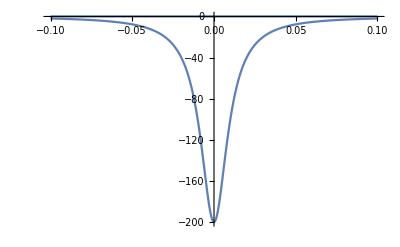

```mathematica
Plot[{Re[ⅈ/(L-ⅈ ϵ)-ⅈ/(L+ⅈ ϵ)],Im[ⅈ/(L-ⅈ ϵ)-ⅈ/(L+ⅈ ϵ)]}/.ϵ->0.01,{L,-.1,.1},PlotRange->All]
```

```mathematica
Clear[L];


Assuming[L∈Reals&&ϵ∈Reals&&L>0&&t∈Reals&&t>0&&L>0,Simplify[ComplexExpand[∫_0^∞ Exp[I*(L+I*ϵ)*(τ)]ⅆτ]]]/.{L->0.0001}
Assuming[L∈Reals&&ϵ∈Reals&&L>0&&t∈Reals&&t>0&&L>0,Simplify[ComplexExpand[∫_0^∞ Exp[I*(-L+I*ϵ)*(τ)]ⅆτ]]]/.{L->0.0001}
Assuming[L∈Reals&&ϵ∈Reals&&L>0&&t∈Reals&&t>0&&L>0,Simplify[ComplexExpand[∫_0^∞ Exp[I*(L+I*ϵ)*(τ)]ⅆτ+∫_0^∞ Exp[I*(-L+I*ϵ)*(τ)]ⅆτ]]]
Assuming[L∈Reals&&ϵ∈Reals&&L>0&&t∈Reals&&t>0&&L>0,Simplify[ComplexExpand[∫_0^∞ Exp[I*(L-I*ϵ)*(τ)]ⅆτ+∫_0^∞ Exp[I*(-L-I*ϵ)*(τ)]ⅆτ]]]
```

ConditionalExpression[ⅈ/(0.0001+ⅈ ϵ),ϵ>0]

ConditionalExpression[-ⅈ/(0.0001-ⅈ ϵ),ϵ>0]

ConditionalExpression[(2 ϵ)/(L^2+ϵ^2),ϵ>0]

ConditionalExpression[-(2 ϵ)/(L^2+ϵ^2),ϵ<0]

In the case where the sign of epsilon is opposite you get the sum of a delta and a normal denominator

```mathematica
Assuming[L∈Reals&&ϵ∈Reals&&L>0&&t∈Reals&&t>0&&L>0,Simplify[ComplexExpand[∫_0^∞ Exp[I*(L+I*ϵ)*(τ)]ⅆτ+Conjugate[∫_0^∞ Exp[-I*(L-I*ϵ)*(τ)]ⅆτ]]]]
```

ConditionalExpression[(2 ⅈ)/(L+ⅈ ϵ),ϵ>0]

```mathematica
ComplexExpand[(2 ⅈ*(L-ⅈ ϵ))/((L+ⅈ ϵ)*(L-ⅈ ϵ))]
```

(2 ⅈ L)/(L^2+ϵ^2)+(2 ϵ)/(L^2+ϵ^2)

```mathematica
Limit[(2 ⅈ L)/(L^2+ϵ^2)+(2 ϵ)/(L^2+ϵ^2),ϵ->0]
Limit[(2 ⅈ L)/(L^2+ϵ^2),ϵ->0]
Limit[(2 ϵ)/(L^2+ϵ^2),ϵ->0]
```

(2 ⅈ)/L

(2 ⅈ)/L

0

```mathematica
∫Exp[L*(t-τ)]ⅆτ
```

-ⅇ^(L t-L τ)/L

```mathematica
Clear[p]
Limit[Expand[Assuming[p>0&&q>0&&p∈Reals&&q∈Reals&&t∈Reals,∫_0^t Exp[I*s*(p-q)]ⅆs]*Exp[-I*t*(p-q)]],t->∞]
```

Limit[-ⅈ/(p-q)+(ⅈ ⅇ^(-ⅈ (p-q) t))/(p-q),t→∞]

```mathematica
∫_0^∞ Exp[I*(s)*(p-q)]ⅆs
```

ConditionalExpression[ⅈ/(p-q),Im[p]>Im[q]]

```mathematica
Integrate[Integrate[Integrate[r*z,{r,0,1-z}],{θ,0,2π}],{z,0,1}]
```

π/12

```mathematica
Integrate[Integrate[Integrate[r,{r,0,1-z}],{θ,0,2π}],{z,0,1}]
```

π/3

```mathematica
∫_0^t Exp[I*(s-t)*(p-q)]ⅆs
```

-(ⅈ (1-ⅇ^(-ⅈ (p-q) t)))/(p-q)

```mathematica
∫_t^(2t) Exp[I*(s-t)*(p-q)]ⅆs
```

-(ⅈ (-1+ⅇ^(ⅈ (p-q) t)))/(p-q)

```mathematica
∫_(-∞)^0 Exp[I*(τ)*(p-q)]ⅆτ
```

ConditionalExpression[ⅈ/(-p+q),Im[p]<Im[q]]

```mathematica
Limit[∫_0^t Exp[I*(s-t)*(p-q)]ⅆs,t->∞]
```

Limit[-(ⅈ (1-ⅇ^(-ⅈ (p-q) t)))/(p-q),t→∞]

```mathematica
∫_0^∞ Exp[-I*s*(p-q)]ⅆs
```

ConditionalExpression[ⅈ/(-p+q),Im[p]<Im[q]]

```mathematica
∫_0^∞ Exp[-I*s*(q-p)]ⅆs
```

ConditionalExpression[ⅈ/(p-q),Im[p]>Im[q]]

Trying Out Laplace

```mathematica
dτ=0.5;
p=0.1;
q=0.3;
r=0.005;
s=-0.100;
dτ*Total[Table[Exp[-τ*p]Exp[-τ*q]Exp[τ*r]Exp[τ*s],{τ,0.0,20,dτ}]]
1/(p+q-r-s)
Clear[p,q,r,s,dτ]
```

2.28041

2.0202

```mathematica
Solve[x==Exp[-τ],τ]
```

{{τ→ConditionalExpression[2 ⅈ π C[1]+Log[1/x],C[1]∈Integers]}}

```mathematica
D[(-Log[x]), x]
```

-1/x

```mathematica
∫_0^∞ Exp[-0.1*x^2]ⅆx
```

2.8025

```mathematica
Solve[Exp[-τ]==0,τ]
```

{}

```mathematica
∫_0^∞ Exp[-0.1*x]ⅆx
Limit[∫_0^∞ Exp[(0.1+γ*I)*I*x]ⅆx,γ->0]/I
(1/I∫_0^∞ Exp[(p-q)*I*x]ⅆx)

(∫_0^∞ Exp[(p-q)*I*x]ⅆx)/.{p->(b+10I),q->(b+9.9I)}
(∫_0^∞ Exp[(p-q)*I*x]ⅆx)/.{p->(b+8I),q->(b+8.1I)}
∫_∞^(-∞) Exp[-0.1*(Exp[-x])]*(-Exp[-x])ⅆx
∫_(-∞)^∞ Exp[-0.1*(Exp[x])]*(Exp[x])ⅆx
```

10.

10.+0. ⅈ

ConditionalExpression[1/(p-q),Im[p]>Im[q]]

ConditionalExpression[10.+0. ⅈ,10+Im[b]>9.9+Im[b]]

ConditionalExpression[-10.+0. ⅈ,8+Im[b]>8.1+Im[b]]

10.

10.

```mathematica
∫_0^∞ Exp[-(t-I)*Abs[(p+q-r-s)]]ⅆt
```

ConditionalExpression[ⅇ^(ⅈ Abs[p+q-r-s])/Abs[p+q-r-s],p+q≠r+s]

```mathematica
Δ=0.1
Limit[∫_0^∞ Exp[(Δ+γ*I)*I*x]ⅆx,γ->0]
Δ=-0.1
Limit[∫_0^∞ Exp[(Δ+γ*I)*I*x]ⅆx,γ->0]
Limit[∫_0^∞ Exp[(-Δ+γ*I)*I*x]ⅆx,γ->0]
```

0.1

0.+10. ⅈ

-0.1

0.-10. ⅈ

0.+10. ⅈ

```mathematica
ListPlot[Re[Exp[(Δ+I*0.001)*I*Wghts]],Joined->True,PlotRange->All]
```

ListPlot[Re[ⅇ^((-0.001-0.1 ⅈ) Wghts)],Joined→True,PlotRange→All]

```mathematica
ListPlot[Re[Exp[(10.0+I*0.001)*I*Wghts]]*Wghts,Joined->True,PlotRange->All]
```

ListPlot[Wghts Re[ⅇ^((-0.001+10. ⅈ) Wghts)],Joined→True,PlotRange→All]

So basically the weights need to be flipped for negative energies. vs. positive. Can a mixed solution work? 4 cases

```mathematica
Energies={1.0,0.5,0.2,0.1};
Pe=Permutations[Energies];
Do[(
Print[(Pe[[i,1]]+Pe[[i,2]]-Pe[[i,3]]-Pe[[i,4]])];
Print[Limit[∫_0^∞ Exp[((Pe[[i,1]]+Pe[[i,2]]-Pe[[i,3]]-Pe[[i,4]])+γ*I)*I*x]ⅆx,γ->0]];
Print[I/((Pe[[i,1]]+Pe[[i,2]]-Pe[[i,3]]-Pe[[i,4]]))];
Wghts=Table[-1.0*Exp[1.0*τ],{τ,-5,5,1}];
Print[Sum[Exp[(Pe[[i,1]]+Pe[[i,2]]-Pe[[i,3]]-Pe[[i,4]])*Wghts[[j]]]*Wghts[[j]],{j,1,11}]/I];
Print[Sum[Sign[(Pe[[i,1]]+Pe[[i,2]]-Pe[[i,3]]-Pe[[i,4]])]*Exp[Abs[(Pe[[i,1]]+Pe[[i,2]]-Pe[[i,3]]-Pe[[i,4]])]*Wghts[[j]]]*Wghts[[j]],{j,1,11}]/I];
),{i,1,Length[Pe]}];
```

1.2

0.+0.833333 ⅈ

0.+0.833333 ⅈ

0.+0.829517 ⅈ

0.+0.829517 ⅈ

1.2

0.+0.833333 ⅈ

0.+0.833333 ⅈ

0.+0.829517 ⅈ

0.+0.829517 ⅈ

0.6

0.+1.66667 ⅈ

0.+1.66667 ⅈ

0.+1.66168 ⅈ

0.+1.66168 ⅈ

0.6

0.+1.66667 ⅈ

0.+1.66667 ⅈ

0.+1.66168 ⅈ

0.+1.66168 ⅈ

0.4

0.+2.5 ⅈ

0.+2.5 ⅈ

0.+2.49725 ⅈ

0.+2.49725 ⅈ

0.4

0.+2.5 ⅈ

0.+2.5 ⅈ

0.+2.49725 ⅈ

0.+2.49725 ⅈ

1.2

0.+0.833333 ⅈ

0.+0.833333 ⅈ

0.+0.829517 ⅈ

0.+0.829517 ⅈ

1.2

0.+0.833333 ⅈ

0.+0.833333 ⅈ

0.+0.829517 ⅈ

0.+0.829517 ⅈ

-0.4

0.-2.5 ⅈ

0.-2.5 ⅈ

0.+8.98419×10^27 ⅈ

0.-2.49725 ⅈ

-0.4

0.-2.5 ⅈ

0.-2.5 ⅈ

0.+8.98419×10^27 ⅈ

0.-2.49725 ⅈ

-0.6

0.-1.66667 ⅈ

0.-1.66667 ⅈ

0.+6.99008×10^40 ⅈ

0.-1.66168 ⅈ

-0.6

0.-1.66667 ⅈ

0.-1.66667 ⅈ

0.+6.99008×10^40 ⅈ

0.-1.66168 ⅈ

0.6

0.+1.66667 ⅈ

0.+1.66667 ⅈ

0.+1.66168 ⅈ

0.+1.66168 ⅈ

0.6

0.+1.66667 ⅈ

0.+1.66667 ⅈ

0.+1.66168 ⅈ

0.+1.66168 ⅈ

-0.4

0.-2.5 ⅈ

0.-2.5 ⅈ

0.+8.98419×10^27 ⅈ

0.-2.49725 ⅈ

-0.4

0.-2.5 ⅈ

0.-2.5 ⅈ

0.+8.98419×10^27 ⅈ

0.-2.49725 ⅈ

-1.2

0.-0.833333 ⅈ

0.-0.833333 ⅈ

0.+3.29224×10^79 ⅈ

0.-0.829517 ⅈ

-1.2

0.-0.833333 ⅈ

0.-0.833333 ⅈ

0.+3.29224×10^79 ⅈ

0.-0.829517 ⅈ

0.4

0.+2.5 ⅈ

0.+2.5 ⅈ

0.+2.49725 ⅈ

0.+2.49725 ⅈ

0.4

0.+2.5 ⅈ

0.+2.5 ⅈ

0.+2.49725 ⅈ

0.+2.49725 ⅈ

-0.6

0.-1.66667 ⅈ

0.-1.66667 ⅈ

0.+6.99008×10^40 ⅈ

0.-1.66168 ⅈ

-0.6

0.-1.66667 ⅈ

0.-1.66667 ⅈ

0.+6.99008×10^40 ⅈ

0.-1.66168 ⅈ

-1.2

0.-0.833333 ⅈ

0.-0.833333 ⅈ

0.+3.29224×10^79 ⅈ

0.-0.829517 ⅈ

-1.2

0.-0.833333 ⅈ

0.-0.833333 ⅈ

0.+3.29224×10^79 ⅈ

0.-0.829517 ⅈ

## Secularizer (which actually works)

### Derivation of The Secularizer.

We want to generate the secularizer for 8 indices. Via a python code I verified that his has the following form written recursively in terms of lower - rank tensors as follows :                                 
      		        Cond1 = SecularTwoI (p, q, r, s)*SecularTwoI (t, u, v, w)
                                  Cond2 = (1.0 - Cond1)*SecularTwoI (p, q, v, w)*SecularTwoI (t, u, r, s)
                                  Cond3 = (1.0 - Cond1)*(1.0 - Cond2)*SecularTwoI (p, q, v, r)*SecularTwoI (t, u, w, s)
                                  Cond4 = (1.0 - Cond1)*(1.0 - Cond2)*(1.0 - Cond3)*SecularTwoI (p, q, r, w)*SecularTwoI (t, u, v, s)
                                  Cond5 = (1.0 - Cond1)*(1.0 - Cond2)*(1.0 - Cond3)*(1.0 - Cond4)*SecularTwoI (p, q, v, s)*SecularTwoI (t, u, r, w)
                                  Cond  = Cond1 + Cond2 + Cond3 + Cond4 + Cond5 + (1.0 - Cond1)*(1.0 - Cond2)*(1.0 - Cond3)*(1.0 - Cond4)*(1.0 - Cond5)*SecularTwoI (p, q, w, s)*SecularTwoI (t, u, v, r)
                                  
  Now I' m using mathematica to simplify the remaining

```mathematica
STwo[p_, q_, r_, s_] := {{{"Sign", 1}, {{δ, 1}, {p}, {r}}, {{δ, 1}, {q}, {s}}}, {{"Sign", 1}, {{δ, 1}, {p}, {s}}, {{δ, 1}, {q}, {r}}}, {{"Sign", -1}, {{δ, 1}, {p}, {r}}, {{δ, 1}, {q}, {s}}, {{δ, 1}, {p}, {s}}, {{δ, 1}, {q}, {r}}}};
```

```mathematica
DeltaCombine1 = {{"Sign", a_}, any5___, {{δ, 1}, {p_}, {q_}}, any8___, {{δ, 1}, {r_}, {q_}}, any9___} -> {{"Sign", a}, any5, {{δ, X}, {p, q, r}, {p, q, r}}, any8, any9};
DeltaCombine2 = {{"Sign", a_}, any5___, {{δ, X_ /; X =!= 1}, {p___, q_, r___}, {x___}}, any8___, {{δ, X2_ /; X2 =!= 1}, {p2___, q_, r2___}, {x2___}}, any9___} -> {{"Sign", a}, any5, {{δ, X}, {p, q, r, p2, r2}, {p, q, r, p2, r2}}, any8, any9};
DeltaCombine3 = {{"Sign", a_}, any5___, {{δ, X_ /; X =!= 1}, {p___, q_, r___, q_, s___}, {x___}}, any8___} -> {{"Sign", a}, any5, {{δ, X}, {p, q, r, s}, {p, q, r, s}}, any8};
DeltaCombine4 = {{"Sign", a_}, any5___, {{δ, 1}, {p_}, {q_}}, any8___, {{δ, X_ /; X =!= 1}, {p2___, q_, r2___}, {q2___}}, any9___} -> {{"Sign", a}, any5, {{δ, X}, {p, q, p2, r2}, {p, q, p2, r2}}, any8, any9};
DeltaCombine5 = {{"Sign", a_}, any5___, {{δ, 1}, {p_}, {q_}}, any8___, {{δ, X_ /; X =!= 1}, {p2___, p_, r2___}, {q2___}}, any9___} -> {{"Sign", a}, any5, {{δ, X}, {p, q, p2, r2}, {p, q, p2, r2}}, any8, any9};
DeltaCombine6 = {{"Sign", a_}, any5___, {{δ, X_ /; X =!= 1}, p2___}, any8___, {{δ, 1}, p___}, any9___} -> {{"Sign", a}, any5, {{δ, 1}, p}, {{δ, X}, p2}, any8, any9};
CombineMDeltas = {DeltaCombine1, DeltaCombine2, DeltaCombine3, DeltaCombine4, DeltaCombine5, DeltaCombine6};
(*Stuff to convert the expressions to code.*)
ListToString[alist_] := (
  ous = "";
  Do[If[i != Length[alist], ous = ous <> ToString[alist[[i]]] <> ",", ous = ous <> ToString[alist[[i]]]], {i, 1, Length[alist]}];
  Return[ous]
  )
DeltaCodeString[Fa_] := If[Fa[[1, 2]] === 1, "*Delta(" <> ToString[Fa[[2, 1]]] <> "," <> ToString[Fa[[3, 1]]] <> ")", "*Delta(" <> ListToString[Fa[[2]]] <> ")"]
TermCodeString[ATerm_] := "+(" <> ToString[ATerm[[1, 2]]] <> ")" <> Map[DeltaCodeString, ATerm[[2 ;;]]];
```

```mathematica
C1 = DistributeOperatorProduct[STwo[p, q, r, s], STwo[t, u, v, w]];
P2 = DistributeOperatorProduct[STwo[p, q, v, w], STwo[t, u, r, s]];
C2 = AssociativeSimplify[Join[P2, MultiplyScalar[DistributeOperatorProduct[C1, P2], -1],1] //. CombineMDeltas];
```

```mathematica
RecognizableForm[C2]
```

```mathematica
(*(1.0-Cond1)*(1.0-Cond2)*SecularTwoI(p,q,v,r)*SecularTwoI(t,u,w,s)*)
P3 = AssociativeSimplify[DistributeOperatorProduct[STwo[p, q, v, r], STwo[t, u, w, s]] //. CombineMDeltas,1];
OneMinusC1 = Join[{{{"Sign", 1}}}, MultiplyScalar[C1, -1]];
OneMinusC2 = Join[{{{"Sign", 1}}}, MultiplyScalar[C2, -1]];
F3 = AssociativeSimplify[DistributeOperatorProduct[OneMinusC1, OneMinusC2] //. CombineMDeltas,1];
C3 = AssociativeSimplify[DistributeOperatorProduct[F3, P3] //. CombineMDeltas,1];
```

```mathematica
(*(1.0-Cond1)*(1.0-Cond2)*(1.0-Cond3)*SecularTwoI(p,q,r,w)*SecularTwoI(t,u,v,s)*)
P4 = AssociativeSimplify[DistributeOperatorProduct[STwo[p, q, r, w], STwo[t, u, v, s]] //. CombineMDeltas,2];
OneMinusC3 = Join[{{{"Sign", 1}}}, MultiplyScalar[C3, -1]];
F4 = AssociativeSimplify[DistributeOperatorProduct[F3, OneMinusC3] //. CombineMDeltas,2];
C4 = AssociativeSimplify[DistributeOperatorProduct[F4, P4] //. CombineMDeltas,2];
```

```mathematica
RecognizableForm[C4]
```

```mathematica
P5 = AssociativeSimplify[DistributeOperatorProduct[STwo[p, q, v, s], STwo[t, u, r, w]] //. CombineMDeltas,2];
OneMinusC4 = Join[{{{"Sign", 1}}}, MultiplyScalar[C4, -1]];
F5 = AssociativeSimplify[DistributeOperatorProduct[F4, OneMinusC4] //. CombineMDeltas,2];
C5 = AssociativeSimplify[DistributeOperatorProduct[F5, P5] //. CombineMDeltas,2];
P6 = AssociativeSimplify[DistributeOperatorProduct[STwo[p, q, w, s], STwo[t, u, v, r]] //. CombineMDeltas,2];
OneMinusC5 = Join[{{{"Sign", 1}}}, MultiplyScalar[C5, -1]];
F6 = AssociativeSimplify[DistributeOperatorProduct[F5, OneMinusC5] //. CombineMDeltas,2];
C6 = AssociativeSimplify[DistributeOperatorProduct[F6, P6] //. CombineMDeltas,2;
```

```mathematica
Secular8 = AssociativeSimplify[Join[C1, C2, C3, C4, C5, C6] //. CombineMDeltas,2];
```

```mathematica
RecognizableForm[Secular8]
```

```mathematica
Secular8=ListForm[Subscript[δ, r]^u Subscript[δ, s]^t Subscript[δ, v]^q Subscript[δ, w]^p+Subscript[δ, r]^t Subscript[δ, s]^u Subscript[δ, v]^q Subscript[δ, w]^p-Subscript[δ, r s t u]^(r s t u) Subscript[δ, v]^q Subscript[δ, w]^p+Subscript[δ, r]^u Subscript[δ, s]^q Subscript[δ, v]^t Subscript[δ, w]^p+Subscript[δ, r]^q Subscript[δ, s]^u Subscript[δ, v]^t Subscript[δ, w]^p+Subscript[δ, r]^t Subscript[δ, s]^q Subscript[δ, v]^u Subscript[δ, w]^p+Subscript[δ, r]^q Subscript[δ, s]^t Subscript[δ, v]^u Subscript[δ, w]^p-Subscript[δ, s]^q Subscript[δ, r t u v]^(r t u v) Subscript[δ, w]^p-Subscript[δ, r]^q Subscript[δ, s t u v]^(s t u v) Subscript[δ, w]^p+Subscript[δ, r]^u Subscript[δ, s]^t Subscript[δ, v]^p Subscript[δ, w]^q+Subscript[δ, r]^t Subscript[δ, s]^u Subscript[δ, v]^p Subscript[δ, w]^q-Subscript[δ, r s t u]^(r s t u) Subscript[δ, v]^p Subscript[δ, w]^q+Subscript[δ, r]^u Subscript[δ, s]^p Subscript[δ, v]^t Subscript[δ, w]^q+Subscript[δ, r]^p Subscript[δ, s]^u Subscript[δ, v]^t Subscript[δ, w]^q+Subscript[δ, r]^t Subscript[δ, s]^p Subscript[δ, v]^u Subscript[δ, w]^q+Subscript[δ, r]^p Subscript[δ, s]^t Subscript[δ, v]^u Subscript[δ, w]^q-Subscript[δ, s]^p Subscript[δ, r t u v]^(r t u v) Subscript[δ, w]^q-Subscript[δ, r]^p Subscript[δ, s t u v]^(s t u v) Subscript[δ, w]^q+Subscript[δ, r]^u Subscript[δ, s]^q Subscript[δ, v]^p Subscript[δ, w]^t+Subscript[δ, r]^q Subscript[δ, s]^u Subscript[δ, v]^p Subscript[δ, w]^t+Subscript[δ, r]^u Subscript[δ, s]^p Subscript[δ, v]^q Subscript[δ, w]^t+Subscript[δ, r]^p Subscript[δ, s]^u Subscript[δ, v]^q Subscript[δ, w]^t+Subscript[δ, r]^q Subscript[δ, s]^p Subscript[δ, v]^u Subscript[δ, w]^t+Subscript[δ, r]^p Subscript[δ, s]^q Subscript[δ, v]^u Subscript[δ, w]^t-Subscript[δ, p q r s]^(p q r s) Subscript[δ, v]^u Subscript[δ, w]^t-Subscript[δ, s]^u Subscript[δ, p q r v]^(p q r v) Subscript[δ, w]^t-Subscript[δ, r]^u Subscript[δ, p q s v]^(p q s v) Subscript[δ, w]^t+Subscript[δ, r]^t Subscript[δ, s]^q Subscript[δ, v]^p Subscript[δ, w]^u+Subscript[δ, r]^q Subscript[δ, s]^t Subscript[δ, v]^p Subscript[δ, w]^u+Subscript[δ, r]^t Subscript[δ, s]^p Subscript[δ, v]^q Subscript[δ, w]^u+Subscript[δ, r]^p Subscript[δ, s]^t Subscript[δ, v]^q Subscript[δ, w]^u+Subscript[δ, r]^q Subscript[δ, s]^p Subscript[δ, v]^t Subscript[δ, w]^u+Subscript[δ, r]^p Subscript[δ, s]^q Subscript[δ, v]^t Subscript[δ, w]^u-Subscript[δ, p q r s]^(p q r s) Subscript[δ, v]^t Subscript[δ, w]^u-Subscript[δ, s]^t Subscript[δ, p q r v]^(p q r v) Subscript[δ, w]^u-Subscript[δ, r]^t Subscript[δ, p q s v]^(p q s v) Subscript[δ, w]^u-Subscript[δ, q r s u]^(q r s u) Subscript[δ, t v]^(t v) Subscript[δ, p w]^(p w)-Subscript[δ, s u]^(s u) Subscript[δ, q r t v]^(q r t v) Subscript[δ, p w]^(p w)-Subscript[δ, r u]^(r u) Subscript[δ, q s t v]^(q s t v) Subscript[δ, p w]^(p w)-Subscript[δ, q r s t]^(q r s t) Subscript[δ, u v]^(u v) Subscript[δ, p w]^(p w)-Subscript[δ, s t]^(s t) Subscript[δ, q r u v]^(q r u v) Subscript[δ, p w]^(p w)-Subscript[δ, r t]^(r t) Subscript[δ, q s u v]^(q s u v) Subscript[δ, p w]^(p w)+4 Subscript[δ, q r s t u v]^(q r s t u v) Subscript[δ, p w]^(p w)-Subscript[δ, p r s u]^(p r s u) Subscript[δ, t v]^(t v) Subscript[δ, q w]^(q w)-Subscript[δ, s u]^(s u) Subscript[δ, p r t v]^(p r t v) Subscript[δ, q w]^(q w)-Subscript[δ, r u]^(r u) Subscript[δ, p s t v]^(p s t v) Subscript[δ, q w]^(q w)-Subscript[δ, p r s t]^(p r s t) Subscript[δ, u v]^(u v) Subscript[δ, q w]^(q w)-Subscript[δ, s t]^(s t) Subscript[δ, p r u v]^(p r u v) Subscript[δ, q w]^(q w)-Subscript[δ, r t]^(r t) Subscript[δ, p s u v]^(p s u v) Subscript[δ, q w]^(q w)+4 Subscript[δ, p r s t u v]^(p r s t u v) Subscript[δ, q w]^(q w)-Subscript[δ, s]^u Subscript[δ, v]^t Subscript[δ, p q r w]^(p q r w)-Subscript[δ, s]^t Subscript[δ, v]^u Subscript[δ, p q r w]^(p q r w)+Subscript[δ, s t u v]^(s t u v) Subscript[δ, p q r w]^(p q r w)-Subscript[δ, r]^u Subscript[δ, v]^t Subscript[δ, p q s w]^(p q s w)-Subscript[δ, r]^t Subscript[δ, v]^u Subscript[δ, p q s w]^(p q s w)+Subscript[δ, r t u v]^(r t u v) Subscript[δ, p q s w]^(p q s w)-Subscript[δ, q r s u]^(q r s u) Subscript[δ, p v]^(p v) Subscript[δ, t w]^(t w)-Subscript[δ, p r s u]^(p r s u) Subscript[δ, q v]^(q v) Subscript[δ, t w]^(t w)-Subscript[δ, q s]^(q s) Subscript[δ, p r u v]^(p r u v) Subscript[δ, t w]^(t w)-Subscript[δ, p s]^(p s) Subscript[δ, q r u v]^(q r u v) Subscript[δ, t w]^(t w)-Subscript[δ, q r]^(q r) Subscript[δ, p s u v]^(p s u v) Subscript[δ, t w]^(t w)-Subscript[δ, p r]^(p r) Subscript[δ, q s u v]^(q s u v) Subscript[δ, t w]^(t w)+4 Subscript[δ, p q r s u v]^(p q r s u v) Subscript[δ, t w]^(t w)-Subscript[δ, s u]^(s u) Subscript[δ, q v]^(q v) Subscript[δ, p r t w]^(p r t w)-Subscript[δ, q s]^(q s) Subscript[δ, u v]^(u v) Subscript[δ, p r t w]^(p r t w)+Subscript[δ, q s u v]^(q s u v) Subscript[δ, p r t w]^(p r t w)-Subscript[δ, s u]^(s u) Subscript[δ, p v]^(p v) Subscript[δ, q r t w]^(q r t w)-Subscript[δ, p s]^(p s) Subscript[δ, u v]^(u v) Subscript[δ, q r t w]^(q r t w)+Subscript[δ, p s u v]^(p s u v) Subscript[δ, q r t w]^(q r t w)-Subscript[δ, r u]^(r u) Subscript[δ, q v]^(q v) Subscript[δ, p s t w]^(p s t w)-Subscript[δ, q r]^(q r) Subscript[δ, u v]^(u v) Subscript[δ, p s t w]^(p s t w)+Subscript[δ, q r u v]^(q r u v) Subscript[δ, p s t w]^(p s t w)-Subscript[δ, r u]^(r u) Subscript[δ, p v]^(p v) Subscript[δ, q s t w]^(q s t w)-Subscript[δ, p r]^(p r) Subscript[δ, u v]^(u v) Subscript[δ, q s t w]^(q s t w)+Subscript[δ, p r u v]^(p r u v) Subscript[δ, q s t w]^(q s t w)+4 Subscript[δ, u v]^(u v) Subscript[δ, p q r s t w]^(p q r s t w)-Subscript[δ, q r s t]^(q r s t) Subscript[δ, p v]^(p v) Subscript[δ, u w]^(u w)-Subscript[δ, p r s t]^(p r s t) Subscript[δ, q v]^(q v) Subscript[δ, u w]^(u w)-Subscript[δ, q s]^(q s) Subscript[δ, p r t v]^(p r t v) Subscript[δ, u w]^(u w)-Subscript[δ, p s]^(p s) Subscript[δ, q r t v]^(q r t v) Subscript[δ, u w]^(u w)-Subscript[δ, q r]^(q r) Subscript[δ, p s t v]^(p s t v) Subscript[δ, u w]^(u w)-Subscript[δ, p r]^(p r) Subscript[δ, q s t v]^(q s t v) Subscript[δ, u w]^(u w)+4 Subscript[δ, p q r s t v]^(p q r s t v) Subscript[δ, u w]^(u w)-Subscript[δ, s t]^(s t) Subscript[δ, q v]^(q v) Subscript[δ, p r u w]^(p r u w)-Subscript[δ, q s]^(q s) Subscript[δ, t v]^(t v) Subscript[δ, p r u w]^(p r u w)+Subscript[δ, q s t v]^(q s t v) Subscript[δ, p r u w]^(p r u w)-Subscript[δ, s t]^(s t) Subscript[δ, p v]^(p v) Subscript[δ, q r u w]^(q r u w)-Subscript[δ, p s]^(p s) Subscript[δ, t v]^(t v) Subscript[δ, q r u w]^(q r u w)+Subscript[δ, p s t v]^(p s t v) Subscript[δ, q r u w]^(q r u w)-Subscript[δ, r t]^(r t) Subscript[δ, q v]^(q v) Subscript[δ, p s u w]^(p s u w)-Subscript[δ, q r]^(q r) Subscript[δ, t v]^(t v) Subscript[δ, p s u w]^(p s u w)+Subscript[δ, q r t v]^(q r t v) Subscript[δ, p s u w]^(p s u w)-Subscript[δ, r t]^(r t) Subscript[δ, p v]^(p v) Subscript[δ, q s u w]^(q s u w)-Subscript[δ, p r]^(p r) Subscript[δ, t v]^(t v) Subscript[δ, q s u w]^(q s u w)+Subscript[δ, p r t v]^(p r t v) Subscript[δ, q s u w]^(q s u w)+4 Subscript[δ, t v]^(t v) Subscript[δ, p q r s u w]^(p q r s u w)-Subscript[δ, s]^q Subscript[δ, v]^p Subscript[δ, r t u w]^(r t u w)-Subscript[δ, s]^p Subscript[δ, v]^q Subscript[δ, r t u w]^(r t u w)+Subscript[δ, p q s v]^(p q s v) Subscript[δ, r t u w]^(r t u w)-Subscript[δ, r]^q Subscript[δ, v]^p Subscript[δ, s t u w]^(s t u w)-Subscript[δ, r]^p Subscript[δ, v]^q Subscript[δ, s t u w]^(s t u w)+Subscript[δ, p q r v]^(p q r v) Subscript[δ, s t u w]^(s t u w)+4 Subscript[δ, q v]^(q v) Subscript[δ, p r s t u w]^(p r s t u w)+4 Subscript[δ, p v]^(p v) Subscript[δ, q r s t u w]^(q r s t u w)-Subscript[δ, r]^u Subscript[δ, s]^t Subscript[δ, p q v w]^(p q v w)-Subscript[δ, r]^t Subscript[δ, s]^u Subscript[δ, p q v w]^(p q v w)+Subscript[δ, r s t u]^(r s t u) Subscript[δ, p q v w]^(p q v w)-Subscript[δ, q s]^(q s) Subscript[δ, r u]^(r u) Subscript[δ, p t v w]^(p t v w)-Subscript[δ, q r]^(q r) Subscript[δ, s u]^(s u) Subscript[δ, p t v w]^(p t v w)+Subscript[δ, q r s u]^(q r s u) Subscript[δ, p t v w]^(p t v w)-Subscript[δ, p s]^(p s) Subscript[δ, r u]^(r u) Subscript[δ, q t v w]^(q t v w)-Subscript[δ, p r]^(p r) Subscript[δ, s u]^(s u) Subscript[δ, q t v w]^(q t v w)+Subscript[δ, p r s u]^(p r s u) Subscript[δ, q t v w]^(q t v w)+4 Subscript[δ, s u]^(s u) Subscript[δ, p q r t v w]^(p q r t v w)+4 Subscript[δ, r u]^(r u) Subscript[δ, p q s t v w]^(p q s t v w)-Subscript[δ, q s]^(q s) Subscript[δ, r t]^(r t) Subscript[δ, p u v w]^(p u v w)-Subscript[δ, q r]^(q r) Subscript[δ, s t]^(s t) Subscript[δ, p u v w]^(p u v w)+Subscript[δ, q r s t]^(q r s t) Subscript[δ, p u v w]^(p u v w)-Subscript[δ, p s]^(p s) Subscript[δ, r t]^(r t) Subscript[δ, q u v w]^(q u v w)-Subscript[δ, p r]^(p r) Subscript[δ, s t]^(s t) Subscript[δ, q u v w]^(q u v w)+Subscript[δ, p r s t]^(p r s t) Subscript[δ, q u v w]^(q u v w)+4 Subscript[δ, s t]^(s t) Subscript[δ, p q r u v w]^(p q r u v w)+4 Subscript[δ, r t]^(r t) Subscript[δ, p q s u v w]^(p q s u v w)-Subscript[δ, r]^q Subscript[δ, s]^p Subscript[δ, t u v w]^(t u v w)-Subscript[δ, r]^p Subscript[δ, s]^q Subscript[δ, t u v w]^(t u v w)+Subscript[δ, p q r s]^(p q r s) Subscript[δ, t u v w]^(t u v w)+4 Subscript[δ, q s]^(q s) Subscript[δ, p r t u v w]^(p r t u v w)+4 Subscript[δ, p s]^(p s) Subscript[δ, q r t u v w]^(q r t u v w)+4 Subscript[δ, q r]^(q r) Subscript[δ, p s t u v w]^(p s t u v w)+4 Subscript[δ, p r]^(p r) Subscript[δ, q s t u v w]^(q s t u v w)-33 Subscript[δ, p q r s t u v w]^(p q r s t u v w)];
MultiDeltaRule[Amd_,Di_]:=(
Map[(#->Di)&,Amd[[2]]]
)
CollapseMultiDeltas[aTerm_]:=
(
DeltasNow=Select[aTerm,#[[1,1]]===δ&];
NoDeltasNow=Complement[aTerm,DeltasNow];
ExternalDeltas=Select[DeltasNow,MemberQ[Flatten[#],"p"|"pp"] || MemberQ[Flatten[#],"q"|"qq"]&];
ExternalpDelta=Select[ExternalDeltas,MemberQ[Flatten[#],"p"|"pp"] &];
ExternalqDelta=Select[Complement[ExternalDeltas,ExternalpDelta],MemberQ[Flatten[#],"q"|"qq"] &];
EpRule=If[Length[ExternalpDelta]>0,MultiDeltaRule[ExternalpDelta[[1]],"p"],{}];
EqRule=If[Length[ExternalqDelta]>0,MultiDeltaRule[ExternalqDelta[[1]],"q"],{}];
(*Print[EpRule,EqRule];*)
InternalDeltas=Complement[DeltasNow,ExternalDeltas];
tmp2=NoDeltasNow/.Join[EpRule,EqRule];
(*Print[EpRule,EqRule,InternalDeltas];*)
Do[(
tmp2 =tmp2/.MultiDeltaRule[InternalDeltas[[i]],Sort[InternalDeltas[[i,2]]][[1]]];
),{i,1,Length[InternalDeltas]}];
(*Delete any zero terms.*)
TsNow=Select[tmp2,#[[1]]==={"VTs",2}&][[1]];
TtNow=Select[tmp2,#[[1]]==={"VTt",2}&][[1]];
Tmp3=If[MatchQ[TsNow,{{y_,2},___,{x_,x_},___}] || MatchQ[TtNow,{{y_,2},___,{x_,x_},___}],{{"Sign",0},TsNow},tmp2];
Return[IndexReorder[RelabelTerm[Tmp3]]]
);
NoZeros=({any1___,{{"Sign",0},any3___},any2___}->{any1,any2});
SecularizeATerm[ATerm_]:=(
dslu=Select[ATerm,#[[1,1]]==="VTs"&][[1,3]];
dsld=Select[ATerm,#[[1,1]]==="VTs"&][[1,2]];
dtlu=Select[ATerm,#[[1,1]]==="VTt"&][[1,3]];
dtld=Select[ATerm,#[[1,1]]==="VTt"&][[1,2]];
ThisSecularizer=Secular8/.{p->dslu[[1]],q->dslu[[2]],r->dsld[[1]],s->dsld[[2]],t->dtlu[[1]],u->dtlu[[2]],v->dtld[[1]],w->dtld[[2]]};
Return[AssociativeSimplify[Map[RelabelTerm,Map[CollapseMultiDeltas,Map[CollapseDeltas,DistributeOperatorProduct[{ATerm},ThisSecularizer]]]]]]
)
```

```mathematica
RecognizableForm[Flatten[Map[SecularizeATerm,FinalByHand],1]]
```

```mathematica
Map[SecularizeATerm,FinalByHand]
```

```mathematica
RecognizableForm[SecularFinalByHand=Join[Map[SecularizeATerm,FinalByHand]]]
```

```mathematica
RecognizableForm[Flatten[Map[SecularizeATerm,FullySimplifiedTCLNoDelta1s],1]]
```

```mathematica
(*This can be used to test the secularizer in python.*)
StringJoin[Map[TermCodeString, Secular8]];
```

### If I do the diagrams by hand I get:

```mathematica
RecognizableForm[ByHandFromCode]
```

Total[ByHandFromCode]

```mathematica
1/2 Subscript["VTs", {"u","w"}]^{"r","y"} Subscript["VTt", {"s","x"}]^{"t","v"} Subscript[γ, {"t"}]^{"u"} Subscript[γ, {"v"}]^{"w"} Subscript[δ, {"y"}]^{"p"} Subscript[η, {"q"}]^{"x"} Subscript[η, {"r"}]^{"s"}-1/2 Subscript["VTs", {"w","x"}]^{"r","t"} Subscript["VTt", {"s","u"}]^{"v","y"} Subscript[γ, {"v"}]^{"w"} Subscript[γ, {"y"}]^{"p"} Subscript[δ, {"q"}]^{"x"} Subscript[η, {"r"}]^{"s"} Subscript[η, {"t"}]^{"u"}-1/2 Subscript["VTs", {"s","u"}]^{"v","y"} Subscript["VTt", {"w","x"}]^{"r","t"} Subscript[γ, {"q"}]^{"x"} Subscript[γ, {"v"}]^{"w"} Subscript[δ, {"y"}]^{"p"} Subscript[η, {"r"}]^{"s"} Subscript[η, {"t"}]^{"u"}+1/2 Subscript["VTs", {"s","y"}]^{"t","v"} Subscript["VTt", {"u","w"}]^{"r","x"} Subscript[γ, {"t"}]^{"u"} Subscript[γ, {"v"}]^{"w"} Subscript[δ, {"q"}]^{"y"} Subscript[η, {"r"}]^{"s"} Subscript[η, {"x"}]^{"p"}
```

1/2 VTs_{u,w}^{r,y} VTt_{s,x}^{t,v} γ_{t}^{u} γ_{v}^{w} δ_{y}^{p} η_{q}^{x} η_{r}^{s}-1/2 VTs_{w,x}^{r,t} VTt_{s,u}^{v,y} γ_{v}^{w} γ_{y}^{p} δ_{q}^{x} η_{r}^{s} η_{t}^{u}-1/2 VTs_{s,u}^{v,y} VTt_{w,x}^{r,t} γ_{q}^{x} γ_{v}^{w} δ_{y}^{p} η_{r}^{s} η_{t}^{u}+1/2 VTs_{s,y}^{t,v} VTt_{u,w}^{r,x} γ_{t}^{u} γ_{v}^{w} δ_{q}^{y} η_{r}^{s} η_{x}^{p}

```mathematica
ByHand=ListForm[Expand[-1/2 Subscript["VTs", {"t","u"}]^{"r","s"} Subscript["VTt", {"x","y"}]^{"v","w"}*(Subscript[δ, {"t"}]^{"p"}  )*(Subscript[γ, {"q"}]^{"v"}  Subscript[η, {"x"}]^{"r"} Subscript[η, {"y"}]^{"s"}Subscript[γ, {"u"}]^{"w"}-Subscript[η, {"q"}]^{"v"}  Subscript[γ, {"x"}]^{"r"} Subscript[γ, {"y"}]^{"s"}Subscript[η, {"u"}]^{"w"})-1/2 Subscript["VTs", {"t","u"}]^{"r","s"} Subscript["VTt", {"x","y"}]^{"v","w"}*(Subscript[δ, {"q"}]^{"r"}  )*(Subscript[γ, {"x"}]^{"p"}  Subscript[η, {"t"}]^{"v"} Subscript[γ, {"y"}]^{"s"}Subscript[η, {"u"}]^{"w"}-Subscript[η, {"x"}]^{"p"}  Subscript[γ, {"t"}]^{"v"}Subscript[η, {"y"}]^{"s"}Subscript[γ, {"u"}]^{"w"})]];

RecognizableForm[ByHand]
```

1/2 VTs_{t,u}^{r,s} VTt_{x,y}^{v,w} γ_{x}^{r} γ_{y}^{s} δ_{t}^{p} η_{q}^{v} η_{u}^{w}-1/2 VTs_{t,u}^{r,s} VTt_{x,y}^{v,w} γ_{x}^{p} γ_{y}^{s} δ_{q}^{r} η_{t}^{v} η_{u}^{w}+1/2 VTs_{t,u}^{r,s} VTt_{x,y}^{v,w} γ_{t}^{v} γ_{u}^{w} δ_{q}^{r} η_{x}^{p} η_{y}^{s}-1/2 VTs_{t,u}^{r,s} VTt_{x,y}^{v,w} γ_{q}^{v} γ_{u}^{w} δ_{t}^{p} η_{x}^{r} η_{y}^{s}

```mathematica
ByHand
```

{{{Sign,1/2},{{VTs,2},{r,s},{t,u}},{{VTt,2},{v,w},{x,y}},{{γ,1},{r},{x}},{{γ,1},{s},{y}},{{δ,1},{p},{t}},{{η,1},{v},{q}},{{η,1},{w},{u}}},{{Sign,-1/2},{{VTs,2},{r,s},{t,u}},{{VTt,2},{v,w},{x,y}},{{γ,1},{p},{x}},{{γ,1},{s},{y}},{{δ,1},{r},{q}},{{η,1},{v},{t}},{{η,1},{w},{u}}},{{Sign,1/2},{{VTs,2},{r,s},{t,u}},{{VTt,2},{v,w},{x,y}},{{γ,1},{v},{t}},{{γ,1},{w},{u}},{{δ,1},{r},{q}},{{η,1},{p},{x}},{{η,1},{s},{y}}},{{Sign,-1/2},{{VTs,2},{r,s},{t,u}},{{VTt,2},{v,w},{x,y}},{{γ,1},{v},{q}},{{γ,1},{w},{u}},{{δ,1},{p},{t}},{{η,1},{r},{x}},{{η,1},{s},{y}}}}

```mathematica
RecognizableForm[Map[CollapseDeltas,ByHand[[2;;3]]]]
LatexRecognizableForm[Map[CollapseDeltas,ByHand]]
```

-1/2 VTs_{t,u}^{q,s} VTt_{x,y}^{v,w} γ_{x}^{p} γ_{y}^{s} η_{t}^{v} η_{u}^{w}+1/2 VTs_{t,u}^{q,s} VTt_{x,y}^{v,w} γ_{t}^{v} γ_{u}^{w} η_{x}^{p} η_{y}^{s}

1/2 \gamma_{x}^{r} \gamma_{y}^{s} VTs_{p u}^{r s} VTt_{x y}^{v w} η_{q}^{v} η_{u}^{w}-1/2 \gamma_{x}^{p} \gamma_{y}^{s} VTs_{t u}^{q s} VTt_{x y}^{v w} η_{t}^{v} η_{u}^{w}+1/2 \gamma_{t}^{v} \gamma_{u}^{w} VTs_{t u}^{q s} VTt_{x y}^{v w} η_{x}^{p} η_{y}^{s}-1/2 \gamma_{q}^{v} \gamma_{u}^{w} VTs_{p u}^{r s} VTt_{x y}^{v w} η_{x}^{r} η_{y}^{s}

```mathematica
(*Thinking now of the off diagonal...*)
```

This could likely be secularized by only the first two indices :

```mathematica
RecognizableForm[Map[CollapseDeltas,ByHand[[2;;3]]]]
RecognizableForm[STwo["r","t","v","x"]]
RecognizableForm[Map[CollapseMultiDeltas,Map[CollapseDeltas,DistributeOperatorProduct[ByHand[[2;;2]],STwo["r","t","v","x"]]]]]
RecognizableForm[Map[CollapseMultiDeltas,Map[CollapseDeltas,DistributeOperatorProduct[ByHand[[3;;3]],STwo["r","t","v","x"]]]]]
```

-1/2 VTs_{t,u}^{q,s} VTt_{x,y}^{v,w} γ_{x}^{p} γ_{y}^{s} η_{t}^{v} η_{u}^{w}+1/2 VTs_{t,u}^{q,s} VTt_{x,y}^{v,w} γ_{t}^{v} γ_{u}^{w} η_{x}^{p} η_{y}^{s}

δ_{v}^{t} δ_{x}^{r}+δ_{v}^{r} δ_{x}^{t}-δ_{v}^{r} δ_{v}^{t} δ_{x}^{r} δ_{x}^{t}

1/2 VTs_{q,r}^{q,u} VTt_{q,t}^{q,s} γ_{q}^{p} γ_{t}^{u} η_{q}^{q} η_{r}^{s}-1/2 VTs_{r,t}^{q,v} VTt_{q,u}^{s,t} γ_{q}^{p} γ_{u}^{v} η_{r}^{s} η_{t}^{t}-1/2 VTs_{r,v}^{q,u} VTt_{t,v}^{q,s} γ_{t}^{u} γ_{v}^{p} η_{r}^{s} η_{v}^{q}

-1/2 VTs_{q,t}^{q,s} VTt_{q,r}^{q,u} γ_{q}^{q} γ_{t}^{u} η_{q}^{p} η_{r}^{s}+1/2 VTs_{t,v}^{q,s} VTt_{q,r}^{u,v} γ_{t}^{u} γ_{v}^{v} η_{q}^{p} η_{r}^{s}+1/2 VTs_{t,v}^{q,s} VTt_{r,v}^{q,u} γ_{t}^{u} γ_{v}^{q} η_{r}^{s} η_{v}^{p}

```mathematica
STwo[p_, q_, r_, s_] := {{{"Sign", 1}, {{δ, 1}, {p}, {r}}, {{δ, 1}, {q}, {s}}}, {{"Sign", 1}, {{δ, 1}, {p}, {s}}, {{δ, 1}, {q}, {r}}}, {{"Sign", -1}, {{δ, 1}, {p}, {r}}, {{δ, 1}, {q}, {s}}, {{δ, 1}, {p}, {s}}, {{δ, 1}, {q}, {r}}}};
RecognizableForm[ByHand3=Map[CollapseMultiDeltas,Map[CollapseDeltas,DistributeOperatorProduct[ByHand,STwo["r","t","v","x"]]]]]
RecognizableForm[TCLSimp4=Map[CollapseMultiDeltas,Map[CollapseDeltas,Map[DiagonalGamma1,ByHand3]]]]
```

1/2 VTs_{p,t}^{p,s} VTt_{p,r}^{p,u} γ_{q}^{p} γ_{t}^{u} η_{p}^{p} η_{r}^{s}-1/2 VTs_{p,t}^{s,v} VTt_{p,r}^{u,v} γ_{q}^{v} γ_{t}^{u} η_{p}^{v} η_{r}^{s}-1/2 VTs_{p,r}^{p,u} VTt_{p,t}^{p,s} γ_{p}^{p} γ_{t}^{u} η_{q}^{p} η_{r}^{s}-1/2 VTs_{q,t}^{q,s} VTt_{q,r}^{q,u} γ_{q}^{q} γ_{t}^{u} η_{q}^{p} η_{r}^{s}+1/2 VTs_{p,r}^{t,v} VTt_{t,u}^{p,s} γ_{t}^{t} γ_{u}^{v} η_{q}^{p} η_{r}^{s}+1/2 VTs_{t,v}^{q,s} VTt_{q,r}^{u,v} γ_{t}^{u} γ_{v}^{v} η_{q}^{p} η_{r}^{s}+1/2 VTs_{q,r}^{q,u} VTt_{q,t}^{q,s} γ_{q}^{p} γ_{t}^{u} η_{q}^{q} η_{r}^{s}+1/2 VTs_{p,r}^{u,v} VTt_{p,t}^{s,v} γ_{p}^{v} γ_{t}^{u} η_{q}^{v} η_{r}^{s}-1/2 VTs_{p,u}^{r,t} VTt_{r,s}^{p,v} γ_{q}^{p} γ_{u}^{v} η_{r}^{r} η_{s}^{t}-1/2 VTs_{r,t}^{q,v} VTt_{q,u}^{s,t} γ_{q}^{p} γ_{u}^{v} η_{r}^{s} η_{t}^{t}+1/2 VTs_{t,v}^{q,s} VTt_{r,v}^{q,u} γ_{t}^{u} γ_{v}^{q} η_{r}^{s} η_{v}^{p}-1/2 VTs_{r,v}^{q,u} VTt_{t,v}^{q,s} γ_{t}^{u} γ_{v}^{p} η_{r}^{s} η_{v}^{q}

1/2 VTs_{s,t}^{p,r} VTt_{p,r}^{s,t} γ_{s}^{s} γ_{t}^{t} η_{p}^{p} η_{r}^{r}+1/2 VTs_{p,r}^{s,t} VTt_{s,t}^{p,r} γ_{s}^{s} γ_{t}^{t} η_{p}^{p} η_{r}^{r}-1/2 VTs_{r,s}^{p,t} VTt_{p,t}^{r,s} γ_{p}^{p} γ_{t}^{t} η_{r}^{r} η_{s}^{s}-1/2 VTs_{p,t}^{r,s} VTt_{r,s}^{p,t} γ_{p}^{p} γ_{t}^{t} η_{r}^{r} η_{s}^{s}

```mathematica
First two are s->p second p->r, first mediated by t->r second two by t->s. Again for this to be correct, the ratio of the mediating transitions and factors involved must be inverse between the first and second two diagrams. To begin let me relabel accordingly s<->r in the second two terms, and t<->r
```

```mathematica
1/2 Subscript["VTs", {"s","t"}]^{"p","r"} Subscript["VTt", {"p","r"}]^{"s","t"} Subscript[γ, {"s"}]^{"s"} Subscript[γ, {"t"}]^{"t"} Subscript[η, {"p"}]^{"p"} Subscript[η, {"r"}]^{"r"}+1/2 Subscript["VTs", {"p","r"}]^{"s","t"} Subscript["VTt", {"s","t"}]^{"p","r"} Subscript[γ, {"s"}]^{"s"} Subscript[γ, {"t"}]^{"t"} Subscript[η, {"p"}]^{"p"} Subscript[η, {"r"}]^{"r"}-1/2 Subscript["VTs", {"s","t"}]^{"p","r"} Subscript["VTt", {"p","r"}]^{"s","t"} Subscript[γ, {"p"}]^{"p"} Subscript[γ, {"r"}]^{"r"} Subscript[η, {"s"}]^{"s"} Subscript[η, {"t"}]^{"t"}-1/2 Subscript["VTs", {"p","r"}]^{"s","t"} Subscript["VTt", {"s","t"}]^{"p","r"} Subscript[γ, {"p"}]^{"p"} Subscript[γ, {"r"}]^{"r"} Subscript[η, {"s"}]^{"s"} Subscript[η, {"t"}]^{"t"}
```

1/2 VTs_{s,t}^{p,r} VTt_{p,r}^{s,t} γ_{s}^{s} γ_{t}^{t} η_{p}^{p} η_{r}^{r}+1/2 VTs_{p,r}^{s,t} VTt_{s,t}^{p,r} γ_{s}^{s} γ_{t}^{t} η_{p}^{p} η_{r}^{r}-1/2 VTs_{s,t}^{p,r} VTt_{p,r}^{s,t} γ_{p}^{p} γ_{r}^{r} η_{s}^{s} η_{t}^{t}-1/2 VTs_{p,r}^{s,t} VTt_{s,t}^{p,r} γ_{p}^{p} γ_{r}^{r} η_{s}^{s} η_{t}^{t}

```mathematica
Now,  first and second terms are conjugates of each other, and the blocking factors for s->p and p->s are correctly opposite in character. So everything looks correct.
```

For this to make sense the "Rates." must all be positive.

```mathematica
NumIndicesInTerm[ATerm_]:=(Length[Union[Flatten[TermIndices[ATerm]]]]);
Vsjk={any1___, {{"Sign", a_}, any5___, {{"VTs", 2}, {p_,q_}, {r_, s_}}, any8___}, any4___} -> {any1, {{"Sign",a}, any5, {{"Vs", 2}, {p,q}, {r,s}}, any8},{{"Sign",-1*a}, any5, {{"Vs", 2}, {p,q}, {s,r}}, any8}, any4};
Vtjk={any1___, {{"Sign", a_}, any5___, {{"VTt", 2}, {p_,q_}, {r_, s_}}, any8___}, any4___} -> {any1, {{"Sign",a}, any5, {{"Vt", 2}, {p,q}, {r,s}}, any8},{{"Sign",-1*a}, any5, {{"Vt", 2}, {p,q}, {s,r}}, any8}, any4};
BSpins={any1___, {{"Sign", a_}, any5___, {{"Vs", 2}, {p_,q_}, {r_,s_}}, any8___}, any4___} /;(UpperCaseQ[p]&&!UpperCaseQ[r])-> {any1, any4};
BSpint={any1___, {{"Sign", a_}, any5___, {{"Vt", 2}, {p_,q_}, {r_,s_}}, any8___}, any4___} /;(UpperCaseQ[p]&&!UpperCaseQ[r])-> {any1, any4};
ContractableWithVt[gis_,sis_,tis_]:=(
slines=Intersection[gis,sis];
tlines=Intersection[gis,tis];
OneLine=If[Length[slines]<2,True,Return[False]];
If[Count[sis,slines[[1]]]!=1,Return[False]];
(*Also make sure that the line isn't on both Vs and Vt.*)
If[Count[tis,slines[[1]]]>=1,Return[False]];
Return[True]
);
VtNameAndMap[gs_,tis_]:=(
gis=Flatten[Join[Map[{#[[2,1]],#[[3,1]]}&,gs]]];
cinds=StringJoin[Reap[Do[If[Count[gis,tis[[i]]]>0,Sow[ToString[i]]],{i,1,4}]][[2,1]]];
etas=Select[gs,#[[1,1]]==η&];
eis=Flatten[Join[Map[{#[[2,1]],#[[3,1]]}&,etas]]];
einds=StringJoin[Reap[Do[If[Count[eis,tis[[i]]]>0,Sow[ToString[i]]],{i,1,4}]][[2,1]]];
(*Also obtain the map which gives the new indices on T after it's made*)
Tcis=Map[ToExpression,Characters[cinds]];
tmap=Reap[Do[(
tci=tis[[Tcis[[i]]]]; 
Do[(If[gs[[j,2,1]]===tci,Dest=gs[[j,3,1]]];
If[gs[[j,3,1]]===tci,Dest=gs[[j,2,1]]];)
,{j,1,Length[gs]}];
Sow[tci->Dest];
),{i,1,Length[Tcis]}]][[2,1]];
Return[{"V"<>cinds<>"_"<>einds,tmap}]
);
TermCodeSec[ATerm_]:=(
IntermediateNumber=1+IntermediateNumber;
fac=ATerm[[1,2]];
ndinds=NumIndicesInTerm[ATerm];
Vs =ATerm[[2]];
Vt =ATerm[[3]];
vsinds=Map[TlS,{Vs[[2,1]],Vs[[2,2]],Vs[[3,1]],Vs[[3,2]]}];
vtinds=Map[TlS,{Vt[[2,1]],Vt[[2,2]],Vt[[3,1]],Vt[[3,2]]}];
Gammas=ATerm[[4;;]];
ContractableGammas=Select[Gammas,ContractableWithVt[{#[[2,1]],#[[3,1]]},vsinds,vtinds]&];
UnContractableGammas=SlowComplement[Gammas,ContractableGammas];
VtNameandmap=VtNameAndMap[ContractableGammas,vtinds];
VtName=VtNameandmap[[1]];
VtMap=VtNameandmap[[2]];
(*Print["GCont:",ATerm,ContractableGammas,UnContractableGammas];*)
(*Remap these to rst for my convenience*)
sinds=SlowComplement[vsinds,{"p","q"}];
If[Length[sinds]==3,imap={sinds[[1]]->"r",sinds[[2]]->"s",sinds[[3]]->"t"},imap={sinds[[1]]->"r",sinds[[2]]->"s"};];
(*Print["Vtinds", vtinds,"imap",imap];*)
vsinds=vsinds/.imap;
vtinds=(vtinds/.VtMap)/.imap;
AllVts=Append[AllVts,VtName];
Ginds1={UnContractableGammas[[1,2,1]],UnContractableGammas[[1,3,1]]}/.imap;
Ginds2={UnContractableGammas[[2,2,1]],UnContractableGammas[[2,3,1]]}/.imap;
Gstring1=If[UnContractableGammas[[1,1,1]]===γ,"*Rho("<>Ginds1[[1]]<>","<>Ginds1[[2]]<>")","*Eta("<>Ginds1[[1]]<>","<>Ginds1[[2]]<>")"];
Gstring2=If[UnContractableGammas[[2,1,1]]===γ,"*Rho("<>Ginds2[[1]]<>","<>Ginds2[[2]]<>")","*Eta("<>Ginds2[[1]]<>","<>Ginds2[[2]]<>")"];
cstring="//"<>ToString[ndinds]<>ToString[ATerm]<>"\n Out(p,q)+=("<>ToString[N[ATerm[[1,2]]]]<>")*Vs[n3*"<>vsinds[[1]]<>"+n2*"<>vsinds[[2]]<>"+n*"<>vsinds[[3]]<>"+"<>vsinds[[4]]<>"]*"<>VtName<>"[n3*"<>vtinds[[1]]<>"+n2*"<>vtinds[[2]]<>"+n*"<>vtinds[[3]]<>"+"<>vtinds[[4]]<>"]"<>Gstring1<>Gstring2<>";\n";
Return[cstring]
)
```

```mathematica
RecognizableForm[Map[CollapseDeltas,{ByHand[[1]]}]]
RecognizableForm[Map[CollapseDeltas,{ByHand[[2]]}]]
RecognizableForm[Map[CollapseDeltas,{ByHand[[3]]}]]
RecognizableForm[Map[CollapseDeltas,{ByHand[[4]]}]]
```

1/2 VTs_{p,u}^{r,s} VTt_{x,y}^{v,w} γ_{x}^{r} γ_{y}^{s} η_{q}^{v} η_{u}^{w}

-1/2 VTs_{t,u}^{q,s} VTt_{x,y}^{v,w} γ_{x}^{p} γ_{y}^{s} η_{t}^{v} η_{u}^{w}

1/2 VTs_{t,u}^{q,s} VTt_{x,y}^{v,w} γ_{t}^{v} γ_{u}^{w} η_{x}^{p} η_{y}^{s}

-1/2 VTs_{p,u}^{r,s} VTt_{x,y}^{v,w} γ_{q}^{v} γ_{u}^{w} η_{x}^{r} η_{y}^{s}

```mathematica
RecognizableForm[Map[CollapseMultiDeltas,Map[CollapseDeltas,DistributeOperatorProduct[{ByHand[[1]]},STwo["r","t","v","x"]]]]]
RecognizableForm[Map[CollapseMultiDeltas,Map[CollapseDeltas,DistributeOperatorProduct[{ByHand[[4]]},STwo["r","t","v","x"]]]]]
```

-1/2 VTs_{p,r}^{p,u} VTt_{p,t}^{p,s} γ_{p}^{p} γ_{t}^{u} η_{q}^{p} η_{r}^{s}+1/2 VTs_{p,r}^{t,v} VTt_{t,u}^{p,s} γ_{t}^{t} γ_{u}^{v} η_{q}^{p} η_{r}^{s}+1/2 VTs_{p,r}^{u,v} VTt_{p,t}^{s,v} γ_{p}^{v} γ_{t}^{u} η_{q}^{v} η_{r}^{s}

1/2 VTs_{p,t}^{p,s} VTt_{p,r}^{p,u} γ_{q}^{p} γ_{t}^{u} η_{p}^{p} η_{r}^{s}-1/2 VTs_{p,t}^{s,v} VTt_{p,r}^{u,v} γ_{q}^{v} γ_{t}^{u} η_{p}^{v} η_{r}^{s}-1/2 VTs_{p,u}^{r,t} VTt_{r,s}^{p,v} γ_{q}^{p} γ_{u}^{v} η_{r}^{r} η_{s}^{t}

```mathematica
RecognizableForm[ByHand3=Map[CollapseMultiDeltas,Map[CollapseDeltas,DistributeOperatorProduct[{ByHand[[1]]},STwo["r","t","v","x"]]]]];
RecognizableForm[ByHand5=SpinLabelTerms[ByHand3]//.{Vsjk,Vtjk,BSpins,BSpint}];
RecognizableForm[ByHand6=Map[RelabelTermNoPSymm,ByHand5]];
AllVts={};
StringJoin[Map[TermCodeSec,ByHand6]]

RecognizableForm[ByHand3=Map[CollapseMultiDeltas,Map[CollapseDeltas,DistributeOperatorProduct[{ByHand[[2]]},STwo["r","t","v","x"]]]]];
RecognizableForm[ByHand5=SpinLabelTerms[ByHand3]//.{Vsjk,Vtjk,BSpins,BSpint}];
RecognizableForm[ByHand6=Map[RelabelTermNoPSymm,ByHand5]];
AllVts={};
StringJoin[Map[TermCodeSec,ByHand6]]

RecognizableForm[ByHand3=Map[CollapseMultiDeltas,Map[CollapseDeltas,DistributeOperatorProduct[{ByHand[[3]]},STwo["r","t","v","x"]]]]];
RecognizableForm[ByHand5=SpinLabelTerms[ByHand3]//.{Vsjk,Vtjk,BSpins,BSpint}];
RecognizableForm[ByHand6=Map[RelabelTermNoPSymm,ByHand5]];
AllVts={};
StringJoin[Map[TermCodeSec,ByHand6]]

RecognizableForm[ByHand3=Map[CollapseMultiDeltas,Map[CollapseDeltas,DistributeOperatorProduct[{ByHand[[4]]},STwo["r","t","v","x"]]]]];
RecognizableForm[ByHand5=SpinLabelTerms[ByHand3]//.{Vsjk,Vtjk,BSpins,BSpint}];
RecognizableForm[ByHand6=Map[RelabelTermNoPSymm,ByHand5]];
AllVts={};
StringJoin[Map[TermCodeSec,ByHand6]]
```

//7{{Sign, 1}, {{Vs, 2}, {r, v}, {p, s}}, {{Vt, 2}, {r, t}, {p, u}}, {{γ, 1}, {v}, {u}}, {{γ, 1}, {r}, {p}}, {{η, 1}, {t}, {s}}, {{η, 1}, {r}, {q}}}
 Out(p,q)+=(1.)*Vs[n3*r+n2*s+n*p+t]*V24_2[n3*r+n2*t+n*p+s]*Rho(r,p)*Eta(r,q);
//7{{Sign, 1}, {{Vs, 2}, {v, r}, {p, s}}, {{Vt, 2}, {t, r}, {p, u}}, {{γ, 1}, {v}, {u}}, {{γ, 1}, {r}, {p}}, {{η, 1}, {t}, {s}}, {{η, 1}, {r}, {q}}}
 Out(p,q)+=(1.)*Vs[n3*r+n2*s+n*p+t]*V14_1[n3*t+n2*s+n*p+r]*Rho(s,p)*Eta(s,q);
//7{{Sign, -1}, {{Vs, 2}, {v, r}, {p, s}}, {{Vt, 2}, {t, r}, {u, p}}, {{γ, 1}, {v}, {u}}, {{γ, 1}, {r}, {p}}, {{η, 1}, {t}, {s}}, {{η, 1}, {r}, {q}}}
 Out(p,q)+=(-1.)*Vs[n3*r+n2*s+n*p+t]*V13_1[n3*t+n2*s+n*r+p]*Rho(s,p)*Eta(s,q);
//7{{Sign, -1}, {{Vs, 2}, {v, r}, {s, p}}, {{Vt, 2}, {t, r}, {p, u}}, {{γ, 1}, {v}, {u}}, {{γ, 1}, {r}, {p}}, {{η, 1}, {t}, {s}}, {{η, 1}, {r}, {q}}}
 Out(p,q)+=(-1.)*Vs[n3*r+n2*s+n*t+p]*V14_1[n3*t+n2*s+n*p+r]*Rho(s,p)*Eta(s,q);
//7{{Sign, 1}, {{Vs, 2}, {v, r}, {s, p}}, {{Vt, 2}, {t, r}, {u, p}}, {{γ, 1}, {v}, {u}}, {{γ, 1}, {r}, {p}}, {{η, 1}, {t}, {s}}, {{η, 1}, {r}, {q}}}
 Out(p,q)+=(1.)*Vs[n3*r+n2*s+n*t+p]*V13_1[n3*t+n2*s+n*r+p]*Rho(s,p)*Eta(s,q);
//7{{Sign, 1}, {{Vs, 2}, {v, u}, {p, r}}, {{Vt, 2}, {p, s}, {v, t}}, {{γ, 1}, {v}, {v}}, {{γ, 1}, {u}, {t}}, {{η, 1}, {p}, {q}}, {{η, 1}, {s}, {r}}}
 Out(p,q)+=(1.)*Vs[n3*r+n2*s+n*p+t]*V24_2[n3*p+n2*t+n*r+s]*Rho(r,r)*Eta(p,q);
//7{{Sign, 1}, {{Vs, 2}, {u, v}, {p, r}}, {{Vt, 2}, {p, s}, {t, v}}, {{γ, 1}, {v}, {v}}, {{γ, 1}, {u}, {t}}, {{η, 1}, {p}, {q}}, {{η, 1}, {s}, {r}}}
 Out(p,q)+=(1.)*Vs[n3*r+n2*s+n*p+t]*V23_2[n3*p+n2*t+n*r+s]*Rho(s,s)*Eta(p,q);
//7{{Sign, 1}, {{Vs, 2}, {v, u}, {p, r}}, {{Vt, 2}, {p, s}, {v, t}}, {{γ, 1}, {v}, {v}}, {{γ, 1}, {u}, {t}}, {{η, 1}, {p}, {q}}, {{η, 1}, {s}, {r}}}
 Out(p,q)+=(1.)*Vs[n3*r+n2*s+n*p+t]*V24_2[n3*p+n2*t+n*r+s]*Rho(r,r)*Eta(p,q);
//7{{Sign, -1}, {{Vs, 2}, {v, u}, {p, r}}, {{Vt, 2}, {p, s}, {t, v}}, {{γ, 1}, {v}, {v}}, {{γ, 1}, {u}, {t}}, {{η, 1}, {p}, {q}}, {{η, 1}, {s}, {r}}}
 Out(p,q)+=(-1.)*Vs[n3*r+n2*s+n*p+t]*V23_2[n3*p+n2*t+n*s+r]*Rho(r,r)*Eta(p,q);
//7{{Sign, -1}, {{Vs, 2}, {v, u}, {r, p}}, {{Vt, 2}, {p, s}, {v, t}}, {{γ, 1}, {v}, {v}}, {{γ, 1}, {u}, {t}}, {{η, 1}, {p}, {q}}, {{η, 1}, {s}, {r}}}
 Out(p,q)+=(-1.)*Vs[n3*r+n2*s+n*t+p]*V24_2[n3*p+n2*t+n*r+s]*Rho(r,r)*Eta(p,q);
//7{{Sign, 1}, {{Vs, 2}, {v, u}, {r, p}}, {{Vt, 2}, {p, s}, {t, v}}, {{γ, 1}, {v}, {v}}, {{γ, 1}, {u}, {t}}, {{η, 1}, {p}, {q}}, {{η, 1}, {s}, {r}}}
 Out(p,q)+=(1.)*Vs[n3*r+n2*s+n*t+p]*V23_2[n3*p+n2*t+n*s+r]*Rho(r,r)*Eta(p,q);
//6{{Sign, -1}, {{Vs, 2}, {p, u}, {p, r}}, {{Vt, 2}, {p, s}, {p, t}}, {{γ, 1}, {p}, {p}}, {{γ, 1}, {u}, {t}}, {{η, 1}, {p}, {q}}, {{η, 1}, {s}, {r}}}
 Out(p,q)+=(-1.)*Vs[n3*p+n2*r+n*p+s]*V24_2[n3*p+n2*s+n*p+r]*Rho(p,p)*Eta(p,q);
//6{{Sign, -1}, {{Vs, 2}, {p, u}, {p, r}}, {{Vt, 2}, {p, s}, {p, t}}, {{γ, 1}, {p}, {p}}, {{γ, 1}, {u}, {t}}, {{η, 1}, {p}, {q}}, {{η, 1}, {s}, {r}}}
 Out(p,q)+=(-1.)*Vs[n3*p+n2*r+n*p+s]*V24_2[n3*p+n2*s+n*p+r]*Rho(p,p)*Eta(p,q);
//6{{Sign, 1}, {{Vs, 2}, {p, u}, {p, r}}, {{Vt, 2}, {p, s}, {t, p}}, {{γ, 1}, {p}, {p}}, {{γ, 1}, {u}, {t}}, {{η, 1}, {p}, {q}}, {{η, 1}, {s}, {r}}}
 Out(p,q)+=(1.)*Vs[n3*p+n2*r+n*p+s]*V23_2[n3*p+n2*s+n*r+p]*Rho(p,p)*Eta(p,q);
//6{{Sign, 1}, {{Vs, 2}, {p, u}, {r, p}}, {{Vt, 2}, {p, s}, {p, t}}, {{γ, 1}, {p}, {p}}, {{γ, 1}, {u}, {t}}, {{η, 1}, {p}, {q}}, {{η, 1}, {s}, {r}}}
 Out(p,q)+=(1.)*Vs[n3*p+n2*r+n*s+p]*V24_2[n3*p+n2*s+n*p+r]*Rho(p,p)*Eta(p,q);
//6{{Sign, -1}, {{Vs, 2}, {p, u}, {r, p}}, {{Vt, 2}, {p, s}, {t, p}}, {{γ, 1}, {p}, {p}}, {{γ, 1}, {u}, {t}}, {{η, 1}, {p}, {q}}, {{η, 1}, {s}, {r}}}
 Out(p,q)+=(-1.)*Vs[n3*p+n2*r+n*s+p]*V23_2[n3*p+n2*s+n*r+p]*Rho(p,p)*Eta(p,q);

//7{{Sign, -1}, {{Vs, 2}, {q, v}, {t, r}}, {{Vt, 2}, {q, s}, {t, u}}, {{γ, 1}, {p}, {t}}, {{γ, 1}, {v}, {u}}, {{η, 1}, {q}, {t}}, {{η, 1}, {s}, {r}}}
 Out(p,q)+=(-1.)*Vs[n3*q+n2*r+n*s+t]*V24_2[n3*q+n2*t+n*s+r]*Rho(p,s)*Eta(q,s);
//7{{Sign, -1}, {{Vs, 2}, {q, v}, {r, t}}, {{Vt, 2}, {q, s}, {u, t}}, {{γ, 1}, {p}, {t}}, {{γ, 1}, {v}, {u}}, {{η, 1}, {q}, {t}}, {{η, 1}, {s}, {r}}}
 Out(p,q)+=(-1.)*Vs[n3*q+n2*r+n*s+t]*V23_2[n3*q+n2*s+n*r+t]*Rho(p,t)*Eta(q,t);
//7{{Sign, 1}, {{Vs, 2}, {q, v}, {r, t}}, {{Vt, 2}, {q, s}, {t, u}}, {{γ, 1}, {p}, {t}}, {{γ, 1}, {v}, {u}}, {{η, 1}, {q}, {t}}, {{η, 1}, {s}, {r}}}
 Out(p,q)+=(1.)*Vs[n3*q+n2*r+n*s+t]*V24_2[n3*q+n2*s+n*t+r]*Rho(p,t)*Eta(q,t);
//7{{Sign, 1}, {{Vs, 2}, {q, v}, {t, r}}, {{Vt, 2}, {q, s}, {u, t}}, {{γ, 1}, {p}, {t}}, {{γ, 1}, {v}, {u}}, {{η, 1}, {q}, {t}}, {{η, 1}, {s}, {r}}}
 Out(p,q)+=(1.)*Vs[n3*q+n2*r+n*s+t]*V23_2[n3*q+n2*t+n*r+s]*Rho(p,s)*Eta(q,s);
//7{{Sign, -1}, {{Vs, 2}, {q, v}, {t, r}}, {{Vt, 2}, {q, s}, {t, u}}, {{γ, 1}, {p}, {t}}, {{γ, 1}, {v}, {u}}, {{η, 1}, {q}, {t}}, {{η, 1}, {s}, {r}}}
 Out(p,q)+=(-1.)*Vs[n3*q+n2*r+n*s+t]*V24_2[n3*q+n2*t+n*s+r]*Rho(p,s)*Eta(q,s);
//7{{Sign, -1}, {{Vs, 2}, {q, v}, {s, r}}, {{Vt, 2}, {t, r}, {q, u}}, {{γ, 1}, {p}, {q}}, {{γ, 1}, {v}, {u}}, {{η, 1}, {t}, {s}}, {{η, 1}, {r}, {r}}}
 Out(p,q)+=(-1.)*Vs[n3*q+n2*r+n*s+t]*V14_1[n3*s+n2*t+n*q+r]*Rho(p,q)*Eta(t,t);
//7{{Sign, -1}, {{Vs, 2}, {q, v}, {r, s}}, {{Vt, 2}, {r, t}, {q, u}}, {{γ, 1}, {p}, {q}}, {{γ, 1}, {v}, {u}}, {{η, 1}, {t}, {s}}, {{η, 1}, {r}, {r}}}
 Out(p,q)+=(-1.)*Vs[n3*q+n2*r+n*s+t]*V24_2[n3*s+n2*t+n*q+r]*Rho(p,q)*Eta(s,s);
//7{{Sign, -1}, {{Vs, 2}, {q, v}, {s, r}}, {{Vt, 2}, {t, r}, {q, u}}, {{γ, 1}, {p}, {q}}, {{γ, 1}, {v}, {u}}, {{η, 1}, {t}, {s}}, {{η, 1}, {r}, {r}}}
 Out(p,q)+=(-1.)*Vs[n3*q+n2*r+n*s+t]*V14_1[n3*s+n2*t+n*q+r]*Rho(p,q)*Eta(t,t);
//7{{Sign, 1}, {{Vs, 2}, {q, v}, {s, r}}, {{Vt, 2}, {t, r}, {u, q}}, {{γ, 1}, {p}, {q}}, {{γ, 1}, {v}, {u}}, {{η, 1}, {t}, {s}}, {{η, 1}, {r}, {r}}}
 Out(p,q)+=(1.)*Vs[n3*q+n2*r+n*s+t]*V13_1[n3*s+n2*t+n*r+q]*Rho(p,q)*Eta(t,t);
//7{{Sign, 1}, {{Vs, 2}, {q, v}, {r, s}}, {{Vt, 2}, {t, r}, {q, u}}, {{γ, 1}, {p}, {q}}, {{γ, 1}, {v}, {u}}, {{η, 1}, {t}, {s}}, {{η, 1}, {r}, {r}}}
 Out(p,q)+=(1.)*Vs[n3*q+n2*r+n*s+t]*V14_1[n3*t+n2*s+n*q+r]*Rho(p,q)*Eta(s,s);
//7{{Sign, -1}, {{Vs, 2}, {q, v}, {r, s}}, {{Vt, 2}, {t, r}, {u, q}}, {{γ, 1}, {p}, {q}}, {{γ, 1}, {v}, {u}}, {{η, 1}, {t}, {s}}, {{η, 1}, {r}, {r}}}
 Out(p,q)+=(-1.)*Vs[n3*q+n2*r+n*s+t]*V13_1[n3*t+n2*s+n*r+q]*Rho(p,q)*Eta(s,s);
//6{{Sign, 1}, {{Vs, 2}, {q, u}, {q, r}}, {{Vt, 2}, {q, s}, {q, t}}, {{γ, 1}, {p}, {q}}, {{γ, 1}, {u}, {t}}, {{η, 1}, {q}, {q}}, {{η, 1}, {s}, {r}}}
 Out(p,q)+=(1.)*Vs[n3*q+n2*r+n*q+s]*V24_2[n3*q+n2*s+n*q+r]*Rho(p,q)*Eta(q,q);
//6{{Sign, 1}, {{Vs, 2}, {q, u}, {q, r}}, {{Vt, 2}, {q, s}, {q, t}}, {{γ, 1}, {p}, {q}}, {{γ, 1}, {u}, {t}}, {{η, 1}, {q}, {q}}, {{η, 1}, {s}, {r}}}
 Out(p,q)+=(1.)*Vs[n3*q+n2*r+n*q+s]*V24_2[n3*q+n2*s+n*q+r]*Rho(p,q)*Eta(q,q);
//6{{Sign, -1}, {{Vs, 2}, {q, u}, {q, r}}, {{Vt, 2}, {q, s}, {t, q}}, {{γ, 1}, {p}, {q}}, {{γ, 1}, {u}, {t}}, {{η, 1}, {q}, {q}}, {{η, 1}, {s}, {r}}}
 Out(p,q)+=(-1.)*Vs[n3*q+n2*r+n*q+s]*V23_2[n3*q+n2*s+n*r+q]*Rho(p,q)*Eta(q,q);
//6{{Sign, -1}, {{Vs, 2}, {q, u}, {r, q}}, {{Vt, 2}, {q, s}, {q, t}}, {{γ, 1}, {p}, {q}}, {{γ, 1}, {u}, {t}}, {{η, 1}, {q}, {q}}, {{η, 1}, {s}, {r}}}
 Out(p,q)+=(-1.)*Vs[n3*q+n2*r+n*s+q]*V24_2[n3*q+n2*s+n*q+r]*Rho(p,q)*Eta(q,q);
//6{{Sign, 1}, {{Vs, 2}, {q, u}, {r, q}}, {{Vt, 2}, {q, s}, {t, q}}, {{γ, 1}, {p}, {q}}, {{γ, 1}, {u}, {t}}, {{η, 1}, {q}, {q}}, {{η, 1}, {s}, {r}}}
 Out(p,q)+=(1.)*Vs[n3*q+n2*r+n*s+q]*V23_2[n3*q+n2*s+n*r+q]*Rho(p,q)*Eta(q,q);

//7{{Sign, 1}, {{Vs, 2}, {q, s}, {t, u}}, {{Vt, 2}, {q, v}, {t, r}}, {{γ, 1}, {q}, {t}}, {{γ, 1}, {v}, {u}}, {{η, 1}, {p}, {t}}, {{η, 1}, {s}, {r}}}
 Out(p,q)+=(1.)*Vs[n3*q+n2*r+n*s+t]*V24_4[n3*q+n2*t+n*s+r]*Rho(q,s)*Eta(p,s);
//7{{Sign, 1}, {{Vs, 2}, {q, s}, {u, t}}, {{Vt, 2}, {q, v}, {r, t}}, {{γ, 1}, {q}, {t}}, {{γ, 1}, {v}, {u}}, {{η, 1}, {p}, {t}}, {{η, 1}, {s}, {r}}}
 Out(p,q)+=(1.)*Vs[n3*q+n2*r+n*s+t]*V23_3[n3*q+n2*s+n*r+t]*Rho(q,t)*Eta(p,t);
//7{{Sign, -1}, {{Vs, 2}, {q, s}, {u, t}}, {{Vt, 2}, {q, v}, {t, r}}, {{γ, 1}, {q}, {t}}, {{γ, 1}, {v}, {u}}, {{η, 1}, {p}, {t}}, {{η, 1}, {s}, {r}}}
 Out(p,q)+=(-1.)*Vs[n3*q+n2*r+n*s+t]*V24_4[n3*q+n2*s+n*t+r]*Rho(q,t)*Eta(p,t);
//7{{Sign, -1}, {{Vs, 2}, {q, s}, {t, u}}, {{Vt, 2}, {q, v}, {r, t}}, {{γ, 1}, {q}, {t}}, {{γ, 1}, {v}, {u}}, {{η, 1}, {p}, {t}}, {{η, 1}, {s}, {r}}}
 Out(p,q)+=(-1.)*Vs[n3*q+n2*r+n*s+t]*V23_3[n3*q+n2*t+n*r+s]*Rho(q,s)*Eta(p,s);
//7{{Sign, 1}, {{Vs, 2}, {q, s}, {t, u}}, {{Vt, 2}, {q, v}, {t, r}}, {{γ, 1}, {q}, {t}}, {{γ, 1}, {v}, {u}}, {{η, 1}, {p}, {t}}, {{η, 1}, {s}, {r}}}
 Out(p,q)+=(1.)*Vs[n3*q+n2*r+n*s+t]*V24_4[n3*q+n2*t+n*s+r]*Rho(q,s)*Eta(p,s);
//7{{Sign, 1}, {{Vs, 2}, {q, s}, {u, t}}, {{Vt, 2}, {v, t}, {q, r}}, {{γ, 1}, {v}, {u}}, {{γ, 1}, {t}, {t}}, {{η, 1}, {p}, {q}}, {{η, 1}, {s}, {r}}}
 Out(p,q)+=(1.)*Vs[n3*q+n2*r+n*s+t]*V14_4[n3*s+n2*t+n*q+r]*Rho(t,t)*Eta(p,q);
//7{{Sign, 1}, {{Vs, 2}, {q, s}, {t, u}}, {{Vt, 2}, {t, v}, {q, r}}, {{γ, 1}, {v}, {u}}, {{γ, 1}, {t}, {t}}, {{η, 1}, {p}, {q}}, {{η, 1}, {s}, {r}}}
 Out(p,q)+=(1.)*Vs[n3*q+n2*r+n*s+t]*V24_4[n3*s+n2*t+n*q+r]*Rho(s,s)*Eta(p,q);
//7{{Sign, 1}, {{Vs, 2}, {q, s}, {u, t}}, {{Vt, 2}, {v, t}, {q, r}}, {{γ, 1}, {v}, {u}}, {{γ, 1}, {t}, {t}}, {{η, 1}, {p}, {q}}, {{η, 1}, {s}, {r}}}
 Out(p,q)+=(1.)*Vs[n3*q+n2*r+n*s+t]*V14_4[n3*s+n2*t+n*q+r]*Rho(t,t)*Eta(p,q);
//7{{Sign, -1}, {{Vs, 2}, {q, s}, {u, t}}, {{Vt, 2}, {v, t}, {r, q}}, {{γ, 1}, {v}, {u}}, {{γ, 1}, {t}, {t}}, {{η, 1}, {p}, {q}}, {{η, 1}, {s}, {r}}}
 Out(p,q)+=(-1.)*Vs[n3*q+n2*r+n*s+t]*V13_3[n3*s+n2*t+n*r+q]*Rho(t,t)*Eta(p,q);
//7{{Sign, -1}, {{Vs, 2}, {q, s}, {t, u}}, {{Vt, 2}, {v, t}, {q, r}}, {{γ, 1}, {v}, {u}}, {{γ, 1}, {t}, {t}}, {{η, 1}, {p}, {q}}, {{η, 1}, {s}, {r}}}
 Out(p,q)+=(-1.)*Vs[n3*q+n2*r+n*s+t]*V14_4[n3*t+n2*s+n*q+r]*Rho(s,s)*Eta(p,q);
//7{{Sign, 1}, {{Vs, 2}, {q, s}, {t, u}}, {{Vt, 2}, {v, t}, {r, q}}, {{γ, 1}, {v}, {u}}, {{γ, 1}, {t}, {t}}, {{η, 1}, {p}, {q}}, {{η, 1}, {s}, {r}}}
 Out(p,q)+=(1.)*Vs[n3*q+n2*r+n*s+t]*V13_3[n3*t+n2*s+n*r+q]*Rho(s,s)*Eta(p,q);
//6{{Sign, -1}, {{Vs, 2}, {q, s}, {q, t}}, {{Vt, 2}, {q, u}, {q, r}}, {{γ, 1}, {q}, {q}}, {{γ, 1}, {u}, {t}}, {{η, 1}, {p}, {q}}, {{η, 1}, {s}, {r}}}
 Out(p,q)+=(-1.)*Vs[n3*q+n2*r+n*q+s]*V24_4[n3*q+n2*s+n*q+r]*Rho(q,q)*Eta(p,q);
//6{{Sign, -1}, {{Vs, 2}, {q, s}, {q, t}}, {{Vt, 2}, {q, u}, {q, r}}, {{γ, 1}, {q}, {q}}, {{γ, 1}, {u}, {t}}, {{η, 1}, {p}, {q}}, {{η, 1}, {s}, {r}}}
 Out(p,q)+=(-1.)*Vs[n3*q+n2*r+n*q+s]*V24_4[n3*q+n2*s+n*q+r]*Rho(q,q)*Eta(p,q);
//6{{Sign, 1}, {{Vs, 2}, {q, s}, {q, t}}, {{Vt, 2}, {q, u}, {r, q}}, {{γ, 1}, {q}, {q}}, {{γ, 1}, {u}, {t}}, {{η, 1}, {p}, {q}}, {{η, 1}, {s}, {r}}}
 Out(p,q)+=(1.)*Vs[n3*q+n2*r+n*q+s]*V23_3[n3*q+n2*s+n*r+q]*Rho(q,q)*Eta(p,q);
//6{{Sign, 1}, {{Vs, 2}, {q, s}, {t, q}}, {{Vt, 2}, {q, u}, {q, r}}, {{γ, 1}, {q}, {q}}, {{γ, 1}, {u}, {t}}, {{η, 1}, {p}, {q}}, {{η, 1}, {s}, {r}}}
 Out(p,q)+=(1.)*Vs[n3*q+n2*r+n*s+q]*V24_4[n3*q+n2*s+n*q+r]*Rho(q,q)*Eta(p,q);
//6{{Sign, -1}, {{Vs, 2}, {q, s}, {t, q}}, {{Vt, 2}, {q, u}, {r, q}}, {{γ, 1}, {q}, {q}}, {{γ, 1}, {u}, {t}}, {{η, 1}, {p}, {q}}, {{η, 1}, {s}, {r}}}
 Out(p,q)+=(-1.)*Vs[n3*q+n2*r+n*s+q]*V23_3[n3*q+n2*s+n*r+q]*Rho(q,q)*Eta(p,q);

//7{{Sign, -1}, {{Vs, 2}, {r, t}, {p, u}}, {{Vt, 2}, {r, v}, {p, s}}, {{γ, 1}, {v}, {u}}, {{γ, 1}, {r}, {q}}, {{η, 1}, {t}, {s}}, {{η, 1}, {r}, {p}}}
 Out(p,q)+=(-1.)*Vs[n3*r+n2*s+n*p+t]*V24_4[n3*r+n2*t+n*p+s]*Rho(r,q)*Eta(r,p);
//7{{Sign, -1}, {{Vs, 2}, {t, r}, {p, u}}, {{Vt, 2}, {v, r}, {p, s}}, {{γ, 1}, {v}, {u}}, {{γ, 1}, {r}, {q}}, {{η, 1}, {t}, {s}}, {{η, 1}, {r}, {p}}}
 Out(p,q)+=(-1.)*Vs[n3*r+n2*s+n*p+t]*V14_4[n3*t+n2*s+n*p+r]*Rho(s,q)*Eta(s,p);
//7{{Sign, 1}, {{Vs, 2}, {t, r}, {p, u}}, {{Vt, 2}, {v, r}, {s, p}}, {{γ, 1}, {v}, {u}}, {{γ, 1}, {r}, {q}}, {{η, 1}, {t}, {s}}, {{η, 1}, {r}, {p}}}
 Out(p,q)+=(1.)*Vs[n3*r+n2*s+n*p+t]*V13_3[n3*t+n2*s+n*r+p]*Rho(s,q)*Eta(s,p);
//7{{Sign, 1}, {{Vs, 2}, {t, r}, {u, p}}, {{Vt, 2}, {v, r}, {p, s}}, {{γ, 1}, {v}, {u}}, {{γ, 1}, {r}, {q}}, {{η, 1}, {t}, {s}}, {{η, 1}, {r}, {p}}}
 Out(p,q)+=(1.)*Vs[n3*r+n2*s+n*t+p]*V14_4[n3*t+n2*s+n*p+r]*Rho(s,q)*Eta(s,p);
//7{{Sign, -1}, {{Vs, 2}, {t, r}, {u, p}}, {{Vt, 2}, {v, r}, {s, p}}, {{γ, 1}, {v}, {u}}, {{γ, 1}, {r}, {q}}, {{η, 1}, {t}, {s}}, {{η, 1}, {r}, {p}}}
 Out(p,q)+=(-1.)*Vs[n3*r+n2*s+n*t+p]*V13_3[n3*t+n2*s+n*r+p]*Rho(s,q)*Eta(s,p);
//7{{Sign, -1}, {{Vs, 2}, {t, s}, {p, u}}, {{Vt, 2}, {p, v}, {t, r}}, {{γ, 1}, {p}, {q}}, {{γ, 1}, {v}, {u}}, {{η, 1}, {t}, {t}}, {{η, 1}, {s}, {r}}}
 Out(p,q)+=(-1.)*Vs[n3*r+n2*s+n*p+t]*V24_4[n3*p+n2*t+n*r+s]*Rho(p,q)*Eta(r,r);
//7{{Sign, -1}, {{Vs, 2}, {s, t}, {p, u}}, {{Vt, 2}, {p, v}, {r, t}}, {{γ, 1}, {p}, {q}}, {{γ, 1}, {v}, {u}}, {{η, 1}, {t}, {t}}, {{η, 1}, {s}, {r}}}
 Out(p,q)+=(-1.)*Vs[n3*r+n2*s+n*p+t]*V23_3[n3*p+n2*t+n*r+s]*Rho(p,q)*Eta(s,s);
//7{{Sign, -1}, {{Vs, 2}, {t, s}, {p, u}}, {{Vt, 2}, {p, v}, {t, r}}, {{γ, 1}, {p}, {q}}, {{γ, 1}, {v}, {u}}, {{η, 1}, {t}, {t}}, {{η, 1}, {s}, {r}}}
 Out(p,q)+=(-1.)*Vs[n3*r+n2*s+n*p+t]*V24_4[n3*p+n2*t+n*r+s]*Rho(p,q)*Eta(r,r);
//7{{Sign, 1}, {{Vs, 2}, {t, s}, {p, u}}, {{Vt, 2}, {p, v}, {r, t}}, {{γ, 1}, {p}, {q}}, {{γ, 1}, {v}, {u}}, {{η, 1}, {t}, {t}}, {{η, 1}, {s}, {r}}}
 Out(p,q)+=(1.)*Vs[n3*r+n2*s+n*p+t]*V23_3[n3*p+n2*t+n*s+r]*Rho(p,q)*Eta(r,r);
//7{{Sign, 1}, {{Vs, 2}, {t, s}, {u, p}}, {{Vt, 2}, {p, v}, {t, r}}, {{γ, 1}, {p}, {q}}, {{γ, 1}, {v}, {u}}, {{η, 1}, {t}, {t}}, {{η, 1}, {s}, {r}}}
 Out(p,q)+=(1.)*Vs[n3*r+n2*s+n*t+p]*V24_4[n3*p+n2*t+n*r+s]*Rho(p,q)*Eta(r,r);
//7{{Sign, -1}, {{Vs, 2}, {t, s}, {u, p}}, {{Vt, 2}, {p, v}, {r, t}}, {{γ, 1}, {p}, {q}}, {{γ, 1}, {v}, {u}}, {{η, 1}, {t}, {t}}, {{η, 1}, {s}, {r}}}
 Out(p,q)+=(-1.)*Vs[n3*r+n2*s+n*t+p]*V23_3[n3*p+n2*t+n*s+r]*Rho(p,q)*Eta(r,r);
//6{{Sign, 1}, {{Vs, 2}, {p, s}, {p, t}}, {{Vt, 2}, {p, u}, {p, r}}, {{γ, 1}, {p}, {q}}, {{γ, 1}, {u}, {t}}, {{η, 1}, {p}, {p}}, {{η, 1}, {s}, {r}}}
 Out(p,q)+=(1.)*Vs[n3*p+n2*r+n*p+s]*V24_4[n3*p+n2*s+n*p+r]*Rho(p,q)*Eta(p,p);
//6{{Sign, 1}, {{Vs, 2}, {p, s}, {p, t}}, {{Vt, 2}, {p, u}, {p, r}}, {{γ, 1}, {p}, {q}}, {{γ, 1}, {u}, {t}}, {{η, 1}, {p}, {p}}, {{η, 1}, {s}, {r}}}
 Out(p,q)+=(1.)*Vs[n3*p+n2*r+n*p+s]*V24_4[n3*p+n2*s+n*p+r]*Rho(p,q)*Eta(p,p);
//6{{Sign, -1}, {{Vs, 2}, {p, s}, {p, t}}, {{Vt, 2}, {p, u}, {r, p}}, {{γ, 1}, {p}, {q}}, {{γ, 1}, {u}, {t}}, {{η, 1}, {p}, {p}}, {{η, 1}, {s}, {r}}}
 Out(p,q)+=(-1.)*Vs[n3*p+n2*r+n*p+s]*V23_3[n3*p+n2*s+n*r+p]*Rho(p,q)*Eta(p,p);
//6{{Sign, -1}, {{Vs, 2}, {p, s}, {t, p}}, {{Vt, 2}, {p, u}, {p, r}}, {{γ, 1}, {p}, {q}}, {{γ, 1}, {u}, {t}}, {{η, 1}, {p}, {p}}, {{η, 1}, {s}, {r}}}
 Out(p,q)+=(-1.)*Vs[n3*p+n2*r+n*s+p]*V24_4[n3*p+n2*s+n*p+r]*Rho(p,q)*Eta(p,p);
//6{{Sign, 1}, {{Vs, 2}, {p, s}, {t, p}}, {{Vt, 2}, {p, u}, {r, p}}, {{γ, 1}, {p}, {q}}, {{γ, 1}, {u}, {t}}, {{η, 1}, {p}, {p}}, {{η, 1}, {s}, {r}}}
 Out(p,q)+=(1.)*Vs[n3*p+n2*r+n*s+p]*V23_3[n3*p+n2*s+n*r+p]*Rho(p,q)*Eta(p,p);

```mathematica
RecognizableForm[ByHand3=Map[CollapseMultiDeltas,Map[CollapseDeltas,DistributeOperatorProduct[{ByHand[[2]]},STwo["r","t","v","x"]]]]]
RecognizableForm[ByHand5=SpinLabelTerms[ByHand3]//.{Vsjk,Vtjk,BSpins,BSpint}]
RecognizableForm[ByHand6=AssociativeSimplify[Map[RelabelTerm,ByHand5]]]
AllVts={};
StringJoin[Map[TermCodePUp,ByHand6]]
Union[AllVts]
```

1/2 VTs_{q,r}^{q,u} VTt_{q,t}^{q,s} γ_{q}^{p} γ_{t}^{u} η_{q}^{q} η_{r}^{s}-1/2 VTs_{r,t}^{q,v} VTt_{q,u}^{s,t} γ_{q}^{p} γ_{u}^{v} η_{r}^{s} η_{t}^{t}-1/2 VTs_{r,v}^{q,u} VTt_{t,v}^{q,s} γ_{t}^{u} γ_{v}^{p} η_{r}^{s} η_{v}^{q}

Vs_{Q,r}^{Q,u} Vt_{Q,t}^{Q,s} γ_{Q}^{P} γ_{t}^{u} η_{Q}^{Q} η_{r}^{s}+Vs_{Q,R}^{Q,U} Vt_{Q,T}^{Q,S} γ_{Q}^{P} γ_{T}^{U} η_{Q}^{Q} η_{R}^{S}-Vs_{R,Q}^{Q,U} Vt_{Q,T}^{Q,S} γ_{Q}^{P} γ_{T}^{U} η_{Q}^{Q} η_{R}^{S}-Vs_{Q,R}^{Q,U} Vt_{T,Q}^{Q,S} γ_{Q}^{P} γ_{T}^{U} η_{Q}^{Q} η_{R}^{S}+Vs_{R,Q}^{Q,U} Vt_{T,Q}^{Q,S} γ_{Q}^{P} γ_{T}^{U} η_{Q}^{Q} η_{R}^{S}-Vs_{R,t}^{Q,v} Vt_{Q,u}^{S,t} γ_{Q}^{P} γ_{u}^{v} η_{R}^{S} η_{t}^{t}-Vs_{T,r}^{Q,v} Vt_{Q,u}^{T,s} γ_{Q}^{P} γ_{u}^{v} η_{r}^{s} η_{T}^{T}-Vs_{R,T}^{Q,V} Vt_{Q,U}^{S,T} γ_{Q}^{P} γ_{U}^{V} η_{R}^{S} η_{T}^{T}+Vs_{T,R}^{Q,V} Vt_{Q,U}^{S,T} γ_{Q}^{P} γ_{U}^{V} η_{R}^{S} η_{T}^{T}+Vs_{R,T}^{Q,V} Vt_{U,Q}^{S,T} γ_{Q}^{P} γ_{U}^{V} η_{R}^{S} η_{T}^{T}-Vs_{T,R}^{Q,V} Vt_{U,Q}^{S,T} γ_{Q}^{P} γ_{U}^{V} η_{R}^{S} η_{T}^{T}-Vs_{V,r}^{Q,u} Vt_{V,t}^{Q,s} γ_{t}^{u} γ_{V}^{P} η_{r}^{s} η_{V}^{Q}-Vs_{R,V}^{Q,U} Vt_{T,V}^{Q,S} γ_{T}^{U} γ_{V}^{P} η_{R}^{S} η_{V}^{Q}+Vs_{V,R}^{Q,U} Vt_{T,V}^{Q,S} γ_{T}^{U} γ_{V}^{P} η_{R}^{S} η_{V}^{Q}+Vs_{R,V}^{Q,U} Vt_{V,T}^{Q,S} γ_{T}^{U} γ_{V}^{P} η_{R}^{S} η_{V}^{Q}-Vs_{V,R}^{Q,U} Vt_{V,T}^{Q,S} γ_{T}^{U} γ_{V}^{P} η_{R}^{S} η_{V}^{Q}

2 Vs_{q,r}^{q,u} Vt_{q,t}^{q,s} γ_{q}^{p} γ_{t}^{u} η_{q}^{q} η_{r}^{s}-Vs_{r,q}^{q,u} Vt_{q,t}^{q,s} γ_{q}^{p} γ_{t}^{u} η_{q}^{q} η_{r}^{s}-Vs_{q,r}^{q,u} Vt_{t,q}^{q,s} γ_{q}^{p} γ_{t}^{u} η_{q}^{q} η_{r}^{s}+Vs_{r,q}^{q,u} Vt_{t,q}^{q,s} γ_{q}^{p} γ_{t}^{u} η_{q}^{q} η_{r}^{s}-Vs_{r,s}^{q,v} Vt_{q,u}^{r,t} γ_{q}^{p} γ_{u}^{v} η_{r}^{r} η_{s}^{t}+Vs_{r,s}^{q,v} Vt_{q,u}^{t,r} γ_{q}^{p} γ_{u}^{v} η_{r}^{r} η_{s}^{t}-2 Vs_{s,r}^{q,v} Vt_{q,u}^{t,r} γ_{q}^{p} γ_{u}^{v} η_{r}^{r} η_{s}^{t}-Vs_{r,s}^{q,v} Vt_{u,q}^{t,r} γ_{q}^{p} γ_{u}^{v} η_{r}^{r} η_{s}^{t}+Vs_{s,r}^{q,v} Vt_{u,q}^{t,r} γ_{q}^{p} γ_{u}^{v} η_{r}^{r} η_{s}^{t}+Vs_{r,t}^{q,v} Vt_{t,u}^{q,s} γ_{t}^{p} γ_{u}^{v} η_{r}^{s} η_{t}^{q}-2 Vs_{t,r}^{q,v} Vt_{t,u}^{q,s} γ_{t}^{p} γ_{u}^{v} η_{r}^{s} η_{t}^{q}-Vs_{r,t}^{q,v} Vt_{u,t}^{q,s} γ_{t}^{p} γ_{u}^{v} η_{r}^{s} η_{t}^{q}+Vs_{t,r}^{q,v} Vt_{u,t}^{q,s} γ_{t}^{p} γ_{u}^{v} η_{r}^{s} η_{t}^{q}

TermCodePUp[{{Sign,2},{{Vs,2},{q,u},{q,r}},{{Vt,2},{q,s},{q,t}},{{γ,1},{p},{q}},{{γ,1},{u},{t}},{{η,1},{q},{q}},{{η,1},{s},{r}}}]<>TermCodePUp[{{Sign,-1},{{Vs,2},{q,u},{r,q}},{{Vt,2},{q,s},{q,t}},{{γ,1},{p},{q}},{{γ,1},{u},{t}},{{η,1},{q},{q}},{{η,1},{s},{r}}}]<>TermCodePUp[{{Sign,-1},{{Vs,2},{q,u},{q,r}},{{Vt,2},{q,s},{t,q}},{{γ,1},{p},{q}},{{γ,1},{u},{t}},{{η,1},{q},{q}},{{η,1},{s},{r}}}]<>TermCodePUp[{{Sign,1},{{Vs,2},{q,u},{r,q}},{{Vt,2},{q,s},{t,q}},{{γ,1},{p},{q}},{{γ,1},{u},{t}},{{η,1},{q},{q}},{{η,1},{s},{r}}}]<>TermCodePUp[{{Sign,-1},{{Vs,2},{q,v},{r,s}},{{Vt,2},{r,t},{q,u}},{{γ,1},{p},{q}},{{γ,1},{v},{u}},{{η,1},{r},{r}},{{η,1},{t},{s}}}]<>TermCodePUp[{{Sign,1},{{Vs,2},{q,v},{r,s}},{{Vt,2},{t,r},{q,u}},{{γ,1},{p},{q}},{{γ,1},{v},{u}},{{η,1},{r},{r}},{{η,1},{t},{s}}}]<>TermCodePUp[{{Sign,-2},{{Vs,2},{q,v},{s,r}},{{Vt,2},{t,r},{q,u}},{{γ,1},{p},{q}},{{γ,1},{v},{u}},{{η,1},{r},{r}},{{η,1},{t},{s}}}]<>TermCodePUp[{{Sign,-1},{{Vs,2},{q,v},{r,s}},{{Vt,2},{t,r},{u,q}},{{γ,1},{p},{q}},{{γ,1},{v},{u}},{{η,1},{r},{r}},{{η,1},{t},{s}}}]<>TermCodePUp[{{Sign,1},{{Vs,2},{q,v},{s,r}},{{Vt,2},{t,r},{u,q}},{{γ,1},{p},{q}},{{γ,1},{v},{u}},{{η,1},{r},{r}},{{η,1},{t},{s}}}]<>TermCodePUp[{{Sign,1},{{Vs,2},{q,v},{r,t}},{{Vt,2},{q,s},{t,u}},{{γ,1},{p},{t}},{{γ,1},{v},{u}},{{η,1},{s},{r}},{{η,1},{q},{t}}}]<>TermCodePUp[{{Sign,-2},{{Vs,2},{q,v},{t,r}},{{Vt,2},{q,s},{t,u}},{{γ,1},{p},{t}},{{γ,1},{v},{u}},{{η,1},{s},{r}},{{η,1},{q},{t}}}]<>TermCodePUp[{{Sign,-1},{{Vs,2},{q,v},{r,t}},{{Vt,2},{q,s},{u,t}},{{γ,1},{p},{t}},{{γ,1},{v},{u}},{{η,1},{s},{r}},{{η,1},{q},{t}}}]<>TermCodePUp[{{Sign,1},{{Vs,2},{q,v},{t,r}},{{Vt,2},{q,s},{u,t}},{{γ,1},{p},{t}},{{γ,1},{v},{u}},{{η,1},{s},{r}},{{η,1},{q},{t}}}]

{}

```mathematica
ByHand5[[1]]
```

{{Sign,-1},{{Vs,2},{Q,u},{V,r}},{{Vt,2},{Q,s},{V,t}},{{γ,1},{P},{V}},{{γ,1},{u},{t}},{{η,1},{Q},{V}},{{η,1},{s},{r}}}

```mathematica
FormatATerm[ByHand5[[1]]]
FormatATerm[RelabelTerm[ByHand5[[1]]]]
```

-Vs_{V,r}^{Q,u} Vt_{V,t}^{Q,s} γ_{t}^{u} γ_{V}^{P} η_{r}^{s} η_{V}^{Q}

-Vs_{t,r}^{q,v} Vt_{t,u}^{q,s} γ_{t}^{p} γ_{u}^{v} η_{r}^{s} η_{t}^{q}

```mathematica
Length[FinalTCL2]
```

8

## Applications without new Code

### Two Particle Products (No functions defined)

To Work out the two - particle product takes 65 seconds on my i7 (2011) laptop.

```mathematica
fac1=NRta2[{"b","d"},{"c","e"}];
fac2=NRta2[{"f","h"},{"g","i"}];
```

```mathematica
Timing[tpp=AllStepsOfProductRule[fac1,fac2];]
RecognizableForm[tpp]
```

```mathematica
RecognizableForm[tpp//.{NoCumulants,NormalVaccuumRule}]
```

### Derivation of BBGKY Heirarchy up to two.

For now just the Two Particle H with one particle operator.

```mathematica
fac1=NRta1[{"p"},{"q"}];
fac2=NRta2[{"c","d"},{"e","f"}];
```

```mathematica
a1v2=AllStepsOfProductRule[fac1,fac2]; (*1*)
v2a1=AllStepsOfProductRule[fac2,fac1]; (*1*)
com=Join[a1v2,MultiplyScalar[v2a1,-1]];
RecognizableForm[a1v2];
com2=MultiplyTermsByTensor[com,{{{"VTs",2},{"e","f"},{"c","d"}}}];
RecognizableForm[com3=com2//.NormalVaccuumRule]
RecognizableForm[com4=Map[CollapseDeltas,com3//.EtaToDelta]]
```

VTs_{c,d}^{e,f} γ_{q}^{d} λ_{e,f}^{c,p}+VTs_{c,d}^{e,f} η_{q}^{d} λ_{e,f}^{c,p}-VTs_{c,d}^{e,f} γ_{q}^{c} λ_{e,f}^{d,p}-VTs_{c,d}^{e,f} η_{q}^{c} λ_{e,f}^{d,p}-VTs_{c,d}^{e,f} γ_{f}^{p} λ_{e,q}^{c,d}-VTs_{c,d}^{e,f} η_{f}^{p} λ_{e,q}^{c,d}+VTs_{c,d}^{e,f} γ_{e}^{p} λ_{f,q}^{c,d}+VTs_{c,d}^{e,f} η_{e}^{p} λ_{f,q}^{c,d}

VTs_{c,q}^{e,f} λ_{e,f}^{c,p}+VTs_{d,q}^{e,f} λ_{e,f}^{d,p}-VTs_{c,d}^{e,p} λ_{e,q}^{c,d}-VTs_{c,d}^{f,p} λ_{f,q}^{c,d}

```mathematica
(*The last four terms can be significantly simplified by collapsing γ+η into delta yielding BBGKY1 recall the factor of 1/2 in the V operator. c.f. Tohyama and Shuck*)
```

BBGKY2

```mathematica
fac1=NRta1[{"p","pp"},{"q","qq"}];
fac2=NRta2[{"c","d"},{"e","f"}];
```

```mathematica
a1v2=AllStepsOfProductRule[fac1,fac2]; (*1*)
v2a1=AllStepsOfProductRule[fac2,fac1]; (*1*)
com=Join[a1v2,MultiplyScalar[v2a1,-1]];
RecognizableForm[a1v2];
```

```mathematica
com2=MultiplyTermsByTensor[com,{{{"VTs",2},{"e","f"},{"c","d"}}}];
RecognizableForm[com3=com2//.NormalVaccuumRule];
RecognizableForm[com4=Map[CollapseMultiDeltas,Map[CollapseDeltas,com3//.EtaToDelta]]]
```

-4 VTs_{s,t}^{p,r} γ_{q}^{t} γ_{qq}^{s} γ_{r}^{pp}+4 VTs_{r,t}^{pp,s} γ_{q}^{t} γ_{qq}^{r} γ_{s}^{p}-4 VTs_{qq,t}^{r,s} γ_{q}^{t} γ_{r}^{pp} γ_{s}^{p}+4 VTs_{q,s}^{r,t} γ_{qq}^{s} γ_{r}^{pp} γ_{t}^{p}+2 VTs_{r,s}^{pp,t} γ_{t}^{p} λ_{q,qq}^{s,r}-2 VTs_{s,t}^{p,r} γ_{r}^{pp} λ_{q,qq}^{t,s}+4 VTs_{qq,s}^{r,t} γ_{t}^{p} λ_{r,q}^{s,pp}+2 VTs_{s,t}^{pp,r} γ_{qq}^{p} λ_{r,q}^{t,s}-2 VTs_{s,t}^{p,r} γ_{qq}^{pp} λ_{r,q}^{t,s}-4 VTs_{s,t}^{pp,r} γ_{q}^{t} λ_{r,qq}^{s,p}+4 VTs_{s,t}^{p,r} γ_{q}^{t} λ_{r,qq}^{s,pp}-4 VTs_{q,s}^{r,t} γ_{t}^{p} λ_{r,qq}^{s,pp}-2 VTs_{s,t}^{pp,r} γ_{q}^{p} λ_{r,qq}^{t,s}+2 VTs_{s,t}^{p,r} γ_{q}^{pp} λ_{r,qq}^{t,s}-4 VTs_{r,t}^{pp,s} γ_{qq}^{r} λ_{s,q}^{t,p}+4 VTs_{qq,t}^{r,s} γ_{r}^{pp} λ_{s,q}^{t,p}+4 VTs_{r,t}^{p,s} γ_{qq}^{r} λ_{s,q}^{t,pp}-4 VTs_{q,t}^{r,s} γ_{r}^{pp} λ_{s,qq}^{t,p}-2 VTs_{qq,t}^{r,s} γ_{q}^{t} λ_{s,r}^{p,pp}-2 VTs_{qq,t}^{r,s} γ_{q}^{pp} λ_{s,r}^{t,p}+2 VTs_{q,t}^{r,s} γ_{qq}^{pp} λ_{s,r}^{t,p}+2 VTs_{qq,t}^{r,s} γ_{q}^{p} λ_{s,r}^{t,pp}-2 VTs_{q,t}^{r,s} γ_{qq}^{p} λ_{s,r}^{t,pp}+2 VTs_{q,r}^{s,t} γ_{qq}^{r} λ_{t,s}^{p,pp}+2 VTs_{s,t}^{pp,r} λ_{r,q,qq}^{t,s,p}-2 VTs_{s,t}^{p,r} λ_{r,q,qq}^{t,s,pp}-2 VTs_{qq,t}^{r,s} λ_{s,r,q}^{t,p,pp}+2 VTs_{q,t}^{r,s} λ_{s,r,qq}^{t,p,pp}

```mathematica
Which looks really imposing, but again comparing with tohyama.
```

```mathematica
The Cumulant decomposition of rho3 is useful:
```

```mathematica
decompgamma3=Gd3[{"p","q","r"},{"s","t","u"}];
RecognizableForm[decompgamma2]
RecognizableForm[decompgamma3]
```

-γ_{c}^{d} γ_{e}^{b}+γ_{c}^{b} γ_{e}^{d}+λ_{c,e}^{b,d}

-γ_{s}^{r} γ_{t}^{q} γ_{u}^{p}+γ_{s}^{q} γ_{t}^{r} γ_{u}^{p}+γ_{s}^{r} γ_{t}^{p} γ_{u}^{q}-γ_{s}^{p} γ_{t}^{r} γ_{u}^{q}-γ_{s}^{q} γ_{t}^{p} γ_{u}^{r}+γ_{s}^{p} γ_{t}^{q} γ_{u}^{r}+γ_{u}^{r} λ_{s,t}^{p,q}-γ_{u}^{q} λ_{s,t}^{p,r}+γ_{u}^{p} λ_{s,t}^{q,r}-γ_{t}^{r} λ_{s,u}^{p,q}+γ_{t}^{q} λ_{s,u}^{p,r}-γ_{t}^{p} λ_{s,u}^{q,r}+γ_{s}^{r} λ_{t,u}^{p,q}-γ_{s}^{q} λ_{t,u}^{p,r}+γ_{s}^{p} λ_{t,u}^{q,r}+λ_{s,t,u}^{p,q,r}

### Triple Commutator of 1-2-2 particle operators required for Correlated dynamics Theory without projectors

```mathematica
an[2,17]
an[2,21]
```

```mathematica
SubstituteDeltas=False; 
fac1=NRta1[{"p"},{"q"}];
fac2=NRta2[{"r","t"},{"s","u"}];
fac3=NRta2[{"v","x"},{"w","y"}];
Timing[temp1=AllStepsOfProductRule[fac1,fac2];]
```

```mathematica
RecognizableForm[temp1]
```

This should require 5 - particle operators for the first term. although such products shouldn' t contribute to the final result.
This requires ~12 min on my desktop. We need to basically debug these against a diagrammatic version of the same expressions.

```mathematica
Timing[rv1v2=AllStepsOfProductRule1PV[temp1,fac3];]
```

```mathematica
RecognizableForm[rv1v2//.{OneParticleVaccuum1,OneParticleVaccuum2}]//FullSimplify
```

Close but there is a sign error in the definition of ta or gamma. These factors of two correspond to terms which should cancel but don' t. Moreover there should be a symmetry between terms that have 3 - etas and terms that have 3 - gammas.

```mathematica
v1rv2=AllStepsOfProductRule1PV[AllStepsOfProductRule[fac2,fac1],fac3];
```

```mathematica
v2v1r=AllStepsOfProductRule1PV[fac3,AllStepsOfProductRule[fac2,fac1]];
```

```mathematica
v2rv1=AllStepsOfProductRule1PV[fac3,AllStepsOfProductRule[fac1,fac2]];
```

```mathematica
AllTerms=Join[rv1v2,v2v1r,MultiplyScalar[v1rv2,-1],MultiplyScalar[v2rv1,-1]];
CorrelatedForm=RecognizableForm[AllTerms//.{OneParticleVaccuum1,OneParticleVaccuum2}]//Simplify//Expand
```

```mathematica
sAllTerms=AssociativeSimplify[AllTerms]
```

```mathematica
{{{"Sign",-1},{{γ,1},{"x"},{"u"}},{{γ,1},{"t"},{"w"}},{{γ,1},{"r"},{"y"}},{{δ,1},{"v"},{"q"}},{{δ,1},{"p"},{"s"}}},{{"Sign",1},{{γ,1},{"x"},{"u"}},{{γ,1},{"r"},{"w"}},{{γ,1},{"t"},{"y"}},{{δ,1},{"v"},{"q"}},{{δ,1},{"p"},{"s"}}},{{"Sign",1},{{γ,1},{"v"},{"u"}},{{γ,1},{"t"},{"w"}},{{γ,1},{"r"},{"y"}},{{δ,1},{"x"},{"q"}},{{δ,1},{"p"},{"s"}}},{{"Sign",-1},{{γ,1},{"v"},{"u"}},{{γ,1},{"r"},{"w"}},{{γ,1},{"t"},{"y"}},{{δ,1},{"x"},{"q"}},{{δ,1},{"p"},{"s"}}},{{"Sign",1},{{γ,1},{"x"},{"u"}},{{γ,1},{"t"},{"w"}},{{γ,1},{"p"},{"y"}},{{δ,1},{"r"},{"q"}},{{δ,1},{"v"},{"s"}}},{{"Sign",-1},{{γ,1},{"x"},{"u"}},{{γ,1},{"p"},{"w"}},{{γ,1},{"t"},{"y"}},{{δ,1},{"r"},{"q"}},{{δ,1},{"v"},{"s"}}},{{"Sign",-1},{{γ,1},{"x"},{"u"}},{{γ,1},{"r"},{"w"}},{{γ,1},{"p"},{"y"}},{{δ,1},{"t"},{"q"}},{{δ,1},{"v"},{"s"}}},{{"Sign",1},{{γ,1},{"x"},{"u"}},{{γ,1},{"p"},{"w"}},{{γ,1},{"r"},{"y"}},{{δ,1},{"t"},{"q"}},{{δ,1},{"v"},{"s"}}},{{"Sign",-1},{{γ,1},{"v"},{"u"}},{{γ,1},{"t"},{"w"}},{{γ,1},{"p"},{"y"}},{{δ,1},{"r"},{"q"}},{{δ,1},{"x"},{"s"}}},{{"Sign",1},{{γ,1},{"v"},{"u"}},{{γ,1},{"p"},{"w"}},{{γ,1},{"t"},{"y"}},{{δ,1},{"r"},{"q"}},{{δ,1},{"x"},{"s"}}},{{"Sign",1},{{γ,1},{"v"},{"u"}},{{γ,1},{"r"},{"w"}},{{γ,1},{"p"},{"y"}},{{δ,1},{"t"},{"q"}},{{δ,1},{"x"},{"s"}}},{{"Sign",-1},{{γ,1},{"v"},{"u"}},{{γ,1},{"p"},{"w"}},{{γ,1},{"r"},{"y"}},{{δ,1},{"t"},{"q"}},{{δ,1},{"x"},{"s"}}},{{"Sign",1},{{γ,1},{"x"},{"s"}},{{γ,1},{"t"},{"w"}},{{γ,1},{"r"},{"y"}},{{δ,1},{"v"},{"q"}},{{δ,1},{"p"},{"u"}}},{{"Sign",-1},{{γ,1},{"x"},{"s"}},{{γ,1},{"r"},{"w"}},{{γ,1},{"t"},{"y"}},{{δ,1},{"v"},{"q"}},{{δ,1},{"p"},{"u"}}},{{"Sign",-1},{{γ,1},{"v"},{"s"}},{{γ,1},{"t"},{"w"}},{{γ,1},{"r"},{"y"}},{{δ,1},{"x"},{"q"}},{{δ,1},{"p"},{"u"}}},{{"Sign",1},{{γ,1},{"v"},{"s"}},{{γ,1},{"r"},{"w"}},{{γ,1},{"t"},{"y"}},{{δ,1},{"x"},{"q"}},{{δ,1},{"p"},{"u"}}},{{"Sign",-1},{{γ,1},{"x"},{"q"}},{{γ,1},{"t"},{"w"}},{{γ,1},{"r"},{"y"}},{{δ,1},{"v"},{"s"}},{{δ,1},{"p"},{"u"}}},{{"Sign",1},{{γ,1},{"x"},{"q"}},{{γ,1},{"r"},{"w"}},{{γ,1},{"t"},{"y"}},{{δ,1},{"v"},{"s"}},{{δ,1},{"p"},{"u"}}},{{"Sign",1},{{γ,1},{"t"},{"w"}},{{γ,1},{"r"},{"y"}},{{δ,1},{"x"},{"q"}},{{δ,1},{"v"},{"s"}},{{δ,1},{"p"},{"u"}}},{{"Sign",-1},{{γ,1},{"r"},{"w"}},{{γ,1},{"t"},{"y"}},{{δ,1},{"x"},{"q"}},{{δ,1},{"v"},{"s"}},{{δ,1},{"p"},{"u"}}},{{"Sign",1},{{γ,1},{"v"},{"q"}},{{γ,1},{"t"},{"w"}},{{γ,1},{"r"},{"y"}},{{δ,1},{"x"},{"s"}},{{δ,1},{"p"},{"u"}}},{{"Sign",-1},{{γ,1},{"v"},{"q"}},{{γ,1},{"r"},{"w"}},{{γ,1},{"t"},{"y"}},{{δ,1},{"x"},{"s"}},{{δ,1},{"p"},{"u"}}},{{"Sign",-1},{{γ,1},{"t"},{"w"}},{{γ,1},{"r"},{"y"}},{{δ,1},{"v"},{"q"}},{{δ,1},{"x"},{"s"}},{{δ,1},{"p"},{"u"}}},{{"Sign",1},{{γ,1},{"r"},{"w"}},{{γ,1},{"t"},{"y"}},{{δ,1},{"v"},{"q"}},{{δ,1},{"x"},{"s"}},{{δ,1},{"p"},{"u"}}},{{"Sign",-1},{{γ,1},{"x"},{"s"}},{{γ,1},{"t"},{"w"}},{{γ,1},{"p"},{"y"}},{{δ,1},{"r"},{"q"}},{{δ,1},{"v"},{"u"}}},{{"Sign",1},{{γ,1},{"x"},{"s"}},{{γ,1},{"p"},{"w"}},{{γ,1},{"t"},{"y"}},{{δ,1},{"r"},{"q"}},{{δ,1},{"v"},{"u"}}},{{"Sign",1},{{γ,1},{"x"},{"s"}},{{γ,1},{"r"},{"w"}},{{γ,1},{"p"},{"y"}},{{δ,1},{"t"},{"q"}},{{δ,1},{"v"},{"u"}}},{{"Sign",-1},{{γ,1},{"x"},{"s"}},{{γ,1},{"p"},{"w"}},{{γ,1},{"r"},{"y"}},{{δ,1},{"t"},{"q"}},{{δ,1},{"v"},{"u"}}},{{"Sign",1},{{γ,1},{"x"},{"q"}},{{γ,1},{"t"},{"w"}},{{γ,1},{"r"},{"y"}},{{δ,1},{"p"},{"s"}},{{δ,1},{"v"},{"u"}}},{{"Sign",-1},{{γ,1},{"x"},{"q"}},{{γ,1},{"r"},{"w"}},{{γ,1},{"t"},{"y"}},{{δ,1},{"p"},{"s"}},{{δ,1},{"v"},{"u"}}},{{"Sign",-1},{{γ,1},{"t"},{"w"}},{{γ,1},{"r"},{"y"}},{{δ,1},{"x"},{"q"}},{{δ,1},{"p"},{"s"}},{{δ,1},{"v"},{"u"}}},{{"Sign",1},{{γ,1},{"r"},{"w"}},{{γ,1},{"t"},{"y"}},{{δ,1},{"x"},{"q"}},{{δ,1},{"p"},{"s"}},{{δ,1},{"v"},{"u"}}},{{"Sign",1},{{γ,1},{"t"},{"w"}},{{γ,1},{"p"},{"y"}},{{δ,1},{"r"},{"q"}},{{δ,1},{"x"},{"s"}},{{δ,1},{"v"},{"u"}}},{{"Sign",-1},{{γ,1},{"p"},{"w"}},{{γ,1},{"t"},{"y"}},{{δ,1},{"r"},{"q"}},{{δ,1},{"x"},{"s"}},{{δ,1},{"v"},{"u"}}},{{"Sign",-1},{{γ,1},{"r"},{"w"}},{{γ,1},{"p"},{"y"}},{{δ,1},{"t"},{"q"}},{{δ,1},{"x"},{"s"}},{{δ,1},{"v"},{"u"}}},{{"Sign",1},{{γ,1},{"p"},{"w"}},{{γ,1},{"r"},{"y"}},{{δ,1},{"t"},{"q"}},{{δ,1},{"x"},{"s"}},{{δ,1},{"v"},{"u"}}},{{"Sign",1},{{γ,1},{"v"},{"s"}},{{γ,1},{"t"},{"w"}},{{γ,1},{"p"},{"y"}},{{δ,1},{"r"},{"q"}},{{δ,1},{"x"},{"u"}}},{{"Sign",-1},{{γ,1},{"v"},{"s"}},{{γ,1},{"p"},{"w"}},{{γ,1},{"t"},{"y"}},{{δ,1},{"r"},{"q"}},{{δ,1},{"x"},{"u"}}},{{"Sign",-1},{{γ,1},{"v"},{"s"}},{{γ,1},{"r"},{"w"}},{{γ,1},{"p"},{"y"}},{{δ,1},{"t"},{"q"}},{{δ,1},{"x"},{"u"}}},{{"Sign",1},{{γ,1},{"v"},{"s"}},{{γ,1},{"p"},{"w"}},{{γ,1},{"r"},{"y"}},{{δ,1},{"t"},{"q"}},{{δ,1},{"x"},{"u"}}},{{"Sign",-1},{{γ,1},{"v"},{"q"}},{{γ,1},{"t"},{"w"}},{{γ,1},{"r"},{"y"}},{{δ,1},{"p"},{"s"}},{{δ,1},{"x"},{"u"}}},{{"Sign",1},{{γ,1},{"v"},{"q"}},{{γ,1},{"r"},{"w"}},{{γ,1},{"t"},{"y"}},{{δ,1},{"p"},{"s"}},{{δ,1},{"x"},{"u"}}},{{"Sign",1},{{γ,1},{"t"},{"w"}},{{γ,1},{"r"},{"y"}},{{δ,1},{"v"},{"q"}},{{δ,1},{"p"},{"s"}},{{δ,1},{"x"},{"u"}}},{{"Sign",-1},{{γ,1},{"r"},{"w"}},{{γ,1},{"t"},{"y"}},{{δ,1},{"v"},{"q"}},{{δ,1},{"p"},{"s"}},{{δ,1},{"x"},{"u"}}},{{"Sign",-1},{{γ,1},{"t"},{"w"}},{{γ,1},{"p"},{"y"}},{{δ,1},{"r"},{"q"}},{{δ,1},{"v"},{"s"}},{{δ,1},{"x"},{"u"}}},{{"Sign",1},{{γ,1},{"p"},{"w"}},{{γ,1},{"t"},{"y"}},{{δ,1},{"r"},{"q"}},{{δ,1},{"v"},{"s"}},{{δ,1},{"x"},{"u"}}},{{"Sign",1},{{γ,1},{"r"},{"w"}},{{γ,1},{"p"},{"y"}},{{δ,1},{"t"},{"q"}},{{δ,1},{"v"},{"s"}},{{δ,1},{"x"},{"u"}}},{{"Sign",-1},{{γ,1},{"p"},{"w"}},{{γ,1},{"r"},{"y"}},{{δ,1},{"t"},{"q"}},{{δ,1},{"v"},{"s"}},{{δ,1},{"x"},{"u"}}},{{"Sign",-1},{{γ,1},{"x"},{"s"}},{{γ,1},{"v"},{"u"}},{{γ,1},{"t"},{"y"}},{{δ,1},{"r"},{"q"}},{{δ,1},{"p"},{"w"}}},{{"Sign",1},{{γ,1},{"v"},{"s"}},{{γ,1},{"x"},{"u"}},{{γ,1},{"t"},{"y"}},{{δ,1},{"r"},{"q"}},{{δ,1},{"p"},{"w"}}},{{"Sign",1},{{γ,1},{"x"},{"s"}},{{γ,1},{"v"},{"u"}},{{γ,1},{"r"},{"y"}},{{δ,1},{"t"},{"q"}},{{δ,1},{"p"},{"w"}}},{{"Sign",-1},{{γ,1},{"v"},{"s"}},{{γ,1},{"x"},{"u"}},{{γ,1},{"r"},{"y"}},{{δ,1},{"t"},{"q"}},{{δ,1},{"p"},{"w"}}},{{"Sign",-1},{{γ,1},{"x"},{"s"}},{{γ,1},{"v"},{"u"}},{{γ,1},{"p"},{"y"}},{{δ,1},{"t"},{"q"}},{{δ,1},{"r"},{"w"}}},{{"Sign",1},{{γ,1},{"v"},{"s"}},{{γ,1},{"x"},{"u"}},{{γ,1},{"p"},{"y"}},{{δ,1},{"t"},{"q"}},{{δ,1},{"r"},{"w"}}},{{"Sign",1},{{γ,1},{"x"},{"q"}},{{γ,1},{"v"},{"u"}},{{γ,1},{"t"},{"y"}},{{δ,1},{"p"},{"s"}},{{δ,1},{"r"},{"w"}}},{{"Sign",-1},{{γ,1},{"v"},{"q"}},{{γ,1},{"x"},{"u"}},{{γ,1},{"t"},{"y"}},{{δ,1},{"p"},{"s"}},{{δ,1},{"r"},{"w"}}},{{"Sign",-1},{{γ,1},{"x"},{"q"}},{{γ,1},{"v"},{"s"}},{{γ,1},{"t"},{"y"}},{{δ,1},{"p"},{"u"}},{{δ,1},{"r"},{"w"}}},{{"Sign",1},{{γ,1},{"v"},{"q"}},{{γ,1},{"x"},{"s"}},{{γ,1},{"t"},{"y"}},{{δ,1},{"p"},{"u"}},{{δ,1},{"r"},{"w"}}},{{"Sign",1},{{γ,1},{"x"},{"s"}},{{γ,1},{"v"},{"u"}},{{γ,1},{"p"},{"y"}},{{δ,1},{"r"},{"q"}},{{δ,1},{"t"},{"w"}}},{{"Sign",-1},{{γ,1},{"v"},{"s"}},{{γ,1},{"x"},{"u"}},{{γ,1},{"p"},{"y"}},{{δ,1},{"r"},{"q"}},{{δ,1},{"t"},{"w"}}},{{"Sign",-1},{{γ,1},{"x"},{"q"}},{{γ,1},{"v"},{"u"}},{{γ,1},{"r"},{"y"}},{{δ,1},{"p"},{"s"}},{{δ,1},{"t"},{"w"}}},{{"Sign",1},{{γ,1},{"v"},{"q"}},{{γ,1},{"x"},{"u"}},{{γ,1},{"r"},{"y"}},{{δ,1},{"p"},{"s"}},{{δ,1},{"t"},{"w"}}},{{"Sign",1},{{γ,1},{"x"},{"q"}},{{γ,1},{"v"},{"s"}},{{γ,1},{"r"},{"y"}},{{δ,1},{"p"},{"u"}},{{δ,1},{"t"},{"w"}}},{{"Sign",-1},{{γ,1},{"v"},{"q"}},{{γ,1},{"x"},{"s"}},{{γ,1},{"r"},{"y"}},{{δ,1},{"p"},{"u"}},{{δ,1},{"t"},{"w"}}},{{"Sign",1},{{γ,1},{"x"},{"s"}},{{γ,1},{"v"},{"u"}},{{γ,1},{"t"},{"w"}},{{δ,1},{"r"},{"q"}},{{δ,1},{"p"},{"y"}}},{{"Sign",-1},{{γ,1},{"v"},{"s"}},{{γ,1},{"x"},{"u"}},{{γ,1},{"t"},{"w"}},{{δ,1},{"r"},{"q"}},{{δ,1},{"p"},{"y"}}},{{"Sign",-1},{{γ,1},{"x"},{"s"}},{{γ,1},{"v"},{"u"}},{{γ,1},{"r"},{"w"}},{{δ,1},{"t"},{"q"}},{{δ,1},{"p"},{"y"}}},{{"Sign",1},{{γ,1},{"v"},{"s"}},{{γ,1},{"x"},{"u"}},{{γ,1},{"r"},{"w"}},{{δ,1},{"t"},{"q"}},{{δ,1},{"p"},{"y"}}},{{"Sign",1},{{γ,1},{"x"},{"s"}},{{γ,1},{"v"},{"u"}},{{δ,1},{"t"},{"q"}},{{δ,1},{"r"},{"w"}},{{δ,1},{"p"},{"y"}}},{{"Sign",-1},{{γ,1},{"v"},{"s"}},{{γ,1},{"x"},{"u"}},{{δ,1},{"t"},{"q"}},{{δ,1},{"r"},{"w"}},{{δ,1},{"p"},{"y"}}},{{"Sign",-1},{{γ,1},{"x"},{"s"}},{{γ,1},{"v"},{"u"}},{{δ,1},{"r"},{"q"}},{{δ,1},{"t"},{"w"}},{{δ,1},{"p"},{"y"}}},{{"Sign",1},{{γ,1},{"v"},{"s"}},{{γ,1},{"x"},{"u"}},{{δ,1},{"r"},{"q"}},{{δ,1},{"t"},{"w"}},{{δ,1},{"p"},{"y"}}},{{"Sign",1},{{γ,1},{"x"},{"s"}},{{γ,1},{"v"},{"u"}},{{γ,1},{"p"},{"w"}},{{δ,1},{"t"},{"q"}},{{δ,1},{"r"},{"y"}}},{{"Sign",-1},{{γ,1},{"v"},{"s"}},{{γ,1},{"x"},{"u"}},{{γ,1},{"p"},{"w"}},{{δ,1},{"t"},{"q"}},{{δ,1},{"r"},{"y"}}},{{"Sign",-1},{{γ,1},{"x"},{"q"}},{{γ,1},{"v"},{"u"}},{{γ,1},{"t"},{"w"}},{{δ,1},{"p"},{"s"}},{{δ,1},{"r"},{"y"}}},{{"Sign",1},{{γ,1},{"v"},{"q"}},{{γ,1},{"x"},{"u"}},{{γ,1},{"t"},{"w"}},{{δ,1},{"p"},{"s"}},{{δ,1},{"r"},{"y"}}},{{"Sign",1},{{γ,1},{"x"},{"q"}},{{γ,1},{"v"},{"s"}},{{γ,1},{"t"},{"w"}},{{δ,1},{"p"},{"u"}},{{δ,1},{"r"},{"y"}}},{{"Sign",-1},{{γ,1},{"v"},{"q"}},{{γ,1},{"x"},{"s"}},{{γ,1},{"t"},{"w"}},{{δ,1},{"p"},{"u"}},{{δ,1},{"r"},{"y"}}},{{"Sign",-1},{{γ,1},{"x"},{"s"}},{{γ,1},{"v"},{"u"}},{{δ,1},{"t"},{"q"}},{{δ,1},{"p"},{"w"}},{{δ,1},{"r"},{"y"}}},{{"Sign",1},{{γ,1},{"v"},{"s"}},{{γ,1},{"x"},{"u"}},{{δ,1},{"t"},{"q"}},{{δ,1},{"p"},{"w"}},{{δ,1},{"r"},{"y"}}},{{"Sign",1},{{γ,1},{"x"},{"q"}},{{γ,1},{"v"},{"u"}},{{δ,1},{"p"},{"s"}},{{δ,1},{"t"},{"w"}},{{δ,1},{"r"},{"y"}}},{{"Sign",-1},{{γ,1},{"v"},{"q"}},{{γ,1},{"x"},{"u"}},{{δ,1},{"p"},{"s"}},{{δ,1},{"t"},{"w"}},{{δ,1},{"r"},{"y"}}},{{"Sign",-1},{{γ,1},{"x"},{"q"}},{{γ,1},{"v"},{"s"}},{{δ,1},{"p"},{"u"}},{{δ,1},{"t"},{"w"}},{{δ,1},{"r"},{"y"}}},{{"Sign",1},{{γ,1},{"v"},{"q"}},{{γ,1},{"x"},{"s"}},{{δ,1},{"p"},{"u"}},{{δ,1},{"t"},{"w"}},{{δ,1},{"r"},{"y"}}},{{"Sign",-1},{{γ,1},{"x"},{"s"}},{{γ,1},{"v"},{"u"}},{{γ,1},{"p"},{"w"}},{{δ,1},{"r"},{"q"}},{{δ,1},{"t"},{"y"}}},{{"Sign",1},{{γ,1},{"v"},{"s"}},{{γ,1},{"x"},{"u"}},{{γ,1},{"p"},{"w"}},{{δ,1},{"r"},{"q"}},{{δ,1},{"t"},{"y"}}},{{"Sign",1},{{γ,1},{"x"},{"q"}},{{γ,1},{"v"},{"u"}},{{γ,1},{"r"},{"w"}},{{δ,1},{"p"},{"s"}},{{δ,1},{"t"},{"y"}}},{{"Sign",-1},{{γ,1},{"v"},{"q"}},{{γ,1},{"x"},{"u"}},{{γ,1},{"r"},{"w"}},{{δ,1},{"p"},{"s"}},{{δ,1},{"t"},{"y"}}},{{"Sign",-1},{{γ,1},{"x"},{"q"}},{{γ,1},{"v"},{"s"}},{{γ,1},{"r"},{"w"}},{{δ,1},{"p"},{"u"}},{{δ,1},{"t"},{"y"}}},{{"Sign",1},{{γ,1},{"v"},{"q"}},{{γ,1},{"x"},{"s"}},{{γ,1},{"r"},{"w"}},{{δ,1},{"p"},{"u"}},{{δ,1},{"t"},{"y"}}},{{"Sign",1},{{γ,1},{"x"},{"s"}},{{γ,1},{"v"},{"u"}},{{δ,1},{"r"},{"q"}},{{δ,1},{"p"},{"w"}},{{δ,1},{"t"},{"y"}}},{{"Sign",-1},{{γ,1},{"v"},{"s"}},{{γ,1},{"x"},{"u"}},{{δ,1},{"r"},{"q"}},{{δ,1},{"p"},{"w"}},{{δ,1},{"t"},{"y"}}},{{"Sign",-1},{{γ,1},{"x"},{"q"}},{{γ,1},{"v"},{"u"}},{{δ,1},{"p"},{"s"}},{{δ,1},{"r"},{"w"}},{{δ,1},{"t"},{"y"}}},{{"Sign",1},{{γ,1},{"v"},{"q"}},{{γ,1},{"x"},{"u"}},{{δ,1},{"p"},{"s"}},{{δ,1},{"r"},{"w"}},{{δ,1},{"t"},{"y"}}},{{"Sign",1},{{γ,1},{"x"},{"q"}},{{γ,1},{"v"},{"s"}},{{δ,1},{"p"},{"u"}},{{δ,1},{"r"},{"w"}},{{δ,1},{"t"},{"y"}}},{{"Sign",-1},{{γ,1},{"v"},{"q"}},{{γ,1},{"x"},{"s"}},{{δ,1},{"p"},{"u"}},{{δ,1},{"r"},{"w"}},{{δ,1},{"t"},{"y"}}}}
```

```mathematica
Length[AssociativeSimplify[AllTerms]]
```

Wow ... that actually looks correct :) The next step is that we need to multiply all these terms by appropriate interaction picture expressions and then write automatically generated code for these things.

```mathematica
Length[CorrelatedForm]
```

### Triple Commutator of 2-1-1 particle operators required for Correlated dynamics Theory

```mathematica
an[2,1]
an[1,5]
an[1,7]
```

```mathematica
fac1=NRta2[{"b","d"},{"c","e"}];
fac2=NRta1[{"f"},{"g"}];
fac3=NRta1[{"h"},{"i"}];
Timing[temp1=AllStepsOfProductRule[fac1,fac2];]
```

```mathematica
RecognizableForm[temp1]
```

This should require 5 - particle operators for the first term. although such products shouldn' t contribute to the final result.
This requires ~12 min on my desktop. We need to basically debug these against a diagrammatic version of the same expressions.

```mathematica
Timing[rv1v2=AllStepsOfProductRule[temp1,fac3];]
```

```mathematica
RecognizableForm[rv1v2]//FullSimplify
```

```mathematica
v1rv2=AllStepsOfProductRule[AllStepsOfProductRule[fac2,fac1],fac3];
```

```mathematica
v2v1r=AllStepsOfProductRule[fac3,AllStepsOfProductRule[fac2,fac1]];
```

```mathematica
v2rv1=AllStepsOfProductRule[fac3,AllStepsOfProductRule[fac1,fac2]];
```

```mathematica
AllTerms=Join[rv1v2,v2v1r,MultiplyScalar[v1rv2,-1],MultiplyScalar[v2rv1,-1]];
CorrelatedForm=RecognizableForm[AllTerms//.NormalVaccuumRule]//FullSimplify
```

The next step is that we need to multiply all these terms by appropriate interaction picture expressions and then write automatically generated code for these things.

$Aborted

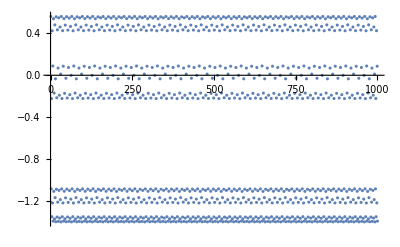

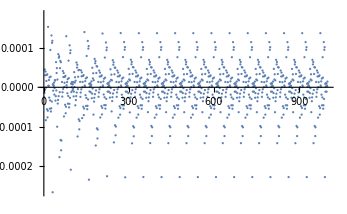

```mathematica
Cs=1.401*Exp[I*(π-0.00001)];
Z=Cs;
Seq=Reap[Do[Sow[Z=Z^2+Cs],{i,1,1000}]][[2,1]];
ListPlot[Re[Seq]]
ListPlot[Im[Seq]]
```